```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/"]
```

/home/waleed/Documents/Wolfram_Mathematica/TransportFunction

```mathematica
Needs["CCompilerDriver`"]
```

```mathematica
CCompilers[]
```

{{Name→GCC,Compiler→CCompilerDriver`GCCCompiler`GCCCompiler,CompilerInstallation→/usr/bin,CompilerName→Automatic}}

```mathematica
Get["MergerTransport/Merger2DProtonShifted.m"]
```

```mathematica
BinCenters[binTable_]:=Block[{resTable},resTable=Table[{(binTable[[i,1,1]]+binTable[[i,1,2]])/2,(binTable[[i,2,1]]+binTable[[i,2,2]])/2},{i,Length[binTable]}];Return[resTable]]
```

```mathematica
FileSorter[Directory_]:=Module[
{filenames=FileNames["TransferResult*",Directory],splitted,orderedlist},
splitted=StringSplit[filenames,"-"];
orderedlist=Ordering[ToExpression[StringTake[splitted[[All,-1]],{1,-5}]]];
filenames[[orderedlist]]
]
```

```mathematica
bin2DGen2[xStart_,xEnd_,yStart_,yEnd_,binNoX_,binNoY_]:=Block[{binLengthX,binLengthY,binList,binsX,binsY},binLengthX=Round[(xEnd-xStart)/binNoX,1/10^6.];binLengthY=Round[(yEnd-yStart)/binNoY,1/10^6.];binsX=Table[{xStart+(i-1) binLengthX,xStart+i binLengthX},{i,binNoX}];binsY=Table[{yStart+(i-1) binLengthY,yStart+i binLengthY},{i,binNoY}];binList=Flatten[Table[{binsX⟦i⟧,binsY⟦j⟧},{i,Length[binsX]},{j,Length[binsY]}],1];Return[binList];]
```

```mathematica
mp
```

9.38272×10^8

```mathematica
mp/c^2
```

1.04397×10^-8

```mathematica
vel=Sqrt[2*15800/1.0439684824055453*^-8]
```

1.7398×10^6

```mathematica
0.1/1.7398020874813108*^6
```

5.74778×10^-8

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2564Bin/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma02564Bin=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.0093;
xEnd=0.0091;
yStart=-0.025;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
xyBins
```

{{{-0.0093,-0.0090125},{-0.025,0.025}},{{-0.0090125,-0.008725},{-0.025,0.025}},{{-0.008725,-0.0084375},{-0.025,0.025}},{{-0.0084375,-0.00815},{-0.025,0.025}},{{-0.00815,-0.0078625},{-0.025,0.025}},{{-0.0078625,-0.007575},{-0.025,0.025}},{{-0.007575,-0.0072875},{-0.025,0.025}},{{-0.0072875,-0.007},{-0.025,0.025}},{{-0.007,-0.0067125},{-0.025,0.025}},{{-0.0067125,-0.006425},{-0.025,0.025}},{{-0.006425,-0.0061375},{-0.025,0.025}},{{-0.0061375,-0.00585},{-0.025,0.025}},{{-0.00585,-0.0055625},{-0.025,0.025}},{{-0.0055625,-0.005275},{-0.025,0.025}},{{-0.005275,-0.0049875},{-0.025,0.025}},{{-0.0049875,-0.0047},{-0.025,0.025}},{{-0.0047,-0.0044125},{-0.025,0.025}},{{-0.0044125,-0.004125},{-0.025,0.025}},{{-0.004125,-0.0038375},{-0.025,0.025}},{{-0.0038375,-0.00355},{-0.025,0.025}},{{-0.00355,-0.0032625},{-0.025,0.025}},{{-0.0032625,-0.002975},{-0.025,0.025}},{{-0.002975,-0.0026875},{-0.025,0.025}},{{-0.0026875,-0.0024},{-0.025,0.025}},{{-0.0024,-0.0021125},{-0.025,0.025}},{{-0.0021125,-0.001825},{-0.025,0.025}},{{-0.001825,-0.0015375},{-0.025,0.025}},{{-0.0015375,-0.00125},{-0.025,0.025}},{{-0.00125,-0.0009625},{-0.025,0.025}},{{-0.0009625,-0.000675},{-0.025,0.025}},{{-0.000675,-0.0003875},{-0.025,0.025}},{{-0.0003875,-0.0001},{-0.025,0.025}},{{-0.0001,0.0001875},{-0.025,0.025}},{{0.0001875,0.000475},{-0.025,0.025}},{{0.000475,0.0007625},{-0.025,0.025}},{{0.0007625,0.00105},{-0.025,0.025}},{{0.00105,0.0013375},{-0.025,0.025}},{{0.0013375,0.001625},{-0.025,0.025}},{{0.001625,0.0019125},{-0.025,0.025}},{{0.0019125,0.0022},{-0.025,0.025}},{{0.0022,0.0024875},{-0.025,0.025}},{{0.0024875,0.002775},{-0.025,0.025}},{{0.002775,0.0030625},{-0.025,0.025}},{{0.0030625,0.00335},{-0.025,0.025}},{{0.00335,0.0036375},{-0.025,0.025}},{{0.0036375,0.003925},{-0.025,0.025}},{{0.003925,0.0042125},{-0.025,0.025}},{{0.0042125,0.0045},{-0.025,0.025}},{{0.0045,0.0047875},{-0.025,0.025}},{{0.0047875,0.005075},{-0.025,0.025}},{{0.005075,0.0053625},{-0.025,0.025}},{{0.0053625,0.00565},{-0.025,0.025}},{{0.00565,0.0059375},{-0.025,0.025}},{{0.0059375,0.006225},{-0.025,0.025}},{{0.006225,0.0065125},{-0.025,0.025}},{{0.0065125,0.0068},{-0.025,0.025}},{{0.0068,0.0070875},{-0.025,0.025}},{{0.0070875,0.007375},{-0.025,0.025}},{{0.007375,0.0076625},{-0.025,0.025}},{{0.0076625,0.00795},{-0.025,0.025}},{{0.00795,0.0082375},{-0.025,0.025}},{{0.0082375,0.008525},{-0.025,0.025}},{{0.008525,0.0088125},{-0.025,0.025}},{{0.0088125,0.0091},{-0.025,0.025}}}

```mathematica
XYBinCentersYHalf2564Bin=BinCenters[xyBins];
```

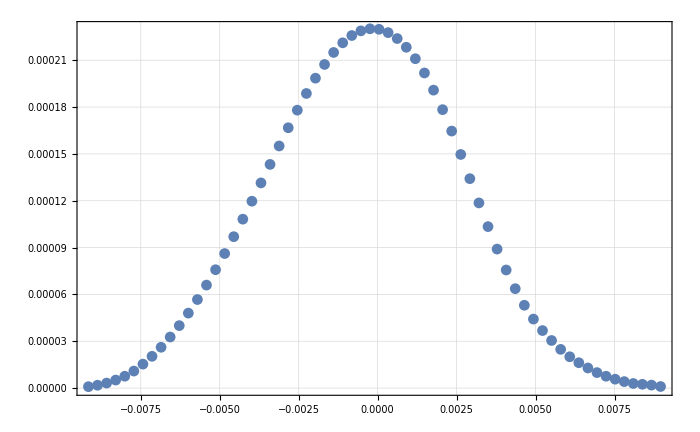

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],d0Spectruma02564Bin[[All,2]]}],PlotRange->All]
```

```mathematica
d0Spectrum2564BinInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],d0Spectruma02564Bin[[All,2]]/Total[d0Spectruma02564Bin[[All,2]]]}]];
```

### a=-1040

```mathematica
da0SubFileNamesa1040=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2564Bin/a-1040/"];
```

```mathematica
da0Spectruma1040=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040,1];
```

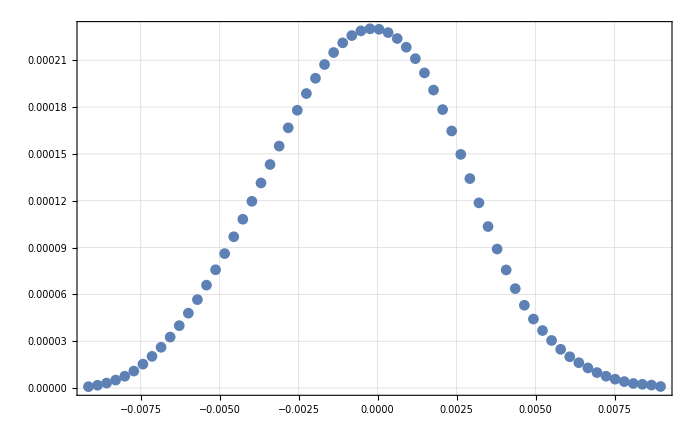

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1040[[All,2]]}],PlotRange->All]
```

### a=-105001

```mathematica
da0SubFileNamesa105001=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2564Bin/a-105001/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2564Bin/a-105001/TransferResult_08-09-20_SC_diffProf_C_da0_2564Bin_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2564Bin/a-105001/TransferResult_08-09-20_SC_diffProf_C_da0_2564Bin_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2564Bin/a-105001/TransferResult_08-09-20_SC_diffProf_C_da0_2564Bin_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2564Bin/a-105001/TransferResult_08-09-20_SC_diffProf_C_da0_2564Bin_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2564Bin/a-105001/TransferResult_08-09-20_SC_diffProf_C_da0_2564Bin_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2564Bin/a-105001/TransferResult_08-09-20_SC_diffProf_C_da0_2564Bin_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2564Bin/a-105001/TransferResult_08-09-20_SC_diffProf_C_da0_2564Bin_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2564Bin/a-105001/TransferResult_08-09-20_SC_diffProf_C_da0_2564Bin_a-1050_57-64.txt}

```mathematica
da0Spectruma105001=Flatten[Import[#,"Table"]&/@da0SubFileNamesa105001,1];
```

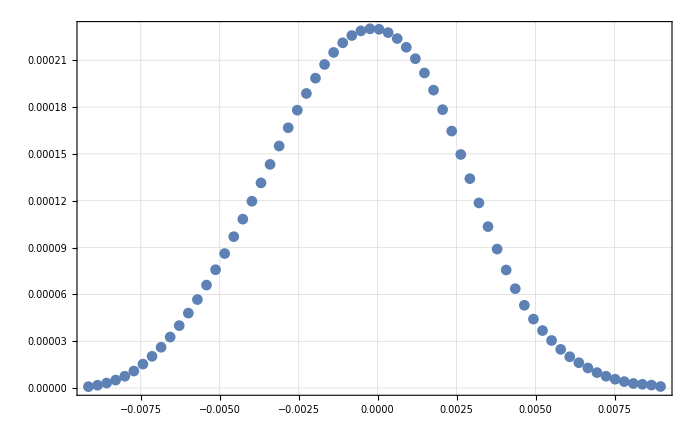

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma105001[[All,2]]}],PlotRange->All]
```

### a=-1045

```mathematica
da0SubFileNamesa1045=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2564Bin/a-1045/"];
```

```mathematica
da0Spectruma1045=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045,1];
```

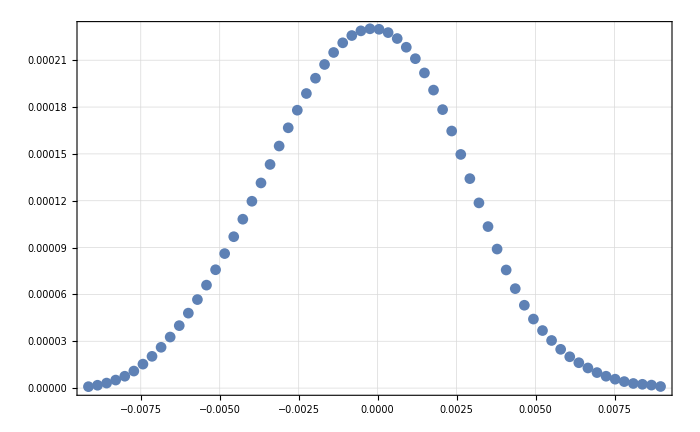

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1045[[All,2]]}],PlotRange->All]
```

### a=-1055

```mathematica
da0SubFileNamesa1055=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2564Bin/a-1055/"];
```

```mathematica
da0Spectruma1055=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055,1];
```

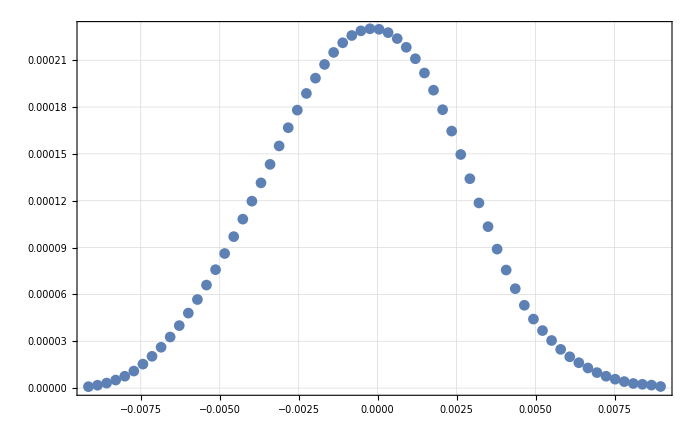

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1055[[All,2]]}],PlotRange->All]
```

### a=-1060

```mathematica
da0SubFileNamesa1060=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2564Bin/a-1060/"];
```

```mathematica
da0Spectruma1060=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060,1];
```

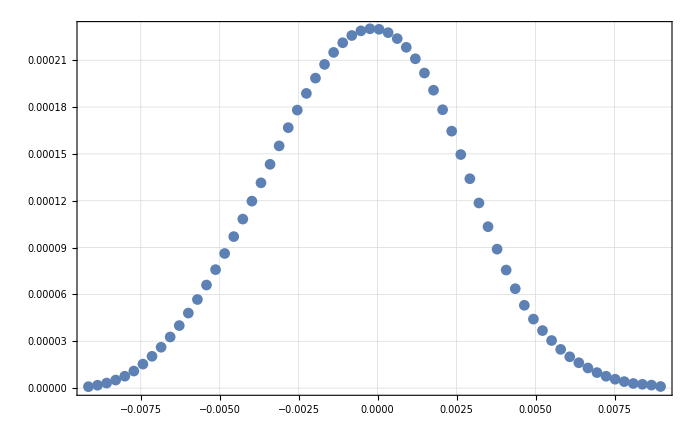

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1060[[All,2]]}],PlotRange->All]
```

### a=-1051

```mathematica
da0SubFileNamesa1051=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_2564Bin/a-1051/"];
```

```mathematica
da0Spectruma1051=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1051,1];
```

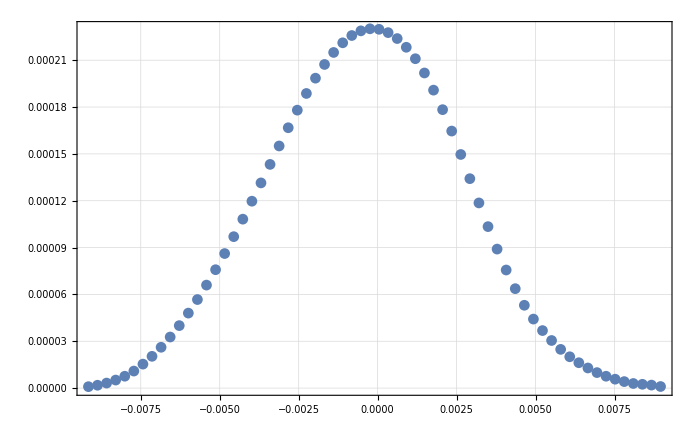

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1051[[All,2]]}],PlotRange->All]
```

```mathematica
da0Spectruma10402564Bin
```

da0Spectruma10402564Bin

```mathematica
da0Spectruma10512564BinInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1051[[All,2]]/Total[da0Spectruma1051[[All,2]]]}]];
da0Spectruma10402564BinInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1040[[All,2]]/Total[da0Spectruma1040[[All,2]]]}]];
da0Spectruma10452564BinInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1045[[All,2]]/Total[da0Spectruma1045[[All,2]]]}]];
da0Spectruma10552564BinInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1055[[All,2]]/Total[da0Spectruma1055[[All,2]]]}]];
da0Spectruma10602564BinInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1060[[All,2]]/Total[da0Spectruma1060[[All,2]]]}]];
```

InterpolatingFunction::dmval: Input value {-0.00929962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

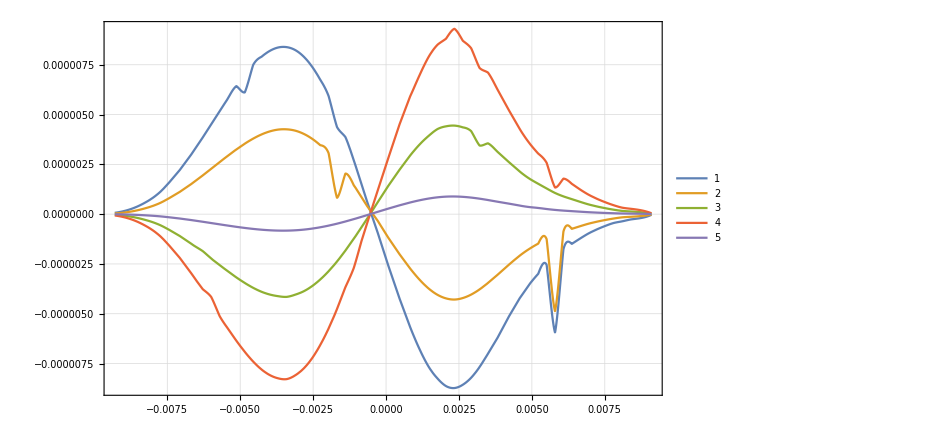

```mathematica
Plot[{
d0Spectrum2564BinInter[x]-da0Spectruma10402564BinInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma10452564BinInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma10552564BinInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma10602564BinInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma10512564BinInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
WFList={#/Total[#]&@da0Spectruma1040[[All,2]],#/Total[#]&@da0Spectruma1045[[All,2]],#/Total[#]&@da0Spectruma1051[[All,2]],#/Total[#]&@da0Spectruma1055[[All,2]],#/Total[#]&@da0Spectruma1060[[All,2]]};
```

```mathematica
bList={-0.104,-.1045,-0.1051,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.1051,-0.1055,-0.106}

```mathematica
da0Spectruma1040[[All,2]][[1;;56]]//Length
```

56

```mathematica
a=Table[i,{i,10}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Delete[a,{{5},{8}}]
```

{1,2,3,4,6,7,9,10}

```mathematica
test[[1]]
```

Part::partd: Part specification test⟦1⟧ is longer than depth of object.

test⟦1⟧

```mathematica
test=Table[{#/Total[#]&@Delete[da0Spectruma1040[[All,2]],{{i},{i+1},{i+2},{i+3}}],#/Total[#]&@Delete[da0Spectruma1045[[All,2]],{{i},{i+1},{i+2},{i+3}}],#/Total[#]&@Delete[da0Spectruma1051[[All,2]],{{i},{i+1},{i+2},{i+3}}],#/Total[#]&@Delete[da0Spectruma1055[[All,2]],{{i},{i+1},{i+2},{i+3}}],#/Total[#]&@Delete[da0Spectruma1060[[All,2]],{{i},{i+1},{i+2},{i+3}}]},{i,1,64,4}];
```

```mathematica
refTest=Table[Delete[d0Spectruma02564Bin[[All,2]],{{i},{i+1},{i+2},{i+3}}],{i,1,64,4}];
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

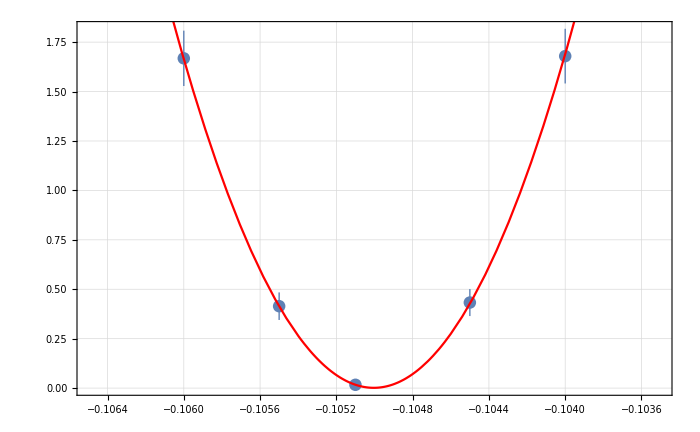
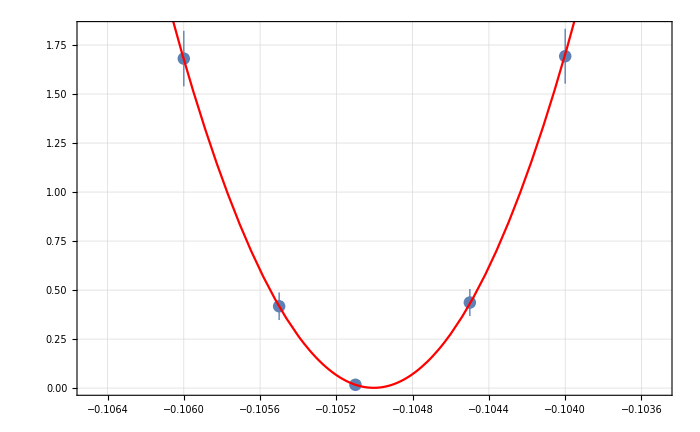
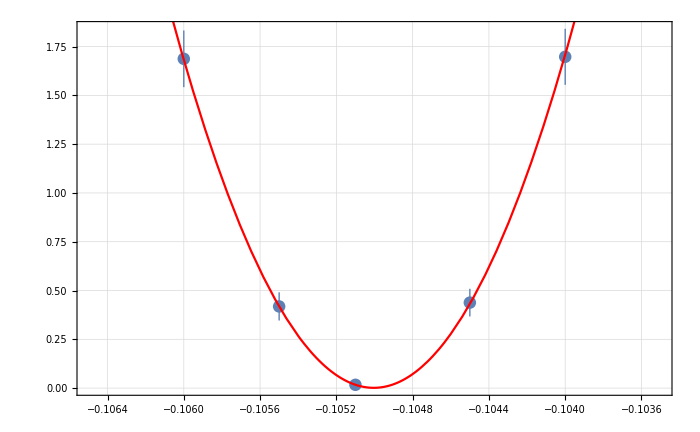
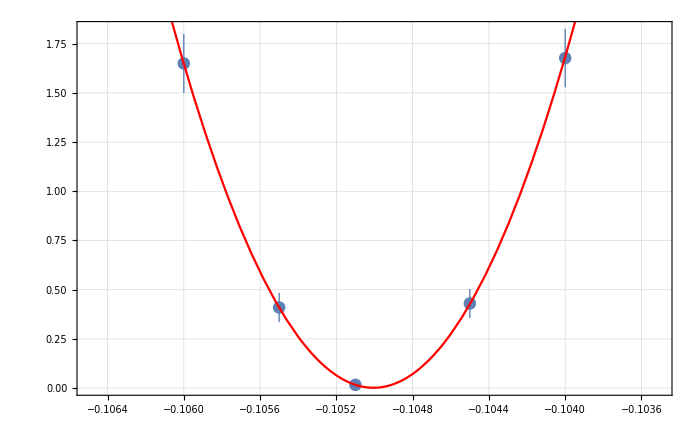
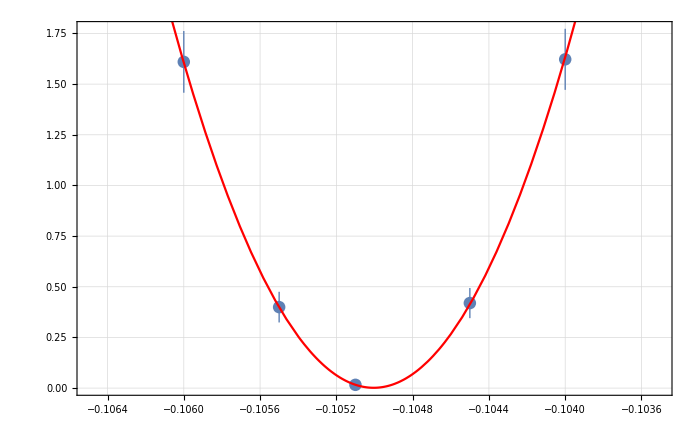
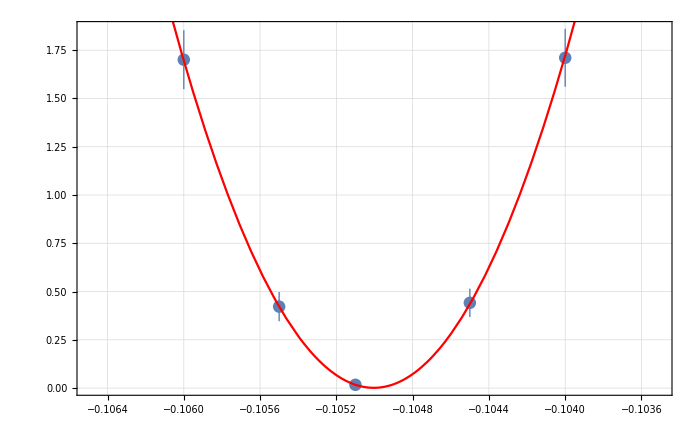
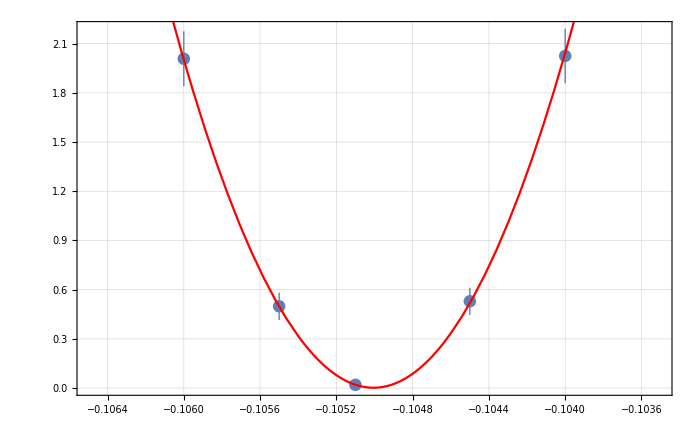
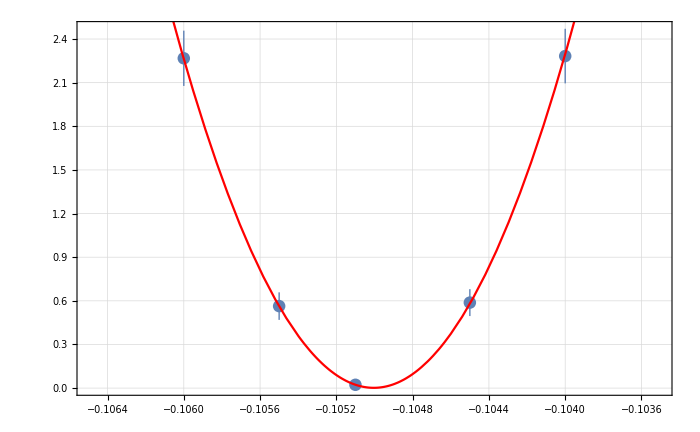
{{{{1.67921×10^-9,4.32702×10^-10,1.66998×10^-11,4.14314×10^-10,1.66805×10^-9},{1.383×10^-10,6.82842×10^-11,1.39423×10^-11,6.96433×10^-11,1.40017×10^-10}},a0 =  | -0.105004
FittedModel[1.38646×10^-12+0.0016754 (0.105004+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105004 | 0.0000205912 | -5099.44 | 3.84552×10^-8
scale | 0.0016754 | 0.0000927615 | 18.0614 | 0.00305146
yoffset | 1.38646×10^-12 | 1.5367×10^-11 | 0.0902231 | 0.936332 | 
 | DF | SS | MS
Model | 3 | 366.314 | 122.105
Error | 2 | 0.0145191 | 0.00725957
Uncorrected Total | 5 | 366.329 | 
Corrected Total | 4 | 332.637 |  | ,-Graphics-},{{{1.69292×10^-9,4.36402×10^-10,1.68287×10^-11,4.1748×10^-10,1.68079×10^-9},{1.39902×10^-10,6.90861×10^-11,1.40972×10^-11,7.04103×10^-11,1.41564×10^-10}},a0 =  | -0.105004
FittedModel[1.43622×10^-12+0.00168864 (0.105004+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105004 | 0.000020663 | -5081.74 | 3.87235×10^-8
scale | 0.00168864 | 0.0000938051 | 18.0016 | 0.00307166
yoffset | 1.43622×10^-12 | 1.55351×10^-11 | 0.0924498 | 0.934767 | 
 | DF | SS | MS
Model | 3 | 363.864 | 121.288
Error | 2 | 0.0145016 | 0.00725081
Uncorrected Total | 5 | 363.879 | 
Corrected Total | 4 | 330.422 |  | ,-Graphics-},{{{1.6976×10^-9,4.38021×10^-10,1.68634×10^-11,4.18445×10^-10,1.68728×10^-9},{1.43593×10^-10,7.0933×10^-11,1.44554×10^-11,7.21889×10^-11,1.45177×10^-10}},a0 =  | -0.105004
FittedModel[1.39953×10^-12+0.0016942 (0.105004+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105004 | 0.0000211307 | -4969.25 | 4.04965×10^-8
scale | 0.0016942 | 0.0000962266 | 17.6063 | 0.00321046
yoffset | 1.39953×10^-12 | 1.59339×10^-11 | 0.0878332 | 0.938012 | 
 | DF | SS | MS
Model | 3 | 347.922 | 115.974
Error | 2 | 0.0156404 | 0.00782021
Uncorrected Total | 5 | 347.937 | 
Corrected Total | 4 | 315.984 |  | ,-Graphics-},{{{1.67691×10^-9,4.2991×10^-10,1.6521×10^-11,4.09581×10^-10,1.64957×10^-9},{1.48693×10^-10,7.3365×10^-11,1.49351×10^-11,7.45614×10^-11,1.49944×10^-10}},a0 =  | -0.105005
FittedModel[1.70962×10^-12+0.00166355 (0.105005+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105005 | 0.0000222599 | -4717.24 | 4.49391×10^-8
scale | 0.00166355 | 0.0000994783 | 16.7227 | 0.00355683
yoffset | 1.70962×10^-12 | 1.64207×10^-11 | 0.104114 | 0.926579 | 
 | DF | SS | MS
Model | 3 | 313.945 | 104.648
Error | 2 | 0.00415402 | 0.00207701
Uncorrected Total | 5 | 313.949 | 
Corrected Total | 4 | 285.196 |  | ,-Graphics-},{{{1.62238×10^-9,4.19537×10^-10,1.61219×10^-11,3.99569×10^-10,1.60978×10^-9},{1.50685×10^-10,7.43035×10^-11,1.51611×10^-11,7.56795×10^-11,1.52261×10^-10}},a0 =  | -0.105004
FittedModel[1.51344×10^-12+0.00161799 (0.105004+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105004 | 0.0000232013 | -4525.78 | 4.88217×10^-8
scale | 0.00161799 | 0.000100931 | 16.0306 | 0.00386878
yoffset | 1.51344×10^-12 | 1.66958×10^-11 | 0.0906481 | 0.936033 | 
 | DF | SS | MS
Model | 3 | 288.573 | 96.1911
Error | 2 | 0.0141149 | 0.00705744
Uncorrected Total | 5 | 288.588 | 
Corrected Total | 4 | 262.032 |  | ,-Graphics-},{{{1.7108×10^-9,4.4153×10^-10,1.70353×10^-11,4.21957×10^-10,1.70076×10^-9},{1.50113×10^-10,7.35954×10^-11,1.51611×10^-11,7.56676×10^-11,1.52381×10^-10}},a0 =  | -0.105004
FittedModel[1.45002×10^-12+0.00170763 (0.105004+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105004 | 0.0000219016 | -4794.35 | 4.35051×10^-8
scale | 0.00170763 | 0.000100804 | 16.9401 | 0.00346663
yoffset | 1.45002×10^-12 | 1.66937×10^-11 | 0.0868602 | 0.938696 | 
 | DF | SS | MS
Model | 3 | 322.799 | 107.6
Error | 2 | 0.014963 | 0.00748148
Uncorrected Total | 5 | 322.814 | 
Corrected Total | 4 | 292.951 |  | ,-Graphics-},{{{2.02494×10^-9,5.29128×10^-10,2.00959×10^-11,4.98606×10^-10,2.00762×10^-9},{1.65538×10^-10,8.26758×10^-11,1.66796×10^-11,8.33457×10^-11,1.67707×10^-10}},a0 =  | -0.105005
FittedModel[2.3036×10^-12+0.00202013 (0.105005+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105005 | 0.0000205267 | -5115.54 | 3.82135×10^-8
scale | 0.00202013 | 0.000111113 | 18.1809 | 0.00301164
yoffset | 2.3036×10^-12 | 1.83626×10^-11 | 0.12545 | 0.91164 | 
 | DF | SS | MS
Model | 3 | 371.106 | 123.702
Error | 2 | 0.0332472 | 0.0166236
Uncorrected Total | 5 | 371.139 | 
Corrected Total | 4 | 337.155 |  | ,-Graphics-},{{{2.28286×10^-9,5.8776×10^-10,2.27185×10^-11,5.63704×10^-10,2.26756×10^-9},{1.87586×10^-10,9.2434×10^-11,1.89346×10^-11,9.46007×10^-11,1.90003×10^-10}},a0 =  | -0.105004
FittedModel[1.86131×10^-12+0.00227766 (0.105004+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105004 | 0.0000205395 | -5112.29 | 3.82621×10^-8
scale | 0.00227766 | 0.000125864 | 18.0961 | 0.00303979
yoffset | 1.86131×10^-12 | 2.0864×10^-11 | 0.0892116 | 0.937043 | 
 | DF | SS | MS
Model | 3 | 367.895 | 122.632
Error | 2 | 0.0136766 | 0.00683832
Uncorrected Total | 5 | 367.909 | 
Corrected Total | 4 | 334.006 |  | ,-Graphics-},{{{2.17852×10^-9,5.64233×10^-10,2.161×10^-11,5.35508×10^-10,2.15618×10^-9},{1.78614×10^-10,8.85003×10^-11,1.7973×10^-11,8.97108×10^-11,1.80368×10^-10}},a0 =  | -0.105005
FittedModel[2.25944×10^-12+0.00216998 (0.105005+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105005 | 0.000020537 | -5112.96 | 3.8252×10^-8
scale | 0.00216998 | 0.000119627 | 18.1395 | 0.00302534
yoffset | 2.25944×10^-12 | 1.97806×10^-11 | 0.114225 | 0.919493 | 
 | DF | SS | MS
Model | 3 | 369.375 | 123.125
Error | 2 | 0.018204 | 0.009102
Uncorrected Total | 5 | 369.393 | 
Corrected Total | 4 | 335.482 |  | ,-Graphics-},{{{1.83592×10^-9,4.78584×10^-10,1.81649×10^-11,4.49053×10^-10,1.81157×10^-9},{1.55857×10^-10,7.70854×10^-11,1.57186×10^-11,7.84023×10^-11,1.57931×10^-10}},a0 =  | -0.105006
FittedModel[2.32131×10^-12+0.00182613 (0.105006+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105006 | 0.00002132 | -4925.23 | 4.12237×10^-8
scale | 0.00182613 | 0.000104579 | 17.4617 | 0.0032636
yoffset | 2.32131×10^-12 | 1.72557×10^-11 | 0.134524 | 0.905305 | 
 | DF | SS | MS
Model | 3 | 342.993 | 114.331
Error | 2 | 0.0229503 | 0.0114751
Uncorrected Total | 5 | 343.016 | 
Corrected Total | 4 | 311.429 |  | ,-Graphics-},{{{1.68958×10^-9,4.39612×10^-10,1.67724×10^-11,4.19264×10^-10,1.67349×10^-9},{1.57987×10^-10,7.79102×10^-11,1.59891×10^-11,8.00321×10^-11,1.60428×10^-10}},a0 =  | -0.105005
FittedModel[1.7996×10^-12+0.00168574 (0.105005+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105005 | 0.000023424 | -4482.77 | 4.97631×10^-8
scale | 0.00168574 | 0.000106201 | 15.8731 | 0.0039455
yoffset | 1.7996×10^-12 | 1.75852×10^-11 | 0.102336 | 0.927826 | 
 | DF | SS | MS
Model | 3 | 283.545 | 94.5151
Error | 2 | 0.0222515 | 0.0111258
Uncorrected Total | 5 | 283.567 | 
Corrected Total | 4 | 257.35 |  | ,-Graphics-},{{{1.72475×10^-9,4.45854×10^-10,1.71539×10^-11,4.25549×10^-10,1.71493×10^-9},{1.55278×10^-10,7.658×10^-11,1.57007×10^-11,7.84659×10^-11,1.57727×10^-10}},a0 =  | -0.105004
FittedModel[1.47739×10^-12+0.00172196 (0.105004+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105004 | 0.0000225239 | -4661.89 | 4.60125×10^-8
scale | 0.00172196 | 0.000104364 | 16.4996 | 0.00365316
yoffset | 1.47739×10^-12 | 1.72939×10^-11 | 0.0854286 | 0.939703 | 
 | DF | SS | MS
Model | 3 | 306.081 | 102.027
Error | 2 | 0.0160013 | 0.00800063
Uncorrected Total | 5 | 306.097 | 
Corrected Total | 4 | 277.88 |  | ,-Graphics-},{{{1.72999×10^-9,4.45868×10^-10,1.72167×10^-11,4.27222×10^-10,1.72058×10^-9},{1.47042×10^-10,7.25547×10^-11,1.48492×10^-11,7.4194×10^-11,1.4914×10^-10}},a0 =  | -0.105004
FittedModel[1.36757×10^-12+0.00172718 (0.105004+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105004 | 0.0000212503 | -4941.27 | 4.09565×10^-8
scale | 0.00172718 | 0.0000987383 | 17.4925 | 0.00325218
yoffset | 1.36757×10^-12 | 1.63683×10^-11 | 0.08355 | 0.941024 | 
 | DF | SS | MS
Model | 3 | 343.767 | 114.589
Error | 2 | 0.0146369 | 0.00731847
Uncorrected Total | 5 | 343.782 | 
Corrected Total | 4 | 312.127 |  | ,-Graphics-},{{{1.67938×10^-9,4.18169×10^-10,1.69972×10^-11,4.2171×10^-10,1.69999×10^-9},{1.42429×10^-10,7.05173×10^-11,1.4325×10^-11,7.15689×10^-11,1.43773×10^-10}},a0 =  | -0.104998
FittedModel[0.+0.00168747 (0.104998+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104998 | 0.000021006 | -4998.49 | 4.00241×10^-8
scale | 0.00168747 | 0.0000953742 | 17.6931 | 0.00317919
yoffset | 0. | 1.59649×10^-11 | 0. | 1. | 
 | DF | SS | MS
Model | 3 | 350.126 | 116.709
Error | 2 | 0.00544035 | 0.00272018
Uncorrected Total | 5 | 350.131 | 
Corrected Total | 4 | 318.154 |  | ,-Graphics-},{{{1.68864×10^-9,4.35021×10^-10,1.68006×10^-11,4.16833×10^-10,1.67825×10^-9},{1.3941×10^-10,6.88211×10^-11,1.40602×10^-11,7.02389×10^-11,1.41209×10^-10}},a0 =  | -0.105004
FittedModel[1.36033×10^-12+0.00168522 (0.105004+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105004 | 0.0000206386 | -5087.73 | 3.86324×10^-8
scale | 0.00168522 | 0.000093534 | 18.0172 | 0.00306636
yoffset | 1.36033×10^-12 | 1.54992×10^-11 | 0.0877677 | 0.938058 | 
 | DF | SS | MS
Model | 3 | 364.557 | 121.519
Error | 2 | 0.0145054 | 0.00725272
Uncorrected Total | 5 | 364.572 | 
Corrected Total | 4 | 331.032 |  | ,-Graphics-},{{{1.67895×10^-9,4.32569×10^-10,1.67011×10^-11,4.14359×10^-10,1.66826×10^-9},{1.38371×10^-10,6.83117×10^-11,1.39521×10^-11,6.96959×10^-11,1.4012×10^-10}},a0 =  | -0.105004
FittedModel[1.36657×10^-12+0.00167537 (0.105004+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105004 | 0.0000206032 | -5096.47 | 3.85×10^-8
scale | 0.00167537 | 0.0000928216 | 18.0494 | 0.00305549
yoffset | 1.36657×10^-12 | 1.53791×10^-11 | 0.0888584 | 0.937291 | 
 | DF | SS | MS
Model | 3 | 365.841 | 121.947
Error | 2 | 0.0145158 | 0.00725791
Uncorrected Total | 5 | 365.856 | 
Corrected Total | 4 | 332.203 |  | ,-Graphics-}}

```mathematica
BigTest=Table[TransferToRefParableFitForProtons0Del[refTest[[i]],test[[i]],bList, 4],{i,Length[refTest]}]
```

```mathematica
uncerTable=Table[{i*4,BigTest[[i,2,1,3,1,1,2,3]]*10^5},{i,Length[BigTest]}]
```

{{4,2.05912},{8,2.0663},{12,2.11307},{16,2.22599},{20,2.32013},{24,2.19016},{28,2.05267},{32,2.05395},{36,2.0537},{40,2.132},{44,2.3424},{48,2.25239},{52,2.12503},{56,2.1006},{60,2.06386},{64,2.06032}}

```mathematica
uncerTable2={{0,0.000020593784447487152*10^5},{4,2.059123293324851},{8,2.066295782200588},{12,2.113070870995616},{16,2.225988821281966},{20,2.320134588001619},{24,2.190156999782772},{28,2.0526689580903654},{32,2.0539463088229826},{36,2.0536976583552655},{40,2.1320014833360923},{44,2.3424044963467643},{48,2.252388401323962},{52,2.1250333081435757},{56,2.1005989165098624},{60,2.06385919876036},{64,2.060320842556555}}
```

{{0,2.05938},{4,2.05912},{8,2.0663},{12,2.11307},{16,2.22599},{20,2.32013},{24,2.19016},{28,2.05267},{32,2.05395},{36,2.0537},{40,2.132},{44,2.3424},{48,2.25239},{52,2.12503},{56,2.1006},{60,2.06386},{64,2.06032}}

```mathematica
Flatten[Append[uncerTable,{{0,0.000020593784447487152}}],0]
```

{{4,2.05912},{8,2.0663},{12,2.11307},{16,2.22599},{20,2.32013},{24,2.19016},{28,2.05267},{32,2.05395},{36,2.0537},{40,2.132},{44,2.3424},{48,2.25239},{52,2.12503},{56,2.1006},{60,2.06386},{64,2.06032},{{0,0.0000205938}}}

```mathematica
11*4
```

44

```mathematica
5*4
```

20

```mathematica
Table[i,{i,1,64,4}][[5]]
```

17

```mathematica
col1=RGBColor[{0.62657923, 0.85464543, 0.22335258}]
```

RGBColor[{0.62657923, 0.85464543, 0.22335258}]

```mathematica
col2=RGBColor[{0.27519116, 0.1949054, 0.49600488}]
```

RGBColor[{0.27519116, 0.1949054, 0.49600488}]

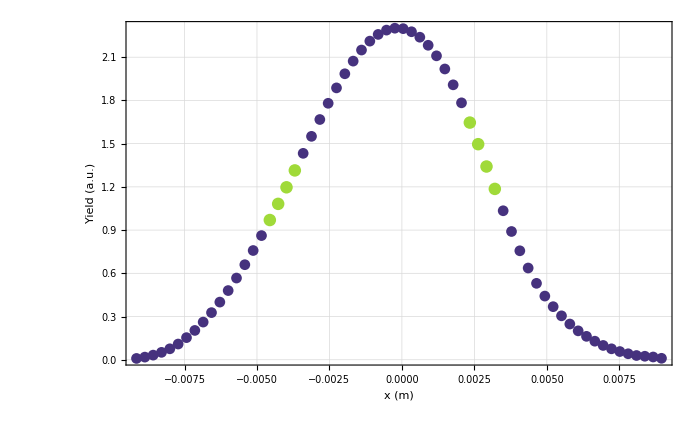

```mathematica
protonBinDepend=Show[ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1051[[All,2]]*10^4}],PlotStyle->col2],ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]][[41;;44]],da0Spectruma1051[[All,2]][[41;;44]]*10^4}],PlotStyle->col1],ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]][[17;;20]],da0Spectruma1051[[All,2]][[17;;20]]*10^4}],PlotStyle->col1],PlotRange->All,FrameStyle->Directive[Thick,Black],Frame->True,GridLines->Automatic,LabelStyle->Directive[FontSize->20,Bold,Black],FrameStyle->Thick,FrameTicksStyle->Thick,FrameLabel->{"x (m)","Yield (a.u.)"}]
```

```mathematica
cOLOR
```

cOLOR

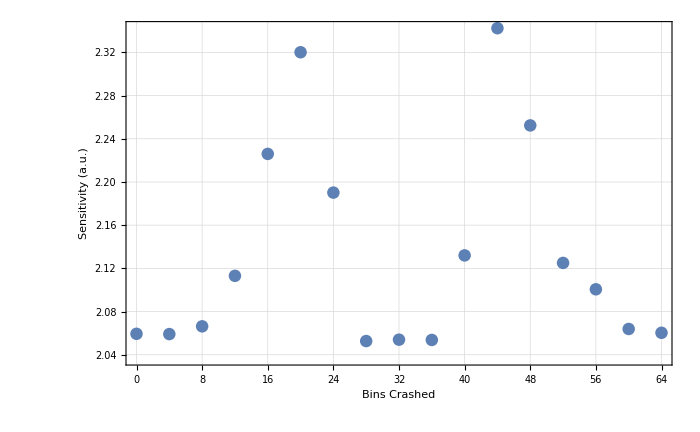

```mathematica
uncertaintyBinCrashProton=ListPlot[uncerTable2,FrameStyle->Directive[Thick,Black],Frame->True,GridLines->Automatic,LabelStyle->Directive[FontSize->20,Bold,Black],FrameStyle->Thick,FrameTicksStyle->Thick,FrameLabel->{"Bins Crashed","Sensitivity (a.u.)"}]
```

```mathematica
Export["~/Desktop/Images/uncertaintyBinCrashProton.svg",uncertaintyBinCrashProton];Export["~/Desktop/Images/protonBinDepend.svg",protonBinDepend];Export["~/Desktop/Images/protonBinDepend.png",protonBinDepend];
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

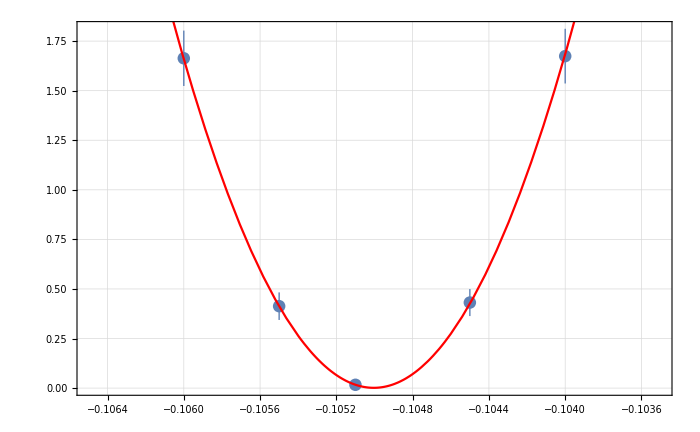
{{{1.6742×10^-9,4.3137×10^-10,1.6652×10^-11,4.13136×10^-10,1.66332×10^-9},{1.37909×10^-10,6.80882×10^-11,1.39045×10^-11,6.94564×10^-11,1.3964×10^-10}},a0 =  | -0.105004
FittedModel[1.37147×10^-12+0.00167052 (0.105004+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105004 | 0.0000205938 | -5098.81 | 3.84647×10^-8
scale | 0.00167052 | 0.0000925068 | 18.0584 | 0.00305246
yoffset | 1.37147×10^-12 | 1.53261×10^-11 | 0.0894859 | 0.93685 | 
 | DF | SS | MS
Model | 3 | 366.199 | 122.066
Error | 2 | 0.0145141 | 0.00725704
Uncorrected Total | 5 | 366.214 | 
Corrected Total | 4 | 332.53 |  | ,-Graphics-}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma02564Bin[[All,2]],WFList,bList, 4]
```

```mathematica
(-0.10500372429304802+0.105)/-0.105
```

0.0000354695

```mathematica
chi0={1.6741975250387273*^-9,4.313699582121289*^-10,1.6652003592908873*^-11,4.131362784868692*^-10,1.6633213195782583*^-9};
```

```mathematica
chierr={1.379088992990758*^-10,6.808822226543915*^-11,1.3904480385582586*^-11,6.945644842064475*^-11,1.396395921327102*^-10};
```

```mathematica
errorplotdata=Transpose[{bList,Table[Around[chi0⟦b⟧,chierr⟦b⟧],{b,1,Length[bList]}]}];
```

```mathematica
rAInvest[[2,1,2]]
```

FittedModel[1.37147×10^-12+0.00167052 (0.105004+b)^2]

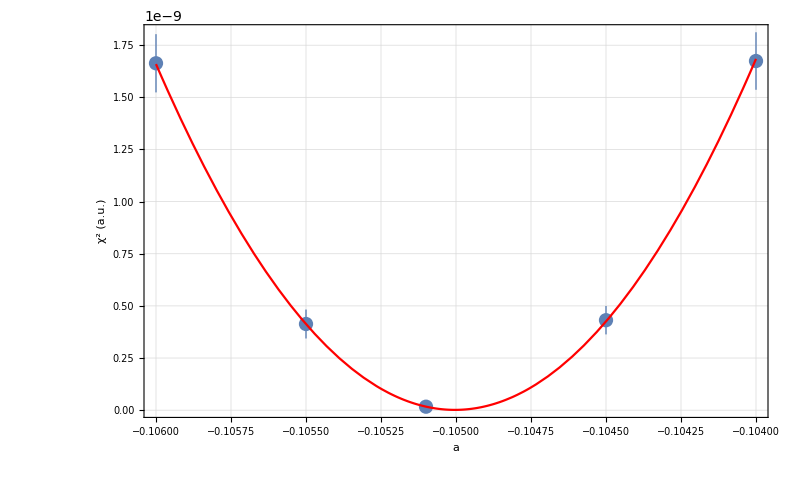

```mathematica
aVarProt=Show[ListPlot[errorplotdata],Plot[rAInvest[[2,1,2]][b],{b,-0.106,-0.104},PlotStyle->Red],PlotRange->All,ImageSize->800,FrameStyle->Directive[Thick,Black],Frame->True,GridLines->Automatic,LabelStyle->Directive[FontSize->20,Bold,Black],FrameStyle->Thick,FrameTicksStyle->Thick,FrameLabel->{"a","χ^2 (a.u.)"}]
```

```mathematica
Export["~/Desktop/Images/aVarProt.svg",aVarProt];Export["~/Desktop/Images/aVarProt.png",aVarProt]
```

~/Desktop/Images/aVarProt.png

```mathematica
rAInvest[[2,1,2]]
```

FittedModel[1.37147×10^-12+0.00167052 (0.105004+b)^2]

```mathematica
fitChiSqCalc[{1.6741975250387273*^-9,4.313699582121289*^-10,1.6652003592908873*^-11,4.131362784868692*^-10,1.6633213195782583*^-9},{1.379088992990758*^-10,6.808822226543915*^-11,1.3904480385582586*^-11,6.945644842064475*^-11,1.396395921327102*^-10},rAInvest[[2,1,2]]]
```

fitChiSqCalc[{1.6742×10^-9,4.3137×10^-10,1.6652×10^-11,4.13136×10^-10,1.66332×10^-9},{1.37909×10^-10,6.80882×10^-11,1.39045×10^-11,6.94564×10^-11,1.3964×10^-10},FittedModel[1.37147×10^-12+0.00167052 (0.105004+b)^2]]

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)
```

0.000040.00020

```mathematica
-0.10499690735958792
```

-0.104997

```mathematica
*0.005
```

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/10^-6
```

35.196.

```mathematica
binlist = {{8, Around[0.0000879011, 0.0006]}, {16, 
   Around[0.0000956466, 0.0004]}, {32, Around[0.00015, 0.00029]}, {48,
    Around[0.000003, 0.00032]}, {64, Around[0.00004, 0.00020]}}
```

{{8,0.00000.0006},{16,0.00000.0004},{32,0.000150.00029},{48,0.000000.00032},{64,0.000040.00020}}

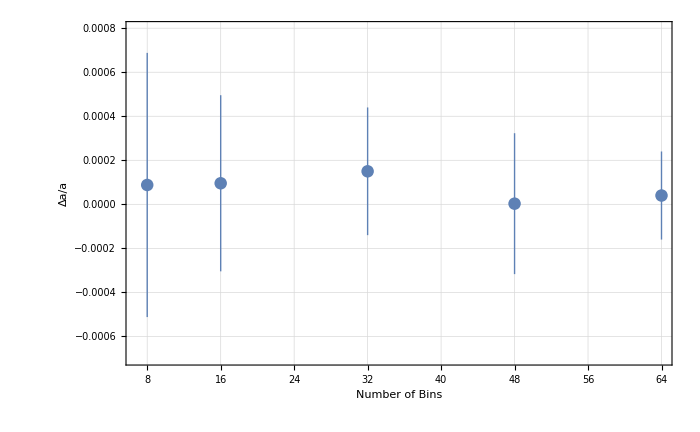

```mathematica
binDepend=ListPlot[binlist,PlotRange->{All,{-0.0007,0.0008}},FrameStyle->Directive[Thick,Black],Frame->True,GridLines->Automatic,LabelStyle->Directive[FontSize->20,Bold,Black],FrameStyle->Thick,FrameTicksStyle->Thick,FrameLabel->{"Number of Bins","Δa/a"}]
```

```mathematica
Export["~/Desktop/Images/ProtonBinNoDepend.png",binDepend];Export["~/Desktop/Images/ProtonBinNoDepend.svg",binDepend];
```

# XDet Shift

## Plus Shift

### a=-1050

```mathematica
da0SubFileNamesa1050detShift=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift/a-1050/"];
```

```mathematica
da0Spectruma1050detShift=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050detShift,1];
```

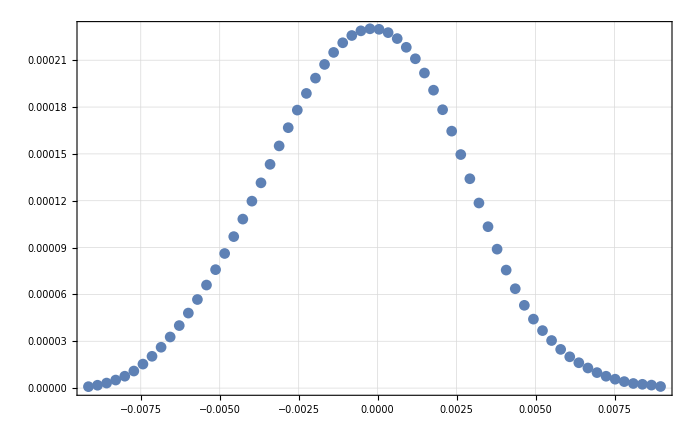

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1050detShift[[All,2]]}],PlotRange->All]
```

### a=-1051

```mathematica
da0SubFileNamesa1051detShift=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift/a-1051/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift/a-1051/TransferResult_08-09-20_SC_diffProf_D_ddetShift_a-1051_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift/a-1051/TransferResult_08-09-20_SC_diffProf_D_ddetShift_a-1051_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift/a-1051/TransferResult_08-09-20_SC_diffProf_D_ddetShift_a-1051_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift/a-1051/TransferResult_08-09-20_SC_diffProf_D_ddetShift_a-1051_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift/a-1051/TransferResult_08-09-20_SC_diffProf_D_ddetShift_a-1051_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift/a-1051/TransferResult_08-09-20_SC_diffProf_D_ddetShift_a-1051_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift/a-1051/TransferResult_08-09-20_SC_diffProf_D_ddetShift_a-1051_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift/a-1051/TransferResult_08-09-20_SC_diffProf_D_ddetShift_a-1051_57-64.txt}

```mathematica
da0Spectruma1051detShift=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1051detShift,1]
```

{{15.5207,9.18778×10^-7},{15.799,1.8352×10^-6},{15.7261,3.21778×10^-6},{22.1898,5.1484×10^-6},{265.925,7.60946×10^-6},{396.653,0.0000109232},{671.116,0.0000153714},{834.889,0.0000203708},{883.065,0.0000261714},{873.887,0.0000327383},{877.518,0.000040044},{947.749,0.0000480538},{969.998,0.0000567336},{897.38,0.000066005},{1068.01,0.0000758623},{1202.3,0.0000862122},{1217.99,0.0000970212},{1314.25,0.000108241},{1433.64,0.00011974},{1356.58,0.000131463},{1593.61,0.000143314},{1743.09,0.000155113},{1866.84,0.000166793},{2098.74,0.000178052},{2469.02,0.000188733},{2540.99,0.000198533},{2507.06,0.000207299},{3052.46,0.000214992},{3190.39,0.000221169},{3003.47,0.000225825},{2972.82,0.000228809},{2908.25,0.000230124},{3285.89,0.000229788},{3524.83,0.000227657},{3324.7,0.00022385},{3789.53,0.000218262},{4101.31,0.000210921},{3898.74,0.000201787},{3669.08,0.000190795},{3541.91,0.000178284},{3273.3,0.000164566},{3483.2,0.000149571},{3139.07,0.000134079},{2765.94,0.000118542},{3212.31,0.000103366},{2825.18,0.0000889786},{2847.17,0.0000755876},{2698.47,0.000063639},{2275.42,0.0000530122},{2005.71,0.000044172},{2042.49,0.0000368196},{1867.91,0.0000304668},{1512.12,0.0000247843},{1005.89,0.0000200495},{911.982,0.0000162394},{872.764,0.0000128744},{124.125,9.92018×10^-6},{87.9561,7.58789×10^-6},{82.3118,5.69572×10^-6},{77.0571,4.15392×10^-6},{84.4016,2.94892×10^-6},{63.8416,2.43263×10^-6},{52.1902,1.91561×10^-6},{53.5079,1.01885×10^-6}}

```mathematica
da0Spectruma1051detShift//Length
```

64

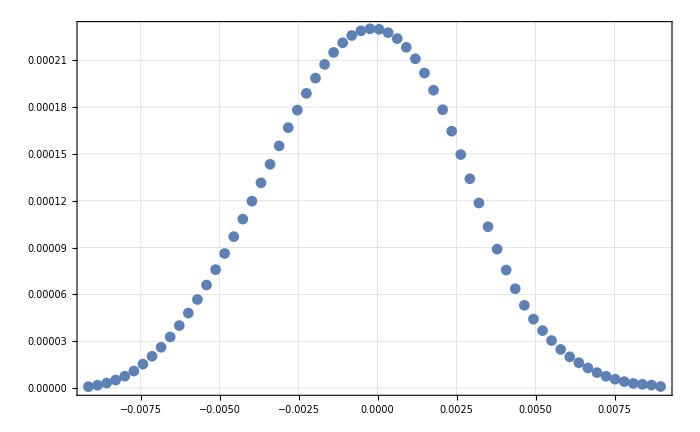

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1051detShift[[All,2]]}],PlotRange->All]
```

### a=-1025

```mathematica
da0SubFileNamesa1025detShift=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift/a-1025/"];
```

```mathematica
da0Spectruma1025detShift=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1025detShift,1];
```

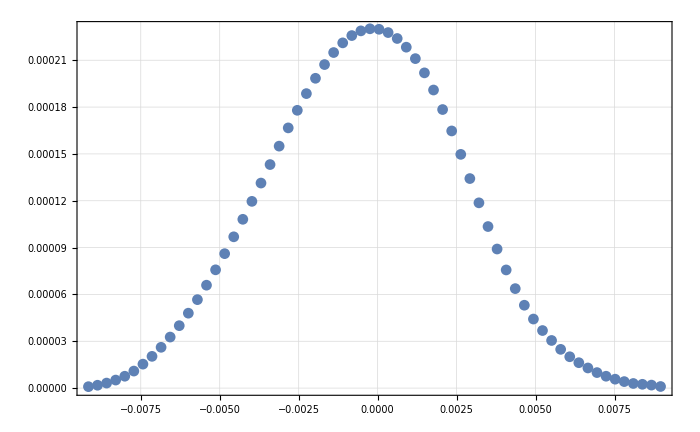

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1025detShift[[All,2]]}],PlotRange->All]
```

### a=-1040

```mathematica
da0SubFileNamesa1040detShift=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift/a-1040/"];
```

```mathematica
da0Spectruma1040detShift=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040detShift,1];
```

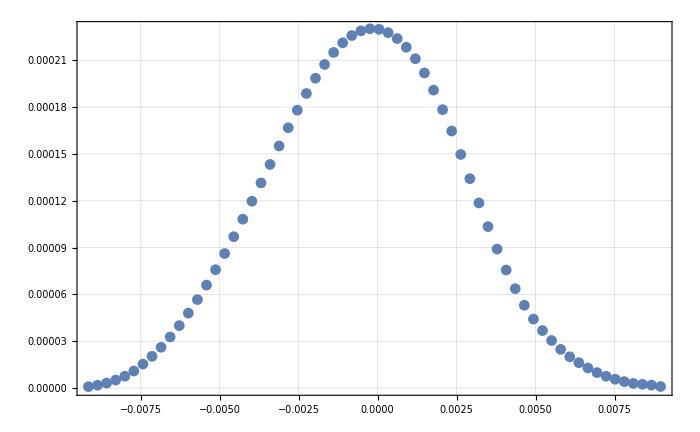

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1040detShift[[All,2]]}],PlotRange->All]
```

### a=-1045

```mathematica
da0SubFileNamesa1045detShift=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift/a-1045/"];
```

```mathematica
da0Spectruma1045detShift=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045detShift,1];
```

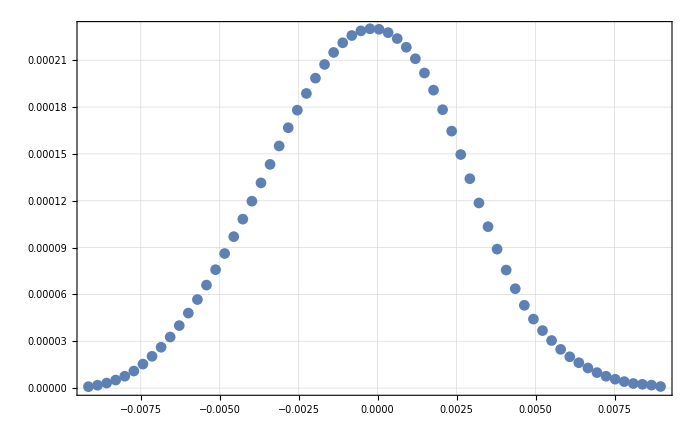

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1045detShift[[All,2]]}],PlotRange->All]
```

### a=-1055

```mathematica
da0SubFileNamesa1055detShift=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift/a-1055/"];
```

```mathematica
da0Spectruma1055detShift=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055detShift,1];
```

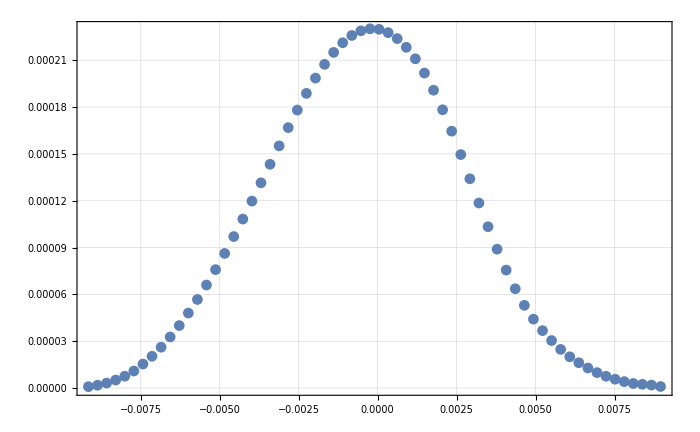

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1055detShift[[All,2]]}],PlotRange->All]
```

### a=-1060

```mathematica
da0SubFileNamesa1060detShift=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060detShift=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060detShift,1];
```

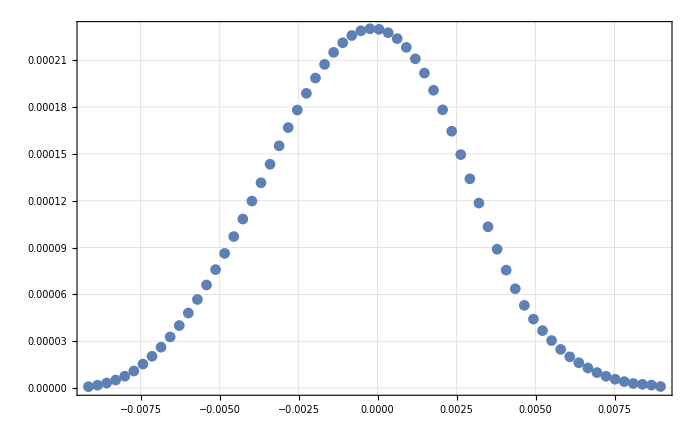

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1060detShift[[All,2]]}],PlotRange->All]
```

```mathematica
#/Total[#]&@da0Spectruma1040detShift[[All,2]]==da0Spectruma1040detShift[[All,2]]/Total[da0Spectruma1040detShift[[All,2]]]
```

True

```mathematica
da0Spectruma1040detShift[[All,2]]/Total[da0Spectruma1040detShift[[All,2]]]
```

{0.000148892,0.000297403,0.00052146,0.000834335,0.00123318,0.0017702,0.0024911,0.00330134,0.00424145,0.0053058,0.0064899,0.00778848,0.00919511,0.010698,0.0122959,0.0139738,0.0157262,0.0175453,0.0194098,0.0213109,0.0232327,0.0251461,0.027041,0.0288675,0.0306004,0.0321907,0.0336134,0.0348622,0.0358653,0.0366218,0.0371071,0.0373218,0.0372687,0.0369244,0.0363083,0.0354032,0.0342137,0.0327334,0.0309513,0.0289227,0.0266981,0.0242661,0.0217533,0.019233,0.0167712,0.0144371,0.0122645,0.0103259,0.00860177,0.00716745,0.00597452,0.00494376,0.00402167,0.00325347,0.00263529,0.00208925,0.00160987,0.00123141,0.000924354,0.00067415,0.000478597,0.000394808,0.000310898,0.000165363}

```mathematica
da0Spectruma1050detShiftInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1050detShift[[All,2]]}]];
da0Spectruma1040detShiftInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1040detShift[[All,2]]}]];
da0Spectruma1045detShiftInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1045detShift[[All,2]]}]];
da0Spectruma1055detShiftInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1055detShift[[All,2]]}]];
da0Spectruma1060detShiftInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1060detShift[[All,2]]}]];
```

InterpolatingFunction::dmval: Input value {-0.00929962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

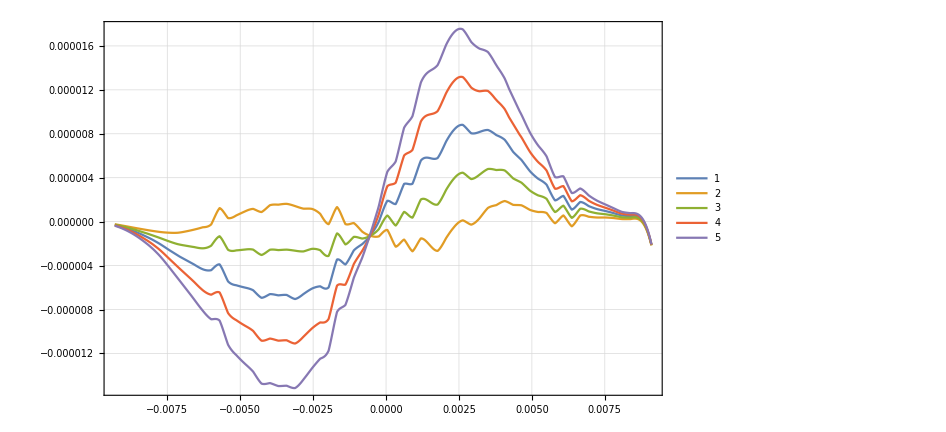

```mathematica
Plot[{
d0Spectrum2564BinInter[x]-da0Spectruma1050detShiftInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1040detShiftInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1045detShiftInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1055detShiftInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1060detShiftInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
detShiftList={#/Total[#]&@da0Spectruma1025detShift[[All,2]],#/Total[#]&@da0Spectruma1040detShift[[All,2]],#/Total[#]&@da0Spectruma1045detShift[[All,2]],#/Total[#]&@da0Spectruma1050detShift[[All,2]],#/Total[#]&@da0Spectruma1055detShift[[All,2]],#/Total[#]&@da0Spectruma1060detShift[[All,2]]};
```

```mathematica
bList2={-0.1025,-0.104,-.1045,-.1055,-0.1060}
```

{-0.1025,-0.104,-0.1045,-0.1055,-0.106}

```mathematica
detShiftList2={#/Total[#]&@da0Spectruma1025detShift[[All,2]],#/Total[#]&@da0Spectruma1040detShift[[All,2]],#/Total[#]&@da0Spectruma1045detShift[[All,2]],#/Total[#]&@da0Spectruma1055detShift[[All,2]],#/Total[#]&@da0Spectruma1060detShift[[All,2]]};
```

```mathematica
bList={-0.1025,-0.104,-.1045,-.1050,-.1055,-0.1060}
```

{-0.1025,-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
list={1.016245369606487*^-9,4.6451699865116656*^-10,1.4287088189163012*^-9,5.9173654694905036*^-9,9.362411587462943*^-9,1.3652094533538111*^-8,4.257746948980328*^-9,7.903512754708413*^-11,3.490548894724692*^-10,1.4548417203113958*^-9,3.3876775606126827*^-9,6.151819821728061*^-9}
```

{1.01625×10^-9,4.64517×10^-10,1.42871×10^-9,5.91737×10^-9,9.36241×10^-9,1.36521×10^-8,4.25775×10^-9,7.90351×10^-11,3.49055×10^-10,1.45484×10^-9,3.38768×10^-9,6.15182×10^-9}

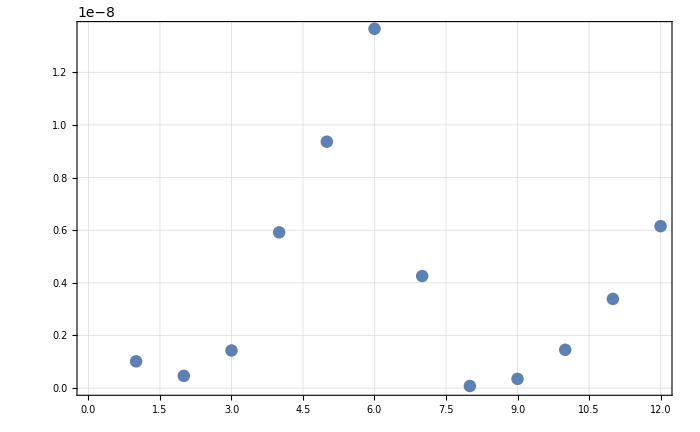

```mathematica
ListPlot[list]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

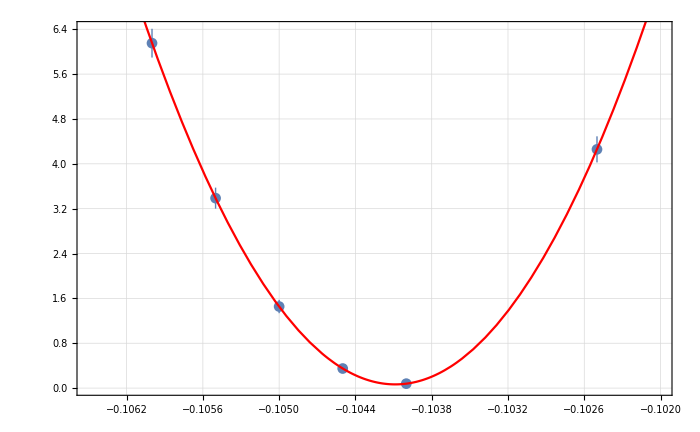
{{{4.25775×10^-9,7.90351×10^-11,3.49055×10^-10,1.45484×10^-9,3.38768×10^-9,6.15182×10^-9},{2.32577×10^-10,3.31874×10^-11,5.25073×10^-11,1.18825×10^-10,1.87443×10^-10,2.56496×10^-10}},a0 =  | -0.104087
FittedModel[6.62681×10^-11+0.00166375 (0.104087+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104087 | 0.0000207795 | -5009.13 | 1.75462×10^-11
scale | 0.00166375 | 0.0000539296 | 30.8503 | 0.0000748257
yoffset | 6.62681×10^-11 | 2.86544×10^-11 | 2.31267 | 0.103777 | 
 | DF | SS | MS
Model | 3 | 1436.78 | 478.927
Error | 3 | 0.000644318 | 0.000214773
Uncorrected Total | 6 | 1436.78 | 
Corrected Total | 5 | 1205.27 |  | ,-Graphics-}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma02564Bin[[All,2]],detShiftList,bList, 4]
```

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)
```

-0.008690.00020

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/10^-6
```

-8693.198.

```mathematica
.001*8693
```

8.693

```mathematica
protDetShiftList={{-1*10^-6,-0.10592422242131855},{-50*10^-9,-0.10503419055752933},{50*10^-9,-0.10495768469584163},{1*10^-6,-0.10408719799304411},{2*10^-6,-0.1031657894775463},{10*10^-6,-0.09605444449437454}}
```

{{-1/1000000,-0.105924},{-1/20000000,-0.105034},{1/20000000,-0.104958},{1/1000000,-0.104087},{1/500000,-0.103166},{1/100000,-0.0960544}}

```mathematica
f=LinearModelFit[protDetShiftList,{1,x},x]
```

FittedModel[-0.104994+895.212 x]

```mathematica
f2=LinearModelFit[{{-1/1000000,-0.10592422242131855},{-1/20000000,-0.10503419055752933},{1/20000000,-0.10495768469584163},{1/1000000,-0.10408719799304411},{1/500000,-0.1031657894775463}},{1,x},x]
```

FittedModel[-0.105001+917.753 x]

```mathematica
f2[10*10^-6]
```

-0.0958234

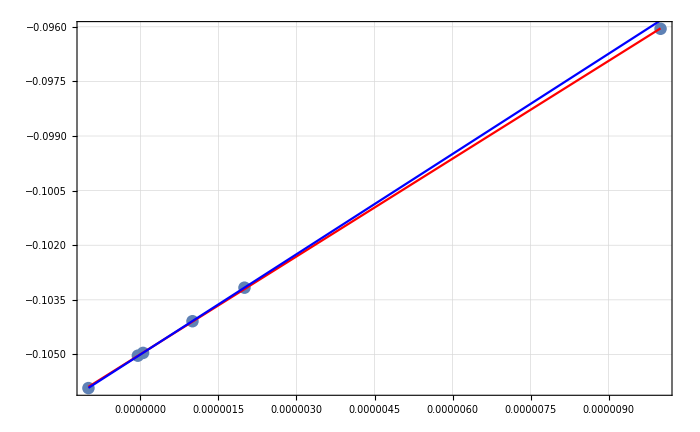

```mathematica
Show[ListPlot[protDetShiftList,PlotRange->All],Plot[f[x],{x,-1*10^-6,10*10^-6},PlotStyle->Red],Plot[f2[x],{x,-1*10^-6,10*10^-6},PlotStyle->Blue]]
```

## 5um Plus Shift

### a=-1005

```mathematica
da0SubFileNamesa10055umdetShift=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift5um/a-1005/"];
```

```mathematica
da0Spectruma10055umdetShift=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10055umdetShift,1];
```

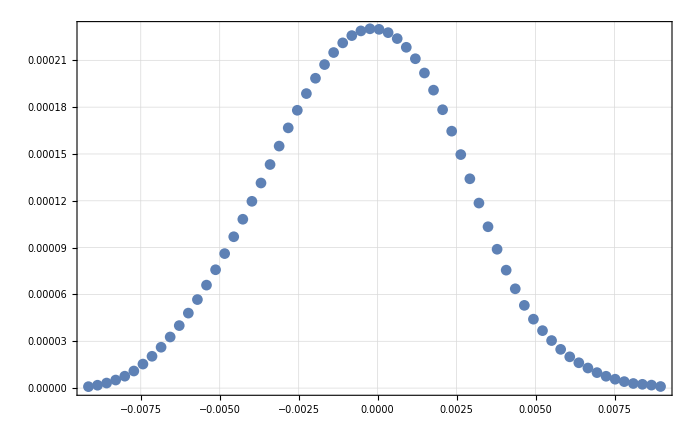

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma10055umdetShift[[All,2]]}],PlotRange->All]
```

### a=-1010

```mathematica
da0SubFileNamesa10105umdetShift=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift5um/a-1010/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift5um/a-1010/TransferResult_08-09-20_SC_diffProf_C_ddetShift5um_a-1010_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift5um/a-1010/TransferResult_08-09-20_SC_diffProf_C_ddetShift5um_a-1010_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift5um/a-1010/TransferResult_08-09-20_SC_diffProf_C_ddetShift5um_a-1010_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift5um/a-1010/TransferResult_08-09-20_SC_diffProf_C_ddetShift5um_a-1010_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift5um/a-1010/TransferResult_08-09-20_SC_diffProf_C_ddetShift5um_a-1010_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift5um/a-1010/TransferResult_08-09-20_SC_diffProf_C_ddetShift5um_a-1010_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift5um/a-1010/TransferResult_08-09-20_SC_diffProf_C_ddetShift5um_a-1010_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift5um/a-1010/TransferResult_08-09-20_SC_diffProf_C_ddetShift5um_a-1010_57-64.txt}

```mathematica
da0Spectruma10105umdetShift=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10105umdetShift,1]
```

{{25.3726,9.26202×10^-7},{25.4692,1.84595×10^-6},{25.4476,3.23193×10^-6},{40.1012,5.16034×10^-6},{417.251,7.62806×10^-6},{638.09,0.0000109459},{1078.76,0.0000153946},{1330.29,0.0000203941},{1403.45,0.0000261918},{1414.82,0.0000327531},{1488.47,0.0000400581},{1523.84,0.0000480566},{1534.82,0.0000567294},{1535.37,0.0000659928},{1740.82,0.0000758425},{1864.7,0.0000861898},{1909.67,0.0000969871},{2039.15,0.000108202},{2203.42,0.000119695},{2116.42,0.000131422},{2315.11,0.00014327},{2518.96,0.000155071},{2683.44,0.000166749},{3063.65,0.00017802},{3973.,0.000188711},{4080.96,0.000198532},{4200.52,0.000207289},{5005.77,0.000215001},{5157.22,0.000221185},{4758.45,0.000225846},{4568.94,0.000228846},{4852.84,0.000230201},{5691.58,0.000229838},{5767.3,0.000227716},{5699.04,0.000223914},{6410.15,0.000218327},{6853.12,0.000210995},{6449.51,0.000201854},{6766.79,0.000190863},{6230.86,0.00017832},{5481.75,0.000164588},{5752.07,0.000149584},{5299.9,0.000134081},{4650.75,0.000118521},{5290.15,0.000103352},{4848.39,0.0000889361},{4649.1,0.0000755488},{4546.39,0.0000636079},{3421.08,0.0000529887},{3034.45,0.0000441483},{3142.36,0.0000368},{2820.88,0.0000304475},{2453.63,0.0000248072},{1627.76,0.0000200369},{1458.47,0.0000162269},{1381.9,0.0000128632},{158.67,9.91094×10^-6},{115.109,7.57798×10^-6},{107.419,5.68672×10^-6},{101.158,4.14609×10^-6},{110.349,2.94236×10^-6},{83.7299,2.42705×10^-6},{68.4243,1.911×10^-6},{75.2971,1.01542×10^-6}}

```mathematica
da0Spectruma1051detShift//Length
```

64

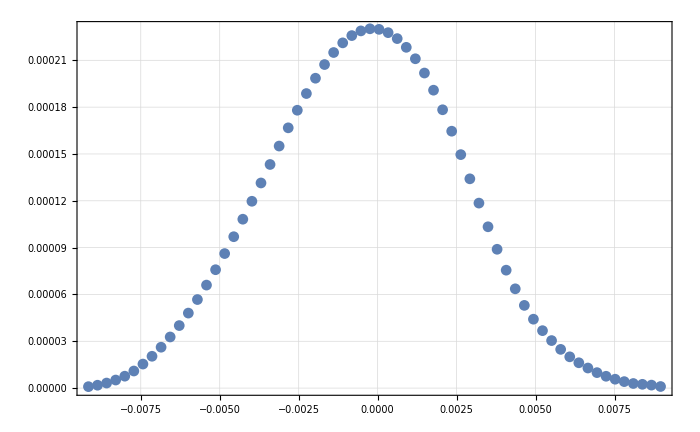

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma10105umdetShift[[All,2]]}],PlotRange->All]
```

### a=-1020

```mathematica
da0SubFileNamesa10205umdetShift=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift5um/a-1020/"];
```

```mathematica
da0Spectruma10205umdetShift=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10205umdetShift,1]
```

{{26.3871,9.26825×10^-7},{23.3912,1.84719×10^-6},{23.5243,3.23408×10^-6},{35.7878,5.16374×10^-6},{377.385,7.63304×10^-6},{558.647,0.000010953},{960.02,0.0000154044},{1198.38,0.0000204069},{1254.43,0.0000262081},{1178.52,0.0000327729},{1199.91,0.0000400817},{1290.98,0.0000480842},{1298.27,0.000056761},{1280.82,0.0000660283},{1435.79,0.0000758818},{1598.86,0.0000862272},{1855.39,0.0000970328},{1943.45,0.00010825},{2167.27,0.000119745},{2098.96,0.000131473},{2367.92,0.000143321},{2593.72,0.000155121},{2788.17,0.000166797},{3207.42,0.000178065},{3330.73,0.000188752},{3305.63,0.000198567},{3559.11,0.000207319},{4094.46,0.000215023},{4004.75,0.0002212},{4022.98,0.000225853},{3857.46,0.000228845},{3888.,0.000230152},{5092.3,0.000229822},{5548.68,0.000227692},{5237.41,0.000223882},{5972.05,0.000218289},{6348.37,0.000210951},{5893.01,0.000201805},{5849.74,0.000190811},{5653.03,0.000178266},{5369.39,0.000164533},{5865.85,0.00014953},{5118.89,0.000134029},{4470.08,0.000118473},{5332.14,0.000103308},{4645.02,0.0000888968},{4541.77,0.0000755148},{4262.75,0.0000635781},{3462.94,0.0000529633},{3072.31,0.0000441266},{3190.44,0.0000367814},{2886.48,0.0000304317},{2545.19,0.000024794},{1614.84,0.0000200259},{1433.61,0.0000162176},{1392.55,0.0000128557},{186.847,9.90494×10^-6},{135.914,7.57304×10^-6},{134.313,5.68307×10^-6},{128.761,4.14335×10^-6},{131.524,2.94036×10^-6},{99.2503,2.42539×10^-6},{81.3403,1.90969×10^-6},{84.5948,1.01469×10^-6}}

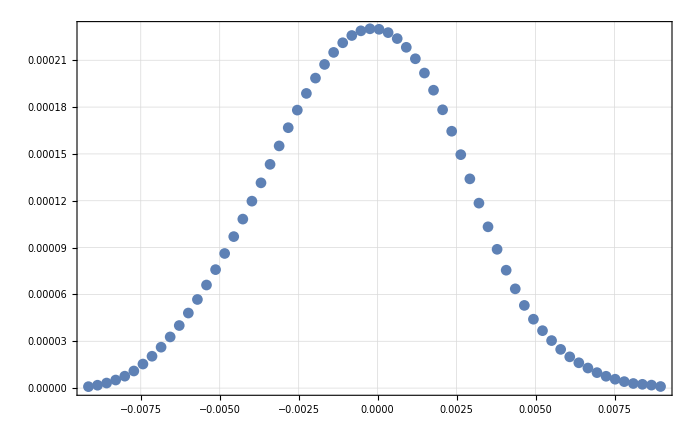

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma10205umdetShift[[All,2]]}],PlotRange->All]
```

### a=-9000

```mathematica
da0SubFileNamesa90005umdetShift=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift5um/a-9000/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift5um/a-9000/TransferResult_08-09-20_SC_diffProf_C_ddetShift5um_a-9000_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift5um/a-9000/TransferResult_08-09-20_SC_diffProf_C_ddetShift5um_a-9000_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift5um/a-9000/TransferResult_08-09-20_SC_diffProf_C_ddetShift5um_a-9000_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift5um/a-9000/TransferResult_08-09-20_SC_diffProf_C_ddetShift5um_a-9000_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift5um/a-9000/TransferResult_08-09-20_SC_diffProf_C_ddetShift5um_a-9000_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift5um/a-9000/TransferResult_08-09-20_SC_diffProf_C_ddetShift5um_a-9000_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift5um/a-9000/TransferResult_08-09-20_SC_diffProf_C_ddetShift5um_a-9000_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift5um/a-9000/TransferResult_08-09-20_SC_diffProf_C_ddetShift5um_a-9000_57-64.txt}

```mathematica
da0Spectruma90005umdetShift=Flatten[Import[#,"Table"]&/@da0SubFileNamesa90005umdetShift,1]
```

{{21.6921,1.42441×10^-6},{25.067,2.83331×10^-6},{30.8331,4.93792×10^-6},{352.794,7.72154×10^-6},{469.171,0.0000116057},{930.747,0.0000169786},{1209.38,0.000023222},{1145.04,0.0000306127},{1428.04,0.0000390859},{1402.93,0.0000485515},{1458.79,0.0000589269},{1612.79,0.0000701077},{1721.36,0.0000819764},{1718.88,0.0000943719},{1815.86,0.000107207},{1973.93,0.000120277},{1800.96,0.000133483},{1894.24,0.000146674},{2055.8,0.000159569},{2214.86,0.000171965},{2539.91,0.000183875},{3064.63,0.000194962},{2889.34,0.000204884},{2556.33,0.000213605},{3658.3,0.000220992},{3736.19,0.00022669},{3948.01,0.000230708},{3936.49,0.000232949},{3852.61,0.000233281},{3910.27,0.000231751},{4228.3,0.000228464},{4405.79,0.000223373},{4156.25,0.000216667},{4258.39,0.000208416},{4142.26,0.000198764},{4958.6,0.000187807},{5060.19,0.000175787},{4629.5,0.000162815},{4538.51,0.000149204},{4479.84,0.00013523},{4102.8,0.000120754},{3479.46,0.000106668},{3649.45,0.0000930483},{3816.87,0.0000802052},{3798.74,0.0000683619},{3686.09,0.0000576187},{3423.71,0.000048094},{2674.31,0.0000398571},{2120.3,0.0000328082},{1750.55,0.0000267902},{1418.52,0.00002185},{990.793,0.0000176405},{975.724,0.0000141596},{157.259,0.0000110836},{135.938,8.70108×10^-6},{112.687,6.70991×10^-6},{125.513,5.08823×10^-6},{125.524,3.79985×10^-6},{116.511,2.76679×10^-6},{103.1,1.95911×10^-6},{101.693,1.34751×10^-6},{54.1611,1.22661×10^-6},{44.6688,1.01946×10^-6},{41.4032,5.66338×10^-7}}

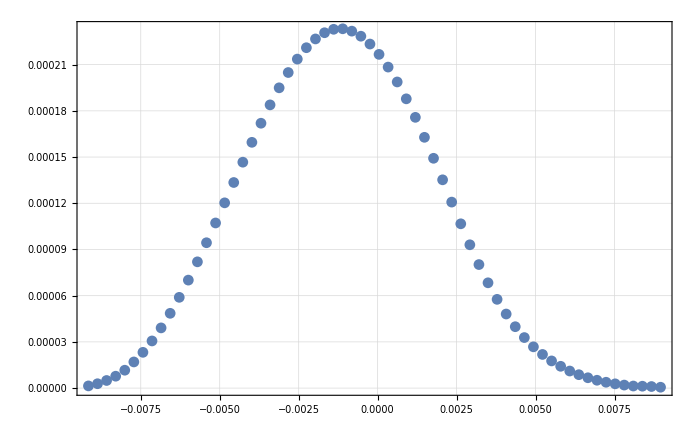

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma90005umdetShift[[All,2]]}],PlotRange->All]
```

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
detShiftList={#/Total[#]&@da0Spectruma90005umdetShift[[All,2]],#/Total[#]&@da0Spectruma10205umdetShift[[All,2]],#/Total[#]&@da0Spectruma10105umdetShift[[All,2]],#/Total[#]&@da0Spectruma10055umdetShift[[All,2]]};
```

```mathematica
bList2={-0.9,-0.1020,-0.101,-0.1005}
```

{-0.9,-0.102,-0.101,-0.1005}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

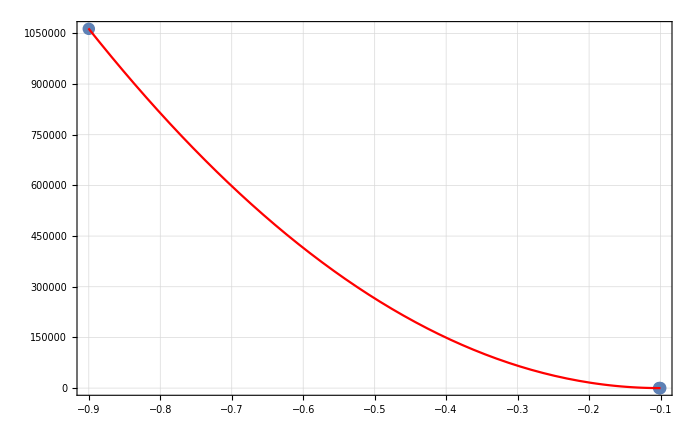
{{{0.00106346,5.67704×10^-9,2.31812×10^-9,1.84449×10^-9},{1.11203×10^-7,2.01088×10^-10,1.36276×10^-10,1.45836×10^-10}},a0 =  | -0.100479
FittedModel[1.84449×10^-9+0.00166364 (0.100479+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.100479 | 0.0000498618 | -2015.15 | 0.000315917
scale | 0.00166364 | 2.7089×10^-7 | 6141.37 | 0.000103661
yoffset | 1.84449×10^-9 | 1.25288×10^-10 | 14.722 | 0.0431765 | 
 | DF | SS | MS
Model | 3 | 9.14556×10^7 | 3.04852×10^7
Error | 1 | 0.0326865 | 0.0326865
Uncorrected Total | 4 | 9.14556×10^7 | 
Corrected Total | 3 | 9.1454×10^7 |  | ,-Graphics-}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma02564Bin[[All,2]],detShiftList,bList2, 4]
```

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)
```

-0.04310.0005

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/10^-6
```

-8693.198.

```mathematica
.001*8693
```

8.693

```mathematica
protDetShiftList={{-1*10^-6,-0.10592422242131855},{-50*10^-9,-0.10503419055752933},{50*10^-9,-0.10495768469584163},{1*10^-6,-0.10408719799304411},{2*10^-6,-0.1031657894775463},{10*10^-6,-0.09605444449437454}}
```

{{-1/1000000,-0.105924},{-1/20000000,-0.105034},{1/20000000,-0.104958},{1/1000000,-0.104087},{1/500000,-0.103166},{1/100000,-0.0960544}}

```mathematica
f=LinearModelFit[protDetShiftList,{1,x},x]
```

FittedModel[-0.104994+895.212 x]

```mathematica
f2=LinearModelFit[{{-1/1000000,-0.10592422242131855},{-1/20000000,-0.10503419055752933},{1/20000000,-0.10495768469584163},{1/1000000,-0.10408719799304411},{1/500000,-0.1031657894775463}},{1,x},x]
```

FittedModel[-0.105001+917.753 x]

```mathematica
f2[10*10^-6]
```

-0.0958234

```mathematica
Show[ListPlot[protDetShiftList,PlotRange->All],Plot[f[x],{x,-1*10^-6,10*10^-6},PlotStyle->Red],Plot[f2[x],{x,-1*10^-6,10*10^-6},PlotStyle->Blue]]
```

-Graphics-

## 10um Shift Plus

### a=-1050

```mathematica
da0SubFileNamesa1050detShift10um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-1050/TransferResult_08-09-20_SC_diffProf_C_ddetShift10um_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-1050/TransferResult_08-09-20_SC_diffProf_C_ddetShift10um_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-1050/TransferResult_08-09-20_SC_diffProf_C_ddetShift10um_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-1050/TransferResult_08-09-20_SC_diffProf_D_ddetShift10um_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-1050/TransferResult_08-09-20_SC_diffProf_D_ddetShift10um_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-1050/TransferResult_08-09-20_SC_diffProf_D_ddetShift10um_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-1050/TransferResult_08-09-20_SC_diffProf_D_ddetShift10um_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-1050/TransferResult_08-09-20_SC_diffProf_D_ddetShift10um_a-1050_57-64.txt}

```mathematica
da0Spectruma1050detShift10um=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050detShift10um,1];
```

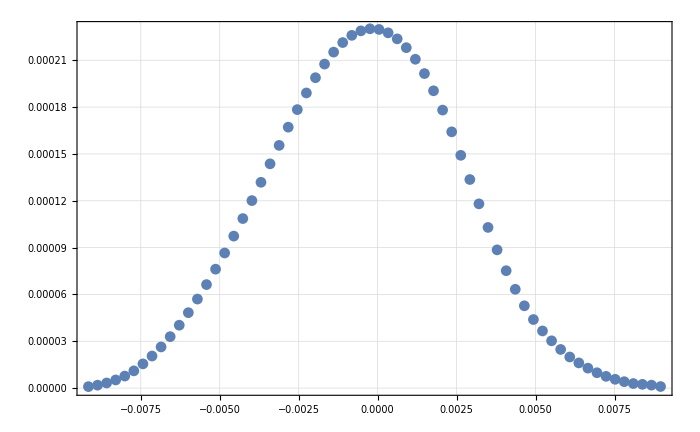

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1050detShift10um[[All,2]]}],PlotRange->All]
```

### a=-1020

```mathematica
da0SubFileNamesa1020detShift10um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-1020/"];
```

```mathematica
da0Spectruma1020detShift10um=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1020detShift10um,1];
```

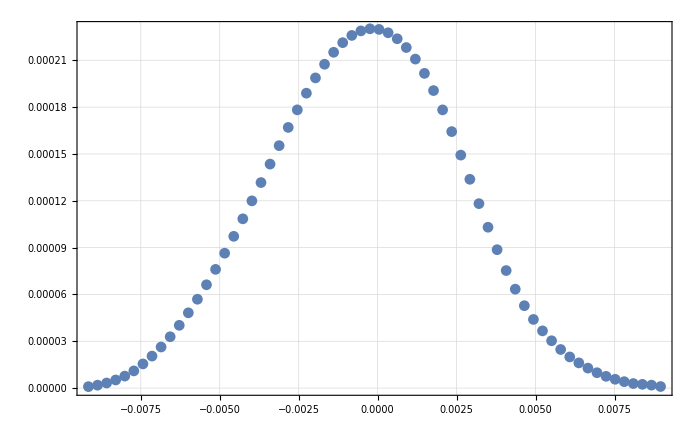

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1020detShift10um[[All,2]]}],PlotRange->All]
```

### a=-1005

```mathematica
da0SubFileNamesa1005detShift10um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-1005/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-1005/TransferResult_08-09-20_SC_diffProf_C_ddetShift10um_a-1005_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-1005/TransferResult_08-09-20_SC_diffProf_C_ddetShift10um_a-1005_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-1005/TransferResult_08-09-20_SC_diffProf_C_ddetShift10um_a-1005_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-1005/TransferResult_08-09-20_SC_diffProf_D_ddetShift10um_a-1005_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-1005/TransferResult_08-09-20_SC_diffProf_D_ddetShift10um_a-1005_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-1005/TransferResult_08-09-20_SC_diffProf_D_ddetShift10um_a-1005_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-1005/TransferResult_08-09-20_SC_diffProf_G_ddetShift10um_a-1005_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-1005/TransferResult_08-09-20_SC_diffProf_G_ddetShift10um_a-1005_57-64.txt}

```mathematica
da0Spectruma1005detShift10um=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1005detShift10um,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1025detShift10um[[All,2]]}],PlotRange->All]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {{-0.00915625,-0.00886875,-0.00858125,-0.00829375,-0.00800625,-0.00771875,-0.00743125,-0.00714375,-0.00685625,-0.00656875,-0.00628125,-0.00599375,-0.00570625,-0.00541875,-0.00513125,-0.00484375,-0.00455625,-0.00426875,-0.00398125,-0.00369375,-0.00340625,«10»,-0.00024375,0.00004375,0.00033125,0.00061875,0.00090625,0.00119375,0.00148125,0.00176875,0.00205625,0.00234375,0.00263125,0.00291875,0.00320625,0.00349375,0.00378125,0.00406875,0.00435625,0.00464375,0.00493125,«14»},Symbol[]} cannot be transposed.

ListPlot::lpn: Transpose[{{-0.00915625,-0.00886875,-0.00858125,-0.00829375,-0.00800625,-0.00771875,-0.00743125,-0.00714375,-0.00685625,-0.00656875,-0.00628125,-0.00599375,-0.00570625,-0.00541875,-0.00513125,-0.00484375,-0.00455625,-0.00426875,-0.00398125,-0.00369375,«11»,-0.00024375,0.00004375,0.00033125,0.00061875,0.00090625,0.00119375,0.00148125,0.00176875,0.00205625,0.00234375,0.00263125,0.00291875,0.00320625,0.00349375,0.00378125,0.00406875,0.00435625,0.00464375,0.00493125,«14»},Symbol[]}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{{-0.00915625,-0.00886875,-0.00858125,-0.00829375,-0.00800625,-0.00771875,-0.00743125,-0.00714375,-0.00685625,-0.00656875,-0.00628125,-0.00599375,-0.00570625,-0.00541875,-0.00513125,-0.00484375,-0.00455625,-0.00426875,-0.00398125,-0.00369375,-0.00340625,-0.00311875,-0.00283125,-0.00254375,-0.00225625,-0.00196875,-0.00168125,-0.00139375,-0.00110625,-0.00081875,-0.00053125,-0.00024375,0.00004375,0.00033125,0.00061875,0.00090625,0.00119375,0.00148125,0.00176875,0.00205625,0.00234375,0.00263125,0.00291875,0.00320625,0.00349375,0.00378125,0.00406875,0.00435625,0.00464375,0.00493125,0.00521875,0.00550625,0.00579375,0.00608125,0.00636875,0.00665625,0.00694375,0.00723125,0.00751875,0.00780625,0.00809375,0.00838125,0.00866875,0.00895625},Symbol[]}],PlotRange→All]

### a=-1100

```mathematica
da0SubFileNamesa1100detShift10um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-1100/"];
```

```mathematica
da0Spectruma1100detShift10um=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1100detShift10um,1];
```

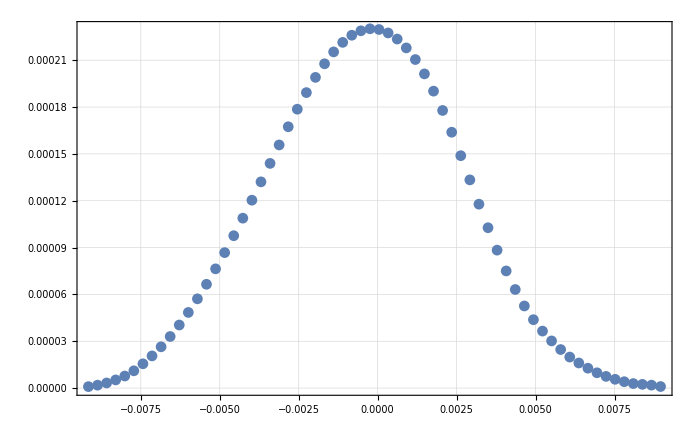

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1100detShift10um[[All,2]]}],PlotRange->All]
```

### a=-1200

```mathematica
da0SubFileNamesa1200detShift10um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-1200/"];
```

```mathematica
da0Spectruma1200detShift10um=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1200detShift10um,1];
```

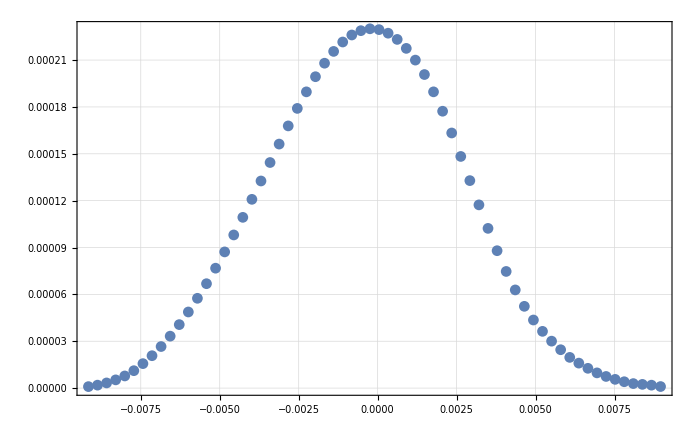

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1200detShift10um[[All,2]]}],PlotRange->All]
```

### a=-1025

```mathematica
da0SubFileNamesa9000detShift10um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-9000/"];
```

```mathematica
da0Spectruma9000detShift10um=Flatten[Import[#,"Table"]&/@da0SubFileNamesa9000detShift10um,1];
```

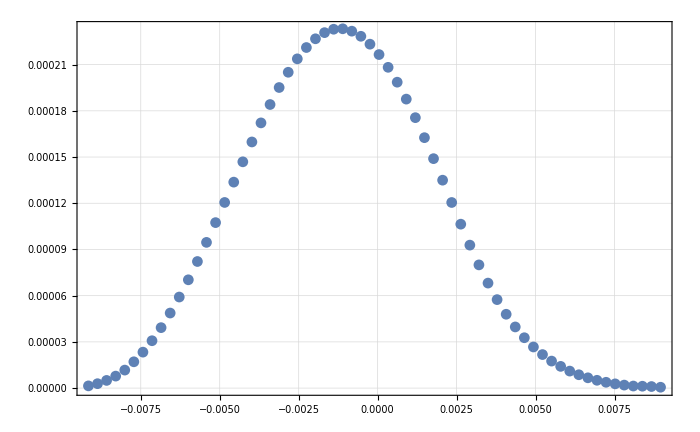

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma9000detShift10um[[All,2]]}],PlotRange->All]
```

### a=-800

```mathematica
da0SubFileNamesa800detShift10um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-800/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-800/TransferResult_08-09-20_SC_diffProf_C_ddetShift10um_a-800_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-800/TransferResult_08-09-20_SC_diffProf_C_ddetShift10um_a-800_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-800/TransferResult_08-09-20_SC_diffProf_C_ddetShift10um_a-800_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-800/TransferResult_08-09-20_SC_diffProf_C_ddetShift10um_a-800_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-800/TransferResult_08-09-20_SC_diffProf_C_ddetShift10um_a-800_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-800/TransferResult_08-09-20_SC_diffProf_C_ddetShift10um_a-800_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-800/TransferResult_08-09-20_SC_diffProf_C_ddetShift10um_a-800_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-800/TransferResult_08-09-20_SC_diffProf_C_ddetShift10um_a-800_57-64.txt}

```mathematica
da0Spectruma800detShift10um=Flatten[Import[#,"Table"]&/@da0SubFileNamesa800detShift10um,1];
```

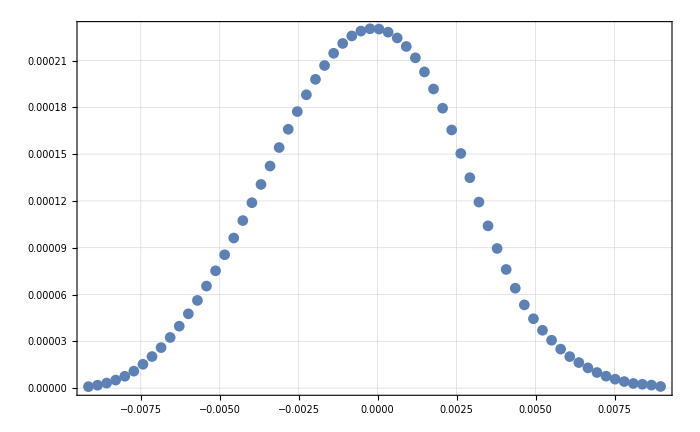

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma800detShift10um[[All,2]]}],PlotRange->All]
```

### a=-900

```mathematica
da0SubFileNamesa900detShift10um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-900/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-900/TransferResult_08-09-20_SC_diffProf_D_ddetShift10um_a-900_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-900/TransferResult_08-09-20_SC_diffProf_D_ddetShift10um_a-900_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-900/TransferResult_08-09-20_SC_diffProf_D_ddetShift10um_a-900_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-900/TransferResult_08-09-20_SC_diffProf_D_ddetShift10um_a-900_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-900/TransferResult_08-09-20_SC_diffProf_D_ddetShift10um_a-900_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-900/TransferResult_08-09-20_SC_diffProf_D_ddetShift10um_a-900_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-900/TransferResult_08-09-20_SC_diffProf_D_ddetShift10um_a-900_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-900/TransferResult_08-09-20_SC_diffProf_D_ddetShift10um_a-900_57-64.txt}

```mathematica
da0Spectruma900detShift10um=Flatten[Import[#,"Table"]&/@da0SubFileNamesa900detShift10um,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma800detShift10um[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1025

```mathematica
da0SubFileNamesa1025detShift10um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-1025/"];
```

```mathematica
da0Spectruma1025detShift10um=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1025detShift10um,1];
```

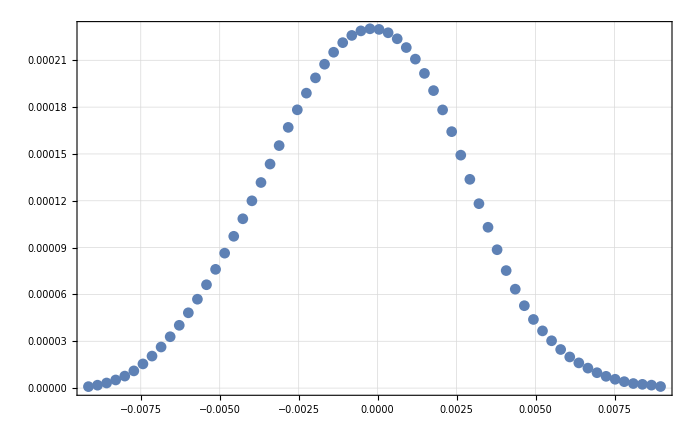

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1025detShift10um[[All,2]]}],PlotRange->All]
```

### a=-1010

```mathematica
da0SubFileNamesa1010detShift10um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift10um/a-1010/"];
```

```mathematica
da0Spectruma1010detShift10um=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1010detShift10um,1];
```

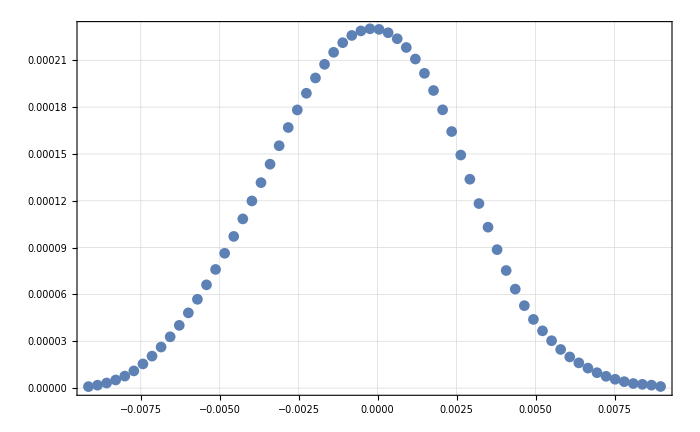

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1010detShift10um[[All,2]]}],PlotRange->All]
```

```mathematica
detShift2List={#/Total[#]&@da0Spectruma800detShift10um[[All,2]],#/Total[#]&@da0Spectruma900detShift10um[[All,2]],#/Total[#]&@da0Spectruma1005detShift10um[[All,2]],#/Total[#]&@da0Spectruma1010detShift10um[[All,2]],#/Total[#]&@da0Spectruma1020detShift10um[[All,2]],#/Total[#]&@da0Spectruma1025detShift10um[[All,2]],#/Total[#]&@da0Spectruma1050detShift10um[[All,2]]};
```

```mathematica
bList={-0.08,-0.09,-0.1005,-0.1010,-.1020,-.1025,-0.1050}
```

{-0.08,-0.09,-0.1005,-0.101,-0.102,-0.1025,-0.105}

```mathematica
Sort[bList]
```

{-0.105,-0.1025,-0.102,-0.101,-0.1005,-0.09,-0.08}

```mathematica
Sort[{-0.104,-0.1045,-0.105}]
```

{-0.105,-0.1045,-0.104}

```mathematica
?TransferToRefParableFitForProtons0Del
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

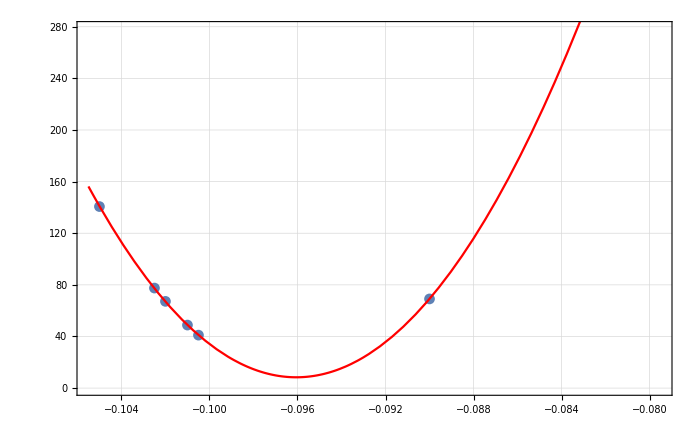
{{{4.35918×10^-7,6.90915×10^-8,4.10376×10^-8,4.88376×10^-8,6.71978×10^-8,7.75107×10^-8,1.4067×10^-7},{2.36848×10^-9,1.00286×10^-9,5.64694×10^-10,6.26481×10^-10,7.55411×10^-10,8.2055×10^-10,1.15042×10^-9}},a0 =  | -0.0960544
FittedModel[8.37835×10^-9+0.0016576 (0.0960544+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.0960544 | 0.0000231287 | -4153.04 | 2.0169×10^-14
scale | 0.0016576 | 0.000010363 | 159.955 | 9.16327×10^-9
yoffset | 8.37835×10^-9 | 6.566×10^-10 | 12.7602 | 0.000217344 | 
 | DF | SS | MS
Model | 3 | 81766.4 | 27255.5
Error | 4 | 0.356208 | 0.0890519
Uncorrected Total | 7 | 81766.7 | 
Corrected Total | 6 | 31472.4 |  | ,-Graphics-}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma02564Bin[[All,2]],detShift2List,bList,4]
```

```mathematica
?pmom
```

```mathematica
?dwdt
```

```mathematica
?pmomNorm
```

## 2um Shift Plus

### a=-1040

```mathematica
da0SubFileNamesa1040detShift2um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift2um/a-1040/"];
```

```mathematica
da0Spectruma1040detShift2um=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040detShift2um,1];
```

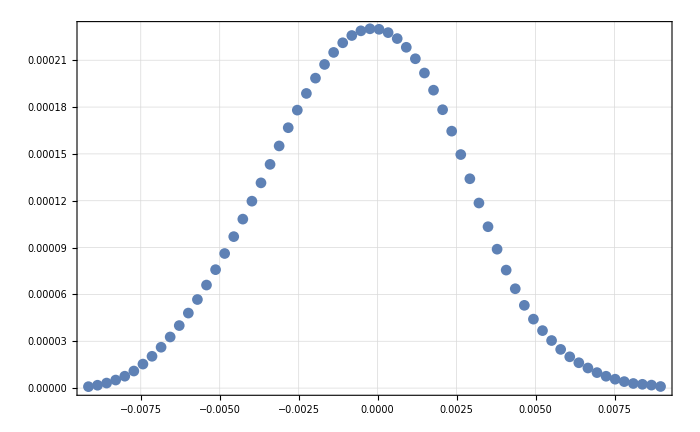

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1040detShift2um[[All,2]]}],PlotRange->All]
```

### a=-1050

```mathematica
da0SubFileNamesa1050detShift2um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift2um/a-1050/"];
```

```mathematica
a=-0.102;
```

```mathematica
da0Spectruma1050detShift2um=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050detShift2um,1];
```

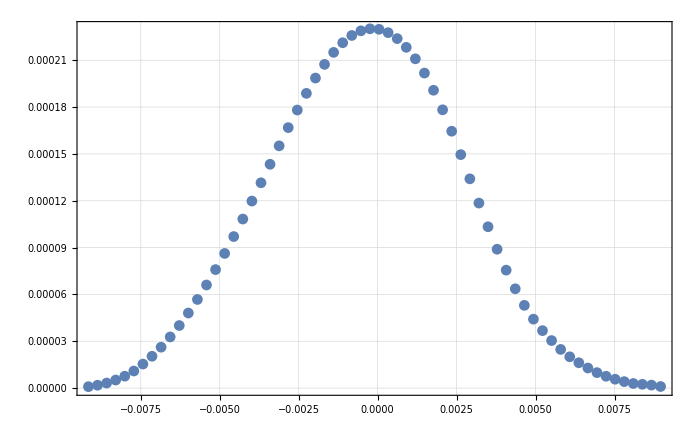

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1050detShift2um[[All,2]]}],PlotRange->All]
```

### a=-1025

```mathematica
da0SubFileNamesa1025detShift2um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift2um/a-1025/"];
```

```mathematica
a=-0.102;
```

```mathematica
da0Spectruma1025detShift2um=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1025detShift2um,1];
```

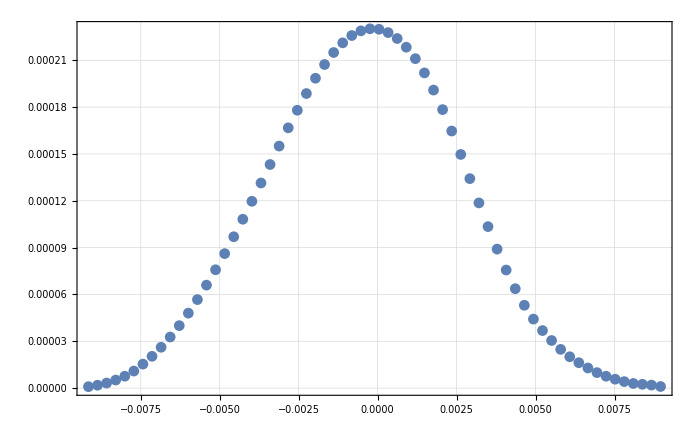

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1025detShift2um[[All,2]]}],PlotRange->All]
```

### a=-1035

```mathematica
da0SubFileNamesa1035detShift2um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift2um/a-1035/"];
```

```mathematica
a=-0.102;
```

```mathematica
da0Spectruma1035detShift2um=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1035detShift2um,1];
```

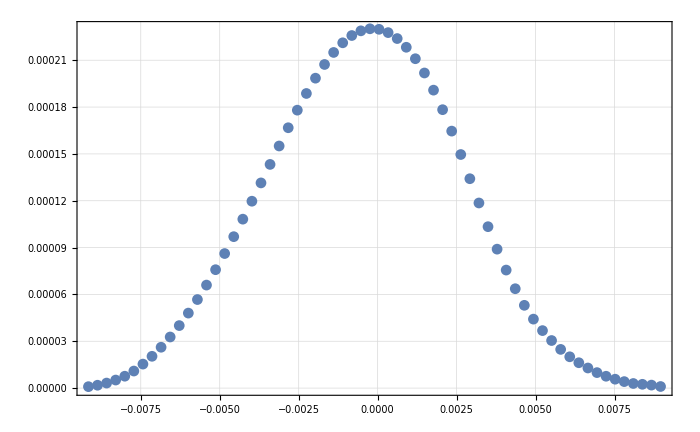

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1035detShift2um[[All,2]]}],PlotRange->All]
```

### a=-1055

```mathematica
da0SubFileNamesa1055detShift2um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift2um/a-1055/"];
```

```mathematica
a=-0.102;
```

```mathematica
da0Spectruma1055detShift2um=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055detShift2um,1];
```

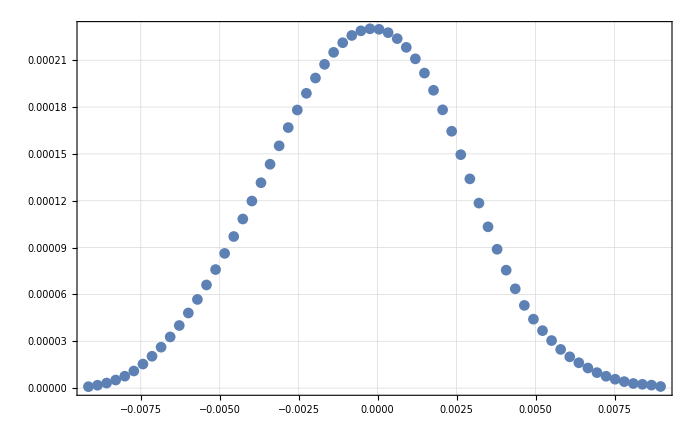

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1055detShift2um[[All,2]]}],PlotRange->All]
```

### a=-1060

```mathematica
da0SubFileNamesa1060detShift2um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift2um/a-1060/"];
```

```mathematica
a=-0.102;
```

```mathematica
da0Spectruma1060detShift2um=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060detShift2um,1];
```

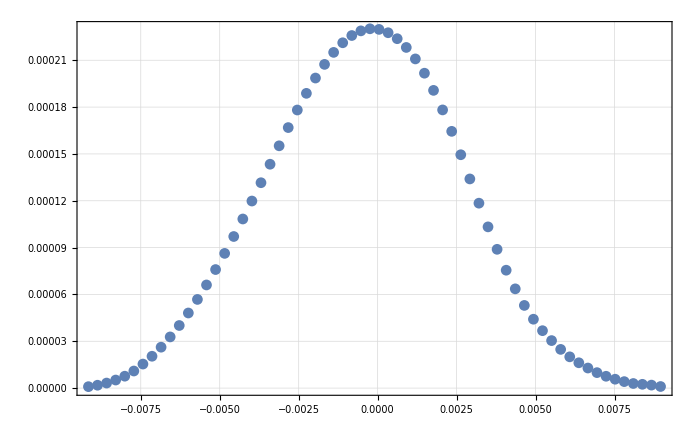

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1060detShift2um[[All,2]]}],PlotRange->All]
```

```mathematica
detShiftList={#/Total[#]&@da0Spectruma1025detShift2um[[All,2]],#/Total[#]&@da0Spectruma1035detShift2um[[All,2]],#/Total[#]&@da0Spectruma1040detShift2um[[All,2]],#/Total[#]&@da0Spectruma1050detShift2um[[All,2]],#/Total[#]&@da0Spectruma1055detShift2um[[All,2]],#/Total[#]&@da0Spectruma1060detShift2um[[All,2]]};
```

```mathematica
bList={-0.1025,-0.1035,-0.104,-.1050,-.1055,-0.1060}
```

{-0.1025,-0.1035,-0.104,-0.105,-0.1055,-0.106}

```mathematica
dchi210402um
```

dchi210402um

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

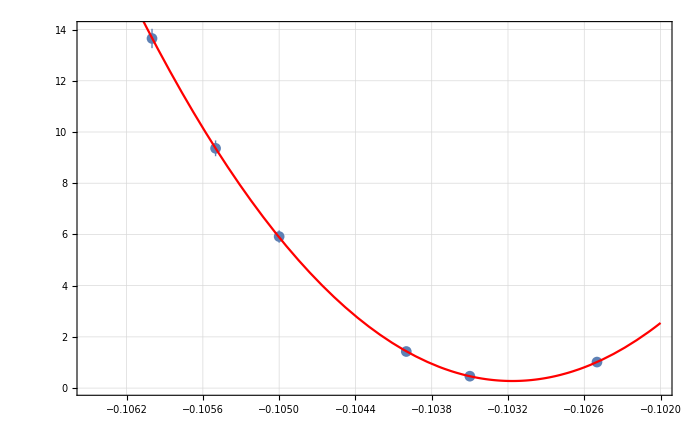
{{{1.01625×10^-9,4.64517×10^-10,1.42871×10^-9,5.91737×10^-9,9.36241×10^-9,1.36521×10^-8},{1.26524×10^-10,5.64754×10^-11,1.0591×10^-10,2.39879×10^-10,3.07935×10^-10,3.77999×10^-10}},a0 =  | -0.103166
FittedModel[2.76939×10^-10+0.00166767 (0.103166+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.103166 | 0.0000324998 | -3174.35 | 6.89455×10^-11
scale | 0.00166767 | 0.0000534615 | 31.1938 | 0.0000723872
yoffset | 2.76939×10^-10 | 5.38922×10^-11 | 5.13876 | 0.0142772 | 
 | DF | SS | MS
Model | 3 | 3151.44 | 1050.48
Error | 3 | 0.0259104 | 0.00863681
Uncorrected Total | 6 | 3151.47 | 
Corrected Total | 5 | 2348.66 |  | ,-Graphics-}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma02564Bin[[All,2]],detShiftList,bList, 4]
```

```mathematica
(-0.1031657894775463+0.105)/-0.105/(2*10^-6)
```

-8734.34

```mathematica
873.335821208068*10*10^-6
```

0.00873336

```mathematica
(-0.1031657894775463+0.105)/-0.105/(10*10^-6)
```

-1746.87

## Plus Shift2

### a=-1050

```mathematica
da0SubFileNamesa1050detShift2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift2/a-1050/"];
```

```mathematica
da0Spectruma1050detShift2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050detShift2,1];
```

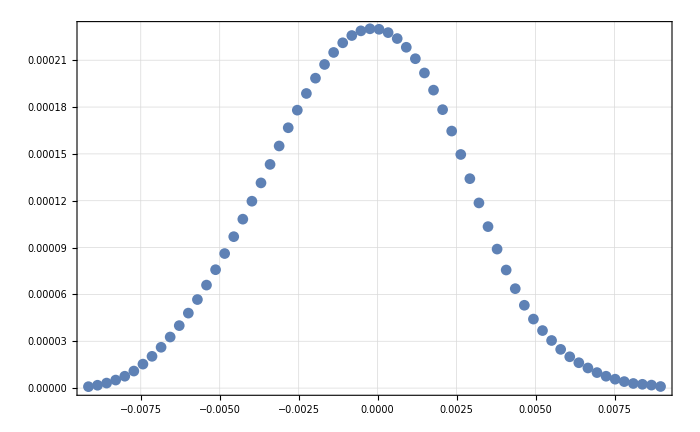

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1050detShift2[[All,2]]}],PlotRange->All]
```

### a=-1051

```mathematica
da0SubFileNamesa1051detShift2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift2/a-1051/"];
```

```mathematica
da0Spectruma1051detShift2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1051detShift2,1];
```

```mathematica
da0Spectruma1051detShift2//Length
```

64

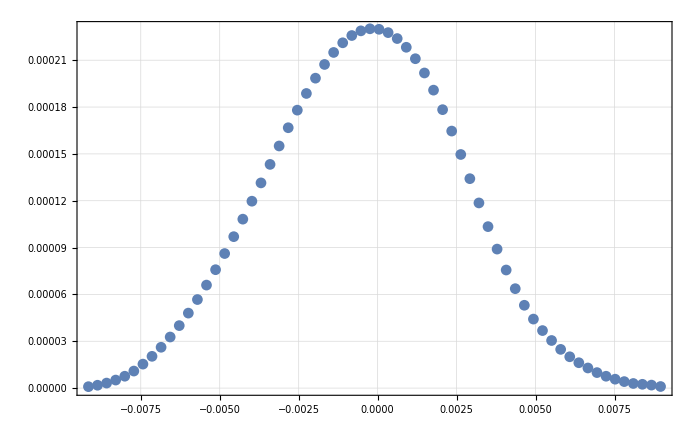

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1051detShift2[[All,2]]}],PlotRange->All]
```

### a=-1040

```mathematica
da0SubFileNamesa1040detShift2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift2/a-1040/"];
```

```mathematica
da0Spectruma1040detShift2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040detShift2,1];
```

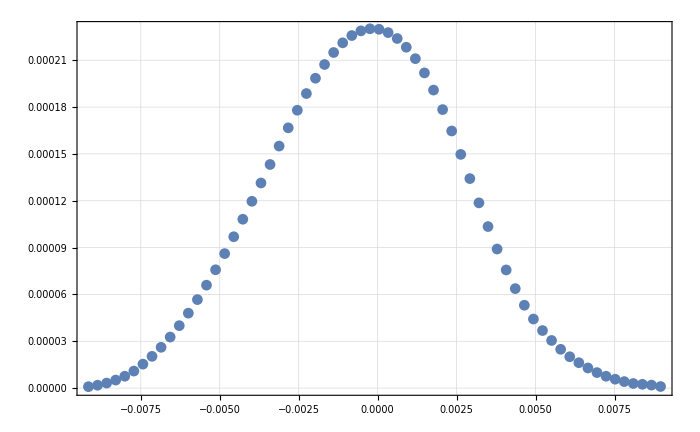

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1040detShift2[[All,2]]}],PlotRange->All]
```

### a=-1045

```mathematica
da0SubFileNamesa1045detShift2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift2/a-1045/"];
```

```mathematica
da0Spectruma1045detShift2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045detShift2,1];
```

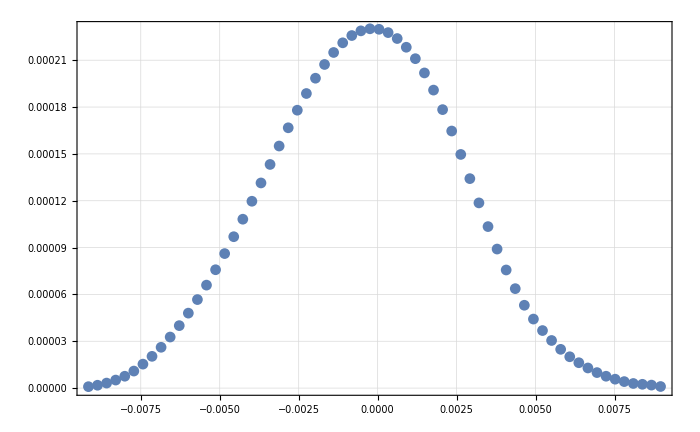

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1045detShift2[[All,2]]}],PlotRange->All]
```

### a=-1055

```mathematica
da0SubFileNamesa1055detShift2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift2/a-1055/"];
```

```mathematica
da0Spectruma1055detShift2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055detShift2,1];
```

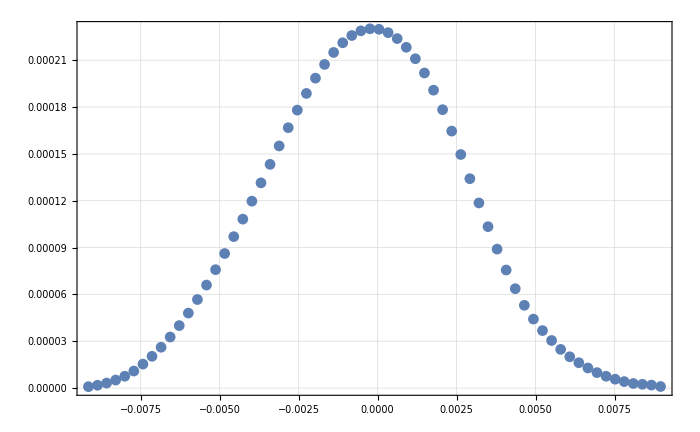

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1055detShift2[[All,2]]}],PlotRange->All]
```

### a=-1060

```mathematica
da0SubFileNamesa1060detShift2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShift2/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060detShift2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060detShift2,1];
```

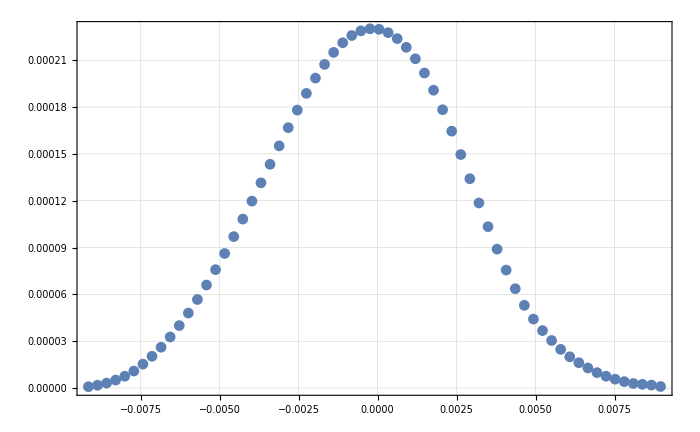

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1060detShift2[[All,2]]}],PlotRange->All]
```

```mathematica
#/Total[#]&@da0Spectruma1040detShift2[[All,2]]==da0Spectruma1040detShift2[[All,2]]/Total[da0Spectruma1040detShift2[[All,2]]]
```

True

```mathematica
da0Spectruma1040detShift2[[All,2]]/Total[da0Spectruma1040detShift2[[All,2]]]
```

{0.000148509,0.000296794,0.000520575,0.000833126,0.00123161,0.00176821,0.00248862,0.0032984,0.00423811,0.00530205,0.00648575,0.00778396,0.00919144,0.0106928,0.0122903,0.0139689,0.0157202,0.0175386,0.0194034,0.0213044,0.0232263,0.0251396,0.0270346,0.0288615,0.0305947,0.0321848,0.0336106,0.0348583,0.0358626,0.0366195,0.0371058,0.0373216,0.0372704,0.0369257,0.0363114,0.0354063,0.0342189,0.0327388,0.0309566,0.0289295,0.0267059,0.0242744,0.0217608,0.0192406,0.016779,0.0144445,0.0122714,0.0103319,0.00860708,0.00717179,0.00597819,0.00494693,0.00402734,0.00325568,0.00263625,0.00209093,0.00161122,0.00123249,0.000925273,0.00067488,0.000479163,0.000395283,0.000311282,0.000164563}

```mathematica
da0Spectruma1050detShift2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1050detShift2[[All,2]]}]];
da0Spectruma1040detShift2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1040detShift2[[All,2]]}]];
da0Spectruma1045detShift2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1045detShift2[[All,2]]}]];
da0Spectruma1055detShift2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1055detShift2[[All,2]]}]];
da0Spectruma1060detShift2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1060detShift2[[All,2]]}]];
```

InterpolatingFunction::dmval: Input value {-0.00929962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

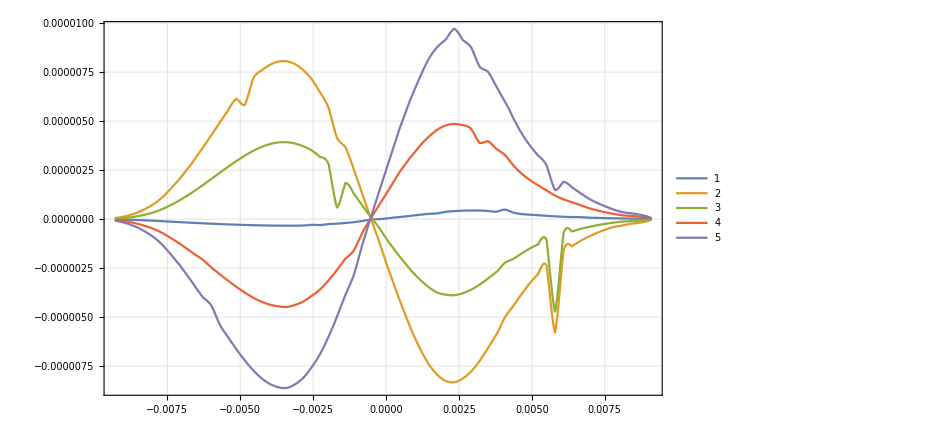

```mathematica
Plot[{
d0Spectrum2564BinInter[x]-da0Spectruma1050detShift2Inter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1040detShift2Inter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1045detShift2Inter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1055detShift2Inter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1060detShift2Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
detShift2List={#/Total[#]&@da0Spectruma1040detShift2[[All,2]],#/Total[#]&@da0Spectruma1045detShift2[[All,2]],#/Total[#]&@da0Spectruma1050detShift2[[All,2]],#/Total[#]&@da0Spectruma1051detShift2[[All,2]],#/Total[#]&@da0Spectruma1055detShift2[[All,2]],#/Total[#]&@da0Spectruma1060detShift2[[All,2]]};
```

```mathematica
bList={-0.104,-.1045,-.1050,-0.1051,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1051,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

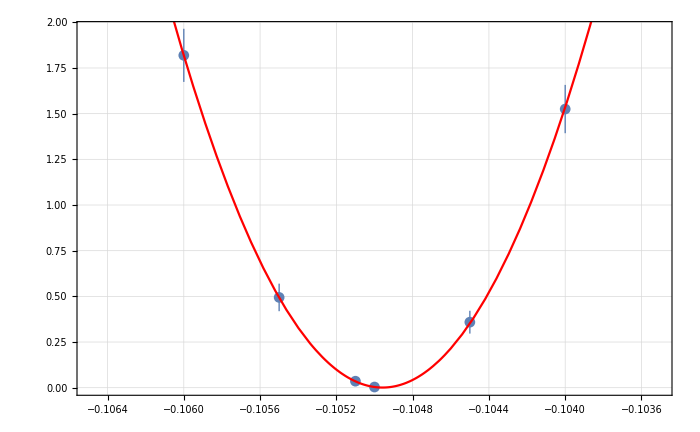
{{{1.52523×10^-9,3.58672×10^-10,3.71906×10^-12,3.55996×10^-11,4.94171×10^-10,1.81924×10^-9},{1.32204×10^-10,6.24258×10^-11,5.86906×10^-12,1.96538×10^-11,7.5394×10^-11,1.45333×10^-10}},a0 =  | -0.104958
FittedModel[8.53387×10^-13+0.0016731 (0.104958+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104958 | 0.0000194033 | -5409.28 | 1.39332×10^-11
scale | 0.0016731 | 0.0000881911 | 18.9714 | 0.000319778
yoffset | 8.53387×10^-13 | 6.46861×10^-12 | 0.131928 | 0.903393 | 
 | DF | SS | MS
Model | 3 | 369.427 | 123.142
Error | 3 | 0.0224146 | 0.00747154
Uncorrected Total | 6 | 369.449 | 
Corrected Total | 5 | 359.956 |  | ,-Graphics-}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma02564Bin[[All,2]],detShift2List,bList, 4]
```

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)
```

-0.000400.00018

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/10^-6
```

-403.185.

## MinusShift2

### a=-1050

```mathematica
da0SubFileNamesa1050detShiftMin2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShiftMin2/a-1050/"];
```

```mathematica
da0Spectruma1050detShiftMin2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050detShiftMin2,1];
```

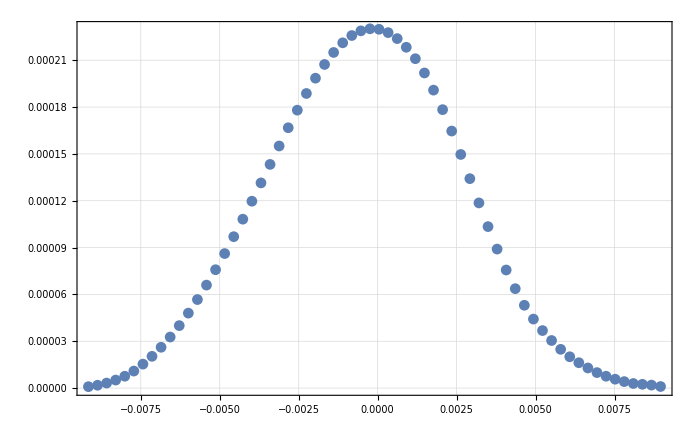

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1050detShiftMin2[[All,2]]}],PlotRange->All]
```

### a=-1051

```mathematica
da0SubFileNamesa1051detShiftMin2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShiftMin2/a-1051/"];
```

```mathematica
da0Spectruma1051detShiftMin2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1051detShiftMin2,1];
```

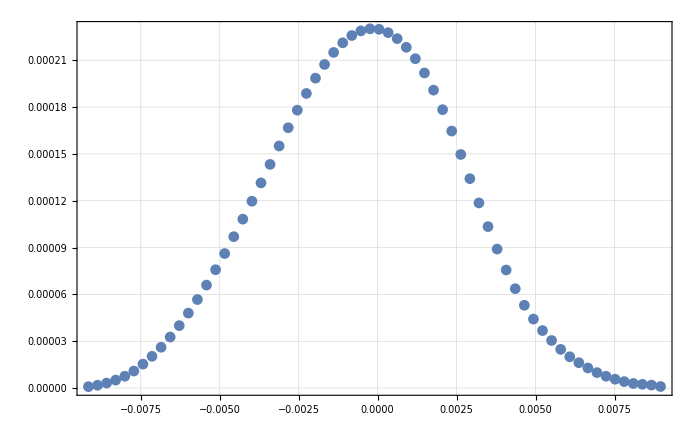

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1051detShiftMin2[[All,2]]}],PlotRange->All]
```

### a=-1040

```mathematica
da0SubFileNamesa1040detShiftMin2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShiftMin2/a-1040/"];
```

```mathematica
da0Spectruma1040detShiftMin2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040detShiftMin2,1];
```

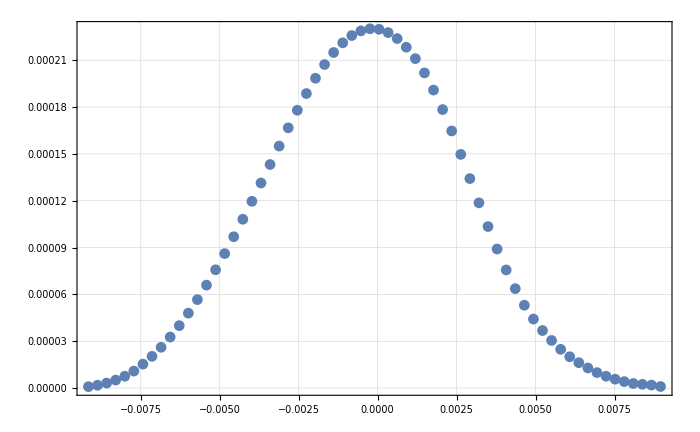

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1040detShiftMin2[[All,2]]}],PlotRange->All]
```

### a=-1045

```mathematica
da0SubFileNamesa1045detShiftMin2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShiftMin2/a-1045/"];
```

```mathematica
da0Spectruma1045detShiftMin2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045detShiftMin2,1];
```

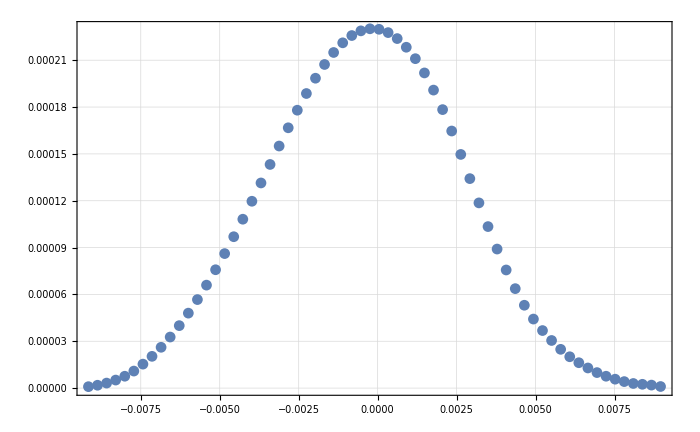

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1045detShiftMin2[[All,2]]}],PlotRange->All]
```

### a=-1055

```mathematica
da0SubFileNamesa1055detShiftMin2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShiftMin2/a-1055/"];
```

```mathematica
da0Spectruma1055detShiftMin2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055detShiftMin2,1];
```

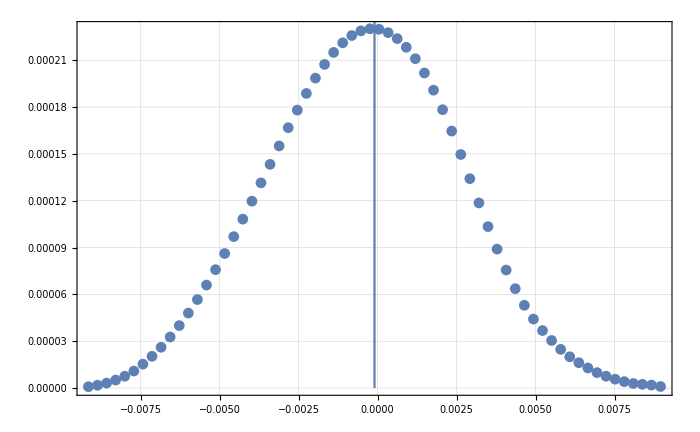

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1055detShiftMin2[[All,2]]}],PlotRange->All],ListLinePlot[{{-0.1/1000,0},{-0.1/1000,0.0003}}]]
```

```mathematica
.
```

### a=-1060

```mathematica
da0SubFileNamesa1060detShiftMin2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShiftMin2/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060detShiftMin2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060detShiftMin2,1];
```

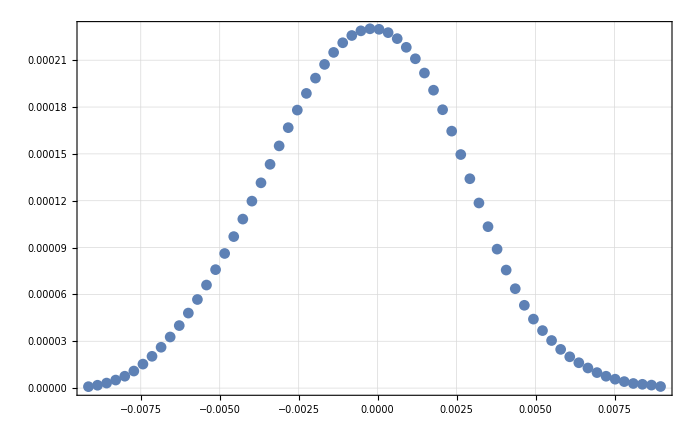

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1060detShiftMin2[[All,2]]}],PlotRange->All]
```

```mathematica
da0Spectruma1050detShiftMin2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1050detShiftMin2[[All,2]]}]];
da0Spectruma1040detShiftMin2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1040detShiftMin2[[All,2]]}]];
da0Spectruma1045detShiftMin2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1045detShiftMin2[[All,2]]}]];
da0Spectruma1055detShiftMin2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1055detShiftMin2[[All,2]]}]];
da0Spectruma1060detShiftMin2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1060detShiftMin2[[All,2]]}]];
```

InterpolatingFunction::dmval: Input value {-0.00929962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

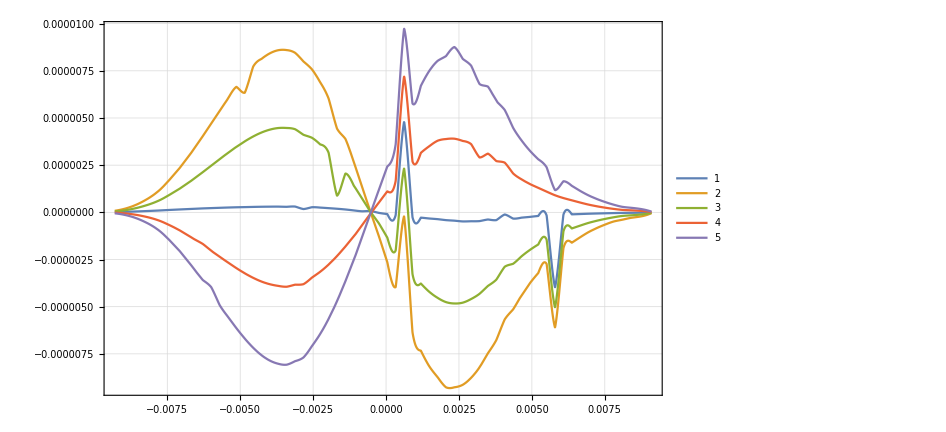

```mathematica
Plot[{
d0Spectrum2564BinInter[x]-da0Spectruma1050detShiftMin2Inter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1040detShiftMin2Inter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1045detShiftMin2Inter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1055detShiftMin2Inter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1060detShiftMin2Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
detShiftMin2List={#/Total[#]&@da0Spectruma1040detShiftMin2[[All,2]],#/Total[#]&@da0Spectruma1045detShiftMin2[[All,2]],#/Total[#]&@da0Spectruma1051detShiftMin2[[All,2]],#/Total[#]&@da0Spectruma1055detShiftMin2[[All,2]],#/Total[#]&@da0Spectruma1060detShiftMin2[[All,2]]};
```

```mathematica
bList={-0.104,-.1045,-.1051,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.1051,-0.1055,-0.106}

```mathematica
(-0.10503419055752933+0.105)/0.105
```

-0.000325624

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

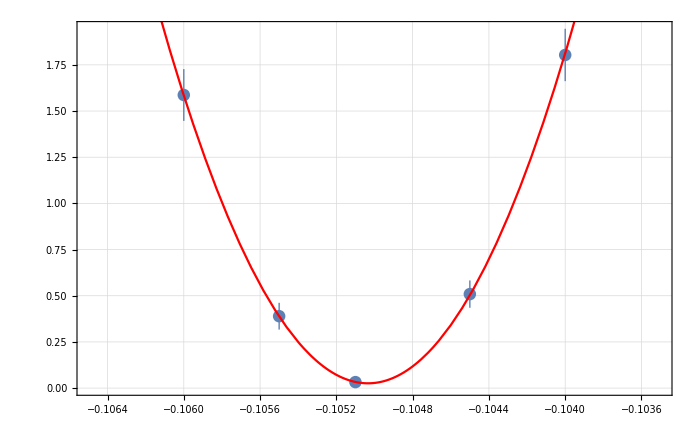
{{{1.80357×10^-9,5.08869×10^-10,3.24277×10^-11,3.89284×10^-10,1.58681×10^-9},{1.41732×10^-10,7.39792×10^-11,2.77994×10^-11,7.24441×10^-11,1.40189×10^-10}},a0 =  | -0.105034
FittedModel[2.59566×10^-11+0.00167047 (0.105034+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105034 | 0.0000217032 | -4839.58 | 4.26958×10^-8
scale | 0.00167047 | 0.000100439 | 16.6317 | 0.00359568
yoffset | 2.59566×10^-11 | 2.67619×10^-11 | 0.969908 | 0.434408 | 
 | DF | SS | MS
Model | 3 | 367.59 | 122.53
Error | 2 | 0.0124125 | 0.00620627
Uncorrected Total | 5 | 367.602 | 
Corrected Total | 4 | 286.078 |  | ,-Graphics-}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma02564Bin[[All,2]],detShiftMin2List,bList, 4]
```

## MinusShift

### a=-1050

```mathematica
da0SubFileNamesa1050detShiftMin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShiftMin/a-1050/"];
```

```mathematica
da0Spectruma1050detShiftMin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050detShiftMin,1];
```

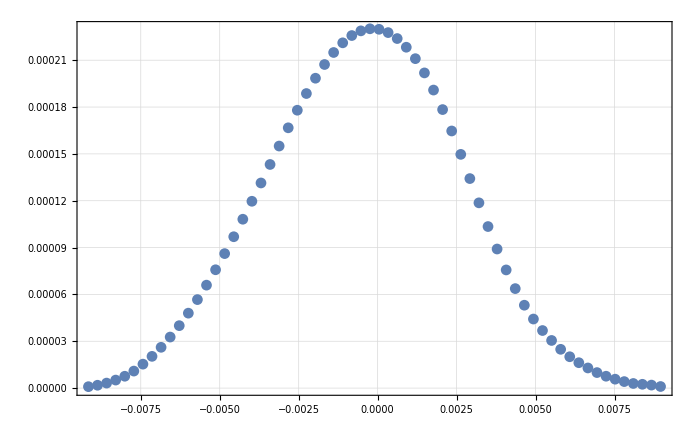

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1050detShiftMin[[All,2]]}],PlotRange->All]
```

### a=-1051

```mathematica
da0SubFileNamesa1051detShiftMin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShiftMin/a-1051/"];
```

```mathematica
da0Spectruma1051detShiftMin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1051detShiftMin,1];
```

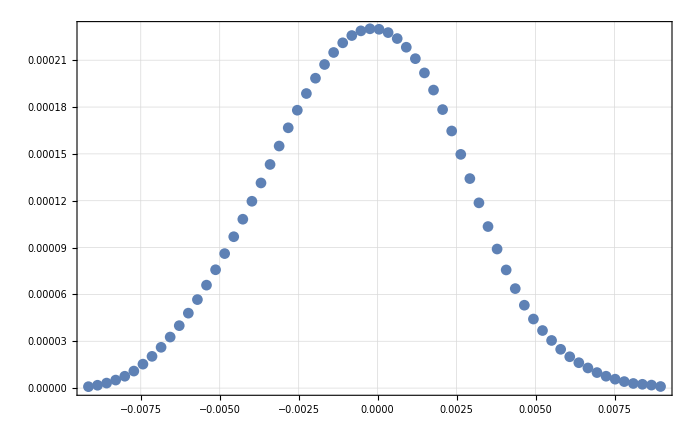

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1051detShiftMin[[All,2]]}],PlotRange->All]
```

### a=-1040

```mathematica
da0SubFileNamesa1040detShiftMin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShiftMin/a-1040/"];
```

```mathematica
da0Spectruma1040detShiftMin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040detShiftMin,1];
```

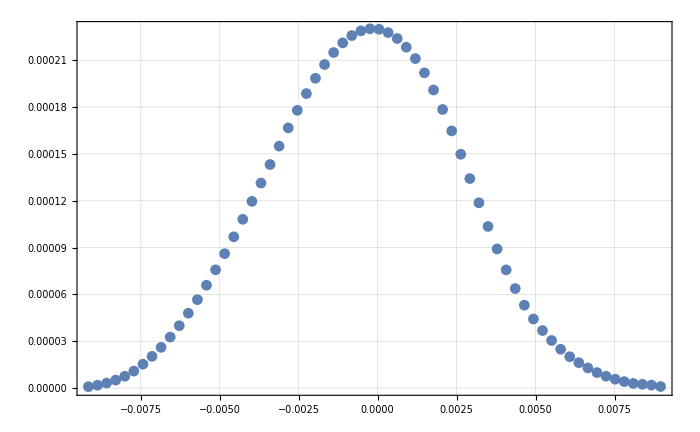

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1040detShiftMin[[All,2]]}],PlotRange->All]
```

### a=-1045

```mathematica
da0SubFileNamesa1045detShiftMin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShiftMin/a-1045/"];
```

```mathematica
da0Spectruma1045detShiftMin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045detShiftMin,1];
```

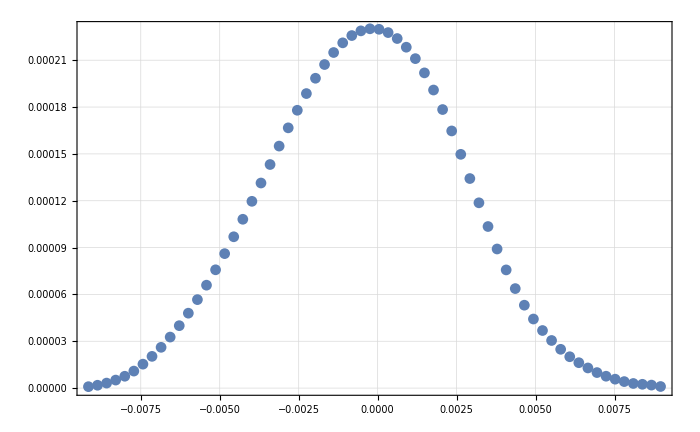

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1045detShiftMin[[All,2]]}],PlotRange->All]
```

### a=-1055

```mathematica
da0SubFileNamesa1055detShiftMin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShiftMin/a-1055/"];
```

```mathematica
da0Spectruma1055detShiftMin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055detShiftMin,1];
```

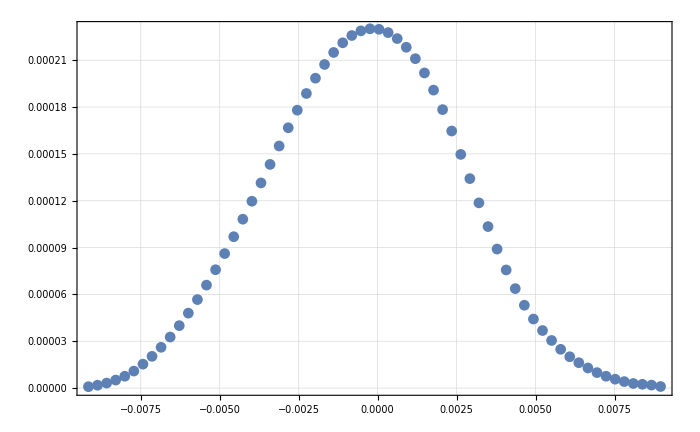

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1055detShiftMin[[All,2]]}],PlotRange->All]
```

### a=-1060

```mathematica
da0SubFileNamesa1060detShiftMin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_ddetShiftMin/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060detShiftMin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060detShiftMin,1];
```

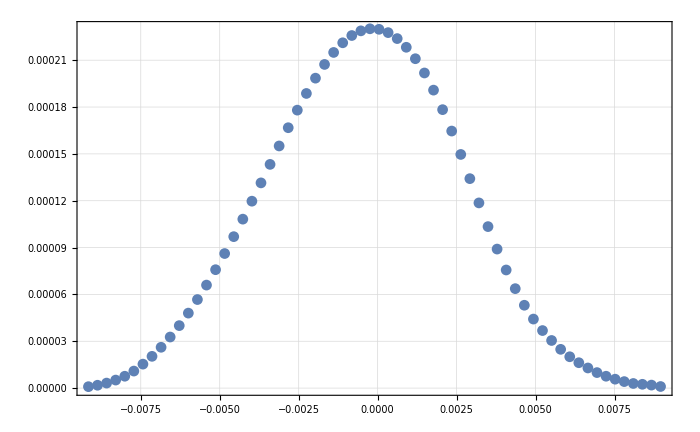

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1060detShiftMin[[All,2]]}],PlotRange->All]
```

```mathematica
#/Total[#]&@da0Spectruma1040detShiftMin[[All,2]]==da0Spectruma1040detShiftMin[[All,2]]/Total[da0Spectruma1040detShiftMin[[All,2]]]
```

True

```mathematica
da0Spectruma1040detShiftMin[[All,2]]/Total[da0Spectruma1040detShiftMin[[All,2]]]
```

{0.000148088,0.000296128,0.000519608,0.000831808,0.0012299,0.00176601,0.00248594,0.00329525,0.00423449,0.00529801,0.00648122,0.00777914,0.00918624,0.0106872,0.0122846,0.0139628,0.0157139,0.017532,0.0193969,0.0212977,0.0232195,0.0251329,0.0270283,0.028855,0.0305889,0.0321808,0.0336058,0.0348547,0.0358601,0.0366178,0.0371049,0.0373217,0.0372707,0.036928,0.0363116,0.0354106,0.0342243,0.0327452,0.0309647,0.0289377,0.0267148,0.0242855,0.0217635,0.0192501,0.0167871,0.014452,0.012279,0.0103385,0.00861283,0.00717668,0.0059824,0.00494728,0.00403022,0.00325819,0.00263844,0.00209283,0.00161277,0.00123376,0.000926309,0.000675703,0.00047976,0.000395817,0.000311712,0.000164838}

```mathematica
da0Spectruma1050detShiftMinInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1050detShiftMin[[All,2]]}]];
da0Spectruma1040detShiftMinInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1040detShiftMin[[All,2]]}]];
da0Spectruma1045detShiftMinInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1045detShiftMin[[All,2]]}]];
da0Spectruma1055detShiftMinInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1055detShiftMin[[All,2]]}]];
da0Spectruma1060detShiftMinInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1060detShiftMin[[All,2]]}]];
```

InterpolatingFunction::dmval: Input value {-0.00929962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

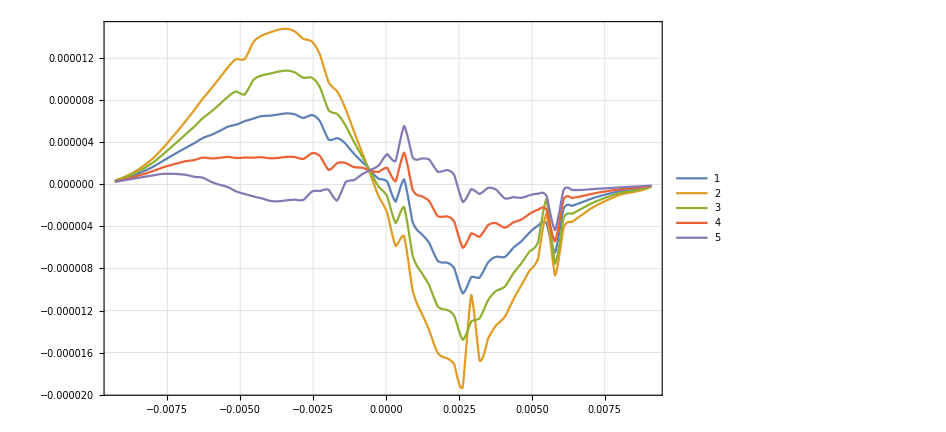

```mathematica
Plot[{
d0Spectrum2564BinInter[x]-da0Spectruma1050detShiftMinInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1040detShiftMinInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1045detShiftMinInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1055detShiftMinInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1060detShiftMinInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
detShiftMinList={#/Total[#]&@da0Spectruma1040detShiftMin[[All,2]],#/Total[#]&@da0Spectruma1045detShiftMin[[All,2]],#/Total[#]&@da0Spectruma1050detShiftMin[[All,2]],#/Total[#]&@da0Spectruma1055detShiftMin[[All,2]],#/Total[#]&@da0Spectruma1060detShiftMin[[All,2]]};
```

```mathematica
bList={-0.104,-.1045,-.1050,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

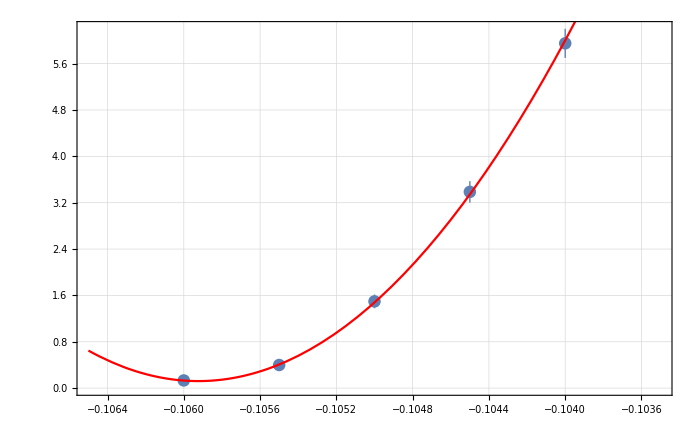
{{{5.95057×10^-9,3.38644×10^-9,1.49644×10^-9,3.9831×10^-10,1.32069×10^-10},{2.51042×10^-10,1.85544×10^-10,1.18465×10^-10,5.69372×10^-11,4.62347×10^-11}},a0 =  | -0.105924
FittedModel[1.20991×10^-10+0.00158838 (0.105924+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105924 | 0.0000505951 | -2093.57 | 2.28153×10^-7
scale | 0.00158838 | 0.000116224 | 13.6666 | 0.0053114
yoffset | 1.20991×10^-10 | 3.93431×10^-11 | 3.07527 | 0.0914633 | 
 | DF | SS | MS
Model | 3 | 1111.49 | 370.497
Error | 2 | 0.146511 | 0.0732556
Uncorrected Total | 5 | 1111.64 | 
Corrected Total | 4 | 849.077 |  | ,-Graphics-}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma02564Bin[[All,2]],detShiftMinList,bList, 4]
```

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)
```

0.00880.0005

```mathematica
0.9
```

0.9

```mathematica
0.1
```

0.1

```mathematica
detShiftProtList={#/Total[#]&@da0Spectruma1050detShiftMin[[All,2]],#/Total[#]&@da0Spectruma1050detShiftMin2[[All,2]],#/Total[#]&@da0Spectruma1050detShift2[[All,2]],#/Total[#]&@da0Spectruma1050detShift[[All,2]],#/Total[#]&@da0Spectruma1050detShift2um[[All,2]],#/Total[#]&@da0Spectruma1050detShift10um[[All,2]]};
```

```mathematica
movListProt={-1*10^-6,-0.05*10^-6,0.05*10^-6,1*10^-6,2*10^-6,10*10^-6}*10^6
```

{-1,-0.05,0.05,1,2,10}

```mathematica
Clear[Sigma]
```

```mathematica
RefNormed=d0Spectruma02564Bin[[All,2]]/Total[d0Spectruma02564Bin[[All,2]]];
```

```mathematica
TransferDataListNormed=(#1/Total[#1]&)/@detShiftProtList;
```

```mathematica
TransferDataListNormed//Length
```

6

```mathematica
dChi2ListProt//Length
```

0

```mathematica
Chi2ListProt=Table[Total[(RefNormed-TransferDataListNormed⟦b⟧)^2],{b,1,Length[movListProt]}];
```

```mathematica
dChi2ListProt=Table[10^-Prec √Total[(RefNormed-TransferDataListNormed⟦b⟧)^2 (RefNormed^2+TransferDataListNormed⟦b⟧^2)],{b,1,Length[movListProt]}]
```

{1.18465×10^-6 10^-Prec,2.54465×10^-7 10^-Prec,5.86906×10^-8 10^-Prec,1.18825×10^-6 10^-Prec,2.39879×10^-6 10^-Prec,0.0000115042 10^-Prec}

```mathematica
errorplotdata=Transpose[{movListProt,Table[Around[Chi2ListProt⟦b⟧,dChi2ListProt⟦b⟧],{b,1,Length[movListProt]}]}];
```

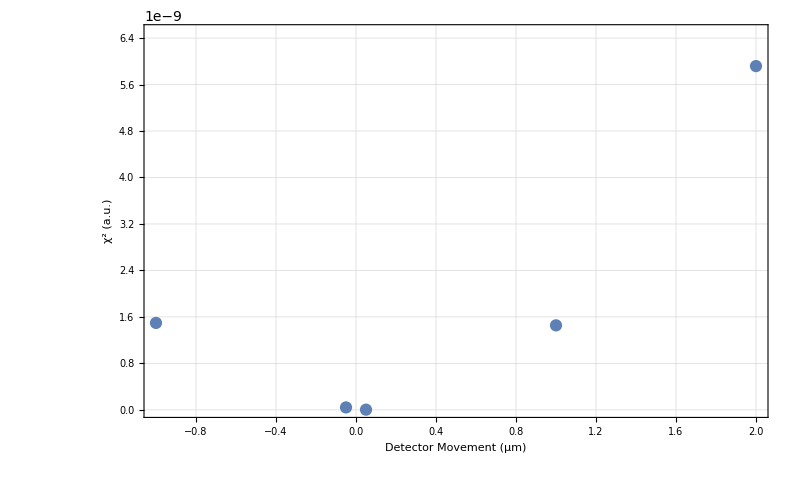

```mathematica
prot1DMov=Show[ListPlot[errorplotdata],Plot[fitresult[b],{b,-1,2},PlotStyle->Red],PlotRange->{{-1,2},{0,6.5*10^-9}},ImageSize->800,FrameStyle->Directive[Thick,Black],Frame->True,GridLines->Automatic,LabelStyle->Directive[FontSize->20,Bold,Black],FrameStyle->Thick,FrameTicksStyle->Thick,FrameLabel->{"Detector Movement (µm)","χ^2 (a.u.)"}]
```

```mathematica
Export["~/Desktop/Images/prot1DMov.svg",prot1DMov];Export["~/Desktop/Images/prot1DMov.png",prot1DMov]
```

~/Desktop/Images/prot1DMov.png

```mathematica
movListProt
```

{-1,-0.05,0.05,1,2,10}

```mathematica
fitresult=NonlinearModelFit[Transpose[{movListProt,Chi2ListProt}],{fitfuncPar[b,b0,yoffset,scale],-1*10^{-6}<b0<1*10^{-6}&&0.<scale<1/10&&0.<yoffset≤Min[Chi2ListProt]},{{b0,-0.1051},{scale,5/10^4},{yoffset,Min[Chi2ListProt]}},b,Method->"NMinimize",Weights->1/dChi2ListProt^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

NonlinearModelFit::wts: The value of option Weights -> {7.12558×10^11 10^(2 Prec),1.54435×10^13 10^(2 Prec),2.9031×10^14 10^(2 Prec),7.08244×10^11 10^(2 Prec),1.73787×10^11 10^(2 Prec),7.55592×10^9 10^(2 Prec)} should be a list of real numbers or a pure function.

NonlinearModelFit[{{-1,1.49644×10^-9},{-0.05,4.24029×10^-11},{0.05,3.71906×10^-12},{1,1.45484×10^-9},{2,5.91737×10^-9},{10,1.4067×10^-7}},{fitfuncPar[b,b0,yoffset,scale],{-1/1000000}<b0<{1/1000000}&&0.<scale<1/10&&0.<yoffset≤3.71906×10^-12},{{b0,-0.1051},{scale,1/2000},{yoffset,3.71906×10^-12}},b,Method→NMinimize,Weights→{7.12558×10^11 10^(2 Prec),1.54435×10^13 10^(2 Prec),2.9031×10^14 10^(2 Prec),7.08244×10^11 10^(2 Prec),1.73787×10^11 10^(2 Prec),7.55592×10^9 10^(2 Prec)},VarianceEstimatorFunction→(1&),PrecisionGoal→10]

```mathematica
9.999955130444998*^-7*10^-6
```

9.99996×10^-13

```mathematica
fitresult["ParameterTable"]
```

NonlinearModelFit[{{-1,1.49644×10^-9},{-0.05,4.24029×10^-11},{0.05,3.71906×10^-12},{1,1.45484×10^-9},{2,5.91737×10^-9},{10,1.4067×10^-7}},{fitfuncPar[b,b0,yoffset,scale],{-1/1000000}<b0<{1/1000000}&&0.<scale<1/10&&0.<yoffset≤3.71906×10^-12},{{b0,-0.1051},{scale,1/2000},{yoffset,3.71906×10^-12}},b,Method→NMinimize,Weights→{7.12558×10^11 10^(2 Prec),1.54435×10^13 10^(2 Prec),2.9031×10^14 10^(2 Prec),7.08244×10^11 10^(2 Prec),1.73787×10^11 10^(2 Prec),7.55592×10^9 10^(2 Prec)},VarianceEstimatorFunction→(1&),PrecisionGoal→10][ParameterTable]

```mathematica
Sigma=(If[#1==0,10000,10^-Prec #1]&)/@RefNormed;
```

```mathematica
RefTransferDel=Delete[RefTransfer,NonZeroPos];RefNorm=Total[RefTransferDel];TransferDataListDel=Table[Delete[TransferDataList⟦para⟧,NonZeroPos],{para,Length[ParaList]}];bMin=Min[ParaList]-0.0005;bMax=Max[ParaList]+0.0005;RefNormed=RefTransferDel/RefNorm;Sigma=(If[#1==0,10000,10^-Prec #1]&)/@RefNormed;TransferDataListNormed=(#1/Total[#1]&)/@TransferDataListDel;Chi2List=Table[Total[(RefNormed-TransferDataListNormed⟦b⟧)^2],{b,1,Length[ParaList]}];dChi2List=Table[10^-Prec √Total[(RefNormed-TransferDataListNormed⟦b⟧)^2 (RefNormed^2+TransferDataListNormed⟦b⟧^2)],{b,1,Length[ParaList]}];errorplotdata=Transpose[{ParaList,Table[10^9 Around[Chi2List⟦b⟧,dChi2List⟦b⟧],{b,1,Length[ParaList]}]}];fitfunc[x_,x0_,f_,g_]:=f+g (x-x0)^2;fitresult=NonlinearModelFit[Transpose[{ParaList,Chi2List}],{fitfunc[b,b0,yoffset,scale],bMin<b0<bMax&&0.<scale<1/10&&0.<yoffset≤Min[Chi2List]},{{b0,-0.1051},{scale,5/10^4},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2List^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10];{{Chi2List,dChi2List},TableForm[{{"a0 = ",fitresult["BestFitParameters"]⟦1,2⟧},fitresult,fitresult["ParameterTable"],fitresult["ANOVATable"]}],Show[ListPlot[errorplotdata,PlotRange->{{bMin,bMax},Automatic}],Plot[10^9 fitresult[b],{b,bMin,bMax},PlotStyle->Red]]}]
```

```mathematica
?TransferToRefParableFitForProtons0Del
```

```mathematica
rAInvest[[2]]
```

a0 =  | -0.105924
FittedModel[1.20991×10^-10+0.00158838 (0.105924+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105924 | 0.0000505951 | -2093.57 | 2.28153×10^-7
scale | 0.00158838 | 0.000116224 | 13.6666 | 0.0053114
yoffset | 1.20991×10^-10 | 3.93431×10^-11 | 3.07527 | 0.0914633 | 
 | DF | SS | MS
Model | 3 | 1111.49 | 370.497
Error | 2 | 0.146511 | 0.0732556
Uncorrected Total | 5 | 1111.64 | 
Corrected Total | 4 | 849.077 |  |

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/10^-6
```

8802.482.

```mathematica
9000*50*10^-9.
```

0.00045

```mathematica
list={#/Total[#]&@da0Spectruma1050detShiftMin[[All,2]],#/Total[#]&@da0Spectruma1050detShiftMin2[[All,2]],#/Total[#]&@da0Spectruma1050detShift2[[All,2]],#/Total[#]&@da0Spectruma1050detShift[[All,2]]};
```

```mathematica
bl={-1*10^-6.,-0.05*10^-6,0.05*10^-6,1*10^-6.}
```

{-1.×10^-6,-5.×10^-8,5.×10^-8,1.×10^-6}

```mathematica
Max[bl]
```

1.×10^-6

```mathematica
RefNorm
```

RefNorm

```mathematica
Sigma=(If[#1==0,10000,10^-4 #1]&)/@RefNorm;
```

```mathematica
TransferDataListNormed=(#1/Total[#1]&)/@list;
```

```mathematica
Chi2List=Table[Total[(RefNorm-TransferDataListNormed⟦b⟧)^2],{b,1,Length[bl]}];
```

```mathematica
dChi2List=Table[10^-4 √Total[(RefNorm-TransferDataListNormed⟦b⟧)^2 (RefNorm^2+TransferDataListNormed⟦b⟧^2)],{b,1,Length[bl]}];
```

```mathematica
errorplotdata=Transpose[{bl,Table[10^9 Around[Chi2List⟦b⟧,dChi2List⟦b⟧],{b,1,Length[bl]}]}];
```

```mathematica
fitfunc[x_,x0_,f_,g_]:=f+g (x-x0)^2;
```

```mathematica
Clear[b]
```

```mathematica
5./10^4
```

0.0005

```mathematica
Min[Chi2List]
```

Min[(-0.0373204+RefNorm)^2+(-0.0372661+RefNorm)^2+(-0.037107+RefNorm)^2+(-0.0369205+RefNorm)^2+(-0.0366229+RefNorm)^2+(-0.0363033+RefNorm)^2+(-0.0358678+RefNorm)^2+(-0.0353971+RefNorm)^2+(-0.0348659+RefNorm)^2+(-0.0342067+RefNorm)^2+(-0.0336181+RefNorm)^2+(-0.0327256+RefNorm)^2+(-0.0321965+RefNorm)^2+(-0.0309429+RefNorm)^2+(-0.030607+RefNorm)^2+(-0.0289139+RefNorm)^2+(-0.0288747+RefNorm)^2+(-0.0270487+RefNorm)^2+(-0.0266892+RefNorm)^2+(-0.0251545+RefNorm)^2+(-0.0242574+RefNorm)^2+(-0.023241+RefNorm)^2+(-0.021745+RefNorm)^2+(-0.0213191+RefNorm)^2+(-0.0194179+RefNorm)^2+(-0.0192252+RefNorm)^2+(-0.0175531+RefNorm)^2+(-0.0167641+RefNorm)^2+(-0.0157336+RefNorm)^2+(-0.0144307+RefNorm)^2+(-0.0139807+RefNorm)^2+(-0.0123023+RefNorm)^2+(-0.0122589+RefNorm)^2+(-0.0107037+RefNorm)^2+(-0.0103211+RefNorm)^2+(-0.00920024+RefNorm)^2+(-0.00859764+RefNorm)^2+(-0.00779265+RefNorm)^2+(-0.00716392+RefNorm)^2+(-0.00649372+RefNorm)^2+(-0.0059715+RefNorm)^2+(-0.005309+RefNorm)^2+(-0.00494119+RefNorm)^2+(-0.00424407+RefNorm)^2+(-0.00401959+RefNorm)^2+(-0.00330341+RefNorm)^2+(-0.00325169+RefNorm)^2+(-0.00263377+RefNorm)^2+(-0.00249268+RefNorm)^2+(-0.00208801+RefNorm)^2+(-0.00177134+RefNorm)^2+(-0.0016089+RefNorm)^2+(-0.00123398+RefNorm)^2+(-0.00123064+RefNorm)^2+(-0.00092376+RefNorm)^2+(-0.000834884+RefNorm)^2+(-0.000673704+RefNorm)^2+(-0.000521806+RefNorm)^2+(-0.000478272+RefNorm)^2+(-0.000394538+RefNorm)^2+(-0.000310685+RefNorm)^2+(-0.000297602+RefNorm)^2+(-0.000165244+RefNorm)^2+(-0.000148992+RefNorm)^2,(-0.0373205+RefNorm)^2+(-0.0372679+RefNorm)^2+(-0.0371058+RefNorm)^2+(-0.036922+RefNorm)^2+(-0.036621+RefNorm)^2+(-0.0363066+RefNorm)^2+(-0.0358653+RefNorm)^2+(-0.0354004+RefNorm)^2+(-0.0348622+RefNorm)^2+(-0.034212+RefNorm)^2+(-0.0336149+RefNorm)^2+(-0.0327311+RefNorm)^2+(-0.0321907+RefNorm)^2+(-0.0309484+RefNorm)^2+(-0.0306014+RefNorm)^2+(-0.0289208+RefNorm)^2+(-0.0288689+RefNorm)^2+(-0.0270425+RefNorm)^2+(-0.0266972+RefNorm)^2+(-0.0251478+RefNorm)^2+(-0.0242658+RefNorm)^2+(-0.0232346+RefNorm)^2+(-0.0217526+RefNorm)^2+(-0.0213128+RefNorm)^2+(-0.0194116+RefNorm)^2+(-0.0192329+RefNorm)^2+(-0.0175465+RefNorm)^2+(-0.016772+RefNorm)^2+(-0.0157277+RefNorm)^2+(-0.0144382+RefNorm)^2+(-0.013975+RefNorm)^2+(-0.0122968+RefNorm)^2+(-0.0122659+RefNorm)^2+(-0.0106986+RefNorm)^2+(-0.0103271+RefNorm)^2+(-0.0091966+RefNorm)^2+(-0.008603+RefNorm)^2+(-0.00778847+RefNorm)^2+(-0.0071683+RefNorm)^2+(-0.0064896+RefNorm)^2+(-0.0059752+RefNorm)^2+(-0.00530528+RefNorm)^2+(-0.00494438+RefNorm)^2+(-0.00424074+RefNorm)^2+(-0.00402139+RefNorm)^2+(-0.00330048+RefNorm)^2+(-0.00325392+RefNorm)^2+(-0.00263476+RefNorm)^2+(-0.00249022+RefNorm)^2+(-0.00208971+RefNorm)^2+(-0.00176936+RefNorm)^2+(-0.00161025+RefNorm)^2+(-0.00123242+RefNorm)^2+(-0.00123173+RefNorm)^2+(-0.000924683+RefNorm)^2+(-0.000833679+RefNorm)^2+(-0.000674438+RefNorm)^2+(-0.000520923+RefNorm)^2+(-0.000478801+RefNorm)^2+(-0.000395015+RefNorm)^2+(-0.00031107+RefNorm)^2+(-0.000296994+RefNorm)^2+(-0.000164446+RefNorm)^2+(-0.000148609+RefNorm)^2,(-0.0373205+RefNorm)^2+(-0.0372681+RefNorm)^2+(-0.0371057+RefNorm)^2+(-0.0369222+RefNorm)^2+(-0.0366208+RefNorm)^2+(-0.0363019+RefNorm)^2+(-0.035865+RefNorm)^2+(-0.0354008+RefNorm)^2+(-0.0348618+RefNorm)^2+(-0.0342125+RefNorm)^2+(-0.0336145+RefNorm)^2+(-0.0327317+RefNorm)^2+(-0.0321903+RefNorm)^2+(-0.030949+RefNorm)^2+(-0.0306009+RefNorm)^2+(-0.0289216+RefNorm)^2+(-0.0288683+RefNorm)^2+(-0.027042+RefNorm)^2+(-0.0266981+RefNorm)^2+(-0.0251472+RefNorm)^2+(-0.0242667+RefNorm)^2+(-0.023234+RefNorm)^2+(-0.0217535+RefNorm)^2+(-0.0213121+RefNorm)^2+(-0.019411+RefNorm)^2+(-0.0192338+RefNorm)^2+(-0.0175459+RefNorm)^2+(-0.0167728+RefNorm)^2+(-0.0157271+RefNorm)^2+(-0.014439+RefNorm)^2+(-0.0139744+RefNorm)^2+(-0.0122962+RefNorm)^2+(-0.0122665+RefNorm)^2+(-0.0106981+RefNorm)^2+(-0.0103278+RefNorm)^2+(-0.00919611+RefNorm)^2+(-0.00860354+RefNorm)^2+(-0.00778801+RefNorm)^2+(-0.00716876+RefNorm)^2+(-0.00648918+RefNorm)^2+(-0.00597559+RefNorm)^2+(-0.00530489+RefNorm)^2+(-0.00494472+RefNorm)^2+(-0.0042404+RefNorm)^2+(-0.00402551+RefNorm)^2+(-0.00330018+RefNorm)^2+(-0.00325416+RefNorm)^2+(-0.00263497+RefNorm)^2+(-0.00248996+RefNorm)^2+(-0.0020899+RefNorm)^2+(-0.00176915+RefNorm)^2+(-0.0016104+RefNorm)^2+(-0.00123225+RefNorm)^2+(-0.00123185+RefNorm)^2+(-0.000924781+RefNorm)^2+(-0.000833553+RefNorm)^2+(-0.000674516+RefNorm)^2+(-0.000520831+RefNorm)^2+(-0.000478861+RefNorm)^2+(-0.000395066+RefNorm)^2+(-0.000311111+RefNorm)^2+(-0.000296931+RefNorm)^2+(-0.000164472+RefNorm)^2+(-0.000148569+RefNorm)^2,(-0.0373199+RefNorm)^2+(-0.0372677+RefNorm)^2+(-0.0371045+RefNorm)^2+(-0.0369237+RefNorm)^2+(-0.0366187+RefNorm)^2+(-0.0363062+RefNorm)^2+(-0.0358622+RefNorm)^2+(-0.0354041+RefNorm)^2+(-0.0348581+RefNorm)^2+(-0.0342169+RefNorm)^2+(-0.0336103+RefNorm)^2+(-0.0327369+RefNorm)^2+(-0.0321862+RefNorm)^2+(-0.0309559+RefNorm)^2+(-0.0305952+RefNorm)^2+(-0.0289286+RefNorm)^2+(-0.028862+RefNorm)^2+(-0.0270358+RefNorm)^2+(-0.0267056+RefNorm)^2+(-0.0251408+RefNorm)^2+(-0.0242766+RefNorm)^2+(-0.0232276+RefNorm)^2+(-0.0217618+RefNorm)^2+(-0.0213058+RefNorm)^2+(-0.0194048+RefNorm)^2+(-0.0192422+RefNorm)^2+(-0.0175397+RefNorm)^2+(-0.0167798+RefNorm)^2+(-0.0157211+RefNorm)^2+(-0.0144454+RefNorm)^2+(-0.0139687+RefNorm)^2+(-0.0122908+RefNorm)^2+(-0.0122733+RefNorm)^2+(-0.0106928+RefNorm)^2+(-0.0103335+RefNorm)^2+(-0.00919127+RefNorm)^2+(-0.00860866+RefNorm)^2+(-0.00778353+RefNorm)^2+(-0.00717308+RefNorm)^2+(-0.00648498+RefNorm)^2+(-0.00597931+RefNorm)^2+(-0.00530116+RefNorm)^2+(-0.00494824+RefNorm)^2+(-0.00423706+RefNorm)^2+(-0.00402803+RefNorm)^2+(-0.00329728+RefNorm)^2+(-0.00325637+RefNorm)^2+(-0.00263691+RefNorm)^2+(-0.0024875+RefNorm)^2+(-0.00209158+RefNorm)^2+(-0.00176714+RefNorm)^2+(-0.00161178+RefNorm)^2+(-0.00123297+RefNorm)^2+(-0.00123069+RefNorm)^2+(-0.000925704+RefNorm)^2+(-0.000832348+RefNorm)^2+(-0.00067525+RefNorm)^2+(-0.000519948+RefNorm)^2+(-0.00047943+RefNorm)^2+(-0.000395543+RefNorm)^2+(-0.000311496+RefNorm)^2+(-0.000296323+RefNorm)^2+(-0.000164718+RefNorm)^2+(-0.000148187+RefNorm)^2]

```mathematica
Transpose[{bl,Chi2List}]
```

{{-1.×10^-6,(-0.0373199+RefNorm)^2+(-0.0372677+RefNorm)^2+(-0.0371045+RefNorm)^2+(-0.0369237+RefNorm)^2+(-0.0366187+RefNorm)^2+(-0.0363062+RefNorm)^2+(-0.0358622+RefNorm)^2+(-0.0354041+RefNorm)^2+(-0.0348581+RefNorm)^2+(-0.0342169+RefNorm)^2+(-0.0336103+RefNorm)^2+(-0.0327369+RefNorm)^2+(-0.0321862+RefNorm)^2+(-0.0309559+RefNorm)^2+(-0.0305952+RefNorm)^2+(-0.0289286+RefNorm)^2+(-0.028862+RefNorm)^2+(-0.0270358+RefNorm)^2+(-0.0267056+RefNorm)^2+(-0.0251408+RefNorm)^2+(-0.0242766+RefNorm)^2+(-0.0232276+RefNorm)^2+(-0.0217618+RefNorm)^2+(-0.0213058+RefNorm)^2+(-0.0194048+RefNorm)^2+(-0.0192422+RefNorm)^2+(-0.0175397+RefNorm)^2+(-0.0167798+RefNorm)^2+(-0.0157211+RefNorm)^2+(-0.0144454+RefNorm)^2+(-0.0139687+RefNorm)^2+(-0.0122908+RefNorm)^2+(-0.0122733+RefNorm)^2+(-0.0106928+RefNorm)^2+(-0.0103335+RefNorm)^2+(-0.00919127+RefNorm)^2+(-0.00860866+RefNorm)^2+(-0.00778353+RefNorm)^2+(-0.00717308+RefNorm)^2+(-0.00648498+RefNorm)^2+(-0.00597931+RefNorm)^2+(-0.00530116+RefNorm)^2+(-0.00494824+RefNorm)^2+(-0.00423706+RefNorm)^2+(-0.00402803+RefNorm)^2+(-0.00329728+RefNorm)^2+(-0.00325637+RefNorm)^2+(-0.00263691+RefNorm)^2+(-0.0024875+RefNorm)^2+(-0.00209158+RefNorm)^2+(-0.00176714+RefNorm)^2+(-0.00161178+RefNorm)^2+(-0.00123297+RefNorm)^2+(-0.00123069+RefNorm)^2+(-0.000925704+RefNorm)^2+(-0.000832348+RefNorm)^2+(-0.00067525+RefNorm)^2+(-0.000519948+RefNorm)^2+(-0.00047943+RefNorm)^2+(-0.000395543+RefNorm)^2+(-0.000311496+RefNorm)^2+(-0.000296323+RefNorm)^2+(-0.000164718+RefNorm)^2+(-0.000148187+RefNorm)^2},{-5.×10^-8,(-0.0373205+RefNorm)^2+(-0.0372681+RefNorm)^2+(-0.0371057+RefNorm)^2+(-0.0369222+RefNorm)^2+(-0.0366208+RefNorm)^2+(-0.0363019+RefNorm)^2+(-0.035865+RefNorm)^2+(-0.0354008+RefNorm)^2+(-0.0348618+RefNorm)^2+(-0.0342125+RefNorm)^2+(-0.0336145+RefNorm)^2+(-0.0327317+RefNorm)^2+(-0.0321903+RefNorm)^2+(-0.030949+RefNorm)^2+(-0.0306009+RefNorm)^2+(-0.0289216+RefNorm)^2+(-0.0288683+RefNorm)^2+(-0.027042+RefNorm)^2+(-0.0266981+RefNorm)^2+(-0.0251472+RefNorm)^2+(-0.0242667+RefNorm)^2+(-0.023234+RefNorm)^2+(-0.0217535+RefNorm)^2+(-0.0213121+RefNorm)^2+(-0.019411+RefNorm)^2+(-0.0192338+RefNorm)^2+(-0.0175459+RefNorm)^2+(-0.0167728+RefNorm)^2+(-0.0157271+RefNorm)^2+(-0.014439+RefNorm)^2+(-0.0139744+RefNorm)^2+(-0.0122962+RefNorm)^2+(-0.0122665+RefNorm)^2+(-0.0106981+RefNorm)^2+(-0.0103278+RefNorm)^2+(-0.00919611+RefNorm)^2+(-0.00860354+RefNorm)^2+(-0.00778801+RefNorm)^2+(-0.00716876+RefNorm)^2+(-0.00648918+RefNorm)^2+(-0.00597559+RefNorm)^2+(-0.00530489+RefNorm)^2+(-0.00494472+RefNorm)^2+(-0.0042404+RefNorm)^2+(-0.00402551+RefNorm)^2+(-0.00330018+RefNorm)^2+(-0.00325416+RefNorm)^2+(-0.00263497+RefNorm)^2+(-0.00248996+RefNorm)^2+(-0.0020899+RefNorm)^2+(-0.00176915+RefNorm)^2+(-0.0016104+RefNorm)^2+(-0.00123225+RefNorm)^2+(-0.00123185+RefNorm)^2+(-0.000924781+RefNorm)^2+(-0.000833553+RefNorm)^2+(-0.000674516+RefNorm)^2+(-0.000520831+RefNorm)^2+(-0.000478861+RefNorm)^2+(-0.000395066+RefNorm)^2+(-0.000311111+RefNorm)^2+(-0.000296931+RefNorm)^2+(-0.000164472+RefNorm)^2+(-0.000148569+RefNorm)^2},{5.×10^-8,(-0.0373205+RefNorm)^2+(-0.0372679+RefNorm)^2+(-0.0371058+RefNorm)^2+(-0.036922+RefNorm)^2+(-0.036621+RefNorm)^2+(-0.0363066+RefNorm)^2+(-0.0358653+RefNorm)^2+(-0.0354004+RefNorm)^2+(-0.0348622+RefNorm)^2+(-0.034212+RefNorm)^2+(-0.0336149+RefNorm)^2+(-0.0327311+RefNorm)^2+(-0.0321907+RefNorm)^2+(-0.0309484+RefNorm)^2+(-0.0306014+RefNorm)^2+(-0.0289208+RefNorm)^2+(-0.0288689+RefNorm)^2+(-0.0270425+RefNorm)^2+(-0.0266972+RefNorm)^2+(-0.0251478+RefNorm)^2+(-0.0242658+RefNorm)^2+(-0.0232346+RefNorm)^2+(-0.0217526+RefNorm)^2+(-0.0213128+RefNorm)^2+(-0.0194116+RefNorm)^2+(-0.0192329+RefNorm)^2+(-0.0175465+RefNorm)^2+(-0.016772+RefNorm)^2+(-0.0157277+RefNorm)^2+(-0.0144382+RefNorm)^2+(-0.013975+RefNorm)^2+(-0.0122968+RefNorm)^2+(-0.0122659+RefNorm)^2+(-0.0106986+RefNorm)^2+(-0.0103271+RefNorm)^2+(-0.0091966+RefNorm)^2+(-0.008603+RefNorm)^2+(-0.00778847+RefNorm)^2+(-0.0071683+RefNorm)^2+(-0.0064896+RefNorm)^2+(-0.0059752+RefNorm)^2+(-0.00530528+RefNorm)^2+(-0.00494438+RefNorm)^2+(-0.00424074+RefNorm)^2+(-0.00402139+RefNorm)^2+(-0.00330048+RefNorm)^2+(-0.00325392+RefNorm)^2+(-0.00263476+RefNorm)^2+(-0.00249022+RefNorm)^2+(-0.00208971+RefNorm)^2+(-0.00176936+RefNorm)^2+(-0.00161025+RefNorm)^2+(-0.00123242+RefNorm)^2+(-0.00123173+RefNorm)^2+(-0.000924683+RefNorm)^2+(-0.000833679+RefNorm)^2+(-0.000674438+RefNorm)^2+(-0.000520923+RefNorm)^2+(-0.000478801+RefNorm)^2+(-0.000395015+RefNorm)^2+(-0.00031107+RefNorm)^2+(-0.000296994+RefNorm)^2+(-0.000164446+RefNorm)^2+(-0.000148609+RefNorm)^2},{1.×10^-6,(-0.0373204+RefNorm)^2+(-0.0372661+RefNorm)^2+(-0.037107+RefNorm)^2+(-0.0369205+RefNorm)^2+(-0.0366229+RefNorm)^2+(-0.0363033+RefNorm)^2+(-0.0358678+RefNorm)^2+(-0.0353971+RefNorm)^2+(-0.0348659+RefNorm)^2+(-0.0342067+RefNorm)^2+(-0.0336181+RefNorm)^2+(-0.0327256+RefNorm)^2+(-0.0321965+RefNorm)^2+(-0.0309429+RefNorm)^2+(-0.030607+RefNorm)^2+(-0.0289139+RefNorm)^2+(-0.0288747+RefNorm)^2+(-0.0270487+RefNorm)^2+(-0.0266892+RefNorm)^2+(-0.0251545+RefNorm)^2+(-0.0242574+RefNorm)^2+(-0.023241+RefNorm)^2+(-0.021745+RefNorm)^2+(-0.0213191+RefNorm)^2+(-0.0194179+RefNorm)^2+(-0.0192252+RefNorm)^2+(-0.0175531+RefNorm)^2+(-0.0167641+RefNorm)^2+(-0.0157336+RefNorm)^2+(-0.0144307+RefNorm)^2+(-0.0139807+RefNorm)^2+(-0.0123023+RefNorm)^2+(-0.0122589+RefNorm)^2+(-0.0107037+RefNorm)^2+(-0.0103211+RefNorm)^2+(-0.00920024+RefNorm)^2+(-0.00859764+RefNorm)^2+(-0.00779265+RefNorm)^2+(-0.00716392+RefNorm)^2+(-0.00649372+RefNorm)^2+(-0.0059715+RefNorm)^2+(-0.005309+RefNorm)^2+(-0.00494119+RefNorm)^2+(-0.00424407+RefNorm)^2+(-0.00401959+RefNorm)^2+(-0.00330341+RefNorm)^2+(-0.00325169+RefNorm)^2+(-0.00263377+RefNorm)^2+(-0.00249268+RefNorm)^2+(-0.00208801+RefNorm)^2+(-0.00177134+RefNorm)^2+(-0.0016089+RefNorm)^2+(-0.00123398+RefNorm)^2+(-0.00123064+RefNorm)^2+(-0.00092376+RefNorm)^2+(-0.000834884+RefNorm)^2+(-0.000673704+RefNorm)^2+(-0.000521806+RefNorm)^2+(-0.000478272+RefNorm)^2+(-0.000394538+RefNorm)^2+(-0.000310685+RefNorm)^2+(-0.000297602+RefNorm)^2+(-0.000165244+RefNorm)^2+(-0.000148992+RefNorm)^2}}

```mathematica
fitresult=NonlinearModelFit[Transpose[{bl,Chi2List}],{fitfunc[b,b0,yoffset,scale]},{{b0,0},{scale,1},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2List^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

NonlinearModelFit::wts: The value of option Weights -> … should be a list of real numbers or a pure function.

NonlinearModelFit[{{-1.×10^-6,(-0.0373199+RefNorm)^2+(-0.0372677+RefNorm)^2+(-0.0371045+RefNorm)^2+(-0.0369237+RefNorm)^2+(-0.0366187+RefNorm)^2+(-0.0363062+RefNorm)^2+(-0.0358622+RefNorm)^2+(-0.0354041+RefNorm)^2+(-0.0348581+RefNorm)^2+(-0.0342169+RefNorm)^2+(-0.0336103+RefNorm)^2+(-0.0327369+RefNorm)^2+(-0.0321862+RefNorm)^2+(-0.0309559+RefNorm)^2+(-0.0305952+RefNorm)^2+(-0.0289286+RefNorm)^2+(-0.028862+RefNorm)^2+(-0.0270358+RefNorm)^2+(-0.0267056+RefNorm)^2+(-0.0251408+RefNorm)^2+(-0.0242766+RefNorm)^2+(-0.0232276+RefNorm)^2+(-0.0217618+RefNorm)^2+(-0.0213058+RefNorm)^2+(-0.0194048+RefNorm)^2+(-0.0192422+RefNorm)^2+(-0.0175397+RefNorm)^2+(-0.0167798+RefNorm)^2+(-0.0157211+RefNorm)^2+(-0.0144454+RefNorm)^2+(-0.0139687+RefNorm)^2+(-0.0122908+RefNorm)^2+(-0.0122733+RefNorm)^2+(-0.0106928+RefNorm)^2+(-0.0103335+RefNorm)^2+(-0.00919127+RefNorm)^2+(-0.00860866+RefNorm)^2+(-0.00778353+RefNorm)^2+(-0.00717308+RefNorm)^2+(-0.00648498+RefNorm)^2+(-0.00597931+RefNorm)^2+(-0.00530116+RefNorm)^2+(-0.00494824+RefNorm)^2+(-0.00423706+RefNorm)^2+(-0.00402803+RefNorm)^2+(-0.00329728+RefNorm)^2+(-0.00325637+RefNorm)^2+(-0.00263691+RefNorm)^2+(-0.0024875+RefNorm)^2+(-0.00209158+RefNorm)^2+(-0.00176714+RefNorm)^2+(-0.00161178+RefNorm)^2+(-0.00123297+RefNorm)^2+(-0.00123069+RefNorm)^2+(-0.000925704+RefNorm)^2+(-0.000832348+RefNorm)^2+(-0.00067525+RefNorm)^2+(-0.000519948+RefNorm)^2+(-0.00047943+RefNorm)^2+(-0.000395543+RefNorm)^2+(-0.000311496+RefNorm)^2+(-0.000296323+RefNorm)^2+(-0.000164718+RefNorm)^2+(-0.000148187+RefNorm)^2},{-5.×10^-8,(-0.0373205+RefNorm)^2+(-0.0372681+RefNorm)^2+(-0.0371057+RefNorm)^2+(-0.0369222+RefNorm)^2+(-0.0366208+RefNorm)^2+(-0.0363019+RefNorm)^2+(-0.035865+RefNorm)^2+(-0.0354008+RefNorm)^2+(-0.0348618+RefNorm)^2+(-0.0342125+RefNorm)^2+(-0.0336145+RefNorm)^2+(-0.0327317+RefNorm)^2+(-0.0321903+RefNorm)^2+(-0.030949+RefNorm)^2+(-0.0306009+RefNorm)^2+(-0.0289216+RefNorm)^2+(-0.0288683+RefNorm)^2+(-0.027042+RefNorm)^2+(-0.0266981+RefNorm)^2+(-0.0251472+RefNorm)^2+(-0.0242667+RefNorm)^2+(-0.023234+RefNorm)^2+(-0.0217535+RefNorm)^2+(-0.0213121+RefNorm)^2+(-0.019411+RefNorm)^2+(-0.0192338+RefNorm)^2+(-0.0175459+RefNorm)^2+(-0.0167728+RefNorm)^2+(-0.0157271+RefNorm)^2+(-0.014439+RefNorm)^2+(-0.0139744+RefNorm)^2+(-0.0122962+RefNorm)^2+(-0.0122665+RefNorm)^2+(-0.0106981+RefNorm)^2+(-0.0103278+RefNorm)^2+(-0.00919611+RefNorm)^2+(-0.00860354+RefNorm)^2+(-0.00778801+RefNorm)^2+(-0.00716876+RefNorm)^2+(-0.00648918+RefNorm)^2+(-0.00597559+RefNorm)^2+(-0.00530489+RefNorm)^2+(-0.00494472+RefNorm)^2+(-0.0042404+RefNorm)^2+(-0.00402551+RefNorm)^2+(-0.00330018+RefNorm)^2+(-0.00325416+RefNorm)^2+(-0.00263497+RefNorm)^2+(-0.00248996+RefNorm)^2+(-0.0020899+RefNorm)^2+(-0.00176915+RefNorm)^2+(-0.0016104+RefNorm)^2+(-0.00123225+RefNorm)^2+(-0.00123185+RefNorm)^2+(-0.000924781+RefNorm)^2+(-0.000833553+RefNorm)^2+(-0.000674516+RefNorm)^2+(-0.000520831+RefNorm)^2+(-0.000478861+RefNorm)^2+(-0.000395066+RefNorm)^2+(-0.000311111+RefNorm)^2+(-0.000296931+RefNorm)^2+(-0.000164472+RefNorm)^2+(-0.000148569+RefNorm)^2},{5.×10^-8,(-0.0373205+RefNorm)^2+(-0.0372679+RefNorm)^2+(-0.0371058+RefNorm)^2+(-0.036922+RefNorm)^2+(-0.036621+RefNorm)^2+(-0.0363066+RefNorm)^2+(-0.0358653+RefNorm)^2+(-0.0354004+RefNorm)^2+(-0.0348622+RefNorm)^2+(-0.034212+RefNorm)^2+(-0.0336149+RefNorm)^2+(-0.0327311+RefNorm)^2+(-0.0321907+RefNorm)^2+(-0.0309484+RefNorm)^2+(-0.0306014+RefNorm)^2+(-0.0289208+RefNorm)^2+(-0.0288689+RefNorm)^2+(-0.0270425+RefNorm)^2+(-0.0266972+RefNorm)^2+(-0.0251478+RefNorm)^2+(-0.0242658+RefNorm)^2+(-0.0232346+RefNorm)^2+(-0.0217526+RefNorm)^2+(-0.0213128+RefNorm)^2+(-0.0194116+RefNorm)^2+(-0.0192329+RefNorm)^2+(-0.0175465+RefNorm)^2+(-0.016772+RefNorm)^2+(-0.0157277+RefNorm)^2+(-0.0144382+RefNorm)^2+(-0.013975+RefNorm)^2+(-0.0122968+RefNorm)^2+(-0.0122659+RefNorm)^2+(-0.0106986+RefNorm)^2+(-0.0103271+RefNorm)^2+(-0.0091966+RefNorm)^2+(-0.008603+RefNorm)^2+(-0.00778847+RefNorm)^2+(-0.0071683+RefNorm)^2+(-0.0064896+RefNorm)^2+(-0.0059752+RefNorm)^2+(-0.00530528+RefNorm)^2+(-0.00494438+RefNorm)^2+(-0.00424074+RefNorm)^2+(-0.00402139+RefNorm)^2+(-0.00330048+RefNorm)^2+(-0.00325392+RefNorm)^2+(-0.00263476+RefNorm)^2+(-0.00249022+RefNorm)^2+(-0.00208971+RefNorm)^2+(-0.00176936+RefNorm)^2+(-0.00161025+RefNorm)^2+(-0.00123242+RefNorm)^2+(-0.00123173+RefNorm)^2+(-0.000924683+RefNorm)^2+(-0.000833679+RefNorm)^2+(-0.000674438+RefNorm)^2+(-0.000520923+RefNorm)^2+(-0.000478801+RefNorm)^2+(-0.000395015+RefNorm)^2+(-0.00031107+RefNorm)^2+(-0.000296994+RefNorm)^2+(-0.000164446+RefNorm)^2+(-0.000148609+RefNorm)^2},{1.×10^-6,(-0.0373204+RefNorm)^2+(-0.0372661+RefNorm)^2+(-0.037107+RefNorm)^2+(-0.0369205+RefNorm)^2+(-0.0366229+RefNorm)^2+(-0.0363033+RefNorm)^2+(-0.0358678+RefNorm)^2+(-0.0353971+RefNorm)^2+(-0.0348659+RefNorm)^2+(-0.0342067+RefNorm)^2+(-0.0336181+RefNorm)^2+(-0.0327256+RefNorm)^2+(-0.0321965+RefNorm)^2+(-0.0309429+RefNorm)^2+(-0.030607+RefNorm)^2+(-0.0289139+RefNorm)^2+(-0.0288747+RefNorm)^2+(-0.0270487+RefNorm)^2+(-0.0266892+RefNorm)^2+(-0.0251545+RefNorm)^2+(-0.0242574+RefNorm)^2+(-0.023241+RefNorm)^2+(-0.021745+RefNorm)^2+(-0.0213191+RefNorm)^2+(-0.0194179+RefNorm)^2+(-0.0192252+RefNorm)^2+(-0.0175531+RefNorm)^2+(-0.0167641+RefNorm)^2+(-0.0157336+RefNorm)^2+(-0.0144307+RefNorm)^2+(-0.0139807+RefNorm)^2+(-0.0123023+RefNorm)^2+(-0.0122589+RefNorm)^2+(-0.0107037+RefNorm)^2+(-0.0103211+RefNorm)^2+(-0.00920024+RefNorm)^2+(-0.00859764+RefNorm)^2+(-0.00779265+RefNorm)^2+(-0.00716392+RefNorm)^2+(-0.00649372+RefNorm)^2+(-0.0059715+RefNorm)^2+(-0.005309+RefNorm)^2+(-0.00494119+RefNorm)^2+(-0.00424407+RefNorm)^2+(-0.00401959+RefNorm)^2+(-0.00330341+RefNorm)^2+(-0.00325169+RefNorm)^2+(-0.00263377+RefNorm)^2+(-0.00249268+RefNorm)^2+(-0.00208801+RefNorm)^2+(-0.00177134+RefNorm)^2+(-0.0016089+RefNorm)^2+(-0.00123398+RefNorm)^2+(-0.00123064+RefNorm)^2+(-0.00092376+RefNorm)^2+(-0.000834884+RefNorm)^2+(-0.000673704+RefNorm)^2+(-0.000521806+RefNorm)^2+(-0.000478272+RefNorm)^2+(-0.000394538+RefNorm)^2+(-0.000310685+RefNorm)^2+(-0.000297602+RefNorm)^2+(-0.000165244+RefNorm)^2+(-0.000148992+RefNorm)^2}},{(b-b0)^2 scale+yoffset},{{b0,0},{scale,1},{yoffset,Min[(-0.0373204+RefNorm)^2+(-0.0372661+RefNorm)^2+(-0.037107+RefNorm)^2+(-0.0369205+RefNorm)^2+(-0.0366229+RefNorm)^2+(-0.0363033+RefNorm)^2+(-0.0358678+RefNorm)^2+(-0.0353971+RefNorm)^2+(-0.0348659+RefNorm)^2+(-0.0342067+RefNorm)^2+(-0.0336181+RefNorm)^2+(-0.0327256+RefNorm)^2+(-0.0321965+RefNorm)^2+(-0.0309429+RefNorm)^2+(-0.030607+RefNorm)^2+(-0.0289139+RefNorm)^2+(-0.0288747+RefNorm)^2+(-0.0270487+RefNorm)^2+(-0.0266892+RefNorm)^2+(-0.0251545+RefNorm)^2+(-0.0242574+RefNorm)^2+(-0.023241+RefNorm)^2+(-0.021745+RefNorm)^2+(-0.0213191+RefNorm)^2+(-0.0194179+RefNorm)^2+(-0.0192252+RefNorm)^2+(-0.0175531+RefNorm)^2+(-0.0167641+RefNorm)^2+(-0.0157336+RefNorm)^2+(-0.0144307+RefNorm)^2+(-0.0139807+RefNorm)^2+(-0.0123023+RefNorm)^2+(-0.0122589+RefNorm)^2+(-0.0107037+RefNorm)^2+(-0.0103211+RefNorm)^2+(-0.00920024+RefNorm)^2+(-0.00859764+RefNorm)^2+(-0.00779265+RefNorm)^2+(-0.00716392+RefNorm)^2+(-0.00649372+RefNorm)^2+(-0.0059715+RefNorm)^2+(-0.005309+RefNorm)^2+(-0.00494119+RefNorm)^2+(-0.00424407+RefNorm)^2+(-0.00401959+RefNorm)^2+(-0.00330341+RefNorm)^2+(-0.00325169+RefNorm)^2+(-0.00263377+RefNorm)^2+(-0.00249268+RefNorm)^2+(-0.00208801+RefNorm)^2+(-0.00177134+RefNorm)^2+(-0.0016089+RefNorm)^2+(-0.00123398+RefNorm)^2+(-0.00123064+RefNorm)^2+(-0.00092376+RefNorm)^2+(-0.000834884+RefNorm)^2+(-0.000673704+RefNorm)^2+(-0.000521806+RefNorm)^2+(-0.000478272+RefNorm)^2+(-0.000394538+RefNorm)^2+(-0.000310685+RefNorm)^2+(-0.000297602+RefNorm)^2+(-0.000165244+RefNorm)^2+(-0.000148992+RefNorm)^2,(-0.0373205+RefNorm)^2+(-0.0372679+RefNorm)^2+(-0.0371058+RefNorm)^2+(-0.036922+RefNorm)^2+(-0.036621+RefNorm)^2+(-0.0363066+RefNorm)^2+(-0.0358653+RefNorm)^2+(-0.0354004+RefNorm)^2+(-0.0348622+RefNorm)^2+(-0.034212+RefNorm)^2+(-0.0336149+RefNorm)^2+(-0.0327311+RefNorm)^2+(-0.0321907+RefNorm)^2+(-0.0309484+RefNorm)^2+(-0.0306014+RefNorm)^2+(-0.0289208+RefNorm)^2+(-0.0288689+RefNorm)^2+(-0.0270425+RefNorm)^2+(-0.0266972+RefNorm)^2+(-0.0251478+RefNorm)^2+(-0.0242658+RefNorm)^2+(-0.0232346+RefNorm)^2+(-0.0217526+RefNorm)^2+(-0.0213128+RefNorm)^2+(-0.0194116+RefNorm)^2+(-0.0192329+RefNorm)^2+(-0.0175465+RefNorm)^2+(-0.016772+RefNorm)^2+(-0.0157277+RefNorm)^2+(-0.0144382+RefNorm)^2+(-0.013975+RefNorm)^2+(-0.0122968+RefNorm)^2+(-0.0122659+RefNorm)^2+(-0.0106986+RefNorm)^2+(-0.0103271+RefNorm)^2+(-0.0091966+RefNorm)^2+(-0.008603+RefNorm)^2+(-0.00778847+RefNorm)^2+(-0.0071683+RefNorm)^2+(-0.0064896+RefNorm)^2+(-0.0059752+RefNorm)^2+(-0.00530528+RefNorm)^2+(-0.00494438+RefNorm)^2+(-0.00424074+RefNorm)^2+(-0.00402139+RefNorm)^2+(-0.00330048+RefNorm)^2+(-0.00325392+RefNorm)^2+(-0.00263476+RefNorm)^2+(-0.00249022+RefNorm)^2+(-0.00208971+RefNorm)^2+(-0.00176936+RefNorm)^2+(-0.00161025+RefNorm)^2+(-0.00123242+RefNorm)^2+(-0.00123173+RefNorm)^2+(-0.000924683+RefNorm)^2+(-0.000833679+RefNorm)^2+(-0.000674438+RefNorm)^2+(-0.000520923+RefNorm)^2+(-0.000478801+RefNorm)^2+(-0.000395015+RefNorm)^2+(-0.00031107+RefNorm)^2+(-0.000296994+RefNorm)^2+(-0.000164446+RefNorm)^2+(-0.000148609+RefNorm)^2,(-0.0373205+RefNorm)^2+(-0.0372681+RefNorm)^2+(-0.0371057+RefNorm)^2+(-0.0369222+RefNorm)^2+(-0.0366208+RefNorm)^2+(-0.0363019+RefNorm)^2+(-0.035865+RefNorm)^2+(-0.0354008+RefNorm)^2+(-0.0348618+RefNorm)^2+(-0.0342125+RefNorm)^2+(-0.0336145+RefNorm)^2+(-0.0327317+RefNorm)^2+(-0.0321903+RefNorm)^2+(-0.030949+RefNorm)^2+(-0.0306009+RefNorm)^2+(-0.0289216+RefNorm)^2+(-0.0288683+RefNorm)^2+(-0.027042+RefNorm)^2+(-0.0266981+RefNorm)^2+(-0.0251472+RefNorm)^2+(-0.0242667+RefNorm)^2+(-0.023234+RefNorm)^2+(-0.0217535+RefNorm)^2+(-0.0213121+RefNorm)^2+(-0.019411+RefNorm)^2+(-0.0192338+RefNorm)^2+(-0.0175459+RefNorm)^2+(-0.0167728+RefNorm)^2+(-0.0157271+RefNorm)^2+(-0.014439+RefNorm)^2+(-0.0139744+RefNorm)^2+(-0.0122962+RefNorm)^2+(-0.0122665+RefNorm)^2+(-0.0106981+RefNorm)^2+(-0.0103278+RefNorm)^2+(-0.00919611+RefNorm)^2+(-0.00860354+RefNorm)^2+(-0.00778801+RefNorm)^2+(-0.00716876+RefNorm)^2+(-0.00648918+RefNorm)^2+(-0.00597559+RefNorm)^2+(-0.00530489+RefNorm)^2+(-0.00494472+RefNorm)^2+(-0.0042404+RefNorm)^2+(-0.00402551+RefNorm)^2+(-0.00330018+RefNorm)^2+(-0.00325416+RefNorm)^2+(-0.00263497+RefNorm)^2+(-0.00248996+RefNorm)^2+(-0.0020899+RefNorm)^2+(-0.00176915+RefNorm)^2+(-0.0016104+RefNorm)^2+(-0.00123225+RefNorm)^2+(-0.00123185+RefNorm)^2+(-0.000924781+RefNorm)^2+(-0.000833553+RefNorm)^2+(-0.000674516+RefNorm)^2+(-0.000520831+RefNorm)^2+(-0.000478861+RefNorm)^2+(-0.000395066+RefNorm)^2+(-0.000311111+RefNorm)^2+(-0.000296931+RefNorm)^2+(-0.000164472+RefNorm)^2+(-0.000148569+RefNorm)^2,(-0.0373199+RefNorm)^2+(-0.0372677+RefNorm)^2+(-0.0371045+RefNorm)^2+(-0.0369237+RefNorm)^2+(-0.0366187+RefNorm)^2+(-0.0363062+RefNorm)^2+(-0.0358622+RefNorm)^2+(-0.0354041+RefNorm)^2+(-0.0348581+RefNorm)^2+(-0.0342169+RefNorm)^2+(-0.0336103+RefNorm)^2+(-0.0327369+RefNorm)^2+(-0.0321862+RefNorm)^2+(-0.0309559+RefNorm)^2+(-0.0305952+RefNorm)^2+(-0.0289286+RefNorm)^2+(-0.028862+RefNorm)^2+(-0.0270358+RefNorm)^2+(-0.0267056+RefNorm)^2+(-0.0251408+RefNorm)^2+(-0.0242766+RefNorm)^2+(-0.0232276+RefNorm)^2+(-0.0217618+RefNorm)^2+(-0.0213058+RefNorm)^2+(-0.0194048+RefNorm)^2+(-0.0192422+RefNorm)^2+(-0.0175397+RefNorm)^2+(-0.0167798+RefNorm)^2+(-0.0157211+RefNorm)^2+(-0.0144454+RefNorm)^2+(-0.0139687+RefNorm)^2+(-0.0122908+RefNorm)^2+(-0.0122733+RefNorm)^2+(-0.0106928+RefNorm)^2+(-0.0103335+RefNorm)^2+(-0.00919127+RefNorm)^2+(-0.00860866+RefNorm)^2+(-0.00778353+RefNorm)^2+(-0.00717308+RefNorm)^2+(-0.00648498+RefNorm)^2+(-0.00597931+RefNorm)^2+(-0.00530116+RefNorm)^2+(-0.00494824+RefNorm)^2+(-0.00423706+RefNorm)^2+(-0.00402803+RefNorm)^2+(-0.00329728+RefNorm)^2+(-0.00325637+RefNorm)^2+(-0.00263691+RefNorm)^2+(-0.0024875+RefNorm)^2+(-0.00209158+RefNorm)^2+(-0.00176714+RefNorm)^2+(-0.00161178+RefNorm)^2+(-0.00123297+RefNorm)^2+(-0.00123069+RefNorm)^2+(-0.000925704+RefNorm)^2+(-0.000832348+RefNorm)^2+(-0.00067525+RefNorm)^2+(-0.000519948+RefNorm)^2+(-0.00047943+RefNorm)^2+(-0.000395543+RefNorm)^2+(-0.000311496+RefNorm)^2+(-0.000296323+RefNorm)^2+(-0.000164718+RefNorm)^2+(-0.000148187+RefNorm)^2]}},b,Method→NMinimize,Weights→{100000000/((-0.000148187+RefNorm)^2 (2.19593×10^-8+RefNorm^2)+(-0.000164718+RefNorm)^2 (2.71322×10^-8+RefNorm^2)+(-0.000296323+RefNorm)^2 (8.78075×10^-8+RefNorm^2)+(-0.000311496+RefNorm)^2 (9.70296×10^-8+RefNorm^2)+(-0.000395543+RefNorm)^2 (1.56454×10^-7+RefNorm^2)+(-0.00047943+RefNorm)^2 (2.29853×10^-7+RefNorm^2)+(-0.000519948+RefNorm)^2 (2.70346×10^-7+RefNorm^2)+(-0.00067525+RefNorm)^2 (4.55962×10^-7+RefNorm^2)+(-0.000832348+RefNorm)^2 (6.92803×10^-7+RefNorm^2)+(-0.000925704+RefNorm)^2 (8.56929×10^-7+RefNorm^2)+(-0.00123069+RefNorm)^2 (1.51459×10^-6+RefNorm^2)+(-0.00123297+RefNorm)^2 (1.52022×10^-6+RefNorm^2)+(-0.00161178+RefNorm)^2 (2.59784×10^-6+RefNorm^2)+(-0.00176714+RefNorm)^2 (3.12277×10^-6+RefNorm^2)+(-0.00209158+RefNorm)^2 (4.37471×10^-6+RefNorm^2)+(-0.0024875+RefNorm)^2 (6.18765×10^-6+RefNorm^2)+(-0.00263691+RefNorm)^2 (6.95327×10^-6+RefNorm^2)+(-0.00325637+RefNorm)^2 (0.000010604+RefNorm^2)+(-0.00329728+RefNorm)^2 (0.0000108721+RefNorm^2)+(-0.00402803+RefNorm)^2 (0.000016225+RefNorm^2)+(-0.00423706+RefNorm)^2 (0.0000179526+RefNorm^2)+(-0.00494824+RefNorm)^2 (0.0000244851+RefNorm^2)+(-0.00530116+RefNorm)^2 (0.0000281023+RefNorm^2)+(-0.00597931+RefNorm)^2 (0.0000357522+RefNorm^2)+(-0.00648498+RefNorm)^2 (0.0000420549+RefNorm^2)+(-0.00717308+RefNorm)^2 (0.000051453+RefNorm^2)+(-0.00778353+RefNorm)^2 (0.0000605833+RefNorm^2)+(-0.00860866+RefNorm)^2 (0.000074109+RefNorm^2)+(-0.00919127+RefNorm)^2 (0.0000844794+RefNorm^2)+(-0.0103335+RefNorm)^2 (0.000106781+RefNorm^2)+(-0.0106928+RefNorm)^2 (0.000114336+RefNorm^2)+(-0.0122733+RefNorm)^2 (0.000150634+RefNorm^2)+(-0.0122908+RefNorm)^2 (0.000151064+RefNorm^2)+(-0.0139687+RefNorm)^2 (0.000195125+RefNorm^2)+(-0.0144454+RefNorm)^2 (0.000208671+RefNorm^2)+(-0.0157211+RefNorm)^2 (0.000247154+RefNorm^2)+(-0.0167798+RefNorm)^2 (0.000281563+RefNorm^2)+(-0.0175397+RefNorm)^2 (0.00030764+RefNorm^2)+(-0.0192422+RefNorm)^2 (0.000370264+RefNorm^2)+(-0.0194048+RefNorm)^2 (0.000376546+RefNorm^2)+(-0.0213058+RefNorm)^2 (0.000453936+RefNorm^2)+(-0.0217618+RefNorm)^2 (0.000473578+RefNorm^2)+(-0.0232276+RefNorm)^2 (0.000539519+RefNorm^2)+(-0.0242766+RefNorm)^2 (0.000589353+RefNorm^2)+(-0.0251408+RefNorm)^2 (0.00063206+RefNorm^2)+(-0.0267056+RefNorm)^2 (0.000713191+RefNorm^2)+(-0.0270358+RefNorm)^2 (0.000730937+RefNorm^2)+(-0.028862+RefNorm)^2 (0.000833016+RefNorm^2)+(-0.0289286+RefNorm)^2 (0.000836866+RefNorm^2)+(-0.0305952+RefNorm)^2 (0.000936064+RefNorm^2)+(-0.0309559+RefNorm)^2 (0.00095827+RefNorm^2)+(-0.0321862+RefNorm)^2 (0.00103595+RefNorm^2)+(-0.0327369+RefNorm)^2 (0.00107171+RefNorm^2)+(-0.0336103+RefNorm)^2 (0.00112965+RefNorm^2)+(-0.0342169+RefNorm)^2 (0.00117079+RefNorm^2)+(-0.0348581+RefNorm)^2 (0.00121509+RefNorm^2)+(-0.0354041+RefNorm)^2 (0.00125345+RefNorm^2)+(-0.0358622+RefNorm)^2 (0.0012861+RefNorm^2)+(-0.0363062+RefNorm)^2 (0.00131814+RefNorm^2)+(-0.0366187+RefNorm)^2 (0.00134093+RefNorm^2)+(-0.0369237+RefNorm)^2 (0.00136336+RefNorm^2)+(-0.0371045+RefNorm)^2 (0.00137674+RefNorm^2)+(-0.0372677+RefNorm)^2 (0.00138888+RefNorm^2)+(-0.0373199+RefNorm)^2 (0.00139278+RefNorm^2)),100000000/((-0.000148569+RefNorm)^2 (2.20728×10^-8+RefNorm^2)+(-0.000164472+RefNorm)^2 (2.7051×10^-8+RefNorm^2)+(-0.000296931+RefNorm)^2 (8.81678×10^-8+RefNorm^2)+(-0.000311111+RefNorm)^2 (9.679×10^-8+RefNorm^2)+(-0.000395066+RefNorm)^2 (1.56077×10^-7+RefNorm^2)+(-0.000478861+RefNorm)^2 (2.29308×10^-7+RefNorm^2)+(-0.000520831+RefNorm)^2 (2.71265×10^-7+RefNorm^2)+(-0.000674516+RefNorm)^2 (4.54972×10^-7+RefNorm^2)+(-0.000833553+RefNorm)^2 (6.94811×10^-7+RefNorm^2)+(-0.000924781+RefNorm)^2 (8.55221×10^-7+RefNorm^2)+(-0.00123185+RefNorm)^2 (1.51745×10^-6+RefNorm^2)+(-0.00123225+RefNorm)^2 (1.51845×10^-6+RefNorm^2)+(-0.0016104+RefNorm)^2 (2.59338×10^-6+RefNorm^2)+(-0.00176915+RefNorm)^2 (3.1299×10^-6+RefNorm^2)+(-0.0020899+RefNorm)^2 (4.36767×10^-6+RefNorm^2)+(-0.00248996+RefNorm)^2 (6.19992×10^-6+RefNorm^2)+(-0.00263497+RefNorm)^2 (6.94305×10^-6+RefNorm^2)+(-0.00325416+RefNorm)^2 (0.0000105896+RefNorm^2)+(-0.00330018+RefNorm)^2 (0.0000108912+RefNorm^2)+(-0.00402551+RefNorm)^2 (0.0000162047+RefNorm^2)+(-0.0042404+RefNorm)^2 (0.000017981+RefNorm^2)+(-0.00494472+RefNorm)^2 (0.0000244502+RefNorm^2)+(-0.00530489+RefNorm)^2 (0.0000281419+RefNorm^2)+(-0.00597559+RefNorm)^2 (0.0000357076+RefNorm^2)+(-0.00648918+RefNorm)^2 (0.0000421094+RefNorm^2)+(-0.00716876+RefNorm)^2 (0.0000513912+RefNorm^2)+(-0.00778801+RefNorm)^2 (0.0000606531+RefNorm^2)+(-0.00860354+RefNorm)^2 (0.0000740208+RefNorm^2)+(-0.00919611+RefNorm)^2 (0.0000845684+RefNorm^2)+(-0.0103278+RefNorm)^2 (0.000106663+RefNorm^2)+(-0.0106981+RefNorm)^2 (0.000114448+RefNorm^2)+(-0.0122665+RefNorm)^2 (0.000150467+RefNorm^2)+(-0.0122962+RefNorm)^2 (0.000151197+RefNorm^2)+(-0.0139744+RefNorm)^2 (0.000195285+RefNorm^2)+(-0.014439+RefNorm)^2 (0.000208484+RefNorm^2)+(-0.0157271+RefNorm)^2 (0.000247341+RefNorm^2)+(-0.0167728+RefNorm)^2 (0.000281326+RefNorm^2)+(-0.0175459+RefNorm)^2 (0.000307857+RefNorm^2)+(-0.0192338+RefNorm)^2 (0.00036994+RefNorm^2)+(-0.019411+RefNorm)^2 (0.000376787+RefNorm^2)+(-0.0213121+RefNorm)^2 (0.000454206+RefNorm^2)+(-0.0217535+RefNorm)^2 (0.000473215+RefNorm^2)+(-0.023234+RefNorm)^2 (0.000539819+RefNorm^2)+(-0.0242667+RefNorm)^2 (0.000588873+RefNorm^2)+(-0.0251472+RefNorm)^2 (0.00063238+RefNorm^2)+(-0.0266981+RefNorm)^2 (0.000712786+RefNorm^2)+(-0.027042+RefNorm)^2 (0.000731269+RefNorm^2)+(-0.0288683+RefNorm)^2 (0.000833381+RefNorm^2)+(-0.0289216+RefNorm)^2 (0.00083646+RefNorm^2)+(-0.0306009+RefNorm)^2 (0.000936414+RefNorm^2)+(-0.030949+RefNorm)^2 (0.000957842+RefNorm^2)+(-0.0321903+RefNorm)^2 (0.00103621+RefNorm^2)+(-0.0327317+RefNorm)^2 (0.00107136+RefNorm^2)+(-0.0336145+RefNorm)^2 (0.00112994+RefNorm^2)+(-0.0342125+RefNorm)^2 (0.00117049+RefNorm^2)+(-0.0348618+RefNorm)^2 (0.00121535+RefNorm^2)+(-0.0354008+RefNorm)^2 (0.00125322+RefNorm^2)+(-0.035865+RefNorm)^2 (0.0012863+RefNorm^2)+(-0.0363019+RefNorm)^2 (0.00131783+RefNorm^2)+(-0.0366208+RefNorm)^2 (0.00134109+RefNorm^2)+(-0.0369222+RefNorm)^2 (0.00136325+RefNorm^2)+(-0.0371057+RefNorm)^2 (0.00137683+RefNorm^2)+(-0.0372681+RefNorm)^2 (0.00138891+RefNorm^2)+(-0.0373205+RefNorm)^2 (0.00139282+RefNorm^2)),100000000/((-0.000148609+RefNorm)^2 (2.20847×10^-8+RefNorm^2)+(-0.000164446+RefNorm)^2 (2.70424×10^-8+RefNorm^2)+(-0.000296994+RefNorm)^2 (8.82055×10^-8+RefNorm^2)+(-0.00031107+RefNorm)^2 (9.67645×10^-8+RefNorm^2)+(-0.000395015+RefNorm)^2 (1.56037×10^-7+RefNorm^2)+(-0.000478801+RefNorm)^2 (2.2925×10^-7+RefNorm^2)+(-0.000520923+RefNorm)^2 (2.71361×10^-7+RefNorm^2)+(-0.000674438+RefNorm)^2 (4.54866×10^-7+RefNorm^2)+(-0.000833679+RefNorm)^2 (6.9502×10^-7+RefNorm^2)+(-0.000924683+RefNorm)^2 (8.55039×10^-7+RefNorm^2)+(-0.00123173+RefNorm)^2 (1.51715×10^-6+RefNorm^2)+(-0.00123242+RefNorm)^2 (1.51885×10^-6+RefNorm^2)+(-0.00161025+RefNorm)^2 (2.59291×10^-6+RefNorm^2)+(-0.00176936+RefNorm)^2 (3.13063×10^-6+RefNorm^2)+(-0.00208971+RefNorm)^2 (4.36688×10^-6+RefNorm^2)+(-0.00249022+RefNorm)^2 (6.20119×10^-6+RefNorm^2)+(-0.00263476+RefNorm)^2 (6.94195×10^-6+RefNorm^2)+(-0.00325392+RefNorm)^2 (0.000010588+RefNorm^2)+(-0.00330048+RefNorm)^2 (0.0000108932+RefNorm^2)+(-0.00402139+RefNorm)^2 (0.0000161716+RefNorm^2)+(-0.00424074+RefNorm)^2 (0.0000179839+RefNorm^2)+(-0.00494438+RefNorm)^2 (0.0000244469+RefNorm^2)+(-0.00530528+RefNorm)^2 (0.000028146+RefNorm^2)+(-0.0059752+RefNorm)^2 (0.000035703+RefNorm^2)+(-0.0064896+RefNorm)^2 (0.000042115+RefNorm^2)+(-0.0071683+RefNorm)^2 (0.0000513845+RefNorm^2)+(-0.00778847+RefNorm)^2 (0.0000606603+RefNorm^2)+(-0.008603+RefNorm)^2 (0.0000740116+RefNorm^2)+(-0.0091966+RefNorm)^2 (0.0000845775+RefNorm^2)+(-0.0103271+RefNorm)^2 (0.00010665+RefNorm^2)+(-0.0106986+RefNorm)^2 (0.00011446+RefNorm^2)+(-0.0122659+RefNorm)^2 (0.000150452+RefNorm^2)+(-0.0122968+RefNorm)^2 (0.000151211+RefNorm^2)+(-0.013975+RefNorm)^2 (0.000195301+RefNorm^2)+(-0.0144382+RefNorm)^2 (0.000208462+RefNorm^2)+(-0.0157277+RefNorm)^2 (0.00024736+RefNorm^2)+(-0.016772+RefNorm)^2 (0.0002813+RefNorm^2)+(-0.0175465+RefNorm)^2 (0.000307879+RefNorm^2)+(-0.0192329+RefNorm)^2 (0.000369905+RefNorm^2)+(-0.0194116+RefNorm)^2 (0.000376812+RefNorm^2)+(-0.0213128+RefNorm)^2 (0.000454233+RefNorm^2)+(-0.0217526+RefNorm)^2 (0.000473175+RefNorm^2)+(-0.0232346+RefNorm)^2 (0.000539848+RefNorm^2)+(-0.0242658+RefNorm)^2 (0.000588829+RefNorm^2)+(-0.0251478+RefNorm)^2 (0.000632412+RefNorm^2)+(-0.0266972+RefNorm)^2 (0.000712741+RefNorm^2)+(-0.0270425+RefNorm)^2 (0.000731296+RefNorm^2)+(-0.0288689+RefNorm)^2 (0.000833414+RefNorm^2)+(-0.0289208+RefNorm)^2 (0.000836414+RefNorm^2)+(-0.0306014+RefNorm)^2 (0.000936448+RefNorm^2)+(-0.0309484+RefNorm)^2 (0.000957801+RefNorm^2)+(-0.0321907+RefNorm)^2 (0.00103624+RefNorm^2)+(-0.0327311+RefNorm)^2 (0.00107132+RefNorm^2)+(-0.0336149+RefNorm)^2 (0.00112996+RefNorm^2)+(-0.034212+RefNorm)^2 (0.00117046+RefNorm^2)+(-0.0348622+RefNorm)^2 (0.00121537+RefNorm^2)+(-0.0354004+RefNorm)^2 (0.00125319+RefNorm^2)+(-0.0358653+RefNorm)^2 (0.00128632+RefNorm^2)+(-0.0363066+RefNorm)^2 (0.00131817+RefNorm^2)+(-0.036621+RefNorm)^2 (0.0013411+RefNorm^2)+(-0.036922+RefNorm)^2 (0.00136323+RefNorm^2)+(-0.0371058+RefNorm)^2 (0.00137684+RefNorm^2)+(-0.0372679+RefNorm)^2 (0.0013889+RefNorm^2)+(-0.0373205+RefNorm)^2 (0.00139282+RefNorm^2)),100000000/((-0.000148992+RefNorm)^2 (2.21987×10^-8+RefNorm^2)+(-0.000165244+RefNorm)^2 (2.73056×10^-8+RefNorm^2)+(-0.000297602+RefNorm)^2 (8.85669×10^-8+RefNorm^2)+(-0.000310685+RefNorm)^2 (9.65252×10^-8+RefNorm^2)+(-0.000394538+RefNorm)^2 (1.5566×10^-7+RefNorm^2)+(-0.000478272+RefNorm)^2 (2.28744×10^-7+RefNorm^2)+(-0.000521806+RefNorm)^2 (2.72282×10^-7+RefNorm^2)+(-0.000673704+RefNorm)^2 (4.53877×10^-7+RefNorm^2)+(-0.000834884+RefNorm)^2 (6.97032×10^-7+RefNorm^2)+(-0.00092376+RefNorm)^2 (8.53332×10^-7+RefNorm^2)+(-0.00123064+RefNorm)^2 (1.51447×10^-6+RefNorm^2)+(-0.00123398+RefNorm)^2 (1.5227×10^-6+RefNorm^2)+(-0.0016089+RefNorm)^2 (2.58855×10^-6+RefNorm^2)+(-0.00177134+RefNorm)^2 (3.13766×10^-6+RefNorm^2)+(-0.00208801+RefNorm)^2 (4.3598×10^-6+RefNorm^2)+(-0.00249268+RefNorm)^2 (6.21346×10^-6+RefNorm^2)+(-0.00263377+RefNorm)^2 (6.93672×10^-6+RefNorm^2)+(-0.00325169+RefNorm)^2 (0.0000105735+RefNorm^2)+(-0.00330341+RefNorm)^2 (0.0000109125+RefNorm^2)+(-0.00401959+RefNorm)^2 (0.0000161571+RefNorm^2)+(-0.00424407+RefNorm)^2 (0.0000180121+RefNorm^2)+(-0.00494119+RefNorm)^2 (0.0000244153+RefNorm^2)+(-0.005309+RefNorm)^2 (0.0000281855+RefNorm^2)+(-0.0059715+RefNorm)^2 (0.0000356588+RefNorm^2)+(-0.00649372+RefNorm)^2 (0.0000421685+RefNorm^2)+(-0.00716392+RefNorm)^2 (0.0000513218+RefNorm^2)+(-0.00779265+RefNorm)^2 (0.0000607254+RefNorm^2)+(-0.00859764+RefNorm)^2 (0.0000739194+RefNorm^2)+(-0.00920024+RefNorm)^2 (0.0000846443+RefNorm^2)+(-0.0103211+RefNorm)^2 (0.000106525+RefNorm^2)+(-0.0107037+RefNorm)^2 (0.00011457+RefNorm^2)+(-0.0122589+RefNorm)^2 (0.000150281+RefNorm^2)+(-0.0123023+RefNorm)^2 (0.000151346+RefNorm^2)+(-0.0139807+RefNorm)^2 (0.00019546+RefNorm^2)+(-0.0144307+RefNorm)^2 (0.000208245+RefNorm^2)+(-0.0157336+RefNorm)^2 (0.000247547+RefNorm^2)+(-0.0167641+RefNorm)^2 (0.000281034+RefNorm^2)+(-0.0175531+RefNorm)^2 (0.000308111+RefNorm^2)+(-0.0192252+RefNorm)^2 (0.000369608+RefNorm^2)+(-0.0194179+RefNorm)^2 (0.000377055+RefNorm^2)+(-0.0213191+RefNorm)^2 (0.000454505+RefNorm^2)+(-0.021745+RefNorm)^2 (0.000472844+RefNorm^2)+(-0.023241+RefNorm)^2 (0.000540143+RefNorm^2)+(-0.0242574+RefNorm)^2 (0.000588422+RefNorm^2)+(-0.0251545+RefNorm)^2 (0.00063275+RefNorm^2)+(-0.0266892+RefNorm)^2 (0.000712314+RefNorm^2)+(-0.0270487+RefNorm)^2 (0.000731635+RefNorm^2)+(-0.0288747+RefNorm)^2 (0.000833749+RefNorm^2)+(-0.0289139+RefNorm)^2 (0.000836014+RefNorm^2)+(-0.030607+RefNorm)^2 (0.00093679+RefNorm^2)+(-0.0309429+RefNorm)^2 (0.000957461+RefNorm^2)+(-0.0321965+RefNorm)^2 (0.00103661+RefNorm^2)+(-0.0327256+RefNorm)^2 (0.00107096+RefNorm^2)+(-0.0336181+RefNorm)^2 (0.00113018+RefNorm^2)+(-0.0342067+RefNorm)^2 (0.0011701+RefNorm^2)+(-0.0348659+RefNorm)^2 (0.00121563+RefNorm^2)+(-0.0353971+RefNorm)^2 (0.00125295+RefNorm^2)+(-0.0358678+RefNorm)^2 (0.0012865+RefNorm^2)+(-0.0363033+RefNorm)^2 (0.00131793+RefNorm^2)+(-0.0366229+RefNorm)^2 (0.00134124+RefNorm^2)+(-0.0369205+RefNorm)^2 (0.00136312+RefNorm^2)+(-0.037107+RefNorm)^2 (0.00137693+RefNorm^2)+(-0.0372661+RefNorm)^2 (0.00138876+RefNorm^2)+(-0.0373204+RefNorm)^2 (0.00139281+RefNorm^2))},VarianceEstimatorFunction→(1&),PrecisionGoal→10]

```mathematica
blist2D={{-0.104,-.1045,-.1051,-.1055,-0.1060},{-1*10^-6,-0.05*10^-6,0,0.05*10^-6,1*10^-6}}
```

{{-0.104,-0.1045,-0.1051,-0.1055,-0.106},{-1/1000000,-5.×10^-8,0,5.×10^-8,1/1000000}}

```mathematica
XDetDataList2D={{#/Total[#]&@da0Spectruma1040detShiftMin[[All,2]],#/Total[#]&@da0Spectruma1040detShiftMin2[[All,2]],#/Total[#]&@da0Spectruma1040[[All,2]],#/Total[#]&@da0Spectruma1040detShift2[[All,2]],#/Total[#]&@da0Spectruma1040detShift[[All,2]]},{#/Total[#]&@da0Spectruma1045detShiftMin[[All,2]],#/Total[#]&@da0Spectruma1045detShiftMin2[[All,2]],#/Total[#]&@da0Spectruma1045[[All,2]],#/Total[#]&@da0Spectruma1045detShift2[[All,2]],#/Total[#]&@da0Spectruma1045detShift[[All,2]]},
{#/Total[#]&@da0Spectruma1051detShiftMin[[All,2]],#/Total[#]&@da0Spectruma1051detShiftMin2[[All,2]],#/Total[#]&@da0Spectruma1051[[All,2]],#/Total[#]&@da0Spectruma1051detShift2[[All,2]],#/Total[#]&@da0Spectruma1051detShift[[All,2]]},
{#/Total[#]&@da0Spectruma1055detShiftMin[[All,2]],#/Total[#]&@da0Spectruma1055detShiftMin2[[All,2]],#/Total[#]&@da0Spectruma1055[[All,2]],#/Total[#]&@da0Spectruma1055detShift2[[All,2]],#/Total[#]&@da0Spectruma1055detShift[[All,2]]},
{#/Total[#]&@da0Spectruma1060detShiftMin[[All,2]],#/Total[#]&@da0Spectruma1060detShiftMin2[[All,2]],#/Total[#]&@da0Spectruma1060[[All,2]],#/Total[#]&@da0Spectruma1060detShift2[[All,2]],#/Total[#]&@da0Spectruma1060detShift[[All,2]]}
};
```

```mathematica
RefNorm=d0Spectruma02564Bin[[All,2]]/Total[d0Spectruma02564Bin[[All,2]]];
```

```mathematica
Chi2List2D=Table[Total[(RefNorm-XDetDataList2D⟦b,par⟧)^2],{b,Length[blist2D[[1]]]},{par,Length[blist2D[[2]]]}];
```

```mathematica
plotChi2List2D=Table[{blist2D[[1,b]],blist2D[[2,par]],Total[(RefNorm-XDetDataList2D⟦b,par⟧)^2]},{b,Length[blist2D[[1]]]},{par,Length[blist2D[[2]]]}];
```

```mathematica
chi21025=Total[(RefNorm-#/Total[#]&@da0Spectruma1025detShift[[All,2]])^2];chi210402um=Total[(RefNorm-#/Total[#]&@da0Spectruma1040detShift2um[[All,2]])^2];chi210502um=Total[(RefNorm-#/Total[#]&@da0Spectruma1050detShift2um[[All,2]])^2];chi210602um=Total[(RefNorm-#/Total[#]&@da0Spectruma1060detShift2um[[All,2]])^2];chi210552um=Total[(RefNorm-#/Total[#]&@da0Spectruma1055detShift2um[[All,2]])^2];chi210352um=Total[(RefNorm-#/Total[#]&@da0Spectruma1035detShift2um[[All,2]])^2];chi210252um=Total[(RefNorm-#/Total[#]&@da0Spectruma1025detShift2um[[All,2]])^2];
```

```mathematica
chi210501um=Total[(RefNorm-#/Total[#]&@da0Spectruma1050detShift[[All,2]])^2];
```

```mathematica
chi210505nm=Total[(RefNorm-#/Total[#]&@da0Spectruma1050detShift2[[All,2]])^2];
```

```mathematica
chi21050m1um=Total[(RefNorm-#/Total[#]&@da0Spectruma1050detShiftMin[[All,2]])^2];
```

```mathematica
chi21050m5nm=Total[(RefNorm-#/Total[#]&@da0Spectruma1050detShiftMin2[[All,2]])^2];
```

```mathematica
chi21010m10nm=Total[(RefNorm-#/Total[#]&@da0Spectruma1010detShift10um[[All,2]])^2];chi21020m10nm=Total[(RefNorm-#/Total[#]&@da0Spectruma1020detShift10um[[All,2]])^2];chi21025m10nm=Total[(RefNorm-#/Total[#]&@da0Spectruma1025detShift10um[[All,2]])^2];
```

```mathematica
chi28001mm=Total[(RefNorm-#/Total[#]&@da0Spectruma800detShift10um[[All,2]])^2];chi29001mm=Total[(RefNorm-#/Total[#]&@da0Spectruma900detShift10um[[All,2]])^2];chi210051mm=Total[(RefNorm-#/Total[#]&@da0Spectruma1005detShift10um[[All,2]])^2];
chi210101mm=Total[(RefNorm-#/Total[#]&@da0Spectruma1010detShift10um[[All,2]])^2];
chi210201mm=Total[(RefNorm-#/Total[#]&@da0Spectruma1020detShift10um[[All,2]])^2];
chi210251mm=Total[(RefNorm-#/Total[#]&@da0Spectruma1025detShift10um[[All,2]])^2];
chi210501mm=Total[(RefNorm-#/Total[#]&@da0Spectruma1050detShift10um[[All,2]])^2];
```

```mathematica
dchi21025test=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1025detShift[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1025detShift[[All,2]])]];
```

```mathematica
dchi21025=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1025detShift[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1025detShift[[All,2]])]];dchi210402um=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1040detShift2um[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1040detShift2um[[All,2]])]];dchi210502um=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1050detShift2um[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1050detShift2um[[All,2]])]];dchi210602um=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1060detShift2um[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1060detShift2um[[All,2]])]];dchi210552um=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1055detShift2um[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1055detShift2um[[All,2]])]];dchi210352um=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1035detShift2um[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1035detShift2um[[All,2]])]];dchi210252um=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1025detShift2um[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1025detShift2um[[All,2]])]];
```

```mathematica
dchi210501um=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1050detShift[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1050detShift[[All,2]])]];dchi210505nm=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1050detShift2[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1050detShift2[[All,2]])]];dchi21050m1um=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1050detShiftMin[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1050detShiftMin[[All,2]])]];dchi21050m5nm=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1050detShiftMin2[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1050detShiftMin2[[All,2]])]];dchi21010m10nm=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1010detShift10um[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1010detShift10um[[All,2]])]];dchi21020m10nm=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1020detShift10um[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1020detShift10um[[All,2]])]];dchi21025m10nm=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1025detShift10um[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1025detShift10um[[All,2]])]];
```

```mathematica
dchi28001mm=10^(-4)Sqrt[Total[(RefNorm-#/Total[#])^2(RefNorm^2+(#/Total[#])^2)&@da0Spectruma800detShift10um[[All,2]]]];
```

```mathematica
dchi29001mm=10^(-4)Sqrt[Total[(RefNorm-#/Total[#])^2(RefNorm^2+(#/Total[#])^2)&@da0Spectruma900detShift10um[[All,2]]]];
dchi210051mm=10^(-4)Sqrt[Total[(RefNorm-#/Total[#])^2(RefNorm^2+(#/Total[#])^2)&@da0Spectruma1005detShift10um[[All,2]]]];
dchi210101mm=10^(-4)Sqrt[Total[(RefNorm-#/Total[#])^2(RefNorm^2+(#/Total[#])^2)&@da0Spectruma1010detShift10um[[All,2]]]];
dchi210201mm=10^(-4)Sqrt[Total[(RefNorm-#/Total[#])^2(RefNorm^2+(#/Total[#])^2)&@da0Spectruma1020detShift10um[[All,2]]]];
dchi210251mm=10^(-4)Sqrt[Total[(RefNorm-#/Total[#])^2(RefNorm^2+(#/Total[#])^2)&@da0Spectruma1025detShift10um[[All,2]]]];
dchi210501mm=10^(-4)Sqrt[Total[(RefNorm-#/Total[#])^2(RefNorm^2+(#/Total[#])^2)&@da0Spectruma1050detShift10um[[All,2]]]];
```

```mathematica
test2=Prepend[plotChi2List2D,{{-0.1025,2*10^-6,chi210252um},{-0.1035,2*10^-6,chi210352um},{-0.1040,2*10^-6,chi210402um},{-0.1055,2*10^-6,chi210552um},{-0.1060,2*10^-6,chi210602um},{-0.1025,1*10^-6,chi21025},{-0.1050,2*10^-6,chi210502um},{-0.1050,1*10^-6,chi210501um},{-0.1050,-1*10^-6,chi21050m1um},{-0.1050,0.05*10^-6,chi210505nm},{-0.1050,-0.05*10^-6,chi21050m5nm}}];
```

```mathematica
test3=Prepend[plotChi2List2D,{{-0.1010,10*10^-6,chi21010m10nm},{-0.1020,10*10^-6,chi21020m10nm},{-0.1025,10*10^-6,chi21025m10nm},{-0.1025,2*10^-6,chi210252um},{-0.1035,2*10^-6,chi210352um},{-0.1040,2*10^-6,chi210402um},{-0.1055,2*10^-6,chi210552um},{-0.1060,2*10^-6,chi210602um},{-0.1025,1*10^-6,chi21025},{-0.1050,2*10^-6,chi210502um},{-0.1050,1*10^-6,chi210501um},{-0.1050,-1*10^-6,chi21050m1um},{-0.1050,0.05*10^-6,chi210505nm},{-0.1050,-0.05*10^-6,chi21050m5nm}}];
```

```mathematica
bList
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
test4=Prepend[plotChi2List2D,{{-0.08,10^-3,chi28001mm},{-0.09,10^-3,chi29001mm},{-0.1005,10^-3,chi210051mm},{-0.101,10^-3,chi210101mm},{-0.102,10^-3,chi210201mm},{-0.1025,10^-3,chi210251mm},{-0.105,10^-3,chi210501mm},{-0.1025,2*10^-6,chi210252um},{-0.1035,2*10^-6,chi210352um},{-0.1040,2*10^-6,chi210402um},{-0.1055,2*10^-6,chi210552um},{-0.1060,2*10^-6,chi210602um},{-0.1025,1*10^-6,chi21025},{-0.1050,2*10^-6,chi210502um},{-0.1050,1*10^-6,chi210501um},{-0.1050,-1*10^-6,chi21050m1um},{-0.1050,0.05*10^-6,chi210505nm},{-0.1050,-0.05*10^-6,chi21050m5nm}}];
```

```mathematica
listavsx = {{2*10^-6, Around[-0.103166, 3.2*10^-6]}, {10^-6,Around[-0.104087, 2.1*10^-6]}, {0.05*10^-6, 
   Around[-0.104958, 2*10^-6]}, {-0.05*10^-6, 
   Around[-0.105034, 2.2*10^-6]}, {-1*10^-6, 
   Around[-0.105924, 5.1*10^-6]}};
```

```mathematica
listavsx2 = {{1*10^-3,Around[0.096062,.0000395913]},{2*10^-6, Around[-0.103166, 3.2*10^-6]}, {10^-6,Around[-0.104087, 2.1*10^-6]}, {0.05*10^-6, 
   Around[-0.104958, 2*10^-6]}, {-0.05*10^-6, 
   Around[-0.105034, 2.2*10^-6]}, {-1*10^-6, 
   Around[-0.105924, 5.1*10^-6]}};
```

```mathematica
dl = 
 Table[{listavsx[[i, 1]], listavsx[[i, 2]]["Value"]}, {i, Length[listavsx]}];
```

```mathematica
dl2 = 
 Table[{listavsx2[[i, 1]], listavsx2[[i, 2]]["Value"]}, {i, Length[listavsx2]}];
```

```mathematica
dlerr = Table[listavsx[[i, 2]]["Error"], {i, Length[listavsx]}];
```

```mathematica
dlerr2 = Table[listavsx2[[i, 2]]["Error"], {i, Length[listavsx2]}];
```

```mathematica
lm = LinearModelFit[dl, {1, x}, x, Weights -> 1/dlerr^2]
```

FittedModel[-0.104999+914.993 x]

```mathematica
lm2= LinearModelFit[dl2, {1, x}, x, Weights -> 1/dlerr2^2]
```

FittedModel[-0.104663+201.257 x]

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.104999 | 4.51109×10^-6 | -23275.7 | 1.7489×10^-13
x | 914.993 | 5.03821 | 181.611 | 3.68128×10^-7

```mathematica
(-0.10499867700760153+0.105)/-0.105
```

-0.0000125999

```mathematica
^
```

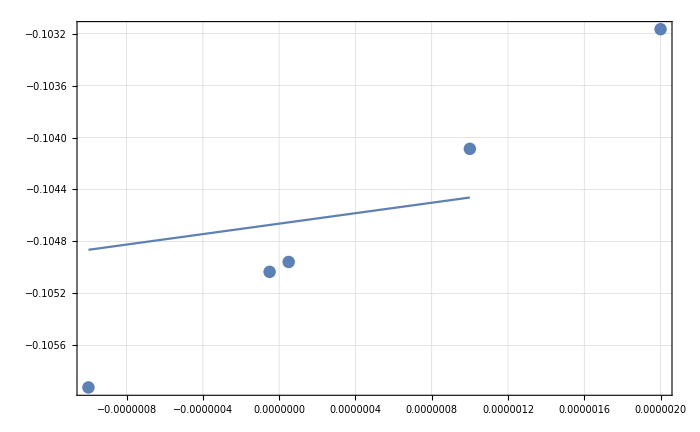

```mathematica
Show[ListPlot[listavsx],Plot[lm2[x],{x,-1*10^-6,1*10^-6}],PlotRange->All]
```

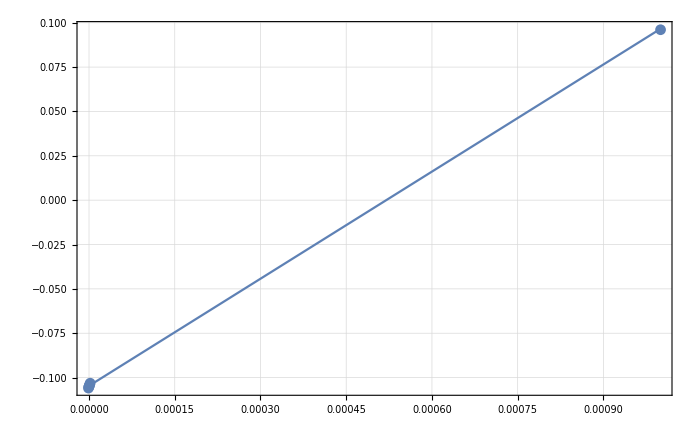

```mathematica
Show[ListPlot[listavsx2],Plot[lm2[x],{x,-1*10^-6,1*10^-3}],PlotRange->All]
```

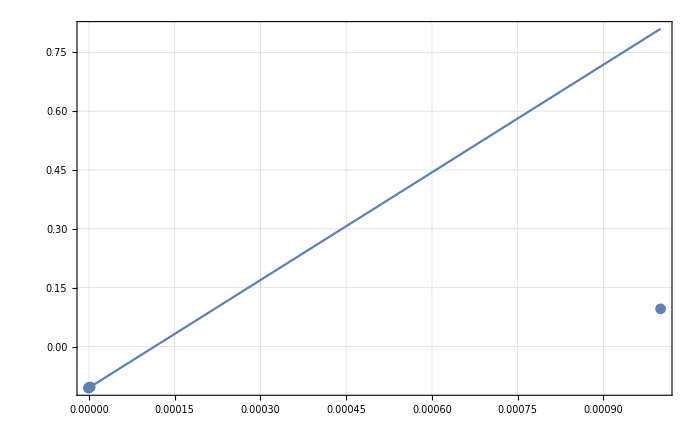

```mathematica
Show[ListPlot[listavsx2],Plot[lm[x],{x,-1*10^-6,1*10^-3}],PlotRange->All]
```

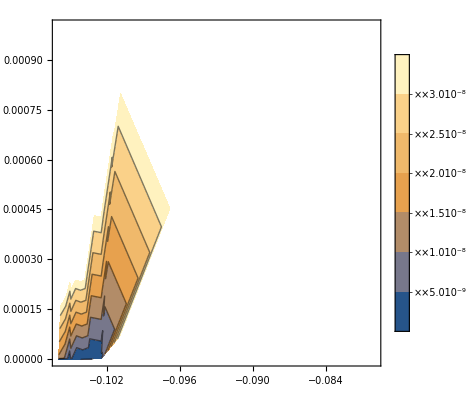

```mathematica
ListContourPlot[Flatten[test4,1],PlotLegends->Automatic]
```

```mathematica
ListContourPlot[Flatten[test4,1],PlotLegends->Automatic]
```

-Graphics-

```mathematica
?fitfunc3
```

Missing[UnknownSymbol,fitfunc3]

```mathematica
simple[a_,par_,acons_,pcons_,zcons_,th_]:=zcons*((a*Cos[th]-par*Sin[th])^2/(acons)^2+(a*Cos[th]+par*Sin[th])^2/(pcons)^2)
```

```mathematica
simple2[a_,par_,a00_,par00_,acons_,pcons_,zcons_,th_]:=zcons*(((a-a00)*Cos[th]-(par-par00)*Sin[th])^2/(acons)^2+((a-a00)*Cos[th]+(par-par00)*Sin[th])^2/(pcons)^2)
```

```mathematica
simple2Test[a_,par_,a00_,par00_,acons_,pcons_,zcons_,th_]:=zcons*(((a-a00)*Cos[th]-(par-par00)*Sin[th])^2/(acons)^2+((a-a00)*Cos[th]+(par-par00)*Sin[th])^2/(pcons)^2)
```

```mathematica
ListPlot3D[Flatten[test2,1],PlotLegends->Automatic]
```

-Graphics3D-

# Testing Aperture Shift with Det Shift

## a = -1050 APt shift only

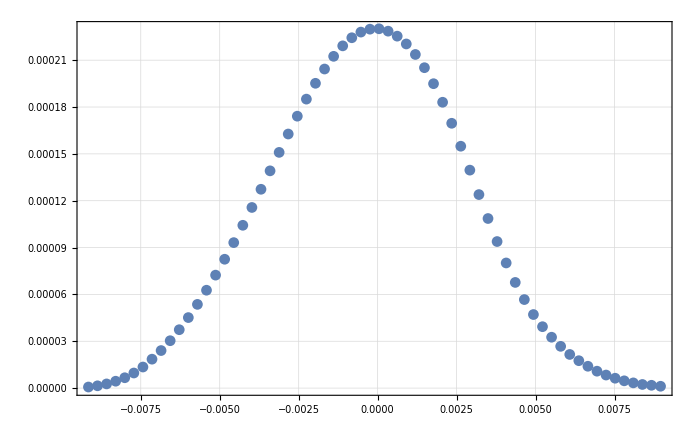

```mathematica
da0SubFileNamesa1050AptShift=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dAptShift/a-1050/"];

da0Spectruma1050AptShift=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050AptShift,1];

ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1050AptShift[[All,2]]}],PlotRange->All]
```

### a=-1050 -0.05 micro shift

```mathematica
da0SubFileNamesa1050AptdetShiftNeg=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dAptDetShift/a-1050/"];
```

```mathematica
da0Spectruma1050detAptdetShiftNeg=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050AptdetShiftNeg,1];
```

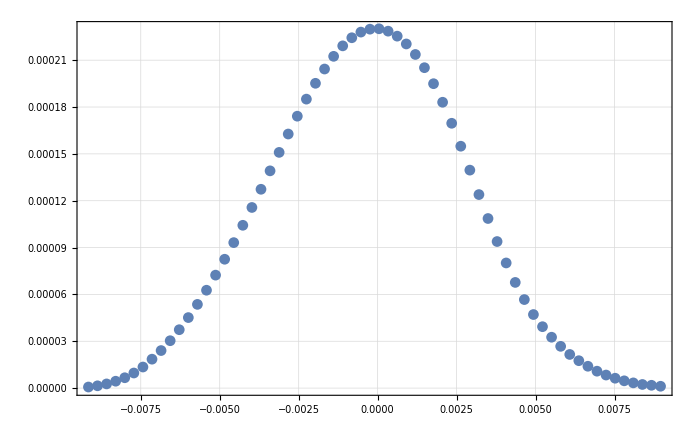

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1050detAptdetShiftNeg[[All,2]]}],PlotRange->All]
```

## a = -105 -0.05 micro shift

```mathematica
da0SubFileNamesa1051AptdetShiftNeg=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dAptDetShift/a-1051/"];
```

```mathematica
da0Spectruma1051detAptdetShiftNeg=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1051AptdetShiftNeg,1];
```

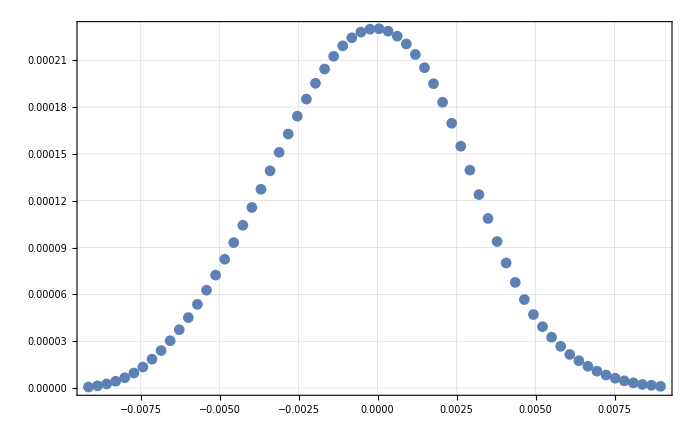

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1051detAptdetShiftNeg[[All,2]]}],PlotRange->All]
```

## a = -1050 +0.05 micro shift

```mathematica
da0SubFileNamesa1050AptdetShiftPos=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dAptDetShiftP/a-1050/"];
```

```mathematica
da0Spectruma1050detAptdetShiftPos=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050AptdetShiftPos,1];
```

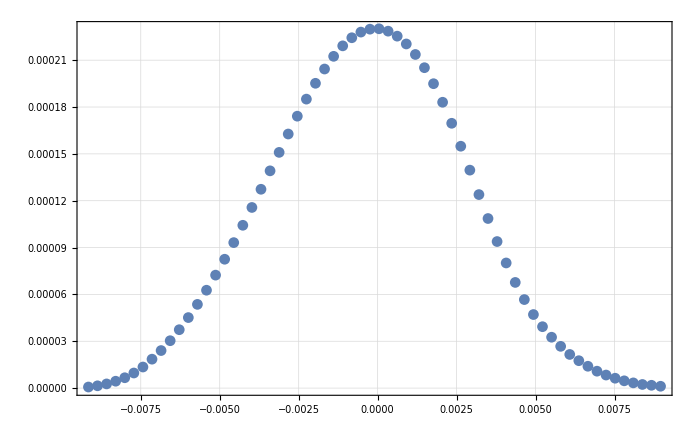

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1050detAptdetShiftPos[[All,2]]}],PlotRange->All]
```

## a = -1051 +0.05 micro shift

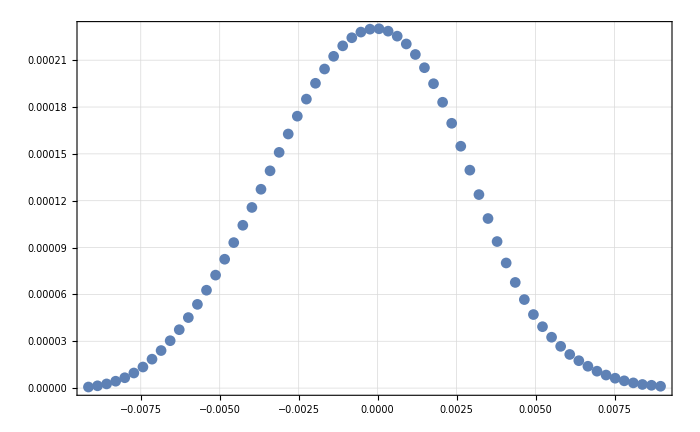

```mathematica
da0SubFileNamesa1051AptdetShiftPos=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dAptDetShiftP/a-1051/"];

da0Spectruma1051detAptdetShiftPos=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1051AptdetShiftPos,1];

ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1051detAptdetShiftPos[[All,2]]}],PlotRange->All]
```

## a = -1050 + 1 micro shift

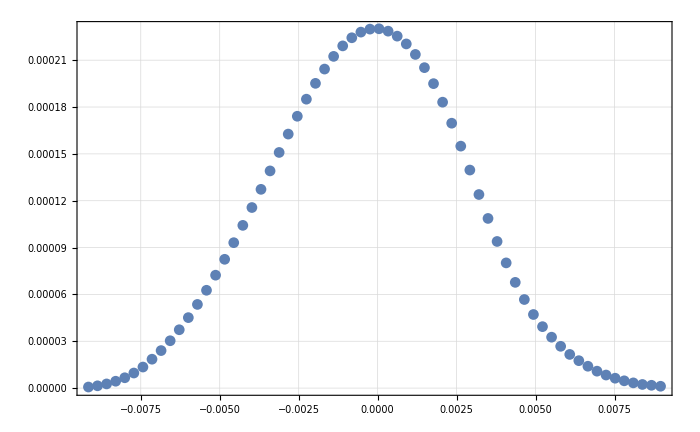

```mathematica
da0SubFileNamesa1050AptdetShiftPos1um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dAptDetShift1/a-1050/"];

da0Spectruma1050detAptdetShiftPos1um=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050AptdetShiftPos1um,1];

ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1050detAptdetShiftPos1um[[All,2]]}],PlotRange->All]
```

```mathematica
list={{da0Spectruma1050detAptdetShiftNeg[[All,2]]/Total[da0Spectruma1050detAptdetShiftNeg[[All,2]]],da0Spectruma1051detAptdetShiftNeg[[All,2]]/Total[da0Spectruma1051detAptdetShiftNeg[[All,2]]]},{da0Spectruma1050detAptdetShiftPos[[All,2]]/Total[da0Spectruma1050detAptdetShiftPos[[All,2]]],da0Spectruma1051detAptdetShiftPos[[All,2]]/Total[da0Spectruma1051detAptdetShiftPos[[All,2]]]}};
```

```mathematica
referenceNorm=da0Spectruma1050AptShift[[All,2]]/Total[da0Spectruma1050AptShift[[All,2]]];
```

```mathematica
Chi2ListPos=Table[Around[Total[(referenceNorm-list[[2,k]])^2],10^-Prec Sqrt[Total[(referenceNorm-list[[2,k]])^2 (referenceNorm^2+list[[2,k]]^2)]]],{k,1,2}];
```

```mathematica
Chi2ListNeg=Table[Around[Total[(referenceNorm-list[[1,k]])^2],10^-Prec Sqrt[Total[(referenceNorm-list[[1,k]])^2 (referenceNorm^2+list[[1,k]]^2)]]],{k,1,2}]
```

{4.6.10^-12,5.8.10^-12}

```mathematica
Chi2List=Table[Around[Total[(referenceNorm-list[[b,k]])^2],10^-Prec Sqrt[Total[(referenceNorm-list[[b,k]])^2 (referenceNorm^2+list[[b,k]]^2)]]],{b,1,2},{k,1,2}]
```

{{4.6.10^-12,5.8.10^-12},{4.6.10^-12,3.52.010^-11}}

```mathematica
dChi2List=Table[10^-Prec Sqrt[Total[(RefNormed-TransferDataListNormed[[b]])^2 (RefNormed^2+TransferDataListNormed[[b]]^2)]],{b,1,Length[ParaList]}];
```

```mathematica
Chi21um={{-0.105,Around[Total[(da0Spectruma1050detAptdetShiftPos1um[[All,2]]/Total[da0Spectruma1050detAptdetShiftPos1um[[All,2]]]-referenceNorm)^2],10^-Prec Sqrt[Total[(referenceNorm-(da0Spectruma1050detAptdetShiftPos1um[[All,2]]/Total[da0Spectruma1050detAptdetShiftPos1um[[All,2]]]))^2 (referenceNorm^2+(da0Spectruma1050detAptdetShiftPos1um[[All,2]]/Total[da0Spectruma1050detAptdetShiftPos1um[[All,2]]])^2)]]]}}
```

{{-0.105,1.480.1210^-9}}

```mathematica
Prec
```

4

```mathematica
refNoAptShift=d0Spectruma02564Bin[[All,2]]/Total[d0Spectruma02564Bin[[All,2]]];
```

```mathematica
list2={{#/Total[#]&@da0Spectruma1050detShiftMin2[[All,2]],#/Total[#]&@da0Spectruma1051detShiftMin2[[All,2]]},{#/Total[#]&@da0Spectruma1050detShift2[[All,2]],#/Total[#]&@da0Spectruma1051detShift2[[All,2]]}};
```

```mathematica
ChiSqNoAptShift=Table[Around[Total[(refNoAptShift-list2[[b,k]])^2],10^-Prec Sqrt[Total[(refNoAptShift-list2[[b,k]])^2 (refNoAptShift^2+list2[[b,k]]^2)]]],{b,1,2},{k,1,2}]
```

{{4.22.510^-11,3.22.810^-11},{4.6.10^-12,3.62.010^-11}}

```mathematica
chinoshift1um={{-0.105003,Around[Total[(da0Spectruma1050detShift[[All,2]]/Total[da0Spectruma1050detShift[[All,2]]]-refNoAptShift)^2],10^-Prec Sqrt[Total[(refNoAptShift-(da0Spectruma1050detShift[[All,2]]/Total[da0Spectruma1050detShift[[All,2]]]))^2 (refNoAptShift^2+(da0Spectruma1050detShift[[All,2]]/Total[da0Spectruma1050detShift[[All,2]]])^2)]]]}}
```

{{-0.105003,1.450.1210^-9}}

```mathematica
{circle, uptriangle, diamond, square, downtriangle} = 
  Charting`CommonDump`GraphicsOpenPlotMarkers[][[;; 5]];
```

```mathematica
Graphics`PlotMarkers[]
```

{{●,10.96},{■,8.96},{◆,10.88},{▲,10.24},{▼,10.24},{○,10.24},{□,10.24},{◇,10.24},{△,11.136},{▽,11.136}}

```mathematica
{Graphics`PlotMarkers[][[1,1]],13}
```

{●,13}

```mathematica
Chi2ListNeg
```

{4.6.10^-12,5.8.10^-12}

```mathematica
chinoshift1um
```

{{-0.105003,1.450.1210^-9}}

```mathematica
MPLColorMap["Viridis"][[2,1]]//Length
```

256

```mathematica
colorViritasArray3=Table[MPLColorMap["Viridis"][[2,1]][[Round[256/3*i]]],{i,3}]
```

{RGBColor[{0.19235719, 0.40319934, 0.55583559}],RGBColor[{0.20803045, 0.71870095, 0.4728733}],RGBColor[{0.99324789, 0.90615657, 0.1439362}]}

```mathematica
colorViritasArray2=Table[MPLColorMap["Viridis"][[2,1]][[Round[256/2*i]]],{i,2}]
```

{RGBColor[{0.12872938, 0.56326503, 0.55122927}],RGBColor[{0.99324789, 0.90615657, 0.1439362}]}

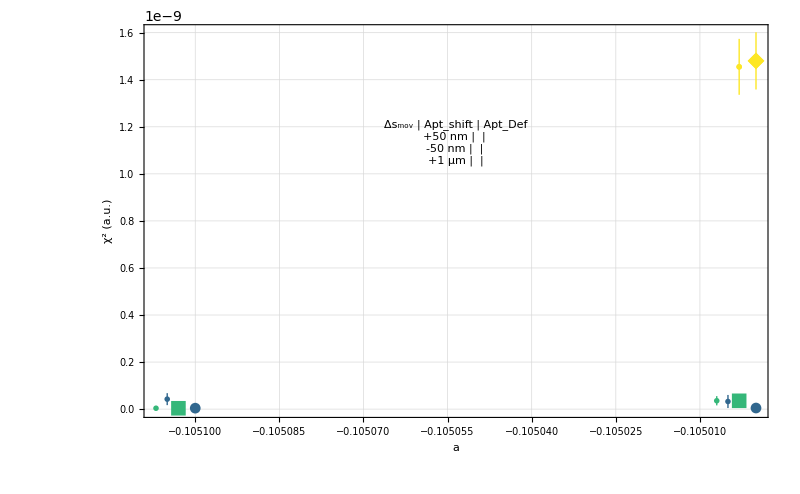

```mathematica
detMovAptEff=Show[ListPlot[Transpose[{{-0.1051,-0.105},Chi2ListNeg}],PlotStyle->colorViritasArray3[[1]],PlotMarkers->{Graphics`PlotMarkers[][[1]][[1]],11}],
ListPlot[Transpose[{{-0.105103,-0.105003},Chi2ListPos}],PlotStyle->colorViritasArray3[[2]],PlotMarkers->{Graphics`PlotMarkers[][[2]][[1]],15}],
ListPlot[Transpose[{{-0.105105,-0.105005},ChiSqNoAptShift[[1]]}],PlotStyle->colorViritasArray3[[1]],PlotMarkers->{circle,20}],
ListPlot[Transpose[{{-0.105107,-0.105007},ChiSqNoAptShift[[2]]}],PlotStyle->colorViritasArray3[[2]],PlotMarkers->{square,15}],
ListPlot[Chi21um,PlotStyle->colorViritasArray3[[3]],PlotMarkers->{Graphics`PlotMarkers[][[3,1]],17}],
ListPlot[chinoshift1um,PlotStyle->colorViritasArray3[[3]],PlotMarkers->{diamond,20}],
PlotRange->All,Epilog->Inset[Framed[
Grid[{{Style["Δs_mov",Bold,18],Style["Apt_shift",Bold,18],Style["Apt_Def",Bold,18]},
{Style["+50 nm",Bold,16],
PointLegend[{colorViritasArray3[[1]]},{""},LegendMarkers->{Graphics`PlotMarkers[][[1]][[1]],12},LabelStyle->Directive[FontSize->16,Bold],"BaseStyle"->Thickness[.1]],PointLegend[{colorViritasArray3[[1]]},{""},LegendMarkers->{circle,12},LabelStyle->Directive[FontSize->16,Bold],"BaseStyle"->Thickness[.1]]},
{Style["-50 nm",Bold,16],
PointLegend[{colorViritasArray3[[2]]},{""},LegendMarkers->{Graphics`PlotMarkers[][[2]][[1]],15},LabelStyle->Directive[FontSize->16,Bold],"BaseStyle"->Thickness[.1]],PointLegend[{colorViritasArray3[[2]]},{""},LegendMarkers->{square,15},LabelStyle->Directive[FontSize->16,Bold],"BaseStyle"->Thickness[.1]]},
{Style["+1 µm",Bold,16],
PointLegend[{colorViritasArray3[[3]]},{""},LegendMarkers->{Graphics`PlotMarkers[][[3]][[1]],15},LabelStyle->Directive[FontSize->16,Bold],"BaseStyle"->Thickness[.1]],PointLegend[{colorViritasArray3[[3]]},{""},LegendMarkers->{diamond,15},LabelStyle->Directive[FontSize->16,Bold],"BaseStyle"->Thickness[.1]]}
},Alignment->{{Left,Center,Center,Center},Automatic,Automatic}]
],Scaled[{0.5,0.7}]],ImageSize->800,FrameStyle->Directive[Thick,Black],Frame->True,GridLines->Automatic,LabelStyle->Directive[FontSize->20,Bold,Black],FrameStyle->Thick,FrameTicksStyle->Thick,FrameLabel->{"a","χ^2 (a.u.)"}]
```

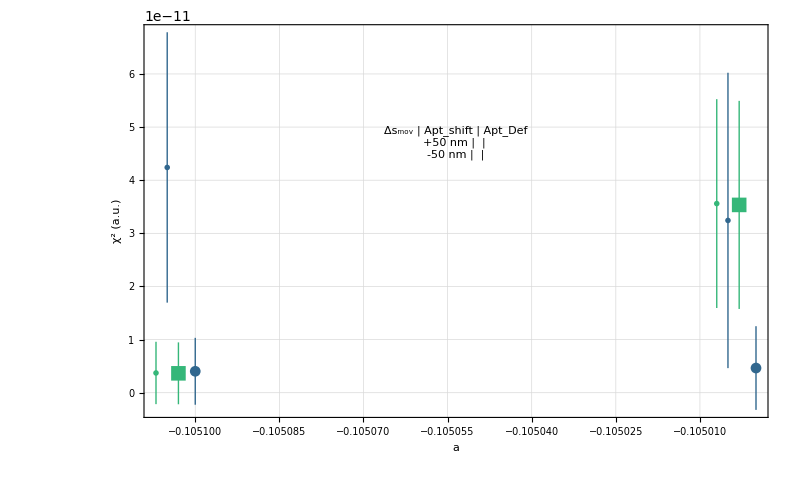

```mathematica
detMovAptEffZoomed=Show[ListPlot[Transpose[{{-0.1051,-0.105},Chi2ListNeg}],PlotStyle->colorViritasArray3[[1]],PlotMarkers->{Graphics`PlotMarkers[][[1]][[1]],11}],
ListPlot[Transpose[{{-0.105103,-0.105003},Chi2ListPos}],PlotStyle->colorViritasArray3[[2]],PlotMarkers->{Graphics`PlotMarkers[][[2]][[1]],15}],
ListPlot[Transpose[{{-0.105105,-0.105005},ChiSqNoAptShift[[1]]}],PlotStyle->colorViritasArray3[[1]],PlotMarkers->{circle,20}],
ListPlot[Transpose[{{-0.105107,-0.105007},ChiSqNoAptShift[[2]]}],PlotStyle->colorViritasArray3[[2]],PlotMarkers->{square,15}],
PlotRange->All,Epilog->Inset[Framed[
Grid[{{Style["Δs_mov",Bold,18],Style["Apt_shift",Bold,18],Style["Apt_Def",Bold,18]},
{Style["+50 nm",Bold,16],
PointLegend[{colorViritasArray3[[1]]},{""},LegendMarkers->{Graphics`PlotMarkers[][[1]][[1]],12},LabelStyle->Directive[FontSize->16,Bold],"BaseStyle"->Thickness[.1]],PointLegend[{colorViritasArray3[[1]]},{""},LegendMarkers->{circle,12},LabelStyle->Directive[FontSize->16,Bold],"BaseStyle"->Thickness[.1]]},
{Style["-50 nm",Bold,16],
PointLegend[{colorViritasArray3[[2]]},{""},LegendMarkers->{Graphics`PlotMarkers[][[2]][[1]],15},LabelStyle->Directive[FontSize->16,Bold],"BaseStyle"->Thickness[.1]],PointLegend[{colorViritasArray3[[2]]},{""},LegendMarkers->{square,15},LabelStyle->Directive[FontSize->16,Bold],"BaseStyle"->Thickness[.1]]}
},Alignment->{{Left,Center,Center,Center},Automatic,Automatic}]
],Scaled[{0.5,0.7}]],ImageSize->800,FrameStyle->Directive[Thick,Black],Frame->True,GridLines->Automatic,LabelStyle->Directive[FontSize->20,Bold,Black],FrameStyle->Thick,FrameTicksStyle->Thick,FrameLabel->{"a","χ^2 (a.u.)"}]
```

```mathematica
Export["~/Desktop/Images/detMovAptEffZoomed.svg",detMovAptEffZoomed];Export["~/Desktop/Images/detMovAptEffZoomed.png",detMovAptEffZoomed];Export["~/Desktop/Images/detMovAptEff.svg",detMovAptEff];Export["~/Desktop/Images/detMovAptEff.png",detMovAptEff];
```

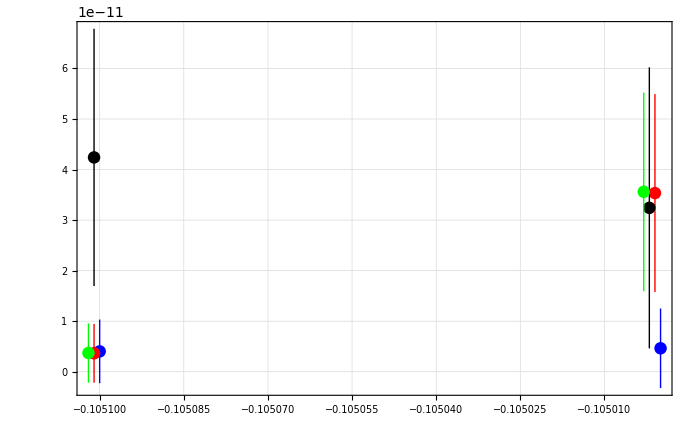

```mathematica
Show[ListPlot[Transpose[{{-0.1051,-0.105},Chi2List[[1]]}],PlotStyle->Blue],ListPlot[Transpose[{{-0.105101,-0.105001},Chi2List[[2]]}],PlotStyle->Red],ListPlot[Transpose[{{-0.105101,-0.105002},ChiSqNoAptShift[[1]]}],PlotStyle->Black],ListPlot[Transpose[{{-0.105102,-0.105003},ChiSqNoAptShift[[2]]}],PlotStyle->Green],PlotRange->All,Epilog->Inset[Framed[Column[{PointLegend[{Blue},{"50nm Neg AptShift"},LabelStyle->Directive[FontSize->20,Bold]],PointLegend[{Red},{"50nm Pos AptShift"},LabelStyle->Directive[FontSize->20,Bold]],
PointLegend[{Black},{"50nm Neg"},LabelStyle->Directive[FontSize->20,Bold]],
PointLegend[{Green},{"50nm"},LabelStyle->Directive[FontSize->20,Bold]]}]],Scaled[{0.5,0.7}]]]
```

```mathematica
|
```

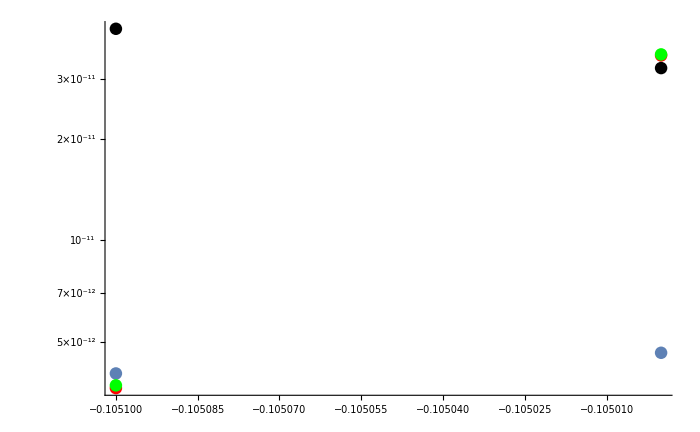

```mathematica
Show[ListLogPlot[Transpose[{{-0.1051,-0.105},Chi2List[[1]]}]],ListLogPlot[Transpose[{{-0.1051,-0.105},Chi2List[[2]]}],PlotStyle->Red],ListLogPlot[Transpose[{{-0.1051,-0.105},ChiSqNoAptShift[[1]]}],PlotStyle->Black],ListLogPlot[Transpose[{{-0.1051,-0.105},ChiSqNoAptShift[[2]]}],PlotStyle->Green],PlotRange->All]
```

```mathematica
Chi2InterPos=Total[(da0Spectruma1050detAptdetShiftPos[[All,2]]/Total[da0Spectruma1050detAptdetShiftPos[[All,2]]]-da0Spectruma1051detAptdetShiftPos[[All,2]]/Total[da0Spectruma1051detAptdetShiftPos[[All,2]]])^2]
```

1.66021×10^-11

```mathematica
Chi2InterNeg=Total[(da0Spectruma1050detAptdetShiftNeg[[All,2]]/Total[da0Spectruma1050detAptdetShiftNeg[[All,2]]]-da0Spectruma1051detAptdetShiftNeg[[All,2]]/Total[da0Spectruma1051detAptdetShiftNeg[[All,2]]])^2]
```

1.66319×10^-11

```mathematica
Chi21umPos=Total[(RefNorm-da0Spectruma1050detAptdetShiftPos1um[[All,2]]/Total[da0Spectruma1050detAptdetShiftPos1um[[All,2]]])^2]
```

0.0000150392

```mathematica
(-0.1051+0.105)/-0.105
```

0.000952381

```mathematica
ListPlot[{{-0.05,Chi2InterNeg},{0.05,Chi2InterPos}}]
```

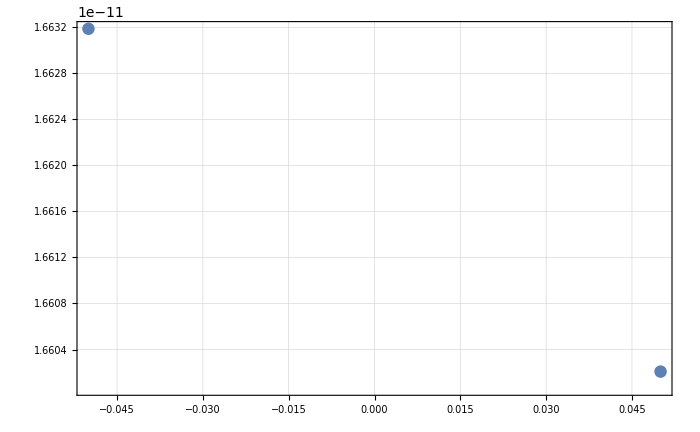
```mathematica
-Graphics-a = -1050 + 1 micro shift
```

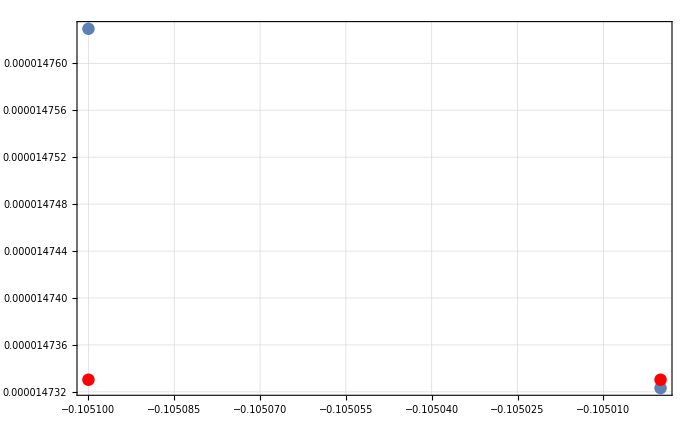

```mathematica
Chi2List
```

{{0.0000147629,0.0000147323},{0.0000147629,0.0000147629}}

```mathematica
Sigma=(If[#1==0,10000,10^-Prec #1]&)/@RefNorm;
```

```mathematica
RefTransferDel=Delete[RefTransfer,NonZeroPos];RefNorm=Total[RefTransferDel];TransferDataListDel=Table[Delete[TransferDataList[[para]],NonZeroPos],{para,Length[ParaList]}];bMin=Min[ParaList]-0.0005;bMax=Max[ParaList]+0.0005;RefNormed=RefTransferDel/RefNorm;Sigma=(If[#1==0,10000,10^-Prec #1]&)/@RefNormed;TransferDataListNormed=(#1/Total[#1]&)/@TransferDataListDel;Chi2List=Table[Total[(RefNormed-TransferDataListNormed[[b]])^2],{b,1,Length[ParaList]}];dChi2List=Table[10^-Prec Sqrt[Total[(RefNormed-TransferDataListNormed[[b]])^2 (RefNormed^2+TransferDataListNormed[[b]]^2)]],{b,1,Length[ParaList]}];errorplotdata=Transpose[{ParaList,Table[10^9 Around[Chi2List[[b]],dChi2List[[b]]],{b,1,Length[ParaList]}]}];
fitfunc[x_,x0_,f_,g_]:=f+g (x-x0)^2;fitresult=NonlinearModelFit[Transpose[{ParaList,Chi2List}],{fitfunc[b,b0,yoffset,scale],bMin<b0<bMax&&0.<scale<1/10&&0.<yoffset≤Min[Chi2List]},
```

# 10mm Invi

## a=0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_1064R1/a-1050/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma01064R1=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
xStart=-0.0125;
xEnd=0.0125;
yStart=-0.025;
yEnd=0.025;
xyBins1064R1=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf1064R1=BinCenters[xyBins1064R1];
```

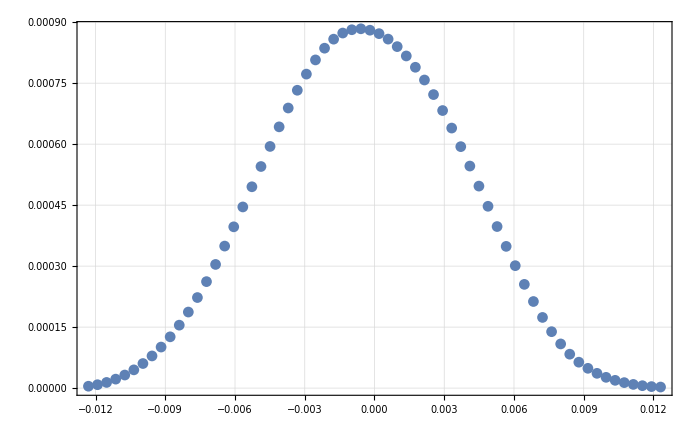

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalf1064R1[[All,1]],d0Spectruma01064R1[[All,2]]}],PlotRange->All]]
```

## a = -1060 + 1 micro shift 10mm

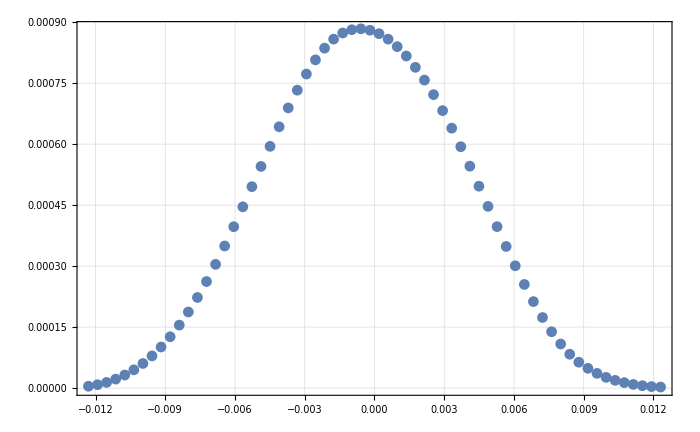

```mathematica
da0SubFileNamesa106010mmApt1umShiftFN=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dDetShift_10mmApt1um/a-1060/"];

da0SubFileNamesa106010mmApt1umShift=Flatten[Import[#,"Table"]&/@da0SubFileNamesa106010mmApt1umShiftFN,1];

ListPlot[Transpose[{XYBinCentersYHalf1064R1[[All,1]],da0SubFileNamesa106010mmApt1umShift[[All,2]]}],PlotRange->All]
```

```mathematica
Chi2Inter10mm=Total[(da0SubFileNamesa106010mmApt1umShift[[All,2]]/Total[da0SubFileNamesa106010mmApt1umShift[[All,2]]]-d0Spectruma01064R1[[All,2]]/Total[d0Spectruma01064R1[[All,2]]])^2]
```

2.83381×10^-9

## a = -1040 + 1 micro shift 10mm

```mathematica
da0SubFileNamesa104010mmApt1umShiftFN=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dDetShift_10mmApt1um/a-1040/"];
da0SubFileNamesa104010mmApt1umShift=Flatten[Import[#,"Table"]&/@da0SubFileNamesa104010mmApt1umShiftFN,1];
```

```mathematica
da0SubFileNamesa104010mmApt1umShift//Length
```

64

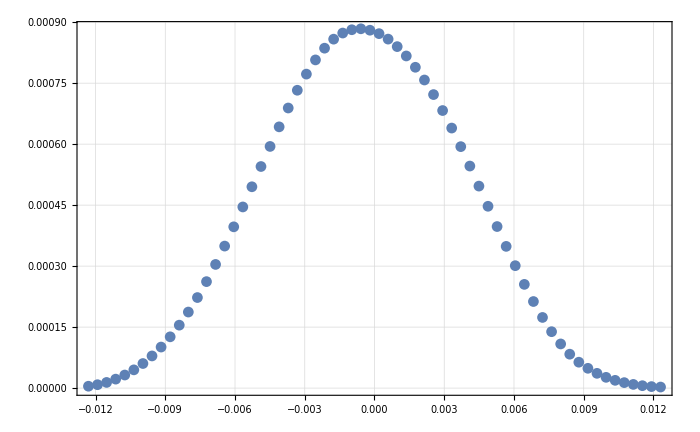

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf1064R1[[All,1]],da0SubFileNamesa104010mmApt1umShift[[All,2]]}],PlotRange->All]
```

```mathematica
d0Spectruma01064R1[[All,2]][[;;40]]//Length
```

40

```mathematica
Chi2Inter10mm1040=Total[(da0SubFileNamesa104010mmApt1umShift[[All,2]]/Total[da0SubFileNamesa104010mmApt1umShift[[All,2]]]-d0Spectruma01064R1[[All,2]]/Total[d0Spectruma01064R1[[All,2]]])^2]
```

1.18641×10^-11

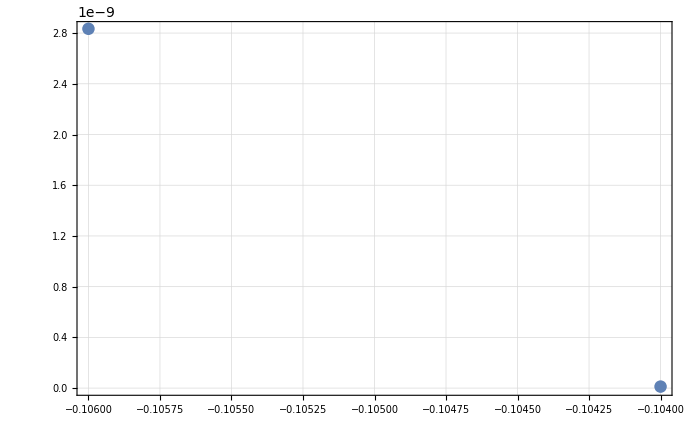

```mathematica
ListPlot[{{-0.106,2.8338055571209415*^-9},{-0.104,1.1864138776446946*^-11}}]
```

## a = -1045+ 1 micro shift 10mm

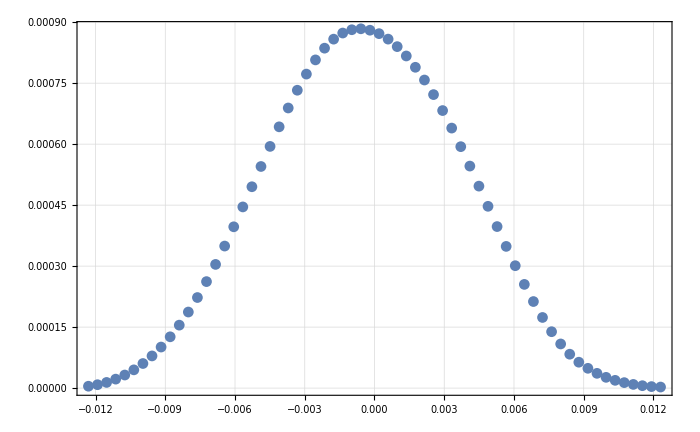

```mathematica
da0SubFileNamesa104510mmApt1umShiftFN=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dDetShift_10mmApt1um/a-1045/"];

da0SubFileNamesa104510mmApt1umShift=Flatten[Import[#,"Table"]&/@da0SubFileNamesa104510mmApt1umShiftFN,1];

ListPlot[Transpose[{XYBinCentersYHalf1064R1[[All,1]],da0SubFileNamesa104510mmApt1umShift[[All,2]]}],PlotRange->All]
```

## a = -1055+ 1 micro shift 10mm

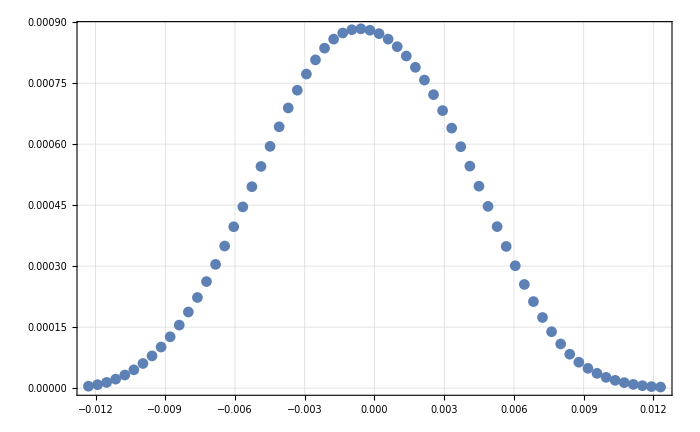

```mathematica
da0SubFileNamesa105510mmApt1umShiftFN=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dDetShift_10mmApt1um/a-1055/"];

da0SubFileNamesa105510mmApt1umShift=Flatten[Import[#,"Table"]&/@da0SubFileNamesa105510mmApt1umShiftFN,1];

ListPlot[Transpose[{XYBinCentersYHalf1064R1[[All,1]],da0SubFileNamesa105510mmApt1umShift[[All,2]]}],PlotRange->All]
```

## a = -1050+ 1 micro shift 10mm

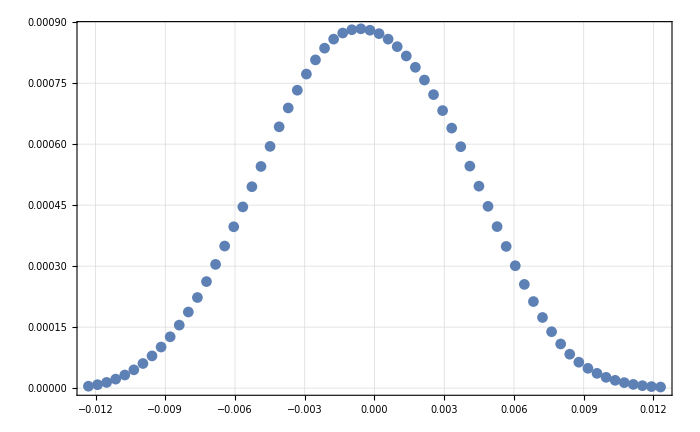

```mathematica
da0SubFileNamesa105010mmApt1umShiftFN=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dDetShift_10mmApt1um/a-1050/"];

da0SubFileNamesa105010mmApt1umShift=Flatten[Import[#,"Table"]&/@da0SubFileNamesa105010mmApt1umShiftFN,1];

ListPlot[Transpose[{XYBinCentersYHalf1064R1[[All,1]],da0SubFileNamesa105010mmApt1umShift[[All,2]]}],PlotRange->All]
```

## a = -1030+ 1 micro shift 10mm

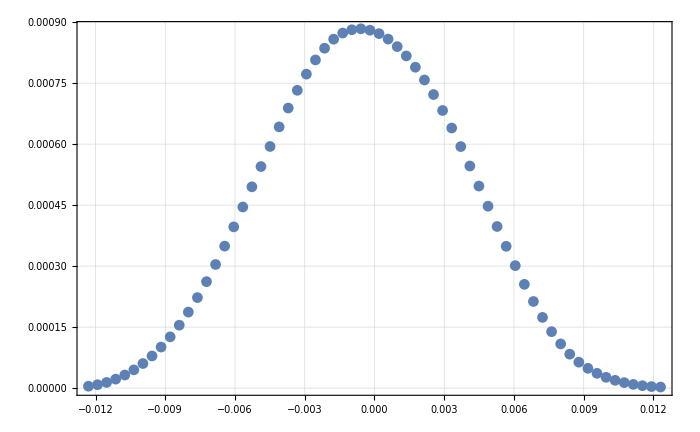

```mathematica
da0SubFileNamesa103010mmApt1umShiftFN=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dDetShift_10mmApt1um/a-1030/"];

da0SubFileNamesa103010mmApt1umShift=Flatten[Import[#,"Table"]&/@da0SubFileNamesa103010mmApt1umShiftFN,1];

ListPlot[Transpose[{XYBinCentersYHalf1064R1[[All,1]],da0SubFileNamesa103010mmApt1umShift[[All,2]]}],PlotRange->All]
```

## a = -1025+ 1 micro shift 10mm

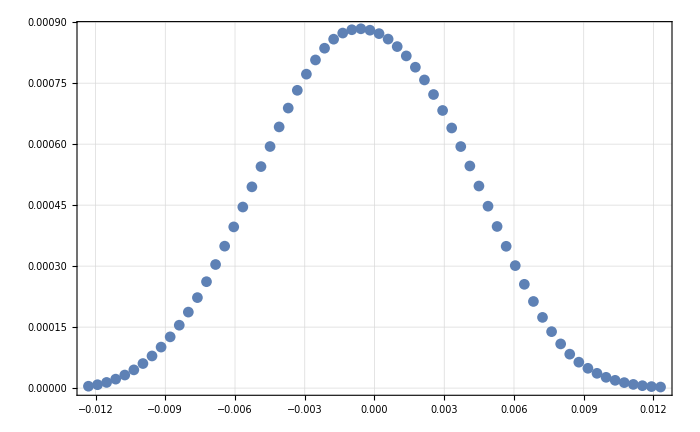

```mathematica
da0SubFileNamesa102510mmApt1umShiftFN=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dDetShift_10mmApt1um/a-1025/"];

da0SubFileNamesa102510mmApt1umShift=Flatten[Import[#,"Table"]&/@da0SubFileNamesa102510mmApt1umShiftFN,1];

ListPlot[Transpose[{XYBinCentersYHalf1064R1[[All,1]],da0SubFileNamesa102510mmApt1umShift[[All,2]]}],PlotRange->All]
```

```mathematica
da0SubFileNamesd0Spectruma01064R1=Interpolation[Transpose[{XYBinCentersYHalf1064R1[[All,1]],#/Total[#]&@d0Spectruma01064R1[[All,2]]}]];
```

```mathematica
da0SubFileNamesa102510mmApt1umShiftInter=Interpolation[Transpose[{XYBinCentersYHalf1064R1[[All,1]],#/Total[#]&@da0SubFileNamesa102510mmApt1umShift[[All,2]]}]];
dda0SubFileNamesa103010mmApt1umShiftInter=Interpolation[Transpose[{XYBinCentersYHalf1064R1[[All,1]],#/Total[#]&@da0SubFileNamesa103010mmApt1umShift[[All,2]]}]];
da0SubFileNamesa104010mmApt1umShiftInter=Interpolation[Transpose[{XYBinCentersYHalf1064R1[[All,1]],#/Total[#]&@da0SubFileNamesa104010mmApt1umShift[[All,2]]}]];
da0SubFileNamesa104510mmApt1umShiftInter=Interpolation[Transpose[{XYBinCentersYHalf1064R1[[All,1]],#/Total[#]&@da0SubFileNamesa104510mmApt1umShift[[All,2]]}]];
da0SubFileNamesa105010mmApt1umShiftInter=Interpolation[Transpose[{XYBinCentersYHalf1064R1[[All,1]],#/Total[#]&@da0SubFileNamesa105010mmApt1umShift[[All,2]]}]];
da0SubFileNamesa105510mmApt1umShiftInter=Interpolation[Transpose[{XYBinCentersYHalf1064R1[[All,1]],#/Total[#]&@da0SubFileNamesa105510mmApt1umShift[[All,2]]}]];
da0SubFileNamesa106010mmApt1umShiftInter=Interpolation[Transpose[{XYBinCentersYHalf1064R1[[All,1]],#/Total[#]&@da0SubFileNamesa106010mmApt1umShift[[All,2]]}]];
```

InterpolatingFunction::dmval: Input value {-0.0124995} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

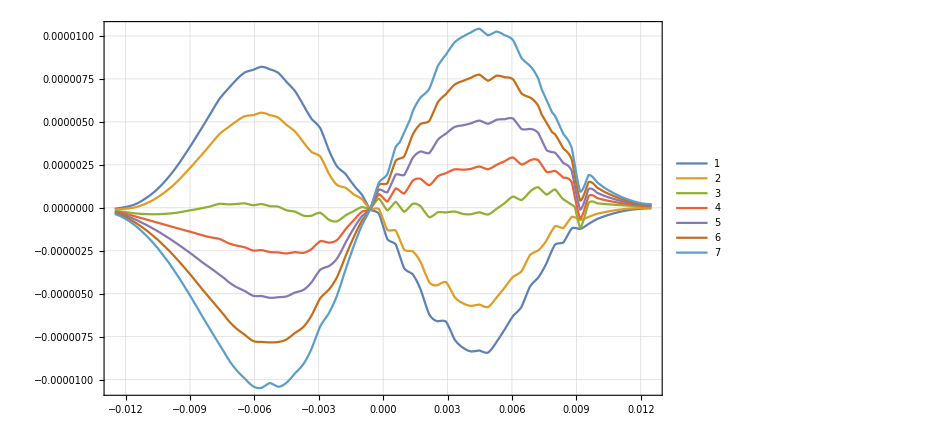

```mathematica
Plot[{
da0SubFileNamesd0Spectruma01064R1[x]-da0SubFileNamesa102510mmApt1umShiftInter[x],
da0SubFileNamesd0Spectruma01064R1[x]-dda0SubFileNamesa103010mmApt1umShiftInter[x],
da0SubFileNamesd0Spectruma01064R1[x]-da0SubFileNamesa104010mmApt1umShiftInter[x],
da0SubFileNamesd0Spectruma01064R1[x]-da0SubFileNamesa104510mmApt1umShiftInter[x],
da0SubFileNamesd0Spectruma01064R1[x]-da0SubFileNamesa105010mmApt1umShiftInter[x],
da0SubFileNamesd0Spectruma01064R1[x]-da0SubFileNamesa105510mmApt1umShiftInter[x],
da0SubFileNamesd0Spectruma01064R1[x]-da0SubFileNamesa106010mmApt1umShiftInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
detShiftMinList={#/Total[#]&@da0SubFileNamesa102510mmApt1umShift[[All,2]],#/Total[#]&@da0SubFileNamesa103010mmApt1umShift[[All,2]],#/Total[#]&@da0SubFileNamesa104010mmApt1umShift[[All,2]],#/Total[#]&@da0SubFileNamesa104510mmApt1umShift[[All,2]],#/Total[#]&@da0SubFileNamesa105010mmApt1umShift[[All,2]],#/Total[#]&@da0SubFileNamesa105510mmApt1umShift[[All,2]],#/Total[#]&@da0SubFileNamesa106010mmApt1umShift[[All,2]]};
```

```mathematica
bList={-0.1025,-0.103,-0.104,-.1045,-.1050,-.1055,-0.1060}
```

{-0.1025,-0.103,-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
detShiftMinList//Length
```

7

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

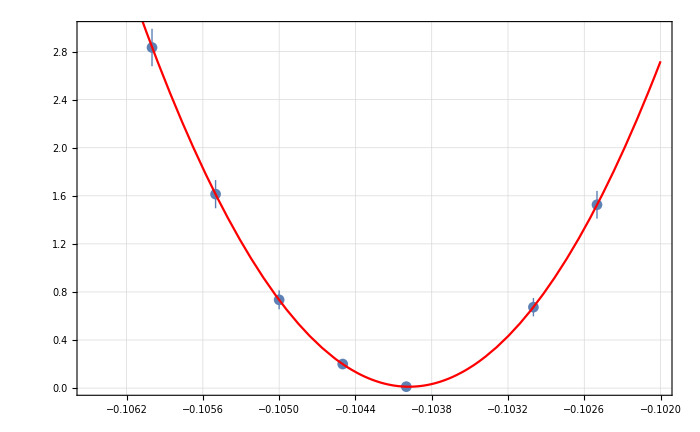
{{{1.52548×10^-9,6.73255×10^-10,1.18641×10^-11,2.00041×10^-10,7.34417×10^-10,1.61364×10^-9,2.83381×10^-9},{1.1524×10^-10,7.66647×10^-11,8.55524×10^-12,4.05091×10^-11,7.87968×10^-11,1.1737×10^-10,1.55768×10^-10}},a0 =  | -0.103979
FittedModel[1.15747×10^-11+0.000691631 (0.103979+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.103979 | 0.0000243985 | -4261.67 | 1.819×10^-14
scale | 0.000691631 | 0.000025183 | 27.4642 | 0.0000104533
yoffset | 1.15747×10^-11 | 8.44608×10^-12 | 1.37043 | 0.242428 | 
 | DF | SS | MS
Model | 3 | 885.511 | 295.17
Error | 4 | 0.00141929 | 0.000354822
Uncorrected Total | 7 | 885.512 | 
Corrected Total | 6 | 834.857 |  | ,-Graphics-}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma01064R1[[All,2]],detShiftMinList,bList, 4]
```

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)
```

-0.009730.00023

```mathematica
0.9
```

```mathematica
0.1
```

```mathematica
?TransferToRefParableFitForProtons0Del
```

```mathematica
rAInvest[[2]]
```

a0 =  | -0.105034
FittedModel[2.59566×10^-11+0.00167047 (0.105034+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105034 | 0.0000217032 | -4839.58 | 4.26958×10^-8
scale | 0.00167047 | 0.000100439 | 16.6317 | 0.00359568
yoffset | 2.59566×10^-11 | 2.67619×10^-11 | 0.969908 | 0.434408 | 
 | DF | SS | MS
Model | 3 | 367.59 | 122.53
Error | 2 | 0.0124125 | 0.00620627
Uncorrected Total | 5 | 367.602 | 
Corrected Total | 4 | 286.078 |  |

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/10^-6
```

9427.551.

```mathematica
9000*50*10^-9.
```

0.00045

```mathematica
list={#/Total[#]&@da0Spectruma1050detShiftMin[[All,2]],#/Total[#]&@da0Spectruma1050detShiftMin2[[All,2]],#/Total[#]&@da0Spectruma1050detShift2[[All,2]],#/Total[#]&@da0Spectruma1050detShift[[All,2]]};
```

```mathematica
bl={-1*10^-6.,-0.05*10^-6,0.05*10^-6,1*10^-6.}
```

{-1.×10^-6,-5.×10^-8,5.×10^-8,1.×10^-6}

```mathematica
Max[bl]
```

1.×10^-6

```mathematica
RefNorm
```

```mathematica
Sigma=(If[#1==0,10000,10^-4 #1]&)/@RefNorm;
```

```mathematica
TransferDataListNormed=(#1/Total[#1]&)/@list;
```

```mathematica
Chi2List=Table[Total[(RefNorm-TransferDataListNormed⟦b⟧)^2],{b,1,Length[bl]}];
```

```mathematica
dChi2List=Table[10^-4 √Total[(RefNorm-TransferDataListNormed⟦b⟧)^2 (RefNorm^2+TransferDataListNormed⟦b⟧^2)],{b,1,Length[bl]}];
```

```mathematica
errorplotdata=Transpose[{bl,Table[10^9 Around[Chi2List⟦b⟧,dChi2List⟦b⟧],{b,1,Length[bl]}]}];
```

```mathematica
fitfunc[x_,x0_,f_,g_]:=f+g (x-x0)^2;
```

```mathematica
Clear[b]
```

```mathematica
5./10^4
```

0.0005

```mathematica
Min[Chi2List]
```

3.71906×10^-12

```mathematica
Transpose[{bl,Chi2List}]
```

{{-1.×10^-6,1.49644×10^-9},{-5.×10^-8,4.24029×10^-11},{5.×10^-8,3.71906×10^-12},{1.×10^-6,1.45484×10^-9}}

```mathematica
blist2D={{-0.104,-.1045,-.1051,-.1055,-0.1060},{-1*10^-6,-0.05*10^-6,0,0.05*10^-6,1*10^-6}}
```

{{-0.104,-0.1045,-0.1051,-0.1055,-0.106},{-1/1000000,-5.×10^-8,0,5.×10^-8,1/1000000}}

```mathematica
XDetDataList2D={{#/Total[#]&@da0Spectruma1040detShiftMin[[All,2]],#/Total[#]&@da0Spectruma1040detShiftMin2[[All,2]],#/Total[#]&@da0Spectruma1040[[All,2]],#/Total[#]&@da0Spectruma1040detShift2[[All,2]],#/Total[#]&@da0Spectruma1040detShift[[All,2]]},{#/Total[#]&@da0Spectruma1045detShiftMin[[All,2]],#/Total[#]&@da0Spectruma1045detShiftMin2[[All,2]],#/Total[#]&@da0Spectruma1045[[All,2]],#/Total[#]&@da0Spectruma1045detShift2[[All,2]],#/Total[#]&@da0Spectruma1045detShift[[All,2]]},
{#/Total[#]&@da0Spectruma1051detShiftMin[[All,2]],#/Total[#]&@da0Spectruma1051detShiftMin2[[All,2]],#/Total[#]&@da0Spectruma1051[[All,2]],#/Total[#]&@da0Spectruma1051detShift2[[All,2]],#/Total[#]&@da0Spectruma1051detShift[[All,2]]},
{#/Total[#]&@da0Spectruma1055detShiftMin[[All,2]],#/Total[#]&@da0Spectruma1055detShiftMin2[[All,2]],#/Total[#]&@da0Spectruma1055[[All,2]],#/Total[#]&@da0Spectruma1055detShift2[[All,2]],#/Total[#]&@da0Spectruma1055detShift[[All,2]]},
{#/Total[#]&@da0Spectruma1060detShiftMin[[All,2]],#/Total[#]&@da0Spectruma1060detShiftMin2[[All,2]],#/Total[#]&@da0Spectruma1060[[All,2]],#/Total[#]&@da0Spectruma1060detShift2[[All,2]],#/Total[#]&@da0Spectruma1060detShift[[All,2]]}
};
```

```mathematica
RefNorm=d0Spectruma02564Bin[[All,2]]/Total[d0Spectruma02564Bin[[All,2]]];
```

```mathematica
Chi2List2D=Table[Total[(RefNorm-XDetDataList2D⟦b,par⟧)^2],{b,Length[blist2D[[1]]]},{par,Length[blist2D[[2]]]}];
```

```mathematica
plotChi2List2D=Table[{blist2D[[1,b]],blist2D[[2,par]],Total[(RefNorm-XDetDataList2D⟦b,par⟧)^2]},{b,Length[blist2D[[1]]]},{par,Length[blist2D[[2]]]}];
```

```mathematica
dChi2List=Table[10^-4 √Total[(RefNorm-XDetDataList2D⟦b,para⟧)^2 (RefNorm^2+XDetDataList2D⟦b,para⟧^2)],{b,Length[blist2D[[1]]]},{para,Length[blist2D[[2]]]}];
```

```mathematica
fitfunc[a_,a0_,par_,par0_,ascale_,pscale_,offset_]:=offset+(a-a0)^2/ascale^2+(par-par0)^2/pscale^2
```

```mathematica
fitfunc2[a_,a0_,par_,par0_,ascale_,pscale_]:=(a-a0)^2/ascale^2+(par-par0)^2/pscale^2
```

```mathematica
fit2=NonlinearModelFit[Flatten[plotChi2List2D,1],{fitfunc2[a,a00,par,par0,ascale,pscale],-0.106<a00<-0.104,-1<par0<1,1*10^-10<ascale<100,1*10^-10<pscale<10},{{a00,-0.10500},{par0,Min[blist2D[[2]]]},{ascale,40},{pscale,1}},{a,par},Method->"NMinimize",Weights->1/Flatten[dChi2List,1]^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

FittedModel[0.000512509 (0.104915+a)^2+0.0101317 (-0.0000866746+par)^2]

```mathematica
?fitfunc2
```

```mathematica
fit=NonlinearModelFit[Flatten[plotChi2List2D,1],{fitfunc[a,a00,par,par0,ascale,pscale,offset],-0.106<a00<-0.104,-1*10^-3<par0<1*10^-3,1*10^-10<ascale<10,1*10^-10<pscale<10,-1<offset<1},{{a00,-0.10500},{par0,Min[blist2D[[2]]]},{ascale,1},{pscale,1},{offset,1*10^-9}},{a,par},Method->"NMinimize",Weights->1/Flatten[dChi2List,1]^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

FittedModel[2.4838×10^-11+1.67521×10^-10 (0.10483+a)^2+0.01 (-0.000110176+par)^2]

```mathematica
fit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a00 | -0.10483 | 113.984 | -0.000919695 | 0.999284
par0 | 0.000110176 | 0.0179013 | 0.00615462 | 0.99521
ascale | 77262. | 8.28783×10^-7 | 9.32235×10^10 | 4.96419×10^-106
pscale | 10. | 0.000837276 | 11943.5 | 4.16663×10^-37
offset | 2.4838×10^-11 | 3.94302×10^-8 | 0.000629924 | 0.99951

```mathematica
fit2["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a00 | -0.104915 | 0.0000299767 | -3499.88 | 4.94137×10^-62
par0 | 0.0000866746 | 0.00151444 | 0.0572322 | 0.954901
ascale | 44.1722 | 1.19301 | 37.0257 | 1.30041×10^-20
pscale | 9.93479 | 173.843 | 0.0571479 | 0.954968

```mathematica
(-0.10491473819433589+0.105)/-0.105
```

-0.000812017

```mathematica
(-0.10491340539392745+0.105)/-0.105
```

-0.000824711

```mathematica
fitChiSqCalc[dataSet_,weights_,fit_]:=Block[{nObs,nParams,r,chiSq},nObs=Length[dataSet];nParams=Length[fit["BestFitParameters"]];r=fit["FitResiduals"];
chiSq=r.Inverse[DiagonalMatrix[weights^2]].r/(nObs-nParams)
]
```

```mathematica
fitChiSqCalc[Flatten[plotChi2List2D,1],Flatten[dChi2List,1],fit]
```

451.032

```mathematica
Plot3D[fit[a,par],{a,-0.104,-0.106},{par,-1*10^-6,1*10^-6}]
```

-Graphics3D-

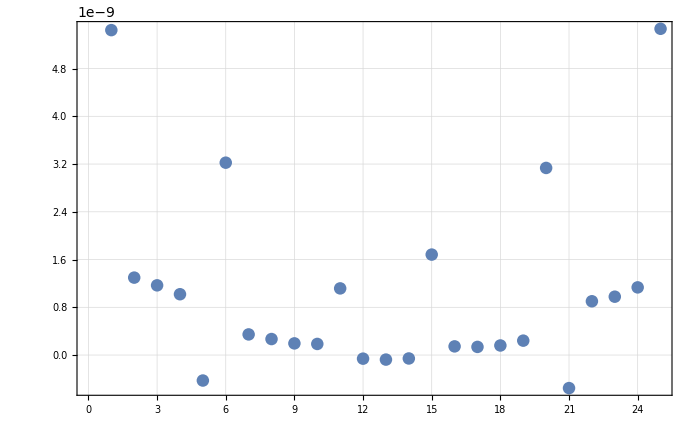

```mathematica
ListPlot[fit2["FitResiduals"]]
```

```mathematica
?fitfunc
```

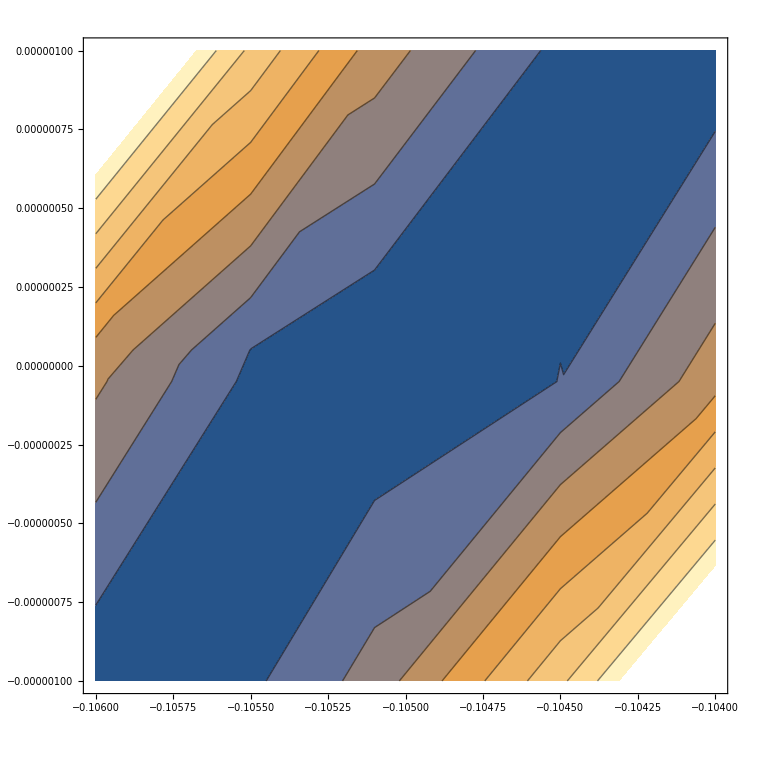

```mathematica
ListContourPlot[Flatten[plotChi2List2D,1]]
```

```mathematica
Show[ListPlot3D[Flatten[plotChi2List2D,1]]]
```

-Graphics3D-

```mathematica
blist2D2={{-0.104,-.1045,-.1051,-.1055,-0.1060},{-0.05*10^-6,0,0.05*10^-6}}
```

{{-0.104,-0.1045,-0.1051,-0.1055,-0.106},{-5.×10^-8,0,5.×10^-8}}

```mathematica
XDetDataList2D2={{#/Total[#]&@da0Spectruma1040detShiftMin2[[All,2]],#/Total[#]&@da0Spectruma1040[[All,2]],#/Total[#]&@da0Spectruma1040detShift2[[All,2]]},{#/Total[#]&@da0Spectruma1045detShiftMin2[[All,2]],#/Total[#]&@da0Spectruma1045[[All,2]],#/Total[#]&@da0Spectruma1045detShift2[[All,2]]},
{#/Total[#]&@da0Spectruma1051detShiftMin2[[All,2]],#/Total[#]&@da0Spectruma1051[[All,2]],#/Total[#]&@da0Spectruma1051detShift2[[All,2]]},
{#/Total[#]&@da0Spectruma1055detShiftMin2[[All,2]],#/Total[#]&@da0Spectruma1055[[All,2]],#/Total[#]&@da0Spectruma1055detShift2[[All,2]]},
{#/Total[#]&@da0Spectruma1060detShiftMin2[[All,2]],#/Total[#]&@da0Spectruma1060[[All,2]],#/Total[#]&@da0Spectruma1060detShift2[[All,2]]}
};
```

```mathematica
RefNorm=d0Spectruma02564Bin[[All,2]]/Total[d0Spectruma02564Bin[[All,2]]];
```

```mathematica
Chi2List2D2=Table[Total[(RefNorm-XDetDataList2D2⟦b,par⟧)^2],{b,Length[blist2D2[[1]]]},{par,Length[blist2D2[[2]]]}];
```

```mathematica
plotChi2List2D2=Table[{blist2D2[[1,b]],blist2D2[[2,par]],Total[(RefNorm-XDetDataList2D2⟦b,par⟧)^2]},{b,Length[blist2D2[[1]]]},{par,Length[blist2D2[[2]]]}];
```

```mathematica
dChi2List2=Table[10^-4 √Total[(RefNorm-XDetDataList2D2⟦b,para⟧)^2 (RefNorm^2+XDetDataList2D2⟦b,para⟧^2)],{b,Length[blist2D2[[1]]]},{para,Length[blist2D2[[2]]]}];
```

```mathematica
fitfunc[a_,a0_,par_,par0_,ascale_,pscale_,offset_]:=offset+(a-a0)^2/ascale^2+(par-par0)^2/pscale^2
```

```mathematica
fitfunc2[a_,a0_,par_,par0_,ascale_,pscale_]:=(a-a0)^2/ascale^2+(par-par0)^2/pscale^2
```

```mathematica
plotChi2List2D2
```

{{{-0.104,-1/1000000,1.80357×10^-9},{-0.104,0,1.6742×10^-9},{-0.104,1/1000000,1.52523×10^-9}},{{-0.1045,-1/1000000,5.08869×10^-10},{-0.1045,0,4.3137×10^-10},{-0.1045,1/1000000,3.58672×10^-10}},{{-0.1051,-1/1000000,3.24277×10^-11},{-0.1051,0,1.6652×10^-11},{-0.1051,1/1000000,3.55996×10^-11}},{{-0.1055,-1/1000000,3.89284×10^-10},{-0.1055,0,4.13136×10^-10},{-0.1055,1/1000000,4.94171×10^-10}},{{-0.106,-1/1000000,1.58681×10^-9},{-0.106,0,1.66332×10^-9},{-0.106,1/1000000,1.81924×10^-9}}}

```mathematica
fit332=NonlinearModelFit[Flatten[plotChi2List2D2,1],{fitfunc2[a,a00,par,par0,ascale,pscale],-0.106<a00<-0.104,-1*10^-9<par0<1,1<ascale<01000,0.001<pscale<10},{{a00,-0.10500},{par0,Min[blist2D2[[2]]]},{ascale,40},{pscale,10}},{a,par},Method->"NMinimize",Weights->1/Flatten[dChi2List2,1]^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

FittedModel[0.00166482 (0.104998+a)^2+0.0101411 (-0.0000271356+par)^2]

```mathematica
fit2=NonlinearModelFit[Flatten[plotChi2List2D2,1],{fitfunc2[a,a00,par,par0,ascale,pscale],-0.106<a00<-0.104,-1*10^-9<par0<10^-9,1<ascale<01000,0.001<pscale<10},{{a00,-0.10500},{par0,Min[blist2D2[[2]]]},{ascale,40},{pscale,10}},{a,par},Method->"NMinimize",Weights->1/Flatten[dChi2List2,1]^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

FittedModel[0.00166558 (0.104997+a)^2+16.401 (-1.×10^-9+par)^2]

```mathematica
fit332["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a00 | -0.104998 | 0.0000120144 | -8739.33 | 5.53079×10^-39
par0 | 0.0000271356 | 0.000716854 | 0.0378537 | 0.970483
ascale | 24.5085 | 0.404337 | 60.614 | 3.04896×10^-15
pscale | 9.93019 | 263.294 | 0.0377152 | 0.970591

```mathematica
fitChiSqCalc[Flatten[plotChi2List2D2,1],Flatten[dChi2List2,1],fit332]
```

0.701393

```mathematica
(-0.1049975828835369+0.105)/-0.105
```

-0.0000230202

```mathematica
Show[ListPlot3D[Flatten[plotChi2List2D2,1]],Plot3D[fit332[a,p],{a,-0.104,-0.106},{p,-1*10^-6,10^-6},PlotStyle->Red]]
```

-Graphics3D-

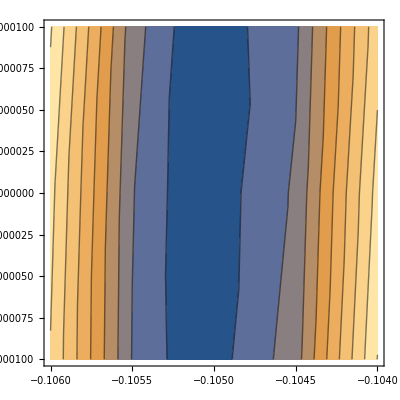

```mathematica
ListContourPlot[Flatten[plotChi2List2D2,1]]
```

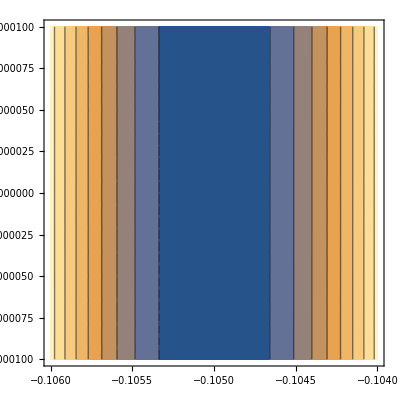

```mathematica
ContourPlot[fit332[a,par],{a,-0.104,-0.106},{par,-10^-6,10^-6}]
```

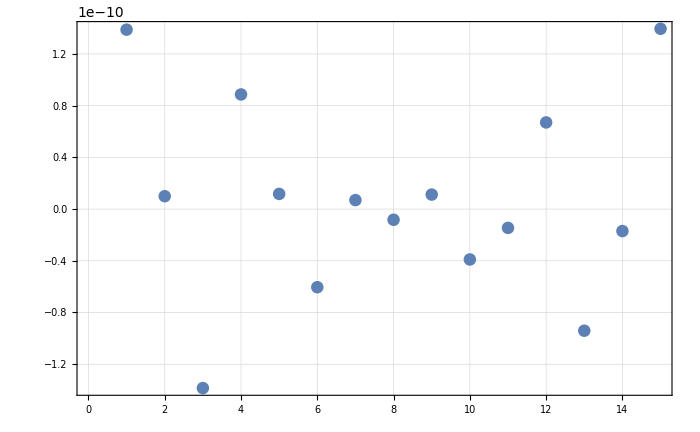

```mathematica
ListPlot[fit332["FitResiduals"]]
```

```mathematica
plotChi2List2D2[[All,2]]
```

{{-0.104,0,1.6742×10^-9},{-0.1045,0,4.3137×10^-10},{-0.1051,0,1.6652×10^-11},{-0.1055,0,4.13136×10^-10},{-0.106,0,1.66332×10^-9}}

```mathematica
Flatten[plotChi2List2D2,1][[All]]
```

{{-0.104,-5.×10^-8,1.80357×10^-9},{-0.104,0,1.6742×10^-9},{-0.104,5.×10^-8,1.52523×10^-9},{-0.1045,-5.×10^-8,5.08869×10^-10},{-0.1045,0,4.3137×10^-10},{-0.1045,5.×10^-8,3.58672×10^-10},{-0.1051,-5.×10^-8,3.24277×10^-11},{-0.1051,0,1.6652×10^-11},{-0.1051,5.×10^-8,3.55996×10^-11},{-0.1055,-5.×10^-8,3.89284×10^-10},{-0.1055,0,4.13136×10^-10},{-0.1055,5.×10^-8,4.94171×10^-10},{-0.106,-5.×10^-8,1.58681×10^-9},{-0.106,0,1.66332×10^-9},{-0.106,5.×10^-8,1.81924×10^-9}}

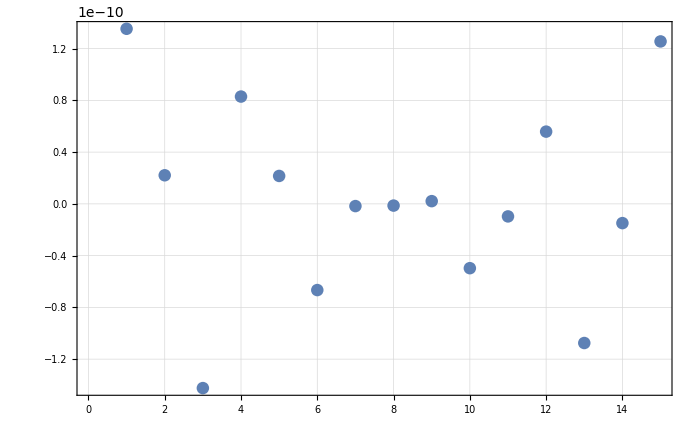

```mathematica
ListPlot[fit2["FitResiduals"]]
```

```mathematica
ListPlot3D[Flatten[plotChi2List2D2,1],PlotStyle->Red]
```

-Graphics3D-

```mathematica
plotChi2List2D2[[All,1]]
```

{{-0.104,-5.×10^-8,1.80357×10^-9},{-0.1045,-5.×10^-8,5.08869×10^-10},{-0.1051,-5.×10^-8,3.24277×10^-11},{-0.1055,-5.×10^-8,3.89284×10^-10},{-0.106,-5.×10^-8,1.58681×10^-9}}

```mathematica
dChi2List2[[All,3]]
```

{1.32204×10^-10,6.24258×10^-11,1.96538×10^-11,7.5394×10^-11,1.45333×10^-10}

```mathematica
Around[plotChi2List2D2[[All,3]][[All,3]],dChi2List2[[All,3]]]
```

{1.52523×10^-9{1.32204×10^-10,6.24258×10^-11,1.96538×10^-11,7.5394×10^-11,1.45333×10^-10},3.58672×10^-10{1.32204×10^-10,6.24258×10^-11,1.96538×10^-11,7.5394×10^-11,1.45333×10^-10},3.55996×10^-11{1.32204×10^-10,6.24258×10^-11,1.96538×10^-11,7.5394×10^-11,1.45333×10^-10},4.94171×10^-10{1.32204×10^-10,6.24258×10^-11,1.96538×10^-11,7.5394×10^-11,1.45333×10^-10},1.81924×10^-9{1.32204×10^-10,6.24258×10^-11,1.96538×10^-11,7.5394×10^-11,1.45333×10^-10}}

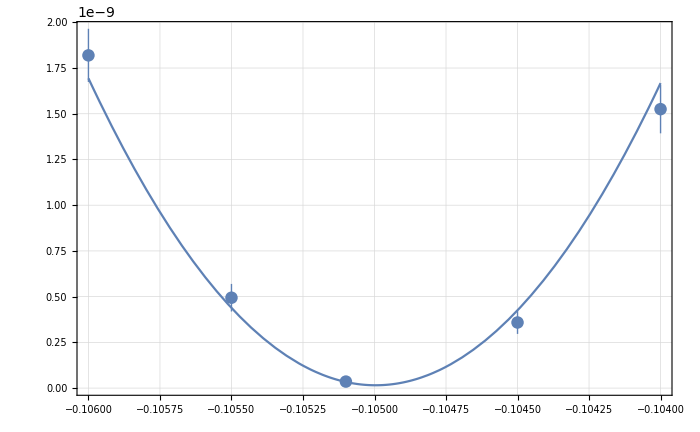

```mathematica
Show[ListPlot[Transpose[{plotChi2List2D2[[All,3]][[All,1]],Table[Around[plotChi2List2D2[[All,3]][[i,3]],dChi2List2[[i,3]]],{i,Length[dChi2List2[[All,3]]]}]}]],Plot[fit2[a,5.*^-8],{a,-0.104,-0.106}]]
```

```mathematica
plotChi2List2D2[[All,3]]
```

{{-0.104,5.×10^-8,1.52523×10^-9},{-0.1045,5.×10^-8,3.58672×10^-10},{-0.1051,5.×10^-8,3.55996×10^-11},{-0.1055,5.×10^-8,4.94171×10^-10},{-0.106,5.×10^-8,1.81924×10^-9}}

```mathematica
plotChi2List2D2[[All,1]][[All,1]]
```

{-0.104,-0.1045,-0.1051,-0.1055,-0.106}

```mathematica
plotChi2List2D2[[All,1]][[All,1]]
```

{-0.104,-0.1045,-0.1051,-0.1055,-0.106}

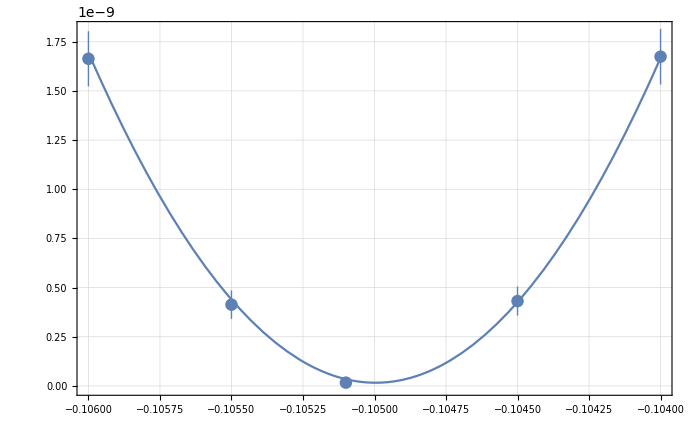

```mathematica
Show[ListPlot[Transpose[{plotChi2List2D2[[All,2]][[All,1]],Table[Around[plotChi2List2D2[[All,2]][[i,3]],dChi2List2[[i,1]]],{i,Length[dChi2List2[[All,2]]]}]}]],Plot[fit2[a,-5.*^-8],{a,-0.104,-0.106}]]
```

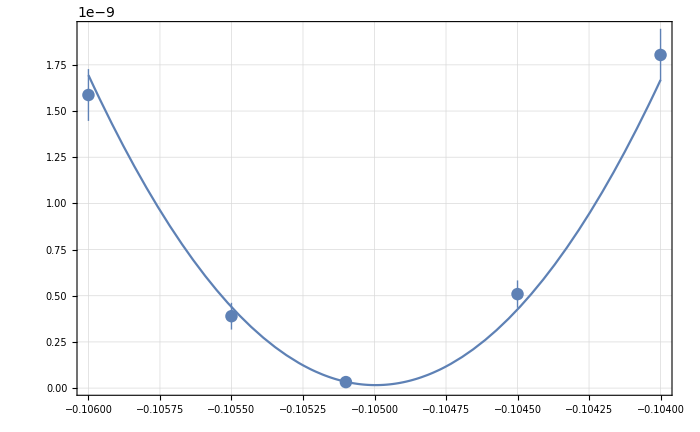

```mathematica
Show[ListPlot[Transpose[{plotChi2List2D2[[All,1]][[All,1]],Table[Around[plotChi2List2D2[[All,1]][[i,3]],dChi2List2[[i,1]]],{i,Length[dChi2List2[[All,1]]]}]}]],Plot[fit2[a,-5.*^-8],{a,-0.104,-0.106}]]
```

```mathematica
Show[ListPlot3D[Flatten[plotChi2List2D2,1],PlotStyle->Red],Plot3D[fit2[a,par],{a,-0.104,-0.106},{par,-5*10^-8,5*10^-8}]]
```

-Graphics3D-

```mathematica
fit=NonlinearModelFit[Flatten[plotChi2List2D,1],{fitfunc[a,a00,par,par0,ascale,pscale,offset],-0.106<a00<-0.104,-1*10^-20<par0<1000,1<ascale<0100,1<pscale<100,-1000<offset<1000},{{a00,-0.10500},{par0,Min[blist2D[[2]]]},{ascale,1},{pscale,1},{offset,1*10^-9}},{a,par},Method->"NMinimize",Weights->1/Flatten[dChi2List,1]^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

```mathematica
Show[ListPlot3D[Flatten[plotChi2List2D2,1]],Plot3D[fit2[a,p],{a,-0.104,-0.106},{p,-1*10^-6,1*10^-6},PlotStyle->Red]]
```

-Graphics3D-

```mathematica
Max[blist2D2[[2]]]
```

1/1000000

```mathematica
fit111=NonlinearModelFit[Flatten[plotChi2List2D2,1],{fitfunc[a,a00,par,par0,ascale,pscale,offset],-0.106<a00<-0.104,-Max[blist2D2[[2]]]<par0<Max[blist2D2[[2]]],-1000<ascale<01000,-100<pscale<100,-1000.<offset≤Min[Chi2List2D2]},{{a00,-0.105},{par0,Min[blist2D2[[2]]]},{ascale,5},{pscale,5/10^4},{offset,Min[Chi2List2D2]}},{a,par},Method->"NMinimize",Weights->1/Flatten[dChi2List,1]^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10,MaxIterations->100]
```

FittedModel[3.71906×10^-12+0.000419499 (0.104867+a)^2+0.00295477 (1.05364×10^-7+par)^2]

```mathematica
4000*1*10^-7.
```

0.0004

```mathematica
fit=NonlinearModelFit[Flatten[plotChi2List2D,1],{fitfunc[a,a00,par,par0,ascale,pscale,offset],-0.106<a00<-0.104,-Max[blist2D[[2]]]<par0<Max[blist2D[[2]]],-100<ascale<0100,-100<pscale<100,-1000.<offset≤Min[Chi2List2D]},{{a00,-0.105},{par0,Min[blist2D[[2]]]},{ascale,5},{pscale,5/10^4},{offset,Min[Chi2List2D]}},{a,par},Method->"NMinimize",Weights->1/Flatten[dChi2List,1]^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

FittedModel[-5.01988×10^-11+0.000913171 (0.10527+a)^2+0.000174287 (4.045×10^-7+par)^2]

```mathematica
fit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a00 | -0.10527 | 0.0000248684 | -4233.1 | 1.33204×10^-32
par0 | 4.06975×10^-8 | 5.77559×10^-8 | 0.704647 | 0.497112
ascale | 33.9083 | 1.04967 | 32.3038 | 1.9036×10^-11
pscale | 0.0693461 | 0.00714158 | 9.71018 | 2.07996×10^-6
offset | -1.×10^-20 | 1.29788×10^-11 | -7.70487×10^-10 | 1

```mathematica
fit["ParameterTable"][[1,1,2,2]]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

-0.105478

```mathematica
(fit["ParameterTable"][[1,1,2,2]]+0.105)/-0.105
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

0.00166873

```mathematica
(Around[fit["ParameterTable"][[1,1,2,2]],fit["ParameterTable"][[1,1,2,3]]]+0.105)/-0.105
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

0.002570.00015

```mathematica
blist2D2={{-0.104,-.1045,-.1051,-.1055,-0.1060},{-1*10^-6,0,1*10^-6}}
```

{{-0.104,-0.1045,-0.1051,-0.1055,-0.106},{-1/1000000,0,1/1000000}}

```mathematica
XDetDataList2D22={{#/Total[#]&@da0Spectruma1040detShiftMin[[All,2]],#/Total[#]&@da0Spectruma1040detShift2[[All,2]],#/Total[#]&@da0Spectruma1040detShiftMin[[All,2]]},{#/Total[#]&@da0Spectruma1045detShiftMin[[All,2]],#/Total[#]&@da0Spectruma1045detShift2[[All,2]],#/Total[#]&@da0Spectruma1045detShiftMin[[All,2]]},{#/Total[#]&@da0Spectruma1051detShiftMin[[All,2]],#/Total[#]&@da0Spectruma1051[[All,2]],#/Total[#]&@da0Spectruma1051detShiftMin[[All,2]]},
{#/Total[#]&@da0Spectruma1055detShiftMin[[All,2]],#/Total[#]&@da0Spectruma1055detShift2[[All,2]],#/Total[#]&@da0Spectruma1055detShiftMin[[All,2]]},
{#/Total[#]&@da0Spectruma1060detShiftMin[[All,2]],#/Total[#]&@da0Spectruma1060detShift2[[All,2]],#/Total[#]&@da0Spectruma1060detShiftMin[[All,2]]}
};
```

```mathematica
RefNorm=d0Spectruma02564Bin[[All,2]]/Total[d0Spectruma02564Bin[[All,2]]];
```

```mathematica
Chi2List2D2=Table[Total[(RefNorm-XDetDataList2D22⟦b,par⟧)^2],{b,Length[blist2D2[[1]]]},{par,Length[blist2D2[[2]]]}];
```

```mathematica
Chi2List2D2=Table[Total[(RefNorm-XDetDataList2D22⟦b,par⟧)^2],{b,Length[blist2D2[[1]]]},{par,Length[blist2D2[[2]]]}];
```

```mathematica
plotChi2List2D2=Table[{blist2D2[[1,b]],blist2D2[[2,par]],Total[(RefNorm-XDetDataList2D22⟦b,par⟧)^2]},{b,Length[blist2D2[[1]]]},{par,Length[blist2D2[[2]]]}];
```

```mathematica
dChi2List2=Table[10^-4 √Total[(RefNorm-XDetDataList2D22⟦b,para⟧)^2 (RefNorm^2+XDetDataList2D22⟦b,para⟧^2)],{b,Length[blist2D2[[1]]]},{para,Length[blist2D2[[2]]]}];
```

```mathematica
NonlinearModelFit[Flatten[plotChi2List2D,1],{fitfunc[a,a00,par,par0,ascale,pscal{0.05,Chi2InterPos}e,offset]},{a00,par0,ascale,pscale,offset},{a,par},Method->"NMinimize",Weights->1/Flatten[dChi2List,1]^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

FittedModel[-0.00206676+0.139624 (-0.00951374+a)^2+0.0382266 (0.0783482+par)^2]

```mathematica
fit2=NonlinearModelFit[Flatten[plotChi2List2D2,1],{fitfunc[a,a00,par,par0,ascale,pscale,offset],-0.106<a00<-0.104,-Max[blist2D2[[2]]]<par0<Max[blist2D[[2]]],-100<ascale<100,-10<pscale<10,-100<offset≤100},{{a00,-0.105},{par0,0},{ascale,.00005},{pscale,0.000000005},{offset,Min[Chi2List2D2]}},{a,par},Method->"NMinimize",Weights->1/Flatten[dChi2List2,1]^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[2.55309×10^-11+0.000256754 (0.105926+a)^2+0.139855 (3.96916×10^-7+par)^2]

```mathematica
(fit2["ParameterTable"][[1,1,2,2]]+0.105)/-0.105
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

0.00676437

```mathematica
fit2=NonlinearModelFit[Flatten[plotChi2List2D2,1],{fitfunc[a,a00,par,par0,ascale,pscale,offset],-0.106<a00<-0.104,-Max[blist2D2[[2]]]<par0<Max[blist2D2[[2]]],-1000<ascale<01000,-100<pscale<100,-1000.<offset≤Min[Chi2List2D2]},{{a00,-0.105},{par0,Min[blist2D2[[2]]]},{ascale,5},{pscale,5/10^4},{offset,Min[Chi2List2D2]}},{a,par},Method->"NMinimize",Weights->1/Flatten[dChi2List2,1]^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10,MaxIterations->100]
```

FittedModel[-2.26175×10^-11+0.000995468 (0.105468+a)^2+0.000155272 (-8.35286×10^-7+par)^2]

```mathematica
fit32=NonlinearModelFit[Flatten[plotChi2List2D2,1],{fitfunc[a,a00,par,par0,ascale,pscale,offset],-0.106<a00<-0.104,-Max[blist2D2[[2]]]<par0<Max[blist2D2[[2]]],1*10^-20<ascale<1000,1*10^-20<pscale<100,1*10^-15<offset≤Min[Chi2List2D2]},{{a00,-0.105},{par0,Min[blist2D2[[2]]]},{ascale,5},{pscale,5/10^4},{offset,Min[Chi2List2D2]}},{a,par},Method->"NMinimize",Weights->1/Flatten[dChi2List,1]^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10,MaxIterations->10000]
```

FittedModel[1.×10^-15+0.000887105 (0.105385+a)^2+281.161 (-1.83171×10^-15+par)^2]

```mathematica
fit32["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a00 | -0.105385 | 0.000027532 | -3827.74 | 3.64483×10^-32
par0 | 1.83171×10^-15 | 4.2093×10^-8 | 4.35158×10^-8 | 1.
ascale | 33.5747 | 0.999659 | 33.5862 | 1.29397×10^-11
pscale | 0.0596379 | 0.00441718 | 13.5014 | 9.57154×10^-8
offset | 1.×10^-15 | 1.36991×10^-11 | 0.0000729975 | 0.999943

```mathematica
(-0.10538539058755865+0.105)/0.105
```

-0.00367039

```mathematica
fit2["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a00 | -0.105006 | 0.0000385319 | -2725.17 | 1.08933×10^-30
par0 | 2.74664×10^-7 | 0.012602 | 0.0000217952 | 0.999983
ascale | 42.8098 | 1.71021 | 25.0319 | 2.36943×10^-10
pscale | -32.6315 | 2.76586×10^-6 | -1.1798×10^7 | 4.71003×10^-67
offset | 1.6652×10^-11 | 9.47275×10^-12 | 1.75788 | 0.109277

```mathematica
ListPlot3D[Flatten[plotChi2List2D,1]]
```

```mathematica
-Graphics3D-{0.05,Chi2InterPos}
```

```mathematica
ListPlot3D[Flatten[plotChi2List2D2,1]]
```

-Graphics3D-

```mathematica
Flatten[plotChi2List2D2,1]
```

{{-0.104,-1/1000000,5.95057×10^-9},{-0.104,0,1.52523×10^-9},{-0.104,1/1000000,5.95057×10^-9},{-0.1045,-1/1000000,3.38644×10^-9},{-0.1045,0,3.58672×10^-10},{-0.1045,1/1000000,3.38644×10^-9},{-0.1051,-1/1000000,1.2098×10^-9},{-0.1051,0,1.6652×10^-11},{-0.1051,1/1000000,1.2098×10^-9},{-0.1055,-1/1000000,3.9831×10^-10},{-0.1055,0,4.94171×10^-10},{-0.1055,1/1000000,3.9831×10^-10},{-0.106,-1/1000000,1.32069×10^-10},{-0.106,0,1.81924×10^-9},{-0.106,1/1000000,1.32069×10^-10}}

```mathematica
Plot3D[1.6652003592893396*^-11+0.0005456496469585788 (0.10500615066646028+a)^2+0.0009391287052722177 (-2.746641090880361*^-7+par)^2,{a,-0.106,-0.104},{par,-1*10^-6,1*10^-6}]
```

-Graphics3D-

```mathematica
{0.05,Chi2InterPos}
```

```mathematica
Show[Plot3D[1.6652003592893396*^-11+0.0005456496469585788 (0.10500615066646028+a)^2+0.0009391287052722177 (-2.746641090880361*^-7+par)^2,{a,-0.106,-0.104},{par,-1*10^-6,1*10^-6}],ListPlot3D[Flatten[plotChi2List2D2,1]]]
```

-Graphics3D-

```mathematica
(fit2["ParameterTable"][[1,1,2,2]]+0.105)/-0.105
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

0.0000585778

```mathematica
(fit2["ParameterTable"][[1,1,2,2]]+0.105)/-0.105/(10^-6)
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

58.5778

```mathematica
58.577775812249236*10^-5
```

0.000585778

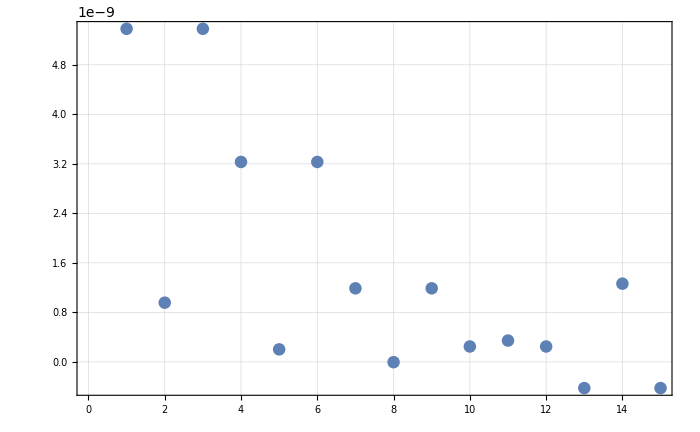

```mathematica
ListPlot[fit2["FitResiduals"]]
```

```mathematica
fitfunc3[a_,a0_,par_,par0_,ascale_,pscale_]:=(a-a0)^2/ascale^2+(par-par0)^2/pscale^2
```

```mathematica
fit2=NonlinearModelFit[Flatten[plotChi2List2D2,1],{fitfunc3[a,a00,par,par0,ascale,pscale],-0.106<a00<-0.104,-Max[blist2D2[[2]]]<par0<Max[blist2D2[[2]]],1*10^-10<ascale<01000,1*10^-10<pscale<100},{{a00,-0.105},{par0,Min[blist2D2[[2]]]},{ascale,5},{pscale,5/10^4},{offset,Min[Chi2List2D2]}},{a,par},Method->"NMinimize",Weights->1/Flatten[dChi2List2,1]^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10,MaxIterations->100]
```

```mathematica
FittedModel[0.000993782385605187 (0.10547283786866334+a)^2+253.87883866004165 (4.346162902579628*^-9+par)^2]{0.05,Chi2InterPos}
```

{5.95057×10^-9,3.38644×10^-9,1.2098×10^-9,3.9831×10^-10,1.32069×10^-10}

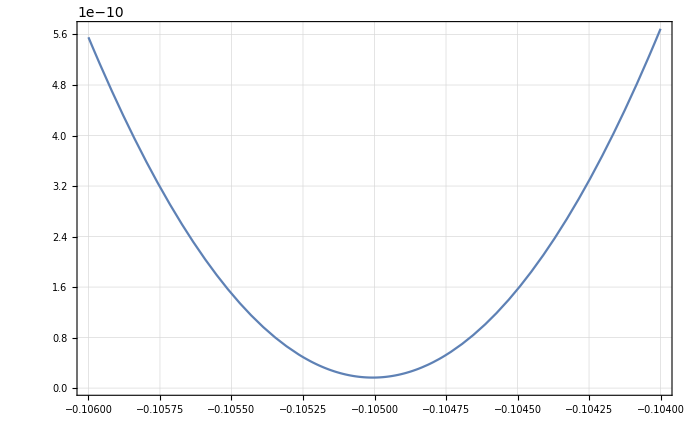

```mathematica
ListPlot[plotChi2List2D2[[All,1,3]]
```

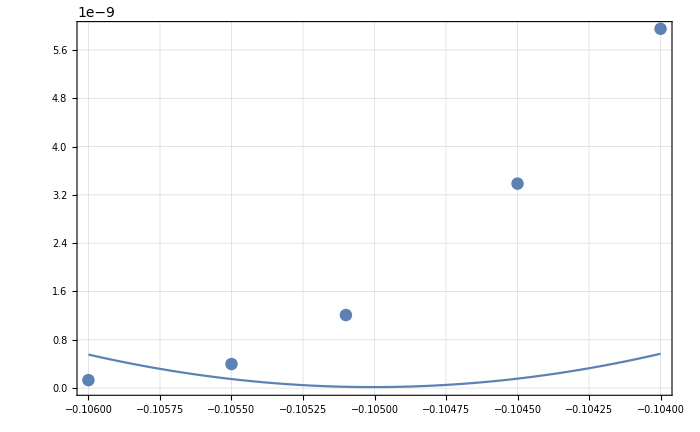

```mathematica
Show[ListPlot[Transpose[{plotChi2List2D2[[All,1,1]],plotChi2{0.05,Chi2InterPos}List2D2[[All,1,3]]}]],Plot[fit2[a,-1*10^-6],{a,-0.104,-0.106}]]
```

```mathematica
?fitfunc
```

```mathematica
fit5=NonlinearModelFit[Flatten[plotChi2List2D,1],{fitfunc[a,a00,par,par0,ascale,pscale,offset],-0.106<a00<-0.104,-Max[blist2D[[2]]]<par0<Max[blist2D[[2]]],1*10^-7<ascale<100,1*10^-7<pscale<10,1*10^-15<offset<1},{{a00,-0.105},{par0,0},{ascale,5},{pscale,5/10^4},{offset,6*10^-9}},{a,par},Method->"NMinimize",Weights->1/Flatten[dChi2List,1]^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10,MaxIterations->1000]
```

FittedModel[1.×10^-15+0.0006765 (0.105322+a)^2+328.428 (-3.01624×10^-8+par)^2]

```mathematica
?fitfunc3
```

```mathematica
fit4=NonlinearModelFit[Flatten[plotChi2List2D2,1],{fitfunc[a,a00,par,par0,ascale,pscale,offset],-0.106<a00<-0.104,-Max[blist2D2[[2]]]<par0<Max[blist2D2[[2]]],1*10^-20<ascale<01000,1*10^-6<pscale<10,-1000.<offset≤Min[Chi2List2D2]},{{a00,-0.105},{par0,Min[blist2D2[[2]]]},{ascale,5},{pscale,5/10^4},{offset,Min[Chi2List2D2]}},{a,par},Method->"NMinimize",Weights->1/Flatten[dChi2List2,1]^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10,MaxIterations->1000]
```

FittedModel[-8.73921×10^-11+0.000854889 (0.105519+a)^2+338.202 (1.36875×10^-14+par)^2]

```mathematica
Plot3D[fit4[a,par],{a,-0.104,-0.106},{par,-1*10^-6,1*10^-6}]
```

-Graphics3D-

```mathematica
?fit4
```

```mathematica
Plot3D[-8.739213593064017*^-11+0.0008548889683885415 (0.10551938233404774+a)^2+338.20227049425347 (1.3687487583571673*^-14+par)^2,{a,-0.106,-0.104},{par,-1*10^-6,1*10^-6}]
```

-Graphics3D-

# drD = -2.24316 kFactor

### a=-1050

```mathematica
da0SubFileNamesa1050rD2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drD2/a-1050/"];
```

```mathematica
da0Spectruma1050rD2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050rD2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1050rD2[[All,2]]}],PlotRange->All]
```

Transpose::nmtx: The first two levels of {{-0.00915625,-0.00886875,-0.00858125,-0.00829375,-0.00800625,-0.00771875,-0.00743125,-0.00714375,-0.00685625,-0.00656875,-0.00628125,-0.00599375,-0.00570625,-0.00541875,-0.00513125,-0.00484375,-0.00455625,-0.00426875,-0.00398125,-0.00369375,-0.00340625,-0.00311875,-0.00283125,-0.00254375,-0.00225625,-0.00196875,-0.00168125,-0.00139375,-0.00110625,-0.00081875,-0.00053125,-0.00024375,0.00004375,0.00033125,0.00061875,0.00090625,0.00119375,0.00148125,0.00176875,0.00205625,0.00234375,0.00263125,0.00291875,0.00320625,0.00349375,0.00378125,0.00406875,0.00435625,0.00464375,0.00493125,«14»},{}} cannot be transposed.

ListPlot::lpn: Transpose[{{-0.00915625,-0.00886875,-0.00858125,-0.00829375,-0.00800625,-0.00771875,-0.00743125,-0.00714375,-0.00685625,-0.00656875,-0.00628125,-0.00599375,-0.00570625,-0.00541875,-0.00513125,-0.00484375,-0.00455625,-0.00426875,-0.00398125,-0.00369375,-0.00340625,-0.00311875,-0.00283125,-0.00254375,-0.00225625,-0.00196875,-0.00168125,-0.00139375,-0.00110625,-0.00081875,-0.00053125,-0.00024375,0.00004375,0.00033125,0.00061875,0.00090625,0.00119375,0.00148125,0.00176875,0.00205625,0.00234375,0.00263125,0.00291875,0.00320625,0.00349375,0.00378125,0.00406875,0.00435625,0.00464375,0.00493125,«14»},{}}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{{-0.00915625,-0.00886875,-0.00858125,-0.00829375,-0.00800625,-0.00771875,-0.00743125,-0.00714375,-0.00685625,-0.00656875,-0.00628125,-0.00599375,-0.00570625,-0.00541875,-0.00513125,-0.00484375,-0.00455625,-0.00426875,-0.00398125,-0.00369375,-0.00340625,-0.00311875,-0.00283125,-0.00254375,-0.00225625,-0.00196875,-0.00168125,-0.00139375,-0.00110625,-0.00081875,-0.00053125,-0.00024375,0.00004375,0.00033125,0.00061875,0.00090625,0.00119375,0.00148125,0.00176875,0.00205625,0.00234375,0.00263125,0.00291875,0.00320625,0.00349375,0.00378125,0.00406875,0.00435625,0.00464375,0.00493125,0.00521875,0.00550625,0.00579375,0.00608125,0.00636875,0.00665625,0.00694375,0.00723125,0.00751875,0.00780625,0.00809375,0.00838125,0.00866875,0.00895625},{}}],PlotRange→All]

### a=-1040

```mathematica
da0SubFileNamesa1040rD2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drD2/a-1040/"];
```

```mathematica
da0Spectruma1040rD2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040rD2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1040rD2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045rD2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drD2/a-1045/"];
```

```mathematica
da0Spectruma1045rD2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045rD2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1045rD2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055rD2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drD2/a-1055/"];
```

```mathematica
da0Spectruma1055rD2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055rD2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1055rD2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060rD2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drD2/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060rD2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060rD2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1060rD2[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1050rD2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1050rD2[[All,2]]}]];
da0Spectruma1040rD2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1040rD2[[All,2]]}]];
da0Spectruma1045rD2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1045rD2[[All,2]]}]];
da0Spectruma1055rD2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1055rD2[[All,2]]}]];
da0Spectruma1060rD2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1060rD2[[All,2]]}]];
```

Power::infy: Infinite expression 1/0 encountered.

Transpose::nmtx: The first two levels of {{-0.00915625,-0.00886875,-0.00858125,-0.00829375,-0.00800625,-0.00771875,-0.00743125,-0.00714375,-0.00685625,-0.00656875,-0.00628125,-0.00599375,-0.00570625,-0.00541875,-0.00513125,-0.00484375,-0.00455625,-0.00426875,-0.00398125,-0.00369375,-0.00340625,-0.00311875,-0.00283125,-0.00254375,-0.00225625,-0.00196875,-0.00168125,-0.00139375,-0.00110625,-0.00081875,-0.00053125,-0.00024375,0.00004375,0.00033125,0.00061875,0.00090625,0.00119375,0.00148125,0.00176875,0.00205625,0.00234375,0.00263125,0.00291875,0.00320625,0.00349375,0.00378125,0.00406875,0.00435625,0.00464375,0.00493125,«14»},{}} cannot be transposed.

Interpolation::innd: First argument in Transpose[{{-0.00915625,-0.00886875,-0.00858125,-0.00829375,-0.00800625,-0.00771875,-0.00743125,-0.00714375,-0.00685625,-0.00656875,-0.00628125,-0.00599375,-0.00570625,-0.00541875,-0.00513125,-0.00484375,-0.00455625,-0.00426875,-0.00398125,-0.00369375,-0.00340625,-0.00311875,-0.00283125,-0.00254375,-0.00225625,-0.00196875,-0.00168125,-0.00139375,-0.00110625,-0.00081875,-0.00053125,-0.00024375,0.00004375,0.00033125,0.00061875,0.00090625,0.00119375,0.00148125,0.00176875,0.00205625,0.00234375,0.00263125,0.00291875,0.00320625,0.00349375,0.00378125,0.00406875,0.00435625,0.00464375,0.00493125,«14»},{}}] does not contain a list of data and coordinates.

```mathematica
Plot[{
d0Spectrum2564BinInter[x]-da0Spectruma1050rD2Inter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1040rD2Inter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1045rD2Inter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1055rD2Inter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1060rD2Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109986} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.01057} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0101414} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[{
d0Spectrum2564BinInter[x]-da0Spectruma1050rD2Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109986} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.01057} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0101414} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rD2List={#/Total[#]&@da0Spectruma1040rD2[[All,2]],#/Total[#]&@da0Spectruma1045rD2[[All,2]],#/Total[#]&@da0Spectruma1055rD2[[All,2]],#/Total[#]&@da0Spectruma1060rD2[[All,2]]};
```

```mathematica
bList={-0.104,-0.1045,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma02564Bin[[All,2]],rD2List,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.69476×10^-9,4.8862×10^-10,5.71605×10^-10,1.84188×10^-9},{1.45266×10^-10,8.09326×10^-11,8.05583×10^-11,1.43305×10^-10}},a0 =  | -0.104976
FittedModel[1.16482×10^-10+0.00165081 (0.104976+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104976 | 0.0000231675 | -4531.2 | 0.000140497
scale | 0.00165081 | 0.000155882 | 10.5901 | 0.059937
yoffset | 1.16482×10^-10 | 8.33247×10^-11 | 1.39793 | 0.39531 | 
 | DF | SS | MS
Model | 3 | 388.097 | 129.366
Error | 1 | 0.00378803 | 0.00378803
Uncorrected Total | 4 | 388.101 | 
Corrected Total | 3 | 113.369 |  | ,-Graphics-}

```mathematica
(-0.1049764467778083+0.105)/-0.105
```

-0.000224316

```mathematica
(-0.1049764467778083+0.105)/-0.105/(1*10^-4)
```

-2.24316

```mathematica
0.165*0.38095238095276196
```

0.0628571

```mathematica
0.14*10^-3
```

0.00014

```mathematica
*0.005
```

```mathematica
?TransferToRefParableFitForProtons
```

```mathematica
RefNormed=d0Spectruma02564Bin[[All,2]]/Total[d0Spectruma02564Bin[[All,2]]];
```

```mathematica
rDList2={#/Total[#]&@da0Spectruma1040rD[[All,2]],#/Total[#]&@da0Spectruma1055rD[[All,2]],#/Total[#]&@da0Spectruma1060rD[[All,2]]};
```

```mathematica
parist2={-0.104,-0.1055,-0.1060}
```

{-0.104,-0.1055,-0.106}

```mathematica
Chi2List=Table[Total[(RefNormed-rDList2⟦b⟧)^2],{b,1,Length[parist2]}];dChi2List=Table[10^-Prec √Total[(RefNormed-rDList2⟦b⟧)^2 (RefNormed^2+rDList2⟦b⟧^2)],{b,1,Length[parist2]}];
```

```mathematica
da0Spectruma1050rD[[All,2]]
```

{9.06957×10^-7,1.81265×10^-6,3.17947×10^-6,5.08853×10^-6,7.52247×10^-6,0.0000107999,0.0000148685,0.0000201464,0.0000258858,0.0000323841,0.0000396133,0.0000475426,0.0000561385,0.0000653067,0.0000750634,0.0000853131,0.0000960072,0.00010711,0.000118496,0.000130101,0.000141834,0.000153512,0.00016508,0.000176228,0.000186805,0.000196506,0.000205205,0.000212816,0.000218937,0.000223553,0.000226513,0.000227824,0.000227503,0.00022539,0.000221635,0.000216104,0.000208849,0.00019981,0.000188927,0.00017655,0.000162974,0.000148131,0.000132791,0.000117413,0.000102383,0.0000881386,0.0000748768,0.000063044,0.0000525186,0.0000437577,0.0000364766,0.0000301859,0.0000245503,0.0000198638,0.000016084,0.0000127569,9.82994×10^-6,7.51918×10^-6,5.6448×10^-6,4.11715×10^-6,2.92287×10^-6,2.41138×10^-6,1.89893×10^-6,1.01024×10^-6}

```mathematica
rDT={9.069567440056569*^-7,1.8126468492439406*^-6,3.1794737410753658*^-6,5.088525292368003*^-6,7.522472634152381*^-6,0.00001079992944946877,0.000020146404459241787,0.000025885771416180534,0.000032384147243543754,0.00003961326864341344,0.00004754257219167049,0.00005613850025126321,0.00006530665148176822,0.00007506344521450149,0.00008531312700533176,0.00009600719237759074,0.00010710985619474986,0.00011849579927279875,0.00013010103573727743,0.0001418336408105799,0.00015351226850744449,0.00016507976338929128,0.00017622756355488664,0.00018680451811875582,0.00019650646983695983,0.00020520494953113743,0.0002128156189806299,0.00021893740110407145,0.00022355334550065796,0.00022651313432653158,0.00022782386924799714,0.0002275027240676834,0.00022539017276220865,0.0002216350107743705,0.00021610381608362737,0.00020884883124233143,0.00019981016499665417,0.00018892655717472022,0.00017655027346065287,0.00016297356520225952,0.0001481310978070472,0.0001327913945430866,0.0001174127144830701,0.00010238305282372386,0.00008813864558478893,0.0000748768097296323,0.00006304402907984254,0.00005251864502114914,0.00004375770701169288,0.00003647664730501606,0.00003018587937598928,0.00002455031599791362,0.00001986384927212897,0.000016084037645748576,0.000012756890498725379,9.829939817871182*^-6,7.519180357446638*^-6,5.644799734183866*^-6,4.117150571458169*^-6,2.9228661871746203*^-6,2.4113821396241955*^-6,1.8989312500679634*^-6,1.0102437057651976*^-6};
```

```mathematica
RefNormed2={0.00014858904487204659,0.00029696208727602506,0.000520876585018512,0.0008336153373528347,0.0012323332075858508,0.0017692544019933562,0.0033003296922786414,0.004240568195208373,0.005305079460840746,0.006489387170752249,0.007788233536669079,0.009196349465058817,0.010698306605995788,0.012296491483703537,0.013974718249291836,0.015727371193293645,0.017546152728669138,0.019411314768720284,0.021312413254540533,0.023234302764990663,0.025147469793757406,0.027042157206396838,0.028868616739496335,0.030601133811060225,0.032190481655503665,0.03361470087769292,0.03486198540724628,0.03586513769641405,0.03662088560295234,0.03710578369117367,0.03732046202541428,0.03726796558238139,0.03692208107956365,0.03630670171267547,0.0354005441945387,0.0342122156550605,0.03273135368353815,0.030948659056030926,0.028921196500917543,0.026697618726974723,0.0242662250837081,0.021753026172168087,0.019233357526299635,0.0167724009117369,0.014438568552724023,0.012266384559973052,0.010327467792378116,0.008603253807220289,0.0071685232275218195,0.0059753942357160614,0.004944544118583336,0.004021525370277512,0.0032540378664618614,0.0026348601706727482,0.0020898065793645173,0.0016103224531597222,0.0012317853079146267,0.0009247314604685416,0.00067447631493207,0.00047883083806722675,0.0003950400550878114,0.00031109009286896944,0.00016445875386702043};
```

```mathematica
chi21050=Total[(RefNormed2-#/Total[#]&@rDT)^2]
```

1.68591×10^-7

```mathematica
ListPlot[(RefNormed-#/Total[#]&@rDList2[[1]])^2]
```

-Graphics-

```mathematica
ListPlot[(RefNormed2-#/Total[#]&@rDT)^2]
```

-Graphics-

```mathematica
dchi1050=10^-Prec √Total[(RefNormed2-#/Total[#]&@rDT)^2 (RefNormed2^2+(#/Total[#])^2&@rDT)]
```

1.84249×10^-9

```mathematica
dChi2List={1.389063536300576*^-10,1.8424859198426524*^-9,7.124888134644846*^-11,1.4054957367432405*^-10}
```

{1.38906×10^-10,1.84249×10^-9,7.12489×10^-11,1.4055×10^-10}

```mathematica
Chi2List={{-0.104,1.6806285467304185*^-9},{-0.105,chi21050},{-0.1055,4.3482829233122934*^-10},{-0.106,1.6950824595319486*^-9}}
```

{{-0.104,1.68063×10^-9},{-0.105,1.68591×10^-7},{-0.1055,4.34828×10^-10},{-0.106,1.69508×10^-9}}

```mathematica
-0.1035<-0.1050<-0.1065
```

False

```mathematica
fitresult=NonlinearModelFit[Chi2List,{fitfunc[b,b0,yoffset,scale],-0.1060<b0<-0.1035&&0.<scale<1/10&&0.<yoffset≤Min[Chi2List[[All,2]]]},{{b0,-0.1051},{scale,5/10^4},{yoffset,Min[Chi2List[[All,2]]]}},b,Method->"NMinimize",Weights->1/dChi2List^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

FittedModel[4.34828×10^-10+0.00114639 (0.105087+b)^2]

```mathematica
fitresult["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105087 | 0.0000497118 | -2113.93 | 0.000301155
scale | 0.00114639 | 0.000175583 | 6.52905 | 0.0967538
yoffset | 4.34828×10^-10 | 1.14535×10^-10 | 3.79647 | 0.163963

```mathematica
ListPlot[Chi2List]
```

-Graphics-

```mathematica
d0Spectruma02564Bin[[All,2]]
```

```mathematica
RefNormed=RefTransfer/RefNorm;Sigma=(If[#1==0,10000,10^-Prec #1]&)/@RefNormed;TransferDataListNormed=(#1/Total[#1]&)/@TransferDataList;Chi2List=Table[Total[(RefNormed-TransferDataListNormed⟦b⟧)^2],{b,1,Length[ParaList]}];dChi2List=Table[10^-Prec √Total[(RefNormed-TransferDataListNormed⟦b⟧)^2 (RefNormed^2+TransferDataListNormed⟦b⟧^2)],{b,1,Length[ParaList]}];errorplotdata=Transpose[{ParaList,Table[10^9 Around[Chi2List⟦b⟧,dChi2List⟦b⟧],{b,1,Length[ParaList]}]}];fitfunc[x_,x0_,f_,g_]:=f+g (x-x0)^2;fitresult=NonlinearModelFit[Transpose[{ParaList,Chi2List}],{fitfunc[b,b0,yoffset,scale],bMin<b0<bMax&&0.<scale<1/10&&0.<yoffset≤Min[Chi2List]},{{b0,-0.1051},{scale,5/10^4},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2List^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10];{{Chi2List,dChi2List},TableForm[{{"a0 = ",fitresult["BestFitParameters"]⟦1,2⟧},fitresult,fitresult["ParameterTable"],fitresult["ANOVATable"]}],Show[ListPlot[errorplotdata,PlotRange->{{bMin,bMax},Automatic}],Plot[10^9 fitresult[b],{b,bMin,bMax},PlotStyle->Red]]}]
```

# dWF = 0.14

### a=-1050

```mathematica
da0SubFileNamesa1050WF=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dWF/a-1050/"];
```

```mathematica
da0Spectruma1050WF=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050WF,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1050WF[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040WF=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dWF/a-1040/"];
```

```mathematica
da0Spectruma1040WF=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040WF,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1040WF[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045WF=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dWF/a-1045/"];
```

```mathematica
da0Spectruma1045WF=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045WF,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1045WF[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055WF=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dWF/a-1055/"];
```

```mathematica
da0Spectruma1055WF=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055WF,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1055WF[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060WF=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dWF/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060WF=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060WF,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1060WF[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1050WFInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1050WF[[All,2]]}]];
da0Spectruma1040WFInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1040WF[[All,2]]}]];
da0Spectruma1045WFInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1045WF[[All,2]]}]];
da0Spectruma1055WFInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1055WF[[All,2]]}]];
da0Spectruma1060WFInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1060WF[[All,2]]}]];
```

```mathematica
Plot[{
d0Spectrum2564BinInter[x]-da0Spectruma1050WFInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1040WFInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1045WFInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1055WFInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1060WFInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.00929962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
WFList={#/Total[#]&@da0Spectruma1040WF[[All,2]],#/Total[#]&@da0Spectruma1045WF[[All,2]],#/Total[#]&@da0Spectruma1050WF[[All,2]],#/Total[#]&@da0Spectruma1055WF[[All,2]],#/Total[#]&@da0Spectruma1060WF[[All,2]]};
```

```mathematica
bList={-0.104,-.1045,-.1050,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma02564Bin[[All,2]],WFList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{3.56475×10^-9,1.58175×10^-9,4.16365×10^-10,7.77857×10^-11,5.68255×10^-10},{1.91703×10^-10,1.23471×10^-10,5.4926×10^-11,2.25631×10^-11,8.7117×10^-11}},a0 =  | -0.105454
FittedModel[7.45823×10^-11+0.00165236 (0.105454+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105454 | 0.0000282704 | -3730.2 | 7.1868×10^-8
scale | 0.00165236 | 0.000104304 | 15.8417 | 0.00396104
yoffset | 7.45823×10^-11 | 2.12864×10^-11 | 3.50376 | 0.0726879 | 
 | DF | SS | MS
Model | 3 | 621.788 | 207.263
Error | 2 | 0.00159118 | 0.00079559
Uncorrected Total | 5 | 621.79 | 
Corrected Total | 4 | 494.485 |  | ,-Graphics-}

```mathematica
(-0.10545429174165592+0.105)/-0.105/0.03
```

0.14422

```mathematica
0.14*10^-3
```

0.00014

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/(0.03)
```

0.1440.009

```mathematica
(-0.10545429174165592+0.105)/-0.105/(0.03)
```

0.14422

```mathematica
0.14*10^-3
```

0.00014

```mathematica
*0.005
```

0.0007

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/10^-6
```

-8693.198.

# dBSCorr =

### a=-1050

```mathematica
da0SubFileNamesa1050BSCorr=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSCorr/a-1050/"];
```

```mathematica
da0SubFileNamesa1050BSCorr2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSCorr/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSCorr/a-1050/TransferResult_08-09-20_SC_diffProf_C_dBSCorr_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSCorr/a-1050/TransferResult_08-09-20_SC_diffProf_D_dBSCorr_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSCorr/a-1050/TransferResult_08-09-20_SC_diffProf_C_dBSCorr_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSCorr/a-1050/TransferResult_08-09-20_SC_diffProf_D_dBSCorr_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSCorr/a-1050/TransferResult_08-09-20_SC_diffProf_C_dBSCorr_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSCorr/a-1050/TransferResult_08-09-20_SC_diffProf_C_dBSCorr_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSCorr/a-1050/TransferResult_08-09-20_SC_diffProf_C_dBSCorr_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSCorr/a-1050/TransferResult_08-09-20_SC_diffProf_C_dBSCorr_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSCorr/a-1050/TransferResult_08-09-20_SC_diffProf_C_dBSCorr_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSCorr/a-1050/TransferResult_08-09-20_SC_diffProf_C_dBSCorr_a-1050_57-64.txt}

```mathematica
da0Spectruma1050BSCorr2[[9;;64+8]][[All,2]]//Length
```

64

```mathematica
da0Spectruma1050BSCorr2[[9;;64+8]][[All,2]]==da0Spectruma1050BSCorr[[All,2]]
```

True

```mathematica
0.000039869899527572004==0.000039869899527572004
```

True

```mathematica
da0Spectruma1050BSCorr2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050BSCorr2,1]
```

{{33.6387,9.14816×10^-7},{33.6834,1.82805×10^-6},{32.3095,3.20592×10^-6},{46.5746,5.12987×10^-6},{456.107,7.58197×10^-6},{667.105,0.0000108829},{1053.6,0.0000153134},{1279.72,0.0000202913},{16.9849,9.14816×10^-7},{17.1689,1.82805×10^-6},{17.1,3.20592×10^-6},{24.3382,5.12987×10^-6},{282.176,7.58197×10^-6},{423.719,0.0000108829},{718.532,0.0000153134},{879.354,0.0000202913},{1500.,0.0000260651},{1480.01,0.0000325991},{1490.52,0.0000398699},{1593.52,0.0000478281},{1608.31,0.0000564609},{1559.88,0.0000656626},{1821.18,0.0000754498},{1947.91,0.0000857282},{941.519,0.0000260651},{932.445,0.0000325991},{940.762,0.0000398699},{1012.16,0.0000478281},{998.08,0.0000564609},{949.744,0.0000656626},{1129.68,0.0000754498},{1215.23,0.0000857282},{2218.57,0.0000964473},{2358.82,0.000107573},{3032.37,0.000118973},{2673.37,0.000130602},{3140.26,0.00014231},{3357.71,0.000154036},{3554.11,0.00016561},{3806.32,0.000176765},{4258.56,0.000187345},{4337.87,0.000197047},{4388.52,0.000205744},{5478.11,0.000213352},{5403.35,0.000219471},{5267.45,0.000224076},{5157.19,0.000227024},{5058.7,0.000228323},{5479.08,0.000227992},{6804.21,0.000225864},{6461.32,0.000222089},{6294.88,0.00021654},{6672.55,0.000209257},{7107.36,0.000200192},{6110.97,0.000189276},{6773.68,0.000176867},{5144.45,0.00016325},{5529.64,0.000148378},{5009.6,0.000133009},{4768.99,0.000117577},{4901.96,0.00010252},{4449.41,0.0000882428},{4795.17,0.0000749579},{4086.36,0.0000631013},{4043.83,0.00005256},{3924.58,0.0000437876},{3482.71,0.0000364982},{3240.22,0.0000301836},{2705.16,0.0000245835},{2746.2,0.0000200426},{1552.81,0.0000160898},{1572.91,0.0000127612},{179.832,9.83295×10^-6},{149.447,7.52137×10^-6},{125.328,5.6464×10^-6},{108.467,4.11829×10^-6},{139.143,2.92367×10^-6},{112.286,2.41202×10^-6},{73.9528,1.89942×10^-6},{93.5268,1.01053×10^-6}}

```mathematica
da0Spectruma1050BSCorr=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050BSCorr,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1050BSCorr[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040BSCorr=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSCorr/a-1040/"];
```

```mathematica
da0Spectruma1040BSCorr=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040BSCorr,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1040BSCorr[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045BSCorr=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSCorr/a-1045/"];
```

```mathematica
da0Spectruma1045BSCorr=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045BSCorr,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1045BSCorr[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055BSCorr=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSCorr/a-1055/"];
```

```mathematica
da0Spectruma1055BSCorr=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055BSCorr,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1055BSCorr[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060BSCorr=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSCorr/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060BSCorr=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060BSCorr,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1060BSCorr[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1050BSCorrInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1050BSCorr[[All,2]]}]];
da0Spectruma1040BSCorrInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1040BSCorr[[All,2]]}]];
da0Spectruma1045BSCorrInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1045BSCorr[[All,2]]}]];
da0Spectruma1055BSCorrInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1055BSCorr[[All,2]]}]];
da0Spectruma1060BSCorrInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1060BSCorr[[All,2]]}]];
```

```mathematica
Plot[{
d0Spectrum2564BinInter[x]-da0Spectruma1050BSCorrInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1040BSCorrInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1045BSCorrInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1055BSCorrInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1060BSCorrInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109986} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
BSCorrList={#/Total[#]&@da0Spectruma1040BSCorr[[All,2]],#/Total[#]&@da0Spectruma1045BSCorr[[All,2]],#/Total[#]&@da0Spectruma1050BSCorr[[All,2]],#/Total[#]&@da0Spectruma1055BSCorr[[All,2]],#/Total[#]&@da0Spectruma1060BSCorr[[All,2]]};
```

```mathematica
bList={-0.104,-.1045,-.1050,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma02564Bin[[All,2]],BSCorrList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.13839×10^-8,1.53067×10^-8,2.00526×10^-8,2.50641×10^-8,3.14223×10^-8},{3.10808×10^-10,3.65886×10^-10,4.2496×10^-10,4.78053×10^-10,5.39902×10^-10}},a0 =  | -0.1035
FittedModel[1.13546×10^-8+0.00336514 (0.1035+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1035 | 0.0001907 | -542.738 | 3.39482×10^-6
scale | 0.00336514 | 0.000447203 | 7.52487 | 0.017206
yoffset | 1.13546×10^-8 | 7.57309×10^-10 | 14.9933 | 0.00441894 | 
 | DF | SS | MS
Model | 3 | 11434.5 | 3811.5
Error | 2 | 19.8861 | 9.94306
Uncorrected Total | 5 | 11454.4 | 
Corrected Total | 4 | 1367.04 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/(0.03)
```

-0.480.06

```mathematica
*0.005
```

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/10^-6
```

-1.430.1810^4

# dBSUncer =

### a=-1050

```mathematica
da0SubFileNamesa1050BSUncer=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer/a-1050/"];
```

```mathematica
da0Spectruma1050BSUncer=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050BSUncer,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1050BSUncer[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040BSUncer=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer/a-1040/"];
```

```mathematica
da0Spectruma1040BSUncer=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040BSUncer,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1040BSUncer[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045BSUncer=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer/a-1045/"];
```

```mathematica
da0Spectruma1045BSUncer=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045BSUncer,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1045BSUncer[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055BSUncer=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer/a-1055/"];
```

```mathematica
da0Spectruma1055BSUncer=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055BSUncer,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1055BSUncer[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060BSUncer=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060BSUncer=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060BSUncer,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1060BSUncer[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1050BSUncerInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1050BSUncer[[All,2]]}]];
da0Spectruma1040BSUncerInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1040BSUncer[[All,2]]}]];
da0Spectruma1045BSUncerInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1045BSUncer[[All,2]]}]];
da0Spectruma1055BSUncerInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1055BSUncer[[All,2]]}]];
da0Spectruma1060BSUncerInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1060BSUncer[[All,2]]}]];
```

```mathematica
Plot[{
da0Spectruma1050BSCorrInter[x]-da0Spectruma1050BSUncerInter[x],
da0Spectruma1050BSCorrInter[x]-da0Spectruma1040BSUncerInter[x],
da0Spectruma1050BSCorrInter[x]-da0Spectruma1045BSUncerInter[x],
da0Spectruma1050BSCorrInter[x]-da0Spectruma1055BSUncerInter[x],
da0Spectruma1050BSCorrInter[x]-da0Spectruma1060BSUncerInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109986} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
BSUncerList={#/Total[#]&@da0Spectruma1040BSUncer[[All,2]],#/Total[#]&@da0Spectruma1045BSUncer[[All,2]],#/Total[#]&@da0Spectruma1050BSUncer[[All,2]],#/Total[#]&@da0Spectruma1055BSUncer[[All,2]],#/Total[#]&@da0Spectruma1060BSUncer[[All,2]]};
```

```mathematica
-0.104,-.1045,
```

```mathematica
bList={-0.104,-.1045,-.1050,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[da0Spectruma1050BSCorr[[All,2]],BSUncerList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{3.82994×10^-10,2.95833×10^-10,9.59314×10^-10,2.55073×10^-9,4.9918×10^-9},{6.62253×10^-11,4.45076×10^-11,9.55126×10^-11,1.59993×10^-10,2.28546×10^-10}},a0 =  | -0.104317
FittedModel[2.26825×10^-10+0.00166496 (0.104317+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104317 | 0.0000378123 | -2758.81 | 1.31388×10^-7
scale | 0.00166496 | 0.000111445 | 14.9397 | 0.00445049
yoffset | 2.26825×10^-10 | 3.69409×10^-11 | 6.14021 | 0.025513 | 
 | DF | SS | MS
Model | 3 | 909.35 | 303.117
Error | 2 | 0.378494 | 0.189247
Uncorrected Total | 5 | 909.728 | 
Corrected Total | 4 | 589.505 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/1
```

-0.00650.0004

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.1055)/-0.1055)/1
```

-0.006090.00023

```mathematica
-0.00650.0004/50
```

-0.0001307

```mathematica
*0.005
```

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/10^-6
```

-1.430.1810^4

# dBSUncer 2=

### a=-1050

```mathematica
da0SubFileNamesa1050BSUncer2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1050/TransferResult_08-09-20_SC_diffProf_C_dBSUncer2_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1050/TransferResult_08-09-20_SC_diffProf_C_dBSUncer2_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1050/TransferResult_08-09-20_SC_diffProf_C_dBSUncer2_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1050/TransferResult_08-09-20_SC_diffProf_C_dBSUncer2_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1050/TransferResult_08-09-20_SC_diffProf_C_dBSUncer2_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1050/TransferResult_08-09-20_SC_diffProf_C_dBSUncer2_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1050/TransferResult_08-09-20_SC_diffProf_C_dBSUncer2_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1050/TransferResult_08-09-20_SC_diffProf_C_dBSUncer2_a-1050_57-64.txt}

```mathematica
da0Spectruma1050BSUncer2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050BSUncer2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1050BSUncer2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040BSUncer2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1040/TransferResult_08-09-20_SC_diffProf_H_dBSUncer2_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1040/TransferResult_08-09-20_SC_diffProf_H_dBSUncer2_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1040/TransferResult_08-09-20_SC_diffProf_H_dBSUncer2_a-1040_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1040/TransferResult_08-09-20_SC_diffProf_H_dBSUncer2_a-1040_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1040/TransferResult_08-09-20_SC_diffProf_H_dBSUncer2_a-1040_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1040/TransferResult_08-09-20_SC_diffProf_H_dBSUncer2_a-1040_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1040/TransferResult_08-09-20_SC_diffProf_H_dBSUncer2_a-1040_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1040/TransferResult_08-09-20_SC_diffProf_H_dBSUncer2_a-1040_57-64.txt}

```mathematica
da0Spectruma1040BSUncer2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040BSUncer2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1040BSUncer2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045BSUncer2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1045/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1045/TransferResult_08-09-20_SC_diffProf_G_dBSUncer2_a-1045_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1045/TransferResult_08-09-20_SC_diffProf_G_dBSUncer2_a-1045_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1045/TransferResult_08-09-20_SC_diffProf_G_dBSUncer2_a-1045_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1045/TransferResult_08-09-20_SC_diffProf_G_dBSUncer2_a-1045_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1045/TransferResult_08-09-20_SC_diffProf_G_dBSUncer2_a-1045_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1045/TransferResult_08-09-20_SC_diffProf_G_dBSUncer2_a-1045_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1045/TransferResult_08-09-20_SC_diffProf_G_dBSUncer2_a-1045_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1045/TransferResult_08-09-20_SC_diffProf_G_dBSUncer2_a-1045_57-64.txt}

```mathematica
da0Spectruma1045BSUncer2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045BSUncer2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1045BSUncer2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055BSUncer2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1055/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1055/TransferResult_08-09-20_SC_diffProf_C_dBSUncer2_a-1055_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1055/TransferResult_08-09-20_SC_diffProf_C_dBSUncer2_a-1055_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1055/TransferResult_08-09-20_SC_diffProf_C_dBSUncer2_a-1055_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1055/TransferResult_08-09-20_SC_diffProf_C_dBSUncer2_a-1055_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1055/TransferResult_08-09-20_SC_diffProf_C_dBSUncer2_a-1055_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1055/TransferResult_08-09-20_SC_diffProf_C_dBSUncer2_a-1055_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1055/TransferResult_08-09-20_SC_diffProf_C_dBSUncer2_a-1055_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1055/TransferResult_08-09-20_SC_diffProf_C_dBSUncer2_a-1055_57-64.txt}

```mathematica
da0Spectruma1055BSUncer2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055BSUncer2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1055BSUncer2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060BSUncer2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1060/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1060/TransferResult_08-09-20_SC_diffProf_D_dBSUncer2_a-1060_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1060/TransferResult_08-09-20_SC_diffProf_D_dBSUncer2_a-1060_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1060/TransferResult_08-09-20_SC_diffProf_D_dBSUncer2_a-1060_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1060/TransferResult_08-09-20_SC_diffProf_D_dBSUncer2_a-1060_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1060/TransferResult_08-09-20_SC_diffProf_D_dBSUncer2_a-1060_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1060/TransferResult_08-09-20_SC_diffProf_D_dBSUncer2_a-1060_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1060/TransferResult_08-09-20_SC_diffProf_D_dBSUncer2_a-1060_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncer2/a-1060/TransferResult_08-09-20_SC_diffProf_D_dBSUncer2_a-1060_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060BSUncer2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060BSUncer2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1060BSUncer2[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1050BSUncer2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1050BSUncer2[[All,2]]}]];
da0Spectruma1040BSUncer2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1040BSUncer2[[All,2]]}]];
da0Spectruma1045BSUncer2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1045BSUncer2[[All,2]]}]];
da0Spectruma1055BSUncer2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1055BSUncer2[[All,2]]}]];
da0Spectruma1060BSUncer2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1060BSUncer2[[All,2]]}]];
```

```mathematica
Plot[{
da0Spectruma1050BSCorrInter[x]-da0Spectruma1050BSUncer2Inter[x],
da0Spectruma1050BSCorrInter[x]-da0Spectruma1040BSUncer2Inter[x],
da0Spectruma1050BSCorrInter[x]-da0Spectruma1045BSUncer2Inter[x],
da0Spectruma1050BSCorrInter[x]-da0Spectruma1055BSUncer2Inter[x],
da0Spectruma1050BSCorrInter[x]-da0Spectruma1060BSUncer2Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109986} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
BSUncer2List={#/Total[#]&@da0Spectruma1040BSUncer2[[All,2]],#/Total[#]&@da0Spectruma1045BSUncer2[[All,2]],#/Total[#]&@da0Spectruma1050BSUncer2[[All,2]],#/Total[#]&@da0Spectruma1055BSUncer2[[All,2]],#/Total[#]&@da0Spectruma1060BSUncer2[[All,2]]};
```

```mathematica
-0.104,-.1045,
```

```mathematica
bList={-0.104,-.1045,-.1050,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
d0Spectruma02564Bin
```

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma02564Bin[[All,2]],BSUncer2List,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.20012×10^-8,1.60388×10^-8,2.09031×10^-8,2.66196×10^-8,3.2596×10^-8},{3.19459×10^-10,3.74863×10^-10,4.34065×10^-10,4.96629×10^-10,5.51433×10^-10}},a0 =  | -0.1035
FittedModel[1.19739×10^-8+0.00349676 (0.1035+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1035 | 0.000188072 | -550.322 | 3.3019×10^-6
scale | 0.00349676 | 0.000457756 | 7.63892 | 0.0167087
yoffset | 1.19739×10^-8 | 7.77308×10^-10 | 15.4043 | 0.00418776 | 
 | DF | SS | MS
Model | 3 | 11906.1 | 3968.71
Error | 2 | 22.0615 | 11.0308
Uncorrected Total | 5 | 11928.2 | 
Corrected Total | 4 | 1404.37 |  | ,-Graphics-}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[da0Spectruma1050BSCorr[[All,2]],BSUncer2List,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.44278×10^-9,3.08856×10^-10,9.29003×10^-12,5.5045×10^-10,2.80539×10^-9},{1.30766×10^-10,6.11393×10^-11,9.19404×10^-12,7.93224×10^-11,1.47534×10^-10}},a0 =  | -0.1049
FittedModel[0.+0.00201119 (0.1049+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1049 | 0.0000172262 | -6089.55 | 2.69668×10^-8
scale | 0.00201119 | 0.0000896174 | 22.4419 | 0.00197965
yoffset | 0. | 1.12444×10^-11 | 0. | 1. | 
 | DF | SS | MS
Model | 3 | 543.407 | 181.136
Error | 2 | 14.5995 | 7.29974
Uncorrected Total | 5 | 558.006 | 
Corrected Total | 4 | 538.322 |  | ,-Graphics-}

```mathematica
(-0.10489956759563328+0.105)/-0.105
```

-0.000956499

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/1
```

-0.000960.00016

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.1055)/-0.1055)/1
```

-0.005690.00016

```mathematica
-0.00650.0004/50
```

-0.0001307

```mathematica
*0.005
```

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/10^-6
```

-956.164.

# dBSUncer 3=

### a=-1050 0

```mathematica
da0SubFileNamesa1050BSCorrSA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSCorrSA/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSCorrSA/a-1050/TransferResult_08-09-20_SC_diffProf_D_dBSCorrSA_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSCorrSA/a-1050/TransferResult_08-09-20_SC_diffProf_D_dBSCorrSA_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSCorrSA/a-1050/TransferResult_08-09-20_SC_diffProf_D_dBSCorrSA_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSCorrSA/a-1050/TransferResult_08-09-20_SC_diffProf_D_dBSCorrSA_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSCorrSA/a-1050/TransferResult_08-09-20_SC_diffProf_D_dBSCorrSA_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSCorrSA/a-1050/TransferResult_08-09-20_SC_diffProf_D_dBSCorrSA_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSCorrSA/a-1050/TransferResult_08-09-20_SC_diffProf_D_dBSCorrSA_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSCorrSA/a-1050/TransferResult_08-09-20_SC_diffProf_D_dBSCorrSA_a-1050_57-64.txt}

```mathematica
|
```

```mathematica
da0Spectruma1050BSCorrSA=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050BSCorrSA,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1050BSCorrSA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1050

```mathematica
da0SubFileNamesa1050BSUncerSA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1050/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1050/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1050/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1050/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1050/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1050/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1050/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1050/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1050_57-64.txt}

```mathematica
|
```

```mathematica
da0Spectruma1050BSUncerSA=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050BSUncerSA,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1050BSUncerSA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040BSUncerSA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1040/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1040/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1040/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1040_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1040/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1040_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1040/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1040_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1040/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1040_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1040/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1040_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1040/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1040_57-64.txt}

```mathematica
da0Spectruma1040BSUncerSA=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040BSUncerSA,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1040BSUncerSA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045BSUncerSA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1045/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1045/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1045_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1045/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1045_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1045/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1045_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1045/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1045_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1045/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1045_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1045/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1045_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1045/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1045_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1045/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1045_57-64.txt}

```mathematica
da0Spectruma1045BSUncerSA=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045BSUncerSA,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1045BSUncerSA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055BSUncerSA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1055/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1055/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1055_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1055/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1055_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1055/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1055_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1055/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1055_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1055/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1055_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1055/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1055_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1055/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1055_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1055/TransferResult_08-09-20_SC_diffProf_C_dBSUncerSA_a-1055_57-64.txt}

```mathematica
da0Spectruma1055BSUncerSA=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055BSUncerSA,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1055BSUncerSA[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060BSUncerSA=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dBSUncerSA/a-1060/"]
```

{}

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060BSUncerSA=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060BSUncerSA,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1060BSUncerSA[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1050BSUncerSAInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1050BSUncerSA[[All,2]]}]];
da0Spectruma1040BSUncerSAInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1040BSUncerSA[[All,2]]}]];
da0Spectruma1045BSUncerSAInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1045BSUncerSA[[All,2]]}]];
da0Spectruma1055BSUncerSAInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1055BSUncerSA[[All,2]]}]];
da0Spectruma1060BSUncerSAInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1060BSUncerSA[[All,2]]}]];
```

```mathematica
Plot[{
da0Spectruma1050BSCorrInter[x]-da0Spectruma1050BSUncerSAInter[x],
da0Spectruma1050BSCorrInter[x]-da0Spectruma1040BSUncerSAInter[x],
da0Spectruma1050BSCorrInter[x]-da0Spectruma1045BSUncerSAInter[x],
da0Spectruma1050BSCorrInter[x]-da0Spectruma1055BSUncerSAInter[x],
da0Spectruma1050BSCorrInter[x]-da0Spectruma1060BSUncerSAInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109986} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
BSUncerSAList={#/Total[#]&@da0Spectruma1040BSUncerSA[[All,2]],#/Total[#]&@da0Spectruma1045BSUncerSA[[All,2]],#/Total[#]&@da0Spectruma1050BSUncerSA[[All,2]],#/Total[#]&@da0Spectruma1055BSUncerSA[[All,2]]};
```

```mathematica
-0.104,-.1045,
```

```mathematica
bList={-0.104,-.1045,-.1050,-.1055}
```

{-0.104,-0.1045,-0.105,-0.1055}

```mathematica
d0Spectruma02564Bin
```

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma02564Bin[[All,2]],BSUncerSAList,bList, 4]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.27104×10^-8,2.85369×10^-8,3.50799×10^-8,4.24573×10^-8},{4.45449×10^-10,5.07005×10^-10,5.67837×10^-10,6.30527×10^-10}},a0 =  | -0.1035
FittedModel[2.22712×10^-8+0.00527706 (0.1035+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1035 | 0.000248667 | -416.22 | 0.00152952
scale | 0.00527706 | 0.00107173 | 4.92389 | 0.127557
yoffset | 2.22712×10^-8 | 1.35518×10^-9 | 16.4342 | 0.0386899 | 
 | DF | SS | MS
Model | 3 | 14105.4 | 4701.81
Error | 1 | 12.5575 | 12.5575
Uncorrected Total | 4 | 14118. | 
Corrected Total | 3 | 745.006 |  | ,-Graphics-}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[da0Spectruma1050BSCorrSA[[All,2]],BSUncerSAList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{3.83022×10^-10,8.96825×10^-10,2.26173×10^-9,4.46034×10^-9},{6.19442×10^-11,8.4635×10^-11,1.43812×10^-10,2.09516×10^-10}},a0 =  | -0.103945
FittedModel[3.7619×10^-10+0.00169015 (0.103945+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.103945 | 0.0000931085 | -1116.38 | 0.000570252
scale | 0.00169015 | 0.000231938 | 7.28707 | 0.0868206
yoffset | 3.7619×10^-10 | 7.17359×10^-11 | 5.2441 | 0.119957 | 
 | DF | SS | MS
Model | 3 | 851.07 | 283.69
Error | 1 | 0.00170471 | 0.00170471
Uncorrected Total | 4 | 851.072 | 
Corrected Total | 3 | 447.789 |  | ,-Graphics-}

```mathematica
(-0.10489956759563328+0.105)/-0.105
```

-0.000956499

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)
```

-0.01010.0009

```mathematica
-0.01/40
```

-0.00025

```mathematica
-0.01010.0009
```

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.1055)/-0.1055)/1
```

-0.005690.00016

```mathematica
-0.00650.0004/50
```

-0.0001307

```mathematica
*0.005
```

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/10^-6
```

-956.164.

# da0_44bin =-0.00003±0.00032

### a=-1050

```mathematica
da0SubFileNamesa105044=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_44bin/a-1050/"];
```

```mathematica
da0Spectruma105044=Flatten[Import[#,"Table"]&/@da0SubFileNamesa105044,1];
```

```mathematica
xStart=-0.0093;
xEnd=0.0091;
yStart=-0.025;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,44,1];
```

```mathematica
XYBinCentersYHalf2544Bin=BinCenters[xyBins];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2544Bin[[All,1]],da0Spectruma105044[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa104044=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_44bin/a-1040/"];
```

```mathematica
da0Spectruma104044=Flatten[Import[#,"Table"]&/@da0SubFileNamesa104044,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2544Bin[[All,1]],da0Spectruma104044[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1051

```mathematica
da0SubFileNamesa105144=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_44bin/a-1051/"];
```

```mathematica
da0Spectruma105144=Flatten[Import[#,"Table"]&/@da0SubFileNamesa105144,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2544Bin[[All,1]],da0Spectruma105144[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa104544=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_44bin/a-1045/"];
```

```mathematica
da0Spectruma104544=Flatten[Import[#,"Table"]&/@da0SubFileNamesa104544,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2544Bin[[All,1]],da0Spectruma104544[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa105544=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_44bin/a-1055/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_44bin/a-1055/TransferResult_08-09-20_SC_diffProf_G_da0_44bin_a-1055_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_44bin/a-1055/TransferResult_08-09-20_SC_diffProf_G_da0_44bin_a-1055_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_44bin/a-1055/TransferResult_08-09-20_SC_diffProf_G_da0_44bin_a-1055_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_44bin/a-1055/TransferResult_08-09-20_SC_diffProf_G_da0_44bin_a-1055_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_44bin/a-1055/TransferResult_08-09-20_SC_diffProf_H_da0_44bin_a-1055_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_44bin/a-1055/TransferResult_08-09-20_SC_diffProf_H_da0_44bin_a-1055_41-44.txt}

```mathematica
da0Spectruma105544=Flatten[Import[#,"Table"]&/@da0SubFileNamesa105544,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2544Bin[[All,1]],da0Spectruma105544[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa106044=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_44bin/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma106044=Flatten[Import[#,"Table"]&/@da0SubFileNamesa106044,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2544Bin[[All,1]],da0Spectruma106044[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma104044Inter=Interpolation[Transpose[{XYBinCentersYHalf2544Bin[[All,1]],#/Total[#]&@da0Spectruma104044[[All,2]]}]];
da0Spectruma104544Inter=Interpolation[Transpose[{XYBinCentersYHalf2544Bin[[All,1]],#/Total[#]&@da0Spectruma104544[[All,2]]}]];
da0Spectruma105144Inter=Interpolation[Transpose[{XYBinCentersYHalf2544Bin[[All,1]],#/Total[#]&@da0Spectruma105144[[All,2]]}]];
da0Spectruma105544Inter=Interpolation[Transpose[{XYBinCentersYHalf2544Bin[[All,1]],#/Total[#]&@da0Spectruma105544[[All,2]]}]];
da0Spectruma106044Inter=Interpolation[Transpose[{XYBinCentersYHalf2544Bin[[All,1]],#/Total[#]&@da0Spectruma106044[[All,2]]}]];
```

```mathematica
da0Spectruma105044Inter=Interpolation[Transpose[{XYBinCentersYHalf2544Bin[[All,1]],#/Total[#]&@da0Spectruma105044[[All,2]]}]];
```

```mathematica
Plot[{
da0Spectruma105044Inter[x]-da0Spectruma104044Inter[x],
da0Spectruma105044Inter[x]-da0Spectruma104544Inter[x],
da0Spectruma105044Inter[x]-da0Spectruma105144Inter[x],
da0Spectruma105044Inter[x]-da0Spectruma105544Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
WFList={#/Total[#]&@da0Spectruma104044[[All,2]],#/Total[#]&@da0Spectruma104544[[All,2]],#/Total[#]&@da0Spectruma105144[[All,2]],#/Total[#]&@da0Spectruma105544[[All,2]]};
```

```mathematica
bList={-0.104,-.1045,-0.1051,-.1055}
```

{-0.104,-0.1045,-0.1051,-0.1055}

```mathematica
da0Spectruma105544//Length
```

```mathematica
d0Spectruma02564Bin
```

{{15.9718,9.16232×10^-7},{15.8655,1.83113×10^-6},{15.8675,3.21184×10^-6},{22.8186,5.14025×10^-6},{265.483,7.59883×10^-6},{394.042,0.0000109096},{670.529,0.0000153544},{825.956,0.0000203505},{862.864,0.0000261483},{856.02,0.0000327123},{883.62,0.000040015},{919.312,0.0000480239},{931.082,0.0000567067},{886.008,0.0000659681},{1074.13,0.0000758228},{1169.09,0.0000861711},{1220.98,0.0000969784},{1278.39,0.000108193},{1420.72,0.000119694},{1351.79,0.000131417},{1601.14,0.000143268},{1746.44,0.000155065},{1865.1,0.000166748},{2082.48,0.00017801},{2436.22,0.000188693},{2487.96,0.000198493},{2467.89,0.000207276},{3029.96,0.000214967},{3177.78,0.000221152},{3019.2,0.000225812},{2915.19,0.000228802},{2906.32,0.000230126},{3263.32,0.000229802},{3520.03,0.00022767},{3318.82,0.000223875},{3794.31,0.000218287},{4095.75,0.00021096},{3886.43,0.000201829},{3746.22,0.000190836},{3558.68,0.000178334},{3311.84,0.000164623},{3463.55,0.000149631},{3211.12,0.000134134},{2826.5,0.000118597},{3194.17,0.000103422},{2855.11,0.0000890313},{2814.64,0.0000756372},{2671.33,0.0000636814},{2221.81,0.0000530495},{1969.22,0.0000442027},{1999.72,0.0000368456},{1838.28,0.0000304891},{1487.16,0.0000247976},{991.687,0.0000200651},{892.521,0.0000162471},{862.825,0.0000128862},{123.397,9.9296×10^-6},{87.3135,7.59545×10^-6},{80.558,5.70209×10^-6},{76.0771,4.15897×10^-6},{82.0687,2.95257×10^-6},{62.4619,2.4359×10^-6},{51.9288,1.91825×10^-6},{55.9436,1.01409×10^-6}}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[da0Spectruma105044[[All,2]],WFList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.20817×10^-9,5.5079×10^-10,2.22768×10^-11,5.69458×10^-10},{2.15321×10^-10,1.07872×10^-10,2.15149×10^-11,1.10256×10^-10}},a0 =  | -0.104997
FittedModel[0.+0.00222698 (0.104997+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104997 | 0.0000333752 | -3145.96 | 0.000202361
scale | 0.00222698 | 0.000230502 | 9.66143 | 0.0656591
yoffset | 0. | 2.79958×10^-11 | 0. | 1. | 
 | DF | SS | MS
Model | 3 | 158.981 | 52.9937
Error | 1 | 0.00757913 | 0.00757913
Uncorrected Total | 4 | 158.989 | 
Corrected Total | 3 | 143.639 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)
```

-0.000030.00032

```mathematica
-0.10499690735958792
```

```mathematica
*0.005
```

0.0007

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/10^-6
```

-8693.198.

```mathematica
binlist = {{8, Around[0.0000879011, 0.0006]}, {16, 
   Around[0.0000956466, 0.0004]}, {32, Around[0.00015, 0.00029]}, {48,
    Around[0.000003, 0.00032]}, {64, Around[0.00004, 0.00020]}}
```

{{8,0.00000.0006},{16,0.00000.0004},{32,0.000150.00029},{48,0.000000.00032},{64,0.000040.00020}}

```mathematica
binDepend=ListPlot[binlist,PlotRange->{All,{-0.0007,0.0008}},FrameStyle->Directive[Thick,Black],Frame->True,GridLines->Automatic,LabelStyle->Directive[FontSize->20,Bold,Black],FrameStyle->Thick,FrameTicksStyle->Thick,FrameLabel->{"Number of Bins","Δa/a"}]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/ProtonBinDepend.png",binDepend];Export["~/Desktop/Images/ProtonBinDepend.svg",binDepend];
```

# dEff = 0.0000158759

### a=-1050

```mathematica
da0SubFileNamesa1050Eff=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff/a-1050/"];
```

```mathematica
da0Spectruma1050Eff=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050Eff,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1050Eff[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040Eff=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff/a-1040/"];
```

```mathematica
da0Spectruma1040Eff=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040Eff,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1040Eff[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045Eff=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff/a-1045/"];
```

```mathematica
da0Spectruma1045Eff=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045Eff,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1045Eff[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055Eff=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff/a-1055/"];
```

```mathematica
da0Spectruma1055Eff=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055Eff,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1055Eff[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060Eff=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff/a-1060/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff/a-1060/TransferResult_08-09-20_SC_diffProf_C_dEff_a-1060_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff/a-1060/TransferResult_08-09-20_SC_diffProf_C_dEff_a-1060_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff/a-1060/TransferResult_08-09-20_SC_diffProf_C_dEff_a-1060_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff/a-1060/TransferResult_08-09-20_SC_diffProf_C_dEff_a-1060_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff/a-1060/TransferResult_08-09-20_SC_diffProf_C_dEff_a-1060_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff/a-1060/TransferResult_08-09-20_SC_diffProf_C_dEff_a-1060_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff/a-1060/TransferResult_08-09-20_SC_diffProf_C_dEff_a-1060_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff/a-1060/TransferResult_08-09-20_SC_diffProf_C_dEff_a-1060_57-64.txt}

```mathematica
da0SubFileNamesa1060EffTest=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff/a-1060/Test/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060Eff=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060Eff,1];
```

```mathematica
da0Spectruma1060EffTest=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060EffTest,1];
```

```mathematica
da0Spectruma1060EffTest[[All,2]]==da0Spectruma1060Eff[[All,2]]
```

False

```mathematica
da0Spectruma1060Eff[[All,2]]
```

{9.12263×10^-7,1.82319×10^-6,3.1979×10^-6,5.11791×10^-6,7.56585×10^-6,0.000010862,0.0000152874,0.0000202616,0.0000260335,0.0000325683,0.0000398383,0.0000478112,0.0000564545,0.0000656735,0.0000754827,0.0000857881,0.0000965389,0.0001077,0.000119146,0.00013081,0.000142602,0.000154339,0.000165962,0.000177165,0.00018779,0.000197535,0.000206268,0.000213914,0.000220063,0.000224691,0.000227658,0.000228967,0.000228637,0.000226507,0.000222723,0.000217158,0.000209861,0.000200771,0.00018983,0.000177389,0.000163743,0.000148829,0.000133412,0.000117959,0.000102861,0.0000885463,0.0000752244,0.0000633337,0.0000527595,0.0000439577,0.000036643,0.0000303209,0.0000246661,0.0000199538,0.0000161565,0.0000128143,9.87396×10^-6,7.55275×10^-6,5.66993×10^-6,4.13543×10^-6,2.93581×10^-6,2.42206×10^-6,1.90735×10^-6,1.01471×10^-6}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1060Eff[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1050EffInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1050Eff[[All,2]]}]];
da0Spectruma1040EffInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1040Eff[[All,2]]}]];
da0Spectruma1045EffInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1045Eff[[All,2]]}]];
da0Spectruma1055EffInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1055Eff[[All,2]]}]];
da0Spectruma1060EffInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1060Eff[[All,2]]}]];
```

```mathematica
Plot[{
d0Spectrum2564BinInter[x]-da0Spectruma1050EffInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1040EffInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1045EffInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1055EffInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1060EffInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.00929962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
da0Spectruma1050Eff[[All,2]]==d0Spectruma02564Bin[[All,2]]
```

False

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
2(1-0.1)
```

1.8

```mathematica
1-0.1
```

0.9

```mathematica
EffList={#/Total[#]&@da0Spectruma1040[[All,2]]*0.999,#/Total[#]&@da0Spectruma1045[[All,2]]*0.999,#/Total[#]&@da0Spectruma1051[[All,2]]*0.999,#/Total[#]&@da0Spectruma1055[[All,2]]*0.999,#/Total[#]&@da0Spectruma1060[[All,2]]*0.999};
```

```mathematica
EffList={#/Total[#]&@da0Spectruma1040Eff[[All,2]],#/Total[#]&@da0Spectruma1045Eff[[All,2]],#/Total[#]&@da0Spectruma1050Eff[[All,2]],#/Total[#]&@da0Spectruma1055Eff[[All,2]],#/Total[#]&@da0Spectruma1060Eff[[All,2]]};
```

```mathematica
bList={-0.104,-.1045,-.1050,-.1055,-0.106}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
ParaList=bList;
```

```mathematica
TransferDataList=EffList;
```

```mathematica
Prec=4
```

4

```mathematica
RefTransfer=d0Spectruma02564Bin[[All,2]];
RefNorm=Total[RefTransfer];
```

```mathematica
bMin=Min[bList]-0.0005;bMax=Max[bList]+0.0005;RefNormed=RefTransfer/RefNorm;Sigma=(If[#1==0,10000,10^-Prec #1]&)/@RefNormed;TransferDataListNormed=(#1/Total[#1]&)/@TransferDataList;Chi2List=Table[Total[(RefNormed-TransferDataListNormed⟦b⟧)^2],{b,1,Length[ParaList]}];dChi2List=Table[10^-Prec √Total[(RefNormed-TransferDataListNormed⟦b⟧)^2 (RefNormed^2+TransferDataListNormed⟦b⟧^2)],{b,1,Length[ParaList]}];errorplotdata=Transpose[{ParaList,Table[10^9 Around[Chi2List⟦b⟧,dChi2List⟦b⟧],{b,1,Length[ParaList]}]}];fitfunc[x_,x0_,f_,g_]:=f+g (x-x0)^2;
```

```mathematica
fitresult=NonlinearModelFit[Transpose[{ParaList,Chi2List}],{fitfunc[b,b0,yoffset,scale],-0.106<b0<-0.104&&0.<scale<1/100&&0.<yoffset≤Min[Chi2List]},{{b0,-0.1051},{scale,5/10^4},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2List^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

FittedModel[1.37181×10^-12+0.00167052 (0.105004+b)^2]

```mathematica
(-0.10500372418798688+0.105)/-0.105
```

0.0000354685

```mathematica
bMin
```

-0.1065

```mathematica
errorplotdata
```

{{-0.104,1.670.14},{-0.1045,0.430.07},{-0.105,0.10.10^-14},{-0.1055,0.410.07},{-0.106,1.660.14}}

```mathematica
ListPlot[errorplotdata,PlotRange->{{bMin,bMax},Automatic}]
```

-Graphics-

```mathematica
Show[ListPlot[errorplotdata,PlotRange->{{bMin,bMax},Automatic}],Plot[10^9fitresult[b],{b,-0.106,-0.104},PlotStyle->Red]]
```

-Graphics-

```mathematica
bList[[;;-1]]
```

{-0.104,-0.1045,-0.1051,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma02564Bin[[All,2]],EffList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.67319×10^-9,4.29793×10^-10,2.29928×10^-12,4.25629×10^-10,1.6818×10^-9},{1.37811×10^-10,6.83818×10^-11,2.74567×10^-12,6.99976×10^-11,1.39869×10^-10}},a0 =  | -0.105
FittedModel[2.29928×10^-12+0.0016805 (0.105+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105 | 0.0000206202 | -5092.1 | 3.85661×10^-8
scale | 0.0016805 | 0.0000878647 | 19.126 | 0.00272255
yoffset | 2.29928×10^-12 | 2.74372×10^-12 | 0.838015 | 0.490215 | 
 | DF | SS | MS
Model | 3 | 369.147 | 123.049
Error | 2 | 0.0186254 | 0.00931269
Uncorrected Total | 5 | 369.166 | 
Corrected Total | 4 | 365.916 |  | ,-Graphics-}

```mathematica
-0.10500000833484807
```

-0.105

```mathematica
0.005*100
```

0.5

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(0.005)
```

0.0000158759

```mathematica
-0.00037953534325922754*5
```

-0.00189768

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/(0.005)
```

0.000.04

```mathematica
(-0.10504+0.105)/-0.105
```

0.000380952

# dEff2 =

### a=-1050

```mathematica
da0SubFileNamesa1050Eff2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff2/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff2/a-1050/TransferResult_08-09-20_SC_diffProf_C_dEff2_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff2/a-1050/TransferResult_08-09-20_SC_diffProf_C_dEff2_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff2/a-1050/TransferResult_08-09-20_SC_diffProf_C_dEff2_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff2/a-1050/TransferResult_08-09-20_SC_diffProf_C_dEff2_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff2/a-1050/TransferResult_08-09-20_SC_diffProf_C_dEff2_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff2/a-1050/TransferResult_08-09-20_SC_diffProf_C_dEff2_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff2/a-1050/TransferResult_08-09-20_SC_diffProf_C_dEff2_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff2/a-1050/TransferResult_08-09-20_SC_diffProf_C_dEff2_a-1050_57-64.txt}

```mathematica
da0Spectruma1050Eff2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050Eff2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1050Eff2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040Eff2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff2/a-1040/"];
```

```mathematica
da0Spectruma1040Eff2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040Eff2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1040Eff2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045Eff2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff2/a-1045/"];
```

```mathematica
da0Spectruma1045Eff2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045Eff2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1045Eff2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055Eff2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff2/a-1055/"];
```

```mathematica
da0Spectruma1055Eff2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055Eff2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1055Eff2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060Eff2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff2/a-1060/"];
```

```mathematica
da0SubFileNamesa1060Eff2Test=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff2/a-1060/Test/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060Eff2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060Eff2,1];
```

```mathematica
da0Spectruma1060Eff2Test=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060Eff2Test,1];
```

```mathematica
da0Spectruma1060Eff2Test[[All,2]]==da0Spectruma1060Eff2[[All,2]]
```

False

```mathematica
da0Spectruma1060Eff2[[All,2]]
```

{9.15931×10^-7,1.83052×10^-6,3.21075×10^-6,5.13849×10^-6,7.59617×10^-6,0.0000109057,0.0000153488,0.0000203429,0.0000261382,0.0000326992,0.0000399985,0.0000480034,0.0000566815,0.0000659375,0.0000757862,0.000086133,0.000096927,0.000108133,0.000119624,0.000131336,0.000143175,0.00015496,0.000166629,0.000177877,0.000188545,0.00019833,0.000207097,0.000214774,0.000220948,0.000225594,0.000228573,0.000229887,0.000229556,0.000227418,0.000223619,0.000218031,0.000210705,0.000201578,0.000190593,0.000178102,0.000164401,0.000149428,0.000133948,0.000118433,0.000103275,0.0000889031,0.0000755271,0.0000635878,0.000052971,0.0000441367,0.00003679,0.0000304428,0.0000247645,0.000020034,0.0000162215,0.0000128658,9.91365×10^-6,7.58311×10^-6,5.69272×10^-6,4.15206×10^-6,2.94761×10^-6,2.4318×10^-6,1.91501×10^-6,1.01878×10^-6}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1060Eff2[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1050Eff2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1050Eff2[[All,2]]}]];
da0Spectruma1040Eff2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1040Eff2[[All,2]]}]];
da0Spectruma1045Eff2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1045Eff2[[All,2]]}]];
da0Spectruma1055Eff2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1055Eff2[[All,2]]}]];
da0Spectruma1060Eff2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1060Eff2[[All,2]]}]];
```

```mathematica
Plot[{
d0Spectrum2564BinInter[x]-da0Spectruma1050Eff2Inter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1040Eff2Inter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1045Eff2Inter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1055Eff2Inter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1060Eff2Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.00929962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
da0Spectruma1050Eff2[[All,2]]==d0Spectruma02564Bin[[All,2]]
```

False

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
Eff2List={#/Total[#]&@da0Spectruma1040Eff2[[All,2]],#/Total[#]&@da0Spectruma1045Eff2[[All,2]],#/Total[#]&@da0Spectruma1050Eff2[[All,2]],#/Total[#]&@da0Spectruma1055Eff2[[All,2]],#/Total[#]&@da0Spectruma1060Eff2[[All,2]]};
```

```mathematica
bList={-0.104,-.1045,-.1050,-.1055,-0.106}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
bList[[;;-1]]
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma02564Bin[[All,2]],Eff2List,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.66692×10^-9,4.22402×10^-10,9.58691×10^-13,4.24237×10^-10,1.68116×10^-9},{1.37586×10^-10,6.75483×10^-11,2.39883×10^-12,7.00958×10^-11,1.40052×10^-10}},a0 =  | -0.104999
FittedModel[9.58691×10^-13+0.0016764 (0.104999+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104999 | 0.0000206113 | -5094.24 | 3.85338×10^-8
scale | 0.0016764 | 0.0000877372 | 19.107 | 0.00272793
yoffset | 9.58691×10^-13 | 2.39915×10^-12 | 0.399595 | 0.728089 | 
 | DF | SS | MS
Model | 3 | 366.764 | 122.255
Error | 2 | 0.00725919 | 0.0036296
Uncorrected Total | 5 | 366.772 | 
Corrected Total | 4 | 365.225 |  | ,-Graphics-}

```mathematica
-0.10500000833484807
```

-0.105

```mathematica
0.005*100
```

0.5

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)/(0.005)
```

-0.00248055

```mathematica
-0.00037953534325922754*5
```

-0.00189768

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/(0.005)
```

0.000.04

# dEff3 =

### a=-1050

```mathematica
da0SubFileNamesa1050Eff3=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff3/a-1050/"];
```

```mathematica
da0Spectruma1050Eff3=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050Eff3,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1050Eff3[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040Eff3=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff3/a-1040/"];
```

```mathematica
da0Spectruma1040Eff3=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040Eff3,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1040Eff3[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045Eff3=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff3/a-1045/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff3/a-1045/TransferResult_08-09-20_SC_diffProf_C_dEff3_a-1045_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff3/a-1045/TransferResult_08-09-20_SC_diffProf_C_dEff3_a-1045_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff3/a-1045/TransferResult_08-09-20_SC_diffProf_C_dEff3_a-1045_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff3/a-1045/TransferResult_08-09-20_SC_diffProf_D_dEff3_a-1045_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff3/a-1045/TransferResult_08-09-20_SC_diffProf_C_dEff3_a-1045_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff3/a-1045/TransferResult_08-09-20_SC_diffProf_C_dEff3_a-1045_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff3/a-1045/TransferResult_08-09-20_SC_diffProf_C_dEff3_a-1045_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff3/a-1045/TransferResult_08-09-20_SC_diffProf_C_dEff3_a-1045_57-64.txt}

```mathematica
da0Spectruma1045Eff3=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045Eff3,1]
```

{{24.2126,9.11345×10^-7},{24.9058,1.82137×10^-6},{25.7285,3.19472×10^-6},{33.9849,5.11287×10^-6},{437.927,7.55847×10^-6},{639.232,0.0000108516},{1073.27,0.0000152728},{1290.7,0.0000202426},{1503.1,0.0000260095},{1484.41,0.0000325389},{1497.25,0.0000398032},{1601.41,0.0000477701},{1609.11,0.0000564075},{1524.17,0.0000656206},{1831.28,0.0000754242},{1975.49,0.0000857245},{1969.78,0.0000964708},{2047.12,0.000107628},{2298.83,0.000119071},{2178.25,0.000130735},{2573.91,0.000142526},{2868.17,0.000154265},{2871.42,0.00016589},{3439.59,0.000177098},{2454.18,0.00018773},{2519.93,0.000197483},{2521.63,0.000206228},{3072.13,0.000213881},{3201.09,0.000220039},{3049.37,0.000224679},{2941.51,0.000227659},{2947.72,0.000228979},{5537.91,0.000228661},{5968.63,0.000226543},{5686.69,0.000222771},{6422.78,0.000217215},{6962.47,0.000209927},{6600.16,0.000200844},{6281.64,0.000189908},{6078.71,0.00017747},{3769.75,0.000163825},{4004.27,0.000148909},{3639.9,0.000133489},{3317.94,0.000118028},{3812.2,0.000102927},{3257.23,0.0000886053},{3381.45,0.0000752758},{3083.08,0.0000633778},{3485.38,0.0000527975},{3130.31,0.0000439903},{3109.79,0.0000366709},{2874.7,0.0000303469},{2384.23,0.0000247043},{1572.01,0.0000199702},{1419.16,0.0000161704},{1357.02,0.0000128257},{193.197,9.88295×10^-6},{141.581,7.55984×10^-6},{139.285,5.67541×10^-6},{122.41,4.13954×10^-6},{130.662,2.93881×10^-6},{99.5121,2.42455×10^-6},{81.6903,1.90931×10^-6},{86.2502,1.0158×10^-6}}

```mathematica
da0Spectruma1045Eff3//Length
```

56

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1045Eff3[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055Eff3=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff3/a-1055/"];
```

```mathematica
da0Spectruma1055Eff3=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055Eff3,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1055Eff3[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060Eff3=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEff3/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060Eff3=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060Eff3,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1060Eff3[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1050Eff3Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1050Eff3[[All,2]]}]];
da0Spectruma1040Eff3Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1040Eff3[[All,2]]}]];
da0Spectruma1045Eff3Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1045Eff3[[All,2]]}]];
da0Spectruma1055Eff3Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1055Eff3[[All,2]]}]];
da0Spectruma1060Eff3Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1060Eff3[[All,2]]}]];
```

```mathematica
Plot[{
d0Spectrum2564BinInter[x]-da0Spectruma1050Eff3Inter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1040Eff3Inter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1045Eff3Inter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1055Eff3Inter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1060Eff3Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.00929962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
da0Spectruma1050Eff3[[All,2]]==d0Spectruma02564Bin[[All,2]]
```

False

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
Eff3List={#/Total[#]&@da0Spectruma1040Eff3[[All,2]],#/Total[#]&@da0Spectruma1045Eff3[[All,2]],#/Total[#]&@da0Spectruma1050Eff3[[All,2]],#/Total[#]&@da0Spectruma1055Eff3[[All,2]],#/Total[#]&@da0Spectruma1060Eff3[[All,2]]};
```

```mathematica
bList={-0.104,-0.1045,-.1050,-.1055,-0.106}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
bList[[;;-1]]
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma02564Bin[[All,2]],Eff3List,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.67319×10^-9,4.29793×10^-10,2.29928×10^-12,4.25629×10^-10,1.6818×10^-9},{1.37811×10^-10,6.83818×10^-11,2.74567×10^-12,6.99976×10^-11,1.39869×10^-10}},a0 =  | -0.105
FittedModel[2.29928×10^-12+0.0016805 (0.105+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105 | 0.0000206202 | -5092.1 | 3.85661×10^-8
scale | 0.0016805 | 0.0000878647 | 19.126 | 0.00272255
yoffset | 2.29928×10^-12 | 2.74372×10^-12 | 0.838015 | 0.490215 | 
 | DF | SS | MS
Model | 3 | 369.147 | 123.049
Error | 2 | 0.0186254 | 0.00931269
Uncorrected Total | 5 | 369.166 | 
Corrected Total | 4 | 365.916 |  | ,-Graphics-}

```mathematica
?TofP
```

Missing[UnknownSymbol,TofP]

```mathematica
pacc
```

pacc

```mathematica
-0.10500000833484807
```

-0.105

```mathematica
0.005*100
```

0.5

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)
```

-0.0000163684

# dEffTrue =-0.00013643

### a=-1050

```mathematica
da0SubFileNamesa1050EffTrue=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEffTrue/a-1050/"];
```

```mathematica
da0Spectruma1050EffTrue=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050EffTrue,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1050EffTrue[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040EffTrue=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEffTrue/a-1040/"];
```

```mathematica
da0Spectruma1040EffTrue=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040EffTrue,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1040EffTrue[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045EffTrue=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEffTrue/a-1045/"];
```

```mathematica
da0Spectruma1045EffTrue=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045EffTrue,1]
```

{{28.1058,9.1585×10^-7},{27.7087,1.83037×10^-6},{26.7394,3.2105×10^-6},{39.1814,5.13813×10^-6},{428.943,7.59571×10^-6},{641.611,0.0000109051},{1083.1,0.0000153482},{1326.54,0.0000203423},{1633.41,0.0000261378},{1614.66,0.0000326993},{1351.04,0.0000399993},{1741.16,0.0000480054},{1767.41,0.0000566852},{1407.42,0.0000659436},{1658.8,0.0000757953},{1875.8,0.0000861407},{2083.97,0.0000969451},{2275.32,0.000108158},{2405.37,0.000119656},{2382.65,0.000131377},{2840.63,0.000143226},{2989.17,0.000155022},{3153.24,0.000166705},{3523.34,0.000177967},{4237.26,0.000188651},{4272.28,0.000198452},{4312.35,0.000207247},{5214.09,0.00021493},{5479.72,0.000221118},{5432.21,0.000225781},{5025.54,0.000228775},{5064.66,0.000230102},{5774.55,0.000229783},{6122.36,0.000227654},{5846.19,0.000223863},{6575.65,0.00021828},{7168.88,0.000210956},{6710.39,0.000201828},{6488.99,0.000190839},{6171.45,0.000178339},{5679.79,0.00016463},{5819.35,0.000149639},{5704.71,0.000134143},{4786.84,0.000118606},{5456.93,0.000103431},{4859.82,0.0000890397},{4688.66,0.0000756448},{4422.12,0.0000636881},{3699.79,0.0000530554},{3269.92,0.0000442078},{3332.62,0.0000368501},{3033.13,0.0000304931},{2508.2,0.0000248246},{1701.97,0.000020068},{1543.91,0.0000162496},{1444.61,0.0000128883},{198.185,9.9313×10^-6},{143.253,7.59683×10^-6},{134.183,5.70318×10^-6},{123.914,4.1598×10^-6},{132.513,2.95319×10^-6},{102.196,2.43642×10^-6},{84.6174,1.91866×10^-6},{95.2188,1.01432×10^-6}}

```mathematica
da0Spectruma1045EffTrue//Length
```

64

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1045EffTrue[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055EffTrue=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEffTrue/a-1055/"];
```

```mathematica
da0Spectruma1055EffTrue=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055EffTrue,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1055EffTrue[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060EffTrue=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEffTrue/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060EffTrue=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060EffTrue,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1060EffTrue[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1050EffTrueInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1050EffTrue[[All,2]]}]];
da0Spectruma1040EffTrueInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1040EffTrue[[All,2]]}]];
da0Spectruma1045EffTrueInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1045EffTrue[[All,2]]}]];
da0Spectruma1055EffTrueInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1055EffTrue[[All,2]]}]];
da0Spectruma1060EffTrueInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1060EffTrue[[All,2]]}]];
```

```mathematica
Plot[{
d0Spectrum2564BinInter[x]-da0Spectruma1050EffTrueInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1040EffTrueInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1045EffTrueInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1055EffTrueInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1060EffTrueInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.00929962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
da0Spectruma1050EffTrue[[All,2]]==d0Spectruma02564Bin[[All,2]]
```

False

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
EffTrueList={#/Total[#]&@da0Spectruma1040EffTrue[[All,2]],#/Total[#]&@da0Spectruma1045EffTrue[[All,2]],#/Total[#]&@da0Spectruma1050EffTrue[[All,2]],#/Total[#]&@da0Spectruma1055EffTrue[[All,2]],#/Total[#]&@da0Spectruma1060EffTrue[[All,2]]};
```

```mathematica
bList={-0.104,-0.1045,-.1050,-.1055,-0.106}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
bList[[;;-1]]
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma02564Bin[[All,2]],EffTrueList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.61616×10^-9,4.02574×10^-10,6.52188×10^-13,4.46769×10^-10,1.72111×10^-9},{1.35886×10^-10,6.60861×10^-11,2.38824×10^-12,7.18297×10^-11,1.4159×10^-10}},a0 =  | -0.104986
FittedModel[3.19146×10^-13+0.00167363 (0.104986+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104986 | 0.0000206316 | -5088.59 | 3.86194×10^-8
scale | 0.00167363 | 0.0000877545 | 19.0718 | 0.00273799
yoffset | 3.19146×10^-13 | 2.58209×10^-12 | 0.1236 | 0.912934 | 
 | DF | SS | MS
Model | 3 | 365.062 | 121.687
Error | 2 | 0.021196 | 0.010598
Uncorrected Total | 5 | 365.084 | 
Corrected Total | 4 | 363.846 |  | ,-Graphics-}

```mathematica
-0.10500000833484807
```

-0.105

```mathematica
0.005*100
```

0.5

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)
```

-0.00013643

# dEffTrue2 =-0.00015548

### a=-1050

```mathematica
da0SubFileNamesa1050EffTrue2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEffTrue2/a-1050/"];
```

```mathematica
da0Spectruma1050EffTrue2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050EffTrue2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1050EffTrue2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040EffTrue2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEffTrue2/a-1040/"];
```

```mathematica
da0Spectruma1040EffTrue2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040EffTrue2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1040EffTrue2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045EffTrue2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEffTrue2/a-1045/"];
```

```mathematica
da0Spectruma1045EffTrue2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045EffTrue2,1]
```

{{25.0179,9.15667×10^-7},{25.8296,1.83×10^-6},{26.7131,3.20986×10^-6},{34.6915,5.1371×10^-6},{393.077,7.59419×10^-6},{592.654,0.000010903},{1009.1,0.0000153451},{1229.86,0.0000203383},{1474.38,0.0000261326},{1453.48,0.0000326928},{1466.77,0.0000399913},{1582.37,0.0000479958},{1562.51,0.0000566739},{1507.11,0.0000659304},{1728.8,0.0000757802},{1899.21,0.0000861289},{2024.03,0.0000969257},{2122.5,0.000108136},{2334.87,0.000119632},{2211.19,0.000131351},{2597.67,0.000143197},{2823.38,0.000154991},{3037.22,0.000166671},{3492.21,0.000177931},{3862.33,0.000188613},{3970.1,0.000198413},{4185.72,0.000207206},{4834.74,0.000214887},{5062.51,0.000221074},{4825.88,0.000225736},{4716.68,0.00022873},{4699.75,0.000230056},{5578.66,0.000229737},{5965.08,0.000227608},{5739.84,0.000223819},{6341.47,0.000218236},{6846.62,0.000210914},{6500.32,0.000201788},{6313.13,0.000190801},{6033.75,0.000178304},{5033.81,0.000164595},{5487.27,0.000149609},{4963.82,0.000134116},{4599.29,0.000118582},{4977.47,0.00010341},{4352.73,0.0000890219},{4499.45,0.0000756296},{4254.59,0.0000636754},{3505.7,0.0000530448},{3077.36,0.000044199},{3115.41,0.0000368427},{3024.79,0.000030487},{2480.05,0.0000248196},{1559.24,0.000020064},{1460.01,0.0000162464},{1372.16,0.0000128857},{173.259,9.92932×10^-6},{123.617,7.59531×10^-6},{116.419,5.70204×10^-6},{108.862,4.15897×10^-6},{115.681,2.9526×10^-6},{89.2985,2.43593×10^-6},{72.3668,1.91827×10^-6},{85.3115,1.01412×10^-6}}

```mathematica
da0Spectruma1045EffTrue2//Length
```

64

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1045EffTrue2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055EffTrue2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEffTrue2/a-1055/"];
```

```mathematica
da0Spectruma1055EffTrue2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055EffTrue2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1055EffTrue2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060EffTrue2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEffTrue2/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060EffTrue2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060EffTrue2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1060EffTrue2[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1050EffTrue2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1050EffTrue2[[All,2]]}]];
da0Spectruma1040EffTrue2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1040EffTrue2[[All,2]]}]];
da0Spectruma1045EffTrue2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1045EffTrue2[[All,2]]}]];
da0Spectruma1055EffTrue2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1055EffTrue2[[All,2]]}]];
da0Spectruma1060EffTrue2Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1060EffTrue2[[All,2]]}]];
```

```mathematica
diffPlo=Plot[{
d0Spectrum2564BinInter[x]-da0Spectruma1050EffTrue2Inter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1040EffTrue2Inter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1045EffTrue2Inter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1055EffTrue2Inter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1060EffTrue2Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic,FrameStyle->Directive[Thick,Black],Frame->True,GridLines->Automatic,LabelStyle->Directive[FontSize->20,Bold,Black],FrameStyle->Thick,FrameTicksStyle->Thick,FrameLabel->{"x(m)","G_(Ref, Inter)-G_(Δε, Inter)(Δa)"}]
```

InterpolatingFunction::dmval: Input value {-0.00929962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Export["~/Desktop/Images/diffPlo.svg",diffPlo]
```

~/Desktop/Images/diffPlo.svg

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
da0Spectruma1050EffTrue2[[All,2]]==d0Spectruma02564Bin[[All,2]]
```

False

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
EffTrue2List={#/Total[#]&@da0Spectruma1040EffTrue2[[All,2]],#/Total[#]&@da0Spectruma1045EffTrue2[[All,2]],#/Total[#]&@da0Spectruma1050EffTrue2[[All,2]],#/Total[#]&@da0Spectruma1055EffTrue2[[All,2]],#/Total[#]&@da0Spectruma1060EffTrue2[[All,2]]};
```

```mathematica
bList={-0.104,-0.1045,-.1050,-.1055,-0.106}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
bList[[;;-1]]
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma02564Bin[[All,2]],EffTrue2List,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.60878×10^-9,3.93913×10^-10,9.19524×10^-13,4.46951×10^-10,1.72126×10^-9},{1.35539×10^-10,6.55359×10^-11,3.02578×10^-12,7.1833×10^-11,1.41591×10^-10}},a0 =  | -0.104984
FittedModel[4.83521×10^-13+0.00166691 (0.104984+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104984 | 0.0000206538 | -5083.03 | 3.87039×10^-8
scale | 0.00166691 | 0.0000876533 | 19.0171 | 0.00275368
yoffset | 4.83521×10^-13 | 3.22241×10^-12 | 0.15005 | 0.894491 | 
 | DF | SS | MS
Model | 3 | 363.597 | 121.199
Error | 2 | 0.00487133 | 0.00243567
Uncorrected Total | 5 | 363.602 | 
Corrected Total | 4 | 361.739 |  | ,-Graphics-}

```mathematica
-0.10500000833484807
```

-0.105

```mathematica
0.005*100
```

0.5

```mathematica
(-0.1045+0.105)/-0.105
```

-0.0047619

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)
```

-0.00015548

```mathematica
rAInvest[[1]]
```

{{1.60878×10^-9,3.93913×10^-10,9.19524×10^-13,4.46951×10^-10,1.72126×10^-9},{1.35539×10^-10,6.55359×10^-11,3.02578×10^-12,7.1833×10^-11,1.41591×10^-10}}

-Graphics-

```mathematica
lp={{-0.1040,Around[1.6087802052124687*^-9,1.355388235985748*^-10]},{-0.1045,Around[3.9391310123176007*^-10,6.553594151451021*^-11]},{-0.1050,Around[9.195238378649762*^-13,3.025780399079288*^-12]},{-0.1055,Around[4.4695124560566103*^-10,7.183300795597055*^-11]},{-0.106,Around[1.7212573444877994*^-9,1.415908148976365*^-10]}}
```

{{-0.104,1.610.1410^-9},{-0.1045,3.90.710^-10},{-0.105,0.93.010^-12},{-0.1055,4.50.710^-10},{-0.106,1.720.1410^-9}}

```mathematica
chisq=Show[ListPlot[Transpose[{lp[[All,1]],lp[[All,2]]*10^9}]],Plot[rAInvest[[2,1,2]][b]*10^9,{b,-.1060,-.1040}],FrameStyle->Directive[Thick,Black],Frame->True,GridLines->Automatic,LabelStyle->Directive[FontSize->20,Bold,Black],FrameStyle->Thick,FrameTicksStyle->Thick,FrameLabel->{"Δa","χ^2×10^9"}]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/chisq.svg",chisq]
```

~/Desktop/Images/chisq.svg

# dEffTrue2 =-6.2*10^-4

### a=-1050

```mathematica
da0SubFileNamesa1050EffErr=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEffErr/a-1050/"];
```

```mathematica
da0Spectruma1050EffErr=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050EffErr,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1050EffErr[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040EffErr=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEffErr/a-1040/"];
```

```mathematica
da0Spectruma1040EffErr=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040EffErr,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1040EffErr[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045EffErr=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEffErr/a-1045/"];
```

```mathematica
da0Spectruma1045EffErr=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045EffErr,1]
```

{{25.4911,9.15719×10^-7},{28.6529,1.83011×10^-6},{25.5524,3.21004×10^-6},{35.8258,5.13737×10^-6},{411.64,7.59458×10^-6},{615.26,0.0000109035},{1124.14,0.0000153458},{1283.27,0.0000203392},{1488.75,0.0000261337},{1535.83,0.0000326941},{1507.18,0.0000399928},{1574.7,0.0000479975},{1589.55,0.0000566756},{1550.09,0.0000659322},{1783.4,0.000075782},{1940.18,0.0000861307},{2048.82,0.0000969274},{2182.16,0.000108137},{2420.72,0.000119634},{2389.83,0.000131352},{2713.42,0.000143198},{2984.78,0.000154991},{3277.6,0.000166671},{3516.95,0.000177931},{3815.38,0.000188612},{3943.28,0.000198411},{3979.25,0.000207204},{4700.72,0.000214884},{5159.79,0.000221071},{4692.45,0.000225733},{4580.1,0.000228726},{4554.88,0.000230052},{5184.65,0.000229733},{5590.34,0.000227604},{5388.49,0.000223814},{6003.34,0.000218232},{6399.6,0.000210909},{6222.31,0.000201783},{5956.71,0.000190796},{5631.83,0.000178299},{5691.22,0.000164591},{5982.44,0.000149605},{5554.29,0.000134112},{4902.71,0.000118579},{5454.97,0.000103407},{4959.75,0.0000890188},{4919.41,0.0000756269},{4640.48,0.0000636729},{3221.42,0.0000530427},{2879.13,0.0000441971},{3004.74,0.0000368411},{2665.22,0.0000304856},{2185.27,0.0000248184},{1441.85,0.000020063},{1299.42,0.0000162456},{1245.54,0.0000128851},{195.583,9.92882×10^-6},{136.93,7.59492×10^-6},{128.135,5.70175×10^-6},{120.936,4.15875×10^-6},{127.075,2.95245×10^-6},{99.809,2.4358×10^-6},{82.7008,1.91817×10^-6},{88.4848,1.01406×10^-6}}

```mathematica
da0Spectruma1045EffErr//Length
```

64

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1045EffErr[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055EffErr=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEffErr/a-1055/"];
```

```mathematica
da0Spectruma1055EffErr=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055EffErr,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1055EffErr[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060EffErr=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEffErr/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060EffErr=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060EffErr,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1060EffErr[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1050EffErrInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1050EffErr[[All,2]]}]];
da0Spectruma1040EffErrInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1040EffErr[[All,2]]}]];
da0Spectruma1045EffErrInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1045EffErr[[All,2]]}]];
da0Spectruma1055EffErrInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1055EffErr[[All,2]]}]];
da0Spectruma1060EffErrInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1060EffErr[[All,2]]}]];
```

```mathematica
diffPlo=Plot[{
d0Spectrum2564BinInter[x]-da0Spectruma1050EffErrInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1040EffErrInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1045EffErrInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1055EffErrInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1060EffErrInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic,FrameStyle->Directive[Thick,Black],Frame->True,GridLines->Automatic,LabelStyle->Directive[FontSize->20,Bold,Black],FrameStyle->Thick,FrameTicksStyle->Thick,FrameLabel->{"x(m)","G_(Ref, Inter)-G_(Δε, Inter)(Δa)"}]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
#/Total[#]&@da0Spectruma1050EffErr[[All,2]]-#/Total[#]&@d0Spectruma02564Bin[[All,2]]
```

{1.53254×10^-8,3.00047×10^-8,5.13193×10^-8,7.97979×10^-8,1.13829×10^-7,1.57264×10^-7,2.12317×10^-7,2.68139×10^-7,3.2613×10^-7,3.83541×10^-7,4.3775×10^-7,4.86446×10^-7,5.27377×10^-7,5.58371×10^-7,5.78618×10^-7,5.86687×10^-7,5.82006×10^-7,5.64171×10^-7,5.33586×10^-7,4.90731×10^-7,4.39732×10^-7,3.72227×10^-7,3.01586×10^-7,2.20164×10^-7,1.36632×10^-7,5.2673×10^-8,-3.12694×10^-8,-1.12084×10^-7,-1.87666×10^-7,-2.58731×10^-7,-3.30781×10^-7,-3.80195×10^-7,-4.63312×10^-7,-4.72341×10^-7,-5.04784×10^-7,-5.33823×10^-7,-5.5791×10^-7,-5.73339×10^-7,-5.85797×10^-7,-5.95754×10^-7,-1.01801×10^-6,-5.85009×10^-7,-5.68723×10^-7,-5.47406×10^-7,-5.20069×10^-7,-4.86348×10^-7,-4.48449×10^-7,-4.21322×10^-7,-3.62687×10^-7,-3.20177×10^-7,-2.89326×10^-7,-2.39828×10^-7,3.63153×10^-6,-1.68945×10^-7,-1.39274×10^-7,-1.12402×10^-7,-8.78977×10^-8,-6.80584×10^-8,-5.15473×10^-8,-3.79119×10^-8,-2.70876×10^-8,-2.24926×10^-8,-1.7781×10^-8,-9.41818×10^-9}

```mathematica
Position[#/Total[#]&@da0Spectruma1050EffErr[[All,2]]-#/Total[#]&@d0Spectruma02564Bin[[All,2]],3.6315306096894664*^-6]
```

{{53}}

```mathematica
XYBinCentersYHalf2564Bin[[All,1]][[-12]]
```

0.00579375

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1050EffErr[[All,2]]-#/Total[#]&@d0Spectruma02564Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/diffPlo.svg",diffPlo]
```

~/Desktop/Images/diffPlo.svg

```mathematica
Position[XYBinCentersYHalf2564Bin[[All,1]],0.00521875
]
```

{{51}}

```mathematica
XYBinCentersYHalf2564Bin[[All,1]]
```

{-0.00915625,-0.00886875,-0.00858125,-0.00829375,-0.00800625,-0.00771875,-0.00743125,-0.00714375,-0.00685625,-0.00656875,-0.00628125,-0.00599375,-0.00570625,-0.00541875,-0.00513125,-0.00484375,-0.00455625,-0.00426875,-0.00398125,-0.00369375,-0.00340625,-0.00311875,-0.00283125,-0.00254375,-0.00225625,-0.00196875,-0.00168125,-0.00139375,-0.00110625,-0.00081875,-0.00053125,-0.00024375,0.00004375,0.00033125,0.00061875,0.00090625,0.00119375,0.00148125,0.00176875,0.00205625,0.00234375,0.00263125,0.00291875,0.00320625,0.00349375,0.00378125,0.00406875,0.00435625,0.00464375,0.00493125,0.00521875,0.00550625,0.00579375,0.00608125,0.00636875,0.00665625,0.00694375,0.00723125,0.00751875,0.00780625,0.00809375,0.00838125,0.00866875,0.00895625}

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
da0Spectruma1050EffErr[[All,2]]==d0Spectruma02564Bin[[All,2]]
```

False

```mathematica
Delete[da0Spectruma1040EffErr[[All,2]],53]//Length
```

63

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
bList={-0.104,-0.1045,-.105,-0.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
da0SubFileNamesa1050EffTrue
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEffTrue/a-1050/TransferResult_08-09-20_SC_diffProf_C_dEffTrue_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEffTrue/a-1050/TransferResult_08-09-20_SC_diffProf_C_dEffTrue_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEffTrue/a-1050/TransferResult_08-09-20_SC_diffProf_C_dEffTrue_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEffTrue/a-1050/TransferResult_08-09-20_SC_diffProf_C_dEffTrue_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEffTrue/a-1050/TransferResult_08-09-20_SC_diffProf_C_dEffTrue_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEffTrue/a-1050/TransferResult_08-09-20_SC_diffProf_C_dEffTrue_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEffTrue/a-1050/TransferResult_08-09-20_SC_diffProf_C_dEffTrue_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEffTrue/a-1050/TransferResult_08-09-20_SC_diffProf_C_dEffTrue_a-1050_57-64.txt}

```mathematica
EffErrList={#/Total[#]&@da0Spectruma1040EffErr[[All,2]],#/Total[#]&@da0Spectruma1045EffErr[[All,2]],#/Total[#]&@da0Spectruma1050EffErr[[All,2]],#/Total[#]&@da0Spectruma1055EffErr[[All,2]],#/Total[#]&@da0Spectruma1060EffErr[[All,2]]};
```

```mathematica
rAInvest2=TransferToRefParableFitForProtons[da0Spectruma1050EffTrue2[[All,2]],EffErrList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.5152×10^-9,3.4907×10^-10,1.86178×10^-11,4.98682×10^-10,1.82129×10^-9},{1.31954×10^-10,6.20007×10^-11,8.06734×10^-12,7.54324×10^-11,1.45189×10^-10}},a0 =  | -0.104954
FittedModel[1.49832×10^-11+0.00164405 (0.104954+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104954 | 0.0000208057 | -5044.47 | 3.92979×10^-8
scale | 0.00164405 | 0.0000885976 | 18.5564 | 0.00289152
yoffset | 1.49832×10^-11 | 8.56473×10^-12 | 1.74941 | 0.222326 | 
 | DF | SS | MS
Model | 3 | 369.924 | 123.308
Error | 2 | 0.0169389 | 0.00846947
Uncorrected Total | 5 | 369.941 | 
Corrected Total | 4 | 344.356 |  | ,-Graphics-}

```mathematica
(-0.10495373011598587+0.105)/0.105
```

0.000440666

```mathematica
0.0004406655620393081
```

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma02564Bin[[All,2]],EffErrList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.45348×10^-9,3.20706×10^-10,2.30053×10^-11,5.36403×10^-10,1.89213×10^-9},{1.296×10^-10,5.97076×10^-11,1.06557×10^-11,7.78856×10^-11,1.47619×10^-10}},a0 =  | -0.104934
FittedModel[1.55523×10^-11+0.00164458 (0.104934+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104934 | 0.000020678 | -5074.64 | 3.8832×10^-8
scale | 0.00164458 | 0.0000894407 | 18.3874 | 0.00294469
yoffset | 1.55523×10^-11 | 1.13244×10^-11 | 1.37335 | 0.303334 | 
 | DF | SS | MS
Model | 3 | 371. | 123.667
Error | 2 | 0.0154898 | 0.00774489
Uncorrected Total | 5 | 371.015 | 
Corrected Total | 4 | 338.175 |  | ,-Graphics-}

```mathematica
((Around[-0.10493354991828469,0.000020678]+0.105)/-0.105)
```

-0.000630.00020

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)
```

-0.000632858

```mathematica
rAInvest[[1]]
```

{{1.45348×10^-9,3.20706×10^-10,2.30053×10^-11,5.36403×10^-10,1.89213×10^-9},{1.296×10^-10,5.97076×10^-11,1.06557×10^-11,7.78856×10^-11,1.47619×10^-10}}

```mathematica
lp={{-0.1040,Around[1.6087802052124687*^-9,1.355388235985748*^-10]},{-0.1045,Around[3.9391310123176007*^-10,6.553594151451021*^-11]},{-0.1050,Around[9.195238378649762*^-13,3.025780399079288*^-12]},{-0.1055,Around[4.4695124560566103*^-10,7.183300795597055*^-11]},{-0.106,Around[1.7212573444877994*^-9,1.415908148976365*^-10]}}
```

{{-0.104,1.610.1410^-9},{-0.1045,3.90.710^-10},{-0.105,0.93.010^-12},{-0.1055,4.50.710^-10},{-0.106,1.720.1410^-9}}

```mathematica
chisq=Show[ListPlot[Transpose[{lp[[All,1]],lp[[All,2]]*10^9}]],Plot[rAInvest[[2,1,2]][b]*10^9,{b,-.1060,-.1040}],FrameStyle->Directive[Thick,Black],Frame->True,GridLines->Automatic,LabelStyle->Directive[FontSize->20,Bold,Black],FrameStyle->Thick,FrameTicksStyle->Thick,FrameLabel->{"Δa","χ^2×10^9"}]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/chisq.svg",chisq]
```

~/Desktop/Images/chisq.svg

# dEffTrue2 =-6.2*10^-4

### a=-1050

```mathematica
da0SubFileNamesa1050EffTrueComp=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEffTrueComp/a-1050/"];
```

```mathematica
da0Spectruma1050EffTrueComp=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050EffTrueComp,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1050EffTrueComp[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040EffTrueComp=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEffTrueComp/a-1040/"];
```

```mathematica
da0Spectruma1040EffTrueComp=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040EffTrueComp,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1040EffTrueComp[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045EffTrueComp=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEffTrueComp/a-1045/"];
```

```mathematica
da0Spectruma1045EffTrueComp=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045EffTrueComp,1]
```

{{28.8081,8.80901×10^-7},{26.0457,1.76018×10^-6},{27.3144,3.08666×10^-6},{31.1666,4.94696×10^-6},{408.103,7.297×10^-6},{609.48,0.000010475},{713.423,0.0000144163},{1267.97,0.0000195268},{1499.65,0.0000250787},{1504.38,0.0000313605},{1471.8,0.0000383437},{1565.1,0.0000459973},{1625.12,0.0000542812},{1510.72,0.0000631243},{1855.48,0.0000725192},{1950.67,0.0000823826},{2017.04,0.000092666},{2194.61,0.000103343},{2341.82,0.000114266},{2288.02,0.000125411},{2510.65,0.000136628},{2896.44,0.000147863},{2825.11,0.000158947},{3395.39,0.000169628},{4172.24,0.000179755},{4259.46,0.000189044},{4201.04,0.000197363},{5284.56,0.000204638},{5412.7,0.000210487},{5151.8,0.000214887},{4820.94,0.000217658},{5027.84,0.00021892},{5355.84,0.000218595},{5985.13,0.000216543},{5623.65,0.000212914},{6473.92,0.000207578},{6782.15,0.000200592},{6448.54,0.000191882},{6389.49,0.000181421},{5973.22,0.000169502},{5594.07,0.000156434},{5965.54,0.00014217},{5464.5,0.000127439},{4700.49,0.000112632},{5347.83,0.0000981976},{4896.58,0.0000845154},{4998.72,0.0000717824},{4736.16,0.0000604221},{3449.85,0.0000503233},{3145.01,0.0000419173},{3137.52,0.0000349341},{3007.82,0.0000288894},{2458.26,0.0000235884},{1622.1,0.0000191424},{1412.24,0.0000153959},{244.442,0.0000120385},{183.156,9.41012×10^-6},{137.371,7.19475×10^-6},{133.104,5.40144×10^-6},{125.013,3.93963×10^-6},{133.731,2.79677×10^-6},{101.541,2.30885×10^-6},{84.9453,1.81693×10^-6},{88.3658,9.66627×10^-7}}

```mathematica
da0Spectruma1045EffTrueComp//Length
```

64

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1045EffTrueComp[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055EffTrueComp=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEffTrueComp/a-1055/"];
```

```mathematica
da0Spectruma1055EffTrueComp=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055EffTrueComp,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1055EffTrueComp[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060EffTrueComp=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dEffTrueComp/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060EffTrueComp=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060EffTrueComp,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1060EffTrueComp[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1050EffTrueCompInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1050EffTrueComp[[All,2]]}]];
da0Spectruma1040EffTrueCompInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1040EffTrueComp[[All,2]]}]];
da0Spectruma1045EffTrueCompInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1045EffTrueComp[[All,2]]}]];
da0Spectruma1055EffTrueCompInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1055EffTrueComp[[All,2]]}]];
da0Spectruma1060EffTrueCompInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1060EffTrueComp[[All,2]]}]];
```

```mathematica
diffPlo=Plot[{
d0Spectrum2564BinInter[x]-da0Spectruma1050EffTrueCompInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1040EffTrueCompInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1045EffTrueCompInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1055EffTrueCompInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1060EffTrueCompInter[x]
}
,{x,-0.005,0.005},PlotRange->All,PlotLegends->Automatic,FrameStyle->Directive[Thick,Black],Frame->True,GridLines->Automatic,LabelStyle->Directive[FontSize->20,Bold,Black],FrameStyle->Thick,FrameTicksStyle->Thick,FrameLabel->{"x(m)","G_(Ref, Inter)-G_(Δε, Inter)(Δa)"}]
```

-Graphics-

```mathematica
#/Total[#]&@da0Spectruma1050EffTrueComp[[All,2]]-#/Total[#]&@d0Spectruma02564Bin[[All,2]]
```

{1.53814×10^-6,3.01499×10^-6,5.16435×10^-6,9.46317×10^-6,0.0000112426,0.0000159107,-0.0000332359,0.0000274343,0.0000333376,0.0000393457,0.0000450585,0.0000504553,0.0000539619,0.0000589091,0.0000616086,0.0000640712,0.0000636142,0.0000639901,0.0000598678,0.0000577275,0.000046725,0.0000476957,0.0000412077,0.0000341006,0.0000265901,0.0000193035,0.0000118833,3.5267×10^-6,-3.59436×10^-6,-0.0000106418,-0.0000239845,-0.0000243272,-0.0000278103,-0.0000321731,-0.000035596,-0.0000390876,-0.0000414882,-0.0000448074,-0.0000446622,-0.0000480177,-0.0000507272,-0.0000495159,-0.0000455418,-0.0000484382,-0.0000462736,-0.0000430714,-0.0000397799,-0.0000360323,-0.0000318609,-0.0000289393,-0.0000252729,-0.0000240096,-3.88543×10^-6,6.2967×10^-6,-0.0000126509,-0.000039436,-7.63086×10^-6,-6.41831×10^-6,-4.79831×10^-6,-3.5132×10^-6,-2.51384×10^-6,-1.82168×10^-6,-1.65128×10^-6,1.63771×10^-7}

```mathematica
Position[#/Total[#]&@da0Spectruma1050EffTrueComp[[All,2]]-#/Total[#]&@d0Spectruma02564Bin[[All,2]],3.6315306096894664*^-6]
```

{}

```mathematica
XYBinCentersYHalf2564Bin[[All,1]][[-12]]
```

0.00579375

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1050EffTrueComp[[All,2]]-#/Total[#]&@d0Spectruma02564Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/diffPlo.svg",diffPlo]
```

~/Desktop/Images/diffPlo.svg

```mathematica
Position[XYBinCentersYHalf2564Bin[[All,1]],0.00521875
]
```

{{51}}

```mathematica
XYBinCentersYHalf2564Bin[[All,1]]
```

{-0.00915625,-0.00886875,-0.00858125,-0.00829375,-0.00800625,-0.00771875,-0.00743125,-0.00714375,-0.00685625,-0.00656875,-0.00628125,-0.00599375,-0.00570625,-0.00541875,-0.00513125,-0.00484375,-0.00455625,-0.00426875,-0.00398125,-0.00369375,-0.00340625,-0.00311875,-0.00283125,-0.00254375,-0.00225625,-0.00196875,-0.00168125,-0.00139375,-0.00110625,-0.00081875,-0.00053125,-0.00024375,0.00004375,0.00033125,0.00061875,0.00090625,0.00119375,0.00148125,0.00176875,0.00205625,0.00234375,0.00263125,0.00291875,0.00320625,0.00349375,0.00378125,0.00406875,0.00435625,0.00464375,0.00493125,0.00521875,0.00550625,0.00579375,0.00608125,0.00636875,0.00665625,0.00694375,0.00723125,0.00751875,0.00780625,0.00809375,0.00838125,0.00866875,0.00895625}

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
da0Spectruma1050EffTrueComp[[All,2]]==d0Spectruma02564Bin[[All,2]]
```

False

```mathematica
Delete[da0Spectruma1040EffTrueComp[[All,2]],53]//Length
```

63

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
bList={-0.104,-0.1045,-.105,-0.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
EffTrueCompList={#/Total[#]&@da0Spectruma1040EffTrueComp[[All,2]],#/Total[#]&@da0Spectruma1045EffTrueComp[[All,2]],#/Total[#]&@da0Spectruma1050EffTrueComp[[All,2]],#/Total[#]&@da0Spectruma1055EffTrueComp[[All,2]],#/Total[#]&@da0Spectruma1060EffTrueComp[[All,2]]};
```

```mathematica
rAInvest2=TransferToRefParableFitForProtons[da0Spectruma1050EffTrue2[[All,2]],EffTrueCompList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{6.21468×10^-8,7.17786×10^-8,8.22432×10^-8,9.33623×10^-8,1.05379×10^-7},{7.17218×10^-10,7.81348×10^-10,8.46354×10^-10,9.11777×10^-10,9.76535×10^-10}},a0 =  | -0.1035
FittedModel[6.21468×10^-8+0.00742288 (0.1035+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1035 | 0.000179099 | -577.891 | 2.99437×10^-6
scale | 0.00742288 | 0.000900639 | 8.24179 | 0.0144043
yoffset | 6.21468×10^-8 | 1.6462×10^-9 | 37.7516 | 0.000700928 | 
 | DF | SS | MS
Model | 3 | 47475.9 | 15825.3
Error | 2 | 44.0434 | 22.0217
Uncorrected Total | 5 | 47519.9 | 
Corrected Total | 4 | 1626.82 |  | ,-Graphics-}

```mathematica
(-0.10495373011598587+0.105)/0.105
```

0.000440666

```mathematica
0.0004406655620393081
```

0.000440666

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma02564Bin[[All,2]],EffErrList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.45348×10^-9,3.20706×10^-10,2.30053×10^-11,5.36403×10^-10,1.89213×10^-9},{1.296×10^-10,5.97076×10^-11,1.06557×10^-11,7.78856×10^-11,1.47619×10^-10}},a0 =  | -0.104934
FittedModel[1.55523×10^-11+0.00164458 (0.104934+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104934 | 0.000020678 | -5074.64 | 3.8832×10^-8
scale | 0.00164458 | 0.0000894407 | 18.3874 | 0.00294469
yoffset | 1.55523×10^-11 | 1.13244×10^-11 | 1.37335 | 0.303334 | 
 | DF | SS | MS
Model | 3 | 371. | 123.667
Error | 2 | 0.0154898 | 0.00774489
Uncorrected Total | 5 | 371.015 | 
Corrected Total | 4 | 338.175 |  | ,-Graphics-}

```mathematica
((Around[-0.10493354991828469,0.000020678]+0.105)/-0.105)
```

-0.000630.00020

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)
```

-0.000632858

```mathematica
rAInvest[[1]]
```

{{1.45348×10^-9,3.20706×10^-10,2.30053×10^-11,5.36403×10^-10,1.89213×10^-9},{1.296×10^-10,5.97076×10^-11,1.06557×10^-11,7.78856×10^-11,1.47619×10^-10}}

```mathematica
lp={{-0.1040,Around[1.6087802052124687*^-9,1.355388235985748*^-10]},{-0.1045,Around[3.9391310123176007*^-10,6.553594151451021*^-11]},{-0.1050,Around[9.195238378649762*^-13,3.025780399079288*^-12]},{-0.1055,Around[4.4695124560566103*^-10,7.183300795597055*^-11]},{-0.106,Around[1.7212573444877994*^-9,1.415908148976365*^-10]}}
```

{{-0.104,1.610.1410^-9},{-0.1045,3.90.710^-10},{-0.105,0.93.010^-12},{-0.1055,4.50.710^-10},{-0.106,1.720.1410^-9}}

```mathematica
chisq=Show[ListPlot[Transpose[{lp[[All,1]],lp[[All,2]]*10^9}]],Plot[rAInvest[[2,1,2]][b]*10^9,{b,-.1060,-.1040}],FrameStyle->Directive[Thick,Black],Frame->True,GridLines->Automatic,LabelStyle->Directive[FontSize->20,Bold,Black],FrameStyle->Thick,FrameTicksStyle->Thick,FrameLabel->{"Δa","χ^2×10^9"}]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/chisq.svg",chisq]
```

~/Desktop/Images/chisq.svg

# dTilt =0.000992342

```mathematica
bin2DGenTilt[theta_,xStart_,xEnd_,yStart_,yEnd_,binNoX_,binNoY_]:=Block[{binLengthX,binLengthY,binList,binsX,binsY,th=theta*Pi/180},binLengthX=Round[(xEnd-xStart)/binNoX,10^-20.];
binLengthY=Round[(yEnd-yStart)/binNoY,10^-20.];
binsX=Table[{xStart+(i-1)*binLengthX,xStart+i*binLengthX},{i,binNoX}];
binsY=Table[{yStart+(i-1)*binLengthY,yStart+i*binLengthY},{i,binNoY}];
binList=Flatten[Table[{(binsX[[i]])*Cos[th]+binsY[[j]]*Sin[th],-(binsX[[i]])*Sin[th]+binsY[[j]]*Cos[th]},{i,Length[binsX]},{j,Length[binsY]}],1];
Return[binList];]
```

```mathematica
-3.005231415837558
```

-3.00523

```mathematica
bin2DGenTilt[0.1,-0.03,0.03,-0.03,0.03,64,64]
```

{{{-0.0300523,-0.0291132},{-0.0299476,-0.0290117}},{{-0.0300507,-0.0291115},{-0.0290101,-0.0280742}},{{-0.030049,-0.0291099},{-0.0280726,-0.0271367}},{{-0.0300474,-0.0291083},{-0.0271351,-0.0261992}},{{-0.0300458,-0.0291066},{-0.0261976,-0.0252617}},{{-0.0300441,-0.029105},{-0.0252601,-0.0243242}},4084,{{0.029105,0.0300441},{0.0243242,0.0252601}},{{0.0291066,0.0300458},{0.0252617,0.0261976}},{{0.0291083,0.0300474},{0.0261992,0.0271351}},{{0.0291099,0.030049},{0.0271367,0.0280726}},{{0.0291115,0.0300507},{0.0280742,0.0290101}},{{0.0291132,0.0300523},{0.0290117,0.0299476}}}
 |  |  |  |

### a=-1050

```mathematica
da0SubFileNamesa1050Tilt=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dTilt/a-1050/"];
```

```mathematica
da0Spectruma1050Tilt=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050Tilt,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1050Tilt[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040Tilt=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dTilt/a-1040/"];
```

```mathematica
da0Spectruma1040Tilt=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040Tilt,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1040Tilt[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045Tilt=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dTilt/a-1045/"];
```

```mathematica
da0Spectruma1045Tilt=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045Tilt,1]
```

{{27.1467,1.20704×10^-6},{26.0299,2.40255×10^-6},{25.6307,4.20494×10^-6},{221.833,6.59188×10^-6},{433.709,9.92411×10^-6},{868.144,0.0000145815},{1037.91,0.0000200381},{1261.55,0.0000265545},{1311.84,0.0000341038},{1326.51,0.000042657},{1256.76,0.0000521707},{1361.67,0.0000626138},{1520.76,0.0000739081},{1510.26,0.0000859962},{1606.58,0.0000988177},{1759.39,0.000112322},{2076.43,0.0001264},{2066.02,0.000141002},{2273.78,0.00015599},{2204.23,0.000171312},{2506.05,0.000186734},{3010.48,0.000202069},{3208.82,0.000217249},{3535.46,0.000231977},{3722.67,0.000245906},{3432.85,0.000258678},{3591.71,0.000270102},{4203.11,0.000280101},{4532.48,0.000288218},{4443.23,0.000294265},{4354.02,0.000298088},{4396.62,0.000299963},{5477.44,0.00029948},{5970.57,0.000296699},{6033.15,0.000291755},{6468.7,0.000284507},{7236.79,0.000274955},{6826.15,0.000263073},{6740.14,0.000248758},{6108.08,0.000232455},{5052.89,0.00021455},{5448.18,0.000195066},{4501.69,0.000175009},{4866.87,0.000154613},{5666.9,0.000134867},{5044.34,0.000116118},{4191.66,0.0000986842},{4083.17,0.0000830625},{3369.15,0.0000694763},{2848.37,0.000057677},{2989.67,0.0000480864},{2745.57,0.0000397706},{2470.21,0.0000325548},{2357.24,0.0000264904},{2184.58,0.0000212728},{1407.77,0.0000167778},{983.412,0.0000131027},{159.664,9.92235×10^-6},{143.467,7.44793×10^-6},{141.564,5.43188×10^-6},{125.509,3.86001×10^-6},{98.6177,3.17975×10^-6},{94.344,2.50664×10^-6},{84.5401,1.34062×10^-6}}

```mathematica
da0Spectruma1045Tilt//Length
```

64

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1045Tilt[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055Tilt=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dTilt/a-1055/"];
```

```mathematica
da0Spectruma1055Tilt=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055Tilt,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1055Tilt[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060Tilt=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dTilt/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060Tilt=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060Tilt,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1060Tilt[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1050TiltInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1050Tilt[[All,2]]}]];
da0Spectruma1040TiltInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1040Tilt[[All,2]]}]];
da0Spectruma1045TiltInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1045Tilt[[All,2]]}]];
da0Spectruma1055TiltInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1055Tilt[[All,2]]}]];
da0Spectruma1060TiltInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1060Tilt[[All,2]]}]];
```

```mathematica
diffPlo=Plot[{
d0Spectrum2564BinInter[x]-da0Spectruma1050TiltInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1040TiltInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1045TiltInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1055TiltInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1060TiltInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic,FrameStyle->Directive[Thick,Black],Frame->True,GridLines->Automatic,LabelStyle->Directive[FontSize->20,Bold,Black],FrameStyle->Thick,FrameTicksStyle->Thick,FrameLabel->{"x(m)","G_(Ref, Inter)-G_(Δε, Inter)(Δa)"}]
```

InterpolatingFunction::dmval: Input value {-0.00929962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Export["~/Desktop/Images/diffPlo.svg",diffPlo]
```

~/Desktop/Images/diffPlo.svg

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
da0Spectruma1050Tilt[[All,2]]==d0Spectruma02564Bin[[All,2]]
```

False

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
TiltList={#/Total[#]&@da0Spectruma1040Tilt[[All,2]],#/Total[#]&@da0Spectruma1045Tilt[[All,2]],#/Total[#]&@da0Spectruma1050Tilt[[All,2]],#/Total[#]&@da0Spectruma1055Tilt[[All,2]],#/Total[#]&@da0Spectruma1060Tilt[[All,2]]};
```

```mathematica
bList={-0.104,-0.1045,-.1050,-.1055,-0.106}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
bList[[;;-1]]
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma02564Bin[[All,2]],TiltList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.19984×10^-8,1.05798×10^-8,9.99628×10^-9,1.02346×10^-8,1.13069×10^-8},{2.96645×10^-10,2.7965×10^-10,2.79688×10^-10,2.9606×10^-10,3.26933×10^-10}},a0 =  | -0.105104
FittedModel[9.97608×10^-9+0.00165818 (0.105104+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.105104 | 0.0000629511 | -1669.62 | 3.58729×10^-7
scale | 0.00165818 | 0.000319754 | 5.18578 | 0.035232
yoffset | 9.97608×10^-9 | 1.96698×10^-10 | 50.7178 | 0.000388531 | 
 | DF | SS | MS
Model | 3 | 6735.8 | 2245.27
Error | 2 | 0.000117095 | 0.0000585474
Uncorrected Total | 5 | 6735.8 | 
Corrected Total | 4 | 31.2251 |  | ,-Graphics-}

```mathematica
-0.10500000833484807
```

-0.105

```mathematica
0.005*100
```

0.5

```mathematica
(-0.1045+0.105)/-0.105
```

-0.0047619

```mathematica
((-0.10510419586826919+0.105)/-0.105)
```

0.000992342

# dYS = -0.00053±0.00023 (kfactor for 1um 534)

```mathematica
534*0.001
```

0.534

### a=-1050

```mathematica
da0SubFileNamesa1050YS=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dYS/a-1050/"];
```

```mathematica
da0Spectruma1050YS=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050YS,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1050YS[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040YS=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dYS/a-1040/"];
```

```mathematica
da0Spectruma1040YS=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040YS,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1040YS[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045YS=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dYS/a-1045/"];
```

```mathematica
da0Spectruma1045YS=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045YS,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1045YS[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055YS=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dYS/a-1055/"];
```

```mathematica
da0Spectruma1055YS=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055YS,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1055YS[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060YS=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dYS/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060YS=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060YS,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1060YS[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1050YSInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1050YS[[All,2]]}]];
da0Spectruma1040YSInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1040YS[[All,2]]}]];
da0Spectruma1045YSInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1045YS[[All,2]]}]];
da0Spectruma1055YSInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1055YS[[All,2]]}]];
da0Spectruma1060YSInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1060YS[[All,2]]}]];
```

```mathematica
Plot[{
d0Spectrum2564BinInter[x]-da0Spectruma1050YSInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1040YSInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1045YSInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1055YSInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1060YSInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.00929962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
YSList={#/Total[#]&@da0Spectruma1040YS[[All,2]],#/Total[#]&@da0Spectruma1045YS[[All,2]],#/Total[#]&@da0Spectruma1050YS[[All,2]],#/Total[#]&@da0Spectruma1055YS[[All,2]],#/Total[#]&@da0Spectruma1060YS[[All,2]]};
```

```mathematica
bList={-0.104,-.1045,-.1050,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma02564Bin[[All,2]],YSList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.56417×10^-9,4.82185×10^-10,1.43383×10^-10,6.44689×10^-10,1.95072×10^-9},{1.35552×10^-10,8.06649×10^-11,5.08518×10^-11,9.26304×10^-11,1.54298×10^-10}},a0 =  | -0.104944
FittedModel[1.43383×10^-10+0.00161592 (0.104944+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104944 | 0.0000243165 | -4315.77 | 5.36888×10^-8
scale | 0.00161592 | 0.000113985 | 14.1766 | 0.00493886
yoffset | 1.43383×10^-10 | 4.39544×10^-11 | 3.2621 | 0.0825098 | 
 | DF | SS | MS
Model | 3 | 385.015 | 128.338
Error | 2 | 0.0944435 | 0.0472218
Uncorrected Total | 5 | 385.109 | 
Corrected Total | 4 | 201.668 |  | ,-Graphics-}

```mathematica
1*10^-6*531.
```

0.000531

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/(1*10^-6)
```

-531.232.

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)
```

-0.000530588

```mathematica
*0.005
```

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)
```

-0.000530.00023

# dYS = -0.00053±0.00023 (kfactor for 1um 534)

```mathematica
534*0.001
```

0.534

### a=-1050

```mathematica
da0SubFileNamesa1050YS=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dYS/a-1050/"];
```

```mathematica
da0Spectruma1050YS=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050YS,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1050YS[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040YS=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dYS/a-1040/"];
```

```mathematica
da0Spectruma1040YS=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040YS,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1040YS[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045YS=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dYS/a-1045/"];
```

```mathematica
da0Spectruma1045YS=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045YS,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1045YS[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055YS=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dYS/a-1055/"];
```

```mathematica
da0Spectruma1055YS=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055YS,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1055YS[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060YS=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dYS/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060YS=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060YS,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1060YS[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1050YSInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1050YS[[All,2]]}]];
da0Spectruma1040YSInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1040YS[[All,2]]}]];
da0Spectruma1045YSInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1045YS[[All,2]]}]];
da0Spectruma1055YSInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1055YS[[All,2]]}]];
da0Spectruma1060YSInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1060YS[[All,2]]}]];
```

```mathematica
Plot[{
d0Spectrum2564BinInter[x]-da0Spectruma1050YSInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1040YSInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1045YSInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1055YSInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1060YSInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.00929962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
YSList={#/Total[#]&@da0Spectruma1040YS[[All,2]],#/Total[#]&@da0Spectruma1045YS[[All,2]],#/Total[#]&@da0Spectruma1050YS[[All,2]],#/Total[#]&@da0Spectruma1055YS[[All,2]],#/Total[#]&@da0Spectruma1060YS[[All,2]]};
```

```mathematica
bList={-0.104,-.1045,-.1050,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma02564Bin[[All,2]],YSList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.56417×10^-9,4.82185×10^-10,1.43383×10^-10,6.44689×10^-10,1.95072×10^-9},{1.35552×10^-10,8.06649×10^-11,5.08518×10^-11,9.26304×10^-11,1.54298×10^-10}},a0 =  | -0.104944
FittedModel[1.43383×10^-10+0.00161592 (0.104944+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104944 | 0.0000243165 | -4315.77 | 5.36888×10^-8
scale | 0.00161592 | 0.000113985 | 14.1766 | 0.00493886
yoffset | 1.43383×10^-10 | 4.39544×10^-11 | 3.2621 | 0.0825098 | 
 | DF | SS | MS
Model | 3 | 385.015 | 128.338
Error | 2 | 0.0944435 | 0.0472218
Uncorrected Total | 5 | 385.109 | 
Corrected Total | 4 | 201.668 |  | ,-Graphics-}

```mathematica
1*10^-6*531.
```

0.000531

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/(1*10^-6)
```

-531.232.

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)
```

-0.000530588

```mathematica
*0.005
```

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)
```

-0.000530.00023

# dYAA = (3.40148 k factor for 5mm movement)

### a=-1050

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.025;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf=BinCenters[xyBins];
```

```mathematica
da0SubFileNamesa1050Y25=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y25_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y25_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y25_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y25_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y25_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y25_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y25_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y25/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y25_a-1050_57-64.txt}

```mathematica
da0Spectruma1050Y25=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050Y25,1]
```

{{27.9254,0.},{26.6695,0.},{34.6916,1.12999×10^-9},{37.6361,4.28182×10^-8},{37.5514,2.3363×10^-7},{39.5575,6.87294×10^-7},{43.3845,1.50668×10^-6},{181.171,2.86413×10^-6},{491.25,4.88888×10^-6},{858.451,7.59514×10^-6},{1128.5,0.0000111378},{1367.91,0.0000155476},{1520.11,0.0000208031},{1541.87,0.0000268744},{1649.73,0.0000337221},{1616.29,0.0000413059},{1959.69,0.0000495863},{1991.7,0.0000585003},{2179.94,0.0000679786},{2167.53,0.0000779663},{2421.02,0.0000883846},{2422.39,0.0000991357},{2485.84,0.000110105},{2620.98,0.00012114},{2783.94,0.00013215},{3317.26,0.000142866},{4340.7,0.000152995},{4527.78,0.00016223},{4534.4,0.000170409},{5587.95,0.000177315},{5473.66,0.000182841},{6350.29,0.000186341},{5907.36,0.000188125},{6587.29,0.000188253},{7488.24,0.000186471},{6949.91,0.000182894},{7950.69,0.000177424},{8626.5,0.000170115},{7421.24,0.000160899},{7107.94,0.000149864},{6412.38,0.000137209},{6752.82,0.000123236},{5974.32,0.000108829},{5911.99,0.0000941188},{6103.16,0.0000800276},{5794.44,0.0000669541},{5713.55,0.0000551759},{4856.16,0.0000450614},{4233.44,0.0000365601},{4022.6,0.0000295908},{3945.06,0.0000236358},{3190.07,0.0000186453},{3013.54,0.0000147232},{2904.82,0.000011361},{2470.12,8.61732×10^-6},{204.897,6.1136×10^-6},{235.015,4.3894×10^-6},{209.149,3.01077×10^-6},{196.545,2.01838×10^-6},{366.66,1.86724×10^-6},{155.239,8.06779×10^-7},{86.9753,5.45616×10^-7},{81.0841,3.16923×10^-7},{29.3192,3.53119×10^-7}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1050Y25[[All,2]]}],PlotRange->All]
```

-Graphics-

## drA Normal, k=

### a=-1050

```mathematica
da0SubFileNamesa1050Y30=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1050/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y30_a-1050_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y30_a-1050_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y30_a-1050_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y30_a-1050_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y30_a-1050_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y30_a-1050_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y30_a-1050_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1050/TransferResult_08-09-20_SC_diffProf_C_drA_Y30_a-1050_57-64.txt}

```mathematica
da0Spectruma1050Y30=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050Y30,1]
```

{{41.4545,0.},{41.6694,0.},{31.8868,1.71756×10^-9},{32.6167,5.77727×10^-8},{32.3014,3.16343×10^-7},{32.4303,9.429×10^-7},{32.5452,2.10098×10^-6},{33.5342,3.95126×10^-6},{382.432,5.94993×10^-6},{950.455,8.93621×10^-6},{1241.24,0.0000131461},{1686.21,0.0000183956},{1808.06,0.0000246719},{1865.29,0.0000319324},{2111.88,0.0000401243},{2197.72,0.0000492153},{2252.73,0.0000591301},{2235.56,0.000069804},{4374.59,0.0000811474},{2729.37,0.0000930759},{2978.31,0.000105528},{3013.19,0.000118343},{3341.53,0.000131394},{4907.64,0.00014461},{3986.09,0.000157721},{4112.78,0.000170444},{4703.38,0.000182552},{4789.56,0.000193585},{7104.93,0.000203343},{5769.5,0.000211621},{5747.46,0.000218028},{5853.22,0.000222412},{7036.18,0.000224562},{5678.07,0.000224702},{6167.35,0.000222597},{6098.47,0.000218318},{8741.38,0.000211824},{6612.05,0.00020301},{5890.35,0.000192124},{6007.03,0.000178919},{5903.49,0.000163744},{6220.46,0.000147177},{5701.38,0.000129917},{5353.76,0.000112642},{6150.58,0.0000958947},{5511.64,0.0000803169},{5587.69,0.0000663059},{4731.9,0.0000541587},{3833.77,0.0000440057},{4014.88,0.0000355411},{3995.49,0.0000285095},{3451.01,0.0000224083},{2146.41,0.0000175037},{2091.2,0.0000135338},{1793.56,0.0000102351},{797.976,7.56578×10^-6},{220.133,5.81513×10^-6},{204.924,4.05241×10^-6},{207.67,2.72451×10^-6},{468.892,2.01663×10^-6},{172.997,1.19711×10^-6},{125.533,6.2898×10^-7},{106.871,4.80457×10^-7},{38.7526,5.08339×10^-7}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1050Y30[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040Y30=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_Y30_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_Y30_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_Y30_a-1040_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_Y30_a-1040_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_Y30_a-1040_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_Y30_a-1040_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_Y30_a-1040_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1040/TransferResult_08-09-20_SC_diffProf_D_drA_Y30_a-1040_57-64.txt}

```mathematica
da0Spectruma1040Y30=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040Y30,1]
```

{{17.2351,0.},{17.19,0.},{22.7803,1.7164×10^-9},{24.6903,5.77336×10^-8},{25.6128,3.16129×10^-7},{25.144,9.42266×10^-7},{25.5461,2.09958×10^-6},{25.0504,3.94864×10^-6},{229.332,5.94603×10^-6},{618.891,8.93042×10^-6},{803.357,0.0000131377},{1100.76,0.000018384},{1192.33,0.0000246566},{1234.92,0.0000319129},{1354.93,0.0000401007},{1452.84,0.0000491874},{1662.71,0.0000590975},{1647.25,0.0000697673},{2018.15,0.0000811067},{2024.65,0.0000930318},{2223.32,0.000105481},{2257.78,0.000118294},{2531.01,0.000131344},{2496.89,0.00014456},{2657.04,0.000157673},{2706.08,0.000170399},{3228.62,0.000182511},{3223.7,0.000193551},{4912.75,0.000203315},{3931.46,0.000211601},{3849.34,0.000218016},{4073.47,0.000222409},{3503.23,0.000224568},{4066.59,0.000224717},{4509.94,0.000222621},{4388.16,0.000218349},{4861.56,0.000211863},{4876.36,0.000203055},{4346.99,0.000192173},{4472.15,0.000178972},{4060.31,0.000163799},{3878.98,0.00014723},{3523.98,0.000129967},{3664.72,0.000112688},{3782.86,0.0000959359},{3581.64,0.000080353},{3740.56,0.0000663367},{3200.49,0.0000541846},{2519.35,0.000044027},{2666.77,0.0000355593},{2665.24,0.0000285245},{2273.86,0.0000224204},{1379.41,0.0000175136},{1352.75,0.0000135417},{1130.75,0.0000102414},{505.415,7.57051×10^-6},{138.89,5.81887×10^-6},{126.393,4.05511×10^-6},{129.912,2.72638×10^-6},{310.798,2.01803×10^-6},{107.323,1.19796×10^-6},{74.25,6.29452×10^-7},{68.0129,4.80825×10^-7},{24.2388,5.08734×10^-7}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1040Y30[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045Y30=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1045/"];
```

```mathematica
da0Spectruma1045Y30=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045Y30,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1045Y30[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055Y30=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1055/"];
```

```mathematica
da0Spectruma1055Y30=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055Y30,1];
```

### a=-1060

```mathematica
da0SubFileNamesa1060Y30=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_Y30/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060Y30=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060Y30,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1060Y30[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1040Y30Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1040Y30[[All,2]]/Total[da0Spectruma1040Y30[[All,2]]]}]];
da0Spectruma1045Y30Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1045Y30[[All,2]]/Total[da0Spectruma1045Y30[[All,2]]]}]];
da0Spectruma1055Y30Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1055Y30[[All,2]]/Total[da0Spectruma1055Y30[[All,2]]]}]];
da0Spectruma1060Y30Inter=Interpolation[Transpose[{XYBinCentersYHalf[[All,1]],da0Spectruma1060Y30[[All,2]]/Total[da0Spectruma1060Y30[[All,2]]]}]];
```

```mathematica
xStart=-0.011;
xEnd=0.010;
```

```mathematica
Plot[{
d0SpectrumY30Inter[x]-da0Spectruma1040Y30Inter[x],
d0SpectrumY30Inter[x]-da0Spectruma1045Y30Inter[x],
d0SpectrumY30Inter[x]-da0Spectruma1055Y30Inter[x],
d0SpectrumY30Inter[x]-da0Spectruma1060Y30Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma1040Y30[[All,2]]/Total[da0Spectruma1040Y30[[All,2]]],da0Spectruma1045Y30[[All,2]]/Total[da0Spectruma1045Y30[[All,2]]],da0Spectruma1050Y30[[All,2]]/Total[da0Spectruma1050Y30[[All,2]]],da0Spectruma1055Y30[[All,2]]/Total[da0Spectruma1055Y30[[All,2]]],da0Spectruma1060Y30[[All,2]]/Total[da0Spectruma1060Y30[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-0.1050,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[da0Spectruma1050Y25[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.14656×10^-7,1.09058×10^-7,1.04409×10^-7,1.00705×10^-7,9.79492×10^-8},{9.57692×10^-10,9.37845×10^-10,9.25447×10^-10,9.20738×10^-10,9.23664×10^-10}},a0 =  | -0.1065
FittedModel[9.77846×10^-8+0.00275431 (0.1065+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1065 | 0.000552447 | -192.779 | 0.0000269069
scale | 0.00275431 | 0.000999173 | 2.75659 | 0.110258
yoffset | 9.77846×10^-8 | 1.9896×10^-9 | 49.148 | 0.000413732 | 
 | DF | SS | MS
Model | 3 | 63791.6 | 21263.9
Error | 2 | 0.77118 | 0.38559
Uncorrected Total | 5 | 63792.3 | 
Corrected Total | 4 | 200.6 |  | ,-Graphics-}

```mathematica
RefNormed=da0Spectruma1050Y25[[All,2]]/Total[da0Spectruma1050Y25[[All,2]]];
```

```mathematica
Chi2List=Table[Total[(RefNormed-rADataList⟦b⟧)^2],{b,1,Length[bList]}];dChi2List=Table[10^-Prec √Total[(RefNormed-rADataList⟦b⟧)^2 (RefNormed^2+rADataList⟦b⟧^2)],{b,1,Length[bList]}];
```

```mathematica
errorplotdata=Transpose[{bList,Table[Around[Chi2List⟦b⟧,dChi2List⟦b⟧],{b,1,Length[bList]}]}];
```

```mathematica
fitresult=NonlinearModelFit[Transpose[{bList,Chi2List}],{fitfunc[b,b0,yoffset,scale],-0.108<b0<-0.102&&0.<scale<1/10&&0.<yoffset≤Min[Chi2List]},{{b0,-0.1051},{scale,5/10^4},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2List^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

FittedModel[9.69215×10^-8+0.00227943 (0.106786+b)^2]

```mathematica
fitresult["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.106786 | 0.00079078 | -135.039 | 0.0000548339
scale | 0.00227943 | 0.000999173 | 2.28132 | 0.150063
yoffset | 9.69215×10^-8 | 2.8987×10^-9 | 33.4362 | 0.000893272

```mathematica
(-0.10678577797536296+0.105)/-0.105/(5*10^-3)
```

3.40148

```mathematica
Show[ListPlot[errorplotdata,PlotRange->{{-0.107,-0.1035},Automatic}],Plot[ fitresult[b],{b,-0.107,-0.1035},PlotStyle->Red]]
```

-Graphics-

```mathematica
RefTransferDel=Delete[RefTransfer,NonZeroPos];RefNorm=Total[RefTransferDel];TransferDataListDel=Table[Delete[TransferDataList⟦para⟧,NonZeroPos],{para,Length[ParaList]}];bMin=Min[ParaList]-0.0005;bMax=Max[ParaList]+0.0005;RefNormed=RefTransferDel/RefNorm;Sigma=(If[#1==0,10000,10^-Prec #1]&)/@RefNormed;TransferDataListNormed=(#1/Total[#1]&)/@TransferDataListDel;Chi2List=Table[Total[(RefNormed-TransferDataListNormed⟦b⟧)^2],{b,1,Length[ParaList]}];dChi2List=Table[10^-Prec √Total[(RefNormed-TransferDataListNormed⟦b⟧)^2 (RefNormed^2+TransferDataListNormed⟦b⟧^2)],{b,1,Length[ParaList]}];errorplotdata=Transpose[{ParaList,Table[10^9 Around[Chi2List⟦b⟧,dChi2List⟦b⟧],{b,1,Length[ParaList]}]}];fitfunc[x_,x0_,f_,g_]:=f+g (x-x0)^2;fitresult=NonlinearModelFit[Transpose[{ParaList,Chi2List}],{fitfunc[b,b0,yoffset,scale],bMin<b0<bMax&&0.<scale<1/10&&0.<yoffset≤Min[Chi2List]},{{b0,-0.1051},{scale,5/10^4},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2List^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10];{{Chi2List,dChi2List},TableForm[{{"a0 = ",fitresult["BestFitParameters"]⟦1,2⟧},fitresult,fitresult["ParameterTable"],fitresult["ANOVATable"]}],Show[ListPlot[errorplotdata,PlotRange->{{bMin,bMax},Automatic}],Plot[10^9 fitresult[b],{b,bMin,bMax},PlotStyle->Red]]}]
```

```mathematica
?TransferToRefParableFitForProtons0Del
```

```mathematica
((Around[rAInvest[[2,1,1,2]],0.00003074624818342014]+0.105)/-0.105)/(10^-4)
```

-36.42.9

```mathematica
((-0.1049960636977185+0.105)/-0.105)*100
```

-0.00374886

```mathematica
((Around[-0.10472565245349695,0.000053013367504403695]+0.105)/-0.105)/(10^-4)
```

-26.5.

```mathematica
((Around[-0.10499861122952248,0.000024302074414579406]+0.105)/-0.105)*100
```

-0.0010.023

# xAA (kfactor 45.5 for 1 mm)

```mathematica
34.4*10*10^-6
```

0.000344

### a=-1051

```mathematica
da0SubFileNamesa105035R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1051/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1051/TransferResult_08-09-20_SC_diffProf_C_da0_35R1_a-1051_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1051/TransferResult_08-09-20_SC_diffProf_C_da0_35R1_a-1051_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1051/TransferResult_08-09-20_SC_diffProf_C_da0_35R1_a-1051_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1051/TransferResult_08-09-20_SC_diffProf_C_da0_35R1_a-1051_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1051/TransferResult_08-09-20_SC_diffProf_C_da0_35R1_a-1051_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1051/TransferResult_08-09-20_SC_diffProf_C_da0_35R1_a-1051_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1051/TransferResult_08-09-20_SC_diffProf_C_da0_35R1_a-1051_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1051/TransferResult_08-09-20_SC_diffProf_C_da0_35R1_a-1051_57-64.txt}

```mathematica
da0Spectruma105035R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa105035R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma105035R1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa104035R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1040/"];
```

```mathematica
da0Spectruma104035R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa104035R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma104035R1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa104535R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1045/"];
```

```mathematica
da0Spectruma104535R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa104535R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma104535R1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa105535R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1055/"];
```

```mathematica
da0Spectruma105535R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa105535R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma105535R1[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa106035R1=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0_35R1/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma106035R1=Flatten[Import[#,"Table"]&/@da0SubFileNamesa106035R1,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma106035R1[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0Spectrum2564BinInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],d0Spectruma02564Bin[[All,2]]/Total[d0Spectruma02564Bin[[All,2]]]}]];
```

```mathematica
da0Spectruma104035R1Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma104035R1[[All,2]]/Total[da0Spectruma104035R1[[All,2]]]}]];
da0Spectruma104535R1Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma104535R1[[All,2]]/Total[da0Spectruma104535R1[[All,2]]]}]];
da0Spectruma105535R1Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma105535R1[[All,2]]/Total[da0Spectruma105535R1[[All,2]]]}]];
da0Spectruma106035R1Inter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma106035R1[[All,2]]/Total[da0Spectruma106035R1[[All,2]]]}]];
```

```mathematica
Plot[{
d0Spectrum2564BinInter[x]-da0Spectruma104035R1Inter[x],
d0Spectrum2564BinInter[x]-da0Spectruma104535R1Inter[x],
d0Spectrum2564BinInter[x]-da0Spectruma105535R1Inter[x],
d0Spectrum2564BinInter[x]-da0Spectruma106035R1Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.00929962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma104035R1[[All,2]]/Total[da0Spectruma104035R1[[All,2]]],da0Spectruma104535R1[[All,2]]/Total[da0Spectruma104535R1[[All,2]]],da0Spectruma105035R1[[All,2]]/Total[da0Spectruma105035R1[[All,2]]],da0Spectruma105535R1[[All,2]]/Total[da0Spectruma105535R1[[All,2]]],da0Spectruma106035R1[[All,2]]/Total[da0Spectruma106035R1[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-0.1051,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.1051,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma02564Bin[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{0.0000349609,0.0000347534,0.0000345041,0.0000343389,0.0000341334},{1.65551×10^-8,1.64984×10^-8,1.64302×10^-8,1.63848×10^-8,1.63283×10^-8}},a0 =  | -0.1065
FittedModel[0.0000341334+0.1 (0.1065+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1065 | 0.000271507 | -392.255 | 6.49918×10^-6
scale | 0.1 | 0.0176788 | 5.65649 | 0.0298611
yoffset | 0.0000341334 | 3.55981×10^-8 | 958.853 | 1.08766×10^-6 | 
 | DF | SS | MS
Model | 3 | 2.20689×10^7 | 7.35629×10^6
Error | 2 | 484.442 | 242.221
Uncorrected Total | 5 | 2.20693×10^7 | 
Corrected Total | 4 | 1589. |  | ,-Graphics-}

```mathematica
RefNormed=d0Spectruma02564Bin[[All,2]]/Total[d0Spectruma02564Bin[[All,2]]];
```

```mathematica
Chi2List=Table[Total[(RefNormed-rADataList⟦b⟧)^2],{b,1,Length[bList]}];
dChi2List=Table[10^-Prec √Total[(RefNormed-rADataList⟦b⟧)^2 (RefNormed^2+rADataList⟦b⟧^2)],{b,1,Length[bList]}];
```

```mathematica
fitfunc[x_,x0_,f_,g_]:=f+g (x-x0)^2;
```

```mathematica
fitresult=NonlinearModelFit[Transpose[{bList,Chi2List}],{fitfunc[b,b0,yoffset,scale],-0.11<b0<0&&0.<scale<1/10&&0.<yoffset≤Min[Chi2List]},{{b0,-0.1051},{scale,5/10^4},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2List^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

FittedModel[0.0000335269+0.0433144 (0.109782+b)^2]

```mathematica
errorplotdata=Table[{bList[[i]],Around[Chi2List[[i]],dChi2List[[i]]]},{i,Length[bList]}]
```

{{-0.104,0.00003496117},{-0.1045,0.00003475316},{-0.1051,0.00003450416},{-0.1055,0.00003433916},{-0.106,0.00003413316}}

```mathematica
fitresult["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.109782 | 0.00195858 | -56.0519 | 0.000318136
scale | 0.0433144 | 0.0176788 | 2.45007 | 0.133923
yoffset | 0.0000335269 | 3.99818×10^-7 | 83.8554 | 0.000142182

```mathematica
(-0.1097822447574817+0.105)/-0.105/(10^-3)
```

45.5452

```mathematica
46.083684726983776*10*10^-6
```

0.000460837

```mathematica
(-0.037975662170263845+0.105)/-0.105/(5)
```

-0.127665

```mathematica
17.645788903802043
```

```mathematica
-127.665405389973640*1*10^-6
```

-0.00012766540538997364

```mathematica
errorplotdata
```

{{-0.104,1.452710.0001210^6},{-0.1045,1.451210.0001210^6},{-0.105,1.449650.0001210^6},{-0.1055,1.448130.0001210^6},{-0.106,1.446600.0001210^6}}

```mathematica
100.57340523759684*1*10^-6
```

0.000100573

```mathematica
Show[ListPlot[errorplotdata,PlotRange->{{-0.1035,-0.1065},Automatic}],Plot[ fitresult[b],{b,-0.11,0.},PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[ListPlot[errorplotdata,PlotRange->{{-0.1035,-0.1065},Automatic}],Plot[ 10^-9fitresult[b],{b,-0.1035,-0.1065},PlotStyle->Red]]
```

-Graphics-

```mathematica
errorplotdata=Transpose[{bList,Table[10^9 Around[Chi2List⟦b⟧,dChi2List⟦b⟧],{b,1,Length[bList]}]}];
```

```mathematica
RefTransferDel=Delete[RefTransfer,NonZeroPos];RefNorm=Total[RefTransferDel];TransferDataListDel=Table[Delete[TransferDataList⟦para⟧,NonZeroPos],{para,Length[ParaList]}];bMin=Min[ParaList]-0.0005;bMax=Max[ParaList]+0.0005;RefNormed=RefTransferDel/RefNorm;Sigma=(If[#1==0,10000,10^-Prec #1]&)/@RefNormed;TransferDataListNormed=(#1/Total[#1]&)/@TransferDataListDel;Chi2List=Table[Total[(RefNormed-TransferDataListNormed⟦b⟧)^2],{b,1,Length[ParaList]}];dChi2List=Table[10^-Prec √Total[(RefNormed-TransferDataListNormed⟦b⟧)^2 (RefNormed^2+TransferDataListNormed⟦b⟧^2)],{b,1,Length[ParaList]}];errorplotdata=Transpose[{ParaList,Table[10^9 Around[Chi2List⟦b⟧,dChi2List⟦b⟧],{b,1,Length[ParaList]}]}];fitfunc[x_,x0_,f_,g_]:=f+g (x-x0)^2;fitresult=NonlinearModelFit[Transpose[{ParaList,Chi2List}],{fitfunc[b,b0,yoffset,scale],bMin<b0<bMax&&0.<scale<1/10&&0.<yoffset≤Min[Chi2List]},{{b0,-0.1051},{scale,5/10^4},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2List^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10];{{Chi2List,dChi2List},TableForm[{{"a0 = ",fitresult["BestFitParameters"]⟦1,2⟧},fitresult,fitresult["ParameterTable"],fitresult["ANOVATable"]}],Show[ListPlot[errorplotdata,PlotRange->{{bMin,bMax},Automatic}],Plot[10^9 fitresult[b],{b,bMin,bMax},PlotStyle->Red]]}]
```

# dYAOFF (-7.166988272834683*10^-5 k factor -7.16699)

## a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_da0rAY/a-105000/"];
```

```mathematica
d0SubFileNamesa0YAOFF=FileSorter[""];
```

```mathematica
d0Spectruma0YAOFF=Flatten[Table[Import[d0SubFileNamesa0YAOFF[[i]],"Table"],{i,1,Length[d0SubFileNamesa0YAOFF]}],1];
```

```mathematica
xStart=-0.0093;
xEnd=0.0091;
yStart=-0.025;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalf25YShift=BinCenters[xyBins];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf25YShift[[All,1]],d0Spectruma025YShift[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0Spectrum25YShiftInter=Interpolation[Transpose[{XYBinCentersYHalf25YShift[[All,1]],d0Spectruma025YShift[[All,2]]/Total[d0Spectruma025YShift[[All,2]]]}]];
```

## drA Normal, k=

### a=-1050

```mathematica
da0SubFileNamesa105025YShift=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25YShift/a-1050/"];
```

```mathematica
da0Spectruma105025YShift=Flatten[Import[#,"Table"]&/@da0SubFileNamesa105025YShift,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma105025YShift[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa104025YShift=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25YShift/a-1040/"];
```

```mathematica
da0Spectruma104025YShift=Flatten[Import[#,"Table"]&/@da0SubFileNamesa104025YShift,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma104025YShift[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa104525YShift=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25YShift/a-1045/"];
```

```mathematica
da0Spectruma104525YShift=Flatten[Import[#,"Table"]&/@da0SubFileNamesa104525YShift,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma104525YShift[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa105525YShift=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25YShift/a-1055/"];
```

```mathematica
da0Spectruma105525YShift=Flatten[Import[#,"Table"]&/@da0SubFileNamesa105525YShift,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma105525YShift[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa106025YShift=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_drA_25YShift/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma106025YShift=Flatten[Import[#,"Table"]&/@da0SubFileNamesa106025YShift,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma106025YShift[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0Spectrum2564BinInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],d0Spectruma02564Bin[[All,2]]/Total[d0Spectruma02564Bin[[All,2]]]}]];
```

```mathematica
da0Spectruma104025YShiftInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma104025YShift[[All,2]]/Total[da0Spectruma104025YShift[[All,2]]]}]];
da0Spectruma104525YShiftInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma104525YShift[[All,2]]/Total[da0Spectruma104525YShift[[All,2]]]}]];
da0Spectruma105525YShiftInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma105525YShift[[All,2]]/Total[da0Spectruma105525YShift[[All,2]]]}]];
da0Spectruma106025YShiftInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma106025YShift[[All,2]]/Total[da0Spectruma106025YShift[[All,2]]]}]];
```

```mathematica
Plot[{
d0Spectrum2564BinInter[x]-da0Spectruma104025YShiftInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma104525YShiftInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma105525YShiftInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma106025YShiftInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.00929962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={da0Spectruma104025YShift[[All,2]]/Total[da0Spectruma104025YShift[[All,2]]],da0Spectruma104525YShift[[All,2]]/Total[da0Spectruma104525YShift[[All,2]]],da0Spectruma105025YShift[[All,2]]/Total[da0Spectruma105025YShift[[All,2]]],da0Spectruma105525YShift[[All,2]]/Total[da0Spectruma105525YShift[[All,2]]],da0Spectruma106025YShift[[All,2]]/Total[da0Spectruma106025YShift[[All,2]]]};
```

```mathematica
bList={-0.104,-.1045,-0.1050,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0YAOFF[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{0.0000159413,0.0000160903,0.0000162417,0.0000163932,0.0000165452},{1.30058×10^-8,1.30667×10^-8,1.31289×10^-8,1.31903×10^-8,1.32518×10^-8}},a0 =  | -0.1035
FittedModel[0.0000159413+0.1 (0.1035+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1035 | 0.000214128 | -483.355 | 4.28021×10^-6
scale | 0.1 | 0.014035 | 7.12503 | 0.0191346
yoffset | 0.0000159413 | 2.80029×10^-8 | 569.271 | 3.08574×10^-6 | 
 | DF | SS | MS
Model | 3 | 7.65242×10^6 | 2.55081×10^6
Error | 2 | 68.8453 | 34.4227
Uncorrected Total | 5 | 7.65249×10^6 | 
Corrected Total | 4 | 1324.26 |  | ,-Graphics-}

```mathematica
RefNormed=d0Spectruma0YAOFF[[All,2]]/Total[d0Spectruma0YAOFF[[All,2]]];
```

```mathematica
Chi2List=Table[Total[(RefNormed-rADataList⟦b⟧)^2],{b,1,Length[bList]}];
dChi2List=Table[10^-Prec √Total[(RefNormed-rADataList⟦b⟧)^2 (RefNormed^2+rADataList⟦b⟧^2)],{b,1,Length[bList]}];
```

```mathematica
fitfunc[x_,x0_,f_,g_]:=f+g (x-x0)^2;
```

```mathematica
fitresult=NonlinearModelFit[Transpose[{bList,Chi2List}],{fitfunc[b,b0,yoffset,scale],-0.1065<b0<0&&-0.101<scale<1/10&&0.<yoffset≤Min[Chi2List]},{{b0,-0.1051},{scale,5/10^4},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2List^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

FittedModel[0.0000152904+0.0257407 (0.0989797+b)^2]

```mathematica
errorplotdata=Table[{bList[[i]],Around[Chi2List[[i]],dChi2List[[i]]]},{i,Length[bList]}]
```

{{-0.104,0.00001594113},{-0.1045,0.00001609013},{-0.105,0.00001624213},{-0.1055,0.00001639313},{-0.106,0.00001654513}}

```mathematica
fitresult["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.0989797 | 0.0032847 | -30.1335 | 0.00109947
scale | 0.0257407 | 0.014035 | 1.83403 | 0.20809
yoffset | 0.0000152904 | 5.03623×10^-7 | 30.3609 | 0.00108309

```mathematica
(-0.08448166039958135`+0.105)/-0.105/(8*10^-3)
```

100.573

```mathematica
(-0.09897972985081886+0.105)/-0.105/(8*10^-3)
```

-7.16699

```mathematica
-7.166988272834683*10^-5
```

-0.0000716699

```mathematica
17.645788903802043
```

```mathematica
-127.665405389973640*1*10^-6
```

-0.00012766540538997364

```mathematica
errorplotdata
```

{{-0.104,1.452710.0001210^6},{-0.1045,1.451210.0001210^6},{-0.105,1.449650.0001210^6},{-0.1055,1.448130.0001210^6},{-0.106,1.446600.0001210^6}}

```mathematica
100.57340523759684*1*10^-6
```

0.000100573

```mathematica
Show[ListPlot[errorplotdata,PlotRange->{{-0.1035,-0.1065},Automatic}],Plot[ fitresult[b],{b,-0.1065,-0.102},PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[ListPlot[errorplotdata,PlotRange->{{-0.1035,-0.1065},Automatic}],Plot[ 10^-9fitresult[b],{b,-0.1035,-0.1065},PlotStyle->Red]]
```

-Graphics-

```mathematica
errorplotdata=Transpose[{bList,Table[10^9 Around[Chi2List⟦b⟧,dChi2List⟦b⟧],{b,1,Length[bList]}]}];
```

```mathematica
RefTransferDel=Delete[RefTransfer,NonZeroPos];RefNorm=Total[RefTransferDel];TransferDataListDel=Table[Delete[TransferDataList⟦para⟧,NonZeroPos],{para,Length[ParaList]}];bMin=Min[ParaList]-0.0005;bMax=Max[ParaList]+0.0005;RefNormed=RefTransferDel/RefNorm;Sigma=(If[#1==0,10000,10^-Prec #1]&)/@RefNormed;TransferDataListNormed=(#1/Total[#1]&)/@TransferDataListDel;Chi2List=Table[Total[(RefNormed-TransferDataListNormed⟦b⟧)^2],{b,1,Length[ParaList]}];dChi2List=Table[10^-Prec √Total[(RefNormed-TransferDataListNormed⟦b⟧)^2 (RefNormed^2+TransferDataListNormed⟦b⟧^2)],{b,1,Length[ParaList]}];errorplotdata=Transpose[{ParaList,Table[10^9 Around[Chi2List⟦b⟧,dChi2List⟦b⟧],{b,1,Length[ParaList]}]}];fitfunc[x_,x0_,f_,g_]:=f+g (x-x0)^2;fitresult=NonlinearModelFit[Transpose[{ParaList,Chi2List}],{fitfunc[b,b0,yoffset,scale],bMin<b0<bMax&&0.<scale<1/10&&0.<yoffset≤Min[Chi2List]},{{b0,-0.1051},{scale,5/10^4},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2List^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10];{{Chi2List,dChi2List},TableForm[{{"a0 = ",fitresult["BestFitParameters"]⟦1,2⟧},fitresult,fitresult["ParameterTable"],fitresult["ANOVATable"]}],Show[ListPlot[errorplotdata,PlotRange->{{bMin,bMax},Automatic}],Plot[10^9 fitresult[b],{b,bMin,bMax},PlotStyle->Red]]}]
```

# dXAOFF =(kfactor for 2 mm: 220.481)

```mathematica
534*0.001
```

0.534

### a=-1050

```mathematica
da0SubFileNamesa1050xAOff=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dxAOff/a-1050/"];
```

```mathematica
da0Spectruma1050xAOff=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050xAOff,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1050xAOff[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
da0SubFileNamesa1040xAOff=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dxAOff/a-1040/"];
```

```mathematica
da0Spectruma1040xAOff=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040xAOff,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1040xAOff[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045xAOff=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dxAOff/a-1045/"];
```

```mathematica
da0Spectruma1045xAOff=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045xAOff,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1045xAOff[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055xAOff=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dxAOff/a-1055/"];
```

```mathematica
da0Spectruma1055xAOff=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055xAOff,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1055xAOff[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060xAOff=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dxAOff/a-1060/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060xAOff=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060xAOff,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1060xAOff[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1050xAOffInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1050xAOff[[All,2]]}]];
da0Spectruma1040xAOffInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1040xAOff[[All,2]]}]];
da0Spectruma1045xAOffInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1045xAOff[[All,2]]}]];
da0Spectruma1055xAOffInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1055xAOff[[All,2]]}]];
da0Spectruma1060xAOffInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1060xAOff[[All,2]]}]];
```

```mathematica
Plot[{
d0Spectrum2564BinInter[x]-da0Spectruma1050xAOffInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1040xAOffInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1045xAOffInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1055xAOffInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1060xAOffInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
xAOffList={#/Total[#]&@da0Spectruma1040xAOff[[All,2]],#/Total[#]&@da0Spectruma1050xAOff[[All,2]],#/Total[#]&@da0Spectruma1055xAOff[[All,2]],#/Total[#]&@da0Spectruma1060xAOff[[All,2]]};
```

```mathematica
bList={-0.104,-.1050,-.1055,-0.1060}
```

{-0.104,-0.105,-0.1055,-0.106}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma02564Bin[[All,2]],xAOffList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{0.00558639,0.0055806,0.0055777,0.00557481},{2.36138×10^-7,2.35992×10^-7,2.35919×10^-7,2.35847×10^-7}},a0 =  | -0.1065
FittedModel[0.00557481+0.1 (0.1065+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.1065 | 0.00416465 | -25.5724 | 0.0248821
scale | 0.1 | 0.266201 | 0.375656 | 0.771234
yoffset | 0.00557481 | 5.365×10^-7 | 10391.1 | 0.000061266 | 
 | DF | SS | MS
Model | 3 | 2.23655×10^9 | 7.45517×10^8
Error | 1 | 2848.8 | 2848.8
Uncorrected Total | 4 | 2.23655×10^9 | 
Corrected Total | 3 | 1317.24 |  | ,-Graphics-}

```mathematica
1*10^-6*531.
```

0.000531

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)
```

0.0140.018

```mathematica
RefNormed=d0Spectruma02564Bin[[All,2]]/Total[d0Spectruma02564Bin[[All,2]]];
```

```mathematica
Chi2List=Table[Total[(RefNormed-xAOffList⟦b⟧)^2],{b,1,Length[bList]}];
dChi2List=Table[10^-Prec √Total[(RefNormed-xAOffList⟦b⟧)^2 (RefNormed^2+xAOffList⟦b⟧^2)],{b,1,Length[bList]}];
```

```mathematica
fitfunc[x_,x0_,f_,g_]:=f+g (x-x0)^2;
```

```mathematica
fitresult=NonlinearModelFit[Transpose[{bList,Chi2List}],{fitfunc[b,b0,yoffset,scale],-0.2<b0<0&&0.<scale<1/10&&0.<yoffset≤Min[Chi2List]},{{b0,-0.1051},{scale,5/10^4},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2List^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

FittedModel[0.00544336+0.0640032 (0.151301+b)^2]

```mathematica
errorplotdata=Transpose[{bList,Table[ Around[Chi2List⟦b⟧,dChi2List⟦b⟧],{b,1,Length[bList]}]}];
```

```mathematica
fitresult["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.151301 | 0.192726 | -0.785057 | 0.57629
scale | 0.0640032 | 0.266201 | 0.240432 | 0.849788
yoffset | 0.00544336 | 0.000571447 | 9.52557 | 0.0665888

```mathematica
(-0.15130096442373997+0.105)/-0.105/(2*10^-3)
```

220.481

```mathematica
errorplotdata
```

{{-0.104,1.1470.01010^-7},{-0.1045,1.0910.00910^-7},{-0.105,1.0440.00910^-7},{-0.1055,1.0070.00910^-7},{-0.106,9.790.0910^-8}}

```mathematica
Show[ListPlot[errorplotdata],Plot[ fitresult[b],{b,-0.2,-0.104},PlotStyle->Red],PlotRange->All]
```

-Graphics-

# dB kfactor -73.±5. (5*10^-5 )

### a=-1050

```mathematica
da0SubFileNamesa1050B=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dB/a-1050/"];
```

```mathematica
da0SubFileNamesa1050B//Length
```

8

```mathematica
da0Spectruma1050B=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050B,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1050B[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1040

```mathematica
Sqrt[2*800/(mp/c^2)]
```

391486.

```mathematica
391486.0557262125/0.05
```

7.82972×10^6

```mathematica
7.82972111452425*^6
```

7.82972×10^6

```mathematica
1.7398020874813108*^6
```

1.7398×10^6

```mathematica
0.1/379355.8052953984
```

2.63605×10^-7

```mathematica
15800*1.6*10^-19
```

2.528×10^-15

```mathematica
2*2.528*^-15/(1.67262192*10^-27)
```

3.0228×10^12

```mathematica
Sqrt[3.0227990794237593*^12]
```

1.73862×10^6

```mathematica
1.738619877783456*^6
```

1.73862×10^6

```mathematica
*
```

```mathematica
pacc[p_,U_]:=Sqrt[2*mp*(p^2/(2*mp)-U)]
thDetAcc[p_,th0_,rD_,U_]:=ArcSin[Sqrt[rD*p^2*Sin[th0]^2/(2*mp*(p^2/(2*mp)-U))]]
```

```mathematica
thDetAcc[pmax,Pi/2,0.88,-15000]*180/Pi
```

11.8214

```mathematica
da0SubFileNamesa1040B=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dB/a-1040/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dB/a-1040/TransferResult_08-09-20_SC_diffProf_C_dB_a-1040_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dB/a-1040/TransferResult_08-09-20_SC_diffProf_C_dB_a-1040_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dB/a-1040/TransferResult_08-09-20_SC_diffProf_C_dB_a-1040_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dB/a-1040/TransferResult_08-09-20_SC_diffProf_C_dB_a-1040_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dB/a-1040/TransferResult_08-09-20_SC_diffProf_C_dB_a-1040_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dB/a-1040/TransferResult_08-09-20_SC_diffProf_C_dB_a-1040_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dB/a-1040/TransferResult_08-09-20_SC_diffProf_C_dB_a-1040_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dB/a-1040/TransferResult_08-09-20_SC_diffProf_C_dB_a-1040_57-64.txt}

```mathematica
da0Spectruma1040B=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1040B,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1040B[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1045

```mathematica
da0SubFileNamesa1045B=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dB/a-1045/"];
```

```mathematica
da0Spectruma1045B=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1045B,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1045B[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
da0SubFileNamesa1055B=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dB/a-1055/"];
```

```mathematica
da0Spectruma1055B=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1055B,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1055B[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060B=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dB/a-1060/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dB/a-1060/TransferResult_08-09-20_SC_diffProf_H_dB_a-1060_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dB/a-1060/TransferResult_08-09-20_SC_diffProf_H_dB_a-1060_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dB/a-1060/TransferResult_08-09-20_SC_diffProf_H_dB_a-1060_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dB/a-1060/TransferResult_08-09-20_SC_diffProf_H_dB_a-1060_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dB/a-1060/TransferResult_08-09-20_SC_diffProf_H_dB_a-1060_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dB/a-1060/TransferResult_08-09-20_SC_diffProf_H_dB_a-1060_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dB/a-1060/TransferResult_08-09-20_SC_diffProf_H_dB_a-1060_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffProf_dB/a-1060/TransferResult_08-09-20_SC_diffProf_H_dB_a-1060_57-64.txt}

```mathematica
2/5.
```

0.4

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma1060B=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060B,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma1060B[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
#/Total[#]&@da0Spectruma1040B[[All,2]]==da0Spectruma1040B[[All,2]]/Total[da0Spectruma1040B[[All,2]]]
```

True

```mathematica
da0Spectruma1040B[[All,2]]/Total[da0Spectruma1040B[[All,2]]]
```

{0.000148511,0.000296807,0.000520606,0.000833187,0.00123171,0.00176837,0.00248886,0.00329873,0.00423856,0.00530263,0.00648648,0.00778485,0.00919251,0.010694,0.0122918,0.0139697,0.0157221,0.0175407,0.0194057,0.0213069,0.023229,0.0251424,0.0270376,0.0288646,0.0305978,0.032188,0.0336148,0.0348613,0.0358656,0.0366221,0.037108,0.0373234,0.0372719,0.0369268,0.0363119,0.0354064,0.0342184,0.0327377,0.0309548,0.0289271,0.026703,0.0242706,0.0217571,0.0192372,0.0167751,0.0144406,0.0122686,0.0103288,0.00860415,0.00716925,0.00597598,0.00494498,0.00402262,0.00325423,0.00263493,0.00208975,0.00161026,0.00123171,0.000924583,0.000674319,0.000478719,0.000394902,0.000310969,0.000165405}

```mathematica
da0Spectruma1050BInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1050B[[All,2]]}]];
da0Spectruma1040BInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1040B[[All,2]]}]];
da0Spectruma1045BInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1045B[[All,2]]}]];
da0Spectruma1055BInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1055B[[All,2]]}]];
da0Spectruma1060BInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1060B[[All,2]]}]];
```

```mathematica
Plot[{
d0Spectrum2564BinInter[x]-da0Spectruma1050BInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1040BInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1045BInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1055BInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1060BInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.00929962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
da0Spectruma1040B
```

{{25.3069,9.15754×10^-7},{23.3892,1.83018×10^-6},{23.7259,3.21019×10^-6},{32.9532,5.13764×10^-6},{394.207,7.59502×10^-6},{560.418,0.0000109042},{943.795,0.0000153469},{1162.36,0.0000203408},{1387.99,0.000026136},{1395.24,0.0000326973},{1408.7,0.0000399972},{1487.99,0.0000480034},{1507.99,0.0000566833},{1431.87,0.000065942},{1687.56,0.0000757944},{1859.14,0.0000861406},{1842.86,0.0000969462},{2037.13,0.00010816},{2210.23,0.000119661},{2036.06,0.000131384},{2372.52,0.000143236},{2701.29,0.000155035},{2787.2,0.000166721},{3038.7,0.000177987},{4151.56,0.000188674},{4192.11,0.000198479},{4187.59,0.000207277},{4992.21,0.000214963},{5343.48,0.000221156},{4936.49,0.000225821},{4795.11,0.000228817},{4787.62,0.000230146},{5038.53,0.000229828},{5602.69,0.0002277},{5021.65,0.000223908},{5985.83,0.000218325},{6186.26,0.000210999},{5822.59,0.000201869},{5688.67,0.000190875},{5317.87,0.000178372},{5355.63,0.000164657},{5518.47,0.000149659},{5179.64,0.00013416},{4809.91,0.000118621},{5111.29,0.000103439},{4595.6,0.0000890441},{4548.75,0.0000756511},{4324.8,0.0000636901},{3301.01,0.0000530553},{3054.12,0.0000442074},{2947.53,0.0000368494},{2789.34,0.000030492},{2250.28,0.0000248045},{1509.1,0.0000200664},{1356.21,0.0000162477},{1349.47,0.0000128859},{193.279,9.92924×10^-6},{147.473,7.59501×10^-6},{137.51,5.70121×10^-6},{122.386,4.15802×10^-6},{131.887,2.9519×10^-6},{99.1732,2.43507×10^-6},{82.2626,1.91751×10^-6},{86.1809,1.01993×10^-6}}

```mathematica
BList={#/Total[#]&@da0Spectruma1040B[[All,2]],#/Total[#]&@da0Spectruma1045B[[All,2]],#/Total[#]&@da0Spectruma1050B[[All,2]],#/Total[#]&@da0Spectruma1055B[[All,2]],#/Total[#]&@da0Spectruma1060B[[All,2]]};
```

```mathematica
bList={-0.1040,-.1045,-.1050,-.1055,-0.1060}
```

{-0.104,-0.1045,-0.105,-0.1055,-0.106}

```mathematica
ListPlot[list]
```

-Graphics-

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma02564Bin[[All,2]],BList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{7.10437×10^-10,1.05042×10^-10,3.25457×10^-10,1.37742×10^-9,3.29909×10^-9},{9.85173×10^-11,4.35501×10^-11,5.98234×10^-11,1.22196×10^-10,1.90466×10^-10}},a0 =  | -0.104616
FittedModel[8.02199×10^-11+0.0016734 (0.104616+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.104616 | 0.0000278882 | -3751.27 | 7.1063×10^-8
scale | 0.0016734 | 0.00011342 | 14.754 | 0.00456246
yoffset | 8.02199×10^-11 | 3.63831×10^-11 | 2.20487 | 0.158266 | 
 | DF | SS | MS
Model | 3 | 514.484 | 171.495
Error | 2 | 0.0181421 | 0.00907106
Uncorrected Total | 5 | 514.502 | 
Corrected Total | 4 | 353.013 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)
```

-0.003660.00027

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/(5*10^-5)
```

-73.5.

```mathematica
1*10^-5*70.
```

0.0007

```mathematica
73*0.15
```

10.95

```mathematica
5*10^-3
```

1/200

```mathematica
0.160*73
```

11.68

```mathematica
11.68
```

# Electron Det Shift

## b=0

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.025;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNormal=BinCenters[xyBins];
```

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a0_57-64.txt}

```mathematica
d0Spectruma0Electron=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

## 1um Shift

## b=0

```mathematica
ddetSubFileNamesb0detShift=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift/a0/"];
```

```mathematica
ddetSpectrumb0detShift=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb0detShift,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb0detShift[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=1

```mathematica
ddetSubFileNamesb1detShift=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift/a1/"];
```

```mathematica
ddetSpectrumb1detShift=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb1detShift,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb1detShift[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=15

```mathematica
ddetSubFileNamesb15detShift=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift/a15/"];
```

```mathematica
ddetSpectrumb15detShift=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb15detShift,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb15detShift[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=-15

```mathematica
ddetSubFileNamesbm15detShift=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift/a-15/"];
```

```mathematica
ddetSpectrumbm15detShift=Flatten[Import[#,"Table"]&/@ddetSubFileNamesbm15detShift,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumbm15detShift[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=70

```mathematica
ddetSubFileNamesb70detShift=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift/a70/"];
```

```mathematica
ddetSpectrumb70detShift=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb70detShift,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb70detShift[[All,2]]}],PlotRange->All]
```

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
detShiftList={#/Total[#]&@ddetSpectrumbm15detShift[[All,2]],#/Total[#]&@ddetSpectrumb0detShift[[All,2]],#/Total[#]&@ddetSpectrumb1detShift[[All,2]],#/Total[#]&@ddetSpectrumb15detShift[[All,2]],#/Total[#]&@ddetSpectrumb70detShift[[All,2]]};
```

```mathematica
bList={-0.0015,0,0.0001,0.0015,0.007}
```

{-0.0015,0,0.0001,0.0015,0.007}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],detShiftList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{8.0421×10^-8,6.7201×10^-8,6.63653×10^-8,5.52747×10^-8,2.26802×10^-8},{1.07915×10^-9,9.79785×10^-10,9.73181×10^-10,8.81366×10^-10,5.42386×10^-10}},a0 =  | 0.0075
FittedModel[2.26802×10^-8+0.000774535 (-0.0075+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.0075 | 0.000371249 | 20.2021 | 0.00244127
scale | 0.000774535 | 0.0000678504 | 11.4153 | 0.00758678
yoffset | 2.26802×10^-8 | 6.75379×10^-10 | 33.5814 | 0.000885575 | 
 | DF | SS | MS
Model | 3 | 20537.2 | 6845.73
Error | 2 | 52.7919 | 26.3959
Uncorrected Total | 5 | 20590. | 
Corrected Total | 4 | 3878.39 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)
```

-1.07140.0035

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/10^-6
```

-1.07140.003510^6

## -1um Shift

## b=0

```mathematica
ddetSubFileNamesb0detShiftMin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShiftMin/a0/"];
```

```mathematica
ddetSubFileNamesb0detShiftMin2Check=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShiftMin/a0/extra/"];
```

```mathematica
ddetSubFileNamesb0detShiftMin
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShiftMin/a0/TransferResult_08-09-20_SC_diffApt_C_ddetShiftMin_a0_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShiftMin/a0/TransferResult_08-09-20_SC_diffApt_C_ddetShiftMin_a0_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShiftMin/a0/TransferResult_08-09-20_SC_diffApt_C_ddetShiftMin_a0_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShiftMin/a0/TransferResult_08-09-20_SC_diffApt_C_ddetShiftMin_a0_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShiftMin/a0/TransferResult_08-09-20_SC_diffApt_C_ddetShiftMin_a0_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShiftMin/a0/TransferResult_08-09-20_SC_diffApt_C_ddetShiftMin_a0_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShiftMin/a0/TransferResult_08-09-20_SC_diffApt_C_ddetShiftMin_a0_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShiftMin/a0/TransferResult_08-09-20_SC_diffApt_C_ddetShiftMin_a0_57-64.txt}

```mathematica
ddetSpectrumb0detShiftMin2Check=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb0detShiftMin2Check,1];
```

```mathematica
ddetSpectrumb0detShiftMin=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb0detShiftMin,1];
```

```mathematica
ddetSpectrumb0detShiftMin==ddetSpectrumb0detShiftMin2Check
```

False

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb0detShiftMin[[All,2]]-ddetSpectrumb0detShiftMin2Check[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb0detShiftMin[[All,2]]-ddetSpectrumb0detShift[[All,2]]}],PlotRange->All]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb0detShiftMin[[All,2]]}],PlotRange->All],ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb0detShift[[All,2]]}],PlotRange->All,PlotStyle->Red]]
```

-Graphics-

## b=1

```mathematica
ddetSubFileNamesb1detShiftMin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShiftMin/a1/"];
```

```mathematica
ddetSpectrumb1detShiftMin=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb1detShiftMin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb1detShiftMin[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=15

```mathematica
ddetSubFileNamesb15detShiftMin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShiftMin/a15/"];
```

```mathematica
ddetSpectrumb15detShiftMin=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb15detShiftMin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb15detShiftMin[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=-15

```mathematica
ddetSubFileNamesbm15detShiftMin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShiftMin/a-15/"];
```

```mathematica
ddetSpectrumbm15detShiftMin=Flatten[Import[#,"Table"]&/@ddetSubFileNamesbm15detShiftMin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumbm15detShiftMin[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=70

```mathematica
ddetSubFileNamesb70detShiftMin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShiftMin/a70/"];
```

```mathematica
ddetSpectrumb70detShiftMin=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb70detShiftMin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb70detShiftMin[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=200

```mathematica
ddetSubFileNamesb200detShiftMin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShiftMin/a200/"];
```

```mathematica
ddetSpectrumb200detShiftMin=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb200detShiftMin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb200detShiftMin[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=500

```mathematica
ddetSubFileNamesb500detShiftMin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShiftMin/a500/"];
```

```mathematica
ddetSpectrumb500detShiftMin=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb500detShiftMin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb500detShiftMin[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=-70

```mathematica
ddetSubFileNamesbm70detShiftMin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShiftMin/a-70/"];
```

```mathematica
ddetSpectrumbm70detShiftMin=Flatten[Import[#,"Table"]&/@ddetSubFileNamesbm70detShiftMin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumbm70detShiftMin[[All,2]]}],PlotRange->All]
```

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
detShiftMinList={#/Total[#]&@ddetSpectrumbm70detShiftMin[[All,2]],#/Total[#]&@ddetSpectrumbm15detShiftMin[[All,2]],#/Total[#]&@ddetSpectrumb0detShiftMin[[All,2]],#/Total[#]&@ddetSpectrumb1detShiftMin[[All,2]],#/Total[#]&@ddetSpectrumb15detShiftMin[[All,2]],#/Total[#]&@ddetSpectrumb70detShiftMin[[All,2]],#/Total[#]&@ddetSpectrumb200detShiftMin[[All,2]],#/Total[#]&@ddetSpectrumb500detShiftMin[[All,2]]};
```

```mathematica
bList={-0.007,-0.0015,0,0.0001,0.0015,0.007,0.02,0.05}
```

{-0.007,-0.0015,0,0.0001,0.0015,0.007,0.02,0.05}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],detShiftMinList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{8.11742×10^-8,3.82025×10^-8,2.94596×10^-8,2.8932×10^-8,2.21512×10^-8,6.35274×10^-9,3.6063×10^-8,4.44541×10^-7},{1.12603×10^-9,7.6662×10^-10,6.70486×10^-10,6.64385×10^-10,5.81107×10^-10,3.3777×10^-10,8.49161×10^-10,2.81906×10^-9}},a0 =  | 0.00956578
FittedModel[4.84128×10^-9+0.000270743 (-0.00956578+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.00956578 | 0.0000634675 | 150.719 | 2.43923×10^-10
scale | 0.000270743 | 1.68845×10^-6 | 160.35 | 1.78969×10^-10
yoffset | 4.84128×10^-9 | 3.25538×10^-10 | 14.8717 | 0.0000248711 | 
 | DF | SS | MS
Model | 3 | 39974.1 | 13324.7
Error | 5 | 9.68698 | 1.9374
Uncorrected Total | 8 | 39983.8 | 
Corrected Total | 7 | 28238.1 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)
```

-1.09110.0006

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/10^-6
```

-1.09110.000610^6

## -50nm Shift

## b=0

```mathematica
ddetSubFileNamesb0detShiftMin50nm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShiftMin50nm/a0/"];
```

```mathematica
ddetSpectrumb0detShiftMin50nm=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb0detShiftMin50nm,1];
```

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb0detShiftMin50nm[[All,2]]}],PlotRange->All],ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb0detShift[[All,2]]}],PlotRange->All,PlotStyle->Red]]
```

-Graphics-

## b=1

```mathematica
ddetSubFileNamesb1detShiftMin50nm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShiftMin50nm/a1/"];
```

```mathematica
ddetSpectrumb1detShiftMin50nm=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb1detShiftMin50nm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb1detShiftMin50nm[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=15

```mathematica
ddetSubFileNamesb15detShiftMin50nm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShiftMin50nm/a15/"];
```

```mathematica
ddetSpectrumb15detShiftMin50nm=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb15detShiftMin50nm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb15detShiftMin50nm[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=-15

```mathematica
ddetSubFileNamesbm15detShiftMin50nm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShiftMin50nm/a-15/"];
```

```mathematica
ddetSpectrumbm15detShiftMin50nm=Flatten[Import[#,"Table"]&/@ddetSubFileNamesbm15detShiftMin50nm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumbm15detShiftMin50nm[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=70

```mathematica
ddetSubFileNamesb70detShiftMin50nm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShiftMin50nm/a70/"];
```

```mathematica
ddetSpectrumb70detShiftMin50nm=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb70detShiftMin50nm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb70detShiftMin50nm[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=200

```mathematica
ddetSubFileNamesb200detShiftMin50nm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShiftMin50nm/a200/"];
```

```mathematica
ddetSpectrumb200detShiftMin50nm=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb200detShiftMin50nm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb200detShiftMin50nm[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=-70

```mathematica
ddetSubFileNamesbm70detShiftMin50nm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShiftMin50nm/a-70/"]
```

{}

```mathematica
ddetSpectrumbm70detShiftMin50nm=Flatten[Import[#,"Table"]&/@ddetSubFileNamesbm70detShiftMin50nm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumbm70detShiftMin50nm[[All,2]]}],PlotRange->All]
```

Transpose::nmtx: The first two levels of {{-0.0108359,-0.0105078,-0.0101797,-0.00985156,-0.00952344,-0.00919531,-0.00886719,-0.00853906,-0.00821094,-0.00788281,-0.00755469,-0.00722656,-0.00689844,-0.00657031,-0.00624219,-0.00591406,-0.00558594,-0.00525781,-0.00492969,-0.00460156,«11»,-0.000664063,-0.000335938,-7.8125×10^-6,0.000320312,0.000648437,0.000976562,0.00130469,0.00163281,0.00196094,0.00228906,0.00261719,0.00294531,0.00327344,0.00360156,0.00392969,0.00425781,0.00458594,0.00491406,0.00524219,«14»},{}} cannot be transposed.

ListPlot::lpn: Transpose[{{-0.0108359,-0.0105078,-0.0101797,-0.00985156,-0.00952344,-0.00919531,-0.00886719,-0.00853906,-0.00821094,-0.00788281,-0.00755469,-0.00722656,-0.00689844,-0.00657031,-0.00624219,-0.00591406,-0.00558594,-0.00525781,-0.00492969,-0.00460156,«12»,-0.000335938,-7.8125×10^-6,0.000320312,0.000648437,0.000976562,0.00130469,0.00163281,0.00196094,0.00228906,0.00261719,0.00294531,0.00327344,0.00360156,0.00392969,0.00425781,0.00458594,0.00491406,0.00524219,«14»},{}}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{{-0.0108359,-0.0105078,-0.0101797,-0.00985156,-0.00952344,-0.00919531,-0.00886719,-0.00853906,-0.00821094,-0.00788281,-0.00755469,-0.00722656,-0.00689844,-0.00657031,-0.00624219,-0.00591406,-0.00558594,-0.00525781,-0.00492969,-0.00460156,-0.00427344,-0.00394531,-0.00361719,-0.00328906,-0.00296094,-0.00263281,-0.00230469,-0.00197656,-0.00164844,-0.00132031,-0.000992188,-0.000664063,-0.000335938,-7.8125×10^-6,0.000320312,0.000648437,0.000976562,0.00130469,0.00163281,0.00196094,0.00228906,0.00261719,0.00294531,0.00327344,0.00360156,0.00392969,0.00425781,0.00458594,0.00491406,0.00524219,0.00557031,0.00589844,0.00622656,0.00655469,0.00688281,0.00721094,0.00753906,0.00786719,0.00819531,0.00852344,0.00885156,0.00917969,0.00950781,0.00983594},{}}],PlotRange→All]

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
ddetSpectrumbm70detShiftMin50nm
```

{}

```mathematica
detShiftMin50nmList={#/Total[#]&@ddetSpectrumbm15detShiftMin50nm[[All,2]],#/Total[#]&@ddetSpectrumb0detShiftMin50nm[[All,2]],#/Total[#]&@ddetSpectrumb15detShiftMin50nm[[All,2]],#/Total[#]&@ddetSpectrumb70detShiftMin50nm[[All,2]],#/Total[#]&@ddetSpectrumb200detShiftMin50nm[[All,2]]};
```

```mathematica
bList={-0.0015,0,0.0015,0.007,0.02}
```

{-0.0015,0,0.0015,0.007,0.02}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],detShiftMin50nmList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{5.64309×10^-8,4.56128×10^-8,3.60692×10^-8,1.22008×10^-8,2.30351×10^-8},{9.162×10^-10,8.19465×10^-10,7.25463×10^-10,4.22964×10^-10,7.02048×10^-10}},a0 =  | 0.0120166
FittedModel[5.13921×10^-9+0.000280274 (-0.0120166+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.0120166 | 0.0000899577 | 133.581 | 0.000056037
scale | 0.000280274 | 6.14616×10^-6 | 45.6014 | 0.000480542
yoffset | 5.13921×10^-9 | 4.81282×10^-10 | 10.6782 | 0.00865644 | 
 | DF | SS | MS
Model | 3 | 11272.4 | 3757.48
Error | 2 | 0.0201767 | 0.0100884
Uncorrected Total | 5 | 11272.5 | 
Corrected Total | 4 | 2950.69 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)
```

-1.11440.0009

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/10^-6
```

-1.09110.000610^6

## 1mm Shift

## b=1

```mathematica
ddetSubFileNamesb1detShift1mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift1mm/a1/"];
```

```mathematica
ddetSpectrumb1detShift1mm=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb1detShift1mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb1detShift1mm[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=15

```mathematica
ddetSubFileNamesb15detShift1mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift1mm/a15/"];
```

```mathematica
ddetSpectrumb15detShift1mm=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb15detShift1mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb15detShift1mm[[All,2]]}],PlotRange->All]
```

Transpose::nmtx: The first two levels of {{-0.0108359,-0.0105078,-0.0101797,-0.00985156,-0.00952344,-0.00919531,-0.00886719,-0.00853906,-0.00821094,-0.00788281,-0.00755469,-0.00722656,-0.00689844,-0.00657031,-0.00624219,-0.00591406,-0.00558594,-0.00525781,-0.00492969,-0.00460156,«11»,-0.000664063,-0.000335938,-7.8125×10^-6,0.000320312,0.000648437,0.000976562,0.00130469,0.00163281,0.00196094,0.00228906,0.00261719,0.00294531,0.00327344,0.00360156,0.00392969,0.00425781,0.00458594,0.00491406,0.00524219,«14»},{«1»}} cannot be transposed.

ListPlot::lpn: Transpose[{{-0.0108359,-0.0105078,-0.0101797,-0.00985156,-0.00952344,-0.00919531,-0.00886719,-0.00853906,-0.00821094,-0.00788281,-0.00755469,-0.00722656,-0.00689844,-0.00657031,-0.00624219,-0.00591406,-0.00558594,-0.00525781,-0.00492969,-0.00460156,«12»,-0.000335938,-7.8125×10^-6,0.000320312,0.000648437,0.000976562,0.00130469,0.00163281,0.00196094,0.00228906,0.00261719,0.00294531,0.00327344,0.00360156,0.00392969,0.00425781,0.00458594,0.00491406,0.00524219,«14»},{«23»,«46»,0.}}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{{-0.0108359,-0.0105078,-0.0101797,-0.00985156,-0.00952344,-0.00919531,-0.00886719,-0.00853906,-0.00821094,-0.00788281,-0.00755469,-0.00722656,-0.00689844,-0.00657031,-0.00624219,-0.00591406,-0.00558594,-0.00525781,-0.00492969,-0.00460156,-0.00427344,-0.00394531,-0.00361719,-0.00328906,-0.00296094,-0.00263281,-0.00230469,-0.00197656,-0.00164844,-0.00132031,-0.000992188,-0.000664063,-0.000335938,-7.8125×10^-6,0.000320312,0.000648437,0.000976562,0.00130469,0.00163281,0.00196094,0.00228906,0.00261719,0.00294531,0.00327344,0.00360156,0.00392969,0.00425781,0.00458594,0.00491406,0.00524219,0.00557031,0.00589844,0.00622656,0.00655469,0.00688281,0.00721094,0.00753906,0.00786719,0.00819531,0.00852344,0.00885156,0.00917969,0.00950781,0.00983594},{0.0000811234,0.0000961571,0.000112451,0.000129611,0.000146363,0.000164469,0.000182623,0.000200357,0.000217277,0.000233081,0.000247371,0.000259765,0.000269607,0.000275749,0.000281754,0.000282973,0.000280466,0.000275096,0.000266944,0.000255702,0.000241354,0.00022436,0.000205248,0.000184294,0.000162206,0.000139522,0.000116932,0.0000950719,0.0000745983,0.000056121,0.0000401889,0.0000281376,0.0000178274,0.0000103085,5.04463×10^-6,2.05348×10^-6,5.64431×10^-7,6.04329×10^-8,3.58623×10^-11,0.,0.,0.,0.,0.,0.,0.,0.,0.}}],PlotRange→All]

## b=70

```mathematica
ddetSubFileNamesb70detShift1mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift1mm/a70/"];
```

```mathematica
ddetSpectrumb70detShift1mm=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb70detShift1mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb70detShift1mm[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=200

```mathematica
ddetSubFileNamesb200detShift1mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift1mm/a200/"];
```

```mathematica
ddetSpectrumb200detShift1mm=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb200detShift1mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb200detShift1mm[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=500

```mathematica
ddetSubFileNamesb500detShift1mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift1mm/a500/"];
```

```mathematica
ddetSpectrumb500detShift1mm=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb500detShift1mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb500detShift1mm[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=700

```mathematica
ddetSubFileNamesb700detShift1mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift1mm/a700/"];
```

```mathematica
ddetSpectrumb700detShift1mm=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb700detShift1mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb700detShift1mm[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=1000

```mathematica
ddetSubFileNamesb1000detShift1mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift1mm/a1000/"];
```

```mathematica
ddetSpectrumb1000detShift1mm=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb1000detShift1mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb1000detShift1mm[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=3000

```mathematica
ddetSubFileNamesb3000detShift1mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift1mm/a3000/"];
```

```mathematica
ddetSpectrumb3000detShift1mm=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb3000detShift1mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb3000detShift1mm[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=8000

```mathematica
ddetSubFileNamesb8000detShift1mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift1mm/a8000/"];
```

```mathematica
ddetSpectrumb8000detShift1mm=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb8000detShift1mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb8000detShift1mm[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=19000

```mathematica
ddetSubFileNamesb19000detShift1mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift1mm/a19000/"];
```

```mathematica
ddetSpectrumb19000detShift1mm=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb19000detShift1mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb19000detShift1mm[[All,2]]}],PlotRange->All]
```

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
ddetSpectrumb15detShift1mm//Length
```

48

```mathematica
detShift1mmList={#/Total[#]&@ddetSpectrumb1detShift1mm[[All,2]],#/Total[#]&@ddetSpectrumb70detShift1mm[[All,2]],#/Total[#]&@ddetSpectrumb200detShift1mm[[All,2]],#/Total[#]&@ddetSpectrumb500detShift1mm[[All,2]],#/Total[#]&@ddetSpectrumb700detShift1mm[[All,2]],#/Total[#]&@ddetSpectrumb1000detShift1mm[[All,2]],#/Total[#]&@ddetSpectrumb3000detShift1mm[[All,2]],#/Total[#]&@ddetSpectrumb8000detShift1mm[[All,2]],#/Total[#]&@ddetSpectrumb19000detShift1mm[[All,2]]};
```

```mathematica
bList={0.0001,0.007,0.02,0.05,0.07,0.1,0.3,0.8,1.9}
```

{0.0001,0.007,0.02,0.05,0.07,0.1,0.3,0.8,1.9}

```mathematica
detShift1mmList//Length
```

9

```mathematica
bList//Length
```

9

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],detShift1mmList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{0.00208945,0.00208194,0.002063,0.00202166,0.00199481,0.00195624,0.00174137,0.00139753,0.00105022},{1.711×10^-7,1.7066×10^-7,1.69752×10^-7,1.67819×10^-7,1.66527×10^-7,1.64659×10^-7,1.53818×10^-7,1.35116×10^-7,1.13829×10^-7}},a0 =  | 1.8635
FittedModel[0.00105022+0.000295303 (-1.8635+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 1.8635 | 0.000530491 | 3512.79 | 3.59244×10^-20
scale | 0.000295303 | 1.67452×10^-7 | 1763.51 | 2.24403×10^-18
yoffset | 0.00105022 | 1.08441×10^-7 | 9684.71 | 8.18059×10^-23 | 
 | DF | SS | MS
Model | 3 | 1.19561×10^9 | 3.98538×10^8
Error | 6 | 72443. | 12073.8
Uncorrected Total | 9 | 1.19569×10^9 | 
Corrected Total | 8 | 6.1581×10^7 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)
```

-18.7480.005

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/10^-6
```

-1.87480.000510^7

## 5um Shift

## b=0

```mathematica
ddetSubFileNamesb0detShift5um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift5um/a0/"];
```

```mathematica
ddetSpectrumb0detShift5um=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb0detShift5um,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb0detShift5um[[All,2]]}],PlotRange->All]
```

Transpose::nmtx: The first two levels of {{-0.0108359,-0.0105078,-0.0101797,-0.00985156,-0.00952344,-0.00919531,-0.00886719,-0.00853906,-0.00821094,-0.00788281,-0.00755469,-0.00722656,-0.00689844,-0.00657031,-0.00624219,-0.00591406,-0.00558594,-0.00525781,-0.00492969,-0.00460156,«11»,-0.000664063,-0.000335938,-7.8125×10^-6,0.000320312,0.000648437,0.000976562,0.00130469,0.00163281,0.00196094,0.00228906,0.00261719,0.00294531,0.00327344,0.00360156,0.00392969,0.00425781,0.00458594,0.00491406,0.00524219,«14»},{}} cannot be transposed.

ListPlot::lpn: Transpose[{{-0.0108359,-0.0105078,-0.0101797,-0.00985156,-0.00952344,-0.00919531,-0.00886719,-0.00853906,-0.00821094,-0.00788281,-0.00755469,-0.00722656,-0.00689844,-0.00657031,-0.00624219,-0.00591406,-0.00558594,-0.00525781,-0.00492969,-0.00460156,«12»,-0.000335938,-7.8125×10^-6,0.000320312,0.000648437,0.000976562,0.00130469,0.00163281,0.00196094,0.00228906,0.00261719,0.00294531,0.00327344,0.00360156,0.00392969,0.00425781,0.00458594,0.00491406,0.00524219,«14»},{}}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{{-0.0108359,-0.0105078,-0.0101797,-0.00985156,-0.00952344,-0.00919531,-0.00886719,-0.00853906,-0.00821094,-0.00788281,-0.00755469,-0.00722656,-0.00689844,-0.00657031,-0.00624219,-0.00591406,-0.00558594,-0.00525781,-0.00492969,-0.00460156,-0.00427344,-0.00394531,-0.00361719,-0.00328906,-0.00296094,-0.00263281,-0.00230469,-0.00197656,-0.00164844,-0.00132031,-0.000992188,-0.000664063,-0.000335938,-7.8125×10^-6,0.000320312,0.000648437,0.000976562,0.00130469,0.00163281,0.00196094,0.00228906,0.00261719,0.00294531,0.00327344,0.00360156,0.00392969,0.00425781,0.00458594,0.00491406,0.00524219,0.00557031,0.00589844,0.00622656,0.00655469,0.00688281,0.00721094,0.00753906,0.00786719,0.00819531,0.00852344,0.00885156,0.00917969,0.00950781,0.00983594},{}}],PlotRange→All]

## b=1

```mathematica
ddetSubFileNamesb1detShift5um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift5um/a1/"];
```

```mathematica
ddetSpectrumb1detShift5um=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb1detShift5um,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb1detShift5um[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=15

```mathematica
ddetSubFileNamesb15detShift5um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift5um/a15/"];
```

```mathematica
ddetSpectrumb15detShift5um=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb15detShift5um,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb15detShift5um[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=-15

```mathematica
ddetSubFileNamesbm15detShift5um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift5um/a-15/"];
```

```mathematica
ddetSpectrumbm15detShift5um=Flatten[Import[#,"Table"]&/@ddetSubFileNamesbm15detShift5um,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumbm15detShift5um[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=70

```mathematica
ddetSubFileNamesb70detShift5um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift5um/a70/"];
```

```mathematica
ddetSpectrumb70detShift5um=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb70detShift5um,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb70detShift5um[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=90

```mathematica
ddetSubFileNamesb90detShift5um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift5um/a90/"];
```

```mathematica
ddetSpectrumb90detShift5um=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb90detShift5um,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb90detShift5um[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=100

```mathematica
ddetSubFileNamesb100detShift5um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift5um/a100/"];
```

```mathematica
ddetSpectrumb100detShift5um=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb100detShift5um,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb100detShift5um[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=200

```mathematica
ddetSubFileNamesb200detShift5um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift5um/a200/"];
```

```mathematica
ddetSpectrumb200detShift5um=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb200detShift5um,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb200detShift5um[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=500

```mathematica
ddetSubFileNamesb500detShift5um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift5um/a500/"];
```

```mathematica
ddetSpectrumb500detShift5um=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb500detShift5um,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb500detShift5um[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
vv
```

vv

## b=-70

```mathematica
ddetSubFileNamesbm70detShift5um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift5um/a-70/"];
```

```mathematica
ddetSpectrumbm70detShift5um=Flatten[Import[#,"Table"]&/@ddetSubFileNamesbm70detShift5um,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumbm70detShift5um[[All,2]]}],PlotRange->All]
```

Transpose::nmtx: The first two levels of {{-0.0108359,-0.0105078,-0.0101797,-0.00985156,-0.00952344,-0.00919531,-0.00886719,-0.00853906,-0.00821094,-0.00788281,-0.00755469,-0.00722656,-0.00689844,-0.00657031,-0.00624219,-0.00591406,-0.00558594,-0.00525781,-0.00492969,-0.00460156,«11»,-0.000664063,-0.000335938,-7.8125×10^-6,0.000320312,0.000648437,0.000976562,0.00130469,0.00163281,0.00196094,0.00228906,0.00261719,0.00294531,0.00327344,0.00360156,0.00392969,0.00425781,0.00458594,0.00491406,0.00524219,«14»},{}} cannot be transposed.

ListPlot::lpn: Transpose[{{-0.0108359,-0.0105078,-0.0101797,-0.00985156,-0.00952344,-0.00919531,-0.00886719,-0.00853906,-0.00821094,-0.00788281,-0.00755469,-0.00722656,-0.00689844,-0.00657031,-0.00624219,-0.00591406,-0.00558594,-0.00525781,-0.00492969,-0.00460156,«12»,-0.000335938,-7.8125×10^-6,0.000320312,0.000648437,0.000976562,0.00130469,0.00163281,0.00196094,0.00228906,0.00261719,0.00294531,0.00327344,0.00360156,0.00392969,0.00425781,0.00458594,0.00491406,0.00524219,«14»},{}}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{{-0.0108359,-0.0105078,-0.0101797,-0.00985156,-0.00952344,-0.00919531,-0.00886719,-0.00853906,-0.00821094,-0.00788281,-0.00755469,-0.00722656,-0.00689844,-0.00657031,-0.00624219,-0.00591406,-0.00558594,-0.00525781,-0.00492969,-0.00460156,-0.00427344,-0.00394531,-0.00361719,-0.00328906,-0.00296094,-0.00263281,-0.00230469,-0.00197656,-0.00164844,-0.00132031,-0.000992188,-0.000664063,-0.000335938,-7.8125×10^-6,0.000320312,0.000648437,0.000976562,0.00130469,0.00163281,0.00196094,0.00228906,0.00261719,0.00294531,0.00327344,0.00360156,0.00392969,0.00425781,0.00458594,0.00491406,0.00524219,0.00557031,0.00589844,0.00622656,0.00655469,0.00688281,0.00721094,0.00753906,0.00786719,0.00819531,0.00852344,0.00885156,0.00917969,0.00950781,0.00983594},{}}],PlotRange→All]

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
detShift5umList={#/Total[#]&@ddetSpectrumbm15detShift5um[[All,2]],#/Total[#]&@ddetSpectrumb1detShift5um[[All,2]],#/Total[#]&@ddetSpectrumb15detShift5um[[All,2]],#/Total[#]&@ddetSpectrumb70detShift5um[[All,2]],#/Total[#]&@ddetSpectrumb90detShift5um[[All,2]],#/Total[#]&@ddetSpectrumb100detShift5um[[All,2]],#/Total[#]&@ddetSpectrumb200detShift5um[[All,2]],#/Total[#]&@ddetSpectrumb500detShift5um[[All,2]]};
```

```mathematica
bList={-0.0015,0.0001,0.0015,0.007,0.009,0.01,0.02,0.05}
```

{-0.0015,0.0001,0.0015,0.007,0.009,0.01,0.02,0.05}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0Electron[[All,2]],detShift5umList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.23078×10^-7,1.99005×10^-7,1.7975×10^-7,1.12769×10^-7,9.25932×10^-8,8.33603×10^-8,2.13174×10^-8,1.5864×10^-7},{1.7518×10^-9,1.64348×10^-9,1.5561×10^-9,1.1921×10^-9,1.0604×10^-9,9.95286×10^-10,3.9743×10^-10,1.78661×10^-9}},a0 =  | 0.026534
FittedModel[9.67288×10^-9+0.00027082 (-0.026534+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.026534 | 0.0000735707 | 360.66 | 3.11013×10^-12
scale | 0.00027082 | 1.65081×10^-6 | 164.053 | 1.59667×10^-10
yoffset | 9.67288×10^-9 | 4.82739×10^-10 | 20.0375 | 5.72224×10^-6 | 
 | DF | SS | MS
Model | 3 | 78570.5 | 26190.2
Error | 5 | 0.477197 | 0.0954394
Uncorrected Total | 8 | 78571. | 
Corrected Total | 7 | 37633.1 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)
```

-1.25270.0007

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/10^-6
```

-1.25270.000710^6

## 2um Shift

## b=0

```mathematica
ddetSubFileNamesb0detShift2um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift50nm/a0/"];
```

```mathematica
ddetSpectrumb0detShift2um=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb0detShift2um,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb0detShift2um[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=1

```mathematica
ddetSubFileNamesb1detShift2um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift50nm/a1/"];
```

```mathematica
ddetSpectrumb1detShift2um=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb1detShift2um,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb1detShift2um[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=15

```mathematica
ddetSubFileNamesb15detShift2um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift50nm/a15/"];
```

```mathematica
ddetSpectrumb15detShift2um=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb15detShift2um,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb15detShift2um[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=-15

```mathematica
ddetSubFileNamesbm15detShift2um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift50nm/a-15/"];
```

```mathematica
ddetSpectrumbm15detShift2um=Flatten[Import[#,"Table"]&/@ddetSubFileNamesbm15detShift2um,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumbm15detShift2um[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=70

```mathematica
ddetSubFileNamesb70detShift2um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift50nm/a70/"];
```

```mathematica
ddetSpectrumb70detShift2um=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb70detShift2um,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb70detShift2um[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=90

```mathematica
ddetSubFileNamesb90detShift2um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift50nm/a90/"];
```

```mathematica
ddetSpectrumb90detShift2um=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb90detShift2um,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb90detShift2um[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=100

```mathematica
ddetSubFileNamesb100detShift2um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift50nm/a100/"];
```

```mathematica
ddetSpectrumb100detShift2um=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb100detShift2um,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb100detShift2um[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=200

```mathematica
ddetSubFileNamesb200detShift2um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift50nm/a200/"];
```

```mathematica
ddetSpectrumb200detShift2um=Flatten[Import[#,"Table"]&/@ddetSubFileNamesb200detShift2um,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumb200detShift2um[[All,2]]}],PlotRange->All]
```

-Graphics-

## b=-70

```mathematica
ddetSubFileNamesbm70detShift5um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_ddetShift5um/a-70/"];
```

```mathematica
ddetSpectrumbm70detShift5um=Flatten[Import[#,"Table"]&/@ddetSubFileNamesbm70detShift5um,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],ddetSpectrumbm70detShift5um[[All,2]]}],PlotRange->All]
```

Transpose::nmtx: The first two levels of {{-0.0108359,-0.0105078,-0.0101797,-0.00985156,-0.00952344,-0.00919531,-0.00886719,-0.00853906,-0.00821094,-0.00788281,-0.00755469,-0.00722656,-0.00689844,-0.00657031,-0.00624219,-0.00591406,-0.00558594,-0.00525781,-0.00492969,-0.00460156,«11»,-0.000664063,-0.000335938,-7.8125×10^-6,0.000320312,0.000648437,0.000976562,0.00130469,0.00163281,0.00196094,0.00228906,0.00261719,0.00294531,0.00327344,0.00360156,0.00392969,0.00425781,0.00458594,0.00491406,0.00524219,«14»},{}} cannot be transposed.

ListPlot::lpn: Transpose[{{-0.0108359,-0.0105078,-0.0101797,-0.00985156,-0.00952344,-0.00919531,-0.00886719,-0.00853906,-0.00821094,-0.00788281,-0.00755469,-0.00722656,-0.00689844,-0.00657031,-0.00624219,-0.00591406,-0.00558594,-0.00525781,-0.00492969,-0.00460156,«12»,-0.000335938,-7.8125×10^-6,0.000320312,0.000648437,0.000976562,0.00130469,0.00163281,0.00196094,0.00228906,0.00261719,0.00294531,0.00327344,0.00360156,0.00392969,0.00425781,0.00458594,0.00491406,0.00524219,«14»},{}}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{{-0.0108359,-0.0105078,-0.0101797,-0.00985156,-0.00952344,-0.00919531,-0.00886719,-0.00853906,-0.00821094,-0.00788281,-0.00755469,-0.00722656,-0.00689844,-0.00657031,-0.00624219,-0.00591406,-0.00558594,-0.00525781,-0.00492969,-0.00460156,-0.00427344,-0.00394531,-0.00361719,-0.00328906,-0.00296094,-0.00263281,-0.00230469,-0.00197656,-0.00164844,-0.00132031,-0.000992188,-0.000664063,-0.000335938,-7.8125×10^-6,0.000320312,0.000648437,0.000976562,0.00130469,0.00163281,0.00196094,0.00228906,0.00261719,0.00294531,0.00327344,0.00360156,0.00392969,0.00425781,0.00458594,0.00491406,0.00524219,0.00557031,0.00589844,0.00622656,0.00655469,0.00688281,0.00721094,0.00753906,0.00786719,0.00819531,0.00852344,0.00885156,0.00917969,0.00950781,0.00983594},{}}],PlotRange→All]

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
detShift5umList={#/Total[#]&@ddetSpectrumbm15detShift5um[[All,2]],#/Total[#]&@ddetSpectrumb1detShift5um[[All,2]],#/Total[#]&@ddetSpectrumb15detShift5um[[All,2]],#/Total[#]&@ddetSpectrumb70detShift5um[[All,2]],#/Total[#]&@ddetSpectrumb90detShift5um[[All,2]],#/Total[#]&@ddetSpectrumb100detShift5um[[All,2]],#/Total[#]&@ddetSpectrumb200detShift5um[[All,2]]};
```

```mathematica
bList={-0.0015,0.0001,0.0015,0.007,0.009,0.01,0.02}
```

{-0.0015,0.0001,0.0015,0.007,0.009,0.01,0.02}

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0Electron[[All,2]],detShift5umList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.23078×10^-7,1.99005×10^-7,1.7975×10^-7,1.12769×10^-7,9.25932×10^-8,8.33603×10^-8,2.13174×10^-8},{1.7518×10^-9,1.64348×10^-9,1.5561×10^-9,1.1921×10^-9,1.0604×10^-9,9.95286×10^-10,3.9743×10^-10}},a0 =  | 0.0205
FittedModel[2.13174×10^-8+0.000447441 (-0.0205+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.0205 | 0.000175457 | 116.838 | 3.21818×10^-8
scale | 0.000447441 | 8.36342×10^-6 | 53.4997 | 7.3069×10^-7
yoffset | 2.13174×10^-8 | 4.31362×10^-10 | 49.4188 | 1.00322×10^-6 | 
 | DF | SS | MS
Model | 3 | 70221.9 | 23407.3
Error | 4 | 464.72 | 116.18
Uncorrected Total | 7 | 70686.6 | 
Corrected Total | 6 | 34670.3 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)
```

-1.19520.0017

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/10^-6
```

-1.19520.001710^6

```mathematica
ddetSpectrumb70detShift1mm
```

{{46.2181,9.83407×10^-7},{81.9366,1.47639×10^-6},{86.0577,2.16242×10^-6},{70.3601,3.07744×10^-6},{47.5008,4.32754×10^-6},{271.68,5.85923×10^-6},{310.317,7.84307×10^-6},{375.004,0.0000103527},{387.587,0.00001352},{371.028,0.0000174878},{313.123,0.0000224593},{330.333,0.0000285685},{474.632,0.0000359716},{552.147,0.0000448334},{1023.93,0.0000554728},{1123.37,0.0000675106},{1036.09,0.0000810523},{1499.54,0.000096076},{1748.64,0.00011236},{1580.86,0.000129512},{2491.03,0.000146257},{2751.57,0.000164357},{2794.55,0.000182508},{3155.22,0.000200242},{3690.87,0.000217165},{3429.04,0.000232974},{3398.5,0.000247273},{3073.06,0.00025968},{3171.83,0.000269538},{2866.59,0.000275701},{3611.38,0.000281725},{3292.73,0.000282968},{3036.41,0.000280486},{2553.18,0.000275141},{2326.97,0.000267018},{2413.45,0.000255796},{2373.15,0.000241468},{2115.52,0.00022449},{1828.94,0.00020539},{1938.9,0.000184443},{2174.77,0.000162355},{1965.,0.000139666},{1988.92,0.000117065},{1911.99,0.0000951898},{1766.23,0.0000746982},{1617.83,0.0000562018},{1292.95,0.0000402498},{1100.25,0.0000272698},{433.34,0.0000178571},{268.936,0.0000103208},{21.0994,5.05363×10^-6},{26.8991,2.05724×10^-6},{18.9056,5.65481×10^-7},{26.8308,6.05463×10^-8},{12.51,3.59298×10^-11},{10.8249,0.},{11.4721,0.},{12.1267,0.},{11.6324,0.},{11.9171,0.},{14.8431,0.},{14.9431,0.},{10.965,0.},{12.4504,0.}}

```mathematica
{#/Total[#]&@ddetSpectrumbm70detShiftMin[[All,2]],#/Total[#]&@ddetSpectrumbm15detShiftMin[[All,2]],#/Total[#]&@ddetSpectrumb0detShiftMin[[All,2]],#/Total[#]&@ddetSpectrumb1detShiftMin[[All,2]],#/Total[#]&@ddetSpectrumb15detShiftMin[[All,2]],#/Total[#]&@ddetSpectrumb70detShiftMin[[All,2]]};
```

```mathematica
{#/Total[#]&@ddetSpectrumbm70detShift1mm[[All,2]],#/Total[#]&@ddetSpectrumbm15detShift1mm[[All,2]],#/Total[#]&@ddetSpectrumb0detShift1mm[[All,2]],#/Total[#]&@ddetSpectrumb1detShift1mm[[All,2]],#/Total[#]&@ddetSpectrumb15detShift1mm[[All,2]],#/Total[#]&@ddetSpectrumb70detShift1mm[[All,2]]}
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

{Symbol[]/Total[Symbol[]],Symbol[]/Total[Symbol[]],Symbol[]/Total[Symbol[]],{0.000159242,0.000239064,0.000350141,0.00049829,0.000700686,0.00094866,0.0012677,0.0016761,0.00218883,0.00283113,0.00363589,0.00462421,0.00582358,0.00725723,0.0089794,0.0109278,0.013119,0.0155501,0.0181849,0.0209597,0.0236685,0.026596,0.0295313,0.0323985,0.0351342,0.0376891,0.0399991,0.0420024,0.043593,0.0445853,0.0455553,0.0457513,0.045345,0.0444757,0.0431567,0.0413381,0.0390174,0.0362691,0.0331787,0.0297907,0.0262194,0.0225521,0.0189002,0.0153664,0.012057,0.00907034,0.00649524,0.00454744,0.00288112,0.00166594,0.000815246,0.000331853,0.0000912141,9.76612×10^-6,5.79543×10^-9,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0138369,0.0164011,0.0191803,0.0221073,0.0249646,0.0280528,0.0311492,0.0341741,0.0370602,0.0397557,0.0421931,0.0443071,0.0459858,0.0470334,0.0480577,0.0482655,0.0478379,0.046922,0.0455316,0.0436141,0.0411667,0.0382681,0.0350083,0.0314344,0.0276669,0.0237978,0.0199447,0.016216,0.0127239,0.00957233,0.00685487,0.00479931,0.00304075,0.00175827,0.000860442,0.000350255,0.0000962728,0.0000103078,6.11688×10^-9,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.000159021,0.000238738,0.000349673,0.000497635,0.000699781,0.000947461,0.00126826,0.00167408,0.00218624,0.00282785,0.00363176,0.00461964,0.00581675,0.00724974,0.00897018,0.0109167,0.0131065,0.0155359,0.0181691,0.0209426,0.0236504,0.0265772,0.0295123,0.0323799,0.0351164,0.0376729,0.0399851,0.0419912,0.0435853,0.044582,0.045556,0.0457571,0.0453557,0.0444915,0.0431778,0.0413632,0.0390463,0.036301,0.0332124,0.0298252,0.0262535,0.0225846,0.0189299,0.0153926,0.012079,0.00908806,0.00650856,0.00440964,0.00288757,0.00166891,0.000817192,0.000332664,0.0000914406,9.79058×10^-6,5.80999×10^-9,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
{#/Total[#]&@ddetSpectrumbm15detShift[[All,2]],#/Total[#]&@ddetSpectrumb0detShift[[All,2]],#/Total[#]&@ddetSpectrumb1detShift[[All,2]],#/Total[#]&@ddetSpectrumb15detShift[[All,2]],#/Total[#]&@ddetSpectrumb70detShift[[All,2]]}
```

{{0.000037282,0.0000624984,0.000100941,0.000156625,0.00023499,0.000343462,0.000490859,0.000704983,0.000936181,0.00125407,0.00165632,0.00216401,0.00280018,0.00359704,0.00457773,0.00576628,0.00718967,0.00885826,0.0108388,0.0130196,0.0154401,0.0180676,0.0208371,0.0235406,0.026469,0.0294055,0.0322699,0.0350193,0.0375857,0.0399045,0.0419271,0.0435442,0.0445523,0.0455328,0.0457547,0.045367,0.044515,0.0432161,0.0414231,0.0391245,0.0363946,0.0333164,0.0299386,0.026373,0.0227082,0.0190537,0.0155139,0.0121937,0.00919138,0.00659675,0.00448054,0.00294398,0.00170965,0.000843199,0.000347438,0.0000978492,0.0000112199,1.56146×10^-8,0.,0.,0.,0.,0.,0.},{0.000037269,0.0000624769,0.000100906,0.000156573,0.000234912,0.00034335,0.000490703,0.000704761,0.000935893,0.00125369,0.00165583,0.00216339,0.00279938,0.00359604,0.00457647,0.00576473,0.00718778,0.00885599,0.0108361,0.0130165,0.0154366,0.0180636,0.0208327,0.0235359,0.0264641,0.0294004,0.0322648,0.0350143,0.0375809,0.0399001,0.0419233,0.0435411,0.0445502,0.0455315,0.0457545,0.0453679,0.044517,0.0432192,0.0414273,0.0391293,0.0364004,0.0333227,0.0299452,0.0263797,0.0227146,0.0190596,0.0155191,0.0121982,0.00919499,0.0065995,0.0044825,0.00294532,0.00171046,0.000843612,0.000347612,0.0000978992,0.0000112257,1.56227×10^-8,0.,0.,0.,0.,0.,0.},{0.0000372681,0.0000624755,0.000100904,0.000156569,0.000234907,0.000343343,0.000490692,0.000704747,0.000935874,0.00125367,0.0016558,0.00216334,0.00279933,0.00359597,0.00457639,0.00576463,0.00718766,0.00885584,0.0108359,0.0130163,0.0154363,0.0180633,0.0208324,0.0235356,0.0264638,0.0294,0.0322645,0.035014,0.0375806,0.0398998,0.0419231,0.0435409,0.04455,0.0455314,0.0457545,0.0453679,0.0445171,0.0432195,0.0414276,0.0391296,0.0364008,0.0333231,0.0299456,0.0263801,0.022715,0.01906,0.0155195,0.0121985,0.00919523,0.00659968,0.00448263,0.00294541,0.00171051,0.000843639,0.000347624,0.0000979026,0.0000112261,1.56232×10^-8,0.,0.,0.,0.,0.,0.},{0.000037256,0.0000624554,0.000100872,0.000156521,0.000234835,0.000343239,0.000490547,0.00070454,0.000935605,0.00125332,0.00165534,0.00216276,0.00279858,0.00359503,0.00457522,0.00576319,0.0071859,0.00885373,0.0108334,0.0130133,0.015433,0.0180596,0.0208283,0.0235313,0.0264592,0.0293953,0.0322597,0.0350093,0.0375762,0.0398958,0.0419195,0.043538,0.0445479,0.0455302,0.0457542,0.0453687,0.044519,0.0432223,0.0414314,0.0391343,0.0364061,0.033329,0.0299517,0.0263863,0.0227209,0.0190655,0.0155244,0.0122027,0.00919859,0.00660223,0.00448445,0.00294667,0.00171127,0.000844024,0.000347786,0.0000979492,0.0000112314,1.56307×10^-8,0.,0.,0.,0.,0.,0.},{0.0000372087,0.0000623769,0.000100747,0.000156329,0.000234553,0.000342834,0.000489976,0.000703732,0.000934555,0.00125193,0.00165355,0.00216046,0.00279567,0.00359136,0.00457064,0.00575754,0.00717902,0.00884545,0.0108236,0.0130019,0.01542,0.018045,0.0208123,0.0235141,0.0264413,0.0293768,0.0322411,0.0349912,0.037559,0.0398799,0.0419057,0.0435268,0.0445399,0.0455256,0.0457535,0.0453719,0.0445264,0.0432339,0.041446,0.0391527,0.0364272,0.033352,0.0299758,0.0264104,0.0227442,0.0190871,0.0155437,0.012219,0.00921173,0.00661222,0.00449159,0.00295161,0.00171349,0.000845529,0.000348422,0.0000981314,0.0000112525,1.56602×10^-8,0.,0.,0.,0.,0.,0.}}

```mathematica
XDetDataList2D={{#/Total[#]&@da0Spectruma1040detShiftMin[[All,2]],#/Total[#]&@da0Spectruma1040detShiftMin2[[All,2]],#/Total[#]&@da0Spectruma1040[[All,2]],#/Total[#]&@da0Spectruma1040detShift2[[All,2]],#/Total[#]&@da0Spectruma1040detShift[[All,2]]},{#/Total[#]&@da0Spectruma1045detShiftMin[[All,2]],#/Total[#]&@da0Spectruma1045detShiftMin2[[All,2]],#/Total[#]&@da0Spectruma1045[[All,2]],#/Total[#]&@da0Spectruma1045detShift2[[All,2]],#/Total[#]&@da0Spectruma1045detShift[[All,2]]},
{#/Total[#]&@da0Spectruma1051detShiftMin[[All,2]],#/Total[#]&@da0Spectruma1051detShiftMin2[[All,2]],#/Total[#]&@da0Spectruma1051[[All,2]],#/Total[#]&@da0Spectruma1051detShift2[[All,2]],#/Total[#]&@da0Spectruma1051detShift[[All,2]]},
{#/Total[#]&@da0Spectruma1055detShiftMin[[All,2]],#/Total[#]&@da0Spectruma1055detShiftMin2[[All,2]],#/Total[#]&@da0Spectruma1055[[All,2]],#/Total[#]&@da0Spectruma1055detShift2[[All,2]],#/Total[#]&@da0Spectruma1055detShift[[All,2]]},
{#/Total[#]&@da0Spectruma1060detShiftMin[[All,2]],#/Total[#]&@da0Spectruma1060detShiftMin2[[All,2]],#/Total[#]&@da0Spectruma1060[[All,2]],#/Total[#]&@da0Spectruma1060detShift2[[All,2]],#/Total[#]&@da0Spectruma1060detShift[[All,2]]}
};
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

```mathematica
RefNorm=d0Spectruma02564Bin[[All,2]]/Total[d0Spectruma02564Bin[[All,2]]];
```

```mathematica
Chi2List2D=Table[Total[(RefNorm-XDetDataList2D⟦b,par⟧)^2],{b,Length[blist2D[[1]]]},{par,Length[blist2D[[2]]]}];
```

Part::partd: Part specification blist2D⟦1⟧ is longer than depth of object.

Part::partd: Part specification blist2D⟦2⟧ is longer than depth of object.

```mathematica
plotChi2List2D=Table[{blist2D[[1,b]],blist2D[[2,par]],Total[(RefNorm-XDetDataList2D⟦b,par⟧)^2]},{b,Length[blist2D[[1]]]},{par,Length[blist2D[[2]]]}];
```

Part::partd: Part specification blist2D⟦1⟧ is longer than depth of object.

Part::partd: Part specification blist2D⟦2⟧ is longer than depth of object.

Part::partd: Part specification blist2D⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
chi21025=Total[(RefNorm-#/Total[#]&@da0Spectruma1025detShift[[All,2]])^2];chi210402um=Total[(RefNorm-#/Total[#]&@da0Spectruma1040detShift2um[[All,2]])^2];chi210502um=Total[(RefNorm-#/Total[#]&@da0Spectruma1050detShift2um[[All,2]])^2];chi210602um=Total[(RefNorm-#/Total[#]&@da0Spectruma1060detShift2um[[All,2]])^2];chi210552um=Total[(RefNorm-#/Total[#]&@da0Spectruma1055detShift2um[[All,2]])^2];chi210352um=Total[(RefNorm-#/Total[#]&@da0Spectruma1035detShift2um[[All,2]])^2];chi210252um=Total[(RefNorm-#/Total[#]&@da0Spectruma1025detShift2um[[All,2]])^2];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

```mathematica
chi210501um=Total[(RefNorm-#/Total[#]&@da0Spectruma1050detShift[[All,2]])^2];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
chi210505nm=Total[(RefNorm-#/Total[#]&@da0Spectruma1050detShift2[[All,2]])^2];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
chi21050m1um=Total[(RefNorm-#/Total[#]&@da0Spectruma1050detShiftMin[[All,2]])^2];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
chi21050m5nm=Total[(RefNorm-#/Total[#]&@da0Spectruma1050detShiftMin2[[All,2]])^2];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
chi21010m10nm=Total[(RefNorm-#/Total[#]&@da0Spectruma1010detShift10um[[All,2]])^2];chi21020m10nm=Total[(RefNorm-#/Total[#]&@da0Spectruma1020detShift10um[[All,2]])^2];chi21025m10nm=Total[(RefNorm-#/Total[#]&@da0Spectruma1025detShift10um[[All,2]])^2];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

```mathematica
chi28001mm=Total[(RefNorm-#/Total[#]&@da0Spectruma800detShift10um[[All,2]])^2];chi29001mm=Total[(RefNorm-#/Total[#]&@da0Spectruma900detShift10um[[All,2]])^2];chi210051mm=Total[(RefNorm-#/Total[#]&@da0Spectruma1005detShift10um[[All,2]])^2];
chi210101mm=Total[(RefNorm-#/Total[#]&@da0Spectruma1010detShift10um[[All,2]])^2];
chi210201mm=Total[(RefNorm-#/Total[#]&@da0Spectruma1020detShift10um[[All,2]])^2];
chi210251mm=Total[(RefNorm-#/Total[#]&@da0Spectruma1025detShift10um[[All,2]])^2];
chi210501mm=Total[(RefNorm-#/Total[#]&@da0Spectruma1050detShift10um[[All,2]])^2];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
dchi21025test=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1025detShift[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1025detShift[[All,2]])]];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
dchi21025=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1025detShift[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1025detShift[[All,2]])]];dchi210402um=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1040detShift2um[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1040detShift2um[[All,2]])]];dchi210502um=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1050detShift2um[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1050detShift2um[[All,2]])]];dchi210602um=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1060detShift2um[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1060detShift2um[[All,2]])]];dchi210552um=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1055detShift2um[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1055detShift2um[[All,2]])]];dchi210352um=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1035detShift2um[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1035detShift2um[[All,2]])]];dchi210252um=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1025detShift2um[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1025detShift2um[[All,2]])]];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

```mathematica
dchi210501um=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1050detShift[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1050detShift[[All,2]])]];dchi210505nm=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1050detShift2[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1050detShift2[[All,2]])]];dchi21050m1um=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1050detShiftMin[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1050detShiftMin[[All,2]])]];dchi21050m5nm=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1050detShiftMin2[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1050detShiftMin2[[All,2]])]];dchi21010m10nm=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1010detShift10um[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1010detShift10um[[All,2]])]];dchi21020m10nm=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1020detShift10um[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1020detShift10um[[All,2]])]];dchi21025m10nm=10^(-4)Sqrt[Total[(RefNorm-#/Total[#]&@da0Spectruma1025detShift10um[[All,2]])^2(RefNorm^2+(#/Total[#])^2&@da0Spectruma1025detShift10um[[All,2]])]];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

```mathematica
dchi28001mm=10^(-4)Sqrt[Total[(RefNorm-#/Total[#])^2(RefNorm^2+(#/Total[#])^2)&@da0Spectruma800detShift10um[[All,2]]]];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
dchi29001mm=10^(-4)Sqrt[Total[(RefNorm-#/Total[#])^2(RefNorm^2+(#/Total[#])^2)&@da0Spectruma900detShift10um[[All,2]]]];
dchi210051mm=10^(-4)Sqrt[Total[(RefNorm-#/Total[#])^2(RefNorm^2+(#/Total[#])^2)&@da0Spectruma1005detShift10um[[All,2]]]];
dchi210101mm=10^(-4)Sqrt[Total[(RefNorm-#/Total[#])^2(RefNorm^2+(#/Total[#])^2)&@da0Spectruma1010detShift10um[[All,2]]]];
dchi210201mm=10^(-4)Sqrt[Total[(RefNorm-#/Total[#])^2(RefNorm^2+(#/Total[#])^2)&@da0Spectruma1020detShift10um[[All,2]]]];
dchi210251mm=10^(-4)Sqrt[Total[(RefNorm-#/Total[#])^2(RefNorm^2+(#/Total[#])^2)&@da0Spectruma1025detShift10um[[All,2]]]];
dchi210501mm=10^(-4)Sqrt[Total[(RefNorm-#/Total[#])^2(RefNorm^2+(#/Total[#])^2)&@da0Spectruma1050detShift10um[[All,2]]]];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
test2=Prepend[plotChi2List2D,{{-0.1025,2*10^-6,chi210252um},{-0.1035,2*10^-6,chi210352um},{-0.1040,2*10^-6,chi210402um},{-0.1055,2*10^-6,chi210552um},{-0.1060,2*10^-6,chi210602um},{-0.1025,1*10^-6,chi21025},{-0.1050,2*10^-6,chi210502um},{-0.1050,1*10^-6,chi210501um},{-0.1050,-1*10^-6,chi21050m1um},{-0.1050,0.05*10^-6,chi210505nm},{-0.1050,-0.05*10^-6,chi21050m5nm}}];
```

```mathematica
test3=Prepend[plotChi2List2D,{{-0.1010,10*10^-6,chi21010m10nm},{-0.1020,10*10^-6,chi21020m10nm},{-0.1025,10*10^-6,chi21025m10nm},{-0.1025,2*10^-6,chi210252um},{-0.1035,2*10^-6,chi210352um},{-0.1040,2*10^-6,chi210402um},{-0.1055,2*10^-6,chi210552um},{-0.1060,2*10^-6,chi210602um},{-0.1025,1*10^-6,chi21025},{-0.1050,2*10^-6,chi210502um},{-0.1050,1*10^-6,chi210501um},{-0.1050,-1*10^-6,chi21050m1um},{-0.1050,0.05*10^-6,chi210505nm},{-0.1050,-0.05*10^-6,chi21050m5nm}}];
```

```mathematica
bList
```

{-0.0015,0.0001,0.0015,0.007,0.009,0.01,0.02}

```mathematica
test4=Prepend[plotChi2List2D,{{-0.08,10^-3,chi28001mm},{-0.09,10^-3,chi29001mm},{-0.1005,10^-3,chi210051mm},{-0.101,10^-3,chi210101mm},{-0.102,10^-3,chi210201mm},{-0.1025,10^-3,chi210251mm},{-0.105,10^-3,chi210501mm},{-0.1025,2*10^-6,chi210252um},{-0.1035,2*10^-6,chi210352um},{-0.1040,2*10^-6,chi210402um},{-0.1055,2*10^-6,chi210552um},{-0.1060,2*10^-6,chi210602um},{-0.1025,1*10^-6,chi21025},{-0.1050,2*10^-6,chi210502um},{-0.1050,1*10^-6,chi210501um},{-0.1050,-1*10^-6,chi21050m1um},{-0.1050,0.05*10^-6,chi210505nm},{-0.1050,-0.05*10^-6,chi21050m5nm}}];
```

# dB Eleckfactor tbd

### a=0

```mathematica
da0SubFileNamesa1050BElec=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dB/a0/"];
```

```mathematica
da0SubFileNamesa1050B//Length
```

8

```mathematica
da0Spectruma0BElec=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050BElec,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma0BElec[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=15

```mathematica
da0SubFileNamesa15BElec=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dB/a15/"];
```

```mathematica
da0Spectruma15BElec=Flatten[Import[#,"Table"]&/@da0SubFileNamesa15BElec,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma15BElec[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-15

```mathematica
da0SubFileNamesam15B=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dB/a-15/"];
```

```mathematica
da0Spectrumam15B=Flatten[Import[#,"Table"]&/@da0SubFileNamesam15B,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectrumam15B[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=70

```mathematica
da0SubFileNamesa70B=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dB/a70/"];
```

```mathematica
da0Spectruma70B=Flatten[Import[#,"Table"]&/@da0SubFileNamesa70B,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectruma70B[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060B=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dB/a-70/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dB/a-70/TransferResult_08-09-20_SC_diffApt_C_dB_a-70_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dB/a-70/TransferResult_08-09-20_SC_diffApt_C_dB_a-70_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dB/a-70/TransferResult_08-09-20_SC_diffApt_C_dB_a-70_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dB/a-70/TransferResult_08-09-20_SC_diffApt_C_dB_a-70_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dB/a-70/TransferResult_08-09-20_SC_diffApt_C_dB_a-70_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dB/a-70/TransferResult_08-09-20_SC_diffApt_C_dB_a-70_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dB/a-70/TransferResult_08-09-20_SC_diffApt_C_dB_a-70_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dB/a-70/TransferResult_08-09-20_SC_diffApt_C_dB_a-70_57-64.txt}

```mathematica
2/5.
```

0.4

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectrumam70B=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060B,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],da0Spectrumam70B[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
#/Total[#]&@da0Spectruma1040B[[All,2]]==da0Spectruma1040B[[All,2]]/Total[da0Spectruma1040B[[All,2]]]
```

True

```mathematica
da0Spectruma1040B[[All,2]]/Total[da0Spectruma1040B[[All,2]]]
```

{0.000124776,0.000249372,0.000437405,0.000700031,0.00103486,0.00148576,0.0020911,0.00277154,0.00356117,0.00445519,0.00544984,0.00654071,0.0077234,0.00898496,0.0103274,0.0117371,0.0132094,0.0147374,0.0163044,0.0179017,0.0195166,0.0211243,0.0227166,0.0242516,0.0257078,0.0270438,0.0282426,0.0292899,0.0301337,0.0307693,0.0311776,0.0313586,0.0313152,0.0310253,0.0305087,0.0297479,0.0287498,0.0275057,0.0260078,0.0243041,0.0224354,0.0203918,0.01828,0.0161628,0.0140942,0.0121327,0.0103079,0.00867812,0.0224326,0.0203883,0.0182765,0.0161591,0.0140906,0.0121292,0.0103039,0.00867509,0.00722908,0.0060235,0.00502092,0.00415469,0.00337974,0.00273415,0.00221383,0.00175578,0.00722648,0.00602117,0.00501889,0.00415292,0.00337825,0.00273282,0.00221345,0.00175474,0.00135291,0.00103486,0.000776821,0.000566553,0.000402212,0.000331791,0.000261271,0.00013897,0.00135204,0.00103412,0.0007762,0.000566049,0.000401814,0.00033145,0.000260991,0.000138787}

```mathematica
da0Spectruma1050BInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1050BElec[[All,2]]}]];
da0Spectruma1040BInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1040BElec[[All,2]]}]];
da0Spectruma1045BInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1045B[[All,2]]}]];
da0Spectruma1055BInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1055B[[All,2]]}]];
da0Spectruma1060BInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma1060B[[All,2]]}]];
```

```mathematica
Plot[{
d0Spectrum2564BinInter[x]-da0Spectruma1050BInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1040BInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1045BInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1055BInter[x],
d0Spectrum2564BinInter[x]-da0Spectruma1060BInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.00929962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
da0Spectruma1040B
```

{{25.3069,9.15754×10^-7},{23.3892,1.83018×10^-6},{23.7259,3.21019×10^-6},{32.9532,5.13764×10^-6},{394.207,7.59502×10^-6},{560.418,0.0000109042},{943.795,0.0000153469},{1162.36,0.0000203408},{1387.99,0.000026136},{1395.24,0.0000326973},{1408.7,0.0000399972},{1487.99,0.0000480034},{1507.99,0.0000566833},{1431.87,0.000065942},{1687.56,0.0000757944},{1859.14,0.0000861406},{1842.86,0.0000969462},{2037.13,0.00010816},{2210.23,0.000119661},{2036.06,0.000131384},{2372.52,0.000143236},{2701.29,0.000155035},{2787.2,0.000166721},{3038.7,0.000177987},{4151.56,0.000188674},{4192.11,0.000198479},{4187.59,0.000207277},{4992.21,0.000214963},{5343.48,0.000221156},{4936.49,0.000225821},{4795.11,0.000228817},{4787.62,0.000230146},{5038.53,0.000229828},{5602.69,0.0002277},{5021.65,0.000223908},{5985.83,0.000218325},{6186.26,0.000210999},{5822.59,0.000201869},{5688.67,0.000190875},{5317.87,0.000178372},{5355.63,0.000164657},{5518.47,0.000149659},{5179.64,0.00013416},{4809.91,0.000118621},{5111.29,0.000103439},{4595.6,0.0000890441},{4548.75,0.0000756511},{4324.8,0.0000636901},{5456.56,0.000164636},{5672.66,0.000149633},{5181.19,0.000134134},{4649.28,0.000118594},{5240.78,0.000103413},{4590.83,0.0000890181},{4512.28,0.0000756219},{4360.84,0.0000636679},{3301.01,0.0000530553},{3054.12,0.0000442074},{2947.53,0.0000368494},{2789.34,0.000030492},{2250.28,0.0000248045},{1509.1,0.0000200664},{1356.21,0.0000162477},{1349.47,0.0000128859},{3698.03,0.0000530363},{3217.76,0.0000441903},{3259.81,0.0000368345},{3051.3,0.0000304789},{2503.07,0.0000247936},{1660.43,0.0000200566},{1513.73,0.0000162449},{1460.51,0.0000128783},{193.279,9.92924×10^-6},{147.473,7.59501×10^-6},{137.51,5.70121×10^-6},{122.386,4.15802×10^-6},{131.887,2.9519×10^-6},{99.1732,2.43507×10^-6},{82.2626,1.91751×10^-6},{86.1809,1.01993×10^-6},{208.68,9.92286×10^-6},{145.151,7.58957×10^-6},{137.403,5.69666×10^-6},{134.818,4.15432×10^-6},{140.921,2.94898×10^-6},{107.498,2.43257×10^-6},{89.6043,1.91546×10^-6},{88.4465,1.01858×10^-6}}

```mathematica
BList={#/Total[#]&@da0Spectruma70B[[All,2]],#/Total[#]&@da0Spectruma15BElec[[All,2]],#/Total[#]&@da0Spectruma0BElec[[All,2]],#/Total[#]&@da0Spectrumam15B[[All,2]],#/Total[#]&@da0Spectrumam70B[[All,2]]};
```

```mathematica
bList={7/1000.,0.0015,0,-0.0015,-7/1000.}
```

{0.007,0.0015,0,-0.0015,-0.007}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],BList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{0.0000136092,0.0000129958,0.0000128269,0.0000126625,0.0000120658},{1.51093×10^-8,1.47812×10^-8,1.46897×10^-8,1.45997×10^-8,1.42688×10^-8}},a0 =  | -0.0075
FittedModel[0.0000120658+0.00845056 (0.0075+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.0075 | 0.000261311 | -28.7015 | 0.00121172
scale | 0.00845056 | 0.000282169 | 29.9486 | 0.00111307
yoffset | 0.0000120658 | 1.57784×10^-8 | 764.705 | 1.71006×10^-6 | 
 | DF | SS | MS
Model | 3 | 3.81276×10^6 | 1.27092×10^6
Error | 2 | 1294.25 | 647.126
Uncorrected Total | 5 | 3.81405×10^6 | 
Corrected Total | 4 | 5779.04 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)
```

-0.003660.00027

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/(5*10^-5)
```

-73.5.

```mathematica
RefNormed=d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]];
```

```mathematica
Chi2List=Table[Total[(RefNormed-BList⟦b⟧)^2],{b,1,Length[bList]}];dChi2List=Table[10^-Prec √Total[(RefNormed-BList⟦b⟧)^2 (RefNormed^2+BList⟦b⟧^2)],{b,1,Length[bList]}];
```

```mathematica
errorplotdata=Transpose[{bList,Table[Around[Chi2List⟦b⟧,dChi2List⟦b⟧],{b,1,Length[bList]}]}];
```

```mathematica
/
```

```mathematica
fitresult=NonlinearModelFit[Transpose[{bList,Chi2List}],{fitfunc[b,b0,yoffset,scale],-0.1<b0<1&&0.<scale<1/10&&0.<yoffset≤Min[Chi2List]},{{b0,-0.1051},{scale,5/10^4},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2List^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

FittedModel[8.47937×10^-6+0.000662155 (0.080876+b)^2]

```mathematica
fitresult["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.080876 | 0.0344357 | -2.34861 | 0.14332
scale | 0.000662155 | 0.000282169 | 2.34666 | 0.14351
yoffset | 8.47937×10^-6 | 1.83867×10^-6 | 4.61168 | 0.0439438

```mathematica
errorplotdata
```

{{0.007,0.00001360915},{0.0015,0.00001299615},{0,0.00001282715},{-0.0015,0.00001266215},{-0.007,0.00001206614}}

```mathematica
Show[Plot[fitresult[x],{x,0.007,-0.007}],ListPlot[errorplotdata]]
```

-Graphics-

```mathematica
0.276*5*10^-5
```

0.0000138

```mathematica
0.276+0.000013800000000000002
```

0.276014

```mathematica
0.976*5*10^-5
```

0.0000488

```mathematica
0.976+0.0000488
```

0.976049

```mathematica
-0.08087595598767737/(5*10^-5)
```

-1617.52

# drD Eleckfactor tbd

### a=0

```mathematica
da0SubFileNamesa1050rDN=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drDN/a0/"]
```

{}

```mathematica
da0SubFileNamesa1050rDN//Length
```

8

```mathematica
da0Spectruma0rDNElec=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1050rDN,1]
```

{}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma0rDNElec[[All,2]]}],PlotRange->All]
```

Transpose::nmtx: The first two levels of {{-0.0108359,-0.0105078,-0.0101797,-0.00985156,-0.00952344,-0.00919531,-0.00886719,-0.00853906,-0.00821094,-0.00788281,-0.00755469,-0.00722656,-0.00689844,-0.00657031,-0.00624219,-0.00591406,-0.00558594,-0.00525781,-0.00492969,-0.00460156,-0.00427344,-0.00394531,-0.00361719,-0.00328906,-0.00296094,-0.00263281,-0.00230469,-0.00197656,-0.00164844,-0.00132031,-0.000992188,-0.000664063,-0.000335938,-7.8125×10^-6,0.000320312,0.000648437,0.000976562,0.00130469,0.00163281,0.00196094,0.00228906,0.00261719,0.00294531,0.00327344,0.00360156,0.00392969,0.00425781,0.00458594,0.00491406,0.00524219,«14»},{}} cannot be transposed.

ListPlot::lpn: Transpose[{{-0.0108359,-0.0105078,-0.0101797,-0.00985156,-0.00952344,-0.00919531,-0.00886719,-0.00853906,-0.00821094,-0.00788281,-0.00755469,-0.00722656,-0.00689844,-0.00657031,-0.00624219,-0.00591406,-0.00558594,-0.00525781,-0.00492969,-0.00460156,-0.00427344,-0.00394531,-0.00361719,-0.00328906,-0.00296094,-0.00263281,-0.00230469,-0.00197656,-0.00164844,-0.00132031,-0.000992188,-0.000664063,-0.000335938,-7.8125×10^-6,0.000320312,0.000648437,0.000976562,0.00130469,0.00163281,0.00196094,0.00228906,0.00261719,0.00294531,0.00327344,0.00360156,0.00392969,0.00425781,0.00458594,0.00491406,0.00524219,«14»},{}}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{{-0.0108359,-0.0105078,-0.0101797,-0.00985156,-0.00952344,-0.00919531,-0.00886719,-0.00853906,-0.00821094,-0.00788281,-0.00755469,-0.00722656,-0.00689844,-0.00657031,-0.00624219,-0.00591406,-0.00558594,-0.00525781,-0.00492969,-0.00460156,-0.00427344,-0.00394531,-0.00361719,-0.00328906,-0.00296094,-0.00263281,-0.00230469,-0.00197656,-0.00164844,-0.00132031,-0.000992188,-0.000664063,-0.000335938,-7.8125×10^-6,0.000320312,0.000648437,0.000976562,0.00130469,0.00163281,0.00196094,0.00228906,0.00261719,0.00294531,0.00327344,0.00360156,0.00392969,0.00425781,0.00458594,0.00491406,0.00524219,0.00557031,0.00589844,0.00622656,0.00655469,0.00688281,0.00721094,0.00753906,0.00786719,0.00819531,0.00852344,0.00885156,0.00917969,0.00950781,0.00983594},{}}],PlotRange→All]

### a=15

```mathematica
da0SubFileNamesa15rDNElec=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drDN/a15/"];
```

```mathematica
da0Spectruma15rDNElec=Flatten[Import[#,"Table"]&/@da0SubFileNamesa15rDNElec,1];
```

```mathematica
ListPlot[Transpose[{XYrDNinCentersYHalfNormal[[All,1]],da0Spectruma15rDNElec[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-15

```mathematica
da0SubFileNamesam15rDN=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drDN/a-15/"];
```

```mathematica
da0Spectrumam15rDN=Flatten[Import[#,"Table"]&/@da0SubFileNamesam15rDN,1];
```

```mathematica
ListPlot[Transpose[{XYrDNinCentersYHalf2564rDNin[[All,1]],da0Spectrumam15rDN[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=70

```mathematica
da0SubFileNamesa70rDN=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drDN/a70/"];
```

```mathematica
da0Spectruma70rDN=Flatten[Import[#,"Table"]&/@da0SubFileNamesa70rDN,1];
```

```mathematica
ListPlot[Transpose[{XYrDNinCentersYHalf2564rDNin[[All,1]],da0Spectruma70rDN[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1060

```mathematica
da0SubFileNamesa1060rDN=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drDN/a-70/"]
```

```mathematica
{"~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drDN/a-70/TransferResult_08-09-20_SC_diffApt_C_drDN_a-70_1-8.txt","~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drDN/a-70/TransferResult_08-09-20_SC_diffApt_C_drDN_a-70_9-16.txt","~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drDN/a-70/TransferResult_08-09-20_SC_diffApt_C_drDN_a-70_17-24.txt","~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drDN/a-70/TransferResult_08-09-20_SC_diffApt_C_drDN_a-70_25-32.txt","~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drDN/a-70/TransferResult_08-09-20_SC_diffApt_C_drDN_a-70_33-40.txt","~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drDN/a-70/TransferResult_08-09-20_SC_diffApt_C_drDN_a-70_41-48.txt","~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drDN/a-70/TransferResult_08-09-20_SC_diffApt_C_drDN_a-70_49-56.txt","~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drDN/a-70/TransferResult_08-09-20_SC_diffApt_C_drDN_a-70_57-64.txt"}
```

```mathematica
2/5.
```

0.4

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectrumam70rDN=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1060rDN,1];
```

```mathematica
ListPlot[Transpose[{XYrDNinCentersYHalf2564rDNin[[All,1]],da0Spectrumam70rDN[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
#/Total[#]&@da0Spectruma1040rDN[[All,2]]==da0Spectruma1040rDN[[All,2]]/Total[da0Spectruma1040rDN[[All,2]]]
```

True

```mathematica
da0Spectruma1040rDN[[All,2]]/Total[da0Spectruma1040rDN[[All,2]]]
```

{0.000124776,0.000249372,0.000437405,0.000700031,0.00103486,0.00148576,0.0020911,0.00277154,0.00356117,0.00445519,0.00544984,0.00654071,0.0077234,0.00898496,0.0103274,0.0117371,0.0132094,0.0147374,0.0163044,0.0179017,0.0195166,0.0211243,0.0227166,0.0242516,0.0257078,0.0270438,0.0282426,0.0292899,0.0301337,0.0307693,0.0311776,0.0313586,0.0313152,0.0310253,0.0305087,0.0297479,0.0287498,0.0275057,0.0260078,0.0243041,0.0224354,0.0203918,0.01828,0.0161628,0.0140942,0.0121327,0.0103079,0.00867812,0.0224326,0.0203883,0.0182765,0.0161591,0.0140906,0.0121292,0.0103039,0.00867509,0.00722908,0.0060235,0.00502092,0.00415469,0.00337974,0.00273415,0.00221383,0.00175578,0.00722648,0.00602117,0.00501889,0.00415292,0.00337825,0.00273282,0.00221345,0.00175474,0.00135291,0.00103486,0.000776821,0.000566553,0.000402212,0.000331791,0.000261271,0.00013897,0.00135204,0.00103412,0.0007762,0.000566049,0.000401814,0.00033145,0.000260991,0.000138787}

```mathematica
da0Spectruma1050rDNInter=Interpolation[Transpose[{XYrDNinCentersYHalf2564rDNin[[All,1]],#/Total[#]&@da0Spectruma1050rDNElec[[All,2]]}]];
da0Spectruma1040rDNInter=Interpolation[Transpose[{XYrDNinCentersYHalf2564rDNin[[All,1]],#/Total[#]&@da0Spectruma1040rDNElec[[All,2]]}]];
da0Spectruma1045rDNInter=Interpolation[Transpose[{XYrDNinCentersYHalf2564rDNin[[All,1]],#/Total[#]&@da0Spectruma1045rDN[[All,2]]}]];
da0Spectruma1055rDNInter=Interpolation[Transpose[{XYrDNinCentersYHalf2564rDNin[[All,1]],#/Total[#]&@da0Spectruma1055rDN[[All,2]]}]];
da0Spectruma1060rDNInter=Interpolation[Transpose[{XYrDNinCentersYHalf2564rDNin[[All,1]],#/Total[#]&@da0Spectruma1060rDN[[All,2]]}]];
```

```mathematica
Plot[{
d0Spectrum2564rDNinInter[x]-da0Spectruma1050rDNInter[x],
d0Spectrum2564rDNinInter[x]-da0Spectruma1040rDNInter[x],
d0Spectrum2564rDNinInter[x]-da0Spectruma1045rDNInter[x],
d0Spectrum2564rDNinInter[x]-da0Spectruma1055rDNInter[x],
d0Spectrum2564rDNinInter[x]-da0Spectruma1060rDNInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.00929962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
da0Spectruma1040rDN
```

{{25.3069,9.15754×10^-7},{23.3892,1.83018×10^-6},{23.7259,3.21019×10^-6},{32.9532,5.13764×10^-6},{394.207,7.59502×10^-6},{560.418,0.0000109042},{943.795,0.0000153469},{1162.36,0.0000203408},{1387.99,0.000026136},{1395.24,0.0000326973},{1408.7,0.0000399972},{1487.99,0.0000480034},{1507.99,0.0000566833},{1431.87,0.000065942},{1687.56,0.0000757944},{1859.14,0.0000861406},{1842.86,0.0000969462},{2037.13,0.00010816},{2210.23,0.000119661},{2036.06,0.000131384},{2372.52,0.000143236},{2701.29,0.000155035},{2787.2,0.000166721},{3038.7,0.000177987},{4151.56,0.000188674},{4192.11,0.000198479},{4187.59,0.000207277},{4992.21,0.000214963},{5343.48,0.000221156},{4936.49,0.000225821},{4795.11,0.000228817},{4787.62,0.000230146},{5038.53,0.000229828},{5602.69,0.0002277},{5021.65,0.000223908},{5985.83,0.000218325},{6186.26,0.000210999},{5822.59,0.000201869},{5688.67,0.000190875},{5317.87,0.000178372},{5355.63,0.000164657},{5518.47,0.000149659},{5179.64,0.00013416},{4809.91,0.000118621},{5111.29,0.000103439},{4595.6,0.0000890441},{4548.75,0.0000756511},{4324.8,0.0000636901},{5456.56,0.000164636},{5672.66,0.000149633},{5181.19,0.000134134},{4649.28,0.000118594},{5240.78,0.000103413},{4590.83,0.0000890181},{4512.28,0.0000756219},{4360.84,0.0000636679},{3301.01,0.0000530553},{3054.12,0.0000442074},{2947.53,0.0000368494},{2789.34,0.000030492},{2250.28,0.0000248045},{1509.1,0.0000200664},{1356.21,0.0000162477},{1349.47,0.0000128859},{3698.03,0.0000530363},{3217.76,0.0000441903},{3259.81,0.0000368345},{3051.3,0.0000304789},{2503.07,0.0000247936},{1660.43,0.0000200566},{1513.73,0.0000162449},{1460.51,0.0000128783},{193.279,9.92924×10^-6},{147.473,7.59501×10^-6},{137.51,5.70121×10^-6},{122.386,4.15802×10^-6},{131.887,2.9519×10^-6},{99.1732,2.43507×10^-6},{82.2626,1.91751×10^-6},{86.1809,1.01993×10^-6},{208.68,9.92286×10^-6},{145.151,7.58957×10^-6},{137.403,5.69666×10^-6},{134.818,4.15432×10^-6},{140.921,2.94898×10^-6},{107.498,2.43257×10^-6},{89.6043,1.91546×10^-6},{88.4465,1.01858×10^-6}}

```mathematica
rDNList={#/Total[#]&@da0Spectruma70rDN[[All,2]],#/Total[#]&@da0Spectruma15rDNElec[[All,2]],#/Total[#]&@da0Spectruma0rDNElec[[All,2]],#/Total[#]&@da0Spectrumam15rDN[[All,2]],#/Total[#]&@da0Spectrumam70rDN[[All,2]]};
```

```mathematica
bList={7/1000.,0.0015,0,-0.0015,-7/1000.}
```

{0.007,0.0015,0,-0.0015,-0.007}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],rDNList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{0.0000136092,0.0000129958,0.0000128269,0.0000126625,0.0000120658},{1.51093×10^-8,1.47812×10^-8,1.46897×10^-8,1.45997×10^-8,1.42688×10^-8}},a0 =  | -0.0075
FittedModel[0.0000120658+0.00845056 (0.0075+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.0075 | 0.000261311 | -28.7015 | 0.00121172
scale | 0.00845056 | 0.000282169 | 29.9486 | 0.00111307
yoffset | 0.0000120658 | 1.57784×10^-8 | 764.705 | 1.71006×10^-6 | 
 | DF | SS | MS
Model | 3 | 3.81276×10^6 | 1.27092×10^6
Error | 2 | 1294.25 | 647.126
Uncorrected Total | 5 | 3.81405×10^6 | 
Corrected Total | 4 | 5779.04 |  | ,-Graphics-}

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)
```

-0.003660.00027

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/(5*10^-5)
```

-73.5.

```mathematica
RefNormed=d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]];
```

```mathematica
Chi2List=Table[Total[(RefNormed-BList⟦b⟧)^2],{b,1,Length[bList]}];dChi2List=Table[10^-Prec √Total[(RefNormed-BList⟦b⟧)^2 (RefNormed^2+BList⟦b⟧^2)],{b,1,Length[bList]}];
```

```mathematica
errorplotdata=Transpose[{bList,Table[Around[Chi2List⟦b⟧,dChi2List⟦b⟧],{b,1,Length[bList]}]}];
```

```mathematica
/
```

```mathematica
fitresult=NonlinearModelFit[Transpose[{bList,Chi2List}],{fitfunc[b,b0,yoffset,scale],-0.1<b0<1&&0.<scale<1/10&&0.<yoffset≤Min[Chi2List]},{{b0,-0.1051},{scale,5/10^4},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2List^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

FittedModel[8.47937×10^-6+0.000662155 (0.080876+b)^2]

```mathematica
fitresult["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.080876 | 0.0344357 | -2.34861 | 0.14332
scale | 0.000662155 | 0.000282169 | 2.34666 | 0.14351
yoffset | 8.47937×10^-6 | 1.83867×10^-6 | 4.61168 | 0.0439438

```mathematica
errorplotdata
```

{{0.007,0.00001360915},{0.0015,0.00001299615},{0,0.00001282715},{-0.0015,0.00001266215},{-0.007,0.00001206614}}

```mathematica
Show[Plot[fitresult[x],{x,0.007,-0.007}],ListPlot[errorplotdata]]
```

-Graphics-

```mathematica
0.276*5*10^-5
```

0.0000138

```mathematica
0.276+0.000013800000000000002
```

0.276014

```mathematica
0.976*5*10^-5
```

0.0000488

```mathematica
0.976+0.0000488
```

0.976049

```mathematica
-0.08087595598767737/(5*10^-5)
```

-1617.52

# 44Bins Eleck -0.00001±0.00007

### a=0

```mathematica
da0SubFileNamesa105044Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_44bin/a0/"];
```

```mathematica
da0SubFileNamesa1050B//Length
```

8

```mathematica
da0Spectruma105044Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa105044Bin,1];
```

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.025;
yEnd=0.025;
xyBins44=bin2DGen[xStart,xEnd,yStart,yEnd,44,1];
```

```mathematica
XYBinCentersYHalfNormal44=BinCenters[xyBins44];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal44[[All,1]],da0Spectruma105044Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=15

```mathematica
da0SubFileNamesa1544Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_44bin/a15/"];
```

```mathematica
da0Spectruma1544Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1544Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal44[[All,1]],da0Spectruma1544Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-15

```mathematica
da0SubFileNamesam1544Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_44bin/a-15/"];
```

```mathematica
da0Spectrumam1544Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesam1544Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal44[[All,1]],da0Spectrumam1544Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=70

```mathematica
da0SubFileNamesa7044Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_44bin/a70/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_44bin/a70/TransferResult_08-09-20_SC_diffApt_C_da0_44bin_a70_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_44bin/a70/TransferResult_08-09-20_SC_diffApt_C_da0_44bin_a70_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_44bin/a70/TransferResult_08-09-20_SC_diffApt_C_da0_44bin_a70_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_44bin/a70/TransferResult_08-09-20_SC_diffApt_C_da0_44bin_a70_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_44bin/a70/TransferResult_08-09-20_SC_diffApt_D_da0_44bin_a70_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_44bin/a70/TransferResult_08-09-20_SC_diffApt_D_da0_44bin_a70_41-44.txt}

```mathematica
da0Spectruma7044Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa7044Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal44[[All,1]],da0Spectruma7044Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-70

```mathematica
da0SubFileNamesam7044Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_44bin/a-70/"];
```

```mathematica
da0Spectrumam7044Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesam7044Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal44[[All,1]],da0Spectrumam7044Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
da0SubFileNamesam7044Bin
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_44bin/a-70/TransferResult_08-09-20_SC_diffApt_H_da0_44bin_a-70_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_44bin/a-70/TransferResult_08-09-20_SC_diffApt_H_da0_44bin_a-70_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_44bin/a-70/TransferResult_08-09-20_SC_diffApt_H_da0_44bin_a-70_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_44bin/a-70/TransferResult_08-09-20_SC_diffApt_H_da0_44bin_a-70_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_44bin/a-70/TransferResult_08-09-20_SC_diffApt_H_da0_44bin_a-70_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_44bin/a-70/TransferResult_08-09-20_SC_diffApt_H_da0_44bin_a-70_41-44.txt}

```mathematica
BList={#/Total[#]&@da0Spectrumam7044Bin[[All,2]],#/Total[#]&@da0Spectrumam1544Bin[[All,2]],#/Total[#]&@da0Spectruma1544Bin[[All,2]],#/Total[#]&@da0Spectruma7044Bin[[All,2]]};
```

```mathematica
bList={-0.007,-0.0015,0.0015,0.007}
```

{-0.007,-0.0015,0.0015,0.007}

```mathematica
ListPlot[list]
```

ListPlot::lpn: list is not a list of numbers or pairs of numbers.

ListPlot[list]

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[da0Spectruma105044Bin[[All,2]],BList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.84018×10^-8,8.93062×10^-10,8.5375×10^-10,1.88799×10^-8},{7.34367×10^-10,1.68559×10^-10,1.60432×10^-10,7.49787×10^-10}},a0 =  | -0.0000149067
FittedModel[1.647×10^-11+0.000380019 (0.0000149067+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.0000149067 | 0.0000709155 | -0.210204 | 0.8681
scale | 0.000380019 | 0.0000114971 | 33.0535 | 0.0192544
yoffset | 1.647×10^-11 | 1.24507×10^-10 | 0.132282 | 0.916273 | 
 | DF | SS | MS
Model | 3 | 1318.15 | 439.383
Error | 1 | 0.191912 | 0.191912
Uncorrected Total | 4 | 1318.34 | 
Corrected Total | 3 | 1092.99 |  | ,-Graphics-}

```mathematica
(Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]-0)
```

-0.000010.00007

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/(5*10^-5)
```

-73.5.

# 32Bins Eleck 0.00003±0.00009

### a=0

```mathematica
da0SubFileNamesa105032Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_32bin/a0/"];
```

```mathematica
da0Spectruma105032Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa105032Bin,1];
```

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.025;
yEnd=0.025;
xyBins32=bin2DGen[xStart,xEnd,yStart,yEnd,32,1];
```

```mathematica
XYBinCentersYHalfNormal32=BinCenters[xyBins32];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal32[[All,1]],da0Spectruma105032Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=15

```mathematica
da0SubFileNamesa1532Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_32bin/a15/"];
```

```mathematica
da0Spectruma1532Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1532Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal44[[All,1]],da0Spectruma1532Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-15

```mathematica
da0SubFileNamesam1532Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_32bin/a-15/"];
```

```mathematica
da0Spectrumam1532Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesam1532Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal44[[All,1]],da0Spectrumam1532Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=70

```mathematica
da0SubFileNamesa7032Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_32bin/a70/"];
```

```mathematica
da0Spectruma7032Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa7032Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal44[[All,1]],da0Spectruma7032Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-70

```mathematica
da0SubFileNamesam7032Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_32bin/a-70/"];
```

```mathematica
da0Spectrumam7032Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesam7032Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal44[[All,1]],da0Spectrumam7032Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
BList={#/Total[#]&@da0Spectrumam7032Bin[[All,2]],#/Total[#]&@da0Spectrumam1532Bin[[All,2]],#/Total[#]&@da0Spectruma1532Bin[[All,2]],#/Total[#]&@da0Spectruma7032Bin[[All,2]]};
```

```mathematica
bList={-0.007,-0.0015,0.0015,0.007}
```

{-0.007,-0.0015,0.0015,0.007}

```mathematica
ListPlot[list]
```

ListPlot::lpn: list is not a list of numbers or pairs of numbers.

ListPlot[list]

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[da0Spectruma105032Bin[[All,2]],BList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.81642×10^-8,1.30364×10^-9,1.27468×10^-9,2.74975×10^-8},{1.38225×10^-9,2.98515×10^-10,2.93933×10^-10,1.36448×10^-9}},a0 =  | 0.0000253192
FittedModel[1.19208×10^-11+0.000567693 (-0.0000253192+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.0000253192 | 0.0000866833 | 0.292089 | 0.819084
scale | 0.000567693 | 0.0000212493 | 26.7158 | 0.0238182
yoffset | 1.19208×10^-11 | 2.24438×10^-10 | 0.0531141 | 0.966218 | 
 | DF | SS | MS
Model | 3 | 859.131 | 286.377
Error | 1 | 0.0372034 | 0.0372034
Uncorrected Total | 4 | 859.168 | 
Corrected Total | 3 | 713.783 |  | ,-Graphics-}

```mathematica
(Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]-0)
```

0.000030.00009

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/(5*10^-5)
```

-20005.17.

# 16Bins Eleck 0.00000±0.00012

### a=0

```mathematica
da0SubFileNamesa105016Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_16bin/a0/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_16bin/a0/TransferResult_08-09-20_SC_diffApt_C_da0_16bin_a0_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_16bin/a0/TransferResult_08-09-20_SC_diffApt_C_da0_16bin_a0_9-16.txt}

```mathematica
da0Spectruma105016Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa105016Bin,1];
```

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.025;
yEnd=0.025;
xyBins16=bin2DGen[xStart,xEnd,yStart,yEnd,16,1];
```

```mathematica
XYBinCentersYHalfNormal16=BinCenters[xyBins16];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal16[[All,1]],da0Spectruma105016Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=15

```mathematica
da0SubFileNamesa1516Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_16bin/a15/"];
```

```mathematica
da0Spectruma1516Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1516Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal16[[All,1]],da0Spectruma1516Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-15

```mathematica
da0SubFileNamesam1516Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_16bin/a-15/"];
```

```mathematica
da0Spectrumam1516Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesam1516Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal16[[All,1]],da0Spectrumam1516Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=70

```mathematica
da0SubFileNamesa7016Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_16bin/a70/"];
```

```mathematica
da0Spectruma7016Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa7016Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal16[[All,1]],da0Spectruma7016Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-70

```mathematica
da0SubFileNamesam7016Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_16bin/a-70/"];
```

```mathematica
da0Spectrumam7016Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesam7016Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal16[[All,1]],da0Spectrumam7016Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
BList={#/Total[#]&@da0Spectrumam7016Bin[[All,2]],#/Total[#]&@da0Spectrumam1516Bin[[All,2]],#/Total[#]&@da0Spectruma1516Bin[[All,2]],#/Total[#]&@da0Spectruma7016Bin[[All,2]]};
```

```mathematica
bList={-0.007,-0.0015,0.0015,0.007}
```

{-0.007,-0.0015,0.0015,0.007}

```mathematica
ListPlot[list]
```

ListPlot::lpn: list is not a list of numbers or pairs of numbers.

ListPlot[list]

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[da0Spectruma105016Bin[[All,2]],BList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{5.37116×10^-8,2.42827×10^-9,2.48577×10^-9,5.39401×10^-8},{3.7565×10^-9,7.93461×10^-10,8.15977×10^-10,3.80903×10^-9}},a0 =  | -8.12541×10^-6
FittedModel[0.+0.0010982 (8.12541×10^-6+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -8.12541×10^-6 | 0.000122576 | -0.0662885 | 0.957861
scale | 0.0010982 | 0.0000584918 | 18.7752 | 0.0338754
yoffset | 0. | 6.10027×10^-10 | 0. | 1. | 
 | DF | SS | MS
Model | 3 | 423.624 | 141.208
Error | 1 | 0.000666605 | 0.000666605
Uncorrected Total | 4 | 423.625 | 
Corrected Total | 3 | 352.9 |  | ,-Graphics-}

```mathematica
rAInvest[[2,1,1,2]]-0
```

0.0000249445

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/(5*10^-5)
```

-20005.17.

# 8Bins Eleck 0.00022±0.00018

### a=0

```mathematica
da0SubFileNamesa10508Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_8bin/a0/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_8bin/a0/TransferResult_08-09-20_SC_diffApt_D_da0_8bin_a0_1-8.txt}

```mathematica
da0Spectruma10508Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10508Bin,1];
```

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.025;
yEnd=0.025;
xyBins8=bin2DGen[xStart,xEnd,yStart,yEnd,8,1];
```

```mathematica
XYBinCentersYHalfNormal8=BinCenters[xyBins8];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal8[[All,1]],da0Spectruma10508Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=15

```mathematica
da0SubFileNamesa158Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_8bin/a15/"];
```

```mathematica
da0Spectruma158Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa158Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal8[[All,1]],da0Spectruma158Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-15

```mathematica
da0SubFileNamesam158Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_8bin/a-15/"];
```

```mathematica
da0Spectrumam158Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesam158Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal8[[All,1]],da0Spectrumam158Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=70

```mathematica
da0SubFileNamesa708Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_8bin/a70/"];
```

```mathematica
da0Spectruma708Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa708Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal8[[All,1]],da0Spectruma708Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-70

```mathematica
da0SubFileNamesam708Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_8bin/a-70/"];
```

```mathematica
da0Spectrumam708Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesam708Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal8[[All,1]],da0Spectrumam708Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
BList={#/Total[#]&@da0Spectrumam708Bin[[All,2]],#/Total[#]&@da0Spectrumam158Bin[[All,2]],#/Total[#]&@da0Spectruma158Bin[[All,2]],#/Total[#]&@da0Spectruma708Bin[[All,2]]};
```

```mathematica
bList={-0.007,-0.0015,0.0015,0.007}
```

{-0.007,-0.0015,0.0015,0.007}

```mathematica
ListPlot[list]
```

ListPlot::lpn: list is not a list of numbers or pairs of numbers.

ListPlot[list]

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[da0Spectruma10508Bin[[All,2]],BList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{9.97262×10^-8,4.55309×10^-9,4.5357×10^-9,7.9628×10^-8},{9.78059×10^-9,2.09227×10^-9,2.08834×10^-9,8.04878×10^-9}},a0 =  | 0.000216838
FittedModel[4.07051×10^-10+0.00180212 (-0.000216838+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.000216838 | 0.000183338 | 1.18273 | 0.446829
scale | 0.00180212 | 0.000137984 | 13.0603 | 0.0486496
yoffset | 4.07051×10^-10 | 1.58599×10^-9 | 0.256654 | 0.840061 | 
 | DF | SS | MS
Model | 3 | 210.151 | 70.0503
Error | 1 | 1.14235 | 1.14235
Uncorrected Total | 4 | 211.293 | 
Corrected Total | 3 | 172.135 |  | ,-Graphics-}

```mathematica
(Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]-0)
```

0.000220.00018

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)/(5*10^-5)
```

-20041.35.

# 64Bins Eleck

## b=0

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.025;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNormal=BinCenters[xyBins];
```

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a0/"]
```

/home/waleed/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a0

```mathematica
d0SubFileNamesa02=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a0_57-64.txt}

```mathematica
d0Spectruma0Electron2=Flatten[Table[Import[d0SubFileNamesa02[[i]],"Table"],{i,1,Length[d0SubFileNamesa02]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron2[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron2[[All,2]]/Total[d0Spectruma0Electron2[[All,2]]]}]];
```

### a=15

```mathematica
da0SubFileNamesa1564Bin2=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a15/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a15/TransferResult_08-09-20_SC_diffApt_C_da0_ShiftY_a15_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a15/TransferResult_08-09-20_SC_diffApt_C_da0_ShiftY_a15_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a15/TransferResult_08-09-20_SC_diffApt_C_da0_ShiftY_a15_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a15/TransferResult_08-09-20_SC_diffApt_C_da0_ShiftY_a15_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a15/TransferResult_08-09-20_SC_diffApt_C_da0_ShiftY_a15_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a15/TransferResult_08-09-20_SC_diffApt_C_da0_ShiftY_a15_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a15/TransferResult_08-09-20_SC_diffApt_C_da0_ShiftY_a15_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a15/TransferResult_08-09-20_SC_diffApt_C_da0_ShiftY_a15_57-64.txt}

```mathematica
da0Spectruma1564Bin2=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1564Bin2,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma1564Bin2[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=15Test

```mathematica
da0SubFileNamesa1564Bin2Test=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a15/Test/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a15/Test/TransferResult_08-09-20_SC_diffApt_H_da0_ShiftY_a15_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a15/Test/TransferResult_08-09-20_SC_diffApt_H_da0_ShiftY_a15_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a15/Test/TransferResult_08-09-20_SC_diffApt_H_da0_ShiftY_a15_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a15/Test/TransferResult_08-09-20_SC_diffApt_H_da0_ShiftY_a15_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a15/Test/TransferResult_08-09-20_SC_diffApt_H_da0_ShiftY_a15_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a15/Test/TransferResult_08-09-20_SC_diffApt_H_da0_ShiftY_a15_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a15/Test/TransferResult_08-09-20_SC_diffApt_H_da0_ShiftY_a15_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a15/Test/TransferResult_08-09-20_SC_diffApt_H_da0_ShiftY_a15_57-64.txt}

```mathematica
da0Spectruma1564Bin2Test=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1564Bin2Test,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma1564Bin2Test[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1564Bin2Test[[All,2]]-da0Spectruma1564Bin2[[All,2]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

### a=-15

```mathematica
da0SubFileNamesam1564Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a-15/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a-15/TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a-15_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a-15/TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a-15_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a-15/TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a-15_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a-15/TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a-15_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a-15/TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a-15_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a-15/TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a-15_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a-15/TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a-15_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a-15/TransferResult_08-09-20_SC_diffApt_D_da0_ShiftY_a-15_57-64.txt}

```mathematica
da0Spectrumam1564Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesam1564Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectrumam1564Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=70

```mathematica
da0SubFileNamesa7064Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a70/"];
```

```mathematica
da0Spectruma7064Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa7064Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma7064Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-70

```mathematica
da0SubFileNamesam7064Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_ShiftY/a-70/"];
```

```mathematica
da0Spectrumam7064Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesam7064Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectrumam7064Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1050BInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],#/Total[#]&@da0Spectrumam7064Bin[[All,2]]}]];
da0Spectruma1040BInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],#/Total[#]&@da0Spectrumam1564Bin[[All,2]]}]];
da0Spectruma1045BInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],#/Total[#]&@da0Spectruma1564Bin[[All,2]]}]];
da0Spectruma1055BInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],#/Total[#]&@da0Spectruma7064Bin[[All,2]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-da0Spectruma1050BInter[x],
d0SpectrumNormalInter[x]-da0Spectruma1040BInter[x],
d0SpectrumNormalInter[x]-da0Spectruma1045BInter[x],
d0SpectrumNormalInter[x]-da0Spectruma1055BInter[x]

}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
BList={#/Total[#]&@da0Spectrumam7064Bin[[All,2]],#/Total[#]&@da0Spectrumam1564Bin[[All,2]],#/Total[#]&@da0Spectruma1564Bin[[All,2]],#/Total[#]&@da0Spectruma7064Bin[[All,2]]};
```

```mathematica
bList={-0.007,-0.0015,0.0015,0.007}
```

{-0.007,-0.0015,0.0015,0.007}

```mathematica
ListPlot[list]
```

ListPlot::lpn: list is not a list of numbers or pairs of numbers.

ListPlot[list]

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],BList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.12375×10^-7,5.74867×10^-8,3.68975×10^-8,1.26078×10^-8},{1.2846×10^-9,9.24168×10^-10,7.33093×10^-10,4.28526×10^-10}},a0 =  | 0.0075
FittedModel[1.26078×10^-8+0.00050417 (-0.0075+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.0075 | 0.000232856 | 32.2087 | 0.0197591
scale | 0.00050417 | 0.000018387 | 27.4199 | 0.0232072
yoffset | 1.26078×10^-8 | 4.88697×10^-10 | 25.7989 | 0.0246639 | 
 | DF | SS | MS
Model | 3 | 14807.7 | 4935.91
Error | 1 | 112.898 | 112.898
Uncorrected Total | 4 | 14920.6 | 
Corrected Total | 3 | 6732.34 |  | ,-Graphics-}

```mathematica
(Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]-0)
```

0.007500.00023

# 64Bins Eleck2Around[0.000024944510981956997`, 0.00006064844997054725]

```mathematica
elecBinList={{8,Around[0.00022,0.00018]},{16,Around[0.0000249445,0.00012]},{32,Around[0.00003,0.00009]},{44,Around[0.00001,0.00007]},{64,Around[0.000024944510981956997,0.00006064844997054725]}}
```

{{8,0.000220.00018},{16,0.000020.00012},{32,0.000030.00009},{44,0.000010.00007},{64,0.000020.00006}}

```mathematica
binDepedElec=ListPlot[elecBinList,FrameStyle->Directive[Thick,Black],Frame->True,GridLines->Automatic,LabelStyle->Directive[FontSize->20,Bold,Black],FrameStyle->Thick,FrameTicksStyle->Thick,FrameLabel->{"Number of Bins","Δb"}]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/binNoDependElec.png",binDepedElec];Export["~/Desktop/Images/binNoDependElec.svg",binDepedElec];
```

## b=0

```mathematica
me
```

510999.

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.025;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNormal=BinCenters[xyBins];
```

```mathematica
XYBinCentersYHalfNormal[[All,1]]
```

```mathematica
xyBins[[All,1]]
```

{{-0.011,-0.0106719},{-0.0106719,-0.0103437},{-0.0103437,-0.0100156},{-0.0100156,-0.0096875},{-0.0096875,-0.00935938},{-0.00935938,-0.00903125},{-0.00903125,-0.00870312},{-0.00870312,-0.008375},{-0.008375,-0.00804688},{-0.00804688,-0.00771875},{-0.00771875,-0.00739063},{-0.00739063,-0.0070625},{-0.0070625,-0.00673438},{-0.00673438,-0.00640625},{-0.00640625,-0.00607813},{-0.00607813,-0.00575},{-0.00575,-0.00542188},{-0.00542188,-0.00509375},{-0.00509375,-0.00476563},{-0.00476563,-0.0044375},{-0.0044375,-0.00410938},{-0.00410938,-0.00378125},{-0.00378125,-0.00345313},{-0.00345313,-0.003125},{-0.003125,-0.00279688},{-0.00279688,-0.00246875},{-0.00246875,-0.00214063},{-0.00214063,-0.0018125},{-0.0018125,-0.00148437},{-0.00148437,-0.00115625},{-0.00115625,-0.000828125},{-0.000828125,-0.0005},{-0.0005,-0.000171875},{-0.000171875,0.00015625},{0.00015625,0.000484375},{0.000484375,0.0008125},{0.0008125,0.00114062},{0.00114062,0.00146875},{0.00146875,0.00179687},{0.00179687,0.002125},{0.002125,0.00245312},{0.00245312,0.00278125},{0.00278125,0.00310937},{0.00310937,0.0034375},{0.0034375,0.00376563},{0.00376563,0.00409375},{0.00409375,0.00442187},{0.00442187,0.00475},{0.00475,0.00507812},{0.00507812,0.00540625},{0.00540625,0.00573438},{0.00573438,0.0060625},{0.0060625,0.00639063},{0.00639063,0.00671875},{0.00671875,0.00704687},{0.00704687,0.007375},{0.007375,0.00770312},{0.00770312,0.00803125},{0.00803125,0.00835937},{0.00835937,0.0086875},{0.0086875,0.00901563},{0.00901563,0.00934375},{0.00934375,0.00967188},{0.00967188,0.01}}

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Test/a0/"]
```

/home/waleed/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Test/a0

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_da0_Test_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Test_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Test_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Test_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Test_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Test_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Test_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_da0_Test_a0_57-64.txt}

```mathematica
d0Spectruma0Electron=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

### a=1

```mathematica
add={0.,0.,0.,0.,0.,4.16718557497733*^-8,0.,3.765043045303406*^-8,0.,0.,7.843007400386631*^-8,3.939814394520194*^-8,1.0446682870358919*^-7,1.0993732140617829*^-7,4.3387989868923316*^-7,3.359931758334274*^-7,6.608546719333307*^-7,8.294435325309301*^-7,7.873448043060626*^-7,1.5286435088354344*^-6,1.2168478887389433*^-6,1.546026016341763*^-6,2.692408549361034*^-6,3.5333660287591845*^-6,4.2625812294099225*^-6,4.279888807657259*^-6,5.710683196499352*^-6,7.1675777700569615*^-6,8.475531847984289*^-6,9.867608951520692*^-6,0.000011676884415740145,0.000013310528297996324,0.000017926044007811315,0.0000196520237149772,0.000021882554163844612,0.00002469495105592777,0.000027556292125963097,0.00003241386242473224,0.00003501796534100662,0.00003803992268459293,0.0000423723667776957,0.0000416337482853471,0.00004566070417322062,0.00004673352495229339,0.000049256644978668385,0.00004561419407073353,0.00004369102576189591,0.000034673975034749505,0.000031710986967448395,0.00002451748147254267,0.000019310507943566175,0.000014765859714372937,9.336455481153964*^-6,6.275443237784591*^-6,4.143543348025781*^-6,1.3954779302446496*^-6,2.662242982907865*^-7,7.453368824808465*^-8,0.,0.,0.,0.,0.,0.};
```

```mathematica
add2={0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,8.407192985309124*^-8,8.145410349703498*^-8,7.760725424777554*^-8,1.445867709112199*^-7,9.817530633675554*^-8,1.5758450297652826*^-7,4.92110426905461*^-7,4.722144771804207*^-7,1.201446885776035*^-6,8.939469391954335*^-7,1.1867708169116158*^-6,1.573097433939015*^-6,2.908653635205973*^-6,3.122884407156274*^-6,3.5476711244296835*^-6,3.158198651392396*^-6,5.004069559338342*^-6,6.31012879341446*^-6,7.263621574916427*^-6,7.634721213992682*^-6,9.050597499792452*^-6,0.000013125299581866376,0.0000144940520888444,0.000015171397485411624,0.0000169572209881848,0.0000194097002711332,0.000020795633825391636,0.00002456551877083451,0.000026015445708635304,0.000028571478654246706,0.00002758609752240156,0.00003170662017747488,0.0000334483511148272,0.000033423596168791046,0.0000332586964170973,0.000031790327416937725,0.000024190465814743173,0.000023015250659887573,0.000016260961660208256,0.000014841047475807955,0.000011660712648620964,6.985124745920536*^-6,3.572742421072362*^-6,2.727058288147128*^-6,8.440878452872214*^-7,0.,1.5904787339222528*^-7,0.,0.,0.,0.,0.,0.};
```

```mathematica
appBackAdd={0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,8.740343806276635*^-7,6.8091234310758126*^-6,0.00002261240847117635,0.00003458012297352534,0.000025571407775576885,0.000012080029082391983,3.803554765636492*^-6,1.8875154811789129*^-7,0.,0.,0.,0.,0.,0.};
```

```mathematica
appBackAdd2={0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,8.740343806276636*^-7,7.608118450832736*^-6,0.000025128041311037247,0.000037942293762763935,0.000027730809360195794,0.000013513449669778229,4.1305262929850195*^-6,1.887515481178913*^-7,0.,0.,0.,0.,0.,0.}; (*43 deg cut*)
```

```mathematica
appBackAdd3={0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000023979459818079868,0.00004055099858519837,0.00002621658315033554,0.000015003358686747215,6.370612607818443*^-6,3.9268610194700006*^-6,8.793993605711735*^-7,1.8875154811789129*^-7,0.,0.,0.,0.,0.,0.,0.};
```

```mathematica
da0SubFileNamesa164Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Test/a1/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Test/a1/TransferResult_08-09-20_SC_diffApt_G_da0_Test_a1_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Test/a1/TransferResult_08-09-20_SC_diffApt_G_da0_Test_a1_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Test/a1/TransferResult_08-09-20_SC_diffApt_G_da0_Test_a1_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Test/a1/TransferResult_08-09-20_SC_diffApt_G_da0_Test_a1_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Test/a1/TransferResult_08-09-20_SC_diffApt_G_da0_Test_a1_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Test/a1/TransferResult_08-09-20_SC_diffApt_H_da0_Test_a1_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Test/a1/TransferResult_08-09-20_SC_diffApt_H_da0_Test_a1_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Test/a1/TransferResult_08-09-20_SC_diffApt_H_da0_Test_a1_57-64.txt}

```mathematica
da0Spectruma164Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa164Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma164Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma164Bin[[All,2]]+add}],PlotRange->All]
```

-Graphics-

### a=15

```mathematica
da0SubFileNamesa1564Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Test/a15/"];
```

```mathematica
da0Spectruma1564Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1564Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma1564Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-15

```mathematica
da0SubFileNamesam1564Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Test/a-15/"];
```

```mathematica
da0Spectrumam1564Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesam1564Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectrumam1564Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=70

```mathematica
da0SubFileNamesa7064Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Test/a70/"];
```

```mathematica
da0Spectruma7064Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesa7064Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma7064Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-40

```mathematica
da0SubFileNamesam4064Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Test/a-40/"];
```

```mathematica
da0Spectrumam4064Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesam4064Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectrumam4064Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-70

```mathematica
da0SubFileNamesam7064Bin=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_da0_Test/a-70/"];
```

```mathematica
da0Spectrumam7064Bin=Flatten[Import[#,"Table"]&/@da0SubFileNamesam7064Bin,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectrumam7064Bin[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1050BInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],#/Total[#]&@da0Spectrumam7064Bin[[All,2]]+add2}]];
da0Spectruma1040BInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],#/Total[#]&@da0Spectrumam1564Bin[[All,2]]+add2}]];
da0Spectruma1045BInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],#/Total[#]&@da0Spectruma1564Bin[[All,2]]+add2}]];
da0Spectruma1055BInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],#/Total[#]&@da0Spectruma7064Bin[[All,2]]+add2}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-da0Spectruma1050BInter[x],
d0SpectrumNormalInter[x]-da0Spectruma1040BInter[x],
d0SpectrumNormalInter[x]-da0Spectruma1045BInter[x],
d0SpectrumNormalInter[x]-da0Spectruma1055BInter[x]

}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

```mathematica
d0SpectrumNormalInteradd2=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],(d0Spectruma0Electron[[All,2]]+add2)/Total[d0Spectruma0Electron[[All,2]]+add2]}]];
```

```mathematica
Show[Plot[d0SpectrumNormalInter[x],{x,xStart,xEnd}],Plot[d0SpectrumNormalInteradd2[x],{x,xStart,xEnd},PlotStyle->Red]]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
?rG
```

```mathematica
2*rG[pmax,45*Pi/180,0.1]
```

0.0560079

```mathematica
2*rG[pmax,45*Pi/180,0.976]
```

0.00573851

## manual chi^2 investigation

```mathematica
addlist=Import["~/Desktop/addList.mx"];
```

```mathematica
addList1k=Import["~/Desktop/t.mx"]
```

{3.36561×10^-9,3.20243×10^-9,3.87555×10^-9,3.83476×10^-9,3.95714×10^-9,3.65118×10^-9,4.09993×10^-9,4.50788×10^-9,4.26311×10^-9,4.56907×10^-9,4.93623×10^-9,4.69146×10^-9,4.52828×10^-9,4.3243×10^-9,4.52828×10^-9,4.18152×10^-9,4.40589×10^-9,4.3039×10^-9,4.3039×10^-9,3.75317×10^-9,4.07953×10^-9,3.65118×10^-9,3.65118×10^-9,3.4472×10^-9,3.22283×10^-9,3.22283×10^-9,2.85567×10^-9,3.22283×10^-9,2.65169×10^-9,2.52931×10^-9,1.97857×10^-9,2.03976×10^-9,2.50891×10^-9,1.81539×10^-9,1.52982×10^-9,1.67261×10^-9,1.18306×10^-9,1.08108×10^-9,8.15906×10^-10,1.20346×10^-9,7.95508×10^-10,6.9352×10^-10,4.28351×10^-10,5.09941×10^-10,4.48748×10^-10,2.24374×10^-10,1.42784×10^-10,1.42784×10^-10,0.,2.03976×10^-11,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
addList1k2=Import["~/Desktop/1klist.mx"]
```

{0.0000222837,0.0000212033,0.00002566,0.0000253899,0.0000262002,0.0000241745,0.0000271456,0.0000298467,0.000028226,0.0000302518,0.0000326828,0.0000310622,0.0000299817,0.0000286312,0.0000299817,0.0000276858,0.0000291714,0.0000284961,0.0000284961,0.0000248497,0.0000270106,0.0000241745,0.0000241745,0.0000228239,0.0000213383,0.0000213383,0.0000189074,0.0000213383,0.0000175569,0.0000167466,0.0000131001,0.0000135053,0.0000166115,0.0000120197,0.000010129,0.0000110743,7.83306×10^-6,7.1578×10^-6,5.40211×10^-6,7.96812×10^-6,5.26706×10^-6,4.5918×10^-6,2.83611×10^-6,3.37632×10^-6,2.97116×10^-6,1.48558×10^-6,9.4537×10^-7,9.4537×10^-7,0.,1.35053×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
addListBack=Import["~/Desktop/backDet.mx"]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,7.13289×10^-8,6.89075×10^-8,0.,1.51452×10^-7,7.07121×10^-8,0.,0.,1.67992×10^-7,8.30984×10^-8,3.96831×10^-7,1.42984×10^-7,2.43106×10^-7,7.21215×10^-7,5.02914×10^-7,2.47967×10^-7,5.82789×10^-7,4.18204×10^-7,7.64285×10^-7,9.62704×10^-7,6.7548×10^-7,1.27344×10^-6,7.80082×10^-7,2.06884×10^-6,2.33008×10^-6,1.85518×10^-6,3.13152×10^-6,2.74285×10^-6,2.64246×10^-6,3.78283×10^-6,3.3317×10^-6,4.01446×10^-6,3.81505×10^-6,3.98532×10^-6,2.72708×10^-6,1.75354×10^-6,1.02767×10^-6,1.54402×10^-6,7.29859×10^-7,8.7609×10^-7,4.91643×10^-7,2.61779×10^-7,1.2858×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
addListBack2Pos=Import["~/Desktop/test.mx"]
```

{0.,0.,0.,0.,0.,8.01627×10^-12,0.,7.24268×10^-12,0.,0.,1.50873×10^-11,7.57889×10^-12,2.00959×10^-11,2.11483×10^-11,8.3464×10^-11,6.46338×10^-11,1.27126×10^-10,1.59557×10^-10,1.51459×10^-10,2.9406×10^-10,2.34081×10^-10,2.97404×10^-10,5.17929×10^-10,6.79701×10^-10,8.19978×10^-10,8.23307×10^-10,1.09854×10^-9,1.3788×10^-9,1.63041×10^-9,1.8982×10^-9,2.24624×10^-9,2.5605×10^-9,3.44837×10^-9,3.78039×10^-9,4.20947×10^-9,4.75048×10^-9,5.30091×10^-9,6.23534×10^-9,6.73629×10^-9,7.31761×10^-9,8.15103×10^-9,8.00894×10^-9,8.78359×10^-9,8.98997×10^-9,9.47533×10^-9,8.77465×10^-9,8.40469×10^-9,6.67011×10^-9,6.10013×10^-9,4.71634×10^-9,3.7147×10^-9,2.84046×10^-9,1.79602×10^-9,1.20719×10^-9,7.97079×10^-10,2.68443×10^-10,5.12127×10^-11,1.43378×10^-11,0.,0.,0.,0.,0.,0.}

```mathematica
addListBack2=Import["~/Desktop/backDet2.mx"]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.57366×10^-6,0.,0.,0.,4.57366×10^-6,4.57366×10^-6,4.57366×10^-6,0.,0.,4.57366×10^-6,0.,0.000013721,0.,0.,4.57366×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
addList1k2=Table[If[i≤34,0,addList1k2[[i]]],{i,64}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.000010129,0.0000110743,7.83306×10^-6,7.1578×10^-6,5.40211×10^-6,7.96812×10^-6,5.26706×10^-6,4.5918×10^-6,2.83611×10^-6,3.37632×10^-6,2.97116×10^-6,1.48558×10^-6,9.4537×10^-7,9.4537×10^-7,0.,1.35053×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
addList1k[[34]]
```

0

```mathematica
add2p5={0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.429269103430887*^-7,8.315733232321179*^-8,0.,2.142342450477119*^-7,1.1367229324196753*^-7,0.,0.,2.1725072693622965*^-7,1.1460797934651974*^-7,5.517977815697972*^-7,2.600133858205944*^-7,4.0064205924938627*^-7,9.116197023052022*^-7,7.164690195829521*^-7,4.208693445135312*^-7,8.839877599157523*^-7,4.950602981147502*^-7,8.924352956225134*^-7,1.25875012456282*^-6,8.368630912072391*^-7,1.4885499043333759*^-6,8.892900643363436*^-7,2.424502041171662*^-6,2.5585081292315795*^-6,2.094232646864814*^-6,3.479848285620657*^-6,2.9734877039881444*^-6,2.847819738335294*^-6,3.869610177606206*^-6,3.3524087061804078*^-6,4.113070672648399*^-6,3.8881173426353904*^-6,3.5679291535356416*^-6,2.504904725225286*^-6,1.6473442233295857*^-6,1.0125620410506368*^-6,1.3276854429388682*^-6,7.092321229271083*^-7,7.392169074446927*^-7,4.990570464027445*^-7,1.800902217928794*^-7,1.0441805637705629*^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.};
```

```mathematica
addBackFromApt={0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.7841137330663545*^-7,2.4488206984030686*^-7,2.220101124451439*^-6,2.5399469381351486*^-6,0.00001667988719824426,0.000028954376928755282,0.000045440928708489396,0.00003942815466713523,0.00003484164973771564,0.00002248212111760272,0.000012823661651434577,8.292353027233216*^-6,4.502799466792959*^-6,1.9057194139690432*^-6,1.9816529204290344*^-7,1.924488526202852*^-7,0.,0.,0.,0.,0.,0.};
```

```mathematica
addBackFromAptDiced={0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.3505282650537553*^-7,5.402113060215021*^-7,0.,1.6206339180645064*^-6,3.646426315645139*^-6,6.212430019247274*^-6,4.861901754193519*^-6,3.781479142150515*^-6,2.9711621831182616*^-6,1.7556867445698818*^-6,9.453697855376287*^-7,5.402113060215021*^-7,1.3505282650537553*^-7,0.,0.,0.,0.,0.,0.,0.,0.};
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]}]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]}]],ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],addList1k}],PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],addList1k2}],PlotStyle->Blue],FrameLabel->{"Normalized Drift Distance Spectrum at Detector (m)","Yield (AU)"},ImageSize->800,LabelStyle->Directive[FontSize->20,Bold,Black],FrameStyle->Thick,FrameTicksStyle->Thick,Epilog->Inset[PointLegend[{Red,Blue},{"Decay Electrons","SBE from Backscattering Det."},LabelStyle->Directive[FontSize->18,Bold],LegendMarkerSize->15],Scaled[{0.23,0.8}]]]
```

-Graphics-

```mathematica
normalizedBSAptDDetPos=Show[ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]}],PlotStyle->Red],ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],addBackFromApt}],PlotStyle->Blue,PlotRange->All],FrameLabel->{"Normalized Drift Distance Spectrum at Detector (m)","Yield (AU)"},ImageSize->800,LabelStyle->Directive[FontSize->20,Bold,Black],FrameStyle->Thick,FrameTicksStyle->Thick,Epilog->Inset[PointLegend[{Red,Blue},{"Decay Electrons","BSE Reflected from Filter"},LabelStyle->Directive[FontSize->18,Bold],LegendMarkerSize->15],Scaled[{0.23,0.8}]]]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/normalizedBSAptDDetPos.svg",normalizedBSAptDDetPos];Export["~/Desktop/Images/normalizedBSAptDDetPos.png",normalizedBSAptDDetPos];
```

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
BList2={(da0Spectrumam7064Bin[[All,2]]+add2)/Total[(da0Spectrumam7064Bin[[All,2]]+add2)],(da0Spectrumam1564Bin[[All,2]]+add2)/Total[(da0Spectrumam1564Bin[[All,2]]+add2)],(d0Spectruma0Electron[[All,2]]+add2)/Total[(d0Spectruma0Electron[[All,2]]+add2)],(da0Spectruma164Bin[[All,2]]+add2)/Total[(da0Spectruma164Bin[[All,2]]+add2)],
(da0Spectruma1564Bin[[All,2]]+add2)/Total[(da0Spectruma1564Bin[[All,2]]+add2)],(da0Spectruma7064Bin[[All,2]]+add2)/Total[(da0Spectruma7064Bin[[All,2]]+add2)]};
```

```mathematica
BListTest={(da0Spectrumam7064Bin[[All,2]])/Total[(da0Spectrumam7064Bin[[All,2]])],(da0Spectrumam1564Bin[[All,2]])/Total[(da0Spectrumam1564Bin[[All,2]])],(d0Spectruma0Electron[[All,2]])/Total[(d0Spectruma0Electron[[All,2]])],
(da0Spectruma1564Bin[[All,2]])/Total[(da0Spectruma1564Bin[[All,2]])],(da0Spectruma7064Bin[[All,2]]+add2)/Total[(da0Spectruma7064Bin[[All,2]])]};
```

```mathematica
BListTest2Normed2=Table[(BListTest[[i]]+add2)/Total[BListTest[[i]]+add2],{i,Length[BListTest]}];
```

```mathematica
add2p5
```

```mathematica
BListTest2NormedAppBack=Table[(BListTest[[i]]+addBackFromApt)/Total[BListTest[[i]]+addBackFromApt],{i,Length[BListTest]}];
```

```mathematica
BListTest2NormedAppBack2=Table[(BListTest[[i]]+addBackFromAptDiced)/Total[BListTest[[i]]+addBackFromAptDiced],{i,Length[BListTest]}];
```

```mathematica
BListTest2NormedAppBack3=Table[(BListTest[[i]]+appBackAdd3)/Total[BListTest[[i]]+appBackAdd3],{i,Length[BListTest]}];
```

```mathematica
BListTest2NormedAppBackList=Table[(BListTest[[i]]+addlist)/Total[BListTest[[i]]+addlist],{i,Length[BListTest]}];
```

```mathematica
BListTest2NormedAppBackList1k=Table[(BListTest[[i]]+addList1k)/Total[BListTest[[i]]+addList1k],{i,Length[BListTest]}];
```

```mathematica
BListTest2NormedBackDet2p5=Table[(BListTest[[i]]+addListBack)/Total[BListTest[[i]]+addListBack],{i,Length[BListTest]}];
```

```mathematica
BListTest2NormedBackDet2p52=Table[(BListTest[[i]]+addListBack2)/Total[BListTest[[i]]+addListBack2],{i,Length[BListTest]}];
```

```mathematica
BListTest2NormedBackDet2Pos=Table[(BListTest[[i]]+addListBack2Pos)/Total[BListTest[[i]]+addListBack2Pos],{i,Length[BListTest]}];
```

```mathematica
BListTest2Normed2p5=Table[(BListTest[[i]]+add2p5)/Total[BListTest[[i]]+add2p5],{i,Length[BListTest]}];
```

```mathematica
BList={#/Total[#]&@(da0Spectrumam7064Bin[[All,2]]+add),#/Total[#]&@(da0Spectrumam1564Bin[[All,2]]+add),#/Total[#]&@(da0Spectruma1564Bin[[All,2]]+add),#/Total[#]&@(da0Spectruma7064Bin[[All,2]]+add)};
```

```mathematica
bList={-0.007,-0.0015,0,0.0015,0.007}
```

{-0.007,-0.0015,0,0.0015,0.007}

```mathematica
fortyNormed=da0Spectrumam4064Bin[[All,2]]/Total[da0Spectrumam4064Bin[[All,2]]];
```

```mathematica
fortyNormedAdded=(fortyNormed+add)/Total[fortyNormed+add];
```

```mathematica
d0Spectruma0Electron[[All,2]]
```

{2.83985×10^-7,4.66605×10^-7,7.40344×10^-7,1.13491×10^-6,1.68406×10^-6,2.43017×10^-6,3.46227×10^-6,4.76882×10^-6,6.39892×10^-6,8.53784×10^-6,0.0000112311,0.0000146258,0.0000188594,0.0000242036,0.0000306614,0.0000384449,0.000047679,0.0000584097,0.0000706795,0.0000843628,0.0000994667,0.000115622,0.000132559,0.000150096,0.000167832,0.000185659,0.000202914,0.00021933,0.00023465,0.00024827,0.000259934,0.000269001,0.000274806,0.000279601,0.000279851,0.000276814,0.000271473,0.000262861,0.000251325,0.000236673,0.000219624,0.000200582,0.000179904,0.000158274,0.000136111,0.000114097,0.0000928126,0.0000728615,0.0000548655,0.0000393488,0.0000266931,0.0000169171,9.49208×10^-6,5.04004×10^-6,2.07862×10^-6,5.86585×10^-7,6.75365×10^-8,1.01879×10^-10,0.,0.,0.,0.,0.,0.}

```mathematica
Show[ListPlot[fortyNormed],ListPlot[BListTest2Normed2[[3]],PlotStyle->Red]]
```

-Graphics-

```mathematica
Total[(fortyNormed-d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]])^2]
```

4.6505×10^-9

```mathematica
Total[(fortyNormedAdded-d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]])^2]
```

3.15317×10^-9

```mathematica
Total[(da0Spectruma164Bin[[All,2]]/Total[da0Spectruma164Bin[[All,2]]]-d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]])^2]
```

2.84015×10^-12

```mathematica
Total[(da0Spectrumam7064Bin[[All,2]]/Total[da0Spectrumam7064Bin[[All,2]]]-d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]])^2]
```

1.41489×10^-8

```mathematica
?rG
```

```mathematica
rG[pmax,45*Pi/180,1.08]
```

0.00259296

```mathematica
ListPlot[da0Spectrumam7064Bin[[All,2]]/Total[da0Spectrumam7064Bin[[All,2]]]-d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]]
```

-Graphics-

```mathematica
ListPlot[da0Spectruma164Bin[[All,2]]/Total[da0Spectruma164Bin[[All,2]]]-d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]]
```

-Graphics-

```mathematica
ListPlot[fortyNormedAdded-d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]]
```

-Graphics-

```mathematica
ListPlot[BListTest2Normed2[[3]]-d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]]
```

-Graphics-

```mathematica
Show[ListLinePlot[BListTest[[3]]],ListLinePlot[d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]],PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[ListLinePlot[BListTest2Normed2[[3]]],ListLinePlot[d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]],PlotStyle->Red]]
```

-Graphics-

```mathematica
Show
```

```mathematica
rAInvest=TransferToRefParableFitForProtonsUnlimited[d0Spectruma0Electron[[All,2]],BListTest2NormedBackDet2Pos[[1;;4]],bList[[1;;4]], 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.41444×10^-8,6.3962×10^-10,4.40981×10^-16,6.46542×10^-10},{4.87665×10^-10,1.03388×10^-10,8.12231×10^-14,1.03372×10^-10}},a0 =  | -1.84272×10^-6
FittedModel[0.+0.000288556 (1.84272×10^-6+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -1.84272×10^-6 | 0.0000826835 | -0.0222864 | 0.985814
scale | 0.000288556 | 0.0000113764 | 25.3645 | 0.0250859
yoffset | 0. | 1.19731×10^-13 | 0. | 1. | 
 | DF | SS | MS
Model | 3 | 918.637 | 306.212
Error | 1 | 0.00848902 | 0.00848902
Uncorrected Total | 4 | 918.646 | 
Corrected Total | 3 | 918.645 |  | ,-Graphics-}

```mathematica
rAInvest=TransferToRefParableFitForProtonsUnlimited[d0Spectruma0Electron[[All,2]],BListTest2NormedBackDet2p5[[1;;4]],bList[[1;;4]], 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.24871×10^-8,3.40254×10^-10,6.6472×10^-11,1.07808×10^-9},{4.5956×10^-10,7.73616×10^-11,3.40229×10^-11,1.32834×10^-10}},a0 =  | -0.00042811
FittedModel[1.24326×10^-11+0.000288596 (0.00042811+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.00042811 | 0.0000753979 | -5.67802 | 0.110982
scale | 0.000288596 | 0.0000119153 | 24.2207 | 0.0262692
yoffset | 1.24326×10^-11 | 3.44737×10^-11 | 0.360641 | 0.779651 | 
 | DF | SS | MS
Model | 3 | 827.329 | 275.776
Error | 1 | 0.00696154 | 0.00696154
Uncorrected Total | 4 | 827.336 | 
Corrected Total | 3 | 776.995 |  | ,-Graphics-}

```mathematica
rAInvest=TransferToRefParableFitForProtonsUnlimited[d0Spectruma0Electron[[All,2]],BListTest2NormedAppBackList1k[[1;;4]],bList[[1;;4]], 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.41508×10^-8,6.40986×10^-10,5.59119×10^-16,6.45168×10^-10},{4.87753×10^-10,1.03477×10^-10,9.28126×10^-14,1.03283×10^-10}},a0 =  | -9.50572×10^-7
FittedModel[9.82739×10^-17+0.000288608 (9.50572×10^-7+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -9.50572×10^-7 | 0.000082661 | -0.0114996 | 0.992679
scale | 0.000288608 | 0.0000113739 | 25.3746 | 0.0250759
yoffset | 9.82739×10^-17 | 1.03314×10^-13 | 0.000951219 | 0.999394 | 
 | DF | SS | MS
Model | 3 | 919.095 | 306.365
Error | 1 | 0.00840289 | 0.00840289
Uncorrected Total | 4 | 919.103 | 
Corrected Total | 3 | 919.103 |  | ,-Graphics-}

```mathematica
0.0040682099475124744
0.00003651644006565793
```

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],BListTest2NormedAppBack[[1;;4]],bList[[1;;4]], 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.59427×10^-8,7.0323×10^-9,7.62941×10^-9,9.50431×10^-9},{5.22675×10^-10,2.48215×10^-10,2.3395×10^-10,2.62159×10^-10}},a0 =  | -0.00143381
FittedModel[7.0323×10^-9+0.000287551 (0.00143381+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.00143381 | 0.000134036 | -10.6972 | 0.0593404
scale | 0.000287551 | 0.0000207593 | 13.8517 | 0.0458802
yoffset | 7.0323×10^-9 | 2.08812×10^-10 | 33.6777 | 0.0188978 | 
 | DF | SS | MS
Model | 3 | 4110.91 | 1370.3
Error | 1 | 0.000814576 | 0.000814576
Uncorrected Total | 4 | 4110.91 | 
Corrected Total | 3 | 266.172 |  | ,-Graphics-}

```mathematica
?rG
```

```mathematica
rG[494367.8589876166,75*Pi/180,0.98]
```

0.00162535

```mathematica
?pofT
```

```mathematica
pofT[200000,me]
```

494368.

```mathematica
[
```

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],BListTest2NormedAppBack2[[1;;4]],bList[[1;;4]], 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.35488×10^-8,6.07473×10^-10,1.19532×10^-10,9.16719×10^-10},{4.86093×10^-10,1.05148×10^-10,2.88435×10^-11,1.09183×10^-10}},a0 =  | -0.000177268
FittedModel[1.09603×10^-10+0.000288472 (0.000177268+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000177268 | 0.000082547 | -2.14748 | 0.27744
scale | 0.000288472 | 0.0000117539 | 24.5428 | 0.0259248
yoffset | 1.09603×10^-10 | 2.90186×10^-11 | 3.77697 | 0.164772 | 
 | DF | SS | MS
Model | 3 | 897.936 | 299.312
Error | 1 | 0.00728153 | 0.00728153
Uncorrected Total | 4 | 897.943 | 
Corrected Total | 3 | 817.688 |  | ,-Graphics-}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],BListTest2NormedAppBack3[[1;;4]],bList[[1;;4]], 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.58983×10^-8,3.80214×10^-9,3.54056×10^-9,4.56036×10^-9},{4.98229×10^-10,1.56652×10^-10,1.20699×10^-10,1.6032×10^-10}},a0 =  | -0.000437501
FittedModel[3.48129×10^-9+0.000288239 (0.000437501+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000437501 | 0.000113485 | -3.85515 | 0.161574
scale | 0.000288239 | 0.0000149066 | 19.3364 | 0.0328941
yoffset | 3.48129×10^-9 | 9.41429×10^-11 | 36.9788 | 0.0172116 | 
 | DF | SS | MS
Model | 3 | 3276.91 | 1092.3
Error | 1 | 0.00238563 | 0.00238563
Uncorrected Total | 4 | 3276.91 | 
Corrected Total | 3 | 592.647 |  | ,-Graphics-}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],BListTest2NormedAppBackList[[1;;4]],bList[[1;;4]], 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{5.82314×10^-8,3.44473×10^-8,3.09975×10^-8,2.87712×10^-8},{9.10203×10^-10,7.09475×10^-10,6.8177×10^-10,6.67788×10^-10}},a0 =  | 0.002
FittedModel[2.87712×10^-8+0.000368104 (-0.002+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.002 | 0.000702205 | 2.84817 | 0.214959
scale | 0.000368104 | 0.0000518167 | 7.10396 | 0.0890298
yoffset | 2.87712×10^-8 | 8.3281×10^-10 | 34.5472 | 0.0184224 | 
 | DF | SS | MS
Model | 3 | 10369.7 | 3456.57
Error | 1 | 4.09977 | 4.09977
Uncorrected Total | 4 | 10373.8 | 
Corrected Total | 3 | 771. |  | ,-Graphics-}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],BListTest2NormedAppBackList1k[[1;;4]],bList[[1;;4]], 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.22404×10^-8,5.12814×10^-10,3.6147×10^-10,1.50093×10^-9},{4.4105×10^-10,1.05822×10^-10,1.12457×10^-10,1.88697×10^-10}},a0 =  | -0.000569688
FittedModel[2.64067×10^-10+0.000289589 (0.000569688+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000569688 | 0.000103362 | -5.51156 | 0.114263
scale | 0.000289589 | 0.0000135925 | 21.305 | 0.0298593
yoffset | 2.64067×10^-10 | 7.55198×10^-11 | 3.49666 | 0.177332 | 
 | DF | SS | MS
Model | 3 | 867.309 | 289.103
Error | 1 | 0.00163554 | 0.00163554
Uncorrected Total | 4 | 867.311 | 
Corrected Total | 3 | 707.568 |  | ,-Graphics-}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],BListTest2NormedAppBackList1k[[1;;4]],bList[[1;;4]], 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.26484×10^-8,3.99571×10^-10,9.76417×10^-11,1.08169×10^-9},{4.57187×10^-10,8.09982×10^-11,4.96885×10^-11,1.40409×10^-10}},a0 =  | -0.000395561
FittedModel[5.06414×10^-11+0.000288636 (0.000395561+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000395561 | 0.0000806325 | -4.90573 | 0.128017
scale | 0.000288636 | 0.0000121468 | 23.7623 | 0.0267753
yoffset | 5.06414×10^-11 | 4.32155×10^-11 | 1.17183 | 0.449736 | 
 | DF | SS | MS
Model | 3 | 852.936 | 284.312
Error | 1 | 0.00503635 | 0.00503635
Uncorrected Total | 4 | 852.941 | 
Corrected Total | 3 | 776.944 |  | ,-Graphics-}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],BListTest2NormedAppBackList1k[[1;;4]],bList[[1;;4]], 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.20101×10^-8,4.16933×10^-10,2.86298×10^-10,1.44571×10^-9},{4.3149×10^-10,8.73649×10^-11,9.86981×10^-11,1.82578×10^-10}},a0 =  | -0.000595642
FittedModel[1.82097×10^-10+0.000288335 (0.000595642+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000595642 | 0.0000939774 | -6.33814 | 0.0996215
scale | 0.000288335 | 0.0000128197 | 22.4916 | 0.0282861
yoffset | 1.82097×10^-10 | 6.44656×10^-11 | 2.82472 | 0.216609 | 
 | DF | SS | MS
Model | 3 | 868.625 | 289.542
Error | 1 | 0.000728298 | 0.000728298
Uncorrected Total | 4 | 868.626 | 
Corrected Total | 3 | 731.761 |  | ,-Graphics-}

```mathematica
-0.00011868981211837258
```

```mathematica
-0.00010805185609823183
```

```mathematica
4*10^-4
```

```mathematica
2.5*35
```

87.5

```mathematica
0.0875*0.113
```

0.0098875

```mathematica
-0.000412726252893691+0
```

-0.000412726

```mathematica
?TransferToRefParableFitForProtonsUnlimited
```

```mathematica
rAInvest=TransferToRefParableFitForProtonsUnlimited[d0Spectruma0Electron[[All,2]],BListTest2Normed2[[1;;4]],bList[[1;;4]], 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{3.81739×10^-9,3.09161×10^-9,5.89907×10^-9,9.98952×10^-9},{2.93271×10^-10,2.14648×10^-10,2.92487×10^-10,3.81973×10^-10}},a0 =  | -0.00401898
FittedModel[1.27414×10^-9+0.000286191 (0.00401898+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.00401898 | 0.000101454 | -39.6137 | 0.0160673
scale | 0.000286191 | 0.000020763 | 13.7837 | 0.0461058
yoffset | 1.27414×10^-9 | 2.55424×10^-10 | 4.98832 | 0.125952 | 
 | DF | SS | MS
Model | 3 | 1467.61 | 489.202
Error | 1 | 0.000134333 | 0.000134333
Uncorrected Total | 4 | 1467.61 | 
Corrected Total | 3 | 273.274 |  | ,-Graphics-}

```mathematica
-0.004018975649637338
```

```mathematica
ListPlot[rAInvest[[2,1,2]]["FitResiduals"]]
```

-Graphics-

```mathematica
(Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]-0)
```

0.000020.00006

```mathematica
testelec=Table[{#/Total[#]&@Delete[da0Spectrumam7064Bin[[All,2]],{{i},{i+1},{i+2},{i+3}}],#/Total[#]&@Delete[da0Spectrumam1564Bin[[All,2]],{{i},{i+1},{i+2},{i+3}}],#/Total[#]&@Delete[da0Spectruma1564Bin[[All,2]],{{i},{i+1},{i+2},{i+3}}],#/Total[#]&@Delete[da0Spectruma7064Bin[[All,2]],{{i},{i+1},{i+2},{i+3}}]},{i,1,64,4}];
```

```mathematica
refTestelec=Table[Delete[d0Spectruma0Electron[[All,2]],{{i},{i+1},{i+2},{i+3}}],{i,1,64,4}];
```

```mathematica
BigTestelec=Table[TransferToRefParableFitForProtons0Del[refTestelec[[i]],testelec[[i]],bList, 4],{i,Length[refTestelec]}]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

{{{{1.4161×10^-8,6.41118×10^-10,6.46129×10^-10,1.37391×10^-8},{4.88169×10^-10,1.03548×10^-10,1.03394×10^-10,4.79345×10^-10}},a0 =  | 0.000024956
FittedModel[3.17027×10^-12+0.000284584 (-0.000024956+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.000024956 | 0.0000606503 | 0.411474 | 0.75149
scale | 0.000284584 | 7.48214×10^-6 | 38.0352 | 0.0167338
yoffset | 3.17027×10^-12 | 7.84375×10^-11 | 0.0404178 | 0.974283 | 
 | DF | SS | MS
Model | 3 | 1740.18 | 580.06
Error | 1 | 0.212189 | 0.212189
Uncorrected Total | 4 | 1740.39 | 
Corrected Total | 3 | 1446.89 |  | ,-Graphics-},{{{1.42041×10^-8,6.43059×10^-10,6.48066×10^-10,1.37806×10^-8},{4.89787×10^-10,1.03888×10^-10,1.03728×10^-10,4.80918×10^-10}},a0 =  | 0.0000249764
FittedModel[3.16214×10^-12+0.000285449 (-0.0000249764+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.0000249764 | 0.0000606648 | 0.411711 | 0.751361
scale | 0.000285449 | 7.5068×10^-6 | 38.0254 | 0.0167381
yoffset | 3.16214×10^-12 | 7.86931×10^-11 | 0.0401832 | 0.974432 | 
 | DF | SS | MS
Model | 3 | 1739.27 | 579.757
Error | 1 | 0.21228 | 0.21228
Uncorrected Total | 4 | 1739.48 | 
Corrected Total | 3 | 1446.14 |  | ,-Graphics-},{{{1.43195×10^-8,6.48246×10^-10,6.53251×10^-10,1.38916×10^-8},{4.94601×10^-10,1.04901×10^-10,1.04724×10^-10,4.85606×10^-10}},a0 =  | 0.0000250501
FittedModel[3.15356×10^-12+0.000287758 (-0.0000250501+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.0000250501 | 0.0000607636 | 0.412255 | 0.751065
scale | 0.000287758 | 7.58024×10^-6 | 37.9616 | 0.0167662
yoffset | 3.15356×10^-12 | 7.94548×10^-11 | 0.03969 | 0.974746 | 
 | DF | SS | MS
Model | 3 | 1733.43 | 577.81
Error | 1 | 0.212402 | 0.212402
Uncorrected Total | 4 | 1733.64 | 
Corrected Total | 3 | 1441.3 |  | ,-Graphics-},{{{1.45464×10^-8,6.58568×10^-10,6.63508×10^-10,1.41097×10^-8},{5.07194×10^-10,1.07546×10^-10,1.07329×10^-10,4.97856×10^-10}},a0 =  | 0.0000252059
FittedModel[3.23654×10^-12+0.000292295 (-0.0000252059+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.0000252059 | 0.0000613276 | 0.411004 | 0.751746
scale | 0.000292295 | 7.77225×10^-6 | 37.6076 | 0.016924
yoffset | 3.23654×10^-12 | 8.14457×10^-11 | 0.0397386 | 0.974715 | 
 | DF | SS | MS
Model | 3 | 1701.27 | 567.092
Error | 1 | 0.209721 | 0.209721
Uncorrected Total | 4 | 1701.48 | 
Corrected Total | 3 | 1414.55 |  | ,-Graphics-},{{{1.47999×10^-8,6.69332×10^-10,6.74663×10^-10,1.43398×10^-8},{5.34241×10^-10,1.1325×10^-10,1.12948×10^-10,5.2425×10^-10}},a0 =  | 0.0000260635
FittedModel[3.09801×10^-12+0.00029723 (-0.0000260635+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.0000260635 | 0.0000635019 | 0.410437 | 0.752055
scale | 0.00029723 | 8.18534×10^-6 | 36.3124 | 0.0175273
yoffset | 3.09801×10^-12 | 8.57391×10^-11 | 0.0361331 | 0.977007 | 
 | DF | SS | MS
Model | 3 | 1586.01 | 528.671
Error | 1 | 0.210498 | 0.210498
Uncorrected Total | 4 | 1586.22 | 
Corrected Total | 3 | 1318.8 |  | ,-Graphics-},{{{1.48425×10^-8,6.69916×10^-10,6.65769×10^-10,1.43877×10^-8},{5.68828×10^-10,1.20459×10^-10,1.19997×10^-10,5.57796×10^-10}},a0 =  | 0.000028261
FittedModel[0.+0.000298154 (-0.000028261+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.000028261 | 0.000067337 | 0.419695 | 0.747027
scale | 0.000298154 | 8.71168×10^-6 | 34.2247 | 0.0185959
yoffset | 0. | 9.11479×10^-11 | 0. | 1. | 
 | DF | SS | MS
Model | 3 | 1407.74 | 469.246
Error | 1 | 0.15142 | 0.15142
Uncorrected Total | 4 | 1407.89 | 
Corrected Total | 3 | 1172.55 |  | ,-Graphics-},{{{1.52763×10^-8,6.89581×10^-10,6.97472×10^-10,1.47593×10^-8},{5.7734×10^-10,1.22003×10^-10,1.21676×10^-10,5.64474×10^-10}},a0 =  | 0.0000278522
FittedModel[4.11967×10^-12+0.000306333 (-0.0000278522+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.0000278522 | 0.000066419 | 0.41934 | 0.747219
scale | 0.000306333 | 8.82899×10^-6 | 34.6963 | 0.0183433
yoffset | 4.11967×10^-12 | 9.23713×10^-11 | 0.044599 | 0.971626 | 
 | DF | SS | MS
Model | 3 | 1448.36 | 482.788
Error | 1 | 0.236218 | 0.236218
Uncorrected Total | 4 | 1448.6 | 
Corrected Total | 3 | 1204.08 |  | ,-Graphics-},{{{1.79552×10^-8,8.10138×10^-10,8.18774×10^-10,1.73431×10^-8},{6.18012×10^-10,1.3039×10^-10,1.30285×10^-10,6.02974×10^-10}},a0 =  | 0.0000282426
FittedModel[4.17014×10^-12+0.000360013 (-0.0000282426+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.0000282426 | 0.0000604448 | 0.467247 | 0.721731
scale | 0.000360013 | 9.44126×10^-6 | 38.1319 | 0.0166914
yoffset | 4.17014×10^-12 | 9.88147×10^-11 | 0.0422016 | 0.97315 | 
 | DF | SS | MS
Model | 3 | 1749.19 | 583.062
Error | 1 | 0.286598 | 0.286598
Uncorrected Total | 4 | 1749.47 | 
Corrected Total | 3 | 1454.36 |  | ,-Graphics-},{{{2.07389×10^-8,9.42772×10^-10,9.50473×10^-10,2.02022×10^-8},{7.13177×10^-10,1.51999×10^-10,1.51803×10^-10,7.03585×10^-10}},a0 =  | 0.0000214237
FittedModel[6.90165×10^-12+0.000417583 (-0.0000214237+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.0000214237 | 0.0000606043 | 0.353502 | 0.783682
scale | 0.000417583 | 0.0000109578 | 38.1084 | 0.0167017
yoffset | 6.90165×10^-12 | 1.15136×10^-10 | 0.0599436 | 0.961884 | 
 | DF | SS | MS
Model | 3 | 1747.59 | 582.529
Error | 1 | 0.163239 | 0.163239
Uncorrected Total | 4 | 1747.75 | 
Corrected Total | 3 | 1452.41 |  | ,-Graphics-},{{{1.79097×10^-8,8.13091×10^-10,8.21121×10^-10,1.74328×10^-8},{6.09777×10^-10,1.29742×10^-10,1.29711×10^-10,6.00834×10^-10}},a0 =  | 0.0000217714
FittedModel[5.86945×10^-12+0.000360476 (-0.0000217714+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.0000217714 | 0.0000599728 | 0.363021 | 0.778312
scale | 0.000360476 | 9.36307×10^-6 | 38.4997 | 0.016532
yoffset | 5.86945×10^-12 | 9.83317×10^-11 | 0.0596904 | 0.962045 | 
 | DF | SS | MS
Model | 3 | 1783.65 | 594.551
Error | 1 | 0.18049 | 0.18049
Uncorrected Total | 4 | 1783.83 | 
Corrected Total | 3 | 1482.42 |  | ,-Graphics-},{{{1.31652×10^-8,5.97499×10^-10,6.04541×10^-10,1.28249×10^-8},{5.2799×10^-10,1.12223×10^-10,1.12336×10^-10,5.19965×10^-10}},a0 =  | 0.0000207174
FittedModel[4.45063×10^-12+0.000265083 (-0.0000207174+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.0000207174 | 0.0000705915 | 0.293482 | 0.818266
scale | 0.000265083 | 8.105×10^-6 | 32.706 | 0.0194588
yoffset | 4.45063×10^-12 | 8.51081×10^-11 | 0.0522939 | 0.966739 | 
 | DF | SS | MS
Model | 3 | 1287.27 | 429.09
Error | 1 | 0.126846 | 0.126846
Uncorrected Total | 4 | 1287.4 | 
Corrected Total | 3 | 1069.82 |  | ,-Graphics-},{{{1.32039×10^-8,5.98387×10^-10,6.04878×10^-10,1.28103×10^-8},{5.46739×10^-10,1.16139×10^-10,1.16251×10^-10,5.3756×10^-10}},a0 =  | 0.0000244608
FittedModel[4.4804×10^-12+0.00026532 (-0.0000244608+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.0000244608 | 0.0000729803 | 0.33517 | 0.794115
scale | 0.00026532 | 8.38611×10^-6 | 31.6381 | 0.0201153
yoffset | 4.4804×10^-12 | 8.8077×10^-11 | 0.0508692 | 0.967644 | 
 | DF | SS | MS
Model | 3 | 1204.6 | 401.532
Error | 1 | 0.1528 | 0.1528
Uncorrected Total | 4 | 1204.75 | 
Corrected Total | 3 | 1001.12 |  | ,-Graphics-},{{{1.42676×10^-8,6.46125×10^-10,6.5176×10^-10,1.38437×10^-8},{5.10293×10^-10,1.08311×10^-10,1.08262×10^-10,5.01407×10^-10}},a0 =  | 0.0000247338
FittedModel[3.62997×10^-12+0.000286733 (-0.0000247338+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.0000247338 | 0.0000629714 | 0.392779 | 0.761735
scale | 0.000286733 | 7.82417×10^-6 | 36.647 | 0.0173674
yoffset | 3.62997×10^-12 | 8.20856×10^-11 | 0.0442218 | 0.971866 | 
 | DF | SS | MS
Model | 3 | 1615.67 | 538.558
Error | 1 | 0.198211 | 0.198211
Uncorrected Total | 4 | 1615.87 | 
Corrected Total | 3 | 1343.21 |  | ,-Graphics-},{{{1.42117×10^-8,6.43445×10^-10,6.48543×10^-10,1.3789×10^-8},{4.9031×10^-10,1.04013×10^-10,1.03874×10^-10,4.81495×10^-10}},a0 =  | 0.000024886
FittedModel[3.22687×10^-12+0.000285612 (-0.000024886+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.000024886 | 0.0000607041 | 0.409955 | 0.752317
scale | 0.000285612 | 7.51538×10^-6 | 38.0037 | 0.0167477
yoffset | 3.22687×10^-12 | 7.87951×10^-11 | 0.0409527 | 0.973943 | 
 | DF | SS | MS
Model | 3 | 1737.3 | 579.101
Error | 1 | 0.211475 | 0.211475
Uncorrected Total | 4 | 1737.51 | 
Corrected Total | 3 | 1444.48 |  | ,-Graphics-},{{{1.41492×10^-8,6.40589×10^-10,6.45601×10^-10,1.37277×10^-8},{4.87744×10^-10,1.03459×10^-10,1.03306×10^-10,4.78931×10^-10}},a0 =  | 0.0000249528
FittedModel[3.16224×10^-12+0.000284349 (-0.0000249528+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.0000249528 | 0.0000606482 | 0.411435 | 0.751511
scale | 0.000284349 | 7.47566×10^-6 | 38.0367 | 0.0167331
yoffset | 3.16224×10^-12 | 7.83705×10^-11 | 0.0403499 | 0.974326 | 
 | DF | SS | MS
Model | 3 | 1740.32 | 580.105
Error | 1 | 0.212156 | 0.212156
Uncorrected Total | 4 | 1740.53 | 
Corrected Total | 3 | 1447. |  | ,-Graphics-},{{{1.41489×10^-8,6.40575×10^-10,6.45587×10^-10,1.37274×10^-8},{4.87734×10^-10,1.03457×10^-10,1.03304×10^-10,4.78922×10^-10}},a0 =  | 0.0000249445
FittedModel[3.16563×10^-12+0.000284342 (-0.0000249445+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.0000249445 | 0.0000606484 | 0.411297 | 0.751587
scale | 0.000284342 | 7.4755×10^-6 | 38.0366 | 0.0167332
yoffset | 3.16563×10^-12 | 7.83688×10^-11 | 0.040394 | 0.974298 | 
 | DF | SS | MS
Model | 3 | 1740.31 | 580.104
Error | 1 | 0.212158 | 0.212158
Uncorrected Total | 4 | 1740.52 | 
Corrected Total | 3 | 1447. |  | ,-Graphics-}}

```mathematica
uncerTableelec=Table[{i*4,BigTestelec[[i,2,1,3,1,1,2,3]]*10^5},{i,Length[BigTestelec]}]
```

{{4,6.06503},{8,6.06648},{12,6.07636},{16,6.13276},{20,6.35019},{24,6.7337},{28,6.6419},{32,6.04448},{36,6.06043},{40,5.99728},{44,7.05915},{48,7.29803},{52,6.29714},{56,6.07041},{60,6.06482},{64,6.06484}}

```mathematica
ListPlot[uncerTableelec]
```

-Graphics-

```mathematica
Table[{i},{i,1,64,4}][[11]]
```

{41}

```mathematica
uncerTable2elec={{0,0.00006064844997054725*10^5},{4,6.065032280853412},{8,6.066478335261139},{12,6.07635714808347},{16,6.132756785965779},{20,6.350187040052361},{24,6.73370125682227},{28,6.641898378167211},{32,6.044482421326495},{36,6.060425540386723},{40,5.997281029700659},{44,7.059152144113192},{48,7.298032584266208},{52,6.2971390511727385},{56,6.0704129026665825},{60,6.064820519129648},{64,6.064844997054725}}
```

{{0,6.06484},{4,6.06503},{8,6.06648},{12,6.07636},{16,6.13276},{20,6.35019},{24,6.7337},{28,6.6419},{32,6.04448},{36,6.06043},{40,5.99728},{44,7.05915},{48,7.29803},{52,6.29714},{56,6.07041},{60,6.06482},{64,6.06484}}

```mathematica
5*4
```

20

```mathematica
Table[i,{i,1,64,4}][[5]]
```

17

```mathematica
col1=RGBColor[{0.62657923, 0.85464543, 0.22335258}]
```

RGBColor[{0.62657923, 0.85464543, 0.22335258}]

```mathematica
col2=RGBColor[{0.27519116, 0.1949054, 0.49600488}]
```

RGBColor[{0.27519116, 0.1949054, 0.49600488}]

```mathematica
ElectronBinDepend=Show[ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]*10^4}],PlotStyle->col2],ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]][[41;;44]],d0Spectruma0Electron[[All,2]][[41;;44]]*10^4}],PlotStyle->col1],ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]][[21;;25]],d0Spectruma0Electron[[All,2]][[21;;25]]*10^4}],PlotStyle->col1],PlotRange->All,FrameStyle->Directive[Thick,Black],Frame->True,GridLines->Automatic,LabelStyle->Directive[FontSize->20,Bold,Black],FrameStyle->Thick,FrameTicksStyle->Thick,FrameLabel->{"x (m)","Yield (a.u.)"}]
```

-Graphics-

```mathematica
uncertaintyBinCrashelectron=ListPlot[uncerTable2elec,FrameStyle->Directive[Thick,Black],Frame->True,GridLines->Automatic,LabelStyle->Directive[FontSize->20,Bold,Black],FrameStyle->Thick,FrameTicksStyle->Thick,FrameLabel->{"Bins Crashed","Sensitivity (a.u.)"}]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/uncertaintyBinCrashelectron.svg",uncertaintyBinCrashelectron];Export["~/Desktop/Images/ElectronBinDepend.svg",ElectronBinDepend];Export["~/Desktop/Images/ElectronBinDepend.png",ElectronBinDepend];
```

# Mov1um 0.00259±0.00007

## b=0

```mathematica
xStart=-0.011+(10^-6);
xEnd=0.01+(10^-6);
yStart=-0.025;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNormalMov=BinCenters[xyBins];
```

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1um/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_dDetMov_1um_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_dDetMov_1um_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_dDetMov_1um_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_dDetMov_1um_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_dDetMov_1um_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_dDetMov_1um_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_dDetMov_1um_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_dDetMov_1um_a0_57-64.txt}

```mathematica
d0Spectruma0Electron1umMov=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormalMov[[All,1]],d0Spectruma0Electron1umMov[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter1umMov=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron1umMov[[All,2]]/Total[d0Spectruma0Electron1umMov[[All,2]]]}]];
```

### a=15

```mathematica
da0SubFileNamesa151umMov=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1um/a15/"];
```

```mathematica
da0Spectruma151umMov=Flatten[Import[#,"Table"]&/@da0SubFileNamesa151umMov,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma151umMov[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-15

```mathematica
da0SubFileNamesam151umMov=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1um/a-15/"];
```

```mathematica
da0Spectrumam151umMov=Flatten[Import[#,"Table"]&/@da0SubFileNamesam151umMov,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectrumam151umMov[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=70

```mathematica
da0SubFileNamesa701umMov=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1um/a70/"];
```

```mathematica
da0Spectruma701umMov=Flatten[Import[#,"Table"]&/@da0SubFileNamesa701umMov,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma701umMov[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-70

```mathematica
da0SubFileNamesam701umMov=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1um/a-70/"];
```

```mathematica
da0Spectrumam701umMov=Flatten[Import[#,"Table"]&/@da0SubFileNamesam701umMov,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectrumam701umMov[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma10501umMovInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],#/Total[#]&@da0Spectrumam701umMov[[All,2]]}]];
da0Spectruma10401umMovInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],#/Total[#]&@da0Spectrumam151umMov[[All,2]]}]];
da0Spectruma10451umMovInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],#/Total[#]&@da0Spectruma151umMov[[All,2]]}]];
da0Spectruma10551umMovInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],#/Total[#]&@da0Spectruma701umMov[[All,2]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-da0Spectruma10501umMovInter[x],
d0SpectrumNormalInter[x]-da0Spectruma10401umMovInter[x],
d0SpectrumNormalInter[x]-da0Spectruma10451umMovInter[x],
d0SpectrumNormalInter[x]-da0Spectruma10551umMovInter[x]

}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109986} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
BList={#/Total[#]&@da0Spectrumam701umMov[[All,2]],#/Total[#]&@da0Spectrumam151umMov[[All,2]],#/Total[#]&@d0Spectruma0Electron1umMov[[All,2]],#/Total[#]&@da0Spectruma151umMov[[All,2]],#/Total[#]&@da0Spectruma701umMov[[All,2]]};
```

```mathematica
bList={-0.007,-0.0015,0,0.0015,0.007}
```

{-0.007,-0.0015,0,0.0015,0.007}

```mathematica
ListPlot[list]
```

-Graphics-

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],BList,bList, 4]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.63127×10^-8,4.79761×10^-9,1.97131×10^-9,4.19701×10^-10,5.57853×10^-9},{6.46708×10^-10,2.64793×10^-10,1.62231×10^-10,6.27475×10^-11,3.2095×10^-10}},a0 =  | 0.00259233
FittedModel[7.58648×10^-11+0.000284337 (-0.00259233+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.00259233 | 0.0000746234 | 34.7388 | 0.00082762
scale | 0.000284337 | 6.87074×10^-6 | 41.3837 | 0.000583393
yoffset | 7.58648×10^-11 | 7.54797×10^-11 | 1.0051 | 0.420691 | 
 | DF | SS | MS
Model | 3 | 2478.17 | 826.055
Error | 2 | 0.0547542 | 0.0273771
Uncorrected Total | 5 | 2478.22 | 
Corrected Total | 4 | 2055.14 |  | ,-Graphics-}

```mathematica
(Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]-0)
```

0.002590.00007

# Mov-50nm -0.00132±0.00006

## b=0

```mathematica
xStart=-0.011+(10^-6);
xEnd=0.01+(10^-6);
yStart=-0.025;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNormalMov=BinCenters[xyBins];
```

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_50nm/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma0Electron50nmMov=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormalMov[[All,1]],d0Spectruma0Electron50nmMov[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter50nmMov=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron50nmMov[[All,2]]/Total[d0Spectruma0Electron50nmMov[[All,2]]]}]];
```

### a=15

```mathematica
da0SubFileNamesa1550nmMov=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_50nm/a15/"];
```

```mathematica
da0Spectruma1550nmMov=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1550nmMov,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma1550nmMov[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-15

```mathematica
da0SubFileNamesam1550nmMov=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_50nm/a-15/"];
```

```mathematica
da0Spectrumam1550nmMov=Flatten[Import[#,"Table"]&/@da0SubFileNamesam1550nmMov,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectrumam1550nmMov[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=70

```mathematica
da0SubFileNamesa7050nmMov=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_50nm/a70/"];
```

```mathematica
da0Spectruma7050nmMov=Flatten[Import[#,"Table"]&/@da0SubFileNamesa7050nmMov,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma7050nmMov[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-70

```mathematica
da0SubFileNamesam7050nmMov=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_50nm/a-70/"];
```

```mathematica
da0Spectrumam7050nmMov=Flatten[Import[#,"Table"]&/@da0SubFileNamesam7050nmMov,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectrumam7050nmMov[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma105050nmMovInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],#/Total[#]&@da0Spectrumam7050nmMov[[All,2]]}]];
da0Spectruma104050nmMovInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],#/Total[#]&@da0Spectrumam1550nmMov[[All,2]]}]];
da0Spectruma104550nmMovInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],#/Total[#]&@da0Spectruma1550nmMov[[All,2]]}]];
da0Spectruma105550nmMovInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],#/Total[#]&@da0Spectruma7050nmMov[[All,2]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-da0Spectruma105050nmMovInter[x],
d0SpectrumNormalInter[x]-da0Spectruma104050nmMovInter[x],
d0SpectrumNormalInter[x]-da0Spectruma104550nmMovInter[x],
d0SpectrumNormalInter[x]-da0Spectruma105550nmMovInter[x]

}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109986} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
BList={#/Total[#]&@da0Spectrumam7050nmMov[[All,2]],#/Total[#]&@da0Spectrumam1550nmMov[[All,2]],#/Total[#]&@d0Spectruma0Electron50nmMov[[All,2]],#/Total[#]&@da0Spectruma1550nmMov[[All,2]],#/Total[#]&@da0Spectruma7050nmMov[[All,2]]};
```

```mathematica
bList={-0.007,-0.0015,0,0.0015,0.007}
```

{-0.007,-0.0015,0,0.0015,0.007}

```mathematica
ListPlot[list]
```

ListPlot::lpn: list is not a list of numbers or pairs of numbers.

ListPlot[list]

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],BList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{9.28075×10^-9,2.42925×10^-11,5.33271×10^-10,2.28808×10^-9,1.95399×10^-8},{4.02371×10^-10,2.12735×10^-11,8.55745×10^-11,1.87907×10^-10,5.63926×10^-10}},a0 =  | -0.00131694
FittedModel[1.65566×10^-11+0.000284063 (0.00131694+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.00131694 | 0.0000613459 | -21.4674 | 0.00216287
scale | 0.000284063 | 7.00964×10^-6 | 40.5246 | 0.000608368
yoffset | 1.65566×10^-11 | 2.09017×10^-11 | 0.792117 | 0.511323 | 
 | DF | SS | MS
Model | 3 | 1920.82 | 640.275
Error | 2 | 0.194099 | 0.0970494
Uncorrected Total | 5 | 1921.02 | 
Corrected Total | 4 | 1880.69 |  | ,-Graphics-}

```mathematica
(Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]-0)
```

-0.001320.00006

# Mov2um 0.00528±0.00007

## b=0

```mathematica
xStart=-0.011+(10^-6);
xEnd=0.01+(10^-6);
yStart=-0.025;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNormalMov=BinCenters[xyBins];
```

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_2um/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_dDetMov_2um_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_dDetMov_2um_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_dDetMov_2um_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_dDetMov_2um_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_dDetMov_2um_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_dDetMov_2um_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_dDetMov_2um_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_dDetMov_2um_a0_57-64.txt}

```mathematica
d0Spectruma0Electron2umMov=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormalMov[[All,1]],d0Spectruma0Electron2umMov[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter2umMov=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron2umMov[[All,2]]/Total[d0Spectruma0Electron2umMov[[All,2]]]}]];
```

### a=15

```mathematica
da0SubFileNamesa152umMov=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_2um/a15/"];
```

```mathematica
da0Spectruma152umMov=Flatten[Import[#,"Table"]&/@da0SubFileNamesa152umMov,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma152umMov[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-15

```mathematica
da0SubFileNamesam152umMov=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_2um/a-15/"];
```

```mathematica
da0Spectrumam152umMov=Flatten[Import[#,"Table"]&/@da0SubFileNamesam152umMov,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectrumam152umMov[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=100

```mathematica
da0SubFileNamesa1002umMov=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_2um/a100/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_2um/a100/TransferResult_08-09-20_SC_diffApt_C_dDetMov_2um_a100_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_2um/a100/TransferResult_08-09-20_SC_diffApt_C_dDetMov_2um_a100_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_2um/a100/TransferResult_08-09-20_SC_diffApt_C_dDetMov_2um_a100_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_2um/a100/TransferResult_08-09-20_SC_diffApt_C_dDetMov_2um_a100_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_2um/a100/TransferResult_08-09-20_SC_diffApt_C_dDetMov_2um_a100_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_2um/a100/TransferResult_08-09-20_SC_diffApt_C_dDetMov_2um_a100_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_2um/a100/TransferResult_08-09-20_SC_diffApt_C_dDetMov_2um_a100_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_2um/a100/TransferResult_08-09-20_SC_diffApt_C_dDetMov_2um_a100_57-64.txt}

```mathematica
da0Spectrumam1002umMov=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1002umMov,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectrumam1002umMov[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=70

```mathematica
da0SubFileNamesa702umMov=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_2um/a70/"];
```

```mathematica
da0Spectruma702umMov=Flatten[Import[#,"Table"]&/@da0SubFileNamesa702umMov,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma702umMov[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-70

```mathematica
da0SubFileNamesam702umMov=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_2um/a-70/"];
```

```mathematica
da0Spectrumam702umMov=Flatten[Import[#,"Table"]&/@da0SubFileNamesam702umMov,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectrumam702umMov[[All,2]]}],PlotRange->All]
```

Transpose::nmtx: The first two levels of {{-0.0108359,-0.0105078,-0.0101797,-0.00985156,-0.00952344,-0.00919531,-0.00886719,-0.00853906,-0.00821094,-0.00788281,-0.00755469,-0.00722656,-0.00689844,-0.00657031,-0.00624219,-0.00591406,-0.00558594,-0.00525781,-0.00492969,-0.00460156,-0.00427344,-0.00394531,-0.00361719,-0.00328906,-0.00296094,-0.00263281,-0.00230469,-0.00197656,-0.00164844,-0.00132031,-0.000992188,-0.000664063,-0.000335938,-7.8125×10^-6,0.000320312,0.000648437,0.000976562,0.00130469,0.00163281,0.00196094,0.00228906,0.00261719,0.00294531,0.00327344,0.00360156,0.00392969,0.00425781,0.00458594,0.00491406,0.00524219,«14»},{}} cannot be transposed.

ListPlot::lpn: Transpose[{{-0.0108359,-0.0105078,-0.0101797,-0.00985156,-0.00952344,-0.00919531,-0.00886719,-0.00853906,-0.00821094,-0.00788281,-0.00755469,-0.00722656,-0.00689844,-0.00657031,-0.00624219,-0.00591406,-0.00558594,-0.00525781,-0.00492969,-0.00460156,-0.00427344,-0.00394531,-0.00361719,-0.00328906,-0.00296094,-0.00263281,-0.00230469,-0.00197656,-0.00164844,-0.00132031,-0.000992188,-0.000664063,-0.000335938,-7.8125×10^-6,0.000320312,0.000648437,0.000976562,0.00130469,0.00163281,0.00196094,0.00228906,0.00261719,0.00294531,0.00327344,0.00360156,0.00392969,0.00425781,0.00458594,0.00491406,0.00524219,«14»},{}}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{{-0.0108359,-0.0105078,-0.0101797,-0.00985156,-0.00952344,-0.00919531,-0.00886719,-0.00853906,-0.00821094,-0.00788281,-0.00755469,-0.00722656,-0.00689844,-0.00657031,-0.00624219,-0.00591406,-0.00558594,-0.00525781,-0.00492969,-0.00460156,-0.00427344,-0.00394531,-0.00361719,-0.00328906,-0.00296094,-0.00263281,-0.00230469,-0.00197656,-0.00164844,-0.00132031,-0.000992188,-0.000664063,-0.000335938,-7.8125×10^-6,0.000320312,0.000648437,0.000976562,0.00130469,0.00163281,0.00196094,0.00228906,0.00261719,0.00294531,0.00327344,0.00360156,0.00392969,0.00425781,0.00458594,0.00491406,0.00524219,0.00557031,0.00589844,0.00622656,0.00655469,0.00688281,0.00721094,0.00753906,0.00786719,0.00819531,0.00852344,0.00885156,0.00917969,0.00950781,0.00983594},{}}],PlotRange→All]

```mathematica
da0Spectruma10502umMovInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],#/Total[#]&@da0Spectrumam702umMov[[All,2]]}]];
da0Spectruma10402umMovInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],#/Total[#]&@da0Spectrumam152umMov[[All,2]]}]];
da0Spectruma10452umMovInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],#/Total[#]&@da0Spectruma152umMov[[All,2]]}]];
da0Spectruma10552umMovInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],#/Total[#]&@da0Spectruma702umMov[[All,2]]}]];
```

Power::infy: Infinite expression 1/0 encountered.

Transpose::nmtx: The first two levels of {{-0.0108359,-0.0105078,-0.0101797,-0.00985156,-0.00952344,-0.00919531,-0.00886719,-0.00853906,-0.00821094,-0.00788281,-0.00755469,-0.00722656,-0.00689844,-0.00657031,-0.00624219,-0.00591406,-0.00558594,-0.00525781,-0.00492969,-0.00460156,-0.00427344,-0.00394531,-0.00361719,-0.00328906,-0.00296094,-0.00263281,-0.00230469,-0.00197656,-0.00164844,-0.00132031,-0.000992188,-0.000664063,-0.000335938,-7.8125×10^-6,0.000320312,0.000648437,0.000976562,0.00130469,0.00163281,0.00196094,0.00228906,0.00261719,0.00294531,0.00327344,0.00360156,0.00392969,0.00425781,0.00458594,0.00491406,0.00524219,«14»},{}} cannot be transposed.

Interpolation::innd: First argument in Transpose[{{-0.0108359,-0.0105078,-0.0101797,-0.00985156,-0.00952344,-0.00919531,-0.00886719,-0.00853906,-0.00821094,-0.00788281,-0.00755469,-0.00722656,-0.00689844,-0.00657031,-0.00624219,-0.00591406,-0.00558594,-0.00525781,-0.00492969,-0.00460156,-0.00427344,-0.00394531,-0.00361719,-0.00328906,-0.00296094,-0.00263281,-0.00230469,-0.00197656,-0.00164844,-0.00132031,-0.000992188,-0.000664063,-0.000335938,-7.8125×10^-6,0.000320312,0.000648437,0.000976562,0.00130469,0.00163281,0.00196094,0.00228906,0.00261719,0.00294531,0.00327344,0.00360156,0.00392969,0.00425781,0.00458594,0.00491406,0.00524219,«14»},{}}] does not contain a list of data and coordinates.

```mathematica
Plot[{
d0SpectrumNormalInter[x]-da0Spectruma10502umMovInter[x],
d0SpectrumNormalInter[x]-da0Spectruma10402umMovInter[x],
d0SpectrumNormalInter[x]-da0Spectruma10452umMovInter[x],
d0SpectrumNormalInter[x]-da0Spectruma10552umMovInter[x]

}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109986} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.010001} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0109986} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
BList={#/Total[#]&@d0Spectruma0Electron2umMov[[All,2]],#/Total[#]&@da0Spectruma152umMov[[All,2]],#/Total[#]&@da0Spectruma702umMov[[All,2]],#/Total[#]&@da0Spectrumam1002umMov[[All,2]]};
```

```mathematica
bList={0,0.0015,0.007,0.01}
```

{0,0.0015,0.007,0.01}

```mathematica
ListPlot[list]
```

ListPlot::lpn: list is not a list of numbers or pairs of numbers.

ListPlot[list]

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],BList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{8.09852×10^-9,4.26916×10^-9,1.1126×10^-9,6.52114×10^-9},{3.32492×10^-10,2.30539×10^-10,1.55714×10^-10,3.57951×10^-10}},a0 =  | 0.00527749
FittedModel[2.78047×10^-10+0.000280245 (-0.00527749+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.00527749 | 0.0000732827 | 72.0155 | 0.00883947
scale | 0.000280245 | 0.0000146405 | 19.1418 | 0.033228
yoffset | 2.78047×10^-10 | 1.90444×10^-10 | 1.45999 | 0.382319 | 
 | DF | SS | MS
Model | 3 | 1319.13 | 439.712
Error | 1 | 0.00398342 | 0.00398342
Uncorrected Total | 4 | 1319.14 | 
Corrected Total | 3 | 504.115 |  | ,-Graphics-}

```mathematica
(Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]-0)
```

0.005280.00007

```mathematica
0.00267*10
```

0.0267

# Movm1um -0.00267±0.00008

## b=0

```mathematica
xStart=-0.011+(10^-6);
xEnd=0.01+(10^-6);
yStart=-0.025;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNormalMov=BinCenters[xyBins];
```

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_m1um/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma0Electronm1umMov=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormalMov[[All,1]],d0Spectruma0Electronm1umMov[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInterm1umMov=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electronm1umMov[[All,2]]/Total[d0Spectruma0Electronm1umMov[[All,2]]]}]];
```

### a=15

```mathematica
da0SubFileNamesa15m1umMov=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_m1um/a15/"];
```

```mathematica
da0Spectruma15m1umMov=Flatten[Import[#,"Table"]&/@da0SubFileNamesa15m1umMov,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma15m1umMov[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-15

```mathematica
da0SubFileNamesam15m1umMov=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_m1um/a-15/"];
```

```mathematica
da0Spectrumam15m1umMov=Flatten[Import[#,"Table"]&/@da0SubFileNamesam15m1umMov,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectrumam15m1umMov[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=70

```mathematica
da0SubFileNamesa70m1umMov=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_m1um/a70/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_m1um/a70/TransferResult_08-09-20_SC_diffApt_D_dDetMov_m1um_a70_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_m1um/a70/TransferResult_08-09-20_SC_diffApt_G_dDetMov_m1um_a70_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_m1um/a70/TransferResult_08-09-20_SC_diffApt_D_dDetMov_m1um_a70_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_m1um/a70/TransferResult_08-09-20_SC_diffApt_C_dDetMov_m1um_a70_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_m1um/a70/TransferResult_08-09-20_SC_diffApt_C_dDetMov_m1um_a70_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_m1um/a70/TransferResult_08-09-20_SC_diffApt_H_dDetMov_m1um_a70_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_m1um/a70/TransferResult_08-09-20_SC_diffApt_H_dDetMov_m1um_a70_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_m1um/a70/TransferResult_08-09-20_SC_diffApt_H_dDetMov_m1um_a70_57-64.txt}

```mathematica
da0Spectruma70m1umMov=Flatten[Import[#,"Table"]&/@da0SubFileNamesa70m1umMov,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma70m1umMov[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-70

```mathematica
da0SubFileNamesam70m1umMov=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_m1um/a-70/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_m1um/a-70/TransferResult_08-09-20_SC_diffApt_G_dDetMov_m1um_a-70_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_m1um/a-70/TransferResult_08-09-20_SC_diffApt_G_dDetMov_m1um_a-70_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_m1um/a-70/TransferResult_08-09-20_SC_diffApt_G_dDetMov_m1um_a-70_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_m1um/a-70/TransferResult_08-09-20_SC_diffApt_G_dDetMov_m1um_a-70_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_m1um/a-70/TransferResult_08-09-20_SC_diffApt_G_dDetMov_m1um_a-70_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_m1um/a-70/TransferResult_08-09-20_SC_diffApt_G_dDetMov_m1um_a-70_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_m1um/a-70/TransferResult_08-09-20_SC_diffApt_G_dDetMov_m1um_a-70_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_m1um/a-70/TransferResult_08-09-20_SC_diffApt_G_dDetMov_m1um_a-70_57-64.txt}

```mathematica
da0Spectrumam70m1umMov=Flatten[Import[#,"Table"]&/@da0SubFileNamesam70m1umMov,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectrumam70m1umMov[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1050m1umMovInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],#/Total[#]&@da0Spectrumam70m1umMov[[All,2]]}]];
da0Spectruma1040m1umMovInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],#/Total[#]&@da0Spectrumam15m1umMov[[All,2]]}]];
da0Spectruma1045m1umMovInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],#/Total[#]&@da0Spectruma15m1umMov[[All,2]]}]];
da0Spectruma1055m1umMovInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],#/Total[#]&@da0Spectruma70m1umMov[[All,2]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-da0Spectruma1050m1umMovInter[x],
d0SpectrumNormalInter[x]-da0Spectruma1040m1umMovInter[x],
d0SpectrumNormalInter[x]-da0Spectruma1045m1umMovInter[x],
d0SpectrumNormalInter[x]-da0Spectruma1055m1umMovInter[x]

}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109986} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
0.00528/(2*10^-6)
```

2640.

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
BList={#/Total[#]&@da0Spectrumam70m1umMov[[All,2]],#/Total[#]&@da0Spectrumam15m1umMov[[All,2]],#/Total[#]&@d0Spectruma0Electronm1umMov[[All,2]],#/Total[#]&@da0Spectruma15m1umMov[[All,2]],#/Total[#]&@da0Spectruma70m1umMov[[All,2]]};
```

```mathematica
bList={-0.007,-0.0015,0,0.0015,0.007}
```

{-0.007,-0.0015,0,0.0015,0.007}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],BList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{5.4337×10^-9,4.68562×10^-10,2.11994×10^-9,5.045×10^-9,2.65118×10^-8},{3.15875×10^-10,7.22305×10^-11,1.73034×10^-10,2.75593×10^-10,6.51681×10^-10}},a0 =  | -0.00266554
FittedModel[8.89806×10^-11+0.000283517 (0.00266554+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.00266554 | 0.0000752815 | -35.4076 | 0.000796687
scale | 0.000283517 | 6.91591×10^-6 | 40.9949 | 0.000594502
yoffset | 8.89806×10^-11 | 8.34645×10^-11 | 1.06609 | 0.39804 | 
 | DF | SS | MS
Model | 3 | 2478.19 | 826.064
Error | 2 | 0.0456201 | 0.02281
Uncorrected Total | 5 | 2478.24 | 
Corrected Total | 4 | 2006.27 |  | ,-Graphics-}

```mathematica
(Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]-0)
```

-0.002670.00008

```mathematica
0.00266554/(10^-6)
```

2665.54

```mathematica
d0Spectruma0Electron2umMov
```

{{56.1756,2.84886×10^-7},{53.2783,4.6799×10^-7},{47.1137,7.42355×10^-7},{70.2663,1.13775×10^-6},{115.291,1.688×10^-6},{131.252,2.43548×10^-6},{110.689,3.46935×10^-6},{100.791,4.77797×10^-6},{141.802,6.41044×10^-6},{159.531,8.55244×10^-6},{194.421,0.0000112495},{1001.18,0.0000146489},{947.411,0.0000188902},{1224.6,0.0000242393},{1702.28,0.0000307053},{2039.85,0.0000384966},{2227.31,0.0000477397},{2326.91,0.0000584809},{2426.44,0.0000707513},{2536.29,0.0000844526},{3092.31,0.0000995605},{2975.02,0.000115724},{3063.53,0.000132663},{3137.17,0.000150207},{2926.56,0.00016794},{3275.35,0.000185764},{4321.88,0.000203029},{3975.25,0.000219435},{3938.63,0.000234738},{3796.39,0.000248347},{3382.02,0.00026},{3251.09,0.000269051},{2511.49,0.000274837},{2651.77,0.000279614},{2496.27,0.000279846},{2110.55,0.00027679},{2577.35,0.000271434},{2111.08,0.000262796},{2903.27,0.000251244},{2472.73,0.000236581},{2305.42,0.000219514},{2018.2,0.000200461},{2123.04,0.000179802},{1857.69,0.000158139},{1650.68,0.000135978},{1701.2,0.000113965},{1472.93,0.0000926858},{1588.94,0.000072746},{1556.17,0.0000547636},{1437.84,0.0000392628},{1205.07,0.0000266249},{873.09,0.0000168661},{394.899,9.45623×10^-6},{26.5542,5.01661×10^-6},{26.7337,2.06556×10^-6},{28.8096,5.80998×10^-7},{23.2131,6.62851×10^-8},{16.2851,9.15235×10^-11},{15.115,0.},{14.6328,0.},{15.3414,0.},{14.7049,0.},{14.7419,0.},{14.6524,0.}}

```mathematica
testMovList={#/Total[#]&@d0Spectruma0Electronm1umMov[[All,2]],#/Total[#]&@d0Spectruma0Electron50nmMov[[All,2]],#/Total[#]&@d0Spectruma0Electron1umMov[[All,2]],#/Total[#]&@d0Spectruma0Electron2umMov[[All,2]]};
```

```mathematica
testMovList2={#/Total[#]&@da0Spectrumam15m1umMov[[All,2]],#/Total[#]&@da0Spectrumam1550nmMov[[All,2]],#/Total[#]&@da0Spectrumam15m1umMov[[All,2]],#/Total[#]&@da0Spectrumam152umMov[[All,2]]};
```

```mathematica
movNoList={-1,50*10^-3,1,2}
```

{-1,1/20,1,2}

```mathematica
RefNorm=Total[d0Spectruma0Electron[[All,2]]];
```

```mathematica
RefNormed=d0Spectruma0Electron[[All,2]]/RefNorm;
```

```mathematica
Chi2List=Table[Total[(RefNormed-testMovList⟦b⟧)^2],{b,1,Length[movNoList]}];
```

```mathematica
Chi2List2=Table[Total[(RefNormed-testMovList2⟦b⟧)^2],{b,1,Length[movNoList]}];
```

```mathematica
Prec=4
```

4

```mathematica
dChi2ListMovTest2=Table[10^-Prec √Total[(RefNormed-testMovList2⟦b⟧)^2 (RefNormed^2+testMovList2⟦b⟧^2)],{b,1,Length[movNoList]}];
```

```mathematica
dChi2ListMovTest=Table[10^-Prec √Total[(RefNormed-testMovList⟦b⟧)^2 (RefNormed^2+testMovList⟦b⟧^2)],{b,1,Length[movNoList]}];
```

```mathematica
fitfuncPar[x_,x0_,f_,g_]:=f+g (x-x0)^2;
```

```mathematica
Min[Chi2List]
```

5.33271×10^-10

```mathematica
fitresult2=NonlinearModelFit[Transpose[{movNoList,Chi2List2}],{fitfuncPar[b,b0,yoffset,scale],-1<b0<1&&0.<scale<1&&0.<yoffset≤Min[Chi2List]},{{b0,-0.},{scale,1},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2ListMovTest^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

FittedModel[0.+2.15139×10^-9 (0.134696+b)^2]

```mathematica
fitresult=NonlinearModelFit[Transpose[{movNoList,Chi2List}],{fitfuncPar[b,b0,yoffset,scale],-1<b0<1&&0.<scale<1&&0.<yoffset≤Min[Chi2List]},{{b0,-0.},{scale,1},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2ListMovTest^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

FittedModel[4.35167×10^-10+1.79887×10^-9 (0.00353506+b)^2]

```mathematica
fitresult["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.00353506 | 0.0311581 | -0.113455 | 0.92808
scale | 1.79887×10^-9 | 8.94068×10^-11 | 20.1201 | 0.031615
yoffset | 4.35167×10^-10 | 7.8508×10^-11 | 5.54297 | 0.11363

```mathematica
ListPlot[fitresult2["FitResiduals"]]
```

-Graphics-

```mathematica
movNoList
```

{-1,1/20,1,2}

```mathematica
Show[ListPlot[Transpose[{movNoList,Table[ Around[Chi2List2⟦b⟧,dChi2ListMovTest2⟦b⟧],{b,1,Length[movNoList]}]}]]]
```

-Graphics-

```mathematica
RefTransferDel=Delete[RefTransfer,NonZeroPos];RefNorm=Total[RefTransferDel];TransferDataListDel=Table[Delete[TransferDataList⟦para⟧,NonZeroPos],{para,Length[ParaList]}];bMin=Min[ParaList]-10^-9;bMax=Max[ParaList]+10^-9;RefNormed=RefTransferDel/RefNorm;Sigma=(If[#1==0,10000,10^-Prec #1]&)/@RefNormed;TransferDataListNormed=(#1/Total[#1]&)/@TransferDataListDel;Chi2List=Table[Total[(RefNormed-TransferDataListNormed⟦b⟧)^2],{b,1,Length[ParaList]}];dChi2List=Table[10^-Prec √Total[(RefNormed-TransferDataListNormed⟦b⟧)^2 (RefNormed^2+TransferDataListNormed⟦b⟧^2)],{b,1,Length[ParaList]}];errorplotdata=Transpose[{ParaList,Table[ Around[Chi2List⟦b⟧,dChi2List⟦b⟧],{b,1,Length[ParaList]}]}];fitfunc[x_,x0_,f_,g_]:=f+g (x-x0)^2;fitresult=NonlinearModelFit[Transpose[{ParaList,Chi2List}],{fitfunc[b,b0,yoffset,scale],bMin<b0<bMax&&0.<scale<1&&0.<yoffset≤Min[Chi2List]},{{b0,-0.},{scale,1},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2List^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10];{{Chi2List,dChi2List},TableForm[{{"a0 = ",fitresult["BestFitParameters"]⟦1,2⟧},fitresult,fitresult["ParameterTable"],fitresult["ANOVATable"]}],Show[ListPlot[errorplotdata,PlotRange->{{-1.5*10^-6,2.5*10^-6},Automatic}],Plot[fitresult[b],{b,bMin,bMax},PlotStyle->Red]
```

```mathematica
?TransferToRefParableFitForProtons
```

```mathematica
TransferToRefParableFitForProtons0DelMov[RefTransfer_,TransferDataList_,ParaList_,Prec_]:=Module[{RefNorm,NonZeroPos,RefNormed,Sigma,TransferDataListNormed,TransferDataListDel,RefTransferDel,Chi2List,dChi2List,errorplotdata,fitresult,fitfunc,bMin,bMax},NonZeroPos=Position[RefTransfer,0.];RefTransferDel=Delete[RefTransfer,NonZeroPos];RefNorm=Total[RefTransferDel];TransferDataListDel=Table[Delete[TransferDataList⟦para⟧,NonZeroPos],{para,Length[ParaList]}];bMin=Min[ParaList]-10^-9;bMax=Max[ParaList]+10^-9;RefNormed=RefTransferDel/RefNorm;Sigma=(If[#1==0,10000,10^-Prec #1]&)/@RefNormed;TransferDataListNormed=(#1/Total[#1]&)/@TransferDataListDel;Chi2List=Table[Total[(RefNormed-TransferDataListNormed⟦b⟧)^2],{b,1,Length[ParaList]}];dChi2List=Table[10^-Prec √Total[(RefNormed-TransferDataListNormed⟦b⟧)^2 (RefNormed^2+TransferDataListNormed⟦b⟧^2)],{b,1,Length[ParaList]}];errorplotdata=Transpose[{ParaList,Table[ Around[Chi2List⟦b⟧,dChi2List⟦b⟧],{b,1,Length[ParaList]}]}];fitfunc[x_,x0_,f_,g_]:=f+g (x-x0)^2;fitresult=NonlinearModelFit[Transpose[{ParaList,Chi2List}],{fitfunc[b,b0,yoffset,scale],bMin<b0<bMax&&0.<scale<1&&0.<yoffset≤Min[Chi2List]},{{b0,-0.},{scale,1},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2List^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10];{{Chi2List,dChi2List},TableForm[{{"a0 = ",fitresult["BestFitParameters"]⟦1,2⟧},fitresult,fitresult["ParameterTable"],fitresult["ANOVATable"]}],Show[ListPlot[errorplotdata,PlotRange->{{-1.5*10^-6,2.5*10^-6},Automatic}],Plot[fitresult[b],{b,bMin,bMax},PlotStyle->Red]]}]
```

```mathematica
rAMovTest=TransferToRefParableFitForProtons0DelMov[d0Spectruma0Electron[[All,2]],testMovList,movNoList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.11994×10^-9,5.33271×10^-10,1.97131×10^-9,8.09852×10^-9,0.00202516},{1.73034×10^-10,8.55745×10^-11,1.62231×10^-10,3.32492×10^-10,1.66987×10^-7}},a0 =  | -2.×10^-6
FittedModel[5.33271×10^-10+0.1 (2.×10^-6+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -2.×10^-6 | 0.000492789 | -0.00405853 | 0.99713
scale | 0.1 | 0.193781 | 0.516045 | 0.657209
yoffset | 5.33271×10^-10 | 2.2072×10^-10 | 2.41605 | 0.136976 | 
 | DF | SS | MS
Model | 3 | 14910.3 | 4970.1
Error | 2 | 1.47065×10^8 | 7.35326×10^7
Uncorrected Total | 5 | 1.4708×10^8 | 
Corrected Total | 4 | 1.47079×10^8 |  | ,-Graphics-}

# Mov1mm

## b=0

```mathematica
xStart=-0.011+(10^-6);
xEnd=0.01+(10^-6);
yStart=-0.025;
yEnd=0.025;
xyBins=bin2DGen[xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfNormalMov=BinCenters[xyBins];
```

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a0/"];
```

```mathematica
d0SubFileNamesa0=FileSorter[""];
```

```mathematica
d0Spectruma0Electron1mm=Flatten[Table[Import[d0SubFileNamesa0[[i]],"Table"],{i,1,Length[d0SubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron1mm[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
d0SpectrumNormalInter1mm=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron1mm[[All,2]]/Total[d0Spectruma0Electron1mm[[All,2]]]}]];
```

### a=15

```mathematica
da0SubFileNamesa151mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a15/"];
```

```mathematica
da0Spectruma151mm=Flatten[Import[#,"Table"]&/@da0SubFileNamesa151mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma151mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=100

```mathematica
da0SubFileNamesa1001mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a100/"];
```

```mathematica
da0Spectruma1001mm=Flatten[Import[#,"Table"]&/@da0SubFileNamesa1001mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma1001mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=200

```mathematica
da0SubFileNamesa2001mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a200/"];
```

```mathematica
da0Spectruma2001mm=Flatten[Import[#,"Table"]&/@da0SubFileNamesa2001mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma2001mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=500

```mathematica
da0SubFileNamesa5001mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a500/"];
```

```mathematica
da0Spectruma5001mm=Flatten[Import[#,"Table"]&/@da0SubFileNamesa5001mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma5001mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=700

```mathematica
da0SubFileNamesa7001mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a700/"];
```

```mathematica
da0Spectruma7001mm=Flatten[Import[#,"Table"]&/@da0SubFileNamesa7001mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma7001mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a1000

```mathematica
da0SubFileNamesa10001mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a1000/"];
```

```mathematica
da0Spectruma10001mm=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10001mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma10001mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a1000

```mathematica
da0SubFileNamesa10001mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a1000/"];
```

```mathematica
da0Spectruma10001mm=Flatten[Import[#,"Table"]&/@da0SubFileNamesa10001mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma10001mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a3000

```mathematica
da0SubFileNamesa30001mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a3000/"];
```

```mathematica
da0Spectruma30001mm=Flatten[Import[#,"Table"]&/@da0SubFileNamesa30001mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma30001mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a5000

```mathematica
da0SubFileNamesa50001mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a5000/"];
```

```mathematica
da0Spectruma50001mm=Flatten[Import[#,"Table"]&/@da0SubFileNamesa50001mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma50001mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a8000

```mathematica
da0SubFileNamesa80001mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a8000/"];
```

```mathematica
da0Spectruma80001mm=Flatten[Import[#,"Table"]&/@da0SubFileNamesa80001mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma80001mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a12000

```mathematica
da0SubFileNamesa120001mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a12000/"];
```

```mathematica
da0Spectruma120001mm=Flatten[Import[#,"Table"]&/@da0SubFileNamesa120001mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma120001mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a15000

```mathematica
da0SubFileNamesa150001mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a15000/"];
```

```mathematica
da0Spectruma150001mm=Flatten[Import[#,"Table"]&/@da0SubFileNamesa150001mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma150001mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-15

```mathematica
da0SubFileNamesam151mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a-15/"];
```

```mathematica
da0Spectrumam151mm=Flatten[Import[#,"Table"]&/@da0SubFileNamesam151mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectrumam151mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=70

```mathematica
da0SubFileNamesa701mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a70/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a70/TransferResult_08-09-20_SC_diffApt_H_dDetMov_1mm_a70_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a70/TransferResult_08-09-20_SC_diffApt_H_dDetMov_1mm_a70_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a70/TransferResult_08-09-20_SC_diffApt_H_dDetMov_1mm_a70_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a70/TransferResult_08-09-20_SC_diffApt_H_dDetMov_1mm_a70_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a70/TransferResult_08-09-20_SC_diffApt_H_dDetMov_1mm_a70_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a70/TransferResult_08-09-20_SC_diffApt_H_dDetMov_1mm_a70_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a70/TransferResult_08-09-20_SC_diffApt_H_dDetMov_1mm_a70_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a70/TransferResult_08-09-20_SC_diffApt_H_dDetMov_1mm_a70_57-64.txt}

```mathematica
da0Spectruma701mm=Flatten[Import[#,"Table"]&/@da0SubFileNamesa701mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma701mm[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-70

```mathematica
da0SubFileNamesam701mm=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a-70/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a-70/TransferResult_08-09-20_SC_diffApt_C_dDetMov_1mm_a-70_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a-70/TransferResult_08-09-20_SC_diffApt_C_dDetMov_1mm_a-70_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a-70/TransferResult_08-09-20_SC_diffApt_C_dDetMov_1mm_a-70_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a-70/TransferResult_08-09-20_SC_diffApt_C_dDetMov_1mm_a-70_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a-70/TransferResult_08-09-20_SC_diffApt_C_dDetMov_1mm_a-70_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a-70/TransferResult_08-09-20_SC_diffApt_C_dDetMov_1mm_a-70_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a-70/TransferResult_08-09-20_SC_diffApt_C_dDetMov_1mm_a-70_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dDetMov_1mm/a-70/TransferResult_08-09-20_SC_diffApt_C_dDetMov_1mm_a-70_57-64.txt}

```mathematica
da0Spectrumam701mm=Flatten[Import[#,"Table"]&/@da0SubFileNamesam701mm,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectrumam701mm[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma10501mmInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],#/Total[#]&@da0Spectrumam701mm[[All,2]]}]];
da0Spectruma10401mmInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],#/Total[#]&@da0Spectrumam151mm[[All,2]]}]];
da0Spectruma10451mmInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],#/Total[#]&@da0Spectruma151mm[[All,2]]}]];
da0Spectruma10551mmInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],#/Total[#]&@da0Spectruma701mm[[All,2]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-da0Spectruma10501mmInter[x],
d0SpectrumNormalInter[x]-da0Spectruma10401mmInter[x],
d0SpectrumNormalInter[x]-da0Spectruma10451mmInter[x],
d0SpectrumNormalInter[x]-da0Spectruma10551mmInter[x]

}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109986} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
BList={#/Total[#]&@da0Spectrumam701mm[[All,2]],#/Total[#]&@da0Spectrumam151mm[[All,2]],#/Total[#]&@d0Spectruma0Electron1mm[[All,2]],#/Total[#]&@da0Spectruma151mm[[All,2]],#/Total[#]&@da0Spectruma701mm[[All,2]],#/Total[#]&@da0Spectruma1001mm[[All,2]],#/Total[#]&@da0Spectruma2001mm[[All,2]],#/Total[#]&@da0Spectruma5001mm[[All,2]],#/Total[#]&@da0Spectruma7001mm[[All,2]],#/Total[#]&@da0Spectruma10001mm[[All,2]],#/Total[#]&@da0Spectruma30001mm[[All,2]],#/Total[#]&@da0Spectruma50001mm[[All,2]],#/Total[#]&@da0Spectruma80001mm[[All,2]],#/Total[#]&@da0Spectruma120001mm[[All,2]],#/Total[#]&@da0Spectruma150001mm[[All,2]]};
```

```mathematica
#/Total[#]&@da0Spectruma50001mm[[All,2]]
```

{0.000171825,0.000255005,0.000368058,0.00052455,0.000722787,0.000970199,0.00129602,0.00170635,0.00222453,0.00287144,0.00368957,0.00467883,0.00587271,0.00729099,0.00894362,0.0108364,0.0129574,0.0153058,0.0178381,0.0204875,0.0232543,0.0260756,0.0289369,0.0317307,0.034417,0.0369617,0.0392653,0.0412871,0.0429639,0.0440076,0.0448321,0.0452096,0.0450031,0.0445198,0.0433476,0.0416909,0.0395177,0.0369087,0.033927,0.0306266,0.0271104,0.0234541,0.0197697,0.0161619,0.0127424,0.00962819,0.00692335,0.00470588,0.00298463,0.00166937,0.000884094,0.000360876,0.0000994149,0.0000106478,6.56029×10^-9,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
bList={-0.007,-0.0015,0,0.0015,0.007,0.01,0.02,0.05,0.07,0.1,0.3,0.5,0.8,1.2,1.5}
```

{-0.007,-0.0015,0,0.0015,0.007,0.01,0.02,0.05,0.07,0.1,0.3,0.5,0.8,1.2,1.5}

```mathematica
?TransferToRefParableFitForProtons
```

```mathematica
rAInvest=TransferToRefParableFitForProtons[d0Spectruma0Electron[[All,2]],BList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{0.00203536,0.00202733,0.00202516,0.00202298,0.00201502,0.00201072,0.00199642,0.00195569,0.00192928,0.00189137,0.00167929,0.00151913,0.0013431,0.00117923,0.00109139},{1.67469×10^-7,1.6709×10^-7,1.66987×10^-7,1.66884×10^-7,1.66509×10^-7,1.66305×10^-7,1.65611×10^-7,1.63668×10^-7,1.62384×10^-7,1.6053×10^-7,1.49815×10^-7,1.41261×10^-7,1.31409×10^-7,1.21534×10^-7,1.16009×10^-7}},a0 =  | 1.5005
FittedModel[0.00109139+0.000414024 (-1.5005+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 1.5005 | 0.000406441 | 3691.8 | 1.05084×10^-37
scale | 0.000414024 | 2.01712×10^-7 | 2052.55 | 1.20469×10^-34
yoffset | 0.00109139 | 1.05836×10^-7 | 10312.1 | 4.65856×10^-43 | 
 | DF | SS | MS
Model | 3 | 1.97773×10^9 | 6.59244×10^8
Error | 12 | 332685. | 27723.7
Uncorrected Total | 15 | 1.97806×10^9 | 
Corrected Total | 14 | 8.63937×10^7 |  | ,-Graphics-}

```mathematica
RefNormed=d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]];
```

```mathematica
TransferDataListNormed=(#1/Total[#1]&)/@BList;Chi2List=Table[Total[(RefNormed-BList⟦b⟧)^2],{b,1,Length[bList]}];
```

```mathematica
dChi2List=Table[10^-4 √Total[(RefNormed-TransferDataListNormed⟦b⟧)^2 (RefNormed^2+TransferDataListNormed⟦b⟧^2)],{b,1,Length[bList]}];
```

```mathematica
fitfunc[x_,x0_,f_,g_]:=f+g (x-x0)^2;
```

```mathematica
fitresult=NonlinearModelFit[Transpose[{bList,Chi2List}],{fitfunc[b,b0,yoffset,scale],-1*10^-6<b0<2&&0.<scale<1/10&&0.<yoffset≤Min[Chi2List]},{{b0,-0.1051},{scale,5/10^4},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2List^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

FittedModel[0.00109139+0.000346166 (-1.63421+b)^2]

```mathematica
fitresult["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b0 | 1.63421 | 0.000562483 | 2905.35 | 1.86215×10^-36
scale | 0.000346166 | 2.01712×10^-7 | 1716.14 | 1.0322×10^-33
yoffset | 0.00109139 | 1.44632×10^-7 | 7545.97 | 1.97614×10^-41

```mathematica
errorplotdata=Transpose[{bList,Table[10^9 Around[Chi2List⟦b⟧,dChi2List⟦b⟧],{b,1,Length[bList]}]}];
```

```mathematica
RefNormed=RefTransfer/RefNorm;Sigma=(If[#1==0,10000,10^-Prec #1]&)/@RefNormed;TransferDataListNormed=(#1/Total[#1]&)/@TransferDataList;Chi2List=Table[Total[(RefNormed-TransferDataListNormed⟦b⟧)^2],{b,1,Length[ParaList]}];dChi2List=Table[10^-Prec √Total[(RefNormed-TransferDataListNormed⟦b⟧)^2 (RefNormed^2+TransferDataListNormed⟦b⟧^2)],{b,1,Length[ParaList]}];errorplotdata=Transpose[{ParaList,Table[10^9 Around[Chi2List⟦b⟧,dChi2List⟦b⟧],{b,1,Length[ParaList]}]}];fitfunc[x_,x0_,f_,g_]:=f+g (x-x0)^2;fitresult=NonlinearModelFit[Transpose[{ParaList,Chi2List}],{fitfunc[b,b0,yoffset,scale],bMin<b0<bMax&&0.<scale<1/10&&0.<yoffset≤Min[Chi2List]},{{b0,-0.1051},{scale,5/10^4},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2List^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10];
```

```mathematica
(Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]-0)
```

-0.002670.00008

```mathematica
1.50049997848387
```

```mathematica
elecShiftList={{1*10^-6, 0.00259233}, {-50*10^-9, -0.00131694}, {2*10^-6, 
  0.00527749}, {-1*10^-6, -0.00266554}, {1*10^-3, 1.63421}}
```

{{1/1000000,0.00259233},{-1/20000000,-0.00131694},{1/500000,0.00527749},{-1/1000000,-0.00266554},{1/1000,1.63421}}

```mathematica
f3=LinearModelFit[{{1*10^-6, 0.00259233}, {-50*10^-9, -0.00131694}, {2*10^-6, 
  0.00527749}, {-1*10^-6, -0.00266554}},{1,x},x]
```

FittedModel[-0.000377568+2768.01 x]

```mathematica
f4=LinearModelFit[elecShiftList,{1,x},x]
```

FittedModel[0.000173807+1634.04 x]

```mathematica
f3[10^-3]
```

2.68887

```mathematica
f4[10^-3]
```

1.63421

```mathematica
Show[ListPlot[elecShiftList],Plot[f3[x],{x,-1*10^-6,10^-3},PlotStyle->Red],Plot[f4[x],{x,-1*10^-6,10^-3},PlotStyle->Blue]]
```

-Graphics-

## manual chi^2 investigation

```mathematica
0,0.0015,0.007,0.01
```

```mathematica
da0Spectrumam1564Bin
```

```mathematica
d0Spectruma0ElectronNormed=#/Total[#]&@d0Spectruma0Electron[[All,2]]
```

{0.0000459734,0.0000755371,0.000119852,0.000183727,0.000272627,0.000393413,0.000560496,0.000772008,0.0010359,0.00138216,0.00181817,0.00236773,0.00305309,0.00391824,0.00496367,0.00622372,0.00771859,0.00945575,0.0114421,0.0136572,0.0161023,0.0187177,0.0214596,0.0242986,0.0271697,0.0300557,0.0328491,0.0355067,0.0379867,0.0401916,0.0420798,0.0435476,0.0444875,0.0452637,0.0453041,0.0448124,0.0439479,0.0425537,0.0406862,0.0383142,0.0355542,0.0324716,0.0291241,0.0256224,0.0220346,0.0184708,0.0150251,0.0117953,0.008882,0.00637004,0.00432125,0.00273866,0.00153664,0.000815915,0.000336502,0.0000949602,0.0000109333,1.64928×10^-8,0.,0.,0.,0.,0.,0.}

```mathematica
chi2150um=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma1564Bin[[All,2]])^2];chi2m150um=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectrumam1564Bin[[All,2]])^2];chi2700um=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma7064Bin[[All,2]])^2];chi2m700um=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectrumam7064Bin[[All,2]])^2];
```

```mathematica
chi2m10um=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma164Bin[[All,2]])^2];
```

```mathematica
da0Spectrumam1002umMov
```

Flatten[da0SubFileNamesam1002umMov,1]

```mathematica
chi202um=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@d0Spectruma0Electron2umMov[[All,2]])^2];chi2152um=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma152umMov[[All,2]])^2];chi2m152um=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectrumam152umMov[[All,2]])^2];chi2702um=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma702umMov[[All,2]])^2];chi21002um=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectrumam1002umMov[[All,2]])^2];
```

```mathematica
chi20m1um=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@d0Spectruma0Electronm1umMov[[All,2]])^2];chi215m1um=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma15m1umMov[[All,2]])^2];chi2m15m1um=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectrumam15m1umMov[[All,2]])^2];chi270m1um=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma70m1umMov[[All,2]])^2];chi2m70m1um=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectrumam70m1umMov[[All,2]])^2];
```

```mathematica
chi201um=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@d0Spectruma0Electron1umMov[[All,2]])^2]
chi2151um=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma151umMov[[All,2]])^2];chi2m151um=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectrumam151umMov[[All,2]])^2];chi2701um=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma701umMov[[All,2]])^2];chi2m701um=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectrumam701umMov[[All,2]])^2];
```

1.97131×10^-9

```mathematica
chi20m50nm=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@d0Spectruma0Electron50nmMov[[All,2]])^2];chi215m50nm=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma1550nmMov[[All,2]])^2];chi2m15m50nm=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectrumam1550nmMov[[All,2]])^2];chi270m50nm=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma7050nmMov[[All,2]])^2];chi2m70m50nm=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectrumam7050nmMov[[All,2]])^2];
```

```mathematica
chi201mm=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@d0Spectruma0Electron1mm[[All,2]])^2];chi2151mm=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma151mm[[All,2]])^2];chi2m151mm=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectrumam151mm[[All,2]])^2];chi2701mm=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma701mm[[All,2]])^2];chi2m701mm=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectrumam701mm[[All,2]])^2];
chi21001mm=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma1001mm[[All,2]])^2];
chi22001mm=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma2001mm[[All,2]])^2];
chi25001mm=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma5001mm[[All,2]])^2];
chi27001mm=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma7001mm[[All,2]])^2];
chi210001mm=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma10001mm[[All,2]])^2];
chi230001mm=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma30001mm[[All,2]])^2];
chi250001mm=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma50001mm[[All,2]])^2];
chi2150001mm=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma150001mm[[All,2]])^2];
chi280001mm=Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma80001mm[[All,2]])^2];
```

```mathematica
dchi2150um=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma1564Bin[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectruma1564Bin[[All,2]])]];
dchi2m150um=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectrumam1564Bin[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectrumam1564Bin[[All,2]])]];
dchi2700um=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma7064Bin[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectruma7064Bin[[All,2]])]];
dchi2m700um=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectrumam7064Bin[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectrumam7064Bin[[All,2]])]];
```

```mathematica
dchi2m10um=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma164Bin[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectruma164Bin[[All,2]])]];
```

```mathematica
dchi201um=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@d0Spectruma0Electron1umMov[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@d0Spectruma0Electron1umMov[[All,2]])]];
dchi2151um=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma151umMov[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectruma151umMov[[All,2]])]];
dchi2m151um=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectrumam151umMov[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectrumam151umMov[[All,2]])]];
dchi2701um=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma701umMov[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectruma701umMov[[All,2]])]];
dchi2m701um=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectrumam701umMov[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectrumam701umMov[[All,2]])]];
```

```mathematica
dchi20m1um=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@d0Spectruma0Electronm1umMov[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@d0Spectruma0Electronm1umMov[[All,2]])]];
dchi215m1um=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma15m1umMov[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectruma15m1umMov[[All,2]])]];
dchi2m15m1um=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectrumam15m1umMov[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectrumam15m1umMov[[All,2]])]];
dchi270m1um=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma70m1umMov[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectruma70m1umMov[[All,2]])]];
dchi2m70m1um=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectrumam70m1umMov[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectrumam70m1umMov[[All,2]])]];
```

```mathematica
dchi2050nm=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@d0Spectruma0Electron50nmMov[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@d0Spectruma0Electron50nmMov[[All,2]])]];
dchi21550nm=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma1550nmMov[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectruma1550nmMov[[All,2]])]];
dchi2m1550nm=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectrumam1550nmMov[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectrumam1550nmMov[[All,2]])]];
dchi27050nm=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma7050nmMov[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectruma7050nmMov[[All,2]])]];
dchi2m7050nm=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectrumam7050nmMov[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectrumam7050nmMov[[All,2]])]];
```

```mathematica
dchi202um=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@d0Spectruma0Electron2umMov[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@d0Spectruma0Electron2umMov[[All,2]])]];
dchi2152um=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma152umMov[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectruma152umMov[[All,2]])]];
dchi2m152um=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectrumam152umMov[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectrumam152umMov[[All,2]])]];
dchi2702um=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma702umMov[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectruma702umMov[[All,2]])]];
dchi21002um=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectrumam1002umMov[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectrumam1002umMov[[All,2]])]];
```

```mathematica
dchi201mm=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@d0Spectruma0Electron1mm[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@d0Spectruma0Electron1mm[[All,2]])]];
dchi2151mm=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma151mm[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectruma151mm[[All,2]])]];
dchi2m151mm=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectrumam151mm[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectrumam151mm[[All,2]])]];
dchi2701mm=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma701mm[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectruma701mm[[All,2]])]];
dchi2m701mm=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectrumam701mm[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectruma701mm[[All,2]])]];
dchi21001mm=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma1001mm[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectruma1001mm[[All,2]])]];
dchi25001mm=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma5001mm[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectruma5001mm[[All,2]])]];
dchi27001mm=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma7001mm[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectruma7001mm[[All,2]])]];
dchi210001mm=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma10001mm[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectruma10001mm[[All,2]])]];
dchi230001mm=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma30001mm[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectruma30001mm[[All,2]])]];
dchi250001mm=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma50001mm[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectruma50001mm[[All,2]])]];
dchi280001mm=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma80001mm[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectruma80001mm[[All,2]])]];
dchi2150001mm=10^(-4)Sqrt[Total[(d0Spectruma0ElectronNormed-#/Total[#]&@da0Spectruma150001mm[[All,2]])^2(d0Spectruma0ElectronNormed^2+(#/Total[#])^2&@da0Spectruma150001mm[[All,2]])]];
```

```mathematica
chi2m701mm
```

```mathematica
elecData3={
{-0.0015,2*10^-6,chi2m152um},{0,2*10^-6,chi202um},{0.0015,2*10^-6,chi2152um},{0.007,2*10^-6,chi2702um},{0.01,2*10^-6,chi21002um},
{-0.007,1*10^-6,chi2m701um},{-0.0015,1*10^-6,chi2m151um},{0,1*10^-6,chi201um},{0.0015,1*10^-6,chi2151um},{0.007,1*10^-6,chi2701um},
{-0.007,0,chi2m700um},{-0.0015,0,chi2m150um},{0.0015,0,chi2150um},{0.007,0,chi2700um},
{-0.007,-0.5*10^-6,chi2m70m50nm},{-0.0015,-0.5*10^-6,chi2m15m50nm},{0,-0.5*10^-6,chi20m50nm},{0.0015,-0.5*10^-6,chi215m50nm},{0.007,-0.5*10^-6,chi270m50nm},
{-0.007,-1*10^-6,chi2m70m1um},{-0.0015,-1*10^-6,chi2m15m1um},{0,-1*10^-6,chi20m1um},{0.0015,-1*10^-6,chi215m1um},{0.007,-1*10^-6,chi270m1um}}
```

{{-0.0015,1/500000,1.32493×10^-8},{0,1/500000,8.09852×10^-9},{0.0015,1/500000,4.26916×10^-9},{0.007,1/500000,1.1126×10^-9},{0.01,1/500000,6.52114×10^-9},{-0.007,1/1000000,2.63127×10^-8},{-0.0015,1/1000000,4.79761×10^-9},{0,1/1000000,1.97131×10^-9},{0.0015,1/1000000,4.19701×10^-10},{0.007,1/1000000,5.57853×10^-9},{-0.007,0,1.41489×10^-8},{-0.0015,0,6.40575×10^-10},{0.0015,0,6.45587×10^-10},{0.007,0,1.37274×10^-8},{-0.007,-5.×10^-7,9.28075×10^-9},{-0.0015,-5.×10^-7,2.42925×10^-11},{0,-5.×10^-7,5.33271×10^-10},{0.0015,-5.×10^-7,2.28808×10^-9},{0.007,-5.×10^-7,1.95399×10^-8},{-0.007,-1/1000000,5.4337×10^-9},{-0.0015,-1/1000000,4.68562×10^-10},{0,-1/1000000,2.11994×10^-9},{0.0015,-1/1000000,5.045×10^-9},{0.007,-1/1000000,2.65118×10^-8}}

```mathematica
dchi2ListElec3={chi2m152um,chi202um,chi2152um,chi2702um,chi21002um,chi2m701um,chi2m151um,chi201um,chi2151um,chi2701um,chi2m700um,chi2m150um,chi2150um,chi2700um,chi2m70m50nm,chi2m15m50nm,chi20m50nm,chi215m50nm,chi270m50nm,chi2m70m1um,chi2m15m1um,chi20m1um,chi215m1um,chi270m1um}
```

{1.32493×10^-8,8.09852×10^-9,4.26916×10^-9,1.1126×10^-9,6.52114×10^-9,2.63127×10^-8,4.79761×10^-9,1.97131×10^-9,4.19701×10^-10,5.57853×10^-9,1.41489×10^-8,6.40575×10^-10,6.45587×10^-10,1.37274×10^-8,9.28075×10^-9,2.42925×10^-11,5.33271×10^-10,2.28808×10^-9,1.95399×10^-8,5.4337×10^-9,4.68562×10^-10,2.11994×10^-9,5.045×10^-9,2.65118×10^-8}

```mathematica
elecData3//Length
```

24

```mathematica
elecData2={{-0.007,1*10^-3,chi2m701mm},{-0.0015,1*10^-3,chi2m151mm},{0,1*10^-3,chi201mm},{0.0015,1*10^-3,chi2151mm},{0.007,1*10^-3,chi2701mm},{0.01,1*10^-3,chi21001mm},{0.05,1*10^-3,chi25001mm},{0.07,1*10^-3,chi27001mm},{0.1,1*10^-3,chi210001mm},
{-0.0015,2*10^-6,chi2m152um},{0,2*10^-6,chi202um},{0.0015,2*10^-6,chi2152um},{0.007,2*10^-6,chi2702um},{0.01,2*10^-6,chi21002um},
{-0.007,1*10^-6,chi2m701um},{-0.0015,1*10^-6,chi2m151um},{0,1*10^-6,chi201um},{0.0015,1*10^-6,chi2151um},{0.007,1*10^-6,chi2701um},
{-0.007,0,chi2m700um},{-0.0015,0,chi2m150um},{0.0015,0,chi2150um},{0.007,0,chi2700um},
{-0.007,-0.5*10^-6,chi2m70m50nm},{-0.0015,-0.5*10^-6,chi2m15m50nm},{0,-0.5*10^-6,chi20m50nm},{0.0015,-0.5*10^-6,chi215m50nm},{0.007,-0.5*10^-6,chi270m50nm},
{-0.007,-1*10^-6,chi2m70m1um},{-0.0015,-1*10^-6,chi2m15m1um},{0,-1*10^-6,chi20m1um},{0.0015,-1*10^-6,chi215m1um},{0.007,-1*10^-6,chi270m1um}}
```

{{-0.007,1/1000,0.00203536},{-0.0015,1/1000,0.00202733},{0,1/1000,0.00202516},{0.0015,1/1000,0.00202298},{0.007,1/1000,0.00201502},{0.01,1/1000,0.00201072},{0.05,1/1000,0.00195569},{0.07,1/1000,0.00192928},{0.1,1/1000,0.00189137},{-0.0015,1/500000,1.32493×10^-8},{0,1/500000,8.09852×10^-9},{0.0015,1/500000,4.26916×10^-9},{0.007,1/500000,1.1126×10^-9},{0.01,1/500000,6.52114×10^-9},{-0.007,1/1000000,2.63127×10^-8},{-0.0015,1/1000000,4.79761×10^-9},{0,1/1000000,1.97131×10^-9},{0.0015,1/1000000,4.19701×10^-10},{0.007,1/1000000,5.57853×10^-9},{-0.007,0,1.41489×10^-8},{-0.0015,0,6.40575×10^-10},{0.0015,0,6.45587×10^-10},{0.007,0,1.37274×10^-8},{-0.007,-5.×10^-7,9.28075×10^-9},{-0.0015,-5.×10^-7,2.42925×10^-11},{0,-5.×10^-7,5.33271×10^-10},{0.0015,-5.×10^-7,2.28808×10^-9},{0.007,-5.×10^-7,1.95399×10^-8},{-0.007,-1/1000000,5.4337×10^-9},{-0.0015,-1/1000000,4.68562×10^-10},{0,-1/1000000,2.11994×10^-9},{0.0015,-1/1000000,5.045×10^-9},{0.007,-1/1000000,2.65118×10^-8}}

```mathematica
elecData4={{-0.007,1*10^-3,chi2m701mm},{-0.0015,1*10^-3,chi2m151mm},{0,1*10^-3,chi201mm},{0.0015,1*10^-3,chi2151mm},{0.007,1*10^-3,chi2701mm},{0.01,1*10^-3,chi21001mm},{0.05,1*10^-3,chi25001mm},{0.07,1*10^-3,chi27001mm},{0.1,1*10^-3,chi210001mm},{0.3,1*10^-3,chi230001mm},{0.5,1*10^-3,chi250001mm},{0.8,1*10^-3,chi280001mm},{1.5,1*10^-3,chi2150001mm},
{-0.0015,2*10^-6,chi2m152um},{0,2*10^-6,chi202um},{0.0015,2*10^-6,chi2152um},{0.007,2*10^-6,chi2702um},{0.01,2*10^-6,chi21002um},
{-0.007,1*10^-6,chi2m701um},{-0.0015,1*10^-6,chi2m151um},{0,1*10^-6,chi201um},{0.0015,1*10^-6,chi2151um},{0.007,1*10^-6,chi2701um},
{-0.007,0,chi2m700um},{-0.0015,0,chi2m150um},{-0.00001,0,chi2m10um},{0.0015,0,chi2150um},{0.007,0,chi2700um},
{-0.007,-0.5*10^-6,chi2m70m50nm},{-0.0015,-0.5*10^-6,chi2m15m50nm},{0,-0.5*10^-6,chi20m50nm},{0.0015,-0.5*10^-6,chi215m50nm},{0.007,-0.5*10^-6,chi270m50nm},
{-0.007,-1*10^-6,chi2m70m1um},{-0.0015,-1*10^-6,chi2m15m1um},{0,-1*10^-6,chi20m1um},{0.0015,-1*10^-6,chi215m1um},{0.007,-1*10^-6,chi270m1um}}
```

{{-0.007,1/1000,0.00203536},{-0.0015,1/1000,0.00202733},{0,1/1000,0.00202516},{0.0015,1/1000,0.00202298},{0.007,1/1000,0.00201502},{0.01,1/1000,0.00201072},{0.05,1/1000,0.00195569},{0.07,1/1000,0.00192928},{0.1,1/1000,0.00189137},{0.3,1/1000,0.00167929},{0.5,1/1000,0.00151913},{0.8,1/1000,0.0013431},{1.5,1/1000,0.00109139},{-0.0015,1/500000,1.32493×10^-8},{0,1/500000,8.09852×10^-9},{0.0015,1/500000,4.26916×10^-9},{0.007,1/500000,1.1126×10^-9},{0.01,1/500000,6.52114×10^-9},{-0.007,1/1000000,2.63127×10^-8},{-0.0015,1/1000000,4.79761×10^-9},{0,1/1000000,1.97131×10^-9},{0.0015,1/1000000,4.19701×10^-10},{0.007,1/1000000,5.57853×10^-9},{-0.007,0,1.41489×10^-8},{-0.0015,0,6.40575×10^-10},{-0.00001,0,2.84015×10^-12},{0.0015,0,6.45587×10^-10},{0.007,0,1.37274×10^-8},{-0.007,-5.×10^-7,9.28075×10^-9},{-0.0015,-5.×10^-7,2.42925×10^-11},{0,-5.×10^-7,5.33271×10^-10},{0.0015,-5.×10^-7,2.28808×10^-9},{0.007,-5.×10^-7,1.95399×10^-8},{-0.007,-1/1000000,5.4337×10^-9},{-0.0015,-1/1000000,4.68562×10^-10},{0,-1/1000000,2.11994×10^-9},{0.0015,-1/1000000,5.045×10^-9},{0.007,-1/1000000,2.65118×10^-8}}

```mathematica
dchi2ListElec4={dchi2m701mm,dchi2m151mm,dchi201mm,dchi2151mm,dchi2701mm,dchi21001mm,dchi25001mm,dchi27001mm,dchi210001mm,dchi230001mm,dchi250001mm,dchi280001mm,dchi2150001mm,dchi2m152um,dchi202um,dchi2152um,dchi2702um,dchi21002um,dchi2m701um,dchi2m151um,dchi201um,dchi2151um,dchi2701um,dchi2m700um,dchi2m150um,chi2m10um,dchi2150um,dchi2700um,dchi2m7050nm,dchi2m1550nm,dchi2050nm,dchi21550nm,dchi27050nm,dchi2m70m1um,dchi2m15m1um,dchi20m1um,dchi215m1um,dchi270m1um}
```

{1.67475×10^-7,1.6709×10^-7,1.66987×10^-7,1.66884×10^-7,1.66509×10^-7,1.66305×10^-7,1.63668×10^-7,1.62384×10^-7,1.6053×10^-7,1.49815×10^-7,1.41261×10^-7,1.31409×10^-7,1.16009×10^-7,4.36548×10^-10,3.32492×10^-10,2.30539×10^-10,1.55714×10^-10,3.57951×10^-10,6.46708×10^-10,2.64793×10^-10,1.62231×10^-10,6.27475×10^-11,3.2095×10^-10,4.87734×10^-10,1.03457×10^-10,2.84015×10^-12,1.03304×10^-10,4.78922×10^-10,4.02371×10^-10,2.12735×10^-11,8.55745×10^-11,1.87907×10^-10,5.63926×10^-10,3.15875×10^-10,7.22305×10^-11,1.73034×10^-10,2.75593×10^-10,6.51681×10^-10}

```mathematica
elecData={{-0.007,1*10^-3,chi2m701mm},{-0.0015,1*10^-3,chi2m151mm},{0,1*10^-3,chi201mm},{0.0015,1*10^-3,chi2151mm},{0.007,1*10^-3,chi2701mm},{0.01,1*10^-3,chi21001mm},{0.05,1*10^-3,chi25001mm},{0.07,1*10^-3,chi27001mm},{0.1,1*10^-3,chi210001mm},{0.3,1*10^-3,chi230001mm},{0.5,1*10^-3,chi250001mm},{0.8,1*10^-3,chi280001mm},{1.5,1*10^-3,chi2150001mm},
{-0.0015,2*10^-6,chi2m152um},{0,2*10^-6,chi202um},{0.0015,2*10^-6,chi2152um},{0.007,2*10^-6,chi2702um},{0.01,2*10^-6,chi21002um},
{-0.007,1*10^-6,chi2m701um},{-0.0015,1*10^-6,chi2m151um},{0,1*10^-6,chi201um},{0.0015,1*10^-6,chi2151um},{0.007,1*10^-6,chi2701um},
{-0.007,0,chi2m700um},{-0.0015,0,chi2m150um},{0.0015,0,chi2150um},{0.007,0,chi2700um},
{-0.007,-0.5*10^-6,chi2m70m50nm},{-0.0015,-0.5*10^-6,chi2m15m50nm},{0,-0.5*10^-6,chi20m50nm},{0.0015,-0.5*10^-6,chi215m50nm},{0.007,-0.5*10^-6,chi270m50nm},
{-0.007,-1*10^-6,chi2m70m1um},{-0.0015,-1*10^-6,chi2m15m1um},{0,-1*10^-6,chi20m1um},{0.0015,-1*10^-6,chi215m1um},{0.007,-1*10^-6,chi270m1um}}
```

{{-0.007,1/1000,0.00203536},{-0.0015,1/1000,0.00202733},{0,1/1000,0.00202516},{0.0015,1/1000,0.00202298},{0.007,1/1000,0.00201502},{0.01,1/1000,0.00201072},{0.05,1/1000,0.00195569},{0.07,1/1000,0.00192928},{0.1,1/1000,0.00189137},{0.3,1/1000,0.00167929},{0.5,1/1000,0.00151913},{0.8,1/1000,0.0013431},{1.5,1/1000,0.00109139},{-0.0015,1/500000,1.32493×10^-8},{0,1/500000,8.09852×10^-9},{0.0015,1/500000,4.26916×10^-9},{0.007,1/500000,1.1126×10^-9},{0.01,1/500000,6.52114×10^-9},{-0.007,1/1000000,2.63127×10^-8},{-0.0015,1/1000000,4.79761×10^-9},{0,1/1000000,1.97131×10^-9},{0.0015,1/1000000,4.19701×10^-10},{0.007,1/1000000,5.57853×10^-9},{-0.007,0,1.41489×10^-8},{-0.0015,0,6.40575×10^-10},{0.0015,0,6.45587×10^-10},{0.007,0,1.37274×10^-8},{-0.007,-5.×10^-7,9.28075×10^-9},{-0.0015,-5.×10^-7,2.42925×10^-11},{0,-5.×10^-7,5.33271×10^-10},{0.0015,-5.×10^-7,2.28808×10^-9},{0.007,-5.×10^-7,1.95399×10^-8},{-0.007,-1/1000000,5.4337×10^-9},{-0.0015,-1/1000000,4.68562×10^-10},{0,-1/1000000,2.11994×10^-9},{0.0015,-1/1000000,5.045×10^-9},{0.007,-1/1000000,2.65118×10^-8}}

```mathematica
dchi2ListElec2={dchi2m701mm,dchi2m151mm,dchi201mm,dchi2151mm,dchi2701mm,dchi21001mm,dchi25001mm,dchi27001mm,dchi210001mm,dchi2m152um,dchi202um,dchi2152um,dchi2702um,dchi21002um,dchi2m701um,dchi2m151um,dchi201um,dchi2151um,dchi2701um,dchi2m700um,dchi2m150um,dchi2150um,dchi2700um,dchi2m7050nm,dchi2m1550nm,dchi2050nm,dchi21550nm,dchi27050nm,dchi2m70m1um,dchi2m15m1um,dchi20m1um,dchi215m1um,dchi270m1um}
```

{1.67475×10^-7,1.6709×10^-7,1.66987×10^-7,1.66884×10^-7,1.66509×10^-7,1.66305×10^-7,1.63668×10^-7,1.62384×10^-7,1.6053×10^-7,4.36548×10^-10,3.32492×10^-10,2.30539×10^-10,1.55714×10^-10,3.57951×10^-10,6.46708×10^-10,2.64793×10^-10,1.62231×10^-10,6.27475×10^-11,3.2095×10^-10,4.87734×10^-10,1.03457×10^-10,1.03304×10^-10,4.78922×10^-10,4.02371×10^-10,2.12735×10^-11,8.55745×10^-11,1.87907×10^-10,5.63926×10^-10,3.15875×10^-10,7.22305×10^-11,1.73034×10^-10,2.75593×10^-10,6.51681×10^-10}

```mathematica
Length[elecData2]
```

33

```mathematica
Length[dchi2ListElec2]
```

33

```mathematica
dchi2ListElec={dchi2m701mm,dchi2m151mm,dchi201mm,dchi2151mm,dchi2701mm,dchi21001mm,dchi25001mm,dchi27001mm,dchi210001mm,dchi230001mm,dchi250001mm,dchi280001mm,dchi2150001mm,dchi2m152um,dchi202um,dchi2152um,dchi2702um,dchi21002um,dchi2m701um,dchi2m151um,dchi201um,dchi2151um,dchi2701um,dchi2m700um,dchi2m150um,dchi2150um,dchi2700um,dchi2m7050nm,dchi2m1550nm,dchi2050nm,dchi21550nm,dchi27050nm,dchi2m70m1um,dchi2m15m1um,dchi20m1um,dchi215m1um,dchi270m1um}
```

{1.67475×10^-7,1.6709×10^-7,1.66987×10^-7,1.66884×10^-7,1.66509×10^-7,1.66305×10^-7,1.63668×10^-7,1.62384×10^-7,1.6053×10^-7,1.49815×10^-7,1.41261×10^-7,1.31409×10^-7,1.16009×10^-7,4.36548×10^-10,3.32492×10^-10,2.30539×10^-10,1.55714×10^-10,3.57951×10^-10,6.46708×10^-10,2.64793×10^-10,1.62231×10^-10,6.27475×10^-11,3.2095×10^-10,4.87734×10^-10,1.03457×10^-10,1.03304×10^-10,4.78922×10^-10,4.02371×10^-10,2.12735×10^-11,8.55745×10^-11,1.87907×10^-10,5.63926×10^-10,3.15875×10^-10,7.22305×10^-11,1.73034×10^-10,2.75593×10^-10,6.51681×10^-10}

```mathematica
bList
```

{-0.08,-0.09,-0.1005,-0.101,-0.102,-0.1025,-0.105}

```mathematica
ListContourPlot[elecData3,PlotLegends->Automatic]
```

-Graphics-

```mathematica
ListPlot3D[test]
```

-Graphics3D-

```mathematica
elecData[[12]]
```

{0.8,1/1000,0.0013431}

```mathematica
elecData[[10]]
```

{0.3,1/1000,0.00167929}

```mathematica
?fitfunc3
```

```mathematica
simple[a_,par_,acons_,pcons_,zcons_,th_]:=zcons*((a*Cos[th]-par*Sin[th])^2/(acons)^2+(a*Cos[th]+par*Sin[th])^2/(pcons)^2)
```

```mathematica
simple2[a_,par_,a00_,par00_,acons_,pcons_,zcons_,th_]:=zcons*(((a-a00)*Cos[th]-(par-par00)*Sin[th])^2/(acons)^2+((a-a00)*Cos[th]+(par-par00)*Sin[th])^2/(pcons)^2)
```

```mathematica
simpleT[a_,par_,a00_,par00_,acons_,pcons_,zcons_,th_]:=zcons*(((a-a00)*Cos[th]-(par-par00)*Sin[th])^2/(acons)^2+((a-a00)*Sin[th]+(par-par00)*Cos[th])^2/(pcons)^2)
```

```mathematica
?simple2
```

```mathematica
fitfunc[a_,a0_,par_,par0_,ascale_,pscale_,offset_]:=offset+(a-a0)^2/ascale^2+(par-par0)^2/pscale^2
```

```mathematica
fitfunc2[a_,a0_,par_,par0_,ascale_,pscale_]:=(a-a0)^2/ascale^2+(par-par0)^2/pscale^2
```

```mathematica
Clear[a]
```

```mathematica
?fitfunc3
```

```mathematica
fitfunc3[a_,a0_,par_,par0_,offset_,th_,pscal_]:=offset+((a-a0) Cos[th]-(par-par0) Sin[th])^2+((a-a0) Sin[th]+(par-par0) Cos[th])^2/pscal^2
```

```mathematica
(-0.10502624140701557+0.105)/-0.105
```

0.000249918

```mathematica
simple3[a_,par_,a00_,par00_,acons_,pcons_,zcons_,th_,offset_]:=offset+zcons (((a-a00) Cos[th]-(par-par00) Sin[th])^2/acons^2+((a-a00) Sin[th]+(par-par00) Cos[th])^2/pcons^2)
```

```mathematica
simple4[a_,par_,a00_,par00_,pcons_,zcons_,th_,offset_]:=offset+zcons (((a-a00) Cos[th]-(par-par00) Sin[th])^2+((a-a00) Sin[th]+(par-par00) Cos[th])^2/pcons^2)
```

```mathematica
simple5[a_,par_,a00_,par00_,pcons_,zcons_,th_]:=zcons (((a-a00) Cos[th]-(par-par00) Sin[th])^2+((a-a00) Sin[th]+(par-par00) Cos[th])^2/pcons^2)
```

```mathematica
Clear[a]
```

```mathematica
fitsim5p3T2=NonlinearModelFit[elecData,{simple3[a,par,a00,par0,acons,pcons,zcons,th,offset],-0.007<a00<0.007,-1<par0<1},{{a00,-0.00001},{par0,1*10^-15},{th,1.6},{acons,0.03},{pcons,0.25},{zcons,1.4},{offset,10^-9}},{a,par},Weights->1/Flatten[dchi2ListElec,1]^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10,MaxIterations->100000,Method->"NMinimize"]
```

FittedModel[-2.94939×10^-8+2.13134 (0.328615 (-0.0297296 (-0.00196938+a)-0.999558 (0.000286536+par))^2+6.21026739700469×10^-680 (-0.999558 (-«21»+a)+«1»)^2)]

```mathematica
fitsim5p3T=NonlinearModelFit[elecData,{simpleT[a,par,a00,par0,acons,pcons,zcons,th],-0.007<a00<0.007,-1<par0<1},{{a00,-0.00001},{par0,1*10^-15},{th,1.6},{acons,0.03},{pcons,0.25},{zcons,1.4}},{a,par},Weights->1/Flatten[dchi2ListElec,1]^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10,MaxIterations->100000,Method->"NMinimize"]
```

FittedModel[0.0357703 (6.61236324037814×10^-2443 (0.990299 (-0.00169875+a)-0.138954 (0.000683055+par))^2+0.920608 («1»)^2)]

```mathematica
fitChiSqCalc[elecData,dchi2ListElec,fitsim5p3T2]
```

General::munfl: 0.000081066 6.21026739700469×10^-680 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000122927 6.21026739700469×10^-680 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.02708×10^-6 6.21026739700469×10^-680 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

5.21233×10^7

```mathematica
vasdasdasd
```

```mathematica
?simple5
```

```mathematica
fitChiSqCalc[elecData2,dchi2ListElec2,fitsim5p32E2]
```

3259.85

```mathematica
?simple2
```

```mathematica
fitsim5p32=NonlinearModelFit[elecData2,{simple2[a,par,a00,par0,acons,pcons,zcons,th],-0.007<a00<0.007,-1<par0<1},{{a00,-0.001},{par0,1*10^-15},{th,1.6},{acons,0.03},{pcons,0.25},{zcons,1.4}},{a,par},Weights->1/Flatten[dchi2ListElec2,1]^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10,MaxIterations->100000,Method->"NMinimize"]
```

FittedModel[1.18487 (49.3477 (-0.000360385 (-0.000142899+a)-1. (-5.7091×10^-8+par))^2+1659.69 (-0.000360385 (-0.000142899+a)+«19» («1»))^2)]

```mathematica
fitsim5p32["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a00 | 0.000142899 | 0.000158736 | 0.900226 | 0.37596
par0 | 5.7091×10^-8 | 5.70164×10^-8 | 1.00131 | 0.325568
th | -1.57116 | 1.32937×10^-6 | -1.18188×10^6 | 3.51691×10^-146
acons | 0.0245464 | 0.0000239245 | 1025.99 | 1.60186×10^-63
pcons | -0.142353 | 0.00413842 | -34.3979 | 7.79066×10^-24
zcons | 1.18487 | 0.000248351 | 4770.96 | 1.52509×10^-81

```mathematica
Clear[
```

```mathematica
simple2Ed2[a_,par_,a00_,par00_,acons_,pcons_,zcons_,th_]:=zcons (((a-a00) Cos[th]-(par-par00) Sin[th])^2/acons^2+((a-a00) Sin[th]+(par-par00) Cos[th])^2/pcons^2)
```

```mathematica
simple2Ed[a_,par_,a00_,par00_,acons_,pcons_,zcons_,th_]:=zcons (((a-a00) Cos[th]-(par-par00) Sin[th])^2/acons^2+((a-a00) Sin[th]+(par-par00) Cos[th])^2/pcons^2)
```

```mathematica
?simple2Ed
```

```mathematica
fitsim5p32E221=NonlinearModelFit[elecData2,{simple2Ed2[a,par,a00,par0,acons,pcons,zcons,th],-0.007<a00<0.007,-1<par0<1,-Pi<th<Pi},{{a00,-0.0001},{par0,1*10^-15},{th,-1.5711567122269456},{acons,0.03},{pcons,0.25},{zcons,1.4}},{a,par},Weights->1/Flatten[dchi2ListElec2,1]^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10,MaxIterations->1000,Method->"NMinimize"]
```

FittedModel[0.919971 (2.4647×10^-13 (-1. (0.00142873+a)-0.000339703 (4.44802×10^-7+par))^2+2201.28 (-0.000339703 (0.00142873+a)+«19» («1»))^2)]

```mathematica
fitChiSqCalc[elecData2,dchi2ListElec2,fitsim5p32E221]
```

18.3468

```mathematica
fitsim5p32E222=NonlinearModelFit[elecData2,{simple2Ed[a,par,a00,par0,acons,pcons,zcons,th,offset],-0.007<a00<0.007,-1<par0<1,-Pi<th<Pi,offset>0},{{a00,-0.001},{par0,1*10^-15},{th,1.6},{acons,0.03},{pcons,0.25},{zcons,1.4},{offset,10^-12}},{a,par},Weights->1/Flatten[dchi2ListElec2,1]^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10,MaxIterations->1000,Method->"NMinimize"]
```

FittedModel[0.+1.14018 (10.6727 (-0.0291995 (-0.000320286+a)-0.999574 (1.2707×10^-6+par))^2+1.39908×10^-15 (0.999574 (-0.000320286+a)-«20» («1»))^2)]

```mathematica
fitsim5p32E22=NonlinearModelFit[elecData2,{simple2Ed[a,par,a00,par0,acons,pcons,zcons,th,offset],-0.007<a00<0.007,-1<par0<1},{{a00,-0.001},{par0,1*10^-15},{th,1.6},{acons,0.03},{pcons,0.25},{zcons,1.4},{offset,10^-12}},{a,par},Weights->1/Flatten[dchi2ListElec2,1]^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10,MaxIterations->1000,Method->"NMinimize"]
```

FittedModel[-2.59671×10^-8+0.819117 (0.139173 (-0.191679 (-0.000414214+a)-0.981458 (3.87216×10^-13+par))^2+0.000163834 (0.981458 (-0.000414214+a)-«1»)^2)]

```mathematica
fitsim5p32E22["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a00 | 0.000414214 | 0.0283716 | 0.0145996 | 0.988463
par0 | -3.87216×10^-13 | 0.00571849 | -6.77131×10^-11 | 1
th | 1.76367 | 0.133709 | 13.1904 | 5.01065×10^-13
acons | -2.68055 | 29.5879 | -0.0905961 | 0.928508
pcons | 78.1264 | 1.40575 | 55.5765 | 1.48637×10^-28
zcons | 0.819117 | 18.6263 | 0.0439763 | 0.965259
offset | -2.59671×10^-8 | 2.70243×10^-11 | -960.88 | 1.08487×10^-60

```mathematica
Clear[a,c]
```

```mathematica
fitChiSqCalc[elecData2,dchi2ListElec2,fitsim5p32E22]
```

4.98449×10^7

```mathematica
Plot3D[.5(x^2/.2+y^2/.2),{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
ContourPlot[fitsim5p32E22[en,th],{en,-0.07,0.07},{th,-1*10^-6,1*10^-6}]
```

-Graphics-

```mathematica
Manipulate[Plot3D[fitsim5p32E22[en,th],{en,-x,x},{th,-y,y}],{x,-0.07,0.07},{y,-1*10^-3,1*10^-3}]
```

```mathematica
fitsim5p32E22["ParameterTable"](*use this one!!!!!!!!!!!!!!!!!!!*)
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a00 | 0.000414214 | 0.0283716 | 0.0145996 | 0.988463
par0 | -3.87216×10^-13 | 0.00571849 | -6.77131×10^-11 | 1
th | 1.76367 | 0.133709 | 13.1904 | 5.01065×10^-13
acons | -2.68055 | 29.5879 | -0.0905961 | 0.928508
pcons | 78.1264 | 1.40575 | 55.5765 | 1.48637×10^-28
zcons | 0.819117 | 18.6263 | 0.0439763 | 0.965259
offset | -2.59671×10^-8 | 2.70243×10^-11 | -960.88 | 1.08487×10^-60

```mathematica
ListPlot[Table[{i,fitsim5p32E22[i,-3.8721629705961574*^-13]},{i,{-0.007,-0.0015,0,0.0015,0.007}}],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[Table[{i,fitsim5p32[i,-3.8721629705961574*^-13]},{i,{-0.007,-0.0015,0,0.0015,0.007}}],PlotRange->All]
```

-Graphics-

```mathematica
fitsim5p32["ParameterTable"](*This one seems the best*)
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a00 | 0.000142899 | 0.000158736 | 0.900226 | 0.37596
par0 | 5.7091×10^-8 | 5.70164×10^-8 | 1.00131 | 0.325568
th | -1.57116 | 1.32937×10^-6 | -1.18188×10^6 | 3.51691×10^-146
acons | 0.0245464 | 0.0000239245 | 1025.99 | 1.60186×10^-63
pcons | -0.142353 | 0.00413842 | -34.3979 | 7.79066×10^-24
zcons | 1.18487 | 0.000248351 | 4770.96 | 1.52509×10^-81

```mathematica
ListPlot[fitsim5p32E22["FitResiduals"]]
```

-Graphics-

```mathematica
0.00014289865759576641*4
```

0.000571595

```mathematica
fitChiSqCalc[elecData2,dchi2ListElec2,fitsim5p32]
```

8.93262

```mathematica
fitChiSqCalc[elecData2,dchi2ListElec2,fitsim5p32E22]
```

4.98449×10^7

```mathematica
{{fitChiSqCalc[dataSet_,weights_,fit_]:=Block[{nObs,nParams,r,chiSq},nObs=Length[dataSet];nParams=Length[fit["BestFitParameters"]];r=fit["FitResiduals"];chiSq=(r.Inverse[DiagonalMatrix[weights^2]].r)/(nObs-nParams)];}}
```

{{Null}}

```mathematica
ContourPlot[fitsimple3[a,par],{a,-0.104,-0.106},{par,-1*(10^-6),2*10^-6}]
```

-Graphics-

```mathematica
Show[ContourPlot[fitsimple3[a,par],{a,-0.104,-0.106},{par,-1*(10^-6),2*10^-6}],ContourPlot[fitsim5p2[a,par],{a,-0.104,-0.106},{par,-1*(10^-6),2*10^-6}]]
```

-Graphics-

```mathematica
Plot3D[fitsimple3[a,par],{a,-0.104,-0.106},{par,-1*(10^-6),2*10^-6}]
```

-Graphics3D-

```mathematica
Flatten[test2,1][[12]]
```

{-0.104,-(1/1000000),5.95057×10^-9}

```mathematica
Show[ListPlot3D[Flatten[test2,1]],Plot3D[fitsimp2[a,par],{a,-0.104,-0.106},{par,-1*(10^-6),2*10^-6},PlotStyle->Red]]
```

# dYS1um Eleck= -0.0001±0.00023 (kfactor for 1um -137.±63.)

### a=-

```mathematica
da0SubFileNamesa0YDetMov1um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dYDetMov1um/a0/"];
```

```mathematica
da0Spectruma0YDetMov1um=Flatten[Import[#,"Table"]&/@da0SubFileNamesa0YDetMov1um,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma0YDetMov1um[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-70

```mathematica
da0SubFileNamesam70YDetMov1um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dYDetMov1um/a-70/"];
```

```mathematica
da0Spectrumam70YDetMov1um=Flatten[Import[#,"Table"]&/@da0SubFileNamesam70YDetMov1um,1];
```

```mathematica
da0Spectrumam70YDetMov1um//Length
```

64

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectrumam70YDetMov1um[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-15

```mathematica
da0SubFileNamesam15YDetMov1um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dYDetMov1um/a-15/"];
```

```mathematica
da0Spectrumam15YDetMov1um=Flatten[Import[#,"Table"]&/@da0SubFileNamesam15YDetMov1um,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectrumam15YDetMov1um[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=15

```mathematica
da0SubFileNamesa15YDetMov1um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dYDetMov1um/a15/"];
```

```mathematica
da0Spectruma15YDetMov1um=Flatten[Import[#,"Table"]&/@da0SubFileNamesa15YDetMov1um,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma15YDetMov1um[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=70

```mathematica
da0SubFileNamesa70YDetMov1um=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dYDetMov1um/a70/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma70YDetMov1um=Flatten[Import[#,"Table"]&/@da0SubFileNamesa70YDetMov1um,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma70YDetMov1um[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1050YDetMov1umInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma0YDetMov1um[[All,2]]}]];
da0Spectruma1040YDetMov1umInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectrumam70YDetMov1um[[All,2]]}]];
da0Spectruma1045YDetMov1umInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectrumam15YDetMov1um[[All,2]]}]];
da0Spectruma1055YDetMov1umInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma15YDetMov1um[[All,2]]}]];
da0Spectruma1060YDetMov1umInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma70YDetMov1um[[All,2]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-da0Spectruma1050YDetMov1umInter[x],
d0SpectrumNormalInter[x]-da0Spectruma1040YDetMov1umInter[x],
d0SpectrumNormalInter[x]-da0Spectruma1045YDetMov1umInter[x],
d0SpectrumNormalInter[x]-da0Spectruma1055YDetMov1umInter[x],
d0SpectrumNormalInter[x]-da0Spectruma1060YDetMov1umInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
YDetMov1umList={#/Total[#]&@da0Spectrumam70YDetMov1um[[All,2]],#/Total[#]&@da0Spectrumam15YDetMov1um[[All,2]],#/Total[#]&@da0Spectruma0YDetMov1um[[All,2]],#/Total[#]&@da0Spectruma15YDetMov1um[[All,2]],#/Total[#]&@da0Spectruma70YDetMov1um[[All,2]]};
```

```mathematica
bList={-0.007,-.0015,0,0.0015,0.007}
```

{-0.007,-0.0015,0,0.0015,0.007}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0ElectronNormed[[All,2]],YDetMov1umList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.35556×10^-8,5.88272×10^-10,8.36621×10^-11,8.67234×10^-10,1.44761×10^-8},{4.77189×10^-10,1.02483×10^-10,4.68179×10^-11,1.23696×10^-10,4.93423×10^-10}},a0 =  | -0.000137367
FittedModel[7.83241×10^-11+0.000284388 (0.000137367+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000137367 | 0.0000631972 | -2.17362 | 0.161797
scale | 0.000284388 | 7.03144×10^-6 | 40.4452 | 0.000610757
yoffset | 7.83241×10^-11 | 4.09862×10^-11 | 1.91098 | 0.196175 | 
 | DF | SS | MS
Model | 3 | 1752.85 | 584.285
Error | 2 | 0.140702 | 0.0703509
Uncorrected Total | 5 | 1752.99 | 
Corrected Total | 4 | 1636.54 |  | ,-Graphics-}

```mathematica
1*10^-6*531.
```

0.000531

```mathematica
(Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]-0)/(1*10^-6)
```

-137.63.

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)
```

-0.998692

```mathematica
*0.005
```

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)
```

-0.99870.0006

# dYAA kfactor (-0.757563 for 5mm)

## (_25SmallY) All Ratios1 SC 2.5mmaperture 6,5offset y=-0.03to0.03 12.1pm0.8

## drA, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25SmallY/a0/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a0_57-64.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]}]]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25SmallY/a70/"];
```

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a70_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a70_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a70_57-64.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]}]]
```

-Graphics-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25SmallY/a15/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a15_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a15_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a15_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a15_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a15_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a15_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a15_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a15_57-64.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25SmallY/a-15/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a-15_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a-15_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a-15_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a-15_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a-15_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a-15_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a-15_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a-15_57-64.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25SmallY/a-70/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_drA_25SmallY_a-70_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25SmallY_a-70_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25SmallY_a-70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a-70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a-70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a-70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a-70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25SmallY_a-70_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1]
```

{{61.5853,2.94483×10^-7},{59.6178,4.82734×10^-7},{57.4033,7.66126×10^-7},{75.68,1.17363×10^-6},{113.765,1.73343×10^-6},{118.3,2.49739×10^-6},{97.6333,3.54245×10^-6},{85.7984,4.91635×10^-6},{375.782,6.37241×10^-6},{451.465,8.50072×10^-6},{499.148,0.0000111819},{504.023,0.0000145613},{716.114,0.0000189057},{631.719,0.0000242161},{795.955,0.0000307083},{1031.81,0.0000385686},{1061.16,0.0000479079},{1226.93,0.0000587903},{1895.47,0.000070766},{2036.66,0.0000845063},{2591.03,0.0000996039},{2823.05,0.000115859},{3562.95,0.000132796},{2699.66,0.000150433},{4353.88,0.000168305},{4917.57,0.000185923},{5470.05,0.000203247},{5139.19,0.000219793},{5338.46,0.000235054},{5153.83,0.000248911},{4965.16,0.000260585},{4540.75,0.000269672},{4140.41,0.000274774},{4533.82,0.000280152},{4534.74,0.000280636},{4235.81,0.000277931},{4438.55,0.000272496},{3720.59,0.000263994},{4354.04,0.000252268},{4245.06,0.000237662},{3223.13,0.00022052},{3145.39,0.000201772},{3211.01,0.00018125},{2754.55,0.000159717},{2461.46,0.000137551},{2531.35,0.000115516},{2403.63,0.0000941651},{2227.79,0.0000741095},{1832.1,0.0000559388},{1686.04,0.0000402133},{1320.36,0.000027354},{1051.77,0.0000174039},{647.854,0.0000101211},{187.454,5.48328×10^-6},{39.7961,2.52671×10^-6},{43.5237,7.24483×10^-7},{34.0205,8.62737×10^-8},{26.712,1.75884×10^-10},{23.8743,0.},{23.8559,0.},{24.1781,0.},{25.5369,0.},{23.8292,0.},{23.8805,0.}}

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]]
```

InterpolatingFunction[…]

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
```

```mathematica
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-drASpectruma1040Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1045Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1055Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1060Inter[x],
d0SpectrumNormalInter[x]-drASpectruma0Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
7/1000.
```

0.007

```mathematica
bList={7/1000.,0.0015,0,-0.0015,-7/1000.}
```

{0.007,0.0015,0,-0.0015,-0.007}

```mathematica
-0.007 0 0.007 0.0015
```

0.

### a=0 for this case

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25BiggerY/a0/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_57-64.txt}

```mathematica
drASpectruma0rA=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]}]]
```

-Graphics-

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[drASpectruma0rA[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{8.99045×10^-8,6.45855×10^-8,6.06772×10^-8,5.81078×10^-8,5.95386×10^-8},{1.35616×10^-9,1.22673×10^-9,1.21034×10^-9,1.20352×10^-9,1.25091×10^-9}},a0 =  | -0.00378781
FittedModel[5.65927×10^-8+0.000286098 (0.00378781+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.00378781 | 0.000381643 | -9.92502 | 0.00999964
scale | 0.000286098 | 0.0000243622 | 11.7435 | 0.00717314
yoffset | 5.65927×10^-8 | 7.34382×10^-10 | 77.0617 | 0.00016835 | 
 | DF | SS | MS
Model | 3 | 14276.5 | 4758.84
Error | 2 | 0.000702204 | 0.000351102
Uncorrected Total | 5 | 14276.5 | 
Corrected Total | 4 | 400.639 |  | ,-Graphics-}

```mathematica
(rAInvest[[2,1,1,2]]-0)/(5*10^-3)
```

-0.757563

```mathematica
0.76*0.001
```

0.00076

```mathematica
0.7575627526930749
```

```mathematica
Around[rAInvest[[2,1,1,2]],0.00008005526448083901]/(10^-4)
```

-12.10.8

```mathematica
8.3*.106
```

0.8798

```mathematica
12.1/8.3
```

1.45783

## (_25BiggerY) All Ratios1 SC 2.5mmaperture 6,5offset y=-0.035to0.035 7.4pm0.6

## drA, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25BiggerY/a0/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_57-64.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]}]]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25BiggerY/a70/"];
```

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_drA_25BiggerY_a70_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_drA_25BiggerY_a70_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_drA_25BiggerY_a70_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_drA_25BiggerY_a70_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_drA_25BiggerY_a70_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_drA_25BiggerY_a70_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_drA_25BiggerY_a70_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_drA_25BiggerY_a70_57-64.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]}]]
```

-Graphics-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25BiggerY/a15/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a15_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a15_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a15_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a15_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a15_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a15_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a15_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a15_57-64.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25BiggerY/a-15/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a-15_1-8.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a-15_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a-15_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a-15_25-32.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a-15_33-40.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a-15_41-48.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a-15_49-56.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a-15_57-64.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25BiggerY/a-70/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_drA_25BiggerY_a-70_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_drA_25BiggerY_a-70_9-16.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a-70_17-24.txt,TransferResult_08-09-20_SC_diffApt_D_drA_25BiggerY_a-70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25BiggerY_a-70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25BiggerY_a-70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25BiggerY_a-70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_25BiggerY_a-70_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1]
```

{{82.7377,2.57941×10^-7},{75.7624,4.27446×10^-7},{62.2083,6.85137×10^-7},{89.5177,1.05736×10^-6},{142.425,1.57437×10^-6},{163.255,2.27842×10^-6},{608.941,3.44319×10^-6},{1148.33,4.77841×10^-6},{1264.87,6.4458×10^-6},{1500.48,8.57152×10^-6},{1750.47,0.0000112798},{1697.07,0.0000146652},{1643.02,0.0000189375},{1504.37,0.0000242265},{1507.99,0.0000306863},{1747.05,0.000038523},{1566.1,0.000047814},{1695.54,0.0000586389},{1623.9,0.0000709267},{1699.4,0.000084681},{2184.36,0.0000998239},{2288.97,0.000116104},{2261.91,0.000133076},{2075.88,0.000150688},{2148.73,0.000168597},{2176.77,0.000186487},{2643.09,0.00020375},{2603.53,0.0002203},{2366.27,0.000235458},{2264.3,0.00024922},{1821.9,0.00026094},{1401.31,0.000270228},{1584.93,0.000276067},{2476.6,0.000280648},{2007.03,0.000280733},{1777.35,0.000278267},{1808.28,0.000273112},{1918.18,0.000264539},{2295.35,0.000252868},{2369.08,0.000238258},{2211.27,0.000221179},{1917.54,0.000202058},{1897.17,0.000181411},{1842.9,0.000159683},{1972.36,0.000137471},{1867.93,0.000115378},{1782.6,0.000094023},{1645.59,0.0000741273},{1490.55,0.0000558609},{1519.34,0.0000401705},{1164.18,0.0000273034},{910.229,0.0000173934},{616.532,0.000010135},{273.767,5.25622×10^-6},{108.355,2.18811×10^-6},{37.9357,6.3553×10^-7},{37.0373,7.32242×10^-8},{31.8823,2.03637×10^-10},{25.8017,0.},{26.3301,0.},{26.8366,0.},{28.4492,0.},{26.912,0.},{26.4176,0.}}

```mathematica
drASpectruma1060//Length
```

64

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]]
```

InterpolatingFunction[…]

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
```

```mathematica
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-drASpectruma1040Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1045Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1055Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1060Inter[x],
d0SpectrumNormalInter[x]-drASpectruma0Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
-0.757563
```

# dYAAOffset kfactor (2.26295 for 6.5 mm)

## drA, k=

### a=-0.105

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_ShiftY/a0/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_drA_ShiftY_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_H_drA_ShiftY_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_H_drA_ShiftY_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_H_drA_ShiftY_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_H_drA_ShiftY_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_H_drA_ShiftY_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_H_drA_ShiftY_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_H_drA_ShiftY_a0_57-64.txt}

```mathematica
drASpectruma0=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]}]]
```

-Graphics-

### a=-1040

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_ShiftY/a70/"];
```

```mathematica
drASubFileNamesa1040=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a70_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a70_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a70_57-64.txt}

```mathematica
drASpectruma1040=Flatten[Import[#,"Table"]&/@drASubFileNamesa1040,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]}]]
```

-Graphics-

### a=-1045

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_ShiftY/a15/"];
```

```mathematica
drASubFileNamesa1045=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_G_drA_ShiftY_a15_1-8.txt,TransferResult_08-09-20_SC_diffApt_G_drA_ShiftY_a15_9-16.txt,TransferResult_08-09-20_SC_diffApt_G_drA_ShiftY_a15_17-24.txt,TransferResult_08-09-20_SC_diffApt_G_drA_ShiftY_a15_25-32.txt,TransferResult_08-09-20_SC_diffApt_G_drA_ShiftY_a15_33-40.txt,TransferResult_08-09-20_SC_diffApt_G_drA_ShiftY_a15_41-48.txt,TransferResult_08-09-20_SC_diffApt_G_drA_ShiftY_a15_49-56.txt,TransferResult_08-09-20_SC_diffApt_G_drA_ShiftY_a15_57-64.txt}

```mathematica
drASpectruma1045=Flatten[Import[#,"Table"]&/@drASubFileNamesa1045,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-1055

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_ShiftY/a-15/"];
```

```mathematica
drASubFileNamesa1055=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-15_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-15_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-15_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-15_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-15_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-15_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-15_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-15_57-64.txt}

```mathematica
drASpectruma1055=Flatten[Import[#,"Table"]&/@drASubFileNamesa1055,1];
```

```mathematica
ListPlot3D[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]}],PlotRange->All]
```

-Graphics3D-

### a=-1060

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_ShiftY/a-70/"];
```

```mathematica
drASubFileNamesa1060=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-70_1-8.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-70_9-16.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-70_17-24.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-70_25-32.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-70_33-40.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-70_41-48.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-70_49-56.txt,TransferResult_08-09-20_SC_diffApt_C_drA_ShiftY_a-70_57-64.txt}

#### in future, just do map so total length of list is not necessary

```mathematica
d0SpectrumNormalInter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]]}]];
```

```mathematica
drASpectruma1060=Flatten[Import[#,"Table"]&/@drASubFileNamesa1060,1];
```

```mathematica
drASpectruma0Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]]}]];
```

```mathematica
drASpectruma1040Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1040[[All,2]]/Total[drASpectruma1040[[All,2]]]}]];
drASpectruma1045Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]]}]];
drASpectruma1055Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]]}]];
```

```mathematica
drASpectruma1060Inter=Interpolation[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-drASpectruma1040Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1045Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1055Inter[x],
d0SpectrumNormalInter[x]-drASpectruma1060Inter[x],
d0SpectrumNormalInter[x]-drASpectruma0Inter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
rADataList={drASpectruma1045[[All,2]]/Total[drASpectruma1045[[All,2]]],drASpectruma0[[All,2]]/Total[drASpectruma0[[All,2]]],drASpectruma1055[[All,2]]/Total[drASpectruma1055[[All,2]]],drASpectruma1060[[All,2]]/Total[drASpectruma1060[[All,2]]]};
```

```mathematica
7/1000.
```

0.007

```mathematica
bList={0.0015,0,-0.0015,-7/1000.}
```

{0.0015,0,-0.0015,-0.007}

```mathematica
-0.007 0 0.007 0.0015
```

0.

### a=0 for this case

```mathematica
SetDirectory["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_drA_25BiggerY/a0/"];
```

```mathematica
drASubFileNamesa0=FileSorter[""]
```

{TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_1-8.txt,TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_9-16.txt,TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_17-24.txt,TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_25-32.txt,TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_33-40.txt,TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_41-48.txt,TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_49-56.txt,TransferResult_08-09-20_SC_diffApt_H_drA_25BiggerY_a0_57-64.txt}

```mathematica
drASpectruma0rA=Flatten[Table[Import[drASubFileNamesa0[[i]],"Table"],{i,1,Length[drASubFileNamesa0]}],1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],drASpectruma0[[All,2]]}]]
```

-Graphics-

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[drASpectruma0rA[[All,2]],rADataList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{0.000011675,0.0000115226,0.0000113718,0.0000108255},{1.42796×10^-8,1.41938×10^-8,1.41085×10^-8,1.37949×10^-8}},a0 =  | -0.0075
FittedModel[0.0000108255+0.0115995 (0.0075+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.0075 | 0.000407722 | -18.3949 | 0.0345745
scale | 0.0115995 | 0.00103229 | 11.2367 | 0.0565067
yoffset | 0.0000108255 | 1.63587×10^-8 | 661.754 | 0.000962017 | 
 | DF | SS | MS
Model | 3 | 2.59287×10^6 | 864290.
Error | 1 | 132.981 | 132.981
Uncorrected Total | 4 | 2.593×10^6 | 
Corrected Total | 3 | 2112.24 |  | ,-Graphics-}

```mathematica
?TransferToRefParableFitForProtons0Del
```

```mathematica
RefNormed=drASpectruma0rA[[All,2]]/Total[drASpectruma0rA[[All,2]]];
```

```mathematica
Chi2List=Table[Total[(RefNormed-rADataList⟦b⟧)^2],{b,1,Length[bList]}];dChi2List=Table[10^-Prec √Total[(RefNormed-rADataList⟦b⟧)^2 (RefNormed^2+rADataList⟦b⟧^2)],{b,1,Length[bList]}];
```

```mathematica
fitresult=NonlinearModelFit[Transpose[{bList,Chi2List}],{fitfunc[b,b0,yoffset,scale],-0.1<b0<0.0015&&0.<scale<1/10&&0.<yoffset≤Min[Chi2List]},{{b0,-0.1051},{scale,5/10^4},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2List^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

FittedModel[0.0000105687+0.00434845 (0.0147092+b)^2]

```mathematica
fitresult["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.0147092 | 0.00278118 | -5.28882 | 0.118966
scale | 0.00434845 | 0.00103229 | 4.21243 | 0.148382
yoffset | 0.0000105687 | 1.31381×10^-7 | 80.4433 | 0.00791349

```mathematica
-0.014709154703416643/(6.5*10^-3)
```

-2.26295

```mathematica
-1.730488788637252
```

```mathematica
errorplotdata=Transpose[{bList,Table[Around[Chi2List⟦b⟧,dChi2List⟦b⟧],{b,1,Length[bList]}]}];
```

```mathematica
Show[ListPlot[errorplotdata],Plot[fitresult[x],{x,0.0015,-0.1}]]
```

-Graphics-

```mathematica
RefNorm=Total[RefTransferDel];TransferDataListDel=Table[Delete[TransferDataList⟦para⟧,NonZeroPos],{para,Length[ParaList]}];bMin=Min[ParaList]-0.0005;bMax=Max[ParaList]+0.0005;RefNormed=RefTransferDel/RefNorm;Sigma=(If[#1==0,10000,10^-Prec #1]&)/@RefNormed;TransferDataListNormed=(#1/Total[#1]&)/@TransferDataListDel;Chi2List=Table[Total[(RefNormed-TransferDataListNormed⟦b⟧)^2],{b,1,Length[ParaList]}];dChi2List=Table[10^-Prec √Total[(RefNormed-TransferDataListNormed⟦b⟧)^2 (RefNormed^2+TransferDataListNormed⟦b⟧^2)],{b,1,Length[ParaList]}];errorplotdata=Transpose[{ParaList,Table[10^9 Around[Chi2List⟦b⟧,dChi2List⟦b⟧],{b,1,Length[ParaList]}]}];fitfunc[x_,x0_,f_,g_]:=f+g (x-x0)^2;fitresult=NonlinearModelFit[Transpose[{ParaList,Chi2List}],{fitfunc[b,b0,yoffset,scale],bMin<b0<bMax&&0.<scale<1/10&&0.<yoffset≤Min[Chi2List]},{{b0,-0.1051},{scale,5/10^4},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2List^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10
```

```mathematica
(rAInvest[[2,1,1,2]]-0)/(5*10^-3)
```

-0.757563

```mathematica
0.76*0.001
```

0.00076

```mathematica
0.7575627526930749
```

```mathematica
Around[rAInvest[[2,1,1,2]],0.00008005526448083901]/(10^-4)
```

-12.10.8

```mathematica
8.3*.106
```

0.8798

```mathematica
12.1/8.3
```

1.45783

# dT Eleck=-0.00010±0.00011 (kfactor for 0.1deg)

```mathematica
bin2DGenTilt[theta_,xStart_,xEnd_,yStart_,yEnd_,binNoX_,binNoY_]:=Block[{binLengthX,binLengthY,binList,binsX,binsY,th=theta*Pi/180},binLengthX=Round[(xEnd-xStart)/binNoX,10^-20.];
binLengthY=Round[(yEnd-yStart)/binNoY,10^-20.];
binsX=Table[{xStart+(i-1)*binLengthX,xStart+i*binLengthX},{i,binNoX}];
binsY=Table[{yStart+(i-1)*binLengthY,yStart+i*binLengthY},{i,binNoY}];
binList=Flatten[Table[{(binsX[[i]])*Cos[th]+binsY[[j]]*Sin[th],-(binsX[[i]])*Sin[th]+binsY[[j]]*Cos[th]},{i,Length[binsX]},{j,Length[binsY]}],1];
Return[binList];]
```

```mathematica
xStart=-0.011;
xEnd=0.01;
yStart=-0.025;
yEnd=0.025;
xyBinsTilted=bin2DGenTilt[0.1,xStart,xEnd,yStart,yEnd,64,1];
```

```mathematica
XYBinCentersYHalfTilted=BinCenters[xyBinsTilted];
```

```mathematica
XYBinCentersYHalfNormal[[1;;6]]
```

{{-0.0108359,3.46945×10^-18},{-0.0105078,3.46945×10^-18},{-0.0101797,3.46945×10^-18},{-0.00985156,3.46945×10^-18},{-0.00952344,3.46945×10^-18},{-0.00919531,3.46945×10^-18}}

```mathematica
-0.011043616455193622+.0110436
```

-1.64552×10^-8

```mathematica
-0.01071549195495645+0.010670875
```

-0.000044617

```mathematica
xyBins
```

{{{-0.010999,-0.0106709},{-0.025,0.025}},{{-0.0106709,-0.0103428},{-0.025,0.025}},{{-0.0103428,-0.0100146},{-0.025,0.025}},{{-0.0100146,-0.0096865},{-0.025,0.025}},{{-0.0096865,-0.00935838},{-0.025,0.025}},{{-0.00935838,-0.00903025},{-0.025,0.025}},{{-0.00903025,-0.00870213},{-0.025,0.025}},{{-0.00870213,-0.008374},{-0.025,0.025}},{{-0.008374,-0.00804588},{-0.025,0.025}},{{-0.00804588,-0.00771775},{-0.025,0.025}},{{-0.00771775,-0.00738963},{-0.025,0.025}},{{-0.00738963,-0.0070615},{-0.025,0.025}},{{-0.0070615,-0.00673338},{-0.025,0.025}},{{-0.00673338,-0.00640525},{-0.025,0.025}},{{-0.00640525,-0.00607713},{-0.025,0.025}},{{-0.00607713,-0.005749},{-0.025,0.025}},{{-0.005749,-0.00542088},{-0.025,0.025}},{{-0.00542088,-0.00509275},{-0.025,0.025}},{{-0.00509275,-0.00476463},{-0.025,0.025}},{{-0.00476463,-0.0044365},{-0.025,0.025}},{{-0.0044365,-0.00410838},{-0.025,0.025}},{{-0.00410838,-0.00378025},{-0.025,0.025}},{{-0.00378025,-0.00345213},{-0.025,0.025}},{{-0.00345213,-0.003124},{-0.025,0.025}},{{-0.003124,-0.00279588},{-0.025,0.025}},{{-0.00279588,-0.00246775},{-0.025,0.025}},{{-0.00246775,-0.00213963},{-0.025,0.025}},{{-0.00213963,-0.0018115},{-0.025,0.025}},{{-0.0018115,-0.00148338},{-0.025,0.025}},{{-0.00148338,-0.00115525},{-0.025,0.025}},{{-0.00115525,-0.000827125},{-0.025,0.025}},{{-0.000827125,-0.000499},{-0.025,0.025}},{{-0.000499,-0.000170875},{-0.025,0.025}},{{-0.000170875,0.00015725},{-0.025,0.025}},{{0.00015725,0.000485375},{-0.025,0.025}},{{0.000485375,0.0008135},{-0.025,0.025}},{{0.0008135,0.00114162},{-0.025,0.025}},{{0.00114162,0.00146975},{-0.025,0.025}},{{0.00146975,0.00179787},{-0.025,0.025}},{{0.00179787,0.002126},{-0.025,0.025}},{{0.002126,0.00245412},{-0.025,0.025}},{{0.00245412,0.00278225},{-0.025,0.025}},{{0.00278225,0.00311037},{-0.025,0.025}},{{0.00311037,0.0034385},{-0.025,0.025}},{{0.0034385,0.00376662},{-0.025,0.025}},{{0.00376662,0.00409475},{-0.025,0.025}},{{0.00409475,0.00442287},{-0.025,0.025}},{{0.00442287,0.004751},{-0.025,0.025}},{{0.004751,0.00507912},{-0.025,0.025}},{{0.00507912,0.00540725},{-0.025,0.025}},{{0.00540725,0.00573537},{-0.025,0.025}},{{0.00573537,0.0060635},{-0.025,0.025}},{{0.0060635,0.00639163},{-0.025,0.025}},{{0.00639163,0.00671975},{-0.025,0.025}},{{0.00671975,0.00704787},{-0.025,0.025}},{{0.00704787,0.007376},{-0.025,0.025}},{{0.007376,0.00770412},{-0.025,0.025}},{{0.00770412,0.00803225},{-0.025,0.025}},{{0.00803225,0.00836037},{-0.025,0.025}},{{0.00836037,0.0086885},{-0.025,0.025}},{{0.0086885,0.00901662},{-0.025,0.025}},{{0.00901662,0.00934475},{-0.025,0.025}},{{0.00934475,0.00967288},{-0.025,0.025}},{{0.00967288,0.010001},{-0.025,0.025}}}

```mathematica
xyBinsTilted
```

{{{-0.0110436,-0.0106282},{-0.0249808,0.0250186}},{{-0.0107155,-0.0103001},{-0.0249813,0.025018}},{{-0.0103874,-0.00997198},{-0.0249819,0.0250174}},{{-0.0100592,-0.00964385},{-0.0249825,0.0250169}},{{-0.00973112,-0.00931573},{-0.0249831,0.0250163}},{{-0.00940299,-0.0089876},{-0.0249836,0.0250157}},{{-0.00907487,-0.00865948},{-0.0249842,0.0250152}},{{-0.00874674,-0.00833135},{-0.0249848,0.0250146}},{{-0.00841862,-0.00800323},{-0.0249853,0.025014}},{{-0.0080905,-0.00767511},{-0.0249859,0.0250134}},{{-0.00776237,-0.00734698},{-0.0249865,0.0250129}},{{-0.00743425,-0.00701886},{-0.0249871,0.0250123}},{{-0.00710612,-0.00669073},{-0.0249876,0.0250117}},{{-0.006778,-0.00636261},{-0.0249882,0.0250111}},{{-0.00644987,-0.00603448},{-0.0249888,0.0250106}},{{-0.00612175,-0.00570636},{-0.0249894,0.02501}},{{-0.00579362,-0.00537823},{-0.0249899,0.0250094}},{{-0.0054655,-0.00505011},{-0.0249905,0.0250089}},{{-0.00513738,-0.00472198},{-0.0249911,0.0250083}},{{-0.00480925,-0.00439386},{-0.0249916,0.0250077}},{{-0.00448113,-0.00406574},{-0.0249922,0.0250071}},{{-0.004153,-0.00373761},{-0.0249928,0.0250066}},{{-0.00382488,-0.00340949},{-0.0249934,0.025006}},{{-0.00349675,-0.00308136},{-0.0249939,0.0250054}},{{-0.00316863,-0.00275324},{-0.0249945,0.0250048}},{{-0.0028405,-0.00242511},{-0.0249951,0.0250043}},{{-0.00251238,-0.00209699},{-0.0249957,0.0250037}},{{-0.00218425,-0.00176886},{-0.0249962,0.0250031}},{{-0.00185613,-0.00144074},{-0.0249968,0.0250026}},{{-0.00152801,-0.00111262},{-0.0249974,0.025002}},{{-0.00119988,-0.000784491},{-0.0249979,0.0250014}},{{-0.000871757,-0.000456366},{-0.0249985,0.0250008}},{{-0.000543632,-0.000128242},{-0.0249991,0.0250003}},{{-0.000215508,0.000199883},{-0.0249997,0.0249997}},{{0.000112617,0.000528007},{-0.0250002,0.0249991}},{{0.000440741,0.000856132},{-0.0250008,0.0249985}},{{0.000768866,0.00118426},{-0.0250014,0.024998}},{{0.00109699,0.00151238},{-0.025002,0.0249974}},{{0.00142511,0.00184051},{-0.0250025,0.0249968}},{{0.00175324,0.00216863},{-0.0250031,0.0249963}},{{0.00208136,0.00249675},{-0.0250037,0.0249957}},{{0.00240949,0.00282488},{-0.0250042,0.0249951}},{{0.00273761,0.003153},{-0.0250048,0.0249945}},{{0.00306574,0.00348113},{-0.0250054,0.024994}},{{0.00339386,0.00380925},{-0.025006,0.0249934}},{{0.00372199,0.00413738},{-0.0250065,0.0249928}},{{0.00405011,0.0044655},{-0.0250071,0.0249922}},{{0.00437824,0.00479363},{-0.0250077,0.0249917}},{{0.00470636,0.00512175},{-0.0250083,0.0249911}},{{0.00503448,0.00544987},{-0.0250088,0.0249905}},{{0.00536261,0.005778},{-0.0250094,0.02499}},{{0.00569073,0.00610612},{-0.02501,0.0249894}},{{0.00601886,0.00643425},{-0.0250105,0.0249888}},{{0.00634698,0.00676237},{-0.0250111,0.0249882}},{{0.00667511,0.0070905},{-0.0250117,0.0249877}},{{0.00700323,0.00741862},{-0.0250123,0.0249871}},{{0.00733136,0.00774675},{-0.0250128,0.0249865}},{{0.00765948,0.00807487},{-0.0250134,0.0249859}},{{0.0079876,0.008403},{-0.025014,0.0249854}},{{0.00831573,0.00873112},{-0.0250146,0.0249848}},{{0.00864385,0.00905924},{-0.0250151,0.0249842}},{{0.00897198,0.00938737},{-0.0250157,0.0249837}},{{0.0093001,0.00971549},{-0.0250163,0.0249831}},{{0.00962823,0.0100436},{-0.0250168,0.0249825}}}

```mathematica
xStart*Cos[0.1*Pi/180]+yStart*Sin[0.1*Pi/180]
```

-0.0110436

```mathematica
-0.0108359375+0.010835920995927579
```

-1.65041×10^-8

```mathematica
XYBinCentersYHalfTilted[[1;;6]]
```

{{-0.0108359,0.0000189123},{-0.0105078,0.0000183396},{-0.0101797,0.0000177669},{-0.00985155,0.0000171942},{-0.00952342,0.0000166215},{-0.0091953,0.0000160488}}

### a=-

```mathematica
da0SubFileNamesa0T=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dT/a0/"];
```

```mathematica
da0Spectruma0T=Flatten[Import[#,"Table"]&/@da0SubFileNamesa0T,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma0T[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-70

```mathematica
da0SubFileNamesam70T=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dT/a-70/"];
```

```mathematica
da0Spectrumam70T=Flatten[Import[#,"Table"]&/@da0SubFileNamesam70T,1];
```

```mathematica
da0Spectrumam70T//Length
```

64

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectrumam70T[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-15

```mathematica
da0SubFileNamesam15T=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dT/a-15/"];
```

```mathematica
da0Spectrumam15T=Flatten[Import[#,"Table"]&/@da0SubFileNamesam15T,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectrumam15T[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=15

```mathematica
da0SubFileNamesa15T=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dT/a15/"];
```

```mathematica
da0Spectruma15T=Flatten[Import[#,"Table"]&/@da0SubFileNamesa15T,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma15T[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=70

```mathematica
da0SubFileNamesa70T=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dT/a70/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma70T=Flatten[Import[#,"Table"]&/@da0SubFileNamesa70T,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma70T[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1050TInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma0T[[All,2]]}]];
da0Spectruma1040TInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectrumam70T[[All,2]]}]];
da0Spectruma1045TInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectrumam15T[[All,2]]}]];
da0Spectruma1055TInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma15T[[All,2]]}]];
da0Spectruma1060TInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma70T[[All,2]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-da0Spectruma1050TInter[x],
d0SpectrumNormalInter[x]-da0Spectruma1040TInter[x],
d0SpectrumNormalInter[x]-da0Spectruma1045TInter[x],
d0SpectrumNormalInter[x]-da0Spectruma1055TInter[x],
d0SpectrumNormalInter[x]-da0Spectruma1060TInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
TList={#/Total[#]&@da0Spectrumam70T[[All,2]],#/Total[#]&@da0Spectrumam15T[[All,2]],#/Total[#]&@da0Spectruma0T[[All,2]],#/Total[#]&@da0Spectruma15T[[All,2]],#/Total[#]&@da0Spectruma70T[[All,2]]};
```

```mathematica
bList={-0.007,-.0015,0,0.0015,0.007}
```

{-0.007,-0.0015,0,0.0015,0.007}

```mathematica
TList[[5]]//Length
```

64

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],TList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{2.30841×10^-8,1.02345×10^-8,9.70109×10^-9,1.04452×10^-8,2.38118×10^-8},{6.37516×10^-10,4.19768×10^-10,4.026×10^-10,4.11529×10^-10,6.13836×10^-10}},a0 =  | -0.0000957521
FittedModel[9.70109×10^-9+0.000280499 (0.0000957521+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.0000957521 | 0.000107406 | -0.891498 | 0.46673
scale | 0.000280499 | 0.000010551 | 26.585 | 0.00141191
yoffset | 9.70109×10^-9 | 2.4503×10^-10 | 39.5914 | 0.000637358 | 
 | DF | SS | MS
Model | 3 | 4635.22 | 1545.07
Error | 2 | 0.00826098 | 0.00413049
Uncorrected Total | 5 | 4635.23 | 
Corrected Total | 4 | 709.278 |  | ,-Graphics-}

```mathematica
-0.00009575207005303579-0
```

-0.0000957521

```mathematica
-0.00009575207005303579/0.1
```

-0.000957521

```mathematica
-0.0009575207005303579*1
```

-0.000957521

```mathematica
(Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]-0)
```

Part::partd: Part specification … is longer than depth of object.

NonlinearModelFit[{{-0.007,Total[(-Delete[{0.000046318,0.0000760459,0.000120501,0.000184647,0.000273843,0.000395029,0.000563203,50,8.44083×10^-8,0.,0.,0.,0.,0.,0.},1]/Total[Delete[{0.000046318,0.0000760459,0.000120501,0.000184647,0.000273843,0.000395029,0.000563203,50,8.44083×10^-8,0.,0.,0.,0.,0.,0.},1]]+1)^2]},{-0.0015,Total[(-Delete[{1},{1}]/Total[Delete[{23,63},1]]+1/1)^2]},{0,Total[(-1/1+1)^2]},{0.0015,Total[(-Delete[1]/Total[1]+1)^2]},{0.007,Total[(-Delete[{0.0000461682,0.0000758026,0.000120122,58,0.,0.,0.},1]/Total[Delete[{0.0000461682,0.0000758026,60,0.,0.},{1}]]+1/1)^2]}},6,PrecisionGoal→10][BestFitParameters]⟦1,2⟧±{1}⟦1⟧
 |  |  |  |

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)
```

-9.52381 (0.105+NonlinearModelFit[{{-0.007,Total[((-(Delete[{0.000046318,0.0000760459,0.000120501,0.000184647,0.000273843,0.000395029,0.000563203,0.000768333,0.0010392,0.00138631,0.00182557,0.00237394,0.00306961,0.00392812,0.0049759,0.00623717,0.00773334,0.00947669,0.0114574,0.0136806,0.0161196,0.0187258,0.0214805,0.0243174,0.0271966,0.0300741,0.0328674,0.0355223,0.0379932,0.0402056,0.0420839,0.0435285,0.04452,0.0452444,0.0452895,0.0447929,0.0439344,0.0425232,0.0406437,0.0382798,0.0355181,0.0324296,0.0290919,0.0255831,0.0220051,0.0184455,0.0150062,0.011783,0.00887556,0.00636983,0.00432459,0.00274428,0.00159505,0.000821301,0.000341286,0.0000984287,0.0000126057,8.44083×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]/Total[Delete[{0.000046318,0.0000760459,0.000120501,0.000184647,0.000273843,0.000395029,0.000563203,0.000768333,0.0010392,0.00138631,0.00182557,0.00237394,0.00306961,0.00392812,0.0049759,0.00623717,0.00773334,0.00947669,0.0114574,0.0136806,0.0161196,0.0187258,0.0214805,0.0243174,0.0271966,0.0300741,0.0328674,0.0355223,0.0379932,0.0402056,0.0420839,0.0435285,0.04452,0.0452444,0.0452895,0.0447929,0.0439344,0.0425232,0.0406437,0.0382798,0.0355181,0.0324296,0.0290919,0.0255831,0.0220051,0.0184455,0.0150062,0.011783,0.00887556,0.00636983,0.00432459,0.00274428,0.00159505,0.000821301,0.000341286,0.0000984287,0.0000126057,8.44083×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]])+{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧/Total[{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧]))^2]},{-0.0015,Total[((-(Delete[{0.0000462589,0.0000759499,0.000120352,0.000184421,0.000273513,0.00039456,0.000562545,0.000767451,0.00103803,0.00138478,0.00182359,0.00237141,0.0030664,0.00392409,0.0049709,0.00623104,0.00772592,0.00946783,0.011447,0.0136687,0.016106,0.0187107,0.0214642,0.0242999,0.0271783,0.0300548,0.0328487,0.0355042,0.0379762,0.0401901,0.0420706,0.0435179,0.0445143,0.0452393,0.0452895,0.0447969,0.0439424,0.0425353,0.0406594,0.0382988,0.0355396,0.0324528,0.029116,0.0256072,0.0220283,0.0184669,0.0150252,0.0117991,0.00888849,0.00637965,0.00433159,0.00274892,0.00159794,0.000822787,0.000341919,0.0000986144,0.0000126298,8.45696×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]/Total[Delete[{0.0000462589,0.0000759499,0.000120352,0.000184421,0.000273513,0.00039456,0.000562545,0.000767451,0.00103803,0.00138478,0.00182359,0.00237141,0.0030664,0.00392409,0.0049709,0.00623104,0.00772592,0.00946783,0.011447,0.0136687,0.016106,0.0187107,0.0214642,0.0242999,0.0271783,0.0300548,0.0328487,0.0355042,0.0379762,0.0401901,0.0420706,0.0435179,0.0445143,0.0452393,0.0452895,0.0447969,0.0439424,0.0425353,0.0406594,0.0382988,0.0355396,0.0324528,0.029116,0.0256072,0.0220283,0.0184669,0.0150252,0.0117991,0.00888849,0.00637965,0.00433159,0.00274892,0.00159794,0.000822787,0.000341919,0.0000986144,0.0000126298,8.45696×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]])+{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧/Total[{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧]))^2]},{0,Total[((-(Delete[{0.0000462429,0.0000759238,0.000120311,0.00018436,0.000273423,0.000394433,0.000562366,0.000767212,0.00103771,0.00138436,0.00182305,0.00237072,0.00306553,0.003923,0.00496954,0.00622937,0.00772391,0.00946542,0.0114442,0.0136654,0.0161023,0.0187066,0.0214597,0.0242952,0.0271733,0.0300498,0.0328437,0.0354993,0.0379715,0.0401859,0.042067,0.043515,0.0445123,0.0452383,0.0452895,0.044798,0.0439446,0.0425386,0.0406637,0.0383039,0.0355454,0.0324591,0.0291225,0.0256137,0.0220346,0.0184727,0.0150303,0.0118034,0.00889199,0.00638231,0.00433349,0.00275019,0.0015987,0.00082319,0.000342091,0.0000986648,0.0000126363,8.46134×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]/Total[Delete[{0.0000462429,0.0000759238,0.000120311,0.00018436,0.000273423,0.000394433,0.000562366,0.000767212,0.00103771,0.00138436,0.00182305,0.00237072,0.00306553,0.003923,0.00496954,0.00622937,0.00772391,0.00946542,0.0114442,0.0136654,0.0161023,0.0187066,0.0214597,0.0242952,0.0271733,0.0300498,0.0328437,0.0354993,0.0379715,0.0401859,0.042067,0.043515,0.0445123,0.0452383,0.0452895,0.044798,0.0439446,0.0425386,0.0406637,0.0383039,0.0355454,0.0324591,0.0291225,0.0256137,0.0220346,0.0184727,0.0150303,0.0118034,0.00889199,0.00638231,0.00433349,0.00275019,0.0015987,0.00082319,0.000342091,0.0000986648,0.0000126363,8.46134×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]])+{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧/Total[{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧]))^2]},{0.0015,Total[((-(Delete[{0.0000462269,0.0000758978,0.00012027,0.000184299,0.000273334,0.000394306,0.000562188,0.000766973,0.00103739,0.00138394,0.00182251,0.00237004,0.00306466,0.00392191,0.00496812,0.00622771,0.0077219,0.00946303,0.0114414,0.0136622,0.0160987,0.0187026,0.0214553,0.0242904,0.0271684,0.0300447,0.0328386,0.0354944,0.0379669,0.0401818,0.0420634,0.0435121,0.0445103,0.0452372,0.0452896,0.0447991,0.0439468,0.0425418,0.040668,0.038309,0.0355512,0.0324654,0.0291291,0.0256202,0.0220409,0.0184785,0.0150355,0.0118078,0.00889549,0.00638497,0.00433539,0.00275144,0.00159946,0.000823593,0.000342262,0.0000987151,0.0000126428,8.46571×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]/Total[Delete[{0.0000462269,0.0000758978,0.00012027,0.000184299,0.000273334,0.000394306,0.000562188,0.000766973,0.00103739,0.00138394,0.00182251,0.00237004,0.00306466,0.00392191,0.00496812,0.00622771,0.0077219,0.00946303,0.0114414,0.0136622,0.0160987,0.0187026,0.0214553,0.0242904,0.0271684,0.0300447,0.0328386,0.0354944,0.0379669,0.0401818,0.0420634,0.0435121,0.0445103,0.0452372,0.0452896,0.0447991,0.0439468,0.0425418,0.040668,0.038309,0.0355512,0.0324654,0.0291291,0.0256202,0.0220409,0.0184785,0.0150355,0.0118078,0.00889549,0.00638497,0.00433539,0.00275144,0.00159946,0.000823593,0.000342262,0.0000987151,0.0000126428,8.46571×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]])+{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧/Total[{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧]))^2]},{0.007,Total[((-(Delete[{0.0000461682,0.0000758026,0.000120122,0.000184074,0.000273006,0.000393841,0.000561535,0.000766099,0.00103623,0.00138242,0.00182055,0.00236753,0.00306148,0.00391791,0.00496316,0.00622162,0.00771453,0.00945424,0.0114311,0.0136503,0.0160852,0.0186914,0.021439,0.024273,0.0271502,0.0300261,0.03282,0.0354763,0.0379499,0.0401663,0.0420501,0.0435015,0.0445029,0.0452332,0.0452894,0.0448029,0.0439547,0.0425537,0.0406835,0.0383276,0.0355723,0.0324882,0.0291528,0.0256439,0.0220637,0.0184997,0.0150542,0.0118236,0.00890824,0.00639464,0.0043423,0.002756,0.00160223,0.000825059,0.000342887,0.0000988983,0.0000126665,8.48163×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]/Total[Delete[{0.0000461682,0.0000758026,0.000120122,0.000184074,0.000273006,0.000393841,0.000561535,0.000766099,0.00103623,0.00138242,0.00182055,0.00236753,0.00306148,0.00391791,0.00496316,0.00622162,0.00771453,0.00945424,0.0114311,0.0136503,0.0160852,0.0186914,0.021439,0.024273,0.0271502,0.0300261,0.03282,0.0354763,0.0379499,0.0401663,0.0420501,0.0435015,0.0445029,0.0452332,0.0452894,0.0448029,0.0439547,0.0425537,0.0406835,0.0383276,0.0355723,0.0324882,0.0291528,0.0256439,0.0220637,0.0184997,0.0150542,0.0118236,0.00890824,0.00639464,0.0043423,0.002756,0.00160223,0.000825059,0.000342887,0.0000988983,0.0000126665,8.48163×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]])+{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧/Total[{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧]))^2]}},{(b-b0)^2 scale+yoffset,-0.0075<b0<0.0075&&0.<scale<1/10&&0.<yoffset≤Min[Total[((-(Delete[{0.0000461682,0.0000758026,0.000120122,0.000184074,0.000273006,0.000393841,0.000561535,0.000766099,0.00103623,0.00138242,0.00182055,0.00236753,0.00306148,0.00391791,0.00496316,0.00622162,0.00771453,0.00945424,0.0114311,0.0136503,0.0160852,0.0186914,0.021439,0.024273,0.0271502,0.0300261,0.03282,0.0354763,0.0379499,0.0401663,0.0420501,0.0435015,0.0445029,0.0452332,0.0452894,0.0448029,0.0439547,0.0425537,0.0406835,0.0383276,0.0355723,0.0324882,0.0291528,0.0256439,0.0220637,0.0184997,0.0150542,0.0118236,0.00890824,0.00639464,0.0043423,0.002756,0.00160223,0.000825059,0.000342887,0.0000988983,0.0000126665,8.48163×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]/Total[Delete[{0.0000461682,0.0000758026,0.000120122,0.000184074,0.000273006,0.000393841,0.000561535,0.000766099,0.00103623,0.00138242,0.00182055,0.00236753,0.00306148,0.00391791,0.00496316,0.00622162,0.00771453,0.00945424,0.0114311,0.0136503,0.0160852,0.0186914,0.021439,0.024273,0.0271502,0.0300261,0.03282,0.0354763,0.0379499,0.0401663,0.0420501,0.0435015,0.0445029,0.0452332,0.0452894,0.0448029,0.0439547,0.0425537,0.0406835,0.0383276,0.0355723,0.0324882,0.0291528,0.0256439,0.0220637,0.0184997,0.0150542,0.0118236,0.00890824,0.00639464,0.0043423,0.002756,0.00160223,0.000825059,0.000342887,0.0000988983,0.0000126665,8.48163×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]])+{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧/Total[{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧]))^2],Total[((-(Delete[{0.0000462269,0.0000758978,0.00012027,0.000184299,0.000273334,0.000394306,0.000562188,0.000766973,0.00103739,0.00138394,0.00182251,0.00237004,0.00306466,0.00392191,0.00496812,0.00622771,0.0077219,0.00946303,0.0114414,0.0136622,0.0160987,0.0187026,0.0214553,0.0242904,0.0271684,0.0300447,0.0328386,0.0354944,0.0379669,0.0401818,0.0420634,0.0435121,0.0445103,0.0452372,0.0452896,0.0447991,0.0439468,0.0425418,0.040668,0.038309,0.0355512,0.0324654,0.0291291,0.0256202,0.0220409,0.0184785,0.0150355,0.0118078,0.00889549,0.00638497,0.00433539,0.00275144,0.00159946,0.000823593,0.000342262,0.0000987151,0.0000126428,8.46571×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]/Total[Delete[{0.0000462269,0.0000758978,0.00012027,0.000184299,0.000273334,0.000394306,0.000562188,0.000766973,0.00103739,0.00138394,0.00182251,0.00237004,0.00306466,0.00392191,0.00496812,0.00622771,0.0077219,0.00946303,0.0114414,0.0136622,0.0160987,0.0187026,0.0214553,0.0242904,0.0271684,0.0300447,0.0328386,0.0354944,0.0379669,0.0401818,0.0420634,0.0435121,0.0445103,0.0452372,0.0452896,0.0447991,0.0439468,0.0425418,0.040668,0.038309,0.0355512,0.0324654,0.0291291,0.0256202,0.0220409,0.0184785,0.0150355,0.0118078,0.00889549,0.00638497,0.00433539,0.00275144,0.00159946,0.000823593,0.000342262,0.0000987151,0.0000126428,8.46571×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]])+{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧/Total[{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧]))^2],Total[((-(Delete[{0.0000462429,0.0000759238,0.000120311,0.00018436,0.000273423,0.000394433,0.000562366,0.000767212,0.00103771,0.00138436,0.00182305,0.00237072,0.00306553,0.003923,0.00496954,0.00622937,0.00772391,0.00946542,0.0114442,0.0136654,0.0161023,0.0187066,0.0214597,0.0242952,0.0271733,0.0300498,0.0328437,0.0354993,0.0379715,0.0401859,0.042067,0.043515,0.0445123,0.0452383,0.0452895,0.044798,0.0439446,0.0425386,0.0406637,0.0383039,0.0355454,0.0324591,0.0291225,0.0256137,0.0220346,0.0184727,0.0150303,0.0118034,0.00889199,0.00638231,0.00433349,0.00275019,0.0015987,0.00082319,0.000342091,0.0000986648,0.0000126363,8.46134×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]/Total[Delete[{0.0000462429,0.0000759238,0.000120311,0.00018436,0.000273423,0.000394433,0.000562366,0.000767212,0.00103771,0.00138436,0.00182305,0.00237072,0.00306553,0.003923,0.00496954,0.00622937,0.00772391,0.00946542,0.0114442,0.0136654,0.0161023,0.0187066,0.0214597,0.0242952,0.0271733,0.0300498,0.0328437,0.0354993,0.0379715,0.0401859,0.042067,0.043515,0.0445123,0.0452383,0.0452895,0.044798,0.0439446,0.0425386,0.0406637,0.0383039,0.0355454,0.0324591,0.0291225,0.0256137,0.0220346,0.0184727,0.0150303,0.0118034,0.00889199,0.00638231,0.00433349,0.00275019,0.0015987,0.00082319,0.000342091,0.0000986648,0.0000126363,8.46134×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]])+{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧/Total[{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧]))^2],Total[((-(Delete[{0.0000462589,0.0000759499,0.000120352,0.000184421,0.000273513,0.00039456,0.000562545,0.000767451,0.00103803,0.00138478,0.00182359,0.00237141,0.0030664,0.00392409,0.0049709,0.00623104,0.00772592,0.00946783,0.011447,0.0136687,0.016106,0.0187107,0.0214642,0.0242999,0.0271783,0.0300548,0.0328487,0.0355042,0.0379762,0.0401901,0.0420706,0.0435179,0.0445143,0.0452393,0.0452895,0.0447969,0.0439424,0.0425353,0.0406594,0.0382988,0.0355396,0.0324528,0.029116,0.0256072,0.0220283,0.0184669,0.0150252,0.0117991,0.00888849,0.00637965,0.00433159,0.00274892,0.00159794,0.000822787,0.000341919,0.0000986144,0.0000126298,8.45696×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]/Total[Delete[{0.0000462589,0.0000759499,0.000120352,0.000184421,0.000273513,0.00039456,0.000562545,0.000767451,0.00103803,0.00138478,0.00182359,0.00237141,0.0030664,0.00392409,0.0049709,0.00623104,0.00772592,0.00946783,0.011447,0.0136687,0.016106,0.0187107,0.0214642,0.0242999,0.0271783,0.0300548,0.0328487,0.0355042,0.0379762,0.0401901,0.0420706,0.0435179,0.0445143,0.0452393,0.0452895,0.0447969,0.0439424,0.0425353,0.0406594,0.0382988,0.0355396,0.0324528,0.029116,0.0256072,0.0220283,0.0184669,0.0150252,0.0117991,0.00888849,0.00637965,0.00433159,0.00274892,0.00159794,0.000822787,0.000341919,0.0000986144,0.0000126298,8.45696×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]])+{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧/Total[{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧]))^2],Total[((-(Delete[{0.000046318,0.0000760459,0.000120501,0.000184647,0.000273843,0.000395029,0.000563203,0.000768333,0.0010392,0.00138631,0.00182557,0.00237394,0.00306961,0.00392812,0.0049759,0.00623717,0.00773334,0.00947669,0.0114574,0.0136806,0.0161196,0.0187258,0.0214805,0.0243174,0.0271966,0.0300741,0.0328674,0.0355223,0.0379932,0.0402056,0.0420839,0.0435285,0.04452,0.0452444,0.0452895,0.0447929,0.0439344,0.0425232,0.0406437,0.0382798,0.0355181,0.0324296,0.0290919,0.0255831,0.0220051,0.0184455,0.0150062,0.011783,0.00887556,0.00636983,0.00432459,0.00274428,0.00159505,0.000821301,0.000341286,0.0000984287,0.0000126057,8.44083×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]/Total[Delete[{0.000046318,0.0000760459,0.000120501,0.000184647,0.000273843,0.000395029,0.000563203,0.000768333,0.0010392,0.00138631,0.00182557,0.00237394,0.00306961,0.00392812,0.0049759,0.00623717,0.00773334,0.00947669,0.0114574,0.0136806,0.0161196,0.0187258,0.0214805,0.0243174,0.0271966,0.0300741,0.0328674,0.0355223,0.0379932,0.0402056,0.0420839,0.0435285,0.04452,0.0452444,0.0452895,0.0447929,0.0439344,0.0425232,0.0406437,0.0382798,0.0355181,0.0324296,0.0290919,0.0255831,0.0220051,0.0184455,0.0150062,0.011783,0.00887556,0.00636983,0.00432459,0.00274428,0.00159505,0.000821301,0.000341286,0.0000984287,0.0000126057,8.44083×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]])+{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧/Total[{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧]))^2]]},{{b0,-0.1051},{scale,1/2000},{yoffset,Min[Total[((-(Delete[{0.0000461682,0.0000758026,0.000120122,0.000184074,0.000273006,0.000393841,0.000561535,0.000766099,0.00103623,0.00138242,0.00182055,0.00236753,0.00306148,0.00391791,0.00496316,0.00622162,0.00771453,0.00945424,0.0114311,0.0136503,0.0160852,0.0186914,0.021439,0.024273,0.0271502,0.0300261,0.03282,0.0354763,0.0379499,0.0401663,0.0420501,0.0435015,0.0445029,0.0452332,0.0452894,0.0448029,0.0439547,0.0425537,0.0406835,0.0383276,0.0355723,0.0324882,0.0291528,0.0256439,0.0220637,0.0184997,0.0150542,0.0118236,0.00890824,0.00639464,0.0043423,0.002756,0.00160223,0.000825059,0.000342887,0.0000988983,0.0000126665,8.48163×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]/Total[Delete[{0.0000461682,0.0000758026,0.000120122,0.000184074,0.000273006,0.000393841,0.000561535,0.000766099,0.00103623,0.00138242,0.00182055,0.00236753,0.00306148,0.00391791,0.00496316,0.00622162,0.00771453,0.00945424,0.0114311,0.0136503,0.0160852,0.0186914,0.021439,0.024273,0.0271502,0.0300261,0.03282,0.0354763,0.0379499,0.0401663,0.0420501,0.0435015,0.0445029,0.0452332,0.0452894,0.0448029,0.0439547,0.0425537,0.0406835,0.0383276,0.0355723,0.0324882,0.0291528,0.0256439,0.0220637,0.0184997,0.0150542,0.0118236,0.00890824,0.00639464,0.0043423,0.002756,0.00160223,0.000825059,0.000342887,0.0000988983,0.0000126665,8.48163×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]])+{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧/Total[{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧]))^2],Total[((-(Delete[{0.0000462269,0.0000758978,0.00012027,0.000184299,0.000273334,0.000394306,0.000562188,0.000766973,0.00103739,0.00138394,0.00182251,0.00237004,0.00306466,0.00392191,0.00496812,0.00622771,0.0077219,0.00946303,0.0114414,0.0136622,0.0160987,0.0187026,0.0214553,0.0242904,0.0271684,0.0300447,0.0328386,0.0354944,0.0379669,0.0401818,0.0420634,0.0435121,0.0445103,0.0452372,0.0452896,0.0447991,0.0439468,0.0425418,0.040668,0.038309,0.0355512,0.0324654,0.0291291,0.0256202,0.0220409,0.0184785,0.0150355,0.0118078,0.00889549,0.00638497,0.00433539,0.00275144,0.00159946,0.000823593,0.000342262,0.0000987151,0.0000126428,8.46571×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]/Total[Delete[{0.0000462269,0.0000758978,0.00012027,0.000184299,0.000273334,0.000394306,0.000562188,0.000766973,0.00103739,0.00138394,0.00182251,0.00237004,0.00306466,0.00392191,0.00496812,0.00622771,0.0077219,0.00946303,0.0114414,0.0136622,0.0160987,0.0187026,0.0214553,0.0242904,0.0271684,0.0300447,0.0328386,0.0354944,0.0379669,0.0401818,0.0420634,0.0435121,0.0445103,0.0452372,0.0452896,0.0447991,0.0439468,0.0425418,0.040668,0.038309,0.0355512,0.0324654,0.0291291,0.0256202,0.0220409,0.0184785,0.0150355,0.0118078,0.00889549,0.00638497,0.00433539,0.00275144,0.00159946,0.000823593,0.000342262,0.0000987151,0.0000126428,8.46571×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]])+{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧/Total[{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧]))^2],Total[((-(Delete[{0.0000462429,0.0000759238,0.000120311,0.00018436,0.000273423,0.000394433,0.000562366,0.000767212,0.00103771,0.00138436,0.00182305,0.00237072,0.00306553,0.003923,0.00496954,0.00622937,0.00772391,0.00946542,0.0114442,0.0136654,0.0161023,0.0187066,0.0214597,0.0242952,0.0271733,0.0300498,0.0328437,0.0354993,0.0379715,0.0401859,0.042067,0.043515,0.0445123,0.0452383,0.0452895,0.044798,0.0439446,0.0425386,0.0406637,0.0383039,0.0355454,0.0324591,0.0291225,0.0256137,0.0220346,0.0184727,0.0150303,0.0118034,0.00889199,0.00638231,0.00433349,0.00275019,0.0015987,0.00082319,0.000342091,0.0000986648,0.0000126363,8.46134×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]/Total[Delete[{0.0000462429,0.0000759238,0.000120311,0.00018436,0.000273423,0.000394433,0.000562366,0.000767212,0.00103771,0.00138436,0.00182305,0.00237072,0.00306553,0.003923,0.00496954,0.00622937,0.00772391,0.00946542,0.0114442,0.0136654,0.0161023,0.0187066,0.0214597,0.0242952,0.0271733,0.0300498,0.0328437,0.0354993,0.0379715,0.0401859,0.042067,0.043515,0.0445123,0.0452383,0.0452895,0.044798,0.0439446,0.0425386,0.0406637,0.0383039,0.0355454,0.0324591,0.0291225,0.0256137,0.0220346,0.0184727,0.0150303,0.0118034,0.00889199,0.00638231,0.00433349,0.00275019,0.0015987,0.00082319,0.000342091,0.0000986648,0.0000126363,8.46134×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]])+{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧/Total[{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧]))^2],Total[((-(Delete[{0.0000462589,0.0000759499,0.000120352,0.000184421,0.000273513,0.00039456,0.000562545,0.000767451,0.00103803,0.00138478,0.00182359,0.00237141,0.0030664,0.00392409,0.0049709,0.00623104,0.00772592,0.00946783,0.011447,0.0136687,0.016106,0.0187107,0.0214642,0.0242999,0.0271783,0.0300548,0.0328487,0.0355042,0.0379762,0.0401901,0.0420706,0.0435179,0.0445143,0.0452393,0.0452895,0.0447969,0.0439424,0.0425353,0.0406594,0.0382988,0.0355396,0.0324528,0.029116,0.0256072,0.0220283,0.0184669,0.0150252,0.0117991,0.00888849,0.00637965,0.00433159,0.00274892,0.00159794,0.000822787,0.000341919,0.0000986144,0.0000126298,8.45696×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]/Total[Delete[{0.0000462589,0.0000759499,0.000120352,0.000184421,0.000273513,0.00039456,0.000562545,0.000767451,0.00103803,0.00138478,0.00182359,0.00237141,0.0030664,0.00392409,0.0049709,0.00623104,0.00772592,0.00946783,0.011447,0.0136687,0.016106,0.0187107,0.0214642,0.0242999,0.0271783,0.0300548,0.0328487,0.0355042,0.0379762,0.0401901,0.0420706,0.0435179,0.0445143,0.0452393,0.0452895,0.0447969,0.0439424,0.0425353,0.0406594,0.0382988,0.0355396,0.0324528,0.029116,0.0256072,0.0220283,0.0184669,0.0150252,0.0117991,0.00888849,0.00637965,0.00433159,0.00274892,0.00159794,0.000822787,0.000341919,0.0000986144,0.0000126298,8.45696×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]])+{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧/Total[{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧]))^2],Total[((-(Delete[{0.000046318,0.0000760459,0.000120501,0.000184647,0.000273843,0.000395029,0.000563203,0.000768333,0.0010392,0.00138631,0.00182557,0.00237394,0.00306961,0.00392812,0.0049759,0.00623717,0.00773334,0.00947669,0.0114574,0.0136806,0.0161196,0.0187258,0.0214805,0.0243174,0.0271966,0.0300741,0.0328674,0.0355223,0.0379932,0.0402056,0.0420839,0.0435285,0.04452,0.0452444,0.0452895,0.0447929,0.0439344,0.0425232,0.0406437,0.0382798,0.0355181,0.0324296,0.0290919,0.0255831,0.0220051,0.0184455,0.0150062,0.011783,0.00887556,0.00636983,0.00432459,0.00274428,0.00159505,0.000821301,0.000341286,0.0000984287,0.0000126057,8.44083×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]/Total[Delete[{0.000046318,0.0000760459,0.000120501,0.000184647,0.000273843,0.000395029,0.000563203,0.000768333,0.0010392,0.00138631,0.00182557,0.00237394,0.00306961,0.00392812,0.0049759,0.00623717,0.00773334,0.00947669,0.0114574,0.0136806,0.0161196,0.0187258,0.0214805,0.0243174,0.0271966,0.0300741,0.0328674,0.0355223,0.0379932,0.0402056,0.0420839,0.0435285,0.04452,0.0452444,0.0452895,0.0447929,0.0439344,0.0425232,0.0406437,0.0382798,0.0355181,0.0324296,0.0290919,0.0255831,0.0220051,0.0184455,0.0150062,0.011783,0.00887556,0.00636983,0.00432459,0.00274428,0.00159505,0.000821301,0.000341286,0.0000984287,0.0000126057,8.44083×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]])+{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧/Total[{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧]))^2]]}},b,Method→NMinimize,Weights→{100000000/Total[(Delete[{0.000046318,0.0000760459,0.000120501,0.000184647,0.000273843,0.000395029,0.000563203,0.000768333,0.0010392,0.00138631,0.00182557,0.00237394,0.00306961,0.00392812,0.0049759,0.00623717,0.00773334,0.00947669,0.0114574,0.0136806,0.0161196,0.0187258,0.0214805,0.0243174,0.0271966,0.0300741,0.0328674,0.0355223,0.0379932,0.0402056,0.0420839,0.0435285,0.04452,0.0452444,0.0452895,0.0447929,0.0439344,0.0425232,0.0406437,0.0382798,0.0355181,0.0324296,0.0290919,0.0255831,0.0220051,0.0184455,0.0150062,0.011783,0.00887556,0.00636983,0.00432459,0.00274428,0.00159505,0.000821301,0.000341286,0.0000984287,0.0000126057,8.44083×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]^2/Total[Delete[{0.000046318,0.0000760459,0.000120501,0.000184647,0.000273843,0.000395029,0.000563203,0.000768333,0.0010392,0.00138631,0.00182557,0.00237394,0.00306961,0.00392812,0.0049759,0.00623717,0.00773334,0.00947669,0.0114574,0.0136806,0.0161196,0.0187258,0.0214805,0.0243174,0.0271966,0.0300741,0.0328674,0.0355223,0.0379932,0.0402056,0.0420839,0.0435285,0.04452,0.0452444,0.0452895,0.0447929,0.0439344,0.0425232,0.0406437,0.0382798,0.0355181,0.0324296,0.0290919,0.0255831,0.0220051,0.0184455,0.0150062,0.011783,0.00887556,0.00636983,0.00432459,0.00274428,0.00159505,0.000821301,0.000341286,0.0000984287,0.0000126057,8.44083×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]]^2+({0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧)^2/Total[{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧]^2) ((-(Delete[{0.000046318,0.0000760459,0.000120501,0.000184647,0.000273843,0.000395029,0.000563203,0.000768333,0.0010392,0.00138631,0.00182557,0.00237394,0.00306961,0.00392812,0.0049759,0.00623717,0.00773334,0.00947669,0.0114574,0.0136806,0.0161196,0.0187258,0.0214805,0.0243174,0.0271966,0.0300741,0.0328674,0.0355223,0.0379932,0.0402056,0.0420839,0.0435285,0.04452,0.0452444,0.0452895,0.0447929,0.0439344,0.0425232,0.0406437,0.0382798,0.0355181,0.0324296,0.0290919,0.0255831,0.0220051,0.0184455,0.0150062,0.011783,0.00887556,0.00636983,0.00432459,0.00274428,0.00159505,0.000821301,0.000341286,0.0000984287,0.0000126057,8.44083×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]/Total[Delete[{0.000046318,0.0000760459,0.000120501,0.000184647,0.000273843,0.000395029,0.000563203,0.000768333,0.0010392,0.00138631,0.00182557,0.00237394,0.00306961,0.00392812,0.0049759,0.00623717,0.00773334,0.00947669,0.0114574,0.0136806,0.0161196,0.0187258,0.0214805,0.0243174,0.0271966,0.0300741,0.0328674,0.0355223,0.0379932,0.0402056,0.0420839,0.0435285,0.04452,0.0452444,0.0452895,0.0447929,0.0439344,0.0425232,0.0406437,0.0382798,0.0355181,0.0324296,0.0290919,0.0255831,0.0220051,0.0184455,0.0150062,0.011783,0.00887556,0.00636983,0.00432459,0.00274428,0.00159505,0.000821301,0.000341286,0.0000984287,0.0000126057,8.44083×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]])+{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧/Total[{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧]))^2],100000000/Total[(Delete[{0.0000462589,0.0000759499,0.000120352,0.000184421,0.000273513,0.00039456,0.000562545,0.000767451,0.00103803,0.00138478,0.00182359,0.00237141,0.0030664,0.00392409,0.0049709,0.00623104,0.00772592,0.00946783,0.011447,0.0136687,0.016106,0.0187107,0.0214642,0.0242999,0.0271783,0.0300548,0.0328487,0.0355042,0.0379762,0.0401901,0.0420706,0.0435179,0.0445143,0.0452393,0.0452895,0.0447969,0.0439424,0.0425353,0.0406594,0.0382988,0.0355396,0.0324528,0.029116,0.0256072,0.0220283,0.0184669,0.0150252,0.0117991,0.00888849,0.00637965,0.00433159,0.00274892,0.00159794,0.000822787,0.000341919,0.0000986144,0.0000126298,8.45696×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]^2/Total[Delete[{0.0000462589,0.0000759499,0.000120352,0.000184421,0.000273513,0.00039456,0.000562545,0.000767451,0.00103803,0.00138478,0.00182359,0.00237141,0.0030664,0.00392409,0.0049709,0.00623104,0.00772592,0.00946783,0.011447,0.0136687,0.016106,0.0187107,0.0214642,0.0242999,0.0271783,0.0300548,0.0328487,0.0355042,0.0379762,0.0401901,0.0420706,0.0435179,0.0445143,0.0452393,0.0452895,0.0447969,0.0439424,0.0425353,0.0406594,0.0382988,0.0355396,0.0324528,0.029116,0.0256072,0.0220283,0.0184669,0.0150252,0.0117991,0.00888849,0.00637965,0.00433159,0.00274892,0.00159794,0.000822787,0.000341919,0.0000986144,0.0000126298,8.45696×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]]^2+({0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧)^2/Total[{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧]^2) ((-(Delete[{0.0000462589,0.0000759499,0.000120352,0.000184421,0.000273513,0.00039456,0.000562545,0.000767451,0.00103803,0.00138478,0.00182359,0.00237141,0.0030664,0.00392409,0.0049709,0.00623104,0.00772592,0.00946783,0.011447,0.0136687,0.016106,0.0187107,0.0214642,0.0242999,0.0271783,0.0300548,0.0328487,0.0355042,0.0379762,0.0401901,0.0420706,0.0435179,0.0445143,0.0452393,0.0452895,0.0447969,0.0439424,0.0425353,0.0406594,0.0382988,0.0355396,0.0324528,0.029116,0.0256072,0.0220283,0.0184669,0.0150252,0.0117991,0.00888849,0.00637965,0.00433159,0.00274892,0.00159794,0.000822787,0.000341919,0.0000986144,0.0000126298,8.45696×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]/Total[Delete[{0.0000462589,0.0000759499,0.000120352,0.000184421,0.000273513,0.00039456,0.000562545,0.000767451,0.00103803,0.00138478,0.00182359,0.00237141,0.0030664,0.00392409,0.0049709,0.00623104,0.00772592,0.00946783,0.011447,0.0136687,0.016106,0.0187107,0.0214642,0.0242999,0.0271783,0.0300548,0.0328487,0.0355042,0.0379762,0.0401901,0.0420706,0.0435179,0.0445143,0.0452393,0.0452895,0.0447969,0.0439424,0.0425353,0.0406594,0.0382988,0.0355396,0.0324528,0.029116,0.0256072,0.0220283,0.0184669,0.0150252,0.0117991,0.00888849,0.00637965,0.00433159,0.00274892,0.00159794,0.000822787,0.000341919,0.0000986144,0.0000126298,8.45696×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]])+{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧/Total[{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧]))^2],100000000/Total[(Delete[{0.0000462429,0.0000759238,0.000120311,0.00018436,0.000273423,0.000394433,0.000562366,0.000767212,0.00103771,0.00138436,0.00182305,0.00237072,0.00306553,0.003923,0.00496954,0.00622937,0.00772391,0.00946542,0.0114442,0.0136654,0.0161023,0.0187066,0.0214597,0.0242952,0.0271733,0.0300498,0.0328437,0.0354993,0.0379715,0.0401859,0.042067,0.043515,0.0445123,0.0452383,0.0452895,0.044798,0.0439446,0.0425386,0.0406637,0.0383039,0.0355454,0.0324591,0.0291225,0.0256137,0.0220346,0.0184727,0.0150303,0.0118034,0.00889199,0.00638231,0.00433349,0.00275019,0.0015987,0.00082319,0.000342091,0.0000986648,0.0000126363,8.46134×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]^2/Total[Delete[{0.0000462429,0.0000759238,0.000120311,0.00018436,0.000273423,0.000394433,0.000562366,0.000767212,0.00103771,0.00138436,0.00182305,0.00237072,0.00306553,0.003923,0.00496954,0.00622937,0.00772391,0.00946542,0.0114442,0.0136654,0.0161023,0.0187066,0.0214597,0.0242952,0.0271733,0.0300498,0.0328437,0.0354993,0.0379715,0.0401859,0.042067,0.043515,0.0445123,0.0452383,0.0452895,0.044798,0.0439446,0.0425386,0.0406637,0.0383039,0.0355454,0.0324591,0.0291225,0.0256137,0.0220346,0.0184727,0.0150303,0.0118034,0.00889199,0.00638231,0.00433349,0.00275019,0.0015987,0.00082319,0.000342091,0.0000986648,0.0000126363,8.46134×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]]^2+({0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧)^2/Total[{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧]^2) ((-(Delete[{0.0000462429,0.0000759238,0.000120311,0.00018436,0.000273423,0.000394433,0.000562366,0.000767212,0.00103771,0.00138436,0.00182305,0.00237072,0.00306553,0.003923,0.00496954,0.00622937,0.00772391,0.00946542,0.0114442,0.0136654,0.0161023,0.0187066,0.0214597,0.0242952,0.0271733,0.0300498,0.0328437,0.0354993,0.0379715,0.0401859,0.042067,0.043515,0.0445123,0.0452383,0.0452895,0.044798,0.0439446,0.0425386,0.0406637,0.0383039,0.0355454,0.0324591,0.0291225,0.0256137,0.0220346,0.0184727,0.0150303,0.0118034,0.00889199,0.00638231,0.00433349,0.00275019,0.0015987,0.00082319,0.000342091,0.0000986648,0.0000126363,8.46134×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]/Total[Delete[{0.0000462429,0.0000759238,0.000120311,0.00018436,0.000273423,0.000394433,0.000562366,0.000767212,0.00103771,0.00138436,0.00182305,0.00237072,0.00306553,0.003923,0.00496954,0.00622937,0.00772391,0.00946542,0.0114442,0.0136654,0.0161023,0.0187066,0.0214597,0.0242952,0.0271733,0.0300498,0.0328437,0.0354993,0.0379715,0.0401859,0.042067,0.043515,0.0445123,0.0452383,0.0452895,0.044798,0.0439446,0.0425386,0.0406637,0.0383039,0.0355454,0.0324591,0.0291225,0.0256137,0.0220346,0.0184727,0.0150303,0.0118034,0.00889199,0.00638231,0.00433349,0.00275019,0.0015987,0.00082319,0.000342091,0.0000986648,0.0000126363,8.46134×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]])+{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧/Total[{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧]))^2],100000000/Total[(Delete[{0.0000462269,0.0000758978,0.00012027,0.000184299,0.000273334,0.000394306,0.000562188,0.000766973,0.00103739,0.00138394,0.00182251,0.00237004,0.00306466,0.00392191,0.00496812,0.00622771,0.0077219,0.00946303,0.0114414,0.0136622,0.0160987,0.0187026,0.0214553,0.0242904,0.0271684,0.0300447,0.0328386,0.0354944,0.0379669,0.0401818,0.0420634,0.0435121,0.0445103,0.0452372,0.0452896,0.0447991,0.0439468,0.0425418,0.040668,0.038309,0.0355512,0.0324654,0.0291291,0.0256202,0.0220409,0.0184785,0.0150355,0.0118078,0.00889549,0.00638497,0.00433539,0.00275144,0.00159946,0.000823593,0.000342262,0.0000987151,0.0000126428,8.46571×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]^2/Total[Delete[{0.0000462269,0.0000758978,0.00012027,0.000184299,0.000273334,0.000394306,0.000562188,0.000766973,0.00103739,0.00138394,0.00182251,0.00237004,0.00306466,0.00392191,0.00496812,0.00622771,0.0077219,0.00946303,0.0114414,0.0136622,0.0160987,0.0187026,0.0214553,0.0242904,0.0271684,0.0300447,0.0328386,0.0354944,0.0379669,0.0401818,0.0420634,0.0435121,0.0445103,0.0452372,0.0452896,0.0447991,0.0439468,0.0425418,0.040668,0.038309,0.0355512,0.0324654,0.0291291,0.0256202,0.0220409,0.0184785,0.0150355,0.0118078,0.00889549,0.00638497,0.00433539,0.00275144,0.00159946,0.000823593,0.000342262,0.0000987151,0.0000126428,8.46571×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]]^2+({0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧)^2/Total[{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧]^2) ((-(Delete[{0.0000462269,0.0000758978,0.00012027,0.000184299,0.000273334,0.000394306,0.000562188,0.000766973,0.00103739,0.00138394,0.00182251,0.00237004,0.00306466,0.00392191,0.00496812,0.00622771,0.0077219,0.00946303,0.0114414,0.0136622,0.0160987,0.0187026,0.0214553,0.0242904,0.0271684,0.0300447,0.0328386,0.0354944,0.0379669,0.0401818,0.0420634,0.0435121,0.0445103,0.0452372,0.0452896,0.0447991,0.0439468,0.0425418,0.040668,0.038309,0.0355512,0.0324654,0.0291291,0.0256202,0.0220409,0.0184785,0.0150355,0.0118078,0.00889549,0.00638497,0.00433539,0.00275144,0.00159946,0.000823593,0.000342262,0.0000987151,0.0000126428,8.46571×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]/Total[Delete[{0.0000462269,0.0000758978,0.00012027,0.000184299,0.000273334,0.000394306,0.000562188,0.000766973,0.00103739,0.00138394,0.00182251,0.00237004,0.00306466,0.00392191,0.00496812,0.00622771,0.0077219,0.00946303,0.0114414,0.0136622,0.0160987,0.0187026,0.0214553,0.0242904,0.0271684,0.0300447,0.0328386,0.0354944,0.0379669,0.0401818,0.0420634,0.0435121,0.0445103,0.0452372,0.0452896,0.0447991,0.0439468,0.0425418,0.040668,0.038309,0.0355512,0.0324654,0.0291291,0.0256202,0.0220409,0.0184785,0.0150355,0.0118078,0.00889549,0.00638497,0.00433539,0.00275144,0.00159946,0.000823593,0.000342262,0.0000987151,0.0000126428,8.46571×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]])+{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧/Total[{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧]))^2],100000000/Total[(Delete[{0.0000461682,0.0000758026,0.000120122,0.000184074,0.000273006,0.000393841,0.000561535,0.000766099,0.00103623,0.00138242,0.00182055,0.00236753,0.00306148,0.00391791,0.00496316,0.00622162,0.00771453,0.00945424,0.0114311,0.0136503,0.0160852,0.0186914,0.021439,0.024273,0.0271502,0.0300261,0.03282,0.0354763,0.0379499,0.0401663,0.0420501,0.0435015,0.0445029,0.0452332,0.0452894,0.0448029,0.0439547,0.0425537,0.0406835,0.0383276,0.0355723,0.0324882,0.0291528,0.0256439,0.0220637,0.0184997,0.0150542,0.0118236,0.00890824,0.00639464,0.0043423,0.002756,0.00160223,0.000825059,0.000342887,0.0000988983,0.0000126665,8.48163×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]^2/Total[Delete[{0.0000461682,0.0000758026,0.000120122,0.000184074,0.000273006,0.000393841,0.000561535,0.000766099,0.00103623,0.00138242,0.00182055,0.00236753,0.00306148,0.00391791,0.00496316,0.00622162,0.00771453,0.00945424,0.0114311,0.0136503,0.0160852,0.0186914,0.021439,0.024273,0.0271502,0.0300261,0.03282,0.0354763,0.0379499,0.0401663,0.0420501,0.0435015,0.0445029,0.0452332,0.0452894,0.0448029,0.0439547,0.0425537,0.0406835,0.0383276,0.0355723,0.0324882,0.0291528,0.0256439,0.0220637,0.0184997,0.0150542,0.0118236,0.00890824,0.00639464,0.0043423,0.002756,0.00160223,0.000825059,0.000342887,0.0000988983,0.0000126665,8.48163×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]]^2+({0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧)^2/Total[{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧]^2) ((-(Delete[{0.0000461682,0.0000758026,0.000120122,0.000184074,0.000273006,0.000393841,0.000561535,0.000766099,0.00103623,0.00138242,0.00182055,0.00236753,0.00306148,0.00391791,0.00496316,0.00622162,0.00771453,0.00945424,0.0114311,0.0136503,0.0160852,0.0186914,0.021439,0.024273,0.0271502,0.0300261,0.03282,0.0354763,0.0379499,0.0401663,0.0420501,0.0435015,0.0445029,0.0452332,0.0452894,0.0448029,0.0439547,0.0425537,0.0406835,0.0383276,0.0355723,0.0324882,0.0291528,0.0256439,0.0220637,0.0184997,0.0150542,0.0118236,0.00890824,0.00639464,0.0043423,0.002756,0.00160223,0.000825059,0.000342887,0.0000988983,0.0000126665,8.48163×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]/Total[Delete[{0.0000461682,0.0000758026,0.000120122,0.000184074,0.000273006,0.000393841,0.000561535,0.000766099,0.00103623,0.00138242,0.00182055,0.00236753,0.00306148,0.00391791,0.00496316,0.00622162,0.00771453,0.00945424,0.0114311,0.0136503,0.0160852,0.0186914,0.021439,0.024273,0.0271502,0.0300261,0.03282,0.0354763,0.0379499,0.0401663,0.0420501,0.0435015,0.0445029,0.0452332,0.0452894,0.0448029,0.0439547,0.0425537,0.0406835,0.0383276,0.0355723,0.0324882,0.0291528,0.0256439,0.0220637,0.0184997,0.0150542,0.0118236,0.00890824,0.00639464,0.0043423,0.002756,0.00160223,0.000825059,0.000342887,0.0000988983,0.0000126665,8.48163×10^-8,0.,0.,0.,0.,0.,0.},{{1,59},{1,60},{1,61},{1,62},{1,63},{1,64}}]])+{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧/Total[{0.0000461189,0.0000757606,0.000120176,0.000184185,0.000273262,0.000394268,0.000561637,0.000773483,0.00103776,0.00138451,0.00182112,0.00237143,0.00305804,0.00392398,0.00497073,0.00623202,0.00772835,0.0094672,0.0114536,0.0136716,0.0161174,0.018734,0.0214761,0.0243163,0.027187,0.0300724,0.0328675,0.0355233,0.0380007,0.0402037,0.0420902,0.0435554,0.0444921,0.0452653,0.0453029,0.0448082,0.0439412,0.0425428,0.0406727,0.038299,0.0355361,0.0324517,0.0291073,0.0256004,0.0220129,0.0184492,0.0150045,0.0117765,0.00886541,0.00635608,0.00431018,0.00273038,0.00153082,0.000812115,0.000334384,0.000094055,0.0000107306,1.48163×10^-8}⟦All,2⟧]))^2]},VarianceEstimatorFunction→(1&),PrecisionGoal→10][BestFitParameters]⟦1,2⟧)

```mathematica
*0.005
```

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)
```

Part::partd: Part specification … is longer than depth of object.

-9.52381 (0.105+NonlinearModelFit[{{-0.007,Total[(-Delete[{0.000046318,0.0000760459,0.000120501,0.000184647,0.000273843,0.000395029,0.000563203,51,0.,0.,0.,0.,0.,0.},{1}]/Total[Delete[{0.000046318,0.0000760459,0.000120501,0.000184647,0.000273843,0.000395029,0.000563203,51,0.,0.,0.,0.,0.,0.},{1}]]+1/1)^2]},{-0.0015,Total[(-Delete[{23,62,0.},1]/Total[Delete[{1},{1}]]+1)^2]},{0,Total[(-1+1)^2]},{0.0015,Total[(-Delete[1]/Total[1]+1)^2]},{0.007,Total[(-Delete[{0.0000461682,0.0000758026,0.000120122,58,0.,0.,0.},1]/Total[Delete[{0.0000461682,0.0000758026,60,0.,0.},{1}]]+1/1)^2]}},6,PrecisionGoal→10][BestFitParameters]⟦1,2⟧)±9.52381 1
 |  |  |  |

# dxAAElec kfactor for 1 mm 10.4792

### a=-

```mathematica
da0SubFileNamesa0xaa=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dXAA/a0/"];
```

```mathematica
da0Spectruma0T=Flatten[Import[#,"Table"]&/@da0SubFileNamesa0T,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma0T[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-70

```mathematica
da0SubFileNamesam70xaa=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dXAA/a-70/"];
```

```mathematica
da0Spectrumam70xaa=Flatten[Import[#,"Table"]&/@da0SubFileNamesam70xaa,1];
```

```mathematica
da0Spectrumam70T//Length
```

64

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectrumam70xaa[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-15

```mathematica
da0SubFileNamesam15xaa=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dXAA/a-15/"];
```

```mathematica
da0Spectrumam15xaa=Flatten[Import[#,"Table"]&/@da0SubFileNamesam15xaa,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectrumam15xaa[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=15

```mathematica
da0SubFileNamesa15xaa=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dXAA/a15/"];
```

```mathematica
da0Spectruma15xaa=Flatten[Import[#,"Table"]&/@da0SubFileNamesa15xaa,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma15xaa[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=70

```mathematica
da0SubFileNamesa70xaa=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dXAA/a70/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma70xaa=Flatten[Import[#,"Table"]&/@da0SubFileNamesa70xaa,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma70xaa[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1050TInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma0T[[All,2]]}]];
da0Spectruma1040TInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectrumam70T[[All,2]]}]];
da0Spectruma1045TInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectrumam15T[[All,2]]}]];
da0Spectruma1055TInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma15T[[All,2]]}]];
da0Spectruma1060TInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma70T[[All,2]]}]];
```

```mathematica
Plot[{
d0SpectrumNormalInter[x]-da0Spectruma1050TInter[x],
d0SpectrumNormalInter[x]-da0Spectruma1040TInter[x],
d0SpectrumNormalInter[x]-da0Spectruma1045TInter[x],
d0SpectrumNormalInter[x]-da0Spectruma1055TInter[x],
d0SpectrumNormalInter[x]-da0Spectruma1060TInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
TList={#/Total[#]&@da0Spectrumam70xaa[[All,2]],#/Total[#]&@da0Spectrumam15xaa[[All,2]],#/Total[#]&@da0Spectruma15xaa[[All,2]],#/Total[#]&@da0Spectruma70xaa[[All,2]]};
```

```mathematica
bList={-0.007,-.0015,0.0015,0.007}
```

{-0.007,-0.0015,0.0015,0.007}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],TList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{0.0000247069,0.0000246751,0.0000246661,0.0000246507},{2.29794×10^-8,2.29387×10^-8,2.29215×10^-8,2.28848×10^-8}},a0 =  | 0.0075
FittedModel[0.0000246507+0.000275545 (-0.0075+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.0075 | 0.0139585 | 0.537306 | 0.686118
scale | 0.000275545 | 0.000490505 | 0.561758 | 0.674162
yoffset | 0.0000246507 | 2.5361×10^-8 | 971.993 | 0.000654963 | 
 | DF | SS | MS
Model | 3 | 4.63143×10^6 | 1.54381×10^6
Error | 1 | 0.0706247 | 0.0706247
Uncorrected Total | 4 | 4.63143×10^6 | 
Corrected Total | 3 | 3.20403 |  | ,-Graphics-}

```mathematica
RefNormed=d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]];
```

```mathematica
Chi2List=Table[Total[(RefNormed-TList⟦b⟧)^2],{b,1,Length[bList]}];
dChi2List=Table[10^-Prec √Total[(RefNormed-TList⟦b⟧)^2 (RefNormed^2+TList⟦b⟧^2)],{b,1,Length[bList]}];
```

```mathematica
fitfunc[x_,x0_,f_,g_]:=f+g (x-x0)^2;
```

```mathematica
fitresult=NonlinearModelFit[Transpose[{bList,Chi2List}],{fitfunc[b,b0,yoffset,scale],-0.0075<b0<0.1&&0.<scale<1/10&&0.<yoffset≤Min[Chi2List]},{{b0,-0.1051},{scale,5/10^4},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2List^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

FittedModel[0.0000246512+0.000182414 (-0.0104792+b)^2]

```mathematica
errorplotdata=Transpose[{bList,Table[ Around[Chi2List⟦b⟧,dChi2List⟦b⟧],{b,1,Length[bList]}]}];
```

```mathematica
fitresult["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.0104792 | 0.0288386 | 0.363372 | 0.778114
scale | 0.000182414 | 0.000490528 | 0.371873 | 0.773346
yoffset | 0.0000246512 | 4.89225×10^-8 | 503.883 | 0.00126343

```mathematica
0.010479151800167062/(10^-3)
```

10.4792

```mathematica
errorplotdata
```

{{-0.104,1.1470.01010^-7},{-0.1045,1.0910.00910^-7},{-0.105,1.0440.00910^-7},{-0.1055,1.0070.00910^-7},{-0.106,9.790.0910^-8}}

```mathematica
Show[ListPlot[errorplotdata],Plot[ fitresult[b],{b,-0.007,0.02},PlotStyle->Red],PlotRange->All]
```

-Graphics-

```mathematica
-0.00009575207005303579-0
```

-0.0000957521

```mathematica
(Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]-0)
```

-0.000100.00011

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)
```

-0.999088

```mathematica
*0.005
```

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)
```

-0.99910.0010

# dxAAOffset kfactor for 1 mm 62.2

### a=-

```mathematica
da0SubFileNamesa0xAAOFF=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dXAA/a0/"];
```

```mathematica
da0Spectruma0T=Flatten[Import[#,"Table"]&/@da0SubFileNamesa0T,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma0T[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-70

```mathematica
da0SubFileNamesam70xAAOFF=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dxAAOFF/a-70/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dxAAOFF/a-70/TransferResult_08-09-20_SC_diffApt_C_dxAAOFF_a-70_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dxAAOFF/a-70/TransferResult_08-09-20_SC_diffApt_C_dxAAOFF_a-70_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dxAAOFF/a-70/TransferResult_08-09-20_SC_diffApt_C_dxAAOFF_a-70_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dxAAOFF/a-70/TransferResult_08-09-20_SC_diffApt_C_dxAAOFF_a-70_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dxAAOFF/a-70/TransferResult_08-09-20_SC_diffApt_C_dxAAOFF_a-70_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dxAAOFF/a-70/TransferResult_08-09-20_SC_diffApt_C_dxAAOFF_a-70_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dxAAOFF/a-70/TransferResult_08-09-20_SC_diffApt_C_dxAAOFF_a-70_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dxAAOFF/a-70/TransferResult_08-09-20_SC_diffApt_C_dxAAOFF_a-70_57-64.txt}

```mathematica
da0Spectrumam70xAAOFF=Flatten[Import[#,"Table"]&/@da0SubFileNamesam70xAAOFF,1];
```

```mathematica
da0Spectrumam70T//Length
```

24

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectrumam70xAAOFF[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-15

```mathematica
da0SubFileNamesam15xAAOFF=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dxAAOFF/a-15/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dxAAOFF/a-15/TransferResult_08-09-20_SC_diffApt_H_dxAAOFF_a-15_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dxAAOFF/a-15/TransferResult_08-09-20_SC_diffApt_H_dxAAOFF_a-15_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dxAAOFF/a-15/TransferResult_08-09-20_SC_diffApt_H_dxAAOFF_a-15_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dxAAOFF/a-15/TransferResult_08-09-20_SC_diffApt_D_dxAAOFF_a-15_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dxAAOFF/a-15/TransferResult_08-09-20_SC_diffApt_D_dxAAOFF_a-15_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dxAAOFF/a-15/TransferResult_08-09-20_SC_diffApt_D_dxAAOFF_a-15_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dxAAOFF/a-15/TransferResult_08-09-20_SC_diffApt_G_dxAAOFF_a-15_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dxAAOFF/a-15/TransferResult_08-09-20_SC_diffApt_G_dxAAOFF_a-15_57-64.txt}

```mathematica
da0Spectrumam15xAAOFF=Flatten[Import[#,"Table"]&/@da0SubFileNamesam15xAAOFF,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectrumam15xAAOFF[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=15

```mathematica
da0SubFileNamesa15xAAOFF=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dxAAOFF/a15/"];
```

```mathematica
da0Spectruma15xAAOFF=Flatten[Import[#,"Table"]&/@da0SubFileNamesa15xAAOFF,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma15xAAOFF[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=70

```mathematica
da0SubFileNamesa70xAAOFF=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dxAAOFF/a70/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma70xAAOFF=Flatten[Import[#,"Table"]&/@da0SubFileNamesa70xAAOFF,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma70xAAOFF[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma1050TInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma0T[[All,2]]}]];
da0Spectruma1040TInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectrumam70T[[All,2]]}]];
da0Spectruma1045TInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectrumam15T[[All,2]]}]];
da0Spectruma1055TInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma15T[[All,2]]}]];
da0Spectruma1060TInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma70T[[All,2]]}]];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {{-0.00915625,-0.00886875,-0.00858125,-0.00829375,-0.00800625,-0.00771875,-0.00743125,-0.00714375,-0.00685625,-0.00656875,-0.00628125,-0.00599375,-0.00570625,-0.00541875,-0.00513125,-0.00484375,-0.00455625,-0.00426875,-0.00398125,-0.00369375,-0.00340625,-0.00311875,-0.00283125,-0.00254375,-0.00225625,-0.00196875,-0.00168125,-0.00139375,-0.00110625,-0.00081875,-0.00053125,-0.00024375,0.00004375,0.00033125,0.00061875,0.00090625,0.00119375,0.00148125,0.00176875,0.00205625,0.00234375,0.00263125,0.00291875,0.00320625,0.00349375,0.00378125,0.00406875,0.00435625,0.00464375,0.00493125,«14»},Symbol[]/Total[Symbol[]]} cannot be transposed.

Interpolation::innd: First argument in Transpose[{{-0.00915625,-0.00886875,-0.00858125,-0.00829375,-0.00800625,-0.00771875,-0.00743125,-0.00714375,-0.00685625,-0.00656875,-0.00628125,-0.00599375,-0.00570625,-0.00541875,-0.00513125,-0.00484375,-0.00455625,-0.00426875,-0.00398125,-0.00369375,-0.00340625,-0.00311875,-0.00283125,-0.00254375,-0.00225625,-0.00196875,-0.00168125,-0.00139375,-0.00110625,-0.00081875,-0.00053125,-0.00024375,0.00004375,0.00033125,0.00061875,0.00090625,0.00119375,0.00148125,0.00176875,0.00205625,0.00234375,0.00263125,0.00291875,0.00320625,0.00349375,0.00378125,0.00406875,0.00435625,0.00464375,0.00493125,«14»},Symbol[]/Total[Symbol[]]}] does not contain a list of data and coordinates.

Transpose::nmtx: The first two levels of {{-0.00915625,-0.00886875,-0.00858125,-0.00829375,-0.00800625,-0.00771875,-0.00743125,-0.00714375,-0.00685625,-0.00656875,-0.00628125,-0.00599375,-0.00570625,-0.00541875,-0.00513125,-0.00484375,-0.00455625,-0.00426875,-0.00398125,-0.00369375,-0.00340625,-0.00311875,-0.00283125,-0.00254375,-0.00225625,-0.00196875,-0.00168125,-0.00139375,-0.00110625,-0.00081875,-0.00053125,-0.00024375,0.00004375,0.00033125,0.00061875,0.00090625,0.00119375,0.00148125,0.00176875,0.00205625,0.00234375,0.00263125,0.00291875,0.00320625,0.00349375,0.00378125,0.00406875,0.00435625,0.00464375,0.00493125,«14»},{0.000307357,0.000506479,«20»,0.142754,0.161439}} cannot be transposed.

Interpolation::innd: First argument in Transpose[{{-0.00915625,-0.00886875,-0.00858125,-0.00829375,-0.00800625,-0.00771875,-0.00743125,-0.00714375,-0.00685625,-0.00656875,-0.00628125,-0.00599375,-0.00570625,-0.00541875,-0.00513125,-0.00484375,-0.00455625,-0.00426875,-0.00398125,-0.00369375,-0.00340625,-0.00311875,-0.00283125,-0.00254375,-0.00225625,-0.00196875,-0.00168125,-0.00139375,-0.00110625,-0.00081875,-0.00053125,-0.00024375,0.00004375,0.00033125,0.00061875,0.00090625,0.00119375,0.00148125,0.00176875,0.00205625,0.00234375,0.00263125,0.00291875,0.00320625,0.00349375,0.00378125,0.00406875,0.00435625,0.00464375,0.00493125,«14»},{0.000307357,0.000506479,«21»,0.161439}}] does not contain a list of data and coordinates.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {{-0.00915625,-0.00886875,-0.00858125,-0.00829375,-0.00800625,-0.00771875,-0.00743125,-0.00714375,-0.00685625,-0.00656875,-0.00628125,-0.00599375,-0.00570625,-0.00541875,-0.00513125,-0.00484375,-0.00455625,-0.00426875,-0.00398125,-0.00369375,-0.00340625,-0.00311875,-0.00283125,-0.00254375,-0.00225625,-0.00196875,-0.00168125,-0.00139375,-0.00110625,-0.00081875,-0.00053125,-0.00024375,0.00004375,0.00033125,0.00061875,0.00090625,0.00119375,0.00148125,0.00176875,0.00205625,0.00234375,0.00263125,0.00291875,0.00320625,0.00349375,0.00378125,0.00406875,0.00435625,0.00464375,0.00493125,«14»},Symbol[]/Total[Symbol[]]} cannot be transposed.

Interpolation::innd: First argument in Transpose[{{-0.00915625,-0.00886875,-0.00858125,-0.00829375,-0.00800625,-0.00771875,-0.00743125,-0.00714375,-0.00685625,-0.00656875,-0.00628125,-0.00599375,-0.00570625,-0.00541875,-0.00513125,-0.00484375,-0.00455625,-0.00426875,-0.00398125,-0.00369375,-0.00340625,-0.00311875,-0.00283125,-0.00254375,-0.00225625,-0.00196875,-0.00168125,-0.00139375,-0.00110625,-0.00081875,-0.00053125,-0.00024375,0.00004375,0.00033125,0.00061875,0.00090625,0.00119375,0.00148125,0.00176875,0.00205625,0.00234375,0.00263125,0.00291875,0.00320625,0.00349375,0.00378125,0.00406875,0.00435625,0.00464375,0.00493125,«14»},Symbol[]/Total[Symbol[]]}] does not contain a list of data and coordinates.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {{-0.00915625,-0.00886875,-0.00858125,-0.00829375,-0.00800625,-0.00771875,-0.00743125,-0.00714375,-0.00685625,-0.00656875,-0.00628125,-0.00599375,-0.00570625,-0.00541875,-0.00513125,-0.00484375,-0.00455625,-0.00426875,-0.00398125,-0.00369375,-0.00340625,-0.00311875,-0.00283125,-0.00254375,-0.00225625,-0.00196875,-0.00168125,-0.00139375,-0.00110625,-0.00081875,-0.00053125,-0.00024375,0.00004375,0.00033125,0.00061875,0.00090625,0.00119375,0.00148125,0.00176875,0.00205625,0.00234375,0.00263125,0.00291875,0.00320625,0.00349375,0.00378125,0.00406875,0.00435625,0.00464375,0.00493125,«14»},Symbol[]/Total[Symbol[]]} cannot be transposed.

Interpolation::innd: First argument in Transpose[{{-0.00915625,-0.00886875,-0.00858125,-0.00829375,-0.00800625,-0.00771875,-0.00743125,-0.00714375,-0.00685625,-0.00656875,-0.00628125,-0.00599375,-0.00570625,-0.00541875,-0.00513125,-0.00484375,-0.00455625,-0.00426875,-0.00398125,-0.00369375,-0.00340625,-0.00311875,-0.00283125,-0.00254375,-0.00225625,-0.00196875,-0.00168125,-0.00139375,-0.00110625,-0.00081875,-0.00053125,-0.00024375,0.00004375,0.00033125,0.00061875,0.00090625,0.00119375,0.00148125,0.00176875,0.00205625,0.00234375,0.00263125,0.00291875,0.00320625,0.00349375,0.00378125,0.00406875,0.00435625,0.00464375,0.00493125,«14»},Symbol[]/Total[Symbol[]]}] does not contain a list of data and coordinates.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {{-0.00915625,-0.00886875,-0.00858125,-0.00829375,-0.00800625,-0.00771875,-0.00743125,-0.00714375,-0.00685625,-0.00656875,-0.00628125,-0.00599375,-0.00570625,-0.00541875,-0.00513125,-0.00484375,-0.00455625,-0.00426875,-0.00398125,-0.00369375,-0.00340625,-0.00311875,-0.00283125,-0.00254375,-0.00225625,-0.00196875,-0.00168125,-0.00139375,-0.00110625,-0.00081875,-0.00053125,-0.00024375,0.00004375,0.00033125,0.00061875,0.00090625,0.00119375,0.00148125,0.00176875,0.00205625,0.00234375,0.00263125,0.00291875,0.00320625,0.00349375,0.00378125,0.00406875,0.00435625,0.00464375,0.00493125,«14»},Symbol[]/Total[Symbol[]]} cannot be transposed.

Interpolation::innd: First argument in Transpose[{{-0.00915625,-0.00886875,-0.00858125,-0.00829375,-0.00800625,-0.00771875,-0.00743125,-0.00714375,-0.00685625,-0.00656875,-0.00628125,-0.00599375,-0.00570625,-0.00541875,-0.00513125,-0.00484375,-0.00455625,-0.00426875,-0.00398125,-0.00369375,-0.00340625,-0.00311875,-0.00283125,-0.00254375,-0.00225625,-0.00196875,-0.00168125,-0.00139375,-0.00110625,-0.00081875,-0.00053125,-0.00024375,0.00004375,0.00033125,0.00061875,0.00090625,0.00119375,0.00148125,0.00176875,0.00205625,0.00234375,0.00263125,0.00291875,0.00320625,0.00349375,0.00378125,0.00406875,0.00435625,0.00464375,0.00493125,«14»},Symbol[]/Total[Symbol[]]}] does not contain a list of data and coordinates.

```mathematica
Plot[{
d0SpectrumNormalInter[x]-da0Spectruma1050TInter[x],
d0SpectrumNormalInter[x]-da0Spectruma1040TInter[x],
d0SpectrumNormalInter[x]-da0Spectruma1045TInter[x],
d0SpectrumNormalInter[x]-da0Spectruma1055TInter[x],
d0SpectrumNormalInter[x]-da0Spectruma1060TInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
TList={#/Total[#]&@da0Spectrumam70xAAOFF[[All,2]],#/Total[#]&@da0Spectrumam15xAAOFF[[All,2]],#/Total[#]&@da0Spectruma15xAAOFF[[All,2]],#/Total[#]&@da0Spectruma70xAAOFF[[All,2]]};
```

```mathematica
bList={-0.007,-.0015,0.0015,0.007}
```

{-0.007,-0.0015,0.0015,0.007}

```mathematica
rAInvest=TransferToRefParableFitForProtons0Del[d0Spectruma0Electron[[All,2]],TList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{0.00203536,0.00202733,0.00202298,0.00201502},{1.67469×10^-7,1.6709×10^-7,1.66884×10^-7,1.66509×10^-7}},a0 =  | 0.0075
FittedModel[0.00201502+0.1 (-0.0075+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.0075 | 0.000280003 | 26.7854 | 0.0237564
scale | 0.1 | 0.00357194 | 27.996 | 0.02273
yoffset | 0.00201502 | 1.84533×10^-7 | 10919.6 | 0.0000583009 | 
 | DF | SS | MS
Model | 3 | 5.88316×10^8 | 1.96105×10^8
Error | 1 | 1337.24 | 1337.24
Uncorrected Total | 4 | 5.88317×10^8 | 
Corrected Total | 3 | 7757.9 |  | ,-Graphics-}

```mathematica
RefNormed=d0Spectruma0Electron[[All,2]]/Total[d0Spectruma0Electron[[All,2]]];
```

```mathematica
Chi2List=Table[Total[(RefNormed-TList⟦b⟧)^2],{b,1,Length[bList]}];
dChi2List=Table[10^-Prec √Total[(RefNormed-TList⟦b⟧)^2 (RefNormed^2+TList⟦b⟧^2)],{b,1,Length[bList]}];
```

```mathematica
fitfunc[x_,x0_,f_,g_]:=f+g (x-x0)^2;
```

```mathematica
fitresult=NonlinearModelFit[Transpose[{bList,Chi2List}],{fitfunc[b,b0,yoffset,scale],-0.0075<b0<0.1&&0.<scale<1/10&&0.<yoffset≤Min[Chi2List]},{{b0,-0.1051},{scale,5/10^4},{yoffset,Min[Chi2List]}},b,Method->"NMinimize",Weights->1/dChi2List^2,VarianceEstimatorFunction->(1&),PrecisionGoal->10]
```

FittedModel[0.00197967+0.0116824 (-0.0621986+b)^2]

```mathematica
errorplotdata=Transpose[{bList,Table[ Around[Chi2List⟦b⟧,dChi2List⟦b⟧],{b,1,Length[bList]}]}];
```

```mathematica
fitresult["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.0621986 | 0.0190279 | 3.26881 | 0.189
scale | 0.0116824 | 0.00357194 | 3.2706 | 0.188903
yoffset | 0.00197967 | 0.0000137617 | 143.854 | 0.0044254

```mathematica
0.06219856250806789/(10^-3)
```

62.1986

```mathematica
62.198562508067894*10^-5
```

0.000621986

```mathematica
errorplotdata
```

{{-0.104,1.1470.01010^-7},{-0.1045,1.0910.00910^-7},{-0.105,1.0440.00910^-7},{-0.1055,1.0070.00910^-7},{-0.106,9.790.0910^-8}}

```mathematica
Show[ListPlot[errorplotdata],Plot[ fitresult[b],{b,-0.007,0.06},PlotStyle->Red],PlotRange->All]
```

-Graphics-

```mathematica
-0.00009575207005303579-0
```

-0.0000957521

```mathematica
(Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]-0)
```

-0.000100.00011

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)
```

-0.999088

```mathematica
*0.005
```

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)
```

-0.99910.0010

# dBS Eleck=0.00069±0.00008

### a=-

```mathematica
da0SubFileNamesa0BS=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBS02/a0/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBS02/a0/TransferResult_08-09-20_SC_diffApt_G_dBS02_a0_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBS02/a0/TransferResult_08-09-20_SC_diffApt_G_dBS02_a0_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBS02/a0/TransferResult_08-09-20_SC_diffApt_G_dBS02_a0_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBS02/a0/TransferResult_08-09-20_SC_diffApt_G_dBS02_a0_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBS02/a0/TransferResult_08-09-20_SC_diffApt_G_dBS02_a0_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBS02/a0/TransferResult_08-09-20_SC_diffApt_G_dBS02_a0_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBS02/a0/TransferResult_08-09-20_SC_diffApt_G_dBS02_a0_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBS02/a0/TransferResult_08-09-20_SC_diffApt_G_dBS02_a0_57-64.txt}

```mathematica
da0Spectruma0BS=Flatten[Import[#,"Table"]&/@da0SubFileNamesa0BS,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma0BS[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=0

```mathematica
da0SubFileNamesa0Corr=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a0/"];
```

```mathematica
da0Spectruma0Corr=Flatten[Import[#,"Table"]&/@da0SubFileNamesa0Corr,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma0Corr[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-70

```mathematica
da0SubFileNamesam70Corr=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a-70/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a-70/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a-70_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a-70/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a-70_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a-70/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a-70_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a-70/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a-70_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a-70/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a-70_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a-70/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a-70_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a-70/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a-70_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a-70/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a-70_57-64.txt}

```mathematica
da0Spectrumam70Corr=Flatten[Import[#,"Table"]&/@da0SubFileNamesam70Corr,1]
```

{{62.212,2.60539×10^-7},{58.1224,4.29288×10^-7},{52.091,6.80684×10^-7},{79.1508,1.04083×10^-6},{132.603,1.54188×10^-6},{145.573,2.22378×10^-6},{125.453,3.16529×10^-6},{111.249,4.46128×10^-6},{146.605,5.85106×10^-6},{167.405,7.80599×10^-6},{194.355,0.0000102684},{1016.27,0.0000133743},{964.229,0.0000172552},{1272.38,0.0000221573},{1892.51,0.000028055},{2159.59,0.0000351993},{2358.98,0.0000436564},{2807.87,0.0000534774},{2819.63,0.0000647002},{2798.72,0.0000771554},{3408.25,0.0000909022},{3486.58,0.000105505},{3529.54,0.000120822},{3587.22,0.000136613},{3260.62,0.000152541},{3374.39,0.00016839},{4256.6,0.000183717},{4210.86,0.00019821},{4101.29,0.00021166},{3849.34,0.000223523},{3637.76,0.000233594},{3657.32,0.000241494},{2644.95,0.000246036},{2835.29,0.000249584},{3157.56,0.000249541},{2983.08,0.000246727},{2905.34,0.000241057},{1974.7,0.000232523},{2435.46,0.000221792},{2643.3,0.000208223},{2347.64,0.000192579},{2251.3,0.000175245},{2318.85,0.000156545},{2016.76,0.000137055},{1780.67,0.000117171},{1791.49,0.0000975812},{1717.39,0.0000788213},{1788.68,0.0000614062},{1522.98,0.0000458494},{1432.92,0.0000325529},{1030.2,0.0000218395},{575.053,0.0000137871},{155.715,7.73611×10^-6},{26.2717,4.0148×10^-6},{24.5816,1.6421×10^-6},{24.7053,4.57476×10^-7},{28.8205,5.22586×10^-8},{18.6529,7.8827×10^-11},{16.3424,0.},{16.5261,0.},{16.54,0.},{17.921,0.},{16.5079,0.},{17.1127,0.}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectrumam70Corr[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-15

```mathematica
da0SubFileNamesam15Corr=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a-15/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a-15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a-15_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a-15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a-15_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a-15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a-15_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a-15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a-15_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a-15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a-15_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a-15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a-15_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a-15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a-15_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a-15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a-15_57-64.txt}

```mathematica
da0Spectrumam15Corr=Flatten[Import[#,"Table"]&/@da0SubFileNamesam15Corr,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectrumam15Corr[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=15

```mathematica
da0SubFileNamesa15Corr=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a15/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a15_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a15_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a15_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a15_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a15_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a15_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a15_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a15_57-64.txt}

```mathematica
da0Spectruma15Corr=Flatten[Import[#,"Table"]&/@da0SubFileNamesa15Corr,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma15Corr[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=70

```mathematica
da0SubFileNamesa70Corr=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a70/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma70Corr=Flatten[Import[#,"Table"]&/@da0SubFileNamesa70Corr,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma70Corr[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma0BSInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma0BS[[All,2]]}]];
```

```mathematica
da0Spectruma0CorrInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma0Corr[[All,2]]}]];
da0Spectrumam70CorrInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectrumam70Corr[[All,2]]}]];
da0Spectrumam15CorrInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectrumam15Corr[[All,2]]}]];
da0Spectruma15CorrInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma15Corr[[All,2]]}]];
da0Spectruma70CorrInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma70Corr[[All,2]]}]];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {{-0.00915625,-0.00886875,-0.00858125,-0.00829375,-0.00800625,-0.00771875,-0.00743125,-0.00714375,-0.00685625,-0.00656875,-0.00628125,-0.00599375,-0.00570625,-0.00541875,-0.00513125,-0.00484375,-0.00455625,-0.00426875,-0.00398125,-0.00369375,-0.00340625,-0.00311875,-0.00283125,-0.00254375,-0.00225625,-0.00196875,-0.00168125,-0.00139375,-0.00110625,-0.00081875,-0.00053125,-0.00024375,0.00004375,0.00033125,0.00061875,0.00090625,0.00119375,0.00148125,0.00176875,0.00205625,0.00234375,0.00263125,0.00291875,0.00320625,0.00349375,0.00378125,0.00406875,0.00435625,0.00464375,0.00493125,«14»},Symbol[]/Total[Symbol[]]} cannot be transposed.

Interpolation::innd: First argument in Transpose[{{-0.00915625,-0.00886875,-0.00858125,-0.00829375,-0.00800625,-0.00771875,-0.00743125,-0.00714375,-0.00685625,-0.00656875,-0.00628125,-0.00599375,-0.00570625,-0.00541875,-0.00513125,-0.00484375,-0.00455625,-0.00426875,-0.00398125,-0.00369375,-0.00340625,-0.00311875,-0.00283125,-0.00254375,-0.00225625,-0.00196875,-0.00168125,-0.00139375,-0.00110625,-0.00081875,-0.00053125,-0.00024375,0.00004375,0.00033125,0.00061875,0.00090625,0.00119375,0.00148125,0.00176875,0.00205625,0.00234375,0.00263125,0.00291875,0.00320625,0.00349375,0.00378125,0.00406875,0.00435625,0.00464375,0.00493125,«14»},Symbol[]/Total[Symbol[]]}] does not contain a list of data and coordinates.

```mathematica
Plot[{
da0Spectruma0BSInter[x]-da0Spectruma0CorrInter[x],
da0Spectruma0BSInter[x]-da0Spectrumam70CorrInter[x],
da0Spectruma0BSInter[x]-da0Spectrumam15CorrInter[x],
da0Spectruma0BSInter[x]-da0Spectruma15CorrInter[x],
da0Spectruma0BSInter[x]-da0Spectruma70CorrInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
TList={#/Total[#]&@da0Spectrumam70Corr[[All,2]],#/Total[#]&@da0Spectrumam15Corr[[All,2]],#/Total[#]&@da0Spectruma0Corr[[All,2]],#/Total[#]&@da0Spectruma15Corr[[All,2]],#/Total[#]&@da0Spectruma70Corr[[All,2]]};
```

```mathematica
bList={-0.007,-.0015,0,0.0015,0.007}
```

{-0.007,-0.0015,0,0.0015,0.007}

```mathematica
rAInvest=TransferToRefParableFitForProtons[da0Spectruma0BS[[All,2]],TList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.67185×10^-8,1.48993×10^-9,3.01024×10^-10,3.47158×10^-10,1.12381×10^-8},{5.22355×10^-10,1.60757×10^-10,9.0128×10^-11,1.00897×10^-10,4.46993×10^-10}},a0 =  | 0.000694896
FittedModel[1.63247×10^-10+0.000279068 (-0.000694896+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.000694896 | 0.0000687162 | 10.1125 | 0.00963753
scale | 0.000279068 | 7.1999×10^-6 | 38.7599 | 0.000664968
yoffset | 1.63247×10^-10 | 6.46644×10^-11 | 2.52453 | 0.127565 | 
 | DF | SS | MS
Model | 3 | 1765.35 | 588.451
Error | 2 | 0.0196288 | 0.00981438
Uncorrected Total | 5 | 1765.37 | 
Corrected Total | 4 | 1539.55 |  | ,-Graphics-}

```mathematica
rAInvest[[2,1,2]]
```

FittedModel[8.36508×10^-11+0.000273664 (-0.000626317+b)^2]

```mathematica
0.0006948955376171091-0
```

0.000694896

```mathematica
0.00062631-0
```

0.00062631

```mathematica
fitChiSqCalc[{1.3329690318306196*^-9,1.8592571238647463*^-10,2.9911902561158984*^-10,1.1188176703609283*^-8},{1.4491074631257914*^-10,6.026190722680511*^-11,8.580386454456942*^-11,4.384592046440782*^-10},rAInvest[[2,1,2]]]
```

0.0206952

```mathematica
-0.00009575207005303579-0
```

-0.0000957521

```mathematica
(Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]-0)
```

0.000630.00008

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)
```

-0.999088

```mathematica
*0.005
```

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)
```

-0.99910.0010

# dBS Eleck=0.00063±0.00008

### a=-

```mathematica
da0SubFileNamesa0BS=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBS02/a0/"];
```

```mathematica
da0Spectruma0BS=Flatten[Import[#,"Table"]&/@da0SubFileNamesa0BS,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma0BS[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=0

```mathematica
da0SubFileNamesa0Corr=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a0/"];
```

```mathematica
da0Spectruma0Corr=Flatten[Import[#,"Table"]&/@da0SubFileNamesa0Corr,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma0Corr[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-70

```mathematica
da0SubFileNamesam70Corr=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a-70/"]
```

{}

```mathematica
da0Spectrumam70Corr=Flatten[Import[#,"Table"]&/@da0SubFileNamesam70Corr,1]
```

{{61.9902,2.59579×10^-7},{55.1078,4.27747×10^-7},{52.1252,6.7829×10^-7},{73.4421,1.03724×10^-6},{113.432,1.53668×10^-6},{135.136,2.21645×10^-6},{106.242,3.15508×10^-6},{100.434,4.44714×10^-6},{131.312,5.83304×10^-6},{148.952,7.78241×10^-6},{171.388,0.000010238},{826.924,0.0000133355},{869.523,0.0000172058},{1110.34,0.0000220948},{1628.66,0.0000279785},{1844.24,0.0000351027},{2102.26,0.0000435381},{2563.15,0.0000533354},{2583.61,0.0000645325},{2695.,0.0000769617},{2957.91,0.0000906835},{3193.49,0.000105263},{2652.35,0.000120563},{2577.83,0.000136343},{3107.01,0.00015227},{3363.68,0.000168123},{4286.14,0.000183475},{4042.69,0.000198003},{4016.32,0.000211487},{3855.75,0.000223374},{2887.58,0.000233492},{2874.91,0.00024143},{2633.41,0.00024614},{2952.69,0.000249883},{2973.47,0.000249314},{3023.16,0.0002469},{2812.01,0.000241301},{1830.,0.000232771},{1856.56,0.000222082},{1822.5,0.000208656},{2402.32,0.000193053},{2203.45,0.000175768},{2223.56,0.000157091},{1994.69,0.000137617},{1802.99,0.000117742},{1855.87,0.0000981143},{1318.36,0.0000792661},{1386.59,0.0000617391},{1400.77,0.0000460897},{1326.89,0.0000327336},{985.169,0.0000219642},{670.029,0.0000138111},{165.064,7.7389×10^-6},{27.2746,3.99617×10^-6},{28.3297,1.63104×10^-6},{29.3783,4.56719×10^-7},{24.8204,5.23637×10^-8},{16.8457,7.89363×10^-11},{15.4229,0.},{15.1015,0.},{15.232,0.},{15.3966,0.},{11.8392,0.},{11.8079,0.}}

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectrumam70Corr[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=-15

```mathematica
da0SubFileNamesam15Corr=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a-15/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a-15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a-15_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a-15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a-15_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a-15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a-15_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a-15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a-15_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a-15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a-15_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a-15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a-15_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a-15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a-15_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a-15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a-15_57-64.txt}

```mathematica
da0Spectrumam15Corr=Flatten[Import[#,"Table"]&/@da0SubFileNamesam15Corr,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectrumam15Corr[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=15

```mathematica
da0SubFileNamesa15Corr=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a15/"]
```

{~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a15_1-8.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a15_9-16.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a15_17-24.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a15_25-32.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a15_33-40.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a15_41-48.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a15_49-56.txt,~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a15/TransferResult_08-09-20_SC_diffApt_C_dBSCorr2_a15_57-64.txt}

```mathematica
da0Spectruma15Corr=Flatten[Import[#,"Table"]&/@da0SubFileNamesa15Corr,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma15Corr[[All,2]]}],PlotRange->All]
```

-Graphics-

### a=70

```mathematica
da0SubFileNamesa70Corr=FileSorter["~/Documents/Wolfram_Mathematica/TransportFunction/MergerTransport/SC_Prot_diffApt_dBSCorr2/a70/"];
```

#### in future, just do map so total length of list is not necessary

```mathematica
da0Spectruma70Corr=Flatten[Import[#,"Table"]&/@da0SubFileNamesa70Corr,1];
```

```mathematica
ListPlot[Transpose[{XYBinCentersYHalfNormal[[All,1]],da0Spectruma70Corr[[All,2]]}],PlotRange->All]
```

-Graphics-

```mathematica
da0Spectruma0BSInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma0BS[[All,2]]}]];
```

```mathematica
da0Spectruma0CorrInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma0Corr[[All,2]]}]];
da0Spectrumam70CorrInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectrumam70Corr[[All,2]]}]];
da0Spectrumam15CorrInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectrumam15Corr[[All,2]]}]];
da0Spectruma15CorrInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma15Corr[[All,2]]}]];
da0Spectruma70CorrInter=Interpolation[Transpose[{XYBinCentersYHalf2564Bin[[All,1]],#/Total[#]&@da0Spectruma70Corr[[All,2]]}]];
```

```mathematica
Plot[{
da0Spectruma0BSInter[x]-da0Spectruma0CorrInter[x],
da0Spectruma0BSInter[x]-da0Spectrumam70CorrInter[x],
da0Spectruma0BSInter[x]-da0Spectrumam15CorrInter[x],
da0Spectruma0BSInter[x]-da0Spectruma15CorrInter[x],
da0Spectruma0BSInter[x]-da0Spectruma70CorrInter[x]
}
,{x,xStart,xEnd},PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction::dmval: Input value {-0.0109996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## manual chi^2 investigation

```mathematica
ClearAll[TransferToRefParableFitForProtons]
```

```mathematica
Get["~/Documents/Wolfram_Mathematica/TransportFunction/Common/CommonFunctions.m"]
```

```mathematica
ClearAll[rADataList,rAInvest]
```

```mathematica
TList={#/Total[#]&@da0Spectrumam15Corr[[All,2]],#/Total[#]&@da0Spectruma0Corr[[All,2]],#/Total[#]&@da0Spectruma15Corr[[All,2]],#/Total[#]&@da0Spectruma70Corr[[All,2]]};
```

```mathematica
bList={-.0015,0,0.0015,0.007}
```

{-0.0015,0,0.0015,0.007}

```mathematica
rAInvest=TransferToRefParableFitForProtons[da0Spectruma0BS[[All,2]],TList,bList, 4]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{{1.33297×10^-9,1.85926×10^-10,2.99119×10^-10,1.11882×10^-8},{1.44911×10^-10,6.02619×10^-11,8.58039×10^-11,4.38459×10^-10}},a0 =  | 0.000626317
FittedModel[8.36508×10^-11+0.000273664 (-0.000626317+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | 0.000626317 | 0.0000839328 | 7.46213 | 0.0848082
scale | 0.000273664 | 0.0000120573 | 22.6969 | 0.0280306
yoffset | 8.36508×10^-11 | 5.25639×10^-11 | 1.59141 | 0.357157 | 
 | DF | SS | MS
Model | 3 | 757.383 | 252.461
Error | 1 | 0.0206952 | 0.0206952
Uncorrected Total | 4 | 757.404 | 
Corrected Total | 3 | 659.169 |  | ,-Graphics-}

```mathematica
rAInvest[[2,1,2]]
```

FittedModel[8.36508×10^-11+0.000273664 (-0.000626317+b)^2]

```mathematica
0.00062631-0
```

0.00062631

```mathematica
fitChiSqCalc[{1.3329690318306196*^-9,1.8592571238647463*^-10,2.9911902561158984*^-10,1.1188176703609283*^-8},{1.4491074631257914*^-10,6.026190722680511*^-11,8.580386454456942*^-11,4.384592046440782*^-10},rAInvest[[2,1,2]]]
```

0.0206952

```mathematica
-0.00009575207005303579-0
```

-0.0000957521

```mathematica
(Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]-0)
```

0.000630.00008

```mathematica
((rAInvest[[2,1,1,2]]+0.105)/-0.105)
```

-0.999088

```mathematica
*0.005
```

```mathematica
((Around[rAInvest[[2,1,1,2]],rAInvest[[2,1,3,1,1,2,3]]]+0.105)/-0.105)
```

-0.99910.0010

# KE vs Backscattering - Not all those who wander are lost but I am

energy spectrum

### everything in eV!

```mathematica
me=510998;c=2.999*10^8;hq=1.055*10^-34;mp=938.272081*10^6;mn=939.56541*10^6;
```

```mathematica
β[Ee_]:=Sqrt[1-me^2/Ee^2]
```

```mathematica
β[me+100000]//N
```

0.548221

```mathematica
α=1/137;
```

```mathematica
E0=1292.58*1000(*max total energy*)
```

1.29258×10^6

```mathematica
TeMax=781.583*1000;
```

```mathematica
F[Ee_]:=2*Pi*α/β[Ee]/(1-Exp[-2*Pi*α/β[Ee]])
```

```mathematica
Fapprox[Ee_]:=1+Pi*α/β[Ee]+α^2*(11/4-0.5772-Log[2*β[Ee]*Ee*0.01/4/me]+Pi^2/3/β[Ee]^2)
```

```mathematica
Plot[{F[Ee],Fapprox[Ee]},{Ee,me,E0}]
```

-Graphics-

```mathematica
L[z_]:=Integrate[Log[Abs[1-t]]/t,{t,0,z}]
```

```mathematica
dR[Ee_]:=α/(2*Pi)*(
3*Log[mp/me]-3/4
+4*(ArcTanh[β[Ee]]/β[Ee]-1)*((E0-Ee)/(3*Ee)-3/2+Log[2*(E0-Ee)/me])
+4*L[2*β[Ee]/(1+β[Ee])]/β[Ee]
+ArcTanh[β[Ee]]/β[Ee]*(2*(1+β[Ee]^2)+(E0-Ee)^2/(6*Ee^2)-4*ArcTanh[β[Ee]])
)
```

```mathematica
dRInter=Interpolation[Table[{Ee,dR[Ee]},{Ee,me+2,E0-1,(E0-1-me-2)/1000}]]
```

InterpolatingFunction[…]

```mathematica
R0[λ_,Ee_]:=1/(1+3*λ^2)*(2*Ee/mn+λ^2*(10*Ee/mn-2*me^2/(mn*Ee)-2*E0/mn)
+λ*(1+2*1.85)*(-4*Ee/mn+2*me^2/mn/Ee+2*E0/mn))
```

```mathematica
λ0=-1.2723;
```

```mathematica
R0[λ0,E0]
```

0.00576353

```mathematica
R0Inter=Interpolation[Table[{Ee,R0[λ0,Ee]},{Ee,me,E0,(E0-me)/1000}]]
```

InterpolatingFunction[…]

```mathematica
we[Ee_]:=(*(4*Pi)^2/(2*Pi*hq)^6**)F[Ee]*Sqrt[Ee^2-me^2]*Ee*(E0-Ee)^2*(1+dRInter[Ee])*(1+R0Inter[Ee])/10^23
```

### check functions

```mathematica
Plot[we[Ee],{Ee,me+1,E0}]
```

-Graphics-

```mathematica
we[me+0.001]
```

General::munfl: Exp[-733.084] is too small to represent as a normalized machine number; precision may be lost.

0.0744512

```mathematica
weInter=Interpolation[Table[{Ee,we[Ee]},{Ee,me,E0,(E0-me)/1000}]]
```

General::munfl: Exp[-4.35265×10^6] is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction[…]

```mathematica
weNorm=NIntegrate[weInter[Ee],{Ee,me,E0}]
```

597026.

```mathematica
weNormedPiece[Ee_]:=Piecewise[{{weInter[Ee]/weNorm,me≤Ee≤E0}},Indeterminate];
```

```mathematica
weNormed[Ee_]:=weInter[Ee]/weNorm
```

```mathematica
Plot[weNormed[Ee],{Ee,me+2,E0}]
```

-Graphics-

```mathematica
EtoKin[Ee_]:=Ee-me;
```

```mathematica
kinToE[T_]:=T+me;
```

```mathematica
weNormedKe[T_]:=Piecewise[{{weNormed[kinToE[T]],0≤T≤TeMax}},0]
```

```mathematica
Plot[weNormedKe[T],{T,0,TeMax}]
```

-Graphics-

```mathematica
weNormedKe[180*1000]
```

weNormed[690998]

```mathematica
Sin[45Degree]*weNormed[kinToE[180*1000]]
```

1.45057×10^-6

```mathematica
ftheta[th_]:=1/2*(Cos[th*Pi/180]+(1/Cos[th*Pi/180]))
```

```mathematica
driftCalc[p_,B_,th_]:=(p*Pi/(c*B))*ftheta[th];
```

```mathematica
enBinsFine=Table[T,{T,0,TeMax}];
```

```mathematica
enProbTableFine=ParallelTable[Which[enBinsFine[[T+1]]≥TeMax,NIntegrate[weNormedKe[i],{i,enBinsFine[[T]],TeMax},AccuracyGoal->10],True,NIntegrate[weNormedKe[i],{i,enBinsFine[[T]],enBinsFine[[T+1]]},AccuracyGoal->10]],{T,1,Length[enBinsFine]-1}];
```

```mathematica
Export["enProbTableFine.mx",enProbTableFine];
```

```mathematica
enProbTableFine=Import["enProbTableFine.mx"];
```

```mathematica
angTable={0,5,10,15,20,30,35,40,45};
```

```mathematica
keTable2=Table[i*1000,{i,1,780,60}]
```

{1000,61000,121000,181000,241000,301000,361000,421000,481000,541000,601000,661000,721000}

```mathematica
keTable=Table[i*1000,{i,60,780,60}]
```

{60000,120000,180000,240000,300000,360000,420000,480000,540000,600000,660000,720000,780000}

```mathematica
ListPlot[enProbTableFine]
```

-Graphics-

```mathematica
ColorArray=Table[ColorData["CMYKColors"][i*2],{i,0,1,1/15}]
```

{RGBColor[0.300725, 0.680491, 0.901701],RGBColor[0.496414, 0.645794, 0.86504],RGBColor[0.699224, 0.432157, 0.70669],RGBColor[0.843122, 0.472052, 0.589251],RGBColor[0.928891, 0.68909, 0.500098],RGBColor[0.936608, 0.84884, 0.493779],RGBColor[0.806801, 0.785304, 0.566474],RGBColor[0.444557, 0.438462, 0.440244],RGBColor[0.133532, 0.122103, 0.125444],RGBColor[0.133532, 0.122103, 0.125444],RGBColor[0.133532, 0.122103, 0.125444],RGBColor[0.133532, 0.122103, 0.125444],RGBColor[0.133532, 0.122103, 0.125444],RGBColor[0.133532, 0.122103, 0.125444],RGBColor[0.133532, 0.122103, 0.125444],RGBColor[0.133532, 0.122103, 0.125444]}

```mathematica
Length[keTable]
```

13

```mathematica
probTable2=Table[NIntegrate[weNormedKe[bin],{bin,keTable2[[i]]-(30*1000),keTable2[[i]]+(30*1000)}],{i,Length[keTable2]}]
```

{0.0215279,0.0811241,0.108553,0.122845,0.127575,0.124316,0.114333,0.0989729,0.0797923,0.0586096,0.0375315,0.0189636,0.00561289}

```mathematica
probTable=Table[NIntegrate[weNormedKe[bin],{bin,keTable[[i]]-(30*1000),keTable[[i]]+(30*1000)}],{i,Length[keTable]}]
```

{0.0805006,0.10822,0.122691,0.127566,0.124428,0.114547,0.0992649,0.0801338,0.058968,0.0378693,0.0192382,0.00577678,0.000267237}

```mathematica
angleFunc[th_,magRatio_]:=Module[{th1=th,ang,ang1},ang=magRatio*Sin[2th1*Pi/180]/(2*Cos[ArcSin[Sqrt[magRatio*Sin[th1*Pi/180]^2]]]);Return[ang]]
```

```mathematica
backscattEnergy0=Table[Import["FourTb/Casino/0deg/"<>ToString[i]<>"BE.dat","Table",HeaderLines->2],{i,1,760,60}];
```

```mathematica
backscattEnergy5=Table[Import["FourTb/Casino/5deg/"<>ToString[i]<>"BE.dat","Table",HeaderLines->2],{i,1,760,60}];
```

```mathematica
backscattEnergy5=Table[Import["FourTb/Casino/5deg/"<>ToString[i]<>"BE.dat","Table",HeaderLines->2],{i,1,760,60}];
backscattEnergy10=Table[Import["FourTb/Casino/10deg/"<>ToString[i]<>"BE.dat","Table",HeaderLines->2],{i,1,760,60}];
backscattEnergy15=Table[Import["FourTb/Casino/15deg/"<>ToString[i]<>"BE.dat","Table",HeaderLines->2],{i,1,760,60}];
backscattEnergy20=Table[Import["FourTb/Casino/20deg/"<>ToString[i]<>"BE.dat","Table",HeaderLines->2],{i,1,760,60}];
backscattEnergy25=Table[Import["FourTb/Casino/25deg/"<>ToString[i]<>"BE.dat","Table",HeaderLines->2],{i,1,760,60}];
backscattEnergy30=Table[Import["FourTb/Casino/30deg/"<>ToString[i]<>"BE.dat","Table",HeaderLines->2],{i,1,760,60}];
backscattEnergy35=Table[Import["FourTb/Casino/35Deg/"<>ToString[i]<>"BE.dat","Table",HeaderLines->2],{i,1,760,60}];
backscattEnergy40=Table[Import["FourTb/Casino/40deg/"<>ToString[i]<>"BE.dat","Table",HeaderLines->2],{i,1,760,60}];
backscattEnergy45=Table[Import["FourTb/Casino/45deg/"<>ToString[i]<>"BE.dat","Table",HeaderLines->2],{i,1,760,60}];
```

```mathematica
backscattAngle0=Table[Import["FourTb/Casino/0deg/"<>ToString[i]<>"BA.dat","Table",HeaderLines->2],{i,1,760,60}];
backscattAngle5=Table[Import["FourTb/Casino/5deg/"<>ToString[i]<>"BA.dat","Table",HeaderLines->2],{i,1,760,60}];
backscattAngle10=Table[Import["FourTb/Casino/10deg/"<>ToString[i]<>"BA.dat","Table",HeaderLines->2],{i,1,760,60}];
backscattAngle15=Table[Import["FourTb/Casino/15deg/"<>ToString[i]<>"BA.dat","Table",HeaderLines->2],{i,1,760,60}];
backscattAngle20=Table[Import["FourTb/Casino/20deg/"<>ToString[i]<>"BA.dat","Table",HeaderLines->2],{i,1,760,60}];
backscattAngle25=Table[Import["FourTb/Casino/25deg/"<>ToString[i]<>"BA.dat","Table",HeaderLines->2],{i,1,760,60}];
backscattAngle30=Table[Import["FourTb/Casino/30deg/"<>ToString[i]<>"BA.dat","Table",HeaderLines->2],{i,1,760,60}];
backscattAngle35=Table[Import["FourTb/Casino/35Deg/"<>ToString[i]<>"BA.dat","Table",HeaderLines->2],{i,1,760,60}];
backscattAngle40=Table[Import["FourTb/Casino/40deg/"<>ToString[i]<>"BA.dat","Table",HeaderLines->2],{i,1,760,60}];
backscattAngle45=Table[Import["FourTb/Casino/45deg/"<>ToString[i]<>"BA.dat","Table",HeaderLines->2],{i,1,760,60}];
```

```mathematica
backscattEnergy45
```

{{{0,0},{0.00200401,0},{0.00400802,0},{0.00601202,0},{0.00801603,0},{0.01002,0},{0.012024,0},{0.0140281,0},{0.0160321,0},{0.0180361,0},{0.0200401,0},{0.0220441,0},{0.0240481,0},{0.0260521,0},{0.0280561,0},{0.0300601,0},{0.0320641,0},{0.0340681,0},{0.0360721,0},{0.0380762,0},{0.0400802,0},{0.0420842,0},{0.0440882,0},{0.0460922,0},{0.0480962,0.00690164},{0.0501002,0.000701236},{0.0521042,0.000664329},{0.0541082,0.000590515},444,{0.945892,0.00158701},{0.947896,0.00177154},{0.9499,0.00132866},{0.951904,0.00129175},{0.953908,0.00177154},{0.955912,0.00173464},{0.957916,0.00188227},{0.95992,0.00143938},{0.961924,0.00140247},{0.963928,0.000996494},{0.965932,0.000811958},{0.967936,0.00151319},{0.96994,0.00125484},{0.971944,0.0010334},{0.973948,0.000848865},{0.975952,0.00121794},{0.977956,0.0010334},{0.97996,0.000996494},{0.981964,0.00129175},{0.983968,0.000885772},{0.985972,0.000590515},{0.987976,0.000775051},{0.98998,0.0005167},{0.991984,0.000627422},{0.993988,0.000147629},{0.995992,0.000221443},{0.997996,0.0000738144},{1,0}},11,{{0,0},498,1}}
 |  |  |  |

```mathematica
ListPlot[backscattEnergy45[[13]]]
```

-Graphics-

```mathematica
interpbackscattAngle45[InEnergy_]:=Interpolation[backscattAngle45[[InEnergy]],"ExtrapolationHandler"->{0 &, "WarningMessage"->False}];
```

```mathematica
funx[th_]:=1-(th-45)^2/2025
```

```mathematica
NIntegrate[funx[x],{x,0,90}]
```

60.

```mathematica
tableSumBsEnWrtAngInEnAll2=Table[Table[Sum[Interpolation[ToExpression["backscattEnergy"<>ToString[angTable[[angle]]]][[InEnergy]],backscattEnergy,"ExtrapolationHandler"->{0 &, "WarningMessage"->False}]*angTable[[angle]]*probTable[[InEnergy]],{angle,Length[angTable]}],{backscattEnergy,1,backscattEnergy45[[Length[probTable],Length[backscattEnergy45[[Length[probTable]]]]-1,1]],1}],{InEnergy,1,Length[probTable]}];
```

```mathematica
tableSumBsEnWrtAngInEnAllperc=Table[Table[Sum[Interpolation[ToExpression["backscattEnergy"<>ToString[angTable[[angle]]]][[InEnergy]],backscattEnergy,"ExtrapolationHandler"->{0 &, "WarningMessage"->False}]*angTable[[angle]]*probTable[[InEnergy]],{angle,1}],{backscattEnergy,1,backscattEnergy45[[Length[probTable],Length[backscattEnergy45[[Length[probTable]]]]-1,1]],1}],{InEnergy,1,Length[probTable]}];
```

```mathematica
test=Table[Sum[tableSumBsEnWrtAngInEnAll2[[energy]][[value]],{energy,13}],{value,Length[tableSumBsEnWrtAngInEnAll2[[13]]]}];
```

```mathematica
iLLCase=Transpose[{Table[i,{i,0,Length[test]-1}],test}];
```

```mathematica
tableSumBsEnWrtAngInEnAllperc[[1]][[1]]
```

0.

```mathematica
testPerc=Table[Sum[tableSumBsEnWrtAngInEnAllperc[[energy]][[value]],{energy,10}],{value,Length[tableSumBsEnWrtAngInEnAllperc[[13]]]}]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
illCaseNormalized=Table[{iLLCase[[i,1]],iLLCase[[i,2]]/Sum[iLLCase[[i,2]],{i,1,Length[iLLCase]}]},{i,Length[iLLCase]}];
```

```mathematica
Show[ListLinePlot[iLLCase,PlotStyle->Red],PlotRange->All]
```

-Graphics-

```mathematica
Show[ListLinePlot[illCaseNormalized,PlotStyle->Red],PlotRange->All]
```

-Graphics-

```mathematica
(*convert energy to momentum first*)
```

```mathematica
EtoP[E_]:=Sqrt[E^2-me^2];
```

```mathematica
illDrift=Table[driftCalc[EtoP[kinToE[iLLCase[[i,1]]*1000]],0.976,angTable[[ang]]],{ang,Length[angTable]},{i,Length[iLLCase]}];
```

```mathematica
percDrift=Table[driftCalc[EtoP[kinToE[percCase[[i,1]]*1000]],976*10^-3,10],{i,Length[percCase]}];
```

```mathematica
illDrift//Length
```

9

```mathematica
Show[ListPlot[illDrift[[1]]],ListPlot[illDrift[[3]]],ListPlot[illDrift[[5]]],ListPlot[illDrift[[7]]],ListPlot[illDrift[[9]]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[percDrift]
```

-Graphics-

## Testing

```mathematica
backscattEnergy10=Table[Import["C:\\Users\\Waleed\\Desktop\\backscatt_energy\\10_300_"<>ToString[i]<>".dat","Table",HeaderLines->2],{i,0,780,60}];
```

```mathematica
backscattEnergy20=Table[Import["C:\\Users\\Waleed\\Desktop\\backscatt_energy\\20_300_"<>ToString[i]<>".dat","Table",HeaderLines->2],{i,0,780,60}];
```

```mathematica
backscattEnergy30=Table[Import["C:\\Users\\Waleed\\Desktop\\backscatt_energy\\30_300_"<>ToString[i]<>".dat","Table",HeaderLines->2],{i,0,780,60}];
```

```mathematica
backscattEnergy40=Table[Import["C:\\Users\\Waleed\\Desktop\\backscatt_energy\\40_300_"<>ToString[i]<>".dat","Table",HeaderLines->2],{i,0,780,60}];
```

```mathematica
backscattEnergy45=Table[Import["C:\\Users\\Waleed\\Desktop\\backscatt_energy\\45_300_"<>ToString[i]<>".dat","Table",HeaderLines->2],{i,0,780,60}];
```

```mathematica
backscattAngle10=Table[Import["C:\\Users\\Waleed\\Desktop\\Angle_Data\\10_300_"<>ToString[i]<>".dat","Table",HeaderLines->2],{i,0,780,60}];
```

```mathematica
backscattAngle20=Table[Import["C:\\Users\\Waleed\\Desktop\\Angle_Data\\20_300_"<>ToString[i]<>".dat","Table",HeaderLines->2],{i,0,780,60}];
backscattAngle30=Table[Import["C:\\Users\\Waleed\\Desktop\\Angle_Data\\30_300_"<>ToString[i]<>".dat","Table",HeaderLines->2],{i,0,780,60}];
backscattAngle40=Table[Import["C:\\Users\\Waleed\\Desktop\\Angle_Data\\40_300_"<>ToString[i]<>".dat","Table",HeaderLines->2],{i,0,780,60}];
backscattAngle45=Table[Import["C:\\Users\\Waleed\\Desktop\\Angle_Data\\45_300_"<>ToString[i]<>".dat","Table",HeaderLines->2],{i,0,780,60}];
```

```mathematica
ftheta[th_]:=1/2*(Cos[th*Pi/180]+(1/Cos[th*Pi/180]))
```

```mathematica
driftCalc[p_,B_,th_]:=(p*Pi/(c*B))*ftheta[th];
```

```mathematica
backscattFunction[thb_]:=1-(thb -135)^2/2025
```

```mathematica
backscattFunction2[thb_,thIn_]:=Piecewise[{{1-Abs[thb+thIn]^(2-thIn/90)/(Abs[90+thIn]^(2-thIn/90)),thb>-thIn},{1-Abs[thb+thIn]^(2-thIn/90)/(Abs[-90+thIn]^(2-thIn/90)),thb<-thIn}}]
```

```mathematica
normedBackscattFun[thb_]:=backscattFunction[thb]/NIntegrate[backscattFunction[th+90],{th,0,90}]
```

```mathematica
thFun[th_]:=Sin[th*Pi/180]
```

```mathematica
normedIncThFun[th_]:=thFun[th]/NIntegrate[thFun[thb],{thb,0,45}]
```

```mathematica
?driftCalc
```

```mathematica
dxAAOFFotCalc[Ein_,B1_,thin_,Eb_,B2_,thb_]:=driftCalc[EtoP[kinToE[Ein*1000]],B1,thin]+driftCalc[EtoP[kinToE[Eb*1000]],B2,thb];
```

```mathematica
magneticFieldB=976*10^-3;
```

```mathematica
keV=10^3;
```

```mathematica
reBinnedbackscattEnergy0=Table[{Sum[backscattEnergy0[[k,i+j,1]],{j,0,9}]/10,Sum[backscattEnergy10[[k,i+j,2]],{j,0,9}]},{k,2,13},{i,1,500,10}];
reBinnedbackscattEnergy5=Table[{Sum[backscattEnergy5[[k,i+j,1]],{j,0,9}]/10,Sum[backscattEnergy5[[k,i+j,2]],{j,0,9}]},{k,2,13},{i,1,500,10}];
reBinnedbackscattEnergy10=Table[{Sum[backscattEnergy10[[k,i+j,1]],{j,0,9}]/10,Sum[backscattEnergy10[[k,i+j,2]],{j,0,9}]},{k,2,13},{i,1,500,10}];
reBinnedbackscattEnergy15=Table[{Sum[backscattEnergy15[[k,i+j,1]],{j,0,9}]/10,Sum[backscattEnergy15[[k,i+j,2]],{j,0,9}]},{k,2,13},{i,1,500,10}];
reBinnedbackscattEnergy20=Table[{Sum[backscattEnergy20[[k,i+j,1]],{j,0,9}]/10,Sum[backscattEnergy20[[k,i+j,2]],{j,0,9}]},{k,2,13},{i,1,500,10}];
reBinnedbackscattEnergy25=Table[{Sum[backscattEnergy25[[k,i+j,1]],{j,0,9}]/10,Sum[backscattEnergy25[[k,i+j,2]],{j,0,9}]},{k,2,13},{i,1,500,10}];
reBinnedbackscattEnergy30=Table[{Sum[backscattEnergy30[[k,i+j,1]],{j,0,9}]/10,Sum[backscattEnergy30[[k,i+j,2]],{j,0,9}]},{k,2,13},{i,1,500,10}];
reBinnedbackscattEnergy35=Table[{Sum[backscattEnergy35[[k,i+j,1]],{j,0,9}]/10,Sum[backscattEnergy35[[k,i+j,2]],{j,0,9}]},{k,2,13},{i,1,500,10}];
reBinnedbackscattEnergy40=Table[{Sum[backscattEnergy40[[k,i+j,1]],{j,0,9}]/10,Sum[backscattEnergy40[[k,i+j,2]],{j,0,9}]},{k,2,13},{i,1,500,10}];
reBinnedbackscattEnergy45=Table[{Sum[backscattEnergy45[[k,i+j,1]],{j,0,9}]/10,Sum[backscattEnergy45[[k,i+j,2]],{j,0,9}]},{k,2,13},{i,1,500,10}];
```

```mathematica
interTable4InEnwrtThIn2=Table[Interpolation[ToExpression["backscattEnergy"<>ToString[angTable[[thIn]]]][[En]],"ExtrapolationHandler"->{0 &, "WarningMessage"->False}],{thIn,Length[angTable]},{En,1,Length[keTable]-1}] ;
```

```mathematica
backangTable
```

{0,20,40,60,80}

```mathematica
normTable=Table[With[{left=interTable4InEnwrtThIn2[[thIn,En]]["Domain"][[1,1]],right=interTable4InEnwrtThIn2[[thIn,En]]["Domain"][[1,2]]},NIntegrate[If[left≤bsen≤right,interTable4InEnwrtThIn2[[thIn,En]][bsen],0],{bsen,1,keTable2[[En+1]]/keV}]],{thIn,Length[angTable]},{En,1,Length[keTable2]-1}]
```

{{0.,0.122264,0.242487,0.362803,0.482953,0.60335,0.723521,0.844074,0.964154,1.08458,1.20505,1.32487},{0.,0.122222,0.242456,0.362688,0.483121,0.603228,0.723498,0.843801,0.963911,1.08463,1.20452,1.32478},{0.,0.122237,0.24249,0.362851,0.483008,0.60322,0.723455,0.843699,0.963872,1.08457,1.20497,1.32517},{0.,0.122255,0.242514,0.362772,0.483057,0.6032,0.723652,0.843858,0.963981,1.08426,1.20508,1.32496},{0.,0.122257,0.242499,0.362709,0.483136,0.603304,0.72367,0.843861,0.963947,1.0842,1.20466,1.32506},{0.,0.122249,0.242523,0.362723,0.483057,0.603265,0.723733,0.843819,0.964151,1.0843,1.20486,1.32485},{0.,0.122245,0.242483,0.362814,0.482952,0.603239,0.723578,0.843885,0.964175,1.08414,1.20456,1.32487},{0.,0.122237,0.242538,0.362709,0.483196,0.603241,0.723538,0.843675,0.964029,1.08447,1.20461,1.32492},{0.,0.122266,0.2425,0.362785,0.483064,0.603334,0.723615,0.843761,0.964154,1.0844,1.20458,1.32491}}

```mathematica
interTable4InEnwrtThIn[index1_,index2_,bsen_]:=If[normTable[[index1,index2]]≠0,interTable4InEnwrtThIn2[[index1,index2]][bsen]/normTable[[index1,index2]],0]
```

```mathematica
(*2D list, first value is the value of input theta and second value is the value of the input energy*)
(*to access the value at one specific energy: interTable4InEnwrtThIn[[Inputangle,InputEn]][Backscattered_Energy]*)
```

```mathematica
keTable
```

{0,60000,120000,180000,240000,300000,360000,420000,480000,540000,600000,660000,720000,780000}

```mathematica
InTh=3
```

3

```mathematica
backscattAngle5
```

```mathematica
start=AbsoluteTime[];
moab2=Table[{dxAAOFFotCalc[keTable2[[InE]]/keV,magneticFieldB,angTable[[InTh]],backEn,magneticFieldB,backAngle],dTotCalc[keTable2[[InE]]/keV,magneticFieldB,angTable[[InTh]],backEn,magneticFieldB,backAngle]*ToExpression["backscattAngle"<>ToString[angTable[[InTh]]]][[InE,backAngle+1,2]]*probTable2[[InE]]*normedIncThFun[angTable[[InTh]]]*interTable4InEnwrtThIn[InTh,InE-1,backEn]},{InTh,Length[angTable]},{InE,2,Length[keTable2]},{backEn,keTable2[[InE]]/keV},{backAngle,0,89}]
AbsoluteTime[]-start
```

{1}
 |  |  |  |

11553.31942

```mathematica
Export["moab2.mx",moab2]
```

moab2.mx

```mathematica
.14
```

```mathematica
(*IMPORT MOAB2 and run from here...*)
```

```mathematica
data=Flatten[moab2,3];
```

```mathematica
data2={Floor[#[[1]],0.001],#[[2]]}&/@data;
```

```mathematica
a=GatherBy[data2,First];
```

```mathematica
a
```

{{{0.018,0.},{0.018,2.34601×10^-13},{0.018,3.51901×10^-13},{0.018,5.86502×10^-13},{0.018,5.86502×10^-13},{0.018,9.38404×10^-13},{0.018,5.86503×10^-13},{0.018,1.05571×10^-12},{0.018,8.21108×10^-13},{0.018,2.81524×10^-12},119,{0.018,9.08087×10^-11},{0.018,1.34748×10^-10},{0.018,1.13396×10^-10},{0.018,1.45479×10^-10},{0.018,1.36599×10^-10},{0.018,1.56824×10^-10},{0.018,1.37253×10^-10},{0.018,1.56306×10^-10},{0.018,1.54568×10^-10}},2255,{{2.306,0.}}}
 |  |  |  |

```mathematica
B=(#[[1,1]]->Total[#[[All,2]]])&/@a;
```

```mathematica
bins=Range[0,3.999,0.001];
```

```mathematica
testList=Transpose[{bins+0.0005,Lookup[B,bins,0]}];
```

```mathematica
ListLinePlot[testList,PlotRange->{{0,0.05},All}]
```

-Graphics-

```mathematica
testList//Length
```

4000

```mathematica
driftProb=ListPlot[Transpose[{testList[[All,1]],testList[[All,2]]/Total[testList[[All,2]]]}],ImageSize->800,PlotRange->{{0,0.05},All},PlotRange->All,FrameStyle->Directive[Thick,Black],Frame->True,GridLines->Automatic,LabelStyle->Directive[FontSize->20,Bold,Black],FrameStyle->Thick,FrameTicksStyle->Thick,FrameLabel->{"Drift Distance (m)","Probability of BS Electrons Drift"},PlotStyle->{Blue,PointSize[Abs[0.5/50]]}]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/driftProbDriftDet.svg",driftProb];Export["~/Desktop/Images/driftProbDriftDet.png",driftProb];
```

```mathematica
testListInter=Interpolation[testList]
```

InterpolatingFunction[…]

```mathematica
NIntegrate[testListInter[i],{i,0,3.9},AccuracyGoal->8]
```

2.39161×10^-6

```mathematica
NIntegrate[testListInter[i],{i,0.01,0.154}]/NIntegrate[testListInter[i],{i,0,3.9},AccuracyGoal->10]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in i near {i} = {0.0068354}. NIntegrate obtained 2.21538×10^-6 and 1.62566×10^-9 for the integral and error estimates.

0.801001

```mathematica
NIntegrate[testListInter[i],{i,0.01,0.118}]/NIntegrate[testListInter[i],{i,0,3.9},AccuracyGoal->10]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in i near {i} = {0.0068354}. NIntegrate obtained 2.21538×10^-6 and 1.62566×10^-9 for the integral and error estimates.

0.800392

```mathematica
normTestList=NIntegrate[testListInter[i],{i,0,3.9}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in i near {i} = {0.0068354}. NIntegrate obtained 2.21538×10^-6 and 1.62566×10^-9 for the integral and error estimates.

2.21538×10^-6

```mathematica
list={0.100,0.110,0.106,0.116}
```

{0.1,0.11,0.106,0.116}

```mathematica
NIntegrate[testListInter[i],{i,0.01,.118}]/normTestList
```

0.800392

```mathematica
comList={"Till mid of Tube","mid of Tube + 1cm", "mid of Tube + 2rg","mid of Tube + 2rg + 1cm"}
```

{Till mid of Tube,mid of Tube + 1cm,mid of Tube + 2rg,mid of Tube + 2rg + 1cm}

```mathematica
intTable=Table[{"0.01-"<>ToString[list[[j]]],NIntegrate[testListInter[i],{i,0.01,list[[j]]}]/normTestList,comList[[j]]},{j,1,Length[list]}]
```

{{0.01-0.1,0.799878,Till mid of Tube},{0.01-0.11,0.800189,mid of Tube + 1cm},{0.01-0.106,0.800082,mid of Tube + 2rg},{0.01-0.116,0.800345,mid of Tube + 2rg + 1cm}}

```mathematica
PrependTo[intTable,{"Integration Limit(m)","Backscattering","Comments"}]
```

{{Integration Limit(m),Backscattering,Comments},{0.01-0.1,0.799878,Till mid of Tube},{0.01-0.11,0.800189,mid of Tube + 1cm},{0.01-0.106,0.800082,mid of Tube + 2rg},{0.01-0.116,0.800345,mid of Tube + 2rg + 1cm}}

```mathematica
?rG
```

```mathematica
?driftCalc
```

```mathematica
driftCalc[pmax,160*10^-3,45*Pi/180]
```

0.0777614

```mathematica
?driftCalc
```

```mathematica
driftCalc[0.1,0.976,45*Pi/180]
```

1.07369×10^-9

```mathematica
rG[pmax,45*Pi/180,0.160]
```

0.0175025

```mathematica
175+175
```

350

```mathematica
250/2
```

125

```mathematica
driftCalc[pmax,0.276,45*Pi/180]
```

0.0450791

```mathematica
rG[pmax,45*Pi/180,0.276]
```

0.0101464

```mathematica
rG[pmax,45*Pi/180,0.976]
```

0.00286926

```mathematica
0.100+2rG[pmax,45*Pi/180,0.976]
```

0.105739

```mathematica
c
```

299792458

```mathematica
6.5/1000+2.5/1000/2
```

0.00775

```mathematica
0.00525
```

```mathematica
2rG[pmax,45*Pi/180,0.976]-0.00525
```

0.000488513

```mathematica
2rG[pmax,45*Pi/180,0.976]+0.007750000000000001
```

0.0134885

```mathematica
0.0004885132474225888
```

```mathematica
intTable//MatrixForm
```

(Integration Limit(m) | Backscattering | Comments
0.01-0.1 | 0.799878 | Till mid of Tube
0.01-0.11 | 0.800189 | mid of Tube + 1cm
0.01-0.106 | 0.800082 | mid of Tube + 2rg
0.01-0.116 | 0.800345 | mid of Tube + 2rg + 1cm)

```mathematica
NIntegrate[testListInter[i],{i,0.0004885132474225888,0.01348851324742259}]/normTestList
```

0.484732

```mathematica
NIntegrate[testListInter[i],{i,0.00525,0.007750000000000001}]/normTestList
```

0.0721383

```mathematica
NIntegrate[testListInter[i],{i,0.00,list[[j]]}]/normTestList
```

```mathematica
intDrifProbDrifDet=ListPlot[Table[{list[[j]],NIntegrate[testListInter[i],{i,0.00,list[[j]]}]/normTestList},{j,1,Length[list]}],FrameLabel->{"Distance (m)","Electrons backscattering till that region"},ImageSize->800,PlotRange->All,FrameStyle->Directive[Thick,Black],Frame->True,GridLines->Automatic,LabelStyle->Directive[FontSize->20,Bold,Black],FrameStyle->Thick,FrameTicksStyle->Thick,PlotStyle->{Blue,PointSize[Abs[0.7/50]]}]
```

-Graphics-

```mathematica
Export["~/Desktop/Images/intDrifProbDrifDet.svg",intDrifProbDrifDet];Export["~/Desktop/Images/intDrifProbDrifDet.png",intDrifProbDrifDet];
```

```mathematica
2*10^-6*2000//N
```

0.004

Fibers

```mathematica
backscattEnergy5=Table[Import["FourTb/Casino/5deg/"<>ToString[i]<>"BE.dat","Table",HeaderLines->2],{i,1,760,60}];
backscattEnergy10=Table[Import["FourTb/Casino/10deg/"<>ToString[i]<>"BE.dat","Table",HeaderLines->2],{i,1,760,60}];
backscattEnergy15=Table[Import["FourTb/Casino/15deg/"<>ToString[i]<>"BE.dat","Table",HeaderLines->2],{i,1,760,60}];
backscattEnergy20=Table[Import["FourTb/Casino/20deg/"<>ToString[i]<>"BE.dat","Table",HeaderLines->2],{i,1,760,60}];
backscattEnergy25=Table[Import["FourTb/Casino/25deg/"<>ToString[i]<>"BE.dat","Table",HeaderLines->2],{i,1,760,60}];
backscattEnergy30=Table[Import["FourTb/Casino/30deg/"<>ToString[i]<>"BE.dat","Table",HeaderLines->2],{i,1,760,60}];
backscattEnergy35=Table[Import["FourTb/Casino/35Deg/"<>ToString[i]<>"BE.dat","Table",HeaderLines->2],{i,1,760,60}];
backscattEnergy40=Table[Import["FourTb/Casino/40deg/"<>ToString[i]<>"BE.dat","Table",HeaderLines->2],{i,1,760,60}];
backscattEnergy45=Table[Import["FourTb/Casino/45deg/"<>ToString[i]<>"BE.dat","Table",HeaderLines->2],{i,1,760,60}];
```

```mathematica
reBinnedbackscattFiberEnergy0=Table[{Sum[backscattEnergy0[[k,i+j,1]],{j,0,9}]/10,Sum[backscattEnergy0[[k,i+j,2]],{j,0,9}]},{k,1,13},{i,1,500,10}];
reBinnedbackscattFiberEnergy5=Table[{Sum[backscattEnergy5[[k,i+j,1]],{j,0,9}]/10,Sum[backscattEnergy5[[k,i+j,2]],{j,0,9}]},{k,1,13},{i,1,500,10}];
reBinnedbackscattFiberEnergy10=Table[{Sum[backscattEnergy10[[k,i+j,1]],{j,0,9}]/10,Sum[backscattEnergy10[[k,i+j,2]],{j,0,9}]},{k,1,13},{i,1,500,10}];
reBinnedbackscattFiberEnergy15=Table[{Sum[backscattEnergy15[[k,i+j,1]],{j,0,9}]/10,Sum[backscattEnergy15[[k,i+j,2]],{j,0,9}]},{k,1,13},{i,1,500,10}];
reBinnedbackscattFiberEnergy20=Table[{Sum[backscattEnergy20[[k,i+j,1]],{j,0,9}]/10,Sum[backscattEnergy20[[k,i+j,2]],{j,0,9}]},{k,1,13},{i,1,500,10}];
reBinnedbackscattFiberEnergy25=Table[{Sum[backscattEnergy25[[k,i+j,1]],{j,0,9}]/10,Sum[backscattEnergy25[[k,i+j,2]],{j,0,9}]},{k,1,13},{i,1,500,10}];
reBinnedbackscattFiberEnergy30=Table[{Sum[backscattEnergy30[[k,i+j,1]],{j,0,9}]/10,Sum[backscattEnergy30[[k,i+j,2]],{j,0,9}]},{k,1,13},{i,1,500,10}];
reBinnedbackscattFiberEnergy35=Table[{Sum[backscattEnergy35[[k,i+j,1]],{j,0,9}]/10,Sum[backscattEnergy35[[k,i+j,2]],{j,0,9}]},{k,1,13},{i,1,500,10}];
reBinnedbackscattFiberEnergy40=Table[{Sum[backscattEnergy40[[k,i+j,1]],{j,0,9}]/10,Sum[backscattEnergy40[[k,i+j,2]],{j,0,9}]},{k,1,13},{i,1,500,10}];
reBinnedbackscattFiberEnergy45=Table[{Sum[backscattEnergy45[[k,i+j,1]],{j,0,9}]/10,Sum[backscattEnergy45[[k,i+j,2]],{j,0,9}]},{k,1,13},{i,1,500,10}];
```

```mathematica
rbAng=backscattAngle0[[13,All,1]]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90}

```mathematica
rb2=reBinnedbackscattFiberEnergy0[[13,All,1]];
```

```mathematica
rb=backscattEnergy0[[13,All,1]];
```

```mathematica
angListT={0,5,10,15,20,25,30,35,40,45};
```

```mathematica
angListBS=Table[Total[Cases[ToExpression["backscattAngle"<>ToString[angListT[[ang]]]][[i]],{_?(rbAng[[j-1]]<#<=rbAng[[j]]&),_}][[All,2]]],{ang,Length[angListT]},{i,Length[backscattEnergy0]},{j,2,Length[rbAng]}]
```

{1}
 |  |  |  |

```mathematica
test=Table[Total[Cases[ToExpression["backscattEnergy"<>ToString[angListT[[ang]]]][[i]],{_?(rb[[j-1]]<#<=rb[[j]]&),_}][[All,2]]],{ang,Length[angListT]},{i,Length[backscattEnergy0]},{j,2,Length[rb]}]
```

{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}
 |  |  |  |

```mathematica
test2t=Table[Total[Cases[ToExpression["reBinnedbackscattFiberEnergy"<>ToString[angListT[[ang]]]][[i]],{_?(rb2[[j-1]]<#<=rb2[[j]]&),_}][[All,2]]],{ang,Length[angListT]},{i,Length[reBinnedbackscattFiberEnergy0]},{j,2,Length[rb2]}];
```

```mathematica
angListBS=Flatten[angListBS,1];
```

```mathematica
t=Flatten[test,1]
```

{1}
 |  |  |  |

```mathematica
t2=Flatten[test2t,1];
```

```mathematica
t
```

```mathematica
test2=Table[Total[t[[All,i]]],{i,Length[t[[1]]]}];
```

```mathematica
vals=Table[Total[t2[[All,i]]],{i,Length[t2[[1]]]}];
```

```mathematica
angVals=Table[Total[angListBS[[All,i]]],{i,Length[angListBS[[1]]]}];
```

```mathematica
Total[test2]
```

4573.55

```mathematica
test2
```

{1.00052,1.00178,1.0047,1.00838,1.01351,1.01951,1.02817,1.03945,1.05536,1.07491,1.09426,1.11593,1.14353,1.17328,1.20587,1.24255,1.28059,1.32678,1.37701,1.432,1.48694,1.54766,1.60406,1.66037,1.7163,1.77967,1.84277,1.90005,1.96095,2.03162,2.09841,2.16276,2.22453,2.28332,2.34321,2.40907,2.4715,2.53877,2.5964,2.65459,2.71667,2.77145,2.82179,2.86593,2.91157,2.95439,2.99909,3.04582,3.09283,3.14103,3.19482,3.24709,3.29825,3.34726,3.39702,3.44867,3.49841,3.54892,3.60179,3.65186,3.70536,3.75916,3.80936,3.86521,3.9175,3.97486,4.02537,4.07838,4.13241,4.18186,4.24088,4.29305,4.34244,4.39387,4.44477,4.50338,4.55151,4.6006,4.65567,4.70537,4.75648,4.80784,4.8604,4.90639,4.94994,4.98994,5.03063,5.06884,5.11694,5.15595,5.20049,5.24601,5.29461,5.33532,5.38114,5.42845,5.47816,5.51971,5.56632,5.61122,5.65384,5.69914,5.74937,5.79581,5.83539,5.87791,5.92484,5.96494,6.01533,6.05426,6.10134,6.14506,6.19048,6.23421,6.28267,6.32375,6.36678,6.40474,6.44747,6.48399,6.52731,6.57047,6.61212,6.65549,6.69623,6.72864,6.7699,6.80323,6.83483,6.87118,6.90603,6.93872,6.97913,7.01063,7.05472,7.08909,7.13008,7.16551,7.20899,7.24137,7.28237,7.32285,7.35623,7.39008,7.43579,7.4676,7.50047,7.5358,7.56991,7.60348,7.64459,7.67759,7.71517,7.74544,7.78345,7.81752,7.8589,7.89013,7.92375,7.95893,7.9972,8.02868,8.06245,8.08971,8.12647,8.16769,8.20114,8.22412,8.25807,8.28458,8.31541,8.34521,8.37229,8.39353,8.43005,8.45931,8.49012,8.52032,8.55139,8.57817,8.60637,8.63681,8.66463,8.69519,8.72199,8.75102,8.77969,8.80669,8.83679,8.8686,8.89627,8.92098,8.9545,8.97929,9.00783,9.04105,9.07242,9.10043,9.1323,9.15636,9.18326,9.21067,9.23766,9.26129,9.29222,9.31637,9.34228,9.36844,9.39411,9.41535,9.44416,9.4648,9.48226,9.50656,9.52938,9.55472,9.58224,9.60519,9.63002,9.65159,9.6808,9.70279,9.72586,9.74796,9.77075,9.79902,9.81904,9.84063,9.86788,9.88696,9.91943,9.94839,9.97014,9.98763,10.0163,10.0382,10.0641,10.0874,10.1067,10.1232,10.1509,10.1725,10.1952,10.217,10.2382,10.2628,10.289,10.3073,10.3297,10.3476,10.3719,10.3904,10.4114,10.4282,10.4479,10.4726,10.4936,10.5086,10.5302,10.547,10.5712,10.5935,10.6117,10.6298,10.6521,10.6724,10.6906,10.7064,10.7279,10.745,10.7695,10.7843,10.8044,10.8237,10.8394,10.8619,10.8857,10.9009,10.9185,10.9373,10.9613,10.9796,11.002,11.0167,11.0355,11.0554,11.0782,11.0945,11.1099,11.1267,11.1494,11.1666,11.1808,11.1955,11.215,11.2317,11.2442,11.2654,11.2796,11.2911,11.3116,11.326,11.344,11.3603,11.3748,11.39,11.409,11.4247,11.4469,11.4603,11.4804,11.4936,11.5086,11.5236,11.5397,11.5612,11.5774,11.5886,11.6043,11.6235,11.6382,11.652,11.6647,11.6801,11.6966,11.7118,11.7255,11.7402,11.7592,11.7705,11.7924,11.8031,11.8184,11.8336,11.8447,11.8588,11.8714,11.8864,11.8965,11.9101,11.9245,11.9404,11.95,11.9595,11.9729,11.9864,11.9997,12.0088,12.0227,12.0346,12.0496,12.0639,12.08,12.0931,12.1032,12.1144,12.1251,12.1387,12.1512,12.1622,12.1787,12.1897,12.2002,12.2124,12.2249,12.2376,12.2454,12.2553,12.2662,12.2815,12.2922,12.3035,12.3166,12.3261,12.338,12.3499,12.3598,12.3678,12.3754,12.3849,12.3954,12.4037,12.4105,12.4215,12.4289,12.4409,12.4498,12.4572,12.4652,12.4708,12.4794,12.4848,12.4927,12.5016,12.5104,12.518,12.5269,12.5335,12.5407,12.5485,12.5584,12.5671,12.5715,12.5783,12.5876,12.5956,12.6044,12.6148,12.6195,12.6286,12.6389,12.6441,12.6502,12.6568,12.6635,12.6692,12.675,12.6806,12.6887,12.694,12.7008,12.7082,12.7129,12.7203,12.7253,12.7301,12.736,12.7428,12.7484,12.7559,12.762,12.767,12.7746,12.7795,12.7849,12.7907,12.7967,12.8039,12.8079,12.8131,12.819,12.8248,12.8292,12.8339,12.8389,12.8429,12.8484,12.8542,12.86,12.8673,12.8728,12.8777,12.8805,12.8842,12.8895,12.894,12.8997,12.9026,12.9058,12.9087,12.9126,12.9162,12.918,12.9201,12.9219,12.9234,12.9262,12.9277,12.9302,12.9327,12.9355,12.9384,12.9416,12.9427,12.9438,12.9466,12.9481,12.9495,12.9509,12.9534,12.9556,12.9585,12.9628,12.9653,12.9667,12.9692,12.9703,12.9735,12.9771,12.9785,12.9814,12.9832,12.9857,12.9875,12.9889,12.9903,12.9943,12.9968,13.}

```mathematica
test3=Transpose[{rb[[2;;]],test2/Total[test2]}];
```

```mathematica
listBSAng=Transpose[{rbAng[[2;;]],angVals/Total[angVals]}];
```

```mathematica
listBSEn=Transpose[{rb2[[2;;]],vals/Total[vals]}];
```

```mathematica
ListPlot[listBSAng]
```

-Graphics-

```mathematica
InterBSEn=Interpolation[listBSEn,"ExtrapolationHandler"->{0 &, "WarningMessage"->False}]
```

InterpolatingFunction[…]

```mathematica
Plot[InterBSEn[x],{x,0,700}]
```

-Graphics-

```mathematica
InterBSAng=Interpolation[listBSAng]
```

InterpolatingFunction[…]

```mathematica
NIntegrate[InterBSEn[i],{i,0,780}]
```

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint 780 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

14.1209

```mathematica
InterBSEn[201]
```

0.0324309

```mathematica
rb=backscattEnergy0[[13,All,1]]
```

{0,1.44489,2.88978,4.33467,5.77956,7.22445,8.66934,10.1142,11.5591,13.004,14.4489,15.8938,17.3387,18.7836,20.2285,21.6733,23.1182,24.5631,26.008,27.4529,28.8978,30.3427,31.7876,33.2325,34.6774,36.1222,37.5671,39.012,40.4569,41.9018,43.3467,44.7916,46.2365,47.6814,49.1263,50.5711,52.016,53.4609,54.9058,56.3507,57.7956,59.2405,60.6854,62.1303,63.5752,65.02,66.4649,67.9098,69.3547,70.7996,72.2445,73.6894,75.1343,76.5792,78.024,79.4689,80.9138,82.3587,83.8036,85.2485,86.6934,88.1383,89.5832,91.0281,92.4729,93.9178,95.3627,96.8076,98.2525,99.6974,101.142,102.587,104.032,105.477,106.922,108.367,109.812,111.257,112.701,114.146,115.591,117.036,118.481,119.926,121.371,122.816,124.261,125.705,127.15,128.595,130.04,131.485,132.93,134.375,135.82,137.265,138.709,140.154,141.599,143.044,144.489,145.934,147.379,148.824,150.269,151.713,153.158,154.603,156.048,157.493,158.938,160.383,161.828,163.273,164.717,166.162,167.607,169.052,170.497,171.942,173.387,174.832,176.277,177.721,179.166,180.611,182.056,183.501,184.946,186.391,187.836,189.281,190.725,192.17,193.615,195.06,196.505,197.95,199.395,200.84,202.285,203.729,205.174,206.619,208.064,209.509,210.954,212.399,213.844,215.289,216.733,218.178,219.623,221.068,222.513,223.958,225.403,226.848,228.293,229.737,231.182,232.627,234.072,235.517,236.962,238.407,239.852,241.297,242.741,244.186,245.631,247.076,248.521,249.966,251.411,252.856,254.301,255.745,257.19,258.635,260.08,261.525,262.97,264.415,265.86,267.305,268.749,270.194,271.639,273.084,274.529,275.974,277.419,278.864,280.309,281.754,283.198,284.643,286.088,287.533,288.978,290.423,291.868,293.313,294.758,296.202,297.647,299.092,300.537,301.982,303.427,304.872,306.317,307.762,309.206,310.651,312.096,313.541,314.986,316.431,317.876,319.321,320.766,322.21,323.655,325.1,326.545,327.99,329.435,330.88,332.325,333.77,335.214,336.659,338.104,339.549,340.994,342.439,343.884,345.329,346.774,348.218,349.663,351.108,352.553,353.998,355.443,356.888,358.333,359.778,361.222,362.667,364.112,365.557,367.002,368.447,369.892,371.337,372.782,374.226,375.671,377.116,378.561,380.006,381.451,382.896,384.341,385.786,387.23,388.675,390.12,391.565,393.01,394.455,395.9,397.345,398.79,400.234,401.679,403.124,404.569,406.014,407.459,408.904,410.349,411.794,413.238,414.683,416.128,417.573,419.018,420.463,421.908,423.353,424.798,426.242,427.687,429.132,430.577,432.022,433.467,434.912,436.357,437.802,439.246,440.691,442.136,443.581,445.026,446.471,447.916,449.361,450.806,452.251,453.695,455.14,456.585,458.03,459.475,460.92,462.365,463.81,465.255,466.699,468.144,469.589,471.034,472.479,473.924,475.369,476.814,478.259,479.703,481.148,482.593,484.038,485.483,486.928,488.373,489.818,491.263,492.707,494.152,495.597,497.042,498.487,499.932,501.377,502.822,504.267,505.711,507.156,508.601,510.046,511.491,512.936,514.381,515.826,517.271,518.715,520.16,521.605,523.05,524.495,525.94,527.385,528.83,530.275,531.719,533.164,534.609,536.054,537.499,538.944,540.389,541.834,543.279,544.723,546.168,547.613,549.058,550.503,551.948,553.393,554.838,556.283,557.727,559.172,560.617,562.062,563.507,564.952,566.397,567.842,569.287,570.731,572.176,573.621,575.066,576.511,577.956,579.401,580.846,582.291,583.735,585.18,586.625,588.07,589.515,590.96,592.405,593.85,595.295,596.739,598.184,599.629,601.074,602.519,603.964,605.409,606.854,608.299,609.743,611.188,612.633,614.078,615.523,616.968,618.413,619.858,621.303,622.747,624.192,625.637,627.082,628.527,629.972,631.417,632.862,634.307,635.752,637.196,638.641,640.086,641.531,642.976,644.421,645.866,647.311,648.756,650.2,651.645,653.09,654.535,655.98,657.425,658.87,660.315,661.76,663.204,664.649,666.094,667.539,668.984,670.429,671.874,673.319,674.764,676.208,677.653,679.098,680.543,681.988,683.433,684.878,686.323,687.768,689.212,690.657,692.102,693.547,694.992,696.437,697.882,699.327,700.772,702.216,703.661,705.106,706.551,707.996,709.441,710.886,712.331,713.776,715.22,716.665,718.11,719.555,721}

```mathematica
backscattEnergy0[[All,5]]
```

{{0.00801603,0},{0.488978,0},{0.96994,0},{1.4509,0.000123916},{1.93186,0},{2.41283,0},{2.89379,0},{3.37475,0},{3.85571,0},{4.33667,0},{4.81764,0},{5.2986,0},{5.77956,0}}

```mathematica
keTable
```

{60000,120000,180000,240000,300000,360000,420000,480000,540000,600000,660000,720000,780000}

```mathematica
probTableBS=Table[NIntegrate[InterBSEn[bin]/NIntegrate[InterBSEn[i],{i,0,780}],{bin,keTable[[i]]/1000-(30),keTable[[i]]/1000+(30)}],{i,Length[keTable]}]
```

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint 780 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmvali will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{0.196105,0.180884,0.151148,0.124699,0.0994907,0.0789312,0.0629049,0.0475463,0.0329852,0.0222072,0.0134555,0.0029285,0.}

```mathematica
backscattEnergy0[[10]][[1]]
```

{0,0}

```mathematica
BSEnergyPMMA0=Table[Import["FourTb/Casino/Electron/0deg/"<>ToString[i]<>"BE.dat","Table",HeaderLines->2],{i,60,780,60}];
BSEnergyPMMA20=Table[Import["FourTb/Casino/Electron/20deg/"<>ToString[i]<>"BE.dat","Table",HeaderLines->2],{i,60,780,60}];
BSEnergyPMMA40=Table[Import["FourTb/Casino/Electron/40deg/"<>ToString[i]<>"BE.dat","Table",HeaderLines->2],{i,60,780,60}];
BSEnergyPMMA60=Table[Import["FourTb/Casino/Electron/60deg/"<>ToString[i]<>"BE.dat","Table",HeaderLines->2],{i,60,780,60}];
BSEnergyPMMA80=Table[Import["FourTb/Casino/Electron/80deg/"<>ToString[i]<>"BE.dat","Table",HeaderLines->2],{i,60,780,60}];
```

```mathematica
BSAnglePMMA0=Table[Import["FourTb/Casino/Electron/0deg/"<>ToString[i]<>"BA.dat","Table",HeaderLines->2],{i,60,780,60}];
BSAnglePMMA20=Table[Import["FourTb/Casino/Electron/20deg/"<>ToString[i]<>"BA.dat","Table",HeaderLines->2],{i,60,780,60}];
BSAnglePMMA40=Table[Import["FourTb/Casino/Electron/40deg/"<>ToString[i]<>"BA.dat","Table",HeaderLines->2],{i,60,780,60}];
BSAnglePMMA60=Table[Import["FourTb/Casino/Electron/60deg/"<>ToString[i]<>"BA.dat","Table",HeaderLines->2],{i,60,780,60}];
BSAnglePMMA80=Table[Import["FourTb/Casino/Electron/80deg/"<>ToString[i]<>"BA.dat","Table",HeaderLines->2],{i,60,780,60}];
```

```mathematica
backangTable={0,20,40,60,80}
```

{0,20,40,60,80}

```mathematica
keV=1000;
```

```mathematica
interTable4InEnwrtThInPmma=Table[Interpolation[ToExpression["BSEnergyPMMA"<>ToString[backangTable[[thIn]]]][[En]],"ExtrapolationHandler"->{0 &, "WarningMessage"->False}],{thIn,Length[backangTable]},{En,1,Length[keTable]-1}]
```

{{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]},{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}}

```mathematica
normTableFiber=Table[With[{left=interTable4InEnwrtThInPmma[[thIn,En]]["Domain"][[1,1]],right=interTable4InEnwrtThInPmma[[thIn,En]]["Domain"][[1,2]]},NIntegrate[If[left≤bsen≤right,interTable4InEnwrtThInPmma[[thIn,En]][bsen],0],{bsen,1,keTable[[En+1]]/keV}]],{thIn,Length[backangTable]},{En,1,Length[keTable]-1}]
```

{{0.120239,0.240468,0.360772,0.480962,0.601093,0.721337,0.841693,0.961921,1.08253,1.20246,1.3234,1.44354},{0.120038,0.240494,0.360957,0.48098,0.60114,0.721454,0.84182,0.96232,1.08217,1.2021,1.32283,1.44328},{0.120241,0.240451,0.360779,0.481006,0.601382,0.721473,0.841572,0.961863,1.08224,1.20221,1.32318,1.44307},{0.120207,0.240506,0.360741,0.481041,0.601373,0.721535,0.841734,0.962164,1.08242,1.20251,1.32287,1.44301},{0.120215,0.240481,0.360872,0.481164,0.601375,0.721672,0.842041,0.962242,1.08245,1.20284,1.32296,1.44327}}

```mathematica
interTable4InEnwrtThInPmmaF[index1_,index2_,bsen_]:=interTable4InEnwrtThInPmma[[index1,index2]][bsen]/normTableFiber[[index1,index2]]
```

```mathematica
Plot[InterBSAng[ang],{ang,0,90}]
```

InterpolatingFunction::dmval: Input value {0.00183857} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
start=AbsoluteTime[];
moabPMMA=Table[{dTotCalc[keTable[[InE+1]]/keV,magneticFieldB,backangTable[[InTh]],backEn,magneticFieldB,backAngle],dTotCalc[keTable[[InE]]/keV,magneticFieldB,backangTable[[InTh]],backEn,magneticFieldB,backAngle]*ToExpression["BSAnglePMMA"<>ToString[backangTable[[InTh]]]][[InE,backAngle+1,2]]*probTableBS[[InE]]*InterBSAng[backangTable[[InTh]]]*interTable4InEnwrtThInPmmaF[InTh,InE,backEn]},{InTh,Length[backangTable]},{InE,1,Length[keTable]-1},{backEn,keTable[[InE]]/keV},{backAngle,0,89}];
AbsoluteTime[]-start
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

221.02906

```mathematica
moabPMMA[[2,5]]
```

```mathematica
Export["moabPMMA.m",moabPMMA];
```

```mathematica
dataPMMA=Flatten[moabPMMA,3];
```

```mathematica
dataPMMA2={Floor[#[[1]],0.001],#[[2]]}&/@dataPMMA;
```

```mathematica
aPmma2=GatherBy[dataPMMA2,First];
```

```mathematica
BPmma=(#[[1,1]]->Total[#[[All,2]]])&/@aPmma2;
```

```mathematica
bins=Range[0,3.999,0.001];
```

```mathematica
testList=Transpose[{bins+0.0005,Lookup[B,bins,0]}];
```

```mathematica
bins=Range[0,3.999,0.001];
```

```mathematica
PmmaList=Transpose[{bins+0.0005,Lookup[BPmma,bins,0]}]
```

{{0.0005,0},{0.0015,0},{0.0025,0},{0.0035,0},{0.0045,3.02156×10^-7},{0.0055,7.00715×10^-6},{0.0065,0.0000207091},{0.0075,0.0000245431},{0.0085,0.0000292343},{0.0095,0.0000342673},{0.0105,0.0000369992},{0.0115,0.0000372513},{0.0125,0.0000400702},{0.0135,0.0000379078},{0.0145,0.0000393385},3970,{3.9855,0},{3.9865,0},{3.9875,0},{3.9885,0},{3.9895,0},{3.9905,0},{3.9915,0},{3.9925,0},{3.9935,0},{3.9945,0},{3.9955,0},{3.9965,0},{3.9975,0},{3.9985,0},{3.9995,0}}
 |  |  |  |

```mathematica
bin2=Range[0,2.183,0.001];
```

```mathematica
PmmaList2=Transpose[{bin2+0.0005,Lookup[BPmma,bin2,0]}];
```

```mathematica
Export["PmmaList.mx",PmmaList];
```

```mathematica
Show[ListPlot[Transpose[{PmmaList[[All,1]],PmmaList[[All,2]]}],PlotRange->{{0,0.5},All}]]
```

-Graphics-

```mathematica
NIntegrate[
```

```mathematica
FiberListInterTest=Interpolation[Transpose[{PmmaList[[All,1]],PmmaList[[All,2]]}],"ExtrapolationHandler"->{0 &, "WarningMessage"->False}]
```

InterpolatingFunction[…]

```mathematica
normFiberListInterTest=NIntegrate[FiberListInterTest[x],{x,0,4}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00701066}. NIntegrate obtained 6.43712×10^-7 and 5.27647×10^-10 for the integral and error estimates.

6.43712×10^-7

```mathematica
comList={"Till mid of Tube","mid of Tube + 1cm", "mid of Tube + 2rg","mid of Tube + 2rg + 1cm"}
```

{Till mid of Tube,mid of Tube + 1cm,mid of Tube + 2rg,mid of Tube + 2rg + 1cm}

```mathematica
list={0.100,0.110,0.106,0.116}
```

{0.1,0.11,0.106,0.116}

```mathematica
comList={"Till mid of Tube","mid of Tube + 1cm", "mid of Tube + 2rg","mid of Tube + 2rg + 1cm"}
```

{Till mid of Tube,mid of Tube + 1cm,mid of Tube + 2rg,mid of Tube + 2rg + 1cm}

```mathematica
intTable=Table[{"0.01-"<>ToString[list[[j]]],NIntegrate[FiberListInterTest[i],{i,0.01,list[[j]]}]/normFiberListInterTest,comList[[j]]},{j,1,Length[list]}]
```

{{0.01-0.1,0.810717,Till mid of Tube},{0.01-0.11,0.812339,mid of Tube + 1cm},{0.01-0.106,0.811786,mid of Tube + 2rg},{0.01-0.116,0.81316,mid of Tube + 2rg + 1cm}}

```mathematica
PrependTo[intTable,{"Integration Limit(m)","Backscattering","Comments"}]
```

{{Integration Limit(m),Backscattering,Comments},{0.01-0.1,0.810717,Till mid of Tube},{0.01-0.11,0.812339,mid of Tube + 1cm},{0.01-0.106,0.811786,mid of Tube + 2rg},{0.01-0.116,0.81316,mid of Tube + 2rg + 1cm}}

```mathematica
ListPlot[Table[{list[[j]],NIntegrate[FiberListInterTest[i],{i,0.0,list[[j]]}]/normFiberListInterTest},{j,1,Length[list]}],FrameLabel->{"Distance (m)","Electrons backscattering till that region"},GridLines->Automatic]
```

-Graphics-

# TEsting

```mathematica
30*Pi/180
```

π/6

```mathematica
100000*10
```

1000000

```mathematica
Sqrt[80.]
```

8.94427

```mathematica
π/6/Pi*180
```

30

```mathematica
π/6*180/Pi
```

```mathematica
Tofpe[pmax/2]/1000
```

-510.727

```mathematica
pmax
```

1.18728×10^6

```mathematica
Tofpe[10000]
```

-510999.

```mathematica
?Tofpe
```

```mathematica
me
```

510999.

```mathematica
Eofp[pmax]
```

1.29258×10^6

```mathematica
Eofp[p_]:=Sqrt[me^2+p^2]
```

```mathematica
Tofpe[pmax]/1000.
```

781.582

```mathematica
?Eofp
```

```mathematica
Tofpe[pmax/2]/1000
```

272.283

```mathematica
1-Table[bsFunc[Tofpe[i]/1000,theta2[Pi/6,1]/Pi*180.],{i,1,pmax,100000}]
```

InterpolatingFunction::dmval: Input value {9.78471×10^-10} lies outside the range of data in the interpolating function. Extrapolation will be used.

{0.780508,0.801936,0.846386,0.876512,0.884008,0.89247,0.899119,0.904442,0.910325,0.921941,0.935875,0.949352}

```mathematica
1-bsFunc[Eofp[pmax],π/6*180/Pi]
```

InterpolatingFunction::dmval: Input value {781.582} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.958988

```mathematica
2023
?theta2
```

2023

```mathematica
enDepCons={{1,0.192589,9.08592*10^-7},{61,0.100083,1.21516*10^-6},{121,0.0879636,1.14728*10^-6},{181,0.0807444,1.08353*10^-6},{241,0.0755667,1.05838*10^-6},{301,0.0717486,1.00723*10^-6},{361,0.0679134,1.0123*10^-6},{421,0.0642503,1.00253*10^-6},{481,0.0582392,9.77807*10^-7},{541,0.0494852,9.55328*10^-7},{601,0.0412947,9.09749*10^-7},{661,0.0341219,8.31165*10^-7},{721,0.0281015,7.39738*10^-7}};

t2=Interpolation[Transpose[{enDepCons[[All,1]],enDepCons[[All,3]]}]];
t1=Interpolation[Transpose[{enDepCons[[All,1]],enDepCons[[All,2]]}]];

compc1=With[{},Compile[{{x,_Real}},Evaluate[N[t1[x]]],CompilationTarget->"C","RuntimeOptions"->"Speed",RuntimeAttributes->{Listable},CompilationOptions->{"InlineExternalDefinitions"->True}]];
compc2=With[{},Compile[{{x,_Real}},Evaluate[N[t2[x]]],CompilationTarget->"C","RuntimeOptions"->"Speed",RuntimeAttributes->{Listable},CompilationOptions->{"InlineExternalDefinitions"->True}]];

bsFunc[en_,th_]:=compc1[en]+compc2[en]*th^3;
```

$Aborted